## Computational Thinking March 13, 2023 Combinatorics on Words and Computational Structures

# Abelian Pattern Avoidance in Words Distributed Computing & Bioinformatics & Cryptography & Extreme and Counterintuitive Events & Undecidability

Veikko Keränen

Rovaniemi, Finland

◀     |     ▶

## Computational Thinking March 13, 2023 Combinatorics on Words and Computational Structures

# We regard Words (Strings) not only as static objects but more like Computational / Dynamical Discrete Structures. These structures can be very clear and look stabil but be actually EXTREMELY fragile. In addition, finding the desired properties requires very intensive computations and searching through a vast search space. The involved computer runs lead to remarkably complex, and counterintuitive, phenomena, and to generation of extreme events. They can also generate fruitful mutations when construction by design fails.

# Computation is nice. Parallel/Distributed Computation is fantastic!

◀     |     ▶

## Participating students from 1990 to 2017

# 1990 Kari Tuovinen 1993 Minna Iivonen, Anja Keskinarkaus, Marko Manninen 1994 Abdeljalil Chabani, Tomi Laakso 1996 Mika Moilanen, Juha Särestöniemi 1999 Juho Alfthan 2000 Olli-Pentti Saira 2001 Marja Kenttä, Ville Mattila 2002 Lauri Autio, Marianna Mölläri 2003 Antti Eskola (GRID) 2004 Antti Karhu, Veli-Matti Lahtela, Olli-Pekka Siivola (FPGA) 2005 Esa Nyrhinen, Sami Vuolli 2006 Esa Taskila, Mikhail Kalkov, Antti Oja, Viet Pham Hoang (GRID) 2007 Alena Mekhnina, Shijing Zhang, Jing Lin (CSC), Irina Sekushina 2008 Igor Melnikov 2009 Mariia Nilova (CSC), Shahjalal Miah (FPGA) 2010 Ari Suoyrjö 2011 Tuomas Kantola 2012 Musse Alemu (CSC), Ville Mattila 2013 Apil Karki, Mahitemesilasia Gebreyesus (CSC), Takeshi Nakahara 2014 Koske Kumashiro, Subhash Rijal 2015 Alexander Gavrilenko, Mikko Päivärinta, Evgeniya Sheshina, Keima Kumano 2016 Nahom Aymere 2017 Alexander Gavrilenko (important distributed computing contribution)

◀     |     ▶

## Contents

- Combinatorics on Words (aka strings)
  (Theoretical Computer Science)

- structures, background and a bit of history

- visualisation of structures and processes in the 
  4-letter case (similarity: DNA/RNA – mutations & hypohelix structures) 
  3-letter case (avoid abelian squares of period more than 1 over ternary alphabet – a more recent and very fragile finite structure)

- interactive and symbolic computations, together
  with visualisations, mainly done by using Mathematica

## Contents cont.

- distributed computing and enormous fluctuations 
  in computation time (and space)
  
- abelian square-free substitution  σ_109 : Σ_4^* → 2^(Σ_4^*)
- σ_109 sharpens the lower bound for the growth of a-2-free words

- interactive and symbolic computations
All possible differences of symbolic Parikh vectors of consecutive factors having the same length are formed. Then the differences are multiplied with each other. If the product is not zero, the word is abelian square-free. In the search, symbolic variables are included in the image words.

The product of differences yield multivariable polynomial. The method can be applied to a set of image words of morphisms in a uniform manner by forming the product of all the difference products and testing whether this larger polynomial obtains nonzero values for some variable values substituted from the given alphabet. 

- applications: 

	number theory
	algorithmic music 
  	cryptography (Rivest 2005), 
  	bioinformatics: partial words [that contain holes – motivation
  	comes from gene comparision] (Blanchet-Sadri et al. 2012) 
  
- under research: generation and simulation of
  extreme events (Dasgupta 2001 onwards, LiveDesign – 
  A Concept of Computational Intelligence for Security and Emergency Management)

### Short History

Combinatorics on Words (Axel Thue, 1906)

Abelian Pattern Avoidance (Paul Erdös, 1961)

L-systems (Aristid Lindenmayer, 1925 - 1989)

Short History of Computation

Ishango Bone 20000 years old (Complex geometry, Mathematics, Computation 10k – 50k years old)
Antikythera mechanism 205 BC – 60 BC (Found from sea in 1901 – Complex clockwork mechanism to follow the movements of the Moon and the Sun)
Leibniz 1676 (Symbolic thought, Formal logic, Leibniz saw that the uniqueness of prime factorization plays a crucial role in the universal characteristic of human thought - cf. Gödel numbering 1931)

Hilbert 1900 (P2: Prove that the axioms of arithmetic are consistent) 
Schönfinkel 1920 (Combinators – already Computation Universal as realized later)
Gödel 1931 (Incompleteness)
Church 1932 (Lambda Calculus)
Kleene & Rosser 1931 – 1936 (Studied universality of Lambda Calculus)
Post 1936 (Finite Combinatory Processes—Formulation 1, a mathematical model of computation)
Church 1936 (Solves Hilbert’s Decision Problem from 1928 via Lambda Calculus – Undecidability)
Turing 1936 (Computability, Uncomputable Reals → Halting Problem, Undecidability)

Compare the year 1936 with discovery of Differential and Integral Calculus independently by

Isaac Newton in England: Philosophiae Naturalis Principia Mathematica in 1687
Gottfried Leibniz in Germany: Calculus 1675, 1684
Seki Takakazu in Japan: Calculus 1642 – 1708

Cubitt, Pérez-García, Wolf 2015 (Undecidability of the Spectral Gap. Nature, Vol. 528, 207–211, 2015 –
a rigorous mathematical proof that one of the basic questions of quantum physics cannot be solved in general)

The role of Artificial Intelligence?
The computation power gets 10-fold every 5 years per currency unit

Zuse 1935–1941 (the first working program-controlled computer)
	  Z4 was delivered to ETH Zurich in 1950
	  
	  Book on digital physics in 1969: Calculating Space (Rechnender Raum) 

Moore’s law 1965 (Number of transistors on a microchip doubles about every two years, though the cost of computers is halved)

Buchberger (The Theorema Project, ...)
Chaitin (Algorithmic Information Theory, Randomness in Pure Math)
Wolfram (Mathematica, Cellular Automata, NKS, Universal Computation, Wolfram Alpha)

◀     |     ▶

## Definitions

#### alphabet: finite set Σ (finite) word: a_1a_2⋯a_n ∈ Σ^*, with a_i ∈ Σ infinite word: ω = a_0a_1a_2 ⋯ ∈ Σ^ℕ, with a_i ∈ Σ concatenation: if u = abba and v = baabba, then uv = abbabaabba factor: baa is a factor of abbabaabba k-th power: w = u^k = uu⋯u (k times), where u is a non-empty word k = 2: square, abcbabcb = (abcb)^2 k = 3: cube, abcbabcbabcb = (abcb)^3 Can one avoid k-th powers as factors in infinite words on any alphabet (Thue 1906)? The answer depends on k and the size of Σ: | Σ ={a} #Σ=1 unary | Σ ={a,b} #Σ=2 binary | Σ ={a,b,c} #Σ=3 ternary | Σ ={a,b,c,d,...} #Σ≥4 k=1 | unavoidable | unavoidable | unavoidable | unavoidable k=2 squares | unavoidable | unavoidable | avoidable | avoidable k=3 cubes | unavoidable | avoidable | avoidable | avoidable k≥4 | unavoidable | avoidable | avoidable | avoidable Parikh vector: if Σ = {a, b, c}, Ψ(aabcbbabba) = (4 5 1) Ψ: Σ^* → ℤ^(#Σ) is the abelianization map - a monoid morphism: Ψ(uv) = Ψ(u) + Ψ(v) Abelian k-th power: w = u_1 u_2⋯ u_k with Ψ(u_1) = Ψ(u_2) = ⋯ = Ψ(u_k) ≠ 0 abcbadbabacd is an abelian square (anagram repetition) Can one avoid abelian k-th powers (as factors in infinite words) on any alphabet (Erdös 1961)? Here the answer depends on k and the size of Σ: | #Σ=2 | #Σ=3 | #Σ=4 | #Σ≥5 k=2 | unavoidable | unavoidable | avoidable (3) | avoidable k=3 | unavoidable | avoidable (2) | avoidable | avoidable k=4 | avoidable (1) | avoidable | avoidable | avoidable k≥5 | avoidable | avoidable | avoidable | avoidable (1) a → abb, b → aaab (Dekking 1979) (2) a → aabc, b → bbc, c → acc (Dekking 1979) (3) g_85 (Keränen 1992)

#### Abelian square = permutation repetition = anagram repetition (these should be avoided as factors)

Examples of the words that do not avoid abelian squares:

permutaatiotoisto =
permut a a tiotoisto = 
permu ta at iotoisto = 
permutaa tio toi sto

permutaatiotoistojen opetustoimijan erotat

#### Ordinary repetitions

Kokoo kokoon koko kokko. Koko kokkoko? Koko kokko.
Ja se kosija sekosi ja se kosi. = (jasekosi)^3

Ota valta valtavalta valtavaltiolta. = O (taval)^5 tiolta. 

Vastavalossa: Oli Ivalossa vastavalossa vasta valossa. Vasta valossa vastassa valo vastassa olikin. 
= Oli I(valossavasta)^4(ssavalovasta)ssa olikin.

```mathematica
(firstList=Characters["permutaatiotoistojen "]);

(secondList=Characters["opetustoimijan erotat"])//FullForm
```

List["o","p","e","t","u","s","t","o","i","m","i","j","a","n"," ","e","r","o","t","a","t"]

```mathematica
permutaatiotoistojenParikhVector=firstList /. List->Times
```

a^2 e^2 i^2 j m n o^3 p r s t^4 u

```mathematica
opetustoimijanerotatParikhVector=secondList/. List->Times
```

a^2 e^2 i^2 j m n o^3 p r s t^4 u

```mathematica
permutaatiotoistojenParikhVector==opetustoimijanerotatParikhVector
```

True

```mathematica
secondList/. List->Power
```

o^(p^(e^(t^(u^(s^(t^(o^(i^(m^(i^(j^(a^(n^(^(e^(r^(o^(t^(a^t)))))))))))))))))))

http://en.wikipedia.org/wiki/Lion-Eating_Poet _in _the _Stone _Den

The following is the text in Hanyu Pinyin.

Lion-Eating Poet in the Stone Den

```mathematica
SUMOMOMOMOMOMOMOMONOUCHI = SU(MO)^8NOUCHI
```

In Hiragana: すもももももももものうち = す(も)^8のうち.

With Kanji: 李も桃も桃のうち.

Both plum and peach are a kind of peaches.

Portuguese:

Como come? Como como come. Come como como? Como.

How do you eat? I eat like you eat. Do you eat like I eat? I do / I eat.

Dutch:

Wat was was voor was was was? 

What was laundry before it became to be laundry?

## Endomorphism

Axel Thue (1906, 1912)
∃ cube-free (3-free), and even overlap-free, infinite strings over {a,b}.
Thue iterated the endomorphism  g: {a, b}^* → {a, b}^* :

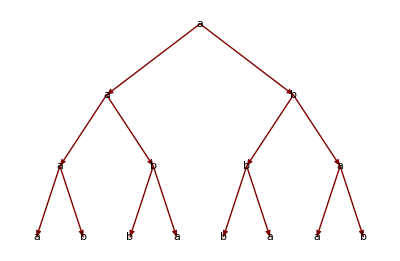

```mathematica
productions={"a"->"ab","b"->"ba"};
```

```mathematica
productions={"a"->"ab","b"->"ba"};
g[x_]:=StringReplace[x,productions]
```

```mathematica
NestList[g,"a",6] //TableForm
```

a
ab
abba
abbabaab
abbabaabbaababba
abbabaabbaababbabaababbaabbabaab
abbabaabbaababbabaababbaabbabaabbaababbaabbabaababbabaabbaababba

The above infinite string is also called 
Prouhet(1851)–Thue(1906)–Morse(1921) sequence

Fibonacci (endo)morphism:

```mathematica
productions={"a"->"ab","b"->"a"};
g[x_]:=StringReplace[x,productions]
```

```mathematica
(fibList=NestList[g,"a",8]) //TableForm
```

a
ab
aba
abaab
abaababa
abaababaabaab
abaababaabaababaababa
abaababaabaababaababaabaababaabaab
abaababaabaababaababaabaababaabaababaababaabaababaababa

```mathematica
StringLength /@ fibList
```

{1,2,3,5,8,13,21,34,55}

In 1983, Karhumäki showed that the above iteration gives an infinite word without 4-repetitions.

Karhumäki, Juhani, On cube-free ω-words generated by binary morphisms. Discrete Appl. Math. 5 (1983), no. 3, 279–297.

Juhani Karhumäki, Lapin Kansa 2.8.2020

https://lapinkansa.ap.richiefi.net/ef547dd3-f49f-4a02-83c2-ad6c4409e025/10

Some other aspects of words:
An L-system or Lindenmayer system is a parallel rewriting system

http://en.wikipedia.org/wiki/L-system

Prusinkiewicz
http://algorithmicbotany.org/papers/venation.sig2005.pdf

Wolfram
http://en.wikipedia.org/wiki/Rule_110

The Rule 110 cellular automaton (often simply Rule 110) 
is an elementary cellular automaton with the following rule table:

```mathematica
CellularAutomaton[110,{0,0,0,0,1,0,0,0,0},1]
```

(0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0)

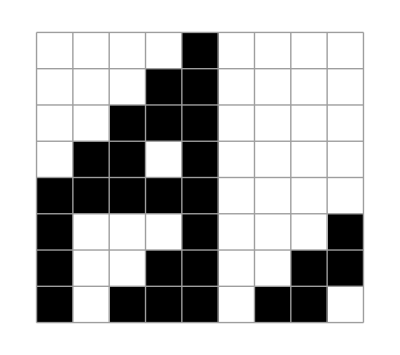

```mathematica
ArrayPlot[CellularAutomaton[110,{0,0,0,0,1,0,0,0,0},7],Mesh->All]
```

Run for 50 steps from a single 1 on a background of 0s:

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},50]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[110,{{1},0},300]]
```

-Graphics-

Rule 110 is arguably the simplest known Turing complete system.

Around 2000, Matthew Cook published a proof of a 1985 conjecture by Stephen Wolfram by proving that Rule 110 is Turing complete, i.e., capable of universal computation.

The original emulation of a Turing machine contained an exponential time overhead due to the encoding of the Turing machine's tape using a unary numeral system. Neary and Woods (2006) modified the construction to use only a polynomial overhead.

Below is an image showing the first two structures passing through each other without interacting (left), and interacting to form the third structure (right).

◀     |     ▶

∃ square-free (2-free) infinite strings over {a, b, c}:

```mathematica
productions=
{"a"->"abc","b"->"ac","c"-> "b"};
```

```mathematica
NestList[g,"a",6] //TableForm
```

a
abc
abcacb
abcacbabcbac
abcacbabcbacabcacbacabcb
abcacbabcbacabcacbacabcbabcacbabcbacabcbabcacbac
abcacbabcbacabcacbacabcbabcacbabcbacabcbabcacbacabcacbabcbacabcacbacabcbabcacbacabcacbabcbacabcb

## Are abelian squares avoidable in infinite words? Problem by Erdös from 1961 We solved the elusive 4-letter case in 1992 by introducing the following endomorphism g_85 over a four letter alphabet:

a → abcacdcbcdcadcdbdabacabadbabcbdbcbacbcdcacbabdabacadcbcdcacdbcbacbcdcacdcbdcdadbdcbca 
    = g(a)
b → bcdbdadcdadbadacabcbdbcbacbcdcacdcbdcdadbdcbcabcbdbadcdadbdacdcbdcdadbdadcadabacadcdb
    = g(b) = σ(g(a) )
c → cdacabadabacbabdbcdcacdcbdcdadbdadcadabacadcdbcdcacbadabacabdadcadabacabadbabcbdbadac
    = g(c) = σ(g(b) )
d → dabdbcbabcbdcbcacdadbdadcadabacabadbabcbdbadacdadbdcbabcbdbcabadbabcbdbcbacbcdcacbabd
    = g(d) = σ(g(c) )

Cyclic permutation  σ:  a → b, b → c, c → d, d → a

## A strange structure in g_85:

Coloured factors are cyclic permutations of each other

```mathematica
ga = "abcacdcbcdcadcdbdaba 
cabadbabcbdbcbacbcdcacbabd abacadcbcdcac
dbcbacbcdcacdcbdcdadbdcbca";

gb = "bcdbdadcdadbadacabcb 
dbcbacbcdcacdcbdcdadbdcbca bcbdbadcdadbd
acdcbdcdadbdadcadabacadcdb";

gc = "cdacabadabacbabdbcdc 
acdcbdcdadbdadcadabacadcdb cdcacbadabaca
bdadcadabacabadbabcbdbadac";

gd = "dabdbcbabcbdcbcacdad 
bdadcadabacabadbabcbdbadac dadbdcbabcbdb 
cabadbabcbdbcbacbcdcacbabd";
```

Grey factors: all letters occur equally many times

```mathematica
ga = "abc acdcbcdcadcdbdabacabadbabcbd 
bcbacbc dcacbabd abac adcb cdc acdb cbacbcdcacdcbdcd adbdcbca";
```

```mathematica
ga = "abc acdcbcdcadcdbdabacabadbabcbd 
bcbacbcdcacba bdabacadcbcd c acdb cbacbcdcacdcbdcd adbdcbca";
```

## (g_98)^2(a) with the complement {b,d} letters:

◀     |     ▶

### Can abelian squares be avoided in the three letter case (allowing only shortest possible repetition)? THIS PROBLEM IS STILL OPEN! IT CAN BE VERY HARD TO SOLVE!

Some experiments for the three letter case avoiding abelian squares except for the shortest possible one letter repetition xx and xxx for a letter.

```mathematica
StringReplace[g85["a"],{"d"→"."}]
StringReplace[g85["a"],{"a"→"aaa","b"→"bbb","c"→"ccc","d"→"..."}]
```

```mathematica
"abcac.cbc.ca.c.b.abacaba.babcb.bcbacbc.cacbab.abaca.cbc.cac.bcbacbc.cac.cb.c.a.b.cbca"
```

```mathematica
"aaabbbcccaaaccc...cccbbbccc...cccaaa...ccc...bbb...aaabbbaaacccaaabbbaaa...bbbaaabbbcccbbb...bbbcccbbbaaacccbbbccc...cccaaacccbbbaaabbb...aaabbbaaacccaaa...cccbbbccc...cccaaaccc...bbbcccbbbaaacccbbbccc...cccaaaccc...cccbbb...ccc...aaa...bbb...cccbbbcccaaa"
```

## Hypohelix structures in DNA (RNA)

To which extend we can avoid hypohelix structures in DNA? 
Problem posed by Jean Cognet (cognet@ccr.jussieu.fr, 
CNRS / BioMoCeti) in 2006.

```mathematica
⟶ ...A T C G T T T C G A T...
⟵ ...T A G C A A A G C A T ...
```

Loop:     5'  →  . . .  A   T  C   G  T 
	                    |    |    |    |       T
	  3'  →  . . .  T   A  G   C  T

Nature | Vol 447 | 21 June 2007 | pages 932 - 940
Expandable DNA repeats and human disease
Sergei M. Mirikin

Emäkset: (A) adeniini, (T) tymiini, (G) guaniini ja (C) sytosiini.
RNA:n emäsosat: (T) tymiinin tilalla on (U) urasiili.

Tripletti (kodoni)

C.J. Michel et al. / Theoretical Computer Science 401 (2008) 17–26
A relation between trinucleotide comma-free codes and trinucleotide
circular codes
Christian J. Michel, Giuseppe Pirillo, Mario A. Pirillo

## Walks in the diamond lattice

Aminohappo = typpipitoinen orgaaninen yhdiste, proteiinien rakenneosa. Luonnossa esiintyy 20 erilaista aminohappoa

Deoksiriboosi = viisi hiiliatomia sisältävä sokerimolekyyli, DNA:n nukleotidien yksi rakennusosa. DNA = deoksiribonukleiinihappo, eliön perinnöllistä tietoa säilyttävä, nukleotideista koostuva yhdiste.
Kodoni, tripletti = kolmen nukleotidin muodostama sarja, aminohappo

Lähetti - RNA = RNA - molekyyli, joka kuljettaa geenin perinnöllisen tiedon ribosomeille proteiinisynteesin malliksi. Nukleotidi = nukleiinihapon rakenneosa, jonka osina ovat sokeri, fosforihappotähde ja orgaaninen emäs. Proteiini = valkuaisaine, yhdestä tai useammasta aminohappoketjusta muodostuneita yhdisteitä.

## Quad Trees

Interctive demo:  
http://closure-library.googlecode.com/git/closure/goog/demos/quadtree.html

Quad trees can be used to visualise large sets of words over 4 letters at a glance. The directions for the letters are indicated below:

Dividing the squares further one can represent longer words.  All abelian square-free words of lengt 2 over 4 letters are shown below. Note the white corners representing the unfavourable words  aa, bb, cc, dd:

This is a guad tree showing all abelian square-free words of lengt 8 over 4 letters:

### Quad Tree Development with Sparse Arrays

```mathematica
Off[General::spell]
Off[General::spell1]
```

```mathematica
Clear[quadMatrix,markPosition,markPositionForWholeString,markLastPositionForWholeString];
quadMatrix[myString_String]:=SparseArray[{},{2^StringLength[myString],2^StringLength[myString]},RGBColor[1,1,1]];
quadMatrix[myStringLength_Integer]:=SparseArray[{},{2^myStringLength,2^myStringLength},RGBColor[1,1,1]];
markPosition[{"",{x_,y_}}]:={x,y};
markPosition[myString_String]:=markPosition[{myString,{2^StringLength[myString],2^StringLength[myString]}}];
markPosition[{myString_String,{x_,y_}}]:=Module[{firstLetter=StringTake[myString,{1}],sl=StringLength[myString],myNewStr=StringTake[myString,-(StringLength[myString]-1)]},Switch[firstLetter,"a",{myNewStr,{x,y}},"b",{myNewStr,{x-2^(sl-1),y}},"c",{myNewStr,{x-2^(sl-1),y-2^(sl-1)}},"d",{myNewStr,{x,y-2^(sl-1)}}]];
markPositionForWholeString[myString_String]:=NestWhileList[markPosition,myString,(#[[1]]=!="")&,{2,1}];
markLastPositionForWholeString[myString_String]:=NestWhile[markPosition,myString,(Length[Flatten[#]]=!=2)&,{2,1}];

(* NestWhileList[f, expr, test, {mmin, m}]does not start applying test until at least mmin results have been generated. At each step it then supplies as arguments to test as many recent results as 
possible,up to a maximum of m. 
NestWhile[f, expr, test, m, max, n]applies f an additional n times after test  fails,or max applications have already been performed.
*)
```

```mathematica
?markPosition
```

Global`markPosition

markPosition[{,{x_,y_}}]:={x,y}
 
markPosition[myString_String]:=markPosition[{myString,{2^StringLength[myString],2^StringLength[myString]}}]
 
markPosition[{myString_String,{x_,y_}}]:=Module[{firstLetter=StringTake[myString,{1}],sl=StringLength[myString],myNewStr=StringTake[myString,-(StringLength[myString]-1)]},Switch[firstLetter,
a,{myNewStr,{x,y}},
b,{myNewStr,{x-2^(sl-1),y}},
c,{myNewStr,{x-2^(sl-1),y-2^(sl-1)}},
d,{myNewStr,{x,y-2^(sl-1)}}]]

```mathematica
?markLastPositionForWholeString
```

Global`markLastPositionForWholeString

markLastPositionForWholeString[myString_String]:=NestWhile[markPosition,myString,Length[Flatten[#1]]=!=2&,{2,1}]

```mathematica
markPosition["abc"]
markPosition["bbc"]
markPosition["cbc"]
markPosition["dbc"]
markPosition[{"ba",{4,4}}]
markPosition["a"]
```

{bc,{8,8}}

{bc,{4,8}}

{bc,{4,4}}

{bc,{8,4}}

{a,{2,4}}

{,{2,2}}

```mathematica
markPositionForWholeString["abc"]
```

{abc,{bc,{8,8}},{c,{6,8}},{,{5,7}}}

```mathematica
markPositionForWholeString["aaa"]
```

```mathematica
markPositionForWholeString["aaa"]
markPositionForWholeString["bbb"]
markPositionForWholeString["ccc"]
markPositionForWholeString["ddd"]
```

{aaa,{aa,{8,8}},{a,{8,8}},{,{8,8}}}

{bbb,{bb,{4,8}},{b,{2,8}},{,{1,8}}}

{ccc,{cc,{4,4}},{c,{2,2}},{,{1,1}}}

{ddd,{dd,{8,4}},{d,{8,2}},{,{8,1}}}

```mathematica
markLastPositionForWholeString["aaaaaaaa"]
markLastPositionForWholeString["bbbbbbbb"]
markLastPositionForWholeString["cccccccc"]
markLastPositionForWholeString["dddddddd"]
```

{256,256}

{1,256}

{1,1}

{256,1}

```mathematica
markLastPositionForWholeString["abcdabcd"]
```

{154,205}

```mathematica
test=quadMatrix["abcd"]
```

SparseArray[<0>,{16,16},RGBColor[1,1,1]]

```mathematica
test[[12,12]]
```

RGBColor[1,1,1]

```mathematica
test//ByteCount
```

436

```mathematica
test=ReplacePart[test, RGBColor[1.00,0.28,0.71],{1,1}]
```

```mathematica
test//ByteCount
test[[1,1]]
test[[1,2]]
```

540

RGBColor[1.,0.28,0.71]

RGBColor[1,1,1]

```mathematica
myQuadMatr=quadMatrix["aaa"];
```

```mathematica
myQuadMatr//ByteCount
```

404

```mathematica
myQuadMatrNew=ReplacePart[myQuadMatr,RGBColor[1,0,0],{5,5}]
```

SparseArray[<1>,{8,8},RGBColor[1,1,1]]

```mathematica
Normal[myQuadMatrNew]
```

{{RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1]},{RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1]},{RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1]},{RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1]},{RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,0,0],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1]},{RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1]},{RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1]},{RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1],RGBColor[1,1,1]}}

```mathematica
Show[Graphics[RasterArray[myQuadMatrNew]],AspectRatio->1];
```

### 2nd Trial

Let's reduce the symmetries (permutations).

```mathematica
Clear[myAppend];
myAppend[x_List,k_:2]:=Flatten[Table[Append[#,i-1],{i,k}]&/@ x,1]
```

We can zoom into it:

```mathematica
reducedWords12pic=showQuadTree
```

⁃Graphics⁃

Zoom into it and compare with  reducedWords8pic:

reducedWords8pic  in turn was like this:

Finally, zoom 12 steps into one (first) point of  reducedWords8pic (in the upper right hand corner):

Observation:  points are isolated and scarse!  
Actually, we could have as well ended into a completely empty space.
Indeed, if we had extended the original prefix  abacabadabac  to the left as well we would have found that it is an unfavourable (forbidden) factor.

◀     |     ▶

# How the endomorphism g_85 was found?

## Search for the canditate image words of letters:

a →          A

b →          B

c →          C

d →          D

First, test all possible short prefix-suffix catenations. Then extend them in an a2f way:

⟵   As      pB   ⟶

⟵   As       pC   ⟶

⟵   As       pD   ⟶

Then, try to find an infix part for a fixed block length

pA     infix     As

in such a way that all the 2-block catenations are all a2f:

A                  B

A                   C

A                   D

Then, test the 3-block catenations:

A                  B                   A

A                  B                   C         

     ⋮

Then, the 4-block catenations ...

◀     |     ▶

◀     |     ▶

## A representation of g_85 in the form of DNA

Nature | Vol 447 | 21 June 2007 | pages 932 - 940
Expandable DNA repeats and human disease
Sergei M. Mirikin

The figure below is designed by Erik Jensen, University of California, Berkeley, in 2005.

-Graphics-

-Graphics-

## Something strange and nice from 2006 – insight of why these structures are so very rare,

⟵ … |(——)^w_6|(——)^w_4|(——)^w_2|(——————————)^(given word for the test)|(——)^w_1(|(——)^w_3|(——)^w_5|)_((|-–————––|)_s)_((|———|)_w) … ⟶

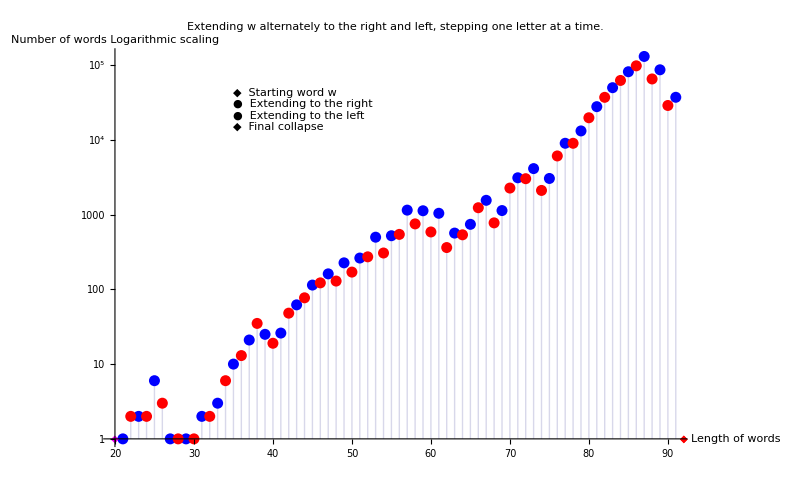
-Graphics-
      w = abacadbcbacbdcdacbab

The case of   abcdacbabdabacdacbcdad :

In the last illustration, the word w = "abcdacbabdabacdacbcdad" of length 22 turns out to be unfavourable in a monsterious way. The blue point, just before the final collapse, is at (117, 7866918). In spite of this, not a single extension is possible to the left (which would otherwise lead to the words of length 118).

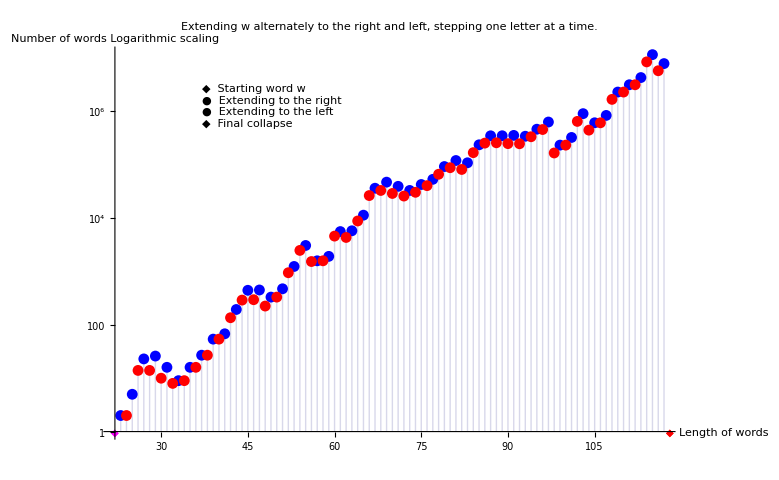
-Graphics-
      w = abcdacbabdabacdacbcdad

In a way, this explains why it has been so difficult to find abelian square-free endomorphisms over four letters. At present we know, for example, that over four letters about 60 % of the abelian square-free words of length 24 are indeed unfavourable (bad).

◀     |     ▶

## “New” results for words over 4 letters

## Image words of letters for g_109:

a →          A

b →          B

c →          C

d →          D

Below  only   a →          A             is given:

```mathematica
"abcd";
     "abcd";
     "abcd";
     "abdc";
     "abdc";
     "abdc";
     "adbc";
     "adbc";
     "adbc";
     "dabc";
     "dabc";
     "dabc";
```

__dabc_____cad__________,  ___dabc_____acd__________,  ___dabc______adc__________
__adbc_____cad__________,  ___adbc_____acd__________,  ___adbc______adc__________
__abdc_____cad__________,  ___abdc_____acd__________,  ___abdc______adc__________
__abcd_____cad__________,  ___abcd_____acd__________,  ___abcd______adc__________

```mathematica
myList={"abcacdcbcdcadcdb d badacdadbdcdbdabdbcbabcbdcb c bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb adbc badacdadbdcdbdabdbcbabcbdcb cad bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb abdc badacdadbdcdbdabdbcbabcbdcb cad bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb abcd badacdadbdcdbdabdbcbabcbdcb cad bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb dabc badacdadbdcdbdabdbcbabcbdcb acd bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb adbc badacdadbdcdbdabdbcbabcbdcb acd bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb abdc badacdadbdcdbdabdbcbabcbdcb acd bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb abcd badacdadbdcdbdabdbcbabcbdcb acd bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb dabc badacdadbdcdbdabdbcbabcbdcb adc bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb adbc badacdadbdcdbdabdbcbabcbdcb adc bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb abdc badacdadbdcdbdabdbcbabcbdcb adc bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca","abcacdcbcdcadcdb abcd badacdadbdcdbdabdbcbabcbdcb adc bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"};
```

```mathematica
outerList=Outer[List,{"d a b c","a d b c","a b d c","a b c d"},{"c a d","a c d","a d c"}]//Transpose//Flatten[#,1]&;
```

```mathematica
myList=Print[Style["abcacdcbcdcadcdb", FontFamily->"Helvetica",FontSize->10], Style[#[[1]], FontFamily->"Helvetica",FontSize->20],Style["badacdadbdcdbdabdbcbabcbdcb", FontFamily->"Helvetica",FontSize->10],Style[#[[2]], FontFamily->"Helvetica",FontSize->20],Style["bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca", FontFamily->"Helvetica",FontSize->10]]&  /@ outerList;
```

abcacdcbcdcadcdb dabc badacdadbdcdbdabdbcbabcbdcb cad bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb adbc badacdadbdcdbdabdbcbabcbdcb cad bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb abdc badacdadbdcdbdabdbcbabcbdcb cad bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb abcd badacdadbdcdbdabdbcbabcbdcb cad bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb dabc badacdadbdcdbdabdbcbabcbdcb acd bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb adbc badacdadbdcdbdabdbcbabcbdcb acd bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb abdc badacdadbdcdbdabdbcbabcbdcb acd bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb abcd badacdadbdcdbdabdbcbabcbdcb acd bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb dabc badacdadbdcdbdabdbcbabcbdcb adc bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb adbc badacdadbdcdbdabdbcbabcbdcb adc bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb abdc badacdadbdcdbdabdbcbabcbdcb adc bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

abcacdcbcdcadcdb abcd badacdadbdcdbdabdbcbabcbdcb adc bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca

```mathematica
myList=Infix[{Text[Style["abcacdcbcdcadcdb ", FontFamily->"Helvetica",FontSize->10]],Text[ Style[#[[1]], FontFamily->"Helvetica",FontSize->20]] ,Text[Style[" badacdadbdcdbdabdbcbabcbdcb ", FontFamily->"Helvetica",FontSize->10]],Text[Style[#[[2]], FontFamily->"Helvetica",FontSize->20]] ,Text[Style[" bdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca", FontFamily->"Helvetica",FontSize->10]]},""]&  /@ outerList;
```

```mathematica
Manipulate[myList[[n]],{{n,1,"a → A,A,...,A"},1,12,1}]
```

Define the (commutatively functional) substitution  σ_109: Σ_4^* → 2^(Σ_4^*)

a →  {A_1,A_2,...,A_12}
	b →  {B_1,B_2,..., B_12}
	c  →  {C_1,C_2,..., C_12}
	d →  {D_1,D_2,...,D_12}

(ψ(A)
ψ(B)
ψ(C)
ψ(D)) = (21 | 31 | 29 | 28
28 | 21 | 31 | 29
29 | 28 | 21 | 31
31 | 29 | 28 | 21),  whenever   A ∈ σ_109(a), B ∈ σ_109(b), 
						     C ∈ σ_109(c), D ∈ σ_109(d).

◀     |     ▶

## Proposition The substitution σ_109: Σ_4^* → 2^(Σ_4^*) defined above is abelian square-free.

There are 12·(4·12)^2 = 27648  different cases to test:

Proposition 1  (Carpi [3], 1993).  Given an integer  n ≥ 2,  two alphabets  Σ  and  Δ,  and a morphism  
h: Σ^* →  Δ^*,  let us denote by  G_h  the subgroup of  ℤ^Δ  generated by  ψ(h(Σ)).  Then, the morphism  h 
is abelian  nth power-free (a-n-free) provided that the following conditions are satisfied:
(i)	h(w) is a-n-free for every a-n-free word  w ∈ Σ^*  of length 2, 
(ii)	h  is commutatively injective, i.e., the set  ψ(h(Σ))  is linearly independent,
(iii)	for all  a_i ∈ Σ,  p_i ∈ PREF( h(a_i) ) – {h(a_i)}   (0 ≤ i ≤ n)  such that
 
	ψ(p_(j+1)) – 2 ψ(p_j) + ψ(p_(j-1))  ∈  G_h,		j = 1, 2 , ..., n–1,

there exist integers  δ_i ∈ {0,1}  such that

	ψ(p_(j+1)) – 2 ψ(p_j) + ψ(p_(j-1)) = 
		δ_(j+1)ψ(h(a_(j+1))) – 2 δ_j ψ(h(a_j) ) + δ_(j-1)ψ(h(a_(j-1))),   j = 1, 2 , ..., n–1.
		
If  Card(Σ) ≥ 6,  then an a-n-free morphism  h  always satisfies conditions (i)–(iii).   □

[3]  A. Carpi. On abelian power-free morphisms. Int. J. Algebra Comput., 3:151–167. World Sci. Publ. Company, 1993.
[4]  A. Carpi. On the number of abelian square-free words on four letters. Discrete Appl. Math., 81:155–167. Elsevier, 1998.
[5]  A. Carpi. On abelian squares and substitutions. Theor. Comp. Sci., 218:61–81. Elsevier, 1999.

◀     |     ▶

## How σ_109 was found?

Just by looking at the following results.

List of 201 a2f endomorphisms + one special case ( g_98 ):

"abcacdcbcdcadcdbdabacabadbabcbdbcbacbcdcacbabdabacadcbcdcacdbcbacbcdcacdcbdcdadbdcbca" ← g85a
"abcacdcbcdcadbdcbdbabcbdcacbabdbabcabdadcdadbdcbdbabdbcbacbcdbabdcdbdcacdbcbacbcdcacdcbdcdadbdcbca" ← g98a
"abcacdcbcdcadbdcadabacadcdbcbabcbdbadbdcbabcbdcdacdcbcacbcdbcbabdbabcabadcbcdcbadbabcbabdbcdbdadbdcbca"a21b31c27d23
"abcacdcbcdcadcbdadbcbdbacadacbcdbcbabdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a23b25c32d22
"abcacdcbcdcadcdbabdbacdcbdbabcbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a24b26c33d22
"abcacdcbcdcadcdbabdbacdcbdbabcbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a24b26c33d22
"abcacdcbcdcadcdbabdbcadcbdbabcbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a24b26c33d22
"abcacdcbcdcadcdbabdbcadcbdbabcbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a24b26c33d22
"abcacdcbcdcadbdcbdbabcbdcacbabdbabcabdadcdadbdcbdbabdbcdcadcbdbabdbcbacbcdcbcabadbcbacbcdcacdcbdcdadbdcbca"a20b31c29d26
"abcacdcbcdcadcdbdabdbcbabcbdcacbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a24b26c34d22
"abcacdcbcdcadcdbdabdbcbabcbdcacbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a24b26c34d22
"abcacdcbcdcadcdbabdbcdcabdbabcbadbacabadabcdcbcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b26c33d23
"abcacdcbcdcadcdbdabcbabdbacbcdcbacadabdbcbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b26c33d23
"abcacdcbcdcadcdbdadcabadbabcbdbcbacdcacbabdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b26c33d23
"abcacdcacbcdbcbadbdcbcacbcdbcbabdbabcacdbabcabadabacadcbcabcbdbabcacdcabcacdadbcdacabadabacbabdbcdbdadbdcbca"a28b31c29d20
"abcacdcacbcdbcbadbdcbcacbcdbcbabdbabcacdbabcabadabacadcbcabcbdbabcacdcacbacadbdcdacabadabacbabdbcdbdadbdcbca"a28b31c29d20
"abcacdcbcdcadbcbdbabdcadabdcacdcbdbacadbabcbabdbcdbdadbdcbcadcbdbabdbcbacbcdcbcabadbcbacbcdcacdcbdcdadbdcbca"a21b31c30d26
"abcacdcbcdcadbcbdbabdcadabdcacdcbdcabadbabcbabdbcdbdadbdcbcadcbdbabdbcbacbcdcbcabadbcbacbcdcacdcbdcdadbdcbca"a21b31c30d26
"abcacdcbcdcadbdcbdbadacadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b26c34d23
"abcacdcbcdcadbdcbdbadacbabdbabcbdcbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b26c34d23
"abcacdcbcdcadcbdadbcbdbacadbabcbdbcbacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b26c34d23
"abcacdcbcdcadcdbdabacabdcbdbabdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b26c34d23
"abcbdadcbcdcacdcbdadbdcbdacadabadcbdbabdbcbacbcdcadcdbdabdbcbdbadacbcdbdadbdcdacdcbcdcadabadacdadbdcdbdabdbca"a23b27c25d34
"abcacdcbcdcadcdbabcdbadacdadbdcdbdabdbcbabcbdcbacdbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbabcdbadacdadbdcdbdabdbcbabcbdcbadcbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbabcdbadacdadbdcdbdabdbcbabcbdcbcadbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbabdcbadacdadbdcdbdabdbcbabcbdcbacdbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbabdcbadacdadbdcdbdabdbcbabcbdcbadcbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbabdcbadacdadbdcdbdabdbcbabcbdcbcadbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbadacabadbdcbcabcbdbabdbcdbdacdcbcdcacbadbdcbcacbcdbcbabdbabcabadcbcdcbadbabcbabdbcdbdadbdcbca"a22b33c29d25
"abcacdcbcdcadcdbadbcbadacdadbdcdbdabdbcbabcbdcbacdbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbadbcbadacdadbdcdbdabdbcbabcbdcbadcbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbadbcbadacdadbdcdbdabdbcbabcbdcbcadbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbdabcbadacdadbdcdbdabdbcbabcbdcbacdbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbdabcbadacdadbdcdbdabdbcbabcbdcbadcbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadcdbdabcbadacdadbdcdbdabdbcbabcbdcbcadbdcdadcdbcbabcbdcbcacdcacbadabcbdcbcadbabcbabdbcdbdadbdcbca"a21b31c29d28
"abcacdcbcdcadbdcbdbabcbabdacbdcdacbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c34d23
"abcacdcbcdcadbdcbdbabcbabdacbdcdacbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c34d23
"abcacdcbcdcadbdcbdbadacabdbacbcdbcbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c34d23
"abcacdcbcdcadbdcbdbadacabdbacbcdbcbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c34d23
"abcacdcbcdcadcdbadbcbdabacadbcbdbabdcbcacdcacbabdabacadacabcacdcacbcdbabcabadbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b26c34d23
"abcacdcbcdcadcdbdabdbcbacadabdbcbabcbdcacbacadcbdabacadacabcacdcacbcdbabcabadbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b26c34d23
"abcacdcbcdcadbdcbdbadbdcbcacbcdbcbabdbabcabdadcacbcdcbcabcbdbcbabdabacbdbcabcdcadabacabadbabcbabdbcdbdadbdcbca"a24b35c28d23
"abcacdcbcdcadbdcbdbadbdcbcacbcdbcbabdbabcabdadcacbcdcbcabcbdbcbabdabacbdbcacbdcadabacabadbabcbabdbcdbdadbdcbca"a24b35c28d23
"abcacdcbcdcadbdcadabacbcdadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b26c35d23
"abcacdcbcdcadbdcbdbadacabcbdbabcabadacabcacdbdadbcbabcdcbcabadacabcacdcacbcdbcbabcbdcdabacbcdcacdcbdcdadbdcbca"a26b28c33d23
"abcacdcbcdcadbdcbdbadacabcbdbabcabadacabcacdbdadbcbabcdcbcabadacabcacdcacbcdbcbacdabdbcbacbcdcacdcbdcdadbdcbca"a26b28c33d23
"abcacdcbcdcadbdcbdbadcacbabdbabcabadacabcacdbdadbcbabcdcbcabadacabcacdcacbcdbcbabcbdcdabacbcdcacdcbdcdadbdcbca"a26b28c33d23
"abcacdcbcdcadbdcbdbadcacbabdbabcabadacabcacdbdadbcbabcdcbcabadacabcacdcacbcdbcbacdabdbcbacbcdcacdcbdcdadbdcbca"a26b28c33d23
"abcacdcbcdcadcbdabdbcbdbabcabadabacadcbdabacbabdbcdcacdcbcabadacabcacdcacbcdbcbabcbdcdabacbcdcacdcbdcdadbdcbca"a26b28c33d23
"abcacdcbcdcadcbdabdbcbdbabcacdcbabdabacabadacdadbcbabcdcbcabadacabcacdcacbcdbcbabcbdcdabacbcdcacdcbdcdadbdcbca"a26b28c33d23
"abcacdcbcdcadcbdabdbcbdbabcacdcbabdabacabadacdadbcbabcdcbcabadacabcacdcacbcdbcbacdabdbcbacbcdcacdcbdcdadbdcbca"a26b28c33d23
"abcacdcbcdcadcdbdabdbcbabcbdcbacadcbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c35d23
"abcacdcbcdcadcdbdabdbcbabcbdcbacadcbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c35d23
"abcacdcbcdcadcdbdabdbcbabcbdcbacdacbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c35d23
"abcacdcbcdcadcdbdabdbcbabcbdcbacdacbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c35d23
"abcacdcbcdcadcdbdabdbcbabcbdcbadcacbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c35d23
"abcacdcbcdcadcdbdabdbcbabcbdcbadcacbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c35d23
"abcacdcbcdcadcdbdabdbcbabdadcdbabcabadbcbacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c34d24
"abcacdcbcdcadcdbdabdbcbabdadcdbabcabadbcbacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c34d24
"abcacdcbcdcadbdcbdbadacabadbabcbdbcbacbcdcadabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadbdcbdbadacabadbabcbdbcbacbdcdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadbdcbdbadacadabacbabdbabcbdcbcacbcdbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadbdcbdbadbdcacbacadabacbabdbabcbdcbcabadbacdcbcabadacabcacdcacbcdbcbabdacdbcbacbcdcacdcbdcdadbdcbca"a26b29c33d23
"abcacdcbcdcadbdcbdbadbdcacbacadabacbabdbabcbdcbcabadbacdcbcabadacabcacdcacbcdbcbacdabdbcbacbcdcacdcbdcdadbdcbca"a26b29c33d23
"abcacdcbcdcadbdcbdbadbdcacbacadabacbabdbabcbdcbcabdabacdcbcabadacabcacdcacbcdbcbabdacdbcbacbcdcacdcbdcdadbdcbca"a26b29c33d23
"abcacdcbcdcadbdcbdbadbdcacbacadabacbabdbabcbdcbcabdabacdcbcabadacabcacdcacbcdbcbacdabdbcbacbcdcacdcbdcdadbdcbca"a26b29c33d23
"abcacdcbcdcadbdcbdbadbdcacbacadacabadbabcbdbcbacdbcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadbdcbdbadbdcadabacbabdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadbdcbdbadcacbabdbabcabadacabcdbdabcdcbcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadbdcbdbadcacbabdbabcabadacdadbcbabcdcbcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadcbdabdbcbdbadacabadacdcbcabcbdbcbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadcbdabdbcbdbadacadbabcbdbcbacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadcbdadbcbdbacadbabcbdbcbacbcdcadabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c35d24
"abcacdcbcdcadcbdadbcbdbacadbabcbdbcbacbdcdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b27c35d24
"abcacdcbcdcadcbdbadbdcacbdbabcbabdacabcbdcbcabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b28c35d23
"abcacdcbcdcadcbdbadbdcadabacabadbcbacbcdbcbacadacabcacdcbcabcbdbabcacdbdabacadcbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d23
"abcacdcbcdcadcdbabdbacdcbdbabcbabdacbcacdcabcbdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b28c35d23
"abcacdcbcdcadcdbabdbcadcbdbabcbabdacabcbdcbcabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b28c35d23
"abcacdcbcdcadcdbabdbcadcbdbabcbabdacbcacdcabcbdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b28c35d23
"abcacdcbcdcadcdbabdbcbdbadacabadacdcbcabcbdbcbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadcdbabdbcbdbadacadbabcbdbcbacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c34d24
"abcacdcbcdcadcdbabdbcdacbdbabcbabdacabcbdcbcabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b28c35d23
"abcacdcbcdcadcdbabdbcdcabdbabcbabdacabcbdcbcabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a25b28c35d23
"abcacdcbcdcadcdbdabacdabdbcbabcbdcacbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d23
"abcacdcbcdcadcdbdabacdabdbcbabcbdcacbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d23
"abcacdcbcdcadcdbdabdbcadabacabadbcbacbcdbcbacadacabcacdcbcabcbdbabcacdbdabacadcbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d23
"abcacdcbcdcadcdbdabdbcbabcbdcbacadacbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d23
"abcacdcbcdcadcdbdabdbcbabcbdcbacadacbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d23
"abcacdcbcdcadcdbdcdadbadacdcbcdacabadcdadbabcdbadacabacadcacbcacdcbdcdacbcacdcabcbdbacadbacbcdcacdcbdcdadbdcbca"a27b21c35d28
"abcacdcbcdcadcdbdcdadbadacdcbcdacabadcdadbacbdbadacabacadcacbcacdcbdcdacbcacdcabcbdbacadbacbcdcacdcbdcdadbdcbca"a27b21c35d28
"abcacdcbcdcadbdcadabdbcbabdacabcbdbcbacbcdcadabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadbdcadabdbcbabdacabcbdbcbacbdcdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadbdcadabdbcbacadbabcbdbcbacbcdcadabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadbdcadabdbcbacadbabcbdbcbacbdcdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadbdcbdbabcbabdabacadacabcadbcabcbdbcbacadacabcacdbabcacdcacbcdbcbabcbdbadcdbcbacbcdcacdcbdcdadbdcbca"a26b30c34d22
"abcacdcbcdcadbdcbdbabcbdcadabacbabdbabcbdcbcabdbabcadcdbdadbdcbdbabdbcbacbcdbabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a21b34c30d27
"abcacdcbcdcadbdcbdbadacdbacbabdbabcbdcbcacdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadbdcbdbadacdbacbabdbabcbdcbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadbdcbdbadcadbacbabdbabcbdcbcacdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadbdcbdbadcadbacbabdbabcbdcbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcbdabdbcbdbadacabdbcbabcbdcacbacadcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcbdabdbcbdbadacadabacbabdbcbacbcdcbcabadbacdcbcabadacabcacdcacbcdbdacabcbdbcbacbcdcacdcbdcdadbdcbca"a26b29c34d23
"abcacdcbcdcadcbdadbcbdabacadcbdbabdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcdbabdbcbdbadacabdbcbabcbdcacbacadcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcdbabdbcbdbadacadabacbabdbcbacbcdcbcabadbacdcbcabadacabcacdcacbcdbdacabcbdbcbacbcdcacdcbdcdadbdcbca"a26b29c34d23
"abcacdcbcdcadcdbadbcbdabacadcbdbabdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcdbdabacabdbcbabcbdcdacabcbdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c36d23
"abcacdcbcdcadcdbdabacabdbcbabcbdcdacabcbdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c36d23
"abcacdcbcdcadcdbdabcabdbacbcdbcbabdbabcabadcacbcdcadabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcdbdabcbadbacbcdbcbabdbabcabadcacbcdcadabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcdbdabcbdabacadcbdbabdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcdbdabcbdabacbcdbcbabdbabcabadcacbcdcadabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcdbdabdbcabadbdcbcabadbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcbcdcadcdbdabdbcdacabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c35d24
"abcacdcacbcdbcbabdbcdcadcdbdadbdcbdbabcbdcbcacbcdcadcdbcbabdbcdbdacabadcbcabcbdbcbacadacabadbabcbabdbcdbdadbdcbca"a23b34c30d26
"abcacdcbcdcadcdbdadbdcbdbabdbcbacbcdadbabcdabcacdcacbcdbcbadbdcbcacbcdbcbabdbabcabadcbcdcbadbabcbabdbcdbdadbdcbca"a22b35c30d26
"abcacdcbcdcadcdbdadbdcbdbabdbcbacbcdadbcbadabcacdcacbcdbcbadbdcbcacbcdbcbabdbabcabadcbcdcbadbabcbabdbcdbdadbdcbca"a22b35c30d26
"abcacdcbcdcadbcbdbadacabadbabcbabdbcdbdabcadacbcdcbabcbdcdadbdcbdbabdbcbacbcdbabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a22b33c31d27
"abcacdcbcdcadbcbdbadacabadbabcbabdbcdbdacbadacbcdcbabcbdcdadbdcbdbabdbcbacbcdbabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a22b33c31d27
"abcacdcbcdcadbcbdbadacabadbabcbabdbcdbdacdabacbcdcbabcbdcdadbdcbdbabdbcbacbcdbabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a22b33c31d27
"abcacdcbcdcadbdcbdbabcbabdacbcacdbdadcbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d24
"abcacdcbcdcadbdcbdbabcbabdacbcacdbdadcbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d24
"abcacdcbcdcadbdcbdbadacbcdacbabdacbcdbcbabdbabcabadacabcbdcbacadacabacdcbcacbcdbdacabcbdbcbacbcdcacdcbdcdadbdcbca"a26b30c34d23
"abcacdcbcdcadbdcbdbadacbdcacbabdacbcdbcbabdbabcabadacabcbdcbacadacabacdcbcacbcdbdacabcbdbcbacbcdcacdcbdcdadbdcbca"a26b30c34d23
"abcacdcbcdcadbdcbdbadbdcacbcadabacbcdbcbabdbabcabadacabcbdcbacadacabacdcbcacbcdbdacabcbdbcbacbcdcacdcbdcdadbdcbca"a26b30c34d23
"abcacdcbcdcadcbdabdbcbdbadacabadbabcbdcbcacdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c35d24
"abcacdcbcdcadcbdadbcbdabacabdbcbabcbdcdacbcadacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c35d24
"abcacdcbcdcadcbdadbcbdbacabdacdcbcabcbdbabcabadcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d24
"abcacdcbcdcadcbdadbcbdbacadabdbcbabcbdcbcacdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c36d24
"abcacdcbcdcadcbdadbcbdbcacbdcadabacabadbabcbdbcbacdbcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d24
"abcacdcbcdcadcbdbadbdcadabacbabdbabcbdcbcacdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c35d24
"abcacdcbcdcadcdbabcdbdadbdcdacdcbacadcdbdcdacdcbcacbcdbcabdabacbcdcbcacdacabacadabdbcbacadbacbcdcacdcbdcdadbdcbca"a25b24c36d28
"abcacdcbcdcadcdbabcdbdadbdcdacdcbacadcdbdcdacdcbcacbcdbcabdabacbcdcbcacdacabacadabdbcbacdabacbcdcacdcbdcdadbdcbca"a25b24c36d28
"abcacdcbcdcadcdbabcdbdadbdcdacdcbacadcdbdcdacdcbcacbcdbcbadabacbcdcbcacdacabacadabdbcbacadbacbcdcacdcbdcdadbdcbca"a25b24c36d28
"abcacdcbcdcadcdbabcdbdadbdcdacdcbacadcdbdcdacdcbcacbcdbcbadabacbcdcbcacdacabacadabdbcbacdabacbcdcacdcbdcdadbdcbca"a25b24c36d28
"abcacdcbcdcadcdbabdbcbdbadacabadbabcbdcbcacdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c35d24
"abcacdcbcdcadcdbadbcbdabacabdbcbabcbdcdacbcadacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c35d24
"abcacdcbcdcadcdbdabacbdbcbabcdbdabacbcdcabcadacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c35d24
"abcacdcbcdcadcdbdabcbdcbcabcbdabacabadacdbcbacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c37d23
"abcacdcbcdcadcdbdabcbdcbcabcbdabacabadacdbcbacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b27c37d23
"abcacdcbcdcadcdbdabdbcbabcbdcbadabacbcdcabcadacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c35d24
"abcacdcacbcdbcbadbdcbcacdcbdcdadcdbcbadcdbdadbdcbcabcbdbabdbcdbdadcdadbabcdcadcdbcacbcdcbacadabacbabdbcdbdadbdcbca"a22b30c31d31
"abcacdcbcdcadbdcadabdbcadcbcadacbadbabcbabdbcdbdacdcbcdcacbadbdcbcacbcdbcbabdbabcabadcbcdcbadbabcbabdbcdbdadbdcbca"a24b34c30d26
"abcacdcbcdcadbdcadabdbcdacbcadacbadbabcbabdbcdbdacdcbcdcacbadbdcbcacbcdbcbabdbabcabadcbcdcbadbabcbabdbcdbdadbdcbca"a24b34c30d26
"abcacdcbcdcadcdbdadbdcbcacdbdabdbcbdbabcabadbdcbcacbdcdacdcbcacbcdbcbabcbdbadcdbcbacbcdacabadbabcbabdbcdbdadbdcbca"a22b34c31d27
"abcacdcbcdcadcdbdadbdcbcacdbdabdbcbdbabcadabcbdbcacbdcdacdcbcacbcdbcbabcbdbadcdbcbacbcdacabadbabcbabdbcdbdadbdcbca"a22b34c31d27
"abcacdcbcdcadbdcbdbabcbabdabcadcdbcdcacbabdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadbdcbdbabcbabdabcadcdbcdcacbabdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadbdcbdbabcbabdacadbdacdcbcabcbdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadbdcbdbabcbabdacadbdacdcbcabcbdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadbdcbdbadacabdbcbabcbdcdacabcbdabacadacabcacdcbcabcbdbabcacdcacbacdabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadbdcbdbadacabdbcbabcbdcdacabcbdabacadacabcacdcbcabcbdbabcacdcacbcadabdbcdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadbdcbdbadacbcdbcbabdbabcadabcacdcbcabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadcbdadbcbdabacadabdbcbabcbdcbcacdacabcbdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcbdadbcbdabacadabdbcbabcbdcbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcbdadbcbdbacadabdbcbabcbdcbacdcabadcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcbdadbcbdbacadabdbcbabcbdcbcacdabadcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcbdadbcbdbacadabdbcbabcbdcbcadcabadcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcdbabcdbdadbdcdacdcbacadcdbdcdacdcbcacbcdbcbabdabacbcdcbcacdacabacadabdbcbacadbacbcdcacdcbdcdadbdcbca"a25b25c36d28
"abcacdcbcdcadcdbabcdbdadbdcdacdcbacadcdbdcdacdcbcacbcdbcbabdabacbcdcbcacdacabacadabdbcbacdabacbcdcacdcbdcdadbdcbca"a25b25c36d28
"abcacdcbcdcadcdbdabdbcabcdcabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadcdbdabdbcabcdcadabacbabdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcdbdabdbcabcdcbabdabacbabdcbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcdbdabdbcacbdcabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadcdbdabdbcacbdcadabacbabdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcdbdabdbcacbdcbabdabacbabdcbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcdbdabdbcacdbcabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadcdbdabdbcacdbcbabdbabcabadcbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcdbdabdbcacdbcbabdbabcabdacbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcdbdabdbcacdbcbabdbabcabdcabcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcdbdabdbcadcbcabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadcdbdabdbcbabdabacadabdcbdabcdcbcacbcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcdbdabdbcbabdabacadabdcbdbacdcbcacbcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcdbdabdbcbabdacdbdabacadcbcabcbdbabcadcbcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcdbdabdbcbacadabdbcbabcbdcbacdcabadcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcdbdabdbcbacadabdbcbabcbdcbcacdabadcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcdbdabdbcbacadabdbcbabcbdcbcadcabadcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcdbdabdbcbacdcabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcbcdcadcdbdabdbcbacdcbabdabacbabdcbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b27c36d24
"abcacdcbcdcadcdbdadcabadbabcbabdbcdbdabacdcbcacbcdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c35d25
"abcacdcbcdcadcdbdadcabcbdbcabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b28c36d24
"abcacdcacbcdbcbadbdcbcacbcdbcbabdbabcabadcbcacdcacbabdbabcabadcbcabadabacadcacbcacdcbdcdacabadabacbabdbcdbdadbdcbca"a30b32c32d21
"abcacdcacbcdbcbadbdcbcacbcdbcbabdbabcabdcabcacdcacbabdbabcabadcbcabadabacadcacbcacdcbdcdacabadabacbabdbcdbdadbdcbca"a30b32c32d21
"abcacdcacbcdbcbadbdcbcacbcdbcbabdbabcacdbabcabadabacadcacbabdcbcabcbdadbdcacbacadcacbdcdacabadabacbabdbcdbdadbdcbca"a30b32c31d22
"abcacdcacbcdbcbadbdcbcacbcdbcbabdbabcacdbabcabadabacadcbcdadbabcbadacabcbdcbcacdcacbacdbadacadabacbabdbcdbdadbdcbca"a30b32c31d22
"abcacdcacbcdbcbadbdcbcacbcdbcbabdbabcacdbabcabadabacadcbdcadbabcbadacabcbdcbcacdcacbacdbadacadabacbabdbcdbdadbdcbca"a30b32c31d22
"abcacdcbcdcadbdcadabacabadbdcabcdbcbabcbdbadbdcdacdcbcacbcdbadbdcbcacbcdbcbabdbabcabadcbcdcbadbabcbabdbcdbdadbdcbca"a24b35c30d26
"abcacdcbcdcadbdcadabdbcacdbcabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b28c36d24
"abcacdcbcdcadbdcadabdbcacdbcbabdbabcabadcbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a28b27c36d24
"abcacdcbcdcadbdcadabdbcacdbcbabdbabcabdacbcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a28b27c36d24
"abcacdcbcdcadbdcadabdbcacdbcbabdbabcabdcabcacdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a28b27c36d24
"abcacdcbcdcadbdcadabdbcadcbcabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b28c36d24
"abcacdcbcdcadbdcbdbadacbcdacabadbabcbdbcbacbcdcacbabdabacadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a27b28c36d24
"abcacdcbcdcadcbdadbcbdbacabdacdcbcabcbdbabcabadcdbabcabadacabcacdcacbcdbcbacadabcbabdcdacdbcbacbcdcacdcbdcdadbdcbca"a27b29c35d24
"abcacdcbcdcadcdbadacabadbcbadbdcbcacbcdbcbabdbabcabadacabcbdcbacadacabacdcbcacbcdbdacabcbdbcbacbcdcacdcbdcdadbdcbca"a27b30c35d23
"abcacdcbcdcadcdbdabacdabdbcbdbabcabadcacbcdcbcabcbdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b29c36d24
"abcacdcbcdcadcdbdabcadabdbcbdbabcabadcacbcdcbcabcbdbabcabadacabcacdcacbcdbcbacdcabadbdcacdbcbacbcdcacdcbdcdadbdcbca"a26b29c36d24
"abcacdcbcdcadcdbdabdbcabcdcbacadabacbcdbcbabdbabcabadacabcbdcbacadacabacdcbcacbcdbdacabcbdbcbacbcdcacdcbdcdadbdcbca"a27b30c35d23
"abcacdcbcdcadcdbdabdbcbacdcbacadabacbcdbcbabdbabcabadacabcbdcbacadacabacdcbcacbcdbdacabcbdbcbacbcdcacdcbdcdadbdcbca"a27b30c35d23
"abcacdcbcdcadcdbdadbdcbdbabcadabcacdadbdadcadabacadcacbdcdadcdbdacabdacdcbcdcacbacadacabadbcbacbcdcacdcbdcdadbdcbca"a29b22c33d31
"abcacdcbcdcadcdbdadbdcbdbabcadabcacdadbdadcadabacadcacbdcdadcdbdacbadacdcbcdcacbacadacabadbcbacbcdcacdcbdcdadbdcbca"a29b22c33d31

◀     |     ▶

## A new lower bound for the exponential growth of a-2-free words over 4 letters

```mathematica
V. Keränen, "A Powerful Abelian Square-Free Substitution Over 4 Letters," 
Theoretical Computer Science, 410(38–40), 2009 pp. 3893–3900. 
dx.doi.org/10.1016/j.tcs.2009.05.027.
```

The properties of  σ_109  lead to a considerably sharper lower bound for the exponential growth of  c_n,  i.e., of the number of a-2-free words over 4 letters of length  n.  We obtain that  c_n > β^-50 β^n  with  β = 12^(1/m) ≃ 1.02306.  Originally, the exponential growth of  c_n  was proved by Carpi, who showed that  c_n >  β^-t β^n  with  β = 2^(19/t) = 2^(19/(85^3– 85)) ≃ 1.000021,  where  t = 85^3– 85 is the modulus of his substitution constructed from  g_85.
	The explanation for the new lower bound is as follows. Let  m = 109,  β = 12^(1/m) ≃ 1.02306,  and an integer  n ≥ 50  be given. Note that in (1) we have  |p_16 w_4 u_27 w_3| = 50. Furthermore, let  q  be the quotient of  n – 50  by  m,  i.e.,  n – 50 = qm + r,  0 ≤ r < m.  There are at least  (β^m)^(q+1) = β^(qm+m)  a-2-free words of length  qm + 50,  which are prefixes of some of the (infinite) a-2-free words  X_1 X_2⋯ X_i⋯,  where  X_i ∈ σ_109(x_i), x_i ∈ Σ_4, for all  i ≥ 1.  Thus there are at least  β^(qm+m) = β^((n -50 - r )+ m) =  β^(m- r)β^(n -50) > β^(n -50) = β^-50 β^n  words of length  n ≥ 50  that are prefixes of an a-2-free word  X_1 X_2⋯ X_i  with  i > q. 
	The number of all a-2-free words over 4 letters up to the length 60 can be found in the Internet.

# The number of a-2-free words over 4 letters (counted up to length 60)

|w| | n_i | n_i/(n_(i-1))
  |   |  
1 | 4 |  
2 | 12 | 3
3 | 36 | 3
4 | 96 | 2.67
5 | 264 | 2.75
6 | 648 | 2.45
7 | 1584 | 2.44
8 | 3576 | 2.26
9 | 7872 | 2.20
10 | 15360 | 1.95
11 | 29184 | 1.90
12 | 51120 | 1.75
13 | 90384 | 1.77
14 | 158448 | 1.75
15 | 286296 | 1.81
16 | 509808 | 1.78
17 | 904296 | 1.77
18 | 1.56×10^6 | 1.72
19 | 2.64×10^6 | 1.70
20 | 4.27×10^6 | 1.62
21 | 6.78×10^6 | 1.59
22 | 10.3×10^6 | 1.52
23 | 15.4×10^6 | 1.50
24 | 22.3×10^6 | 1.45
25 | 31.6×10^6 | 1.41
26 | 45.8×10^6 | 1.45
27 | 65.9×10^6 | 1.44
28 | 94.1×10^6 | 1.43
29 | 135×10^6 | 1.44
30 | 194×10^6 | 1.43                         31 | 281×10^6 | 1.45
32 | 406×10^6 | 1.44
33 | 591×10^6 | 1.45
34 | 856×10^6 | 1.45
35 | 1.25×10^9 | 1.46
36 | 1.81×10^9 | 1.45
37 | 2.63×10^9 | 1.45
38 | 3.80×10^9 | 1.45
39 | 5.50×10^9 | 1.45
40 | 7.94×10^9 | 1.44
41 | 11.5×10^9 | 1.4432
42  | 16.5×10^9 | 1.4365
43 | 23.6×10^9 | 1.4365
44 | 33.8×10^9 | 1.4296
45 | 48.3×10^9 | 1.4290
46 | 68.7×10^9 | 1.4224
47 | 97.7×10^9 | 1.4219
48 | 138×10^9 | 1.4159
49 | 196×10^9 | 1.4156
50 | 276×10^9 | 1.4105
51 | 390×10^9 | 1.4110
52 | 548×10^9 | 1.4066
53 | 771×10^9 | 1.4072
54 | 1.08×10^12 | 1.4031
55 | 1.52×10^12 | 1.4036
56 | 2.13×10^12 | 1.3997
57 | 2 .98×10^12 | 1.4001
58 | 4.16×10^12 | 1.3964
59 | 5.81×10^12 | 1.3968
60 | 8.09×10^12  | 1.3934

# The number of a-2-free words over 3 letters when xx and xxx are allowed

|w|    n_i 		        n_i/(n_(i-1))
1        3    
2        9                              3
3        27                            3
4        66                            2.44444
5        162                          2.45455
6        360                          2.22222
7        786                          2.18333
8        1572                        2
9        3114                        1.98092
10      5850                        1.87861
11      11070                      1.89231
12      20454                      1.8477
13      37698                      1.84306
14      67746                      1.79707
15      120084                    1.77256
16      207354                    1.72674
17      352710                    1.701
18      584730                    1.65782
19      958572                    1.63934
20      1534644                  1.60097
21      2442792                  1.59176
22      3820194                  1.56386
23      5963814                  1.56113
24      9172128                  1.53796
25      14111766                1.53855
26      21433746                1.51886
27      32548104                1.51854
28      48838248                1.50049
29      73374756                1.50240
30      109134090              1.48735
31      162502878              1.48902
32      239456694              1.47355
33      353018418              1.47425
34      515766912              1.46102
35      753738288              1.46114
36      1092152922            1.44898
37      1582937112            1.44937
38      2277322608            1.43867
39      3277969326            1.43937
40      4688961678            1.43045
41      6711975342            1.43144
42      9556710960            1.42383
43      13620872190          1.42527
44      19315286742          1.41807
45      27411843570          1.41918
46      38697836448          1.41172
47      54640565430          1.41198
48      76738660518          1.40443
49      107744295960        1.40404
50      150468909474        1.39654
51      209997309000        1.39562
52      291517053024        1.38819
53      404311374036        1.38692
54      557861853108        1.37978
55      769001094162        1.37848
56      1054807891746      1.37166
57      1445567846316      1.37046
58      1971779324736      1.36402
59      2687391085356      1.36293
60      3646641094272      1.35694
61      4945189419510      1.35609
62      6678795097830      1.35056
63      9016561718934      1.35003
64      12127588393038    1.34503
65      16310079690648    1.34487
66      21863562240876    1.34049
67      29312761952346    1.34071
68      39186055535052    1.33683
69      52406748457434    1.33738
70      69909193375806    1.33397

◀     |     ▶

◀     |     ▶

# Equations, Intergers, Binary Component Vectors, Cumulative Vectors. Three letter case.

## Construct all aa2f words on 3 letters of a given length n using systems of linear Diophantine equations (or inequalities) build from conditions regarding certain factors of string of unknown symbols x_1x_2⋯x_n.

(□ | □ | □ | □ | - | - | + | +
□ | □ | - | - | - | + | + | +
- | - | - | - | + | + | + | +
□ | □ | □ | - | - | + | + | □
□ | - | - | - | + | + | + | □
□ | □ | - | - | + | + | □ | □
- | - | - | + | + | + | □ | □
□ | - | - | + | + | □ | □ | □
- | - | + | + | □ | □ | □ | □)

Some experiments

```mathematica
Solve[{{xr2,yr2,zr2}-{xl2,yl2,zl2}=={2,-1,-1},{xr3,yr3,zr3}-{xl3,yl3,zl3}=={2,1,-3},{xr4,yr4,zr4}-{xl4,yl4,zl4}=={0,1,-1},xr2+yr2+zr2==2,xl2+yl2+zl2==2,xr3+yr3+zr3==3,xl3+yl3+zl3==3,xr4+yr4+zr4==4,xl4+yl4+zl4==4,xr2≥0,yr2≥0,zr2≥0,xl2≥0,yl2≥0,zl2≥0,xr3≥0,yr3≥0,zr3≥0,xl3≥0,yl3≥0,zl3≥0,xr4≥0,yr4≥0,zr4≥0,xl4≥0,yl4≥0,zl4≥0},{xr2,yr2,zr2,xl2,yl2,zl2,xr3,yr3,zr3,xl3,yl3,zl3,xr4,yr4,zr4,xl4,yl4,zl4},Integers]
```

{{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→0,yr4→1,zr4→3,xl4→0,yl4→0,zl4→4},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→0,yr4→2,zr4→2,xl4→0,yl4→1,zl4→3},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→0,yr4→3,zr4→1,xl4→0,yl4→2,zl4→2},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→0,yr4→4,zr4→0,xl4→0,yl4→3,zl4→1},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→1,yr4→1,zr4→2,xl4→1,yl4→0,zl4→3},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→1,yr4→2,zr4→1,xl4→1,yl4→1,zl4→2},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→1,yr4→3,zr4→0,xl4→1,yl4→2,zl4→1},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→2,yr4→1,zr4→1,xl4→2,yl4→0,zl4→2},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→2,yr4→2,zr4→0,xl4→2,yl4→1,zl4→1},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→3,yr4→1,zr4→0,xl4→3,yl4→0,zl4→1}}

```mathematica
Solve[{{xr2,yr2,zr2}-{xl2,yl2,zl2}=={2,-1,-1},{xr3,yr3,zr3}-{xl3,yl3,zl3}=={2,1,-3},{xr4,yr4,zr4}-{xl4,yl4,zl4}=={0,1,-1},xr2+yr2+zr2==2,xl2+yl2+zl2==2,xr3+yr3+zr3==3,xl3+yl3+zl3==3,xr4+yr4+zr4==4,xl4+yl4+zl4==4,xr2≥0,yr2≥0,zr2≥0,xl2≥0,yl2≥0,zl2≥0,xr3≥0,yr3≥0,zr3≥0,xl3≥0,yl3≥0,zl3≥0,xr4≥0,yr4≥0,zr4≥0,xl4≥0,yl4≥0||zl4≥0},{xr2,yr2,zr2,xl2,yl2,zl2,xr3,yr3,zr3,xl3,yl3,zl3,xr4,yr4,zr4,xl4,yl4,zl4},Integers]//Timing
```

{0.03125,{{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→0,yr4→0,zr4→4,xl4→0,yl4→-1,zl4→5},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→1,yr4→0,zr4→3,xl4→1,yl4→-1,zl4→4},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→2,yr4→0,zr4→2,xl4→2,yl4→-1,zl4→3},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→3,yr4→0,zr4→1,xl4→3,yl4→-1,zl4→2},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→4,yr4→0,zr4→0,xl4→4,yl4→-1,zl4→1},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→0,yr4→1,zr4→3,xl4→0,yl4→0,zl4→4},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→0,yr4→2,zr4→2,xl4→0,yl4→1,zl4→3},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→0,yr4→3,zr4→1,xl4→0,yl4→2,zl4→2},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→0,yr4→4,zr4→0,xl4→0,yl4→3,zl4→1},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→1,yr4→1,zr4→2,xl4→1,yl4→0,zl4→3},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→1,yr4→2,zr4→1,xl4→1,yl4→1,zl4→2},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→1,yr4→3,zr4→0,xl4→1,yl4→2,zl4→1},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→2,yr4→1,zr4→1,xl4→2,yl4→0,zl4→2},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→2,yr4→2,zr4→0,xl4→2,yl4→1,zl4→1},{xr2→2,yr2→0,zr2→0,xl2→0,yl2→1,zl2→1,xr3→2,yr3→1,zr3→0,xl3→0,yl3→0,zl3→3,xr4→3,yr4→1,zr4→0,xl4→3,yl4→0,zl4→1}}}

```mathematica
Solve[{{xr2,yr2,zr2}-{xl2,yl2,zl2}=={0,0,0}∨{xr3,yr3,zr3}-{xl3,yl3,zl3}=={0,0,0}∨{xr4,yr4,zr4}-{xl4,yl4,zl4}=={0,0,0},xr2+yr2+zr2==2,xl2+yl2+zl2==2,xr3+yr3+zr3==3,xl3+yl3+zl3==3,xr4+yr4+zr4==4,xl4+yl4+zl4==4,xr2≥0,yr2≥0,zr2≥0,xl2≥0,yl2≥0,zl2≥0,xr3≥0,yr3≥0,zr3≥0,xl3≥0,yl3≥0,zl3≥0,xr4≥0,yr4≥0,zr4≥0,xl4≥0,yl4≥0,zl4≥0},{xr2,yr2,zr2,xl2,yl2,zl2,xr3,yr3,zr3,xl3,yl3,zl3,xr4,yr4,zr4,xl4,yl4,zl4},Integers]//Timing
```

```mathematica
{{{16.734375`7.244209410127593,{{xr2->0,yr2->0,zr2->2,xl2->0,yl2->0,zl2->2,xr3->0,yr3->0,zr3->3,xl3->0,yl3->1,zl3->2,xr4->0,yr4->0,zr4->4,xl4->0,yl4->1,zl4->3},{xr2->0,yr2->0,zr2->2,xl2->0,yl2->0,zl2->2,xr3->0,yr3->0,zr3->3,xl3->0,yl3->1,zl3->2,xr4->0,yr4->0,zr4->4,xl4->0,yl4->2,zl4->2},{xr2->0,yr2->0,zr2->2,xl2->0,yl2->0,zl2->2,xr3->0,yr3->0,zr3->3,xl3->0,yl3->1,zl3->2,xr4->0,yr4->0,zr4->4,xl4->0,yl4->3,zl4->1},{xr2->0,yr2->0,zr2->2,xl2->0,yl2->0,zl2->2,xr3->0,yr3->0,zr3->3,xl3->0,yl3->1,zl3->2,xr4->0,yr4->0,zr4->4,xl4->0,yl4->4,zl4->0},{xr2->0,yr2->0,zr2->2,xl2->0,yl2->0,zl2->2,xr3->0,yr3->0,zr3->3,xl3->0,yl3->1,zl3->2,xr4->0,yr4->0,zr4->4,xl4->1,yl4->0,zl4->3},{xr2->0,yr2->0,zr2->2,xl2->0,yl2->0,zl2->2,xr3->0,yr3->0,zr3->3,xl3->0,yl3->1,zl3->2,xr4->0,yr4->0,zr4->4,xl4->1,yl4->1,zl4->2},242989,{xr2->2,yr2->0,zr2->0,xl2->2,yl2->0,zl2->0,xr3->3,yr3->0,zr3->0,xl3->3,yl3->0,zl3->0,xr4->2,yr4->1,zr4->1,xl4->2,yl4->1,zl4->1},{xr2->2,yr2->0,zr2->0,xl2->2,yl2->0,zl2->0,xr3->3,yr3->0,zr3->0,xl3->3,yl3->0,zl3->0,xr4->2,yr4->2,zr4->0,xl4->2,yl4->2,zl4->0},{xr2->2,yr2->0,zr2->0,xl2->2,yl2->0,zl2->0,xr3->3,yr3->0,zr3->0,xl3->3,yl3->0,zl3->0,xr4->3,yr4->0,zr4->1,xl4->3,yl4->0,zl4->1},{xr2->2,yr2->0,zr2->0,xl2->2,yl2->0,zl2->0,xr3->3,yr3->0,zr3->0,xl3->3,yl3->0,zl3->0,xr4->3,yr4->1,zr4->0,xl4->3,yl4->1,zl4->0},{xr2->2,yr2->0,zr2->0,xl2->2,yl2->0,zl2->0,xr3->3,yr3->0,zr3->0,xl3->3,yl3->0,zl3->0,xr4->4,yr4->0,zr4->0,xl4->4,yl4->0,zl4->0}}}}, {{{, , , , }}}}
```

```mathematica
Solve[{{xr2,yr2,zr2}-{xl2,yl2,zl2}≠{0,0,0}∧{xr3,yr3,zr3}-{xl3,yl3,zl3}≠{0,0,0}∧{xr4,yr4,zr4}-{xl4,yl4,zl4}≠{0,0,0},xr2+yr2+zr2==2,xl2+yl2+zl2==2,xr3+yr3+zr3==3,xl3+yl3+zl3==3,xr4+yr4+zr4==4,xl4+yl4+zl4==4,xr2≥0,yr2≥0,zr2≥0,xl2≥0,yl2≥0,zl2≥0,xr3≥0,yr3≥0,zr3≥0,xl3≥0,yl3≥0,zl3≥0,xr4≥0,yr4≥0,zr4≥0,xl4≥0,yl4≥0,zl4≥0},{xr2,yr2,zr2,xl2,yl2,zl2,xr3,yr3,zr3,xl3,yl3,zl3,xr4,yr4,zr4,xl4,yl4,zl4},Integers]//Timing
```

{1.54688,{{xr2→0,yr2→0,zr2→2,xl2→1,yl2→1,zl2→0,xr3→0,yr3→0,zr3→3,xl3→1,yl3→1,zl3→1,xr4→0,yr4→0,zr4→4,xl4→1,yl4→1,zl4→2},16198,{1}}}
 |  |  |  |

Possible vector representations

```mathematica
{({{a1}, {b1}, {c1}}),({{a2}, {b2}, {c2}}),({{a3}, {b3}, {c3}}),({{a4}, {b4}, {c4}}),({{a5}, {b5}, {c5}}),({{a6}, {b6}, {c6}}),({{a7}, {b7}, {c7}}),({{a8}, {b8}, {c8}})}
{({{a1}, {b1}}),({{a2}, {b2}}),({{a3}, {b3}}),({{a4}, {b4}}),({{a5}, {b5}}),({{a6}, {b6}}),({{a7}, {b7}}),({{a8}, {b8}})}
{{a1,b1},{a2,b2},{a3,b3},{a4,b4},{a5,b5},{a6,b6},{a7,b7},{a8,b8}}
```

Same factors in different orders

```mathematica
({{□, □, □, □, -, -, +, +}, {□, □, □, -, -, +, +, □}, {□, □, -, -, +, +, □, □}, {□, -, -, +, +, □, □, □}, {-, -, +, +, □, □, □, □}, {□, □, -, -, -, +, +, +}, {□, -, -, -, +, +, +, □}, {-, -, -, +, +, +, □, □}, {-, -, -, -, +, +, +, +}})({{□, □, □, □, -, -, +, +}, {□, □, -, -, -, +, +, +}, {-, -, -, -, +, +, +, +}, {□, □, □, -, -, +, +, □}, {□, -, -, -, +, +, +, □}, {□, □, -, -, +, +, □, □}, {-, -, -, +, +, +, □, □}, {□, -, -, +, +, □, □, □}, {-, -, +, +, □, □, □, □}})
```

More experiments

```mathematica
Clear[a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8];
Solve[{-{a5,b5}-{a6,b6}+{a7,b7}+{a8,b8}≠{0,0}∧-{a3,b3}-{a4,b4}-{a5,b5}+{a6,b6}+{a7,b7}+{a8,b8}≠{0,0}∧-{a1,b1}-{a2,b2}-{a3,b3}-{a4,b4}+{a5,b5}+{a6,b6}+{a7,b7}+{a8,b8}≠{0,0}∧-{a4,b4}-{a5,b5}+{a6,b6}+{a7,b7}≠{0,0}∧-{a2,b2}-{a3,b3}-{a4,b4}+{a5,b5}+{a6,b6}+{a7,b7}≠{0,0}∧-{a3,b3}-{a4,b4}+{a5,b5}+{a6,b6}≠{0,0}∧-{a1,b1}-{a2,b2}-{a3,b3}+{a4,b4}+{a5,b5}+{a6,b6}≠{0,0}∧-{a2,b2}-{a3,b3}+{a4,b4}+{a5,b5}≠{0,0}∧-{a1,b1}-{a2,b2}+{a3,b3}+{a4,b4}≠{0,0},a1==0∨a1==1,b1==0∨b1==1,a2==0∨a2==1,b2==0∨b2==1,a3==0∨a3==1,b3==0∨b3==1,a4==0∨a4==1,b4==0∨b4==1,a5==0∨a5==1,b5==0∨b5==1,a6==0∨a6==1,b6==0∨b6==1,a7==0∨a7==1,b7==0∨b7==1,a8==0∨a8==1,b8==0∨b8==1},{a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8},Integers]//Timing
```

{10468.125,{{a1→0,b1→0,a2→0,b2→0,a3→0,b3→0,a4→1,b4→1,a5→1,b5→1,a6→1,b6→1,a7→0,b7→0,a8→0,b8→0},{a1→0,b1→0,a2→0,b2→0,a3→0,b3→1,a4→1,b4→1,a5→1,b5→1,a6→1,b6→0,a7→0,b7→0,a8→0,b8→0},{a1→0,b1→0,a2→0,b2→0,a3→1,b3→0,a4→1,b4→1,a5→1,b5→1,a6→0,b6→1,a7→0,b7→0,a8→0,b8→0},{a1→0,b1→0,a2→0,b2→0,a3→1,b3→1,a4→1,b4→1,a5→1,b5→1,a6→0,b6→0,a7→0,b7→0,a8→0,b8→0},{a1→0,b1→0,a2→0,b2→1,a3→0,b3→1,a4→1,b4→1,a5→1,b5→0,a6→1,b6→0,a7→0,b7→0,a8→0,b8→1},{a1→0,b1→0,a2→0,b2→1,a3→1,b3→1,a4→1,b4→1,a5→1,b5→0,a6→0,b6→0,a7→0,b7→0,a8→0,b8→1},{a1→0,b1→0,a2→1,b2→0,a3→1,b3→0,a4→1,b4→1,a5→0,b5→1,a6→0,b6→1,a7→0,b7→0,a8→1,b8→0},{a1→0,b1→0,a2→1,b2→0,a3→1,b3→1,a4→1,b4→1,a5→0,b5→1,a6→0,b6→0,a7→0,b7→0,a8→1,b8→0},{a1→0,b1→0,a2→1,b2→1,a3→1,b3→1,a4→1,b4→1,a5→0,b5→0,a6→0,b6→0,a7→0,b7→0,a8→1,b8→1},{a1→0,b1→1,a2→0,b2→0,a3→0,b3→0,a4→1,b4→0,a5→1,b5→1,a6→1,b6→1,a7→0,b7→1,a8→0,b8→0},{a1→0,b1→1,a2→0,b2→0,a3→1,b3→0,a4→1,b4→0,a5→1,b5→1,a6→0,b6→1,a7→0,b7→1,a8→0,b8→0},{a1→0,b1→1,a2→0,b2→1,a3→0,b3→0,a4→1,b4→0,a5→1,b5→0,a6→1,b6→1,a7→0,b7→1,a8→0,b8→1},{a1→0,b1→1,a2→0,b2→1,a3→0,b3→1,a4→1,b4→0,a5→1,b5→0,a6→1,b6→0,a7→0,b7→1,a8→0,b8→1},{a1→0,b1→1,a2→0,b2→1,a3→1,b3→0,a4→1,b4→0,a5→1,b5→0,a6→0,b6→1,a7→0,b7→1,a8→0,b8→1},{a1→0,b1→1,a2→0,b2→1,a3→1,b3→1,a4→1,b4→0,a5→1,b5→0,a6→0,b6→0,a7→0,b7→1,a8→0,b8→1},{a1→0,b1→1,a2→1,b2→0,a3→1,b3→0,a4→1,b4→0,a5→0,b5→1,a6→0,b6→1,a7→0,b7→1,a8→1,b8→0},{a1→0,b1→1,a2→1,b2→1,a3→1,b3→0,a4→1,b4→0,a5→0,b5→0,a6→0,b6→1,a7→0,b7→1,a8→1,b8→1},{a1→0,b1→1,a2→1,b2→1,a3→1,b3→1,a4→1,b4→0,a5→0,b5→0,a6→0,b6→0,a7→0,b7→1,a8→1,b8→1},{a1→1,b1→0,a2→0,b2→0,a3→0,b3→0,a4→0,b4→1,a5→1,b5→1,a6→1,b6→1,a7→1,b7→0,a8→0,b8→0},{a1→1,b1→0,a2→0,b2→0,a3→0,b3→1,a4→0,b4→1,a5→1,b5→1,a6→1,b6→0,a7→1,b7→0,a8→0,b8→0},{a1→1,b1→0,a2→0,b2→1,a3→0,b3→1,a4→0,b4→1,a5→1,b5→0,a6→1,b6→0,a7→1,b7→0,a8→0,b8→1},{a1→1,b1→0,a2→1,b2→0,a3→0,b3→0,a4→0,b4→1,a5→0,b5→1,a6→1,b6→1,a7→1,b7→0,a8→1,b8→0},{a1→1,b1→0,a2→1,b2→0,a3→0,b3→1,a4→0,b4→1,a5→0,b5→1,a6→1,b6→0,a7→1,b7→0,a8→1,b8→0},{a1→1,b1→0,a2→1,b2→0,a3→1,b3→0,a4→0,b4→1,a5→0,b5→1,a6→0,b6→1,a7→1,b7→0,a8→1,b8→0},{a1→1,b1→0,a2→1,b2→0,a3→1,b3→1,a4→0,b4→1,a5→0,b5→1,a6→0,b6→0,a7→1,b7→0,a8→1,b8→0},{a1→1,b1→0,a2→1,b2→1,a3→0,b3→1,a4→0,b4→1,a5→0,b5→0,a6→1,b6→0,a7→1,b7→0,a8→1,b8→1},{a1→1,b1→0,a2→1,b2→1,a3→1,b3→1,a4→0,b4→1,a5→0,b5→0,a6→0,b6→0,a7→1,b7→0,a8→1,b8→1},{a1→1,b1→1,a2→0,b2→0,a3→0,b3→0,a4→0,b4→0,a5→1,b5→1,a6→1,b6→1,a7→1,b7→1,a8→0,b8→0},{a1→1,b1→1,a2→0,b2→1,a3→0,b3→0,a4→0,b4→0,a5→1,b5→0,a6→1,b6→1,a7→1,b7→1,a8→0,b8→1},{a1→1,b1→1,a2→0,b2→1,a3→0,b3→1,a4→0,b4→0,a5→1,b5→0,a6→1,b6→0,a7→1,b7→1,a8→0,b8→1},{a1→1,b1→1,a2→1,b2→0,a3→0,b3→0,a4→0,b4→0,a5→0,b5→1,a6→1,b6→1,a7→1,b7→1,a8→1,b8→0},{a1→1,b1→1,a2→1,b2→0,a3→1,b3→0,a4→0,b4→0,a5→0,b5→1,a6→0,b6→1,a7→1,b7→1,a8→1,b8→0},{a1→1,b1→1,a2→1,b2→1,a3→0,b3→0,a4→0,b4→0,a5→0,b5→0,a6→1,b6→1,a7→1,b7→1,a8→1,b8→1},{a1→1,b1→1,a2→1,b2→1,a3→0,b3→1,a4→0,b4→0,a5→0,b5→0,a6→1,b6→0,a7→1,b7→1,a8→1,b8→1},{a1→1,b1→1,a2→1,b2→1,a3→1,b3→0,a4→0,b4→0,a5→0,b5→0,a6→0,b6→1,a7→1,b7→1,a8→1,b8→1},{a1→1,b1→1,a2→1,b2→1,a3→1,b3→1,a4→0,b4→0,a5→0,b5→0,a6→0,b6→0,a7→1,b7→1,a8→1,b8→1}}}

```mathematica
%805[[2]]//Length
```

36

```mathematica
NotebookSave[]
```

```mathematica
Clear[a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8];
Solve[{-{a5,b5}-{a6,b6}+{a7,b7}+{a8,b8}≠{0,0}∧-{a3,b3}-{a4,b4}-{a5,b5}+{a6,b6}+{a7,b7}+{a8,b8}≠{0,0}∧-{a1,b1}-{a2,b2}-{a3,b3}-{a4,b4}+{a5,b5}+{a6,b6}+{a7,b7}+{a8,b8}≠{0,0}∧-{a4,b4}-{a5,b5}+{a6,b6}+{a7,b7}≠{0,0}∧-{a2,b2}-{a3,b3}-{a4,b4}+{a5,b5}+{a6,b6}+{a7,b7}≠{0,0}∧-{a3,b3}-{a4,b4}+{a5,b5}+{a6,b6}≠{0,0}∧-{a1,b1}-{a2,b2}-{a3,b3}+{a4,b4}+{a5,b5}+{a6,b6}≠{0,0}∧-{a2,b2}-{a3,b3}+{a4,b4}+{a5,b5}≠{0,0}∧-{a1,b1}-{a2,b2}+{a3,b3}+{a4,b4}≠{0,0}},{a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8},Modulus->2]//Timing
```

Solve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{0.03125,{{}}}

```mathematica
Clear[a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8];
Reduce[{-{a5,b5}-{a6,b6}+{a7,b7}+{a8,b8}≠{0,0}∧-{a3,b3}-{a4,b4}-{a5,b5}+{a6,b6}+{a7,b7}+{a8,b8}≠{0,0}∧-{a1,b1}-{a2,b2}-{a3,b3}-{a4,b4}+{a5,b5}+{a6,b6}+{a7,b7}+{a8,b8}≠{0,0}∧-{a4,b4}-{a5,b5}+{a6,b6}+{a7,b7}≠{0,0}∧-{a2,b2}-{a3,b3}-{a4,b4}+{a5,b5}+{a6,b6}+{a7,b7}≠{0,0}∧-{a3,b3}-{a4,b4}+{a5,b5}+{a6,b6}≠{0,0}∧-{a1,b1}-{a2,b2}-{a3,b3}+{a4,b4}+{a5,b5}+{a6,b6}≠{0,0}∧-{a2,b2}-{a3,b3}+{a4,b4}+{a5,b5}≠{0,0}∧-{a1,b1}-{a2,b2}+{a3,b3}+{a4,b4}≠{0,0}},{a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8},Modulus->2]//Timing
```

{0.,a5+a6+a7+a8≠0&&b5+b6+b7+b8≠0&&a3+a4+a5+a6+a7+a8≠0&&b3+b4+b5+b6+b7+b8≠0&&a1+a2+a3+a4+a5+a6+a7+a8≠0&&b1+b2+b3+b4+b5+b6+b7+b8≠0&&a4+a5+a6+a7≠0&&b4+b5+b6+b7≠0&&a2+a3+a4+a5+a6+a7≠0&&b2+b3+b4+b5+b6+b7≠0&&a3+a4+a5+a6≠0&&b3+b4+b5+b6≠0&&a1+a2+a3+a4+a5+a6≠0&&b1+b2+b3+b4+b5+b6≠0&&a2+a3+a4+a5≠0&&b2+b3+b4+b5≠0&&a1+a2+a3+a4≠0&&b1+b2+b3+b4≠0}

## Traditional Linear Algebra works only with linear equations connected with AND!

## 1. A very long (5 day) computation using linear Diophantine inequalities and equations connected with AND & OR – later a million fold (!) speed-up is achieved:

```mathematica
Clear[a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8];Timing[Solve[{(-a5-a6+a7+a8≠0∨-b5-b6+b7+b8≠0)&&(-a3-a4-a5+a6+a7+a8≠0∨-b3-b4-b5+b6+b7+b8≠0)&&(-a1-a2-a3-a4+a5+a6+a7+a8≠0∨-b1-b2-b3-b4+b5+b6+b7+b8≠0)&&(-a4-a5+a6+a7≠0∨-b4-b5+b6+b7≠0)&&(-a2-a3-a4+a5+a6+a7≠0∨-b2-b3-b4+b5+b6+b7≠0)&&(-a3-a4+a5+a6≠0∨-b3-b4+b5+b6≠0)&&(-a1-a2-a3+a4+a5+a6≠0∨-b1-b2-b3+b4+b5+b6≠0)&& (-a2-a3+a4+a5≠0∨-b2-b3+b4+b5≠0)&&(-a1-a2+a3+a4≠0∨-b1-b2+b3+b4≠0),(a1==1&&b1==0)∨(a1==0&&b1==1)∨(a1==0&&b1==0),(a2==1&&b2==0)∨(a2==0&&b2==1)∨(a2==0&&b2==0), 
(a3==1&&b3==0)∨(a3==0&&b3==1)∨(a3==0&&b3==0),
(a4==1&&b4==0)∨(a4==0&&b4==1)∨(a4==0&&b4==0),
(a5==1&&b5==0)∨(a5==0&&b5==1)∨(a5==0&&b5==0),
(a6==1&&b6==0)∨(a6==0&&b6==1)∨(a6==0&&b6==0),
(a7==1&&b7==0)∨(a7==0&&b7==1)∨(a7==0&&b7==0),
(a8==1&&b8==0)∨(a8==0&&b8==1)∨(a8==0&&b8==0)},{a1,b1,a2,b2,a3,b3,a4,b4,a5 ,b5,a6,b6,a7,b7,a8,b8},Integers]]
```

{421872.15625,{{a1→0,b1→0,a2→0,b2→0,a3→0,b3→0,a4→0,b4→1,a5→0,b5→0,a6→0,b6→0,a7→0,b7→0,a8→1,b8→0},{a1→0,b1→0,a2→0,b2→0,a3→0,b3→0,a4→0,b4→1,a5→0,b5→0,a6→0,b6→0,a7→1,b7→0,a8→0,b8→0},1569,{a1→1,b1→0,a2→1,b2→0,a3→1,b3→0,a4→0,b4→1,a5→1,b5→0,a6→1,b6→0,a7→1,b7→0,a8→0,b8→0}}}
 |  |  |  |

```mathematica
%[[2]]//Length
```

1572

```mathematica
421872.16/3600 hours
```

117.187 hours

```mathematica
%821[[2]]//Length
```

1572

Exactly correct!

And sure, the computational time is downright hilarious!

```mathematica
a1b1a2b2a3b3a4b4a5b5a6b6a7b7a8b8=%821[[2]]
```

{{a1→0,b1→0,a2→0,b2→0,a3→0,b3→0,a4→0,b4→1,a5→0,b5→0,a6→0,b6→0,a7→0,b7→0,a8→1,b8→0},{a1→0,b1→0,a2→0,b2→0,a3→0,b3→0,a4→0,b4→1,a5→0,b5→0,a6→0,b6→0,a7→1,b7→0,a8→0,b8→0},{a1→0,b1→0,a2→0,b2→0,a3→0,b3→0,a4→0,b4→1,a5→0,b5→0,a6→0,b6→0,a7→1,b7→0,a8→0,b8→1},{a1→0,b1→0,a2→0,b2→0,a3→0,b3→0,a4→0,b4→1,a5→0,b5→0,a6→0,b6→0,a7→1,b7→0,a8→1,b8→0},1564,{a1→1,b1→0,a2→1,b2→0,a3→1,b3→0,a4→0,b4→1,a5→1,b5→0,a6→1,b6→0,a7→0,b7→0,a8→0,b8→0},{a1→1,b1→0,a2→1,b2→0,a3→1,b3→0,a4→0,b4→1,a5→1,b5→0,a6→1,b6→0,a7→0,b7→0,a8→0,b8→1},{a1→1,b1→0,a2→1,b2→0,a3→1,b3→0,a4→0,b4→1,a5→1,b5→0,a6→1,b6→0,a7→0,b7→0,a8→1,b8→0},{a1→1,b1→0,a2→1,b2→0,a3→1,b3→0,a4→0,b4→1,a5→1,b5→0,a6→1,b6→0,a7→1,b7→0,a8→0,b8→0}}
 |  |  |  |

## 2. Basically the same, but short (5 min) computation using equations and inequalities. Integers are used to represent vectors:

```mathematica
Clear[a1,a2,a3,a4,a5,a6,a7,a8];Timing[Solve[{(-a5-a6+a7+a8≠0)&&(-a3-a4-a5+a6+a7+a8≠0)&&(-a1-a2-a3-a4+a5+a6+a7+a8≠0)&&(-a4-a5+a6+a7≠0)&&(-a2-a3-a4+a5+a6+a7≠0)&&(-a3-a4+a5+a6≠0)&&(-a1-a2-a3+a4+a5+a6≠0)&& (-a2-a3+a4+a5≠0)&&(-a1-a2+a3+a4≠0),(a1==1)∨(a1==0)∨(a1==10),
(a2==1)∨(a2==0)∨(a2==10), 
(a3==1)∨(a3==0)∨(a3==10),
(a4==1)∨(a4==0)∨(a4==10),
(a5==1)∨(a5==0)∨(a5==10),
(a6==1)∨(a6==0)∨(a6==10),
(a7==1)∨(a7==0)∨(a7==10),
(a8==1)∨(a8==0)∨(a8==10)},{a1,a2,a3,a4,a5 ,a6,a7,a8},Integers]]
```

{333.172,{{a1→0,a2→0,a3→0,a4→1,a5→0,a6→0,a7→0,a8→10},{a1→0,a2→0,a3→0,a4→1,a5→0,a6→0,a7→10,a8→0},{a1→0,a2→0,a3→0,a4→1,a5→0,a6→0,a7→10,a8→1},1566,{a1→10,a2→10,a3→10,a4→1,a5→10,a6→10,a7→0,a8→1},{a1→10,a2→10,a3→10,a4→1,a5→10,a6→10,a7→0,a8→10},{a1→10,a2→10,a3→10,a4→1,a5→10,a6→10,a7→10,a8→0}}}
 |  |  |  |

```mathematica
%[[2]]//Length
```

1572

## 3. Computing the complement using equations connected with OR (in 39 s):

```mathematica
Clear[a1,a2,a3,a4,a5,a6,a7,a8];Timing[Solve[{(-a5-a6+a7+a8==0)∨(-a3-a4-a5+a6+a7+a8==0)∨(-a1-a2-a3-a4+a5+a6+a7+a8==0)∨(-a4-a5+a6+a7==0)∨(-a2-a3-a4+a5+a6+a7==0)∨(-a3-a4+a5+a6==0)∨(-a1-a2-a3+a4+a5+a6==0)∨ (-a2-a3+a4+a5==0)∨(-a1-a2+a3+a4==0),(a1==1)∨(a1==0)∨(a1==10),
(a2==1)∨(a2==0)∨(a2==10), 
(a3==1)∨(a3==0)∨(a3==10),
(a4==1)∨(a4==0)∨(a4==10),
(a5==1)∨(a5==0)∨(a5==10),
(a6==1)∨(a6==0)∨(a6==10),
(a7==1)∨(a7==0)∨(a7==10),
(a8==1)∨(a8==0)∨(a8==10)},{a1,a2,a3,a4,a5 ,a6,a7,a8},Integers]]
```

{38.9531,{{a1→0,a2→0,a3→0,a4→0,a5→1,a6→0,a7→0,a8→0},{a1→0,a2→0,a3→0,a4→0,a5→1,a6→0,a7→0,a8→10},{a1→0,a2→0,a3→0,a4→0,a5→1,a6→0,a7→10,a8→0},4983,{a1→10,a2→10,a3→10,a4→10,a5→10,a6→10,a7→10,a8→0},{a1→10,a2→10,a3→10,a4→10,a5→10,a6→10,a7→10,a8→1},{a1→10,a2→10,a3→10,a4→10,a5→10,a6→10,a7→10,a8→10}}}
 |  |  |  |

```mathematica
%[[2]]//Length
```

4989

### Now we do not get the words themselves but just the number of them:

```mathematica
3^8-4989
```

1572

Correct!

## 4. Computing with cumulative sums and equations connected with OR (in 0.23 s):

```mathematica
a8-a6==a6-a4 ⟺ a8-2a6+a4==0
```

```mathematica
v0=0;
v1=a1;
v2=a1+a2;
v3=a1+a2+a3;
v4=a1+a2+a3+a4;
v5=a1+a2+a3+a4+a5;
v6=a1+a2+a3+a4+a5+a6;
v7=a1+a2+a3+a4+a5+a6+a7;
v8=a1+a2+a3+a4+a5+a6+a7+a8;
```

```mathematica
{v0,v1,v2,v3,v4,v5,v6,v7,v8}
```

{0,a1,a1+a2,a1+a2+a3,a1+a2+a3+a4,a1+a2+a3+a4+a5,a1+a2+a3+a4+a5+a6,a1+a2+a3+a4+a5+a6+a7,a1+a2+a3+a4+a5+a6+a7+a8}

```mathematica
differenceVectorEqs={v4-2v2+v0==0,v5-2v3+v1==0,v6-2v4+v2==0,v6-2v3+v0==0,v7-2v5+v3==0,v7-2v4+v1==0,v8-2v6+v4==0,v8-2v5+v2==0,v8-2v4+v0==0}
```

{a1+a2-2 (a1+a2)+a3+a4==0,2 a1+a2+a3-2 (a1+a2+a3)+a4+a5==0,2 a1+2 a2+a3+a4-2 (a1+a2+a3+a4)+a5+a6==0,a1+a2+a3-2 (a1+a2+a3)+a4+a5+a6==0,2 a1+2 a2+2 a3+a4+a5-2 (a1+a2+a3+a4+a5)+a6+a7==0,2 a1+a2+a3+a4-2 (a1+a2+a3+a4)+a5+a6+a7==0,2 a1+2 a2+2 a3+2 a4+a5+a6-2 (a1+a2+a3+a4+a5+a6)+a7+a8==0,2 a1+2 a2+a3+a4+a5-2 (a1+a2+a3+a4+a5)+a6+a7+a8==0,a1+a2+a3+a4-2 (a1+a2+a3+a4)+a5+a6+a7+a8==0}

```mathematica
differenceVectorEqs//Simplify
```

{a1+a2==a3+a4,a2+a3==a4+a5,a3+a4==a5+a6,a1+a2+a3==a4+a5+a6,a4+a5==a6+a7,a2+a3+a4==a5+a6+a7,a5+a6==a7+a8,a3+a4+a5==a6+a7+a8,a1+a2+a3+a4==a5+a6+a7+a8}

```mathematica
myEqs=Apply[Or,differenceVectorEqs//Simplify]
```

a1+a2==a3+a4||a2+a3==a4+a5||a3+a4==a5+a6||a1+a2+a3==a4+a5+a6||a4+a5==a6+a7||a2+a3+a4==a5+a6+a7||a5+a6==a7+a8||a3+a4+a5==a6+a7+a8||a1+a2+a3+a4==a5+a6+a7+a8

```mathematica
(myCombinations=(With[{n=7,k=3},Nest[Flatten[Map[Table[Append[#,i-1],{i,k}]&,#],1] &,{{0},{1},{2}},n]]/.{2->10}))//Timing
```

{0.015625,{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,10},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,1},{0,0,0,0,0,0,1,10},{0,0,0,0,0,0,10,0},{0,0,0,0,0,0,10,1},{0,0,0,0,0,0,10,10},{0,0,0,0,0,1,0,0},6541,{10,10,10,10,10,1,10,10},{10,10,10,10,10,10,0,0},{10,10,10,10,10,10,0,1},{10,10,10,10,10,10,0,10},{10,10,10,10,10,10,1,0},{10,10,10,10,10,10,1,1},{10,10,10,10,10,10,1,10},{10,10,10,10,10,10,10,0},{10,10,10,10,10,10,10,1},{10,10,10,10,10,10,10,10}}}
 |  |  |  |

```mathematica
3^8
```

6561

```mathematica
allRulesForLetters=Map[Thread[Rule[{a1,a2,a3,a4,a5,a6,a7,a8},#]]&,myCombinations]
```

{{a1→0,a2→0,a3→0,a4→0,a5→0,a6→0,a7→0,a8→0},{a1→0,a2→0,a3→0,a4→0,a5→0,a6→0,a7→0,a8→1},{a1→0,a2→0,a3→0,a4→0,a5→0,a6→0,a7→0,a8→10},{a1→0,a2→0,a3→0,a4→0,a5→0,a6→0,a7→1,a8→0},6553,{a1→10,a2→10,a3→10,a4→10,a5→10,a6→10,a7→1,a8→10},{a1→10,a2→10,a3→10,a4→10,a5→10,a6→10,a7→10,a8→0},{a1→10,a2→10,a3→10,a4→10,a5→10,a6→10,a7→10,a8→1},{a1→10,a2→10,a3→10,a4→10,a5→10,a6→10,a7→10,a8→10}}
 |  |  |  |

```mathematica
cumulVectorCombinations={v0,v1,v2,v3,v4,v5,v6,v7,v8} /. allRulesForLetters
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,10},{0,0,0,0,0,0,0,1,1},{0,0,0,0,0,0,0,1,2},{0,0,0,0,0,0,0,1,11},{0,0,0,0,0,0,0,10,10},{0,0,0,0,0,0,0,10,11},{0,0,0,0,0,0,0,10,20},6543,{0,10,20,30,40,50,60,60,60},{0,10,20,30,40,50,60,60,61},{0,10,20,30,40,50,60,60,70},{0,10,20,30,40,50,60,61,61},{0,10,20,30,40,50,60,61,62},{0,10,20,30,40,50,60,61,71},{0,10,20,30,40,50,60,70,70},{0,10,20,30,40,50,60,70,71},{0,10,20,30,40,50,60,70,80}}
 |  |  |  |

```mathematica
Clear[v0,v1,v2,v3,v4,v5,v6,v7,v8];
allRulesForCumulVectors=Map[Thread[Rule[{v0,v1,v2,v3,v4,v5,v6,v7,v8},#]]&,cumulVectorCombinations]
differenceVectorEqs={v4-2v2+v0==0,v5-2v3+v1==0,v6-2v4+v2==0,v6-2v3+v0==0,v7-2v5+v3==0,v7-2v4+v1==0,v8-2v6+v4==0,v8-2v5+v2==0,v8-2v4+v0==0}
```

{{v0→0,v1→0,v2→0,v3→0,v4→0,v5→0,v6→0,v7→0,v8→0},{v0→0,v1→0,v2→0,v3→0,v4→0,v5→0,v6→0,v7→0,v8→1},{v0→0,v1→0,v2→0,v3→0,v4→0,v5→0,v6→0,v7→0,v8→10},{v0→0,v1→0,v2→0,v3→0,v4→0,v5→0,v6→0,v7→1,v8→1},6553,{v0→0,v1→10,v2→20,v3→30,v4→40,v5→50,v6→60,v7→61,v8→71},{v0→0,v1→10,v2→20,v3→30,v4→40,v5→50,v6→60,v7→70,v8→70},{v0→0,v1→10,v2→20,v3→30,v4→40,v5→50,v6→60,v7→70,v8→71},{v0→0,v1→10,v2→20,v3→30,v4→40,v5→50,v6→60,v7→70,v8→80}}
 |  |  |  |

{v0-2 v2+v4==0,v1-2 v3+v5==0,v2-2 v4+v6==0,v0-2 v3+v6==0,v3-2 v5+v7==0,v1-2 v4+v7==0,v4-2 v6+v8==0,v2-2 v5+v8==0,v0-2 v4+v8==0}

```mathematica
vecEqsConnectedWithOr=Apply[Or,differenceVectorEqs]
```

v0-2 v2+v4==0||v1-2 v3+v5==0||v2-2 v4+v6==0||v0-2 v3+v6==0||v3-2 v5+v7==0||v1-2 v4+v7==0||v4-2 v6+v8==0||v2-2 v5+v8==0||v0-2 v4+v8==0

```mathematica
vecEqsConnectedWithOr /. {v0->0,v1->0,v2->0,v3->0,v4->0,v5->0,v6->0,v7->0,v8->0}
```

True

```mathematica
Count[Map[ReplaceAll[vecEqsConnectedWithOr,#]&, allRulesForCumulVectors],True]//Timing
```

{0.234375,4989}

```mathematica
Count[Map[ReplaceAll[vecEqsConnectedWithOr,#]&, allRulesForCumulVectors],False]//Timing
```

{0.234375,1572}

Original 5 day computation time in seconds :

```mathematica
421872.16
```

```mathematica
421872.16/0.234375
```

1.79999×10^6

Ok, some of the constructions in this sections took some fractions of a second.

In any case, it is fair to say that the overall speed-up with this way of using equations is one million fold!

## 5. Direct construction without equations (in 0.47 s):

```mathematica
(aa2fLists3lettersUpto8=With[{n=7,k=3},Nest[DeleteCases[Flatten[Map[Table[Append[#,i-1],{i,k}]&,#],1],{___,u__,v__}/;Sort[{u}]==Sort[{v}]∧ ¬Length[{u}]==1] &,{{0},{1},{2}},n]])//Timing
```

{0.46875,{{0,0,0,1,0,0,0,2},{0,0,0,1,0,0,2,0},{0,0,0,1,0,0,2,1},{0,0,0,1,0,0,2,2},{0,0,0,1,0,2,0,0},{0,0,0,1,0,2,0,1},{0,0,0,1,0,2,1,0},{0,0,0,1,0,2,1,1},{0,0,0,1,0,2,1,2},{0,0,0,1,0,2,2,1},{0,0,0,1,0,2,2,2},{0,0,0,1,1,1,0,0},{0,0,0,1,1,1,0,2},{0,0,0,1,1,1,2,0},{0,0,0,1,1,1,2,1},{0,0,0,1,1,1,2,2},{0,0,0,1,1,2,0,0},{0,0,0,1,1,2,0,1},{0,0,0,1,1,2,0,2},{0,0,0,1,1,2,1,0},{0,0,0,1,1,2,1,1},{0,0,0,1,1,2,2,0},{0,0,0,1,1,2,2,2},{0,0,0,1,2,0,0,0},{0,0,0,1,2,0,0,1},1522,{2,2,2,1,0,2,2,1},{2,2,2,1,0,2,2,2},{2,2,2,1,1,0,0,0},{2,2,2,1,1,0,0,2},{2,2,2,1,1,0,1,1},{2,2,2,1,1,0,1,2},{2,2,2,1,1,0,2,0},{2,2,2,1,1,0,2,1},{2,2,2,1,1,0,2,2},{2,2,2,1,1,1,0,0},{2,2,2,1,1,1,0,1},{2,2,2,1,1,1,0,2},{2,2,2,1,1,1,2,0},{2,2,2,1,1,1,2,2},{2,2,2,1,2,0,0,0},{2,2,2,1,2,0,0,1},{2,2,2,1,2,0,1,0},{2,2,2,1,2,0,1,1},{2,2,2,1,2,0,1,2},{2,2,2,1,2,0,2,1},{2,2,2,1,2,0,2,2},{2,2,2,1,2,2,0,0},{2,2,2,1,2,2,0,1},{2,2,2,1,2,2,0,2},{2,2,2,1,2,2,2,0}}}
 |  |  |  |

```mathematica
aa2fLists3lettersUpto8//Length
```

1572

## 6. Polynomial Inequalities in Creation of Abelian Square-Free Strings (in 0.28 s): Code by Ville Mattila 2002, 2012

```mathematica
(vmmMakeA2FreeWord3let["ABCDEFGH"]//Length)//Timing
```

{0.28125,1572}

```mathematica
(* Inside the package, the main function structure is as follows. *)
	
vmmMakeA2FreeWord[str_String]:=Module[{myP,myV,myRes},
myP=vmmCreatePolynoms[str];
myV=vmmPickVariables[str];
myRes=vmmTestPolynom[myP,myV,1];
StringReplace[str,#]&/@myRes];
```

```mathematica
myTestP=vmmPolyTests`Private`vmmCreatePolynoms["aXbYcZdTa"]
```

(a-T) (X-a) (b-X) (Y-b) (c-Y) (Z-c) (T-d) (d-Z) (-a+b-X+Y) (a-d+T-Z) (-b+c-X+Y) (-b+c-Y+Z) (-c+d+T-Z) (-c+d-Y+Z) (-a-b+c-X+Y+Z) (a-c+d+T-Y-Z) (-b-c+d+T-Y+Z) (-b+c+d-X-Y+Z) (a-b-c+d+T-X-Y+Z) (-a-b+c+d+T-X-Y+Z)

```mathematica
vmmPolyTests`Private`vmmPickVariables["aXbYcZdTa"]
```

TXYZ

```mathematica
myRes=vmmPolyTests`Private`vmmTestPolynom[myTestP,"TXYZ",1]
```

{{T→b,X→c,Y→a,Z→a},{T→b,X→d,Y→a,Z→a},{T→b,X→d,Y→a,Z→b},{T→b,X→d,Y→d,Z→a},{T→b,X→d,Y→d,Z→b},{T→c,X→c,Y→a,Z→a},{T→c,X→d,Y→a,Z→a}}

```mathematica
StringReplace["aXbYcZdTa",#]&/@myRes
```

{acbacadba,adbacadba,adbacbdba,adbdcadba,adbdcbdba,acbacadca,adbacadca}

## The rest (some computations)

```mathematica
SetDirectory["G:\\OneDrive\\Asiakirjat\\Weingarten_23.-28.3.2013"]
```

G:\OneDrive\Asiakirjat\Weingarten_23.-28.3.2013

```mathematica
Save["a1b1a2b2a3b3a4b4a5b5a6b6a7b7a8b8.txt",a1b1a2b2a3b3a4b4a5b5a6b6a7b7a8b8]
```

```mathematica
NotebookSave[]
```

```mathematica
Clear[a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8];Timing[Reduce[{-a5-a6+a7+a8≠0∨-b5-b6+b7+b8≠0&&-a3-a4-a5+a6+a7+a8≠0∨-b3-b4-b5+b6+b7+b8≠0&&-a1-a2-a3-a4+a5+a6+a7+a8≠0∨-b1-b2-b3-b4+b5+b6+b7+b8≠0&&-a4-a5+a6+a7≠0∨-b4-b5+b6+b7≠0&&-a2-a3-a4+a5+a6+a7≠0∨-b2-b3-b4+b5+b6+b7≠0&&-a3-a4+a5+a6≠0∨-b3-b4+b5+b6≠0&&-a1-a2-a3+a4+a5+a6≠0∨-b1-b2-b3+b4+b5+b6≠0&&-a2-a3+a4+a5≠0∨-b2-b3+b4+b5≠0&&-a1-a2+a3+a4≠0∨-b1-b2+b3+b4≠0},{a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8},Modulus->2]]
```

{0.,(b2+b3+b4+b5≠0&&a1+a2+a3+a4≠0)||(b3+b4+b5+b6≠0&&a1+a2+a3+a4+a5+a6≠0)||(b1+b2+b3+b4+b5+b6≠0&&a2+a3+a4+a5≠0)||(b4+b5+b6+b7≠0&&a2+a3+a4+a5+a6+a7≠0)||(b2+b3+b4+b5+b6+b7≠0&&a3+a4+a5+a6≠0)||(b5+b6+b7+b8≠0&&a3+a4+a5+a6+a7+a8≠0)||(b3+b4+b5+b6+b7+b8≠0&&a1+a2+a3+a4+a5+a6+a7+a8≠0)||(b1+b2+b3+b4+b5+b6+b7+b8≠0&&a4+a5+a6+a7≠0)||a5+a6+a7+a8≠0||b1+b2+b3+b4≠0}

```mathematica
({{□, □, □, □}, {-, -, +, +}})({{□, □, □, □, □}, {□, -, -, +, +}, {-, -, +, +, □}})({{□, □, □, □, □, □}, {□, □, -, -, +, +}, {□, -, -, +, +, □}, {-, -, +, +, □, □}, {-, -, -, +, +, +}})({{□, □, □, □, □, □, □}, {□, □, □, -, -, +, +}, {□, □, -, -, +, +, □}, {□, -, -, +, +, □, □}, {-, -, +, +, □, □, □}, {□, -, -, -, +, +, +}, {-, -, -, +, +, +, □}})({{□, □, □, □, □, □, □, □}, {□, □, □, □, -, -, +, +}, {□, □, □, -, -, +, +, □}, {□, □, -, -, +, +, □, □}, {□, -, -, +, +, □, □, □}, {-, -, +, +, □, □, □, □}, {□, □, -, -, -, +, +, +}, {□, -, -, -, +, +, +, □}, {-, -, -, +, +, +, □, □}, {-, -, -, -, +, +, +, +}})({{□, □, □, □, □, □, □, □, □}, {□, □, □, □, □, -, -, +, +}, {□, □, □, □, -, -, +, +, □}, {□, □, □, -, -, +, +, □, □}, {□, □, -, -, +, +, □, □, □}, {□, -, -, +, +, □, □, □, □}, {-, -, +, +, □, □, □, □, □}, {□, □, □, -, -, -, +, +, +}, {□, □, -, -, -, +, +, +, □}, {□, -, -, -, +, +, +, □, □}, {-, -, -, +, +, +, □, □, □}, {□, -, -, -, -, +, +, +, +}, {-, -, -, -, +, +, +, +, □}})({{□, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, -, -, +, +}, {□, □, □, □, □, -, -, +, +, □}, {□, □, □, □, -, -, +, +, □, □}, {□, □, □, -, -, +, +, □, □, □}, {□, □, -, -, +, +, □, □, □, □}, {□, -, -, +, +, □, □, □, □, □}, {-, -, +, +, □, □, □, □, □, □}, {□, □, □, □, -, -, -, +, +, +}, {□, □, □, -, -, -, +, +, +, □}, {□, □, -, -, -, +, +, +, □, □}, {□, -, -, -, +, +, +, □, □, □}, {-, -, -, +, +, +, □, □, □, □}, {□, □, -, -, -, -, +, +, +, +}, {□, -, -, -, -, +, +, +, +, □}, {-, -, -, -, +, +, +, +, □, □}, {-, -, -, -, -, +, +, +, +, +}})({{□, □, □, □, □, □, □, -, -, +, +}, {□, □, □, □, □, □, -, -, +, +, □}, {□, □, □, □, □, -, -, +, +, □, □}, {□, □, □, □, -, -, +, +, □, □, □}, {□, □, □, -, -, +, +, □, □, □, □}, {□, □, -, -, +, +, □, □, □, □, □}, {□, -, -, +, +, □, □, □, □, □, □}, {-, -, +, +, □, □, □, □, □, □, □}, {□, □, □, □, □, -, -, -, +, +, +}, {□, □, □, □, -, -, -, +, +, +, □}, {□, □, □, -, -, -, +, +, +, □, □}, {□, □, -, -, -, +, +, +, □, □, □}, {□, -, -, -, +, +, +, □, □, □, □}, {-, -, -, +, +, +, □, □, □, □, □}, {□, □, □, -, -, -, -, +, +, +, +}, {□, □, -, -, -, -, +, +, +, +, □}, {□, -, -, -, -, +, +, +, +, □, □}, {-, -, -, -, +, +, +, +, □, □, □}, {□, -, -, -, -, -, +, +, +, +, +}, {-, -, -, -, -, +, +, +, +, +, □}})({{□, □, □, □, □, □, □, □, -, -, +, +}, {□, □, □, □, □, □, □, -, -, +, +, □}, {□, □, □, □, □, □, -, -, +, +, □, □}, {□, □, □, □, □, -, -, +, +, □, □, □}, {□, □, □, □, -, -, +, +, □, □, □, □}, {□, □, □, -, -, +, +, □, □, □, □, □}, {□, □, -, -, +, +, □, □, □, □, □, □}, {□, -, -, +, +, □, □, □, □, □, □, □}, {-, -, +, +, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, -, -, -, +, +, +}, {□, □, □, □, □, -, -, -, +, +, +, □}, {□, □, □, □, -, -, -, +, +, +, □, □}, {□, □, □, -, -, -, +, +, +, □, □, □}, {□, □, -, -, -, +, +, +, □, □, □, □}, {□, -, -, -, +, +, +, □, □, □, □, □}, {-, -, -, +, +, +, □, □, □, □, □, □}, {□, □, □, □, -, -, -, -, +, +, +, +}, {□, □, □, -, -, -, -, +, +, +, +, □}, {□, □, -, -, -, -, +, +, +, +, □, □}, {□, -, -, -, -, +, +, +, +, □, □, □}, {-, -, -, -, +, +, +, +, □, □, □, □}, {□, □, -, -, -, -, -, +, +, +, +, +}, {□, -, -, -, -, -, +, +, +, +, +, □}, {-, -, -, -, -, +, +, +, +, +, □, □}, {-, -, -, -, -, -, +, +, +, +, +, +}})({{□, □, □, □, □, □, □, □, □, -, -, +, +}, {□, □, □, □, □, □, □, □, -, -, +, +, □}, {□, □, □, □, □, □, □, -, -, +, +, □, □}, {□, □, □, □, □, □, -, -, +, +, □, □, □}, {□, □, □, □, □, -, -, +, +, □, □, □, □}, {□, □, □, □, -, -, +, +, □, □, □, □, □}, {□, □, □, -, -, +, +, □, □, □, □, □, □}, {□, □, -, -, +, +, □, □, □, □, □, □, □}, {□, -, -, +, +, □, □, □, □, □, □, □, □}, {-, -, +, +, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, -, -, -, +, +, +}, {□, □, □, □, □, □, -, -, -, +, +, +, □}, {□, □, □, □, □, -, -, -, +, +, +, □, □}, {□, □, □, □, -, -, -, +, +, +, □, □, □}, {□, □, □, -, -, -, +, +, +, □, □, □, □}, {□, □, -, -, -, +, +, +, □, □, □, □, □}, {□, -, -, -, +, +, +, □, □, □, □, □, □}, {-, -, -, +, +, +, □, □, □, □, □, □, □}, {□, □, □, □, □, -, -, -, -, +, +, +, +}, {□, □, □, □, -, -, -, -, +, +, +, +, □}, {□, □, □, -, -, -, -, +, +, +, +, □, □}, {□, □, -, -, -, -, +, +, +, +, □, □, □}, {□, -, -, -, -, +, +, +, +, □, □, □, □}, {-, -, -, -, +, +, +, +, □, □, □, □, □}, {□, □, □, -, -, -, -, -, +, +, +, +, +}, {□, □, -, -, -, -, -, +, +, +, +, +, □}, {□, -, -, -, -, -, +, +, +, +, +, □, □}, {-, -, -, -, -, +, +, +, +, +, □, □, □}, {□, -, -, -, -, -, -, +, +, +, +, +, +}, {-, -, -, -, -, -, +, +, +, +, +, +, □}})({{□, □, □, □, □, □, □, □, □, -, -, +, +}, {□, □, □, □, □, □, □, -, -, +, +, □, □}, {□, □, □, □, □, -, -, +, +, □, □, □, □}, {□, □, □, -, -, +, +, □, □, □, □, □, □}, {□, -, -, +, +, □, □, □, □, □, □, □, □}, {□, □, □, □, □, -, -, -, -, +, +, +, +}, {□, □, □, -, -, -, -, +, +, +, +, □, □}, {□, -, -, -, -, +, +, +, +, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, -, -, +, +, □}, {□, □, □, □, □, □, -, -, +, +, □, □, □}, {□, □, □, □, -, -, +, +, □, □, □, □, □}, {□, □, -, -, +, +, □, □, □, □, □, □, □}, {-, -, +, +, □, □, □, □, □, □, □, □, □}, {□, □, □, □, -, -, -, -, +, +, +, +, □}, {□, □, -, -, -, -, +, +, +, +, □, □, □}, {-, -, -, -, +, +, +, +, □, □, □, □, □}, {□, □, □, □, □, □, □, -, -, -, +, +, +}, {□, □, □, □, □, □, -, -, -, +, +, +, □}, {□, □, □, □, □, -, -, -, +, +, +, □, □}, {□, □, □, □, -, -, -, +, +, +, □, □, □}, {□, □, □, -, -, -, +, +, +, □, □, □, □}, {□, □, -, -, -, +, +, +, □, □, □, □, □}, {□, -, -, -, +, +, +, □, □, □, □, □, □}, {-, -, -, +, +, +, □, □, □, □, □, □, □}, {□, □, □, -, -, -, -, -, +, +, +, +, +}, {□, □, -, -, -, -, -, +, +, +, +, +, □}, {□, -, -, -, -, -, +, +, +, +, +, □, □}, {-, -, -, -, -, +, +, +, +, +, □, □, □}, {□, -, -, -, -, -, -, +, +, +, +, +, +}, {-, -, -, -, -, -, +, +, +, +, +, +, □}})
```

```mathematica
The number of all possible  uv  factors for testing aa2f for a word of length n:  Floor[(n/2-1)^2]
```

```mathematica
aaab     {2,0,0}  {2,0,0}  {1,1,0}   :{1,0,0}+{1,1,0}={2,1,0}<--
aaba     {2,0,0}  {1,1,0}  {1,1,0}   :{1,0,0}+{1,1,0}={2,1,0}<--
aabb     {2,0,0}  {1,1,0}  {0,2,0}   :{1,0,0}+{0,2,0}={1,2,0}<--
aabc     {2,0,0}  {1,1,0}  {0,1,1}   :{1,0,0}+{0,1,1}={1,1,1}<--
abaa     {1,1,0}  {1,1,0}  {2,0,0}   :{1,0,0}+{1,1,0}={2,1,0}<--
abac     {1,1,0}  {1,1,0}  {1,0,1}   :{0,0,1}+{1,1,0}={1,1,1}<--
abbb     {1,1,0}  {0,2,0}  {0,2,0}   :{0,1,0}+{0,2,0}={0,3,0}<--
abbc     {1,1,0}  {0,2,0}  {0,1,1}   :{0,1,0}+{0,1,1}={0,2,1}<--
abca     {1,1,0}  {0,1,1}  {1,0,1}   :{0,1,0}+{1,0,1}={1,1,1}<--
abcb     {1,1,0}  {0,1,1}  {0,1,1}   :{0,1,0}+{0,1,1}={0,2,1}<--
abcc     {1,1,0}  {0,1,1}  {0,0,2}   :{0,1,0}+{0,0,2}={0,1,2}<--
```

```mathematica
n-2*2+1+n-2*3+1+n-2*4+1
```

-15+3 n

```mathematica
∑_(i=2)^(n/2) i
```

1/8 (-8+2 n+n^2)

```mathematica
∑_(i=1)^n i-1
```

-1+1/2 n (1+n)

```mathematica
1/2 (n/2)(1+n/2)-1 //Simplify
```

1/8 (-8+2 n+n^2)

```mathematica
1/8 (-8+2 n+n^2)/. n->5/2
```

13/32

```mathematica
∑_(i=1)^(5/2) i
```

3

```mathematica
Clear[npvp];
npvp[n_,vlen_]:=(vlen-1)(n+1)-2*(2+3+4)
```

```mathematica
Clear[npvp];
npvp[n_,vlen_]:=(vlen-1)(n+1)-2*∑_(i=2)^(n/2) i
```

```mathematica
npvp[8,4]
npvp[9,4]
npvp[10,5]
npvp[11,5]
npvp[12,6]
```

9

12

16

20

25

```mathematica
Clear[npvp];
npvp[n_]:=(Floor[n/2]-1)(n+1)-2*∑_(i=2)^(n/2) i
```

```mathematica
Clear[npvp];
npvp[n_]:=(Floor[n/2]-1)(n+1)-2*∑_(i=2)^Floor[n/2] i
```

```mathematica
Clear[npvp];
npvp[n_]:=(Floor[n/2]-1)(n+1)-2*(-1+1/2 Floor[n/2] (1+Floor[n/2]))
```

```mathematica
Clear[npvp];
npvp[n_]:=(Floor[n/2]-1)(n+1)+2- Floor[n/2] (1+Floor[n/2])
```

```mathematica
(Floor[n/2]-1)(n+1)+2- Floor[n/2] (1+Floor[n/2])//Expand
```

1-n+n Floor[n/2]-Floor[n/2]^2

```mathematica
((1-n+n Floor[n/2]-Floor[n/2]^2)//Factor)==Floor[(n/2-1)^2]
```

(-1+n-Floor[n/2]) (-1+Floor[n/2])==Floor[(-1+n/2)^2]

```mathematica
Table[1-n+n Floor[n/2]-Floor[n/2]^2==Floor[(n/2-1)^2],{n,1,100}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
(Floor[n/2]-1)^2//Expand
```

1-2 Floor[n/2]+Floor[n/2]^2

```mathematica
1-n+n(n/2)-(n/2)^2
```

1-n+n^2/4

```mathematica
(n/2-1)^2//Expand
```

1-n+n^2/4

```mathematica
(n/2)^2-2(n/2)+1==(n/2-1)^2//Expand
```

True

```mathematica
2Table[1-n+n Floor[n/2]-Floor[n/2]^2,{n,1,20}]
```

{0,0,0,1,2,4,6,9,12,16,20,25,30,36,42,49,56,64,72,81}

```mathematica
Table[1-n+n Floor[n/2]-Floor[n/2]^2,{n,1,20}]
```

{0,0,0,1,2,4,6,9,12,16,20,25,30,36,42,49,56,64,72,81}

```mathematica
Table[npvp[n],{n,4,100}]
```

{1,2,4,6,9,12,16,20,25,30,36,42,49,56,64,72,81,90,100,110,121,132,144,156,169,182,196,210,225,240,256,272,289,306,324,342,361,380,400,420,441,462,484,506,529,552,576,600,625,650,676,702,729,756,784,812,841,870,900,930,961,992,1024,1056,1089,1122,1156,1190,1225,1260,1296,1332,1369,1406,1444,1482,1521,1560,1600,1640,1681,1722,1764,1806,1849,1892,1936,1980,2025,2070,2116,2162,2209,2256,2304,2352,2401}

```mathematica
Table[npvp[n],{n,4,100}]
```

{1,2,4,6,9,12,16,20,25,30,36,42,49,56,64,72,81,90,100,110,121,132,144,156,169,182,196,210,225,240,256,272,289,306,324,342,361,380,400,420,441,462,484,506,529,552,576,600,625,650,676,702,729,756,784,812,841,870,900,930,961,992,1024,1056,1089,1122,1156,1190,1225,1260,1296,1332,1369,1406,1444,1482,1521,1560,1600,1640,1681,1722,1764,1806,1849,1892,1936,1980,2025,2070,2116,2162,2209,2256,2304,2352,2401}

```mathematica
Table[{n,npvp[n]},{n,4,100}]
```

{{4,1},{5,2},{6,4},{7,6},{8,9},{9,12},{10,16},{11,20},{12,25},{13,30},{14,36},{15,42},{16,49},{17,56},{18,64},{19,72},{20,81},{21,90},{22,100},{23,110},{24,121},{25,132},{26,144},{27,156},{28,169},{29,182},{30,196},{31,210},{32,225},{33,240},{34,256},{35,272},{36,289},{37,306},{38,324},{39,342},{40,361},{41,380},{42,400},{43,420},{44,441},{45,462},{46,484},{47,506},{48,529},{49,552},{50,576},{51,600},{52,625},{53,650},{54,676},{55,702},{56,729},{57,756},{58,784},{59,812},{60,841},{61,870},{62,900},{63,930},{64,961},{65,992},{66,1024},{67,1056},{68,1089},{69,1122},{70,1156},{71,1190},{72,1225},{73,1260},{74,1296},{75,1332},{76,1369},{77,1406},{78,1444},{79,1482},{80,1521},{81,1560},{82,1600},{83,1640},{84,1681},{85,1722},{86,1764},{87,1806},{88,1849},{89,1892},{90,1936},{91,1980},{92,2025},{93,2070},{94,2116},{95,2162},{96,2209},{97,2256},{98,2304},{99,2352},{100,2401}}

```mathematica
Table[{n,Floor[(n/2-1)^2]},{n,4,100}]
```

{{4,1},{5,2},{6,4},{7,6},{8,9},{9,12},{10,16},{11,20},{12,25},{13,30},{14,36},{15,42},{16,49},{17,56},{18,64},{19,72},{20,81},{21,90},{22,100},{23,110},{24,121},{25,132},{26,144},{27,156},{28,169},{29,182},{30,196},{31,210},{32,225},{33,240},{34,256},{35,272},{36,289},{37,306},{38,324},{39,342},{40,361},{41,380},{42,400},{43,420},{44,441},{45,462},{46,484},{47,506},{48,529},{49,552},{50,576},{51,600},{52,625},{53,650},{54,676},{55,702},{56,729},{57,756},{58,784},{59,812},{60,841},{61,870},{62,900},{63,930},{64,961},{65,992},{66,1024},{67,1056},{68,1089},{69,1122},{70,1156},{71,1190},{72,1225},{73,1260},{74,1296},{75,1332},{76,1369},{77,1406},{78,1444},{79,1482},{80,1521},{81,1560},{82,1600},{83,1640},{84,1681},{85,1722},{86,1764},{87,1806},{88,1849},{89,1892},{90,1936},{91,1980},{92,2025},{93,2070},{94,2116},{95,2162},{96,2209},{97,2256},{98,2304},{99,2352},{100,2401}}

◀     |     ▶

## Some applications

#### Abelian Square-Free Dithering and Recoding for Iterated Hash Functions (Ronald L. Rivest, 2005)

http://theory.lcs.mit.edu/~rivest/publications.html

"Abelian square-free sequences seem to be a very inexpensive way to prevent repetitive inputs from causing vulnerabilites in hash functions."

### Iterated Hashing with Dithering (figure by Rivest):

Not an open problem: Is it possible to construct an infinite word (on a finite alphabet) without factors that contain an even amount of letters?

```mathematica
|(-------------------)^p|(-----------------)^u|------------  ⟶

			    	↑                                         ↑
			 (0,1,0,0,1)               (0,1,0,0,1)
```

```mathematica
0: even number of the  specific letter
1: odd number of the  specific letter
```

## Computational Intelligence for Security and Emergency Management Emergency Management based on Information Technology (Gautam Dasgupta, CU), Bayesian updating, extreme value statistics, fuzzy logic (Lofti Zadeh, UCB; Masao Arakawa, KU), cellular automata model for evacuation (Haruki Aritomo, Akito Hotta, KU, ... ) Generation of Extreme Events for Simulations and Testing

# Blockchain technologies?

## Interactive 3D Visualizations & Open Problem on Three Letters regarding almost abelian square-free (aa2f) words, i.e., avoidance of abelian squares of period more than 1 over ternary alphabet

### Visualisations by Sami Vuolli (pLAB, Rovaniemi Polytechnic, 2005)

D:\_IAS2005\Sami\exe>show.exe -f g98short.txt -n 99 -r 30 -d 2 -res 640 480

### Sami Mäkelä (Turku, 2002)

Still an open problem: 

Can you avoid (in infinite words) abelian squares of the form uv, where |u| ≥ 2, over three letters?
So here we allow the shortest repetitions  xx  and also  xxx  for any letter  x  in  {a,b,c}
(thus  aa, bb, cc, aaa, bbb, ccc  – and only those abelian repetitions – are allowed).

In 2015, Alexander Gavrilenko’s parallel JS program produced an aa2f word of length 15796 (!!!)
In 2017, Alexander Gavrilenko’s parallel RUST program produced an aa2f word of length 25379 (!!!)
No systematic method is known for generating these kinds of words.

D:\_IAS2005\Sami\exe>show.exe -f 3letters_2040first.txt -n 151 -r 40 -d 2 -res 640 480

Straightforward (and even randomized) production of aa2f words posesses a backtracking problem visualized by Alexander Gavrilenko:

The same phenomenon is already found when generating much shorter  aa2fr  words, 
where  r  stands for the restrected case (no alone occuring  aa, bb, cc).

708 aaabaaacaaabbbaaacccaaabaaacabbbacccbaaabcbabbbcccbaaabbbcbbbabbbcccacbcaaabcbabbbcccacbcccaaabaaacaaabbbaaacccabcbbbabbbcccacccbcabbbaaabcaaacccbcccacccbbbacccaaabbbacccbbbabbbcbbbaaabcccbbbacbcccacccbbbaaabcccaaabaaacaaabbbcabcccbbbcaaabbbcbbbabbbcccabbbaaacaaabaaacccaaabbbaaacabcbbbabbbcccacbcaaabbbcccacccbcabaaacccaaabbbaaacaaabaaacccabbbcccaaacccbcccacbbbacccaaacbaaabbbacbaaacccbbbcccacbabbbcbbbaaabbbcccaaabbbaaacaaabaaacccabbbcccaaacbcccacccbbbabcbbbaaabcaaacccabbbcccaaacccbcccacccbbbabbbcbaaacccabcccbbbabbbcbbbaaabbbcccbabbbcbacaaabaaacccabbbcaaacccbcccac.babbbcbacbcccaaabacabbbaaabcccaaabaaacaaabbbacbbbcccbaaabbbcbbbabbbcccacccbcaaabbbcbbbabbbcccbaaabbbcbacaaabbbacccbaaabbbacbbbcccbaaabbbcbbb

709 aaabaaacaaabbbaaacccaaabaaacabbbacccbaaabcbabbbcccbaaabbbcbbbabbbcccacbcaaabcbabbbcccacbcccaaabaaacaaabbbaaacccabcbbbabbbcccacccbcabbbaaabcaaacccbcccacccbbbacccaaabbbacccbbbabbbcbbbaaabcccbbbacbcccacccbbbaaabcccaaabaaacaaabbbcabcccbbbcaaabbbcbbbabbbcccabbbaaacaaabaaacccaaabbbaaacabcbbbabbbcccacbcaaabbbcccacccbcabaaacccaaabbbaaacaaabaaacccabbbcccaaacccbcccacbbbacccaaacbaaabbbacbaaacccbbbcccacbabbbcbbbaaabbbcccaaabbbaaacaaabaaacccabbbcccaaacbcccacccbbbabcbbbaaabcaaacccabbbcccaaacccbcccacccbbbabbbcbaaacccabcccbbbabbbcbbbaaabbbcccbabbbcbacaaabaaacccabbbcaaacccbcccac.ccbbbabbbcbacccaaacbaaabbbcbbbabcccbaaabbbcacbcccaaabaaacaaabbbaaacccbaaabbbcbbbabbbcccbbbaaabbbcbacaaabaaacccabcbbbaaacccbbbabbbcbbbaaabcaba

This one (finally reaching the total length 1928) needed a huge backtracking of length 441:

1721 aaabaaacaaabbbaaacccaaabaaacabbbacccbaaabcbabbbcccbaaabbbcbbbabbbcccacbcaaabcbabbbcccacbcccaaabaaacaaabbbaaacccabcbbbabbbcccacccbcabbbaaabcaaacccbcccacccbbbacccaaabbbacccbbbabbbcbbbaaabcccbbbacbcccacccbbbaaabcccaaabaaacaaabbbcabcccbbbcaaabbbcbbbabbbcccabbbaaacaaabaaacccaaabbbaaacabcbbbabbbcccacbcaaabbbcccacccbcabaaacccaaabbbaaacaaabaaacccabbbcccaaacccbcccacbbbacccaaacbaaabbbacbaaacccbbbcccacbabbbcbbbaaabbbcccaaabbbaaacaaabaaacccabbbcccaaacbcccacccbbbabcbbbaaabcaaacccabbbcccaaacccbcccacccbbbabbbcbaaacccabcccbbbabbbcbbbaaabbbcccbabbbcbacaaabaaacccabbbcaaacccbcccacccbbbabbbcbacccaaacbaaabbbcbbbabcccbaaabbbcacbcccaaabaaacaaabbbaaacccbaaabbbcbbbabbbcccbbbaaabbbcbacaaabaaacccbbbcccacbabbbcccbbbaaabbbcbbbabbbcccbaaacccbbbcccacbcccaaabcccbbbabbbcbaaabbbcccaaabbbaaacabaaacccabbbcccaaacccbcccacccbbbcabbbaaacbcccacccbbbabbbcbbbaaacbbbcccbabcbaaacccbcccacccbbbacccaaabaaacabcbbbabbbcccaaabbbaaacaaabaaacccabbbcccaaacccbcabcbbbabcaaacccabbbcccacccbcccaaacccbbbacccaaabaaacabbbcaaacccbbbcccacbabbbcbbbaaacccbbbcccacccbcccaaacccbbbaaabbbcbabcccbbbcaaacccbcacccbbbabbbcbbbaaacbbbcccbacbbbaaacccaaabacbabbbcccaaabbbcbabbbcccacccbcccaaacbbbcccbacccaaabaaacaaabbbcccacbaaabbbacccbbbabbbcbacaaabbbaaacccaaabaaacaaabbbcaaacccbcabcbbbaaabcccaaabaaacaaabbbcaaacccbcccacccbbbcccaaacccbcabaaac.aaabbbcbabbbcccbbbaaacccbbbcccacccbcccaaacccbbbaaacccaaabaaacabbbcccaaacccbcacbbbcccbaaabbbcbacaaabbbacccaaabaaacaaabbbcacccbcaaabbbcbbbabbbcccbbbaaabbbcbacaaabacccbbbcaaacbcccacccbbbabbbcbbbaaacccbbbcccacccbcccaaacccbbbaaacabcacccbcabcbbbaaacccbbbcccacccbcccaaacccbbbaaacaaabaaacccbcacbbbaaacccbbbcccacccbcabaaacccaaabbbcbbbabcacccbbbcccaaacccbcccacccbbbcaaabbbcccbbbabbbcbbbaaacbbbcccbaaacccbcabaaacaaabbbcbabcccbbbcaaabbbcbacaaabacbabbbcb

## The computer experiments lead to remarkably complex and counter-intuitive phenomena, and to generation of extreme events. The structure is crystal clear, but it is EXTREMELY fragile!

Three letter case.
An aa2f word of length 25379 and the earlier of length 15796:

## aa2f25379 - obtained on 13 Oct 2017 (and aa2f15796 from 2015)

```mathematica
aa2f25379="bccaabbbcbbbabccaabacaabbbaccbcccaaacbbbacccaaabaaacaaabbcabbbaaaccbbbcccbaccbbaaabcaaacccbccaabbbccacbaacccbcccacccbbbcccaaaccbbbcccbbabbcbbbaaaccbabbcccacccbcabaaccbbbcabbbaaacabcacccbbbcaaabbbcccbbabbcbbbaaabbbccaaabbcccbbbcaabbbaaacaaabacccbaaabcbabccacccbabcbbbaacccbaaacaabbbcbbbabbbcccbaacccabbcccbbbccabbcccacccbcccaaabcaabbcccbaccbbbabbcaabaaaccbcaabbbaaacaaabaaaccbcaaabaaccbbbcccabacabbcccbbbccabbcccacccbcccaaabcbbaacaabacbcccacbbbccaaabbbcbabbbccabbcccacccbcaaabcbbacccbbbcabbbaacccaaabaacaabbbcbbbabbbcccaabbcbbbaaabbcacbcaabaaacaabbbaaacccbabbcccacccbcaaacccbbbabbbcbbbaaacccbcaabbbaaacbccabbcccacccbcccaaabacbbaaacaabcccaccbbabbbcccaaabaaacaaabbbaacbbaaacaaabaaacccbbaaabcaabbbcbbbabbbcccacbbaacccaaabaaacaaabbbaaccbcccaaaccbaaabbccacccbbaaabbbaccbbbcccbbaccbbbabbbcbbbaaabbbcccbbbabbcbbaaacccbabbcaabaaacccaabcccbbbaaacccbcccacccbbabbbcaabacbcccaabccaaabbcaabbbcbabbbcccbaaabbbccabbcccaabccaaabbbaacaabaaacccaaabbcccaccbaaacaabbbaacccbbbcccaccbbaaacaabccacccbbaaabbbcbbbabbbccacccbccabaacccbcccacccbbbabbcccaccbccaaabbbcbbbabbbcccbbaccbbbabbbcbbbaaacbaacccbbaaabcccaaaccbbacbbbcccbbacbaacccbcccacccbbbabbbcbbbaaaccbbbcccacbaaabbbcccaabbbaaacaaabaaacccbcaabbcccbbbccacccbaaabbcccbaccbbbabcbbbaaacaabbbcbbbabbbcccaaabbbcbacccaaabaccbbaaabcbbbabccaaabbbaaacaaabaaaccbaacccbabcbbbaacccbaaabbcbaacccaaacbaacccbcccacbaacccbbbcaaaccbcccabbcbbbacaaabbbacccbaacccaaacbaaccbbaacbaaabbbaaccbbacbbbcccacbcaaabcbbbaaabcaabbccaaacbcccacccbbaccbbbcccbbacccaabbcbbbaacccaaacbcccacccbbaaacccaabccaaabaaacabccaabbccacccbccabbbaaabbcaaacccaabbbaaacccaaabaaacaaabbbaacbbaaaccbbbabbcccaccbbaaacaabbbaccbcaabaaacaabccacccbccaabaaacbbbccabbcccacccbcccaaabbccacccbbbccabbbaaabccacbabbbccacccbbaacccaaabaaacabbcccaabcbbbaaacaabbbcbbbabcaabbcccbbbcacccbcaaacccbbaacabbbcbbacaaabacbbaacccabccaaabaacaabbbaaabbccaaaccbcabbbaacbbbcccbbaaacccbbbcabaaacccbbaacaaabaacccaaaccbabbcccbaaacccbcccacccbbaccbcccaaabbbaacaaabaacccbccaccbbaaabbbaccbbbcccaccbbaaacccbcccacccbbbccabbcccaaaccbbbabbbcbbbaaaccbcccabaaacccabcbbacccabaaacaaabbcbaaacaabbcccbbbcabbcccacccbcccaaacccbbbcaabacbcccacccbbbabcbbbaaacbccaccbbbabbbcbbbaaabcaabbbccaaaccbcaabbcccbbbcacccbcaabbbaaaccbaacccabbbcccaccbaacccbcccacccbbbcccaabbbaccbbbcccbbaccbbbabbbcbbbaaaccbbbcccaccbaacccbcccacccbbbabcaabbbccacccbbaaacaabbbcbbbabcacccbbbabbbcbbbaaabbcaccbbbabbccaccbcabbbaaacaaabaaacccbcccacbbbabbcccacccbcccaaacccbbaccbbbabcbbbaaacbccaaaccbbacbcccacccbbaccbbbaaacccaaabaaacaaabbcaabbbacbbbcccaaacccbcabaaacccabbbcccaaacccbcccacccbbaccbbbabbbcbbbaaaccbabbccacccbaacaaabcbbbaaabbbcccbbbabbbcbbbaacbbabbbcccaabaccbcccaccbbbabbbcbbbaacccaaabbcaabbbccabbcccacccbcccaaacccbbaaacaaabacbbaaccbbbabbcbbaaabbbaacccbbaaacaaabaaaccbbbaacccaaabaccbbabbbcbbaaabcacccbbaacccaaabacaaabbbcccbbacccaaaccbbbcccacccbcccaabccaaacccbbacbbbaaacccabaaacaaabbbacbbaaaccbbbcabbccaccbcccaaacbaaabbcacccbcaaaccbbbabbbcbbbaacccbcccacccbbbccaaabbbaacccbcccacbbaaabccaaacbbaaabbbcbbbabccaaacccbbbaacbbaaabbbcbbbabbbcccaaabaaacaaabbcaabbbaaacaaabaaacccbaccbbbaaabcaaacccbcacccbbbccabbbaaacbabbccaabaaacccbcaabbbaaabbcaabbbcbbbabcaaacccbbbabbccacccbbabccaaacccaabaaacbbbabbccabaaacccbcaabbbcccacccbcccaaabaccbbbcccbaacaaabbcccbbbaaabbbcbbbabbbcccbbaccbbbaaabbbcbbabbccabaacaabbbaaabbccabaaacccbbbcccacbabbbcbbbaaabbcccbaaabbbaccbbbcccacbcccaaaccbbbcaaabaacccabcbbbabbbccaaabbcaabbbaaaccbacccaabaaacaabbcabaaacccbcccacccbbbabbcaabacccbbaacaaabaacbbabbbcbbaccbcccaccbbabbcbbbaaabcccbbbaacbbaaacccbcccacccbbaccbbbcabbbaaacaaabaaacccbbaccbbbcccacccbcccaaacccbbbcccacbbbabbcccacccbcccaaaccbbbcaaabbccacccbbbabcaabbbcbbbabbbcccbbaaabbcbacaaabaaacccbcccacbbabbbccaaabbbacbbbcccbbaaabbbcccbbbabbbcbbbaacbaaabbbcbbbabbbcccaabccaaacccbcccacccbbbccabacabbcccbbbabbbcbbbaacbbaaacccbbbccaaabbbaaacaaabaaacccbcaabbcccbacccaaaccbacccbbbabccaaabbbcbbbabbbccabbcccacccbcccaaaccbbabbbcccbbbaacccbcabbbaacabbccaaacbaaabbbcbbbabbbcccbacaabbbcbacaaabbcacccbcccaaabbbaaacaaabaaaccbabbcbbaaaccbaacccbcccacbaaccbbbccacbaaabbbcbaccbbaacccaaaccbbaaabbbaccbcaabbbaaacaaabaaaccbacaaabbbaaaccbbbaacccbbbabcbbbaaabbcacbcaabbbaaacaaabaaaccbccacccbbabbcbbbaaacccaaabaccbbbaaabbbcbbbabbbcccbbacabaaaccbccacccbbbacccaabbcabaaacabcbbbabcccbbaacccaaaccbbaaabbbacaaabaaaccbbaaabbbcbbaaacccaabbcbbbaaabbbcccbbbabcccaccbbabccaaacbaaabbbaccbbbcaabbbaaabbcaabbbcbbbabbbcccacbbabbbcbbacaabaacccaabbccacbbbabbccacccbccaaabbbccabbcccbbbaaabbbcbbbabcaccbbbccaaabbbaaacaaabacccaaaccbbabcccaccbbabbcbbbaaacabbccaaacbaacccbcccacccbbbaacbbaaacccaaabacccbbaaabbbcbabcccaaabaaacaaabbbaaacccbcaabbbaaabbcbbbabbcccbaaabbbaacbaaaccbcccabaaacaaabbbcccaaacbabbbcbaccbbaacccbccaaacccaabbbcccbbbabbbcbbbaaabbcacbcaabaaacaabcccaccbbbabbbcbbbaaabbbccabbcccbbbabbbcbacaaabacbabbbcccacccbcaabaaacccbcccacccbbbcccaaabcccbbbacbbaaacccaabccaaabaaacabbbcccbbacaaabbbcbbbabcccbbbaacbcccaaacbbaaabccaaacccabcccbbbaccbcaaaccbbbabbcccbbbccaabcaaacccbcccacccbbbcccaaaccbaaabbbacccaaabbbaaacaaabaaaccbaacccaaabbbccacccbbaacaaabaaccbbbaacbbaaabbbcbbbabcaccbbbaaacccaaabaaacaaabbbaaacccaabbbaaabbcaabbbcbbbabbbcccbbaacbccaaaccbbaaabbbacbccaaabbbaaacaaabaaaccbacbbbaaaccbcccaccbbabccaaabacaaabbbacbbaaccbbbcabbbaacbbaaacccabbcccbbbcabbccaaabcbbaccbbbabbbcbbbaaabbcaabbbccaaabaaacaaabbccacccbbbcabaaacaaabbcbbbaaabbcaccbbbabbcacccbcccaaacbaaabbccaccbcabbbaacbbaaacabaaacccaaabbccacccbccaaaccbbabbbcccbbacccaabaaacaabbbcbbbabbbcccacbbaaaccbcccaabbbcccbbacccaaabaaacaaabbcaabbbaaabbcaaaccbaaabbcbbabbbcccbbacaaabbbacbbaacaaabaacbbbacccbbaaacccaaabaaacaaabbcaabaaacccbbaaabbcbbbaaccbbbcccbbacaabbbaacccbcccacccbbaaaccbaacccaaabaaacaaabbbaaccbbbacabaaacccaabbcccaccbbbabcacccbcccaaaccbaacccbbaaacaaabaaacccbbbcccacbacaaabbcccbbbaaabbbcbabbbccabcccbbaacbaaacccbcccacccbbaccbbbcccacccbcccaabbbaaabccaaacccbcccacccbbaaabcccaccbbbcabbccaabbbacbbaacaaabcbbaccbbbabbbcbbbaaabcccbbbacbcccacccbbbabcbaaabccaaacccbcccacccbbbccaabbcbbbaaabcccaabbbaaacaaabaaacccbbbaaabbbcbbbabbbcccacccbcccaabcaaabbcbbabbbcccaabaaacccbccaaabbbcccacccbcccaaaccbaacccbbaaacaabccacccbbbabccaaabbcaabbbcbbabbcccaaabbbccabcccaaabaaacaaabbcaabbbacbcccaaabbcaabbbaaaccbbabbbcbbaccbcccaabbcbaacabcbbbabcabaaacabcbbbaaacbcccacbbaaacaabccacccbccabaacbbbcacccbcabaacaabbbaaaccbbabbbcbbacccbccaaabbcbaaccbccacccbbbcaabbbaccbbbcccbbaccbbbabbbcbbbaaacabcbbbabbbcccbbaccbbbaaacccbccaabbcbbbaaabcccaaaccbaaabbcccaabbbcbbacaaabbbaacbbbcccaaabbbcccbbbabbbcbbbaacbbaaabbbaacbbbcccaaabbbaaacaabbccacccbbbabcaabbcbbbabbcaaabaacccaaabbcaabbbaaacaaabaaacccaaabbbaacccaaaccbcccaccbbaaacbccabbcbbbabbccaabbcabbbaaacaaabaaaccbcaaabaaccbbbcccbbaccbbbabbbcbbbaaabbcacbcaaabaacbbbcccabaacbbabbbccabcccbbbaaccbacccaaabbbaacbbaaacaaabacccaaaccbbbcccaaacccbcaabaaacaabcbbaaacccbbabbbcccacccbcccaabccaaacccbcccacccbbbcccaaabcccbbbcabbbaaacbabbbcbacccaaabccacccbabbccaabaaacccaabbbaaabbcaabbbcbbbabcccbbaacbcccaaacccbbbaaabbcaabbbcbbbabcccaabbcccbbbccacccbccaaabbbccaabbcbbbaccbcccaabbcabaaacabccaabbccacccbccabbcbbbaacbcccaaacccbbbcccacccbcccaaaccbaacccbcccacccbbbabbccaaabbbacaaabaaacccabbcccbacccaaabbbaaacaaabaaaccbaacccaaaccbaaabbcccacccbcccaaabbbcbbaaacaaabacccbccaaabaaacaaabbbaacbccaaacbbaaabbbccabbcccbacccaabccaaabacaaabbbacbbaacccabcccbbabbbcbbaacbabbbcccaaabbbacaaabaaaccbaacccbcabaaacaaabbbccabbcccbbbaacccbcccacccbbbccaaabbcbbbabbccaccbcaabbbaaacbcccaaacccbbaccbbbcccacccbcccaaaccbbbaaacccaabccaaabaaacabbbcbbacabaaaccbacccaabbcccbbbccacccbccaaacccaabbcccbaccbbbabbbcbbbaaabcccabbbaaacabcacccbcabaacccbbbabbccaaabbbaaacaaabaaacccaaabbcaabbbaccbcabaaaccbaacccbcacccbbbabbbcbbbaaabcaaaccbbbccacbbabbbccaaabbbcbbbabbbccabbcccbbbaacbcccacccbbaaabbbcbbbabbbcccaaabbccaabaaacccabbcccbacaabbcbabbccacccbccabbcbbbabbccabcccaaabbbcbaacccbbbcccacccbcccaaabcaabbcccbacccaabcccbbbcabbbaacccbbbabcaaacccbacaaabaaaccbbbabbcccaaacccbcabbcccacccbcccaaabaccbbaaabbcbbabbbccacccbaaabbcccbbbabbbcbbbaaacccbbbcaabbbaaabbccaaabaacccbbbabcaabbcbbbabbcccacbcccaaabbcabbbcccbaaabbbcbbbabbbccabbcccbbbccabbbaacabcccbbbaccbcccaccbaacaaabbbcccbbbabcaabbccacccbbbcaaabbcccbbbabbbcbbbaaabbccaabaaacccbbbabcaabbcbbbaccbcccaabcaccbbbaaacaabbcccaaacccbcccacccbbbacccaabacaabbbcbabcccaabbbcbbbabbbccaaabaacbbabbbcccaabbccacccbccaaacccaabbbaaacaaabaaaccbacccaaaccbaaabbbcccabaacccbccaccbbbabbbcbbbaaabcaaacccabbcccbaacccaaacbaaabbcaaacccbbabbbccacccbbbccaaacccbcccacccbbaccbbbcabbbaaaccbbbcccbaaacccbcccacccbbaccbcccaaabaacaabbcbbbaaacaaabaaacccaaabbbcccacccbcccaabccaaacccbbaaabcacccbbbccaabbbaaabcaabbbccaaacccabccaaabaaacaaabbbacbccaaabbcaabbbcbbbabcaaacccaabcaaabbccabaaacccbccaabbcccbbbabbbcbbbaacccbbaaabbcbbbabbccaaabbbaaacaaabaaacccaabcbbaacaaabcbbbabbbcccbbaaacaabbcccbaacccaaabaaacaaabbcccbbbabbccaaacccaabbbccaaacccbcccacccbbaaacccaabaaacaabbbcaccbbaaacccaaabaaacaaabbbaaacccbaaabbbaacbbbccaccbcccaaacccbbaaabbbcaccbbabbcbbbaacaabaaaccbaacccbbbaaabbbcbabcccaabbbcccbbbabbbcbbbaaabbbcccaaabaccbbbabbbcbbbaaabbbcccaaabbbaaacaaabaaacccbaaabbbcccbbbabbbcbbbaaacaabbbcccbacccaabaccbbaaabbbaacbbbccabcaabbbcbbbabbbcccbbbaaacaabbcccbbbccabbcccacccbcaaaccbbabbbcaabaaacbcccaaacbaaabbbcccbabbbcbbbaacbabbcccaaabaacbbabbbccaaabbbaaacaaabacccaaaccbbaaacaabbbaaacccbcccacccbbbaaacaaabaaaccbbbabbbcbacccaaabacbbbccaabbbaccbbbcccbacccaabcccbbbacaaabacbbbccaabbbaccbbbcccbaccbbbabbbcbbbaaabbcaccbbbabbcaabaaaccbabbcccbaaabbbcbbbabcccbbbccaabaaaccbbbccacccbccaabbbcabccaabbbaaacaabbccacccbbbccaaabbcccacccbcccaaabbbaaacaaabacccaaabbbaaccbbbcccacbbaaccbbbaaabbbcbbbabccaaabbbaaacabacccaaacbabbbccabbcccaccbccaaacccaabbbaaacaaabaaaccbacccbbbabcbbbaaabbcaccbbbaaabccaaacccbacbbaaaccbbabbbcccacccbcccaabccaaacccbcccacccbbacbbbcccaaaccbcccabbcbbbabbcccaaabbcabbbaaacaabccaaabbcccbbbabcabaaaccbbacbcccacccbbaaacccaaabaaacabbbacccbbaacaaabbbaaccbabbbcccaaabbcaabbbcbbbabbbcccbbbaaacbbbcccbbaacccaaaccbaaabbbaacccbbabbbcbbaacaaabbbcccbaacccaaaccbbaaacaabbbcccbaacccabcccbbbabbbcbacaabbcccbaacccaaabbcccbbbccacccbccaabbcccbaccbbbabbbcbbbaaabbcccbbbabbcacccbbbcccaaacccbcaaabaaccbcccaaaccbbbcccaccbbabbbcccbbaaacbbbcccacccbcccaabccaaacccbcccacccbbabcacccbcccaabaaacaabcccbbbaacaaabbbcbabbbcccabaaccbccacccbbabcaaaccbaacccbcccacccbbbccaaacccabbcccbbbabcaabbbcbbbabbbcccacbbaaabbbaccbbbcaabaaacaabbcaccbbbccaaacccaabaacaaabbcccaaaccbcccaccbbbacccaaabcbabbbccacbbaaaccbaacccaaabbcacccbbbcccaaacccbcccacccbbbccabbcccaabbcbbbabbcccaaacbaacccbbbccacccbbaacccaaaccbaaabbbccabaacccbcccacbbabccaaacccaabccaaabaaacaaabbbcbaacaaabcccbbacaaabbbcbbaaacaabbbcccbbacccaabbcccbacaaabaaaccbaacccaaaccbbacbcccacbbaaccbbbcabbbaaabccacbabbbcbacbcccaabccaaabaacaabbbcbbbabbbccacbabbbcbbbaacabaacccabcbbbabbbccabbcccbbbaacabcccbbbaacccaaaccbaacccbcccacccbbbccaaacccabccaaabaaacabbbaaccbabbbcccaccbbbaaacbaacccabcccbbbccabaacbbabbbcbbacaabbbaacccabcbbbabccacccbbbaaacccabaaacaaabbcaabbbccaabaacabccaabbcccbaacccaaabaacccbcabbbcccbacccaaaccbbbcccaaacccbcccacccbbaccbcccaaabbcccbbabbbcbbaacccbcabbbaaabbccaabcaaacccaabcabbcccbaacccaaaccbaacccbcccacccbbbccaaacccabbcccbbbabccaabbcccbaacccaaaccbaacccbcccacccbbbaaacccabaaacaaabbbaacbbaaaccbcabbccaaacccabaaacaaabbbaacccaaabaaacaaabbcaabbbaaabbcaaaccbbbabbbcbaaabbcccaaaccbaaabbbcccaaabbbaaacaaabaaaccbacaabbbaacccbcacccbbbccaabbcabaaacccabbbcbbacaaabbbcbbbabbbcccaabcacccbbbccaaabaaacaaabbbaacbbaaaccbbabbbcbbaacccaaabbbaaacaaabaaaccbaacaaabbbcbaacccaaaccbbbaaabbcbbabbbccabbcccacbcaaacccabbbaacbbaaacaaabaaacccabbbccaaacccbcccacccbbabbbcccacbbaaacccaabaacaaabbbacbccaaabbcaabbbcbbbabbbcccabcaabbbcbacaaabbbaacbbbcacbcaaacbbbaaacaaabaaaccbaacccaaaccbbbaacbaaabbbcbbaacccabccaabbcccbbbabbbcbbbaacccbbaaabbbcbbaaacaaabaaacccbbbaaabccacccbabbbcbbbaaabbcccbbbabbbcbbbaacbaaabbbcbbaacccaaacbbaaabbbaacbbaaacaaabaaacccaaabbbaaacaabaacccbbbcaabbbaaabcaabbbcbbbabbbcccbbaaabbbacbbbcccbacccaaabacbccabbbaaacabbcbbbabbcccbbaaabbbaacaabaaacccbaaabbbccabbcccacbcccaaacbbbaacaabaaaccbacccaabbbccaaabbbaaacabaaaccbbbaaabbbcbbbabbbcccbaacaaabbcaabbbcbbaccbcccaabcaaaccbbbaaabcaabbbcbbbabcccaccbbbaaabcaabbbcbbbabbbcccbaaabbbaccbbbcccaccbbabbbcaaabaacccbbacbcccacccbbacbbbaaacccaaabacaaabbbacbbbccabcaaacccabcccbbbabbbcbbbaacbaaabbbcccbbbabbcaabaaaccbcaabbbaaacaaabaaacccaaabbcaccbbbaaaccbaacccabcccbbbccaabbbcaaabbccaaaccbcaaabbbccaabbcbbbabbcccbbbccaabbbcbbaaacaabbcccaaabaaacaaabbbcbbbabbbccaaacbbaaabbbaacbbaaacaaabaaacccaabbcaccbbbccaaabbbaaacaaabaccbbbaaabbbcbbbabbbcccbacccaaaccbbabbbcaabaaacccabbbaaacaaabaaaccbaacccbacbbbaacaaabbccaaaccbccacccbbaccbbbaaacbccaabbbcccbbbabbbcbaaabccaaacbabbcccbbaaacccaaabaaacaaabbbaacbcacbbabbbcbbaaabbbcccaabaaacaabcccaccbbaaabcbbbabbbccabbcccbbbccaaabbbaacccbcccacccbbbccabbbaaccbbbcabaaacccbcabbbaacccbcccacccbbaaaccbaacccaaabaaacaaabbcaabbbaaabbcaaacccaabbcbbbaaabcaabbcbbbabbcccbbbccaaacbabbbcbbbaaacaaabaaaccbaacccaaabbbcabcccaaabbbcbbacccbccaabbbcbbbabbbccaabaacaaabbbcccbbbabbbcbbbaacbbaaabbbaacbbbccaaabbbaacbcccaaabaaacaaabbbcbaacccabcccbbbccaaabaaacaaabbbcbbbabcccaaacbbaaabbbcbbbabbbccabcccbbbccabbbaaccbbbcabbcccacbcccaaacccbbabcaabbcccbbbabbbcbbbaacbbaaabcaaacccabcaaabbbcbbaacccabbcccbaacccaaabaaacaaabbcabaaacccbbaaabcaabbbcbacaabbcccbbbccaccbcccaabbcbacaaabbcaccbbabcacccbbaccbbbabbbcbbbaaacccbbbabcbaaacaabcbabcccbaacccabcccbbbabbcacccbbbacaaabbbacbbaaccbacaaabaaaccbcccaccbbbcccaaacccbcccacccbbaccbbbabcbaacccaaabaacccbbacbcccacccbbaaacccaaabaaacaaabbcaabaaacccbccaccbbbacbbaaacccaabbbcacbcccaaacccbbbabbbcbbbaacccbbaaabbbcbbacaaabbbaaacccaaabaaacaaabbbaacbbaaacccaabcbbabbcccacccbcaaacccaabbcbacaaabbcaabbbcbbabbcccacbacaaabbcacccbbbaacccabbcccbbbabbbcbbbaacbbaaacabcbbabbcccbbaaacccbacbbaaacccaabccaaabbbaaacaabaaccbbabbcbbbaacccaaaccbbbabbbcbaaccbbbccacccbbaacccaaabaaacabbcccacccbcccaaacccbbaccbbbaaaccbaacccbbbcccacbcccaabbcbbbaaacaaabaaaccbcccaaaccbbbaaacccaaabacbcccaaacccbbbcccacccbcccaabccaaacccbcccacccbbbacaabbcccaccbbbabbbcbaaacccabbcccbacccaaaccbaaabbcccbbbabccaaacbaaabbcbbbabbcacbcaabacbbbcccaccbaacaaabbcabcccaaabaaacaaabbbaacbbaaaccbbbabbbcbbbaaacccaaabaccbbbabcaccbbaaacccbcacccbbabbcbbbaaabbcccabcaaabbcaabbbcbbbabbbcccbaaabbcbbbaccbcccabaaacccabcccbbbaccbcccaccbaacaaabaaccbabbbcccbaccbbaaabbbcbbaaccbacaaabaaaccbbbaaabbcaabbbcbbbabbbcccaccbaaabbbcbaccbbaacaaabaacbbbccaabaccbcccaabccaaabcbbbabbbcccaccbbbabbbcbbbaaabbcaabbbcccbbaaaccbacccbbabbcbbbaaabbcccbbbccacccbccaabbcccbbbcabbbaacabbccaaacbaacccbcccacccbbbacccaaabbbaacaaabaacbcacccbbbcaaabbcbbbabbcacbcaaabbbaaccbcccaaaccbabbccacccbccabbcbbbabbccaaacccbbbcabbbaaabbcccbbbabbbcbbbaaacaaabaaaccbcaabbbcbbbabcccbbbaaabbccaaacccaabaacaaabbbacccaaabccacccbccabacaaabbbacccbbbaaabbbcbbbabbbccacbaaacccabbbccacccbccabaaacccbaaabbccaabcbbbabbbccaaaccbcaabaaacaabcccaccbbaaacccbcabbbaacbbaaacaaabaaacccbbaacaaabbbcbaccbbabbbcbbaaabcaabbbcccaaabbcabaaacaaabbcccaccbbbabbccaaacccaabbccabcccbbbccaabbbcbbaaabbbccaabaaaccbcaaabbbcbbaccbbbabbbcbbbaaabcaccbbbcaabbbaaacaaabaaaccbcccaccbbabbbccaaacbaaccbbbaaabbbcbbbabbbccabaacccabcbbbabbbcccacccbcccaabccacccbbbcccaabaacaaabbbcaaaccbbacbcccacccbbaccbbbabbbcbbbaaabbbccaaabaaacabccaaabbbcbaacccaaaccbaacccbcccacccbbbaaccbcccaccbaacaaabbbaccbbbcccaaabbbaacbcccaaabbbaaacaaabaaaccbcccaaabaaacabbbaaaccbbbcccbaacccaaabbcccaccbbbabbbcbaccbbaaabcaaacccabcccbbbccaaabbcccaaacccbccaccbbaaacccaaabaaacabbbaaaccbbacbbbcccacbbaaaccbaacccaaaccbbbcccbbaccbbbabbbcbaaabbcccbabbcbbaaabbbaaccbabbcaabaaacccaaabbcaabbbcbbacaabccacccbbabbcbbbaaabbcaccbbbaaaccbaacccbcccacccbbbabbbcbbbaacbacccbbbabbbcbacaabaacccaabbcabbbcccaabccaaacccbcccacccbbbcccaaabbcbbabcacccbcccaaacccbbaaaccbbbaaacaaabaaaccbbbabbcaccbbaaacabacccbbbabccacccbbbcabbbaacbbbcccaaabbcccbbbccaccbcccaaaccbabbcaabaaacaabcbabbbccacbbaaacccaabcccbbbccaaacccbbbcccacccbcccaaacbbbaacccbccaabaaacccaabbcbbabbbccaaacccabaaacaaabbccaaacccaabccaaabbbccaccbcccaabbbccabbcbbbaaabbbcccaaabaaccbcccabbbaaacaaabaaaccbaacccaaaccbaaabbcccbabbcbbaacbaaabbccaaacccabaaacaaabbbaacbbaaaccbbbabbcbbaaabbcccaaacbabbbcbaacccbccabbcbbbabbccaaabbbaaacaabaacccaaabbbcccaaaccbcccabbbcbbaacccbccaaacbbbaaacabccaaabaaacaaabbbaacbcccaaabbcccbaacccaaaccbaaabbcaaaccbccacbbabbbcaaabbcccbbbccacccbccaabbcccbbbabcabaaacccbccaaabbbcbbaccbbbabbbcbaaabbbccaaacbaaabbbcbbaaccbcccaaabaaacabcccbbaaabbbaacbbbcccbbacbbbaacccaaabacbabbbccabaacccbcccacbbbccaaacccaabccaaabaaacaaabbbcaccbbbccaaabaaacaaabbbaaccbbbcaabbbaaabbcaabbbcbbbabbbcccaaabbbaccbbbcccacbaaccbbaaabcaabbcbbbabbcaabacccbbacbbbaacbbaaacabaaacccaaabbccacbabbcaaabbbacbbbcccbacbbaacccabbcccbbbabbbcbbbaacbbabbbcccbaaabbbcbacaaabacccbbbcabbbaacccbbaccbbbcccacccbcccaaabacaaabbcaabbbcbbaccbcaaabbcaabbbcbbbabbbcccbbaaacbbbcccbacccaaabacbbaaccbbbcabbbaacbbaaacccaaabaaacabbccacccbaaacaabbbaaabbcccbabbbcbbbaaabbcccacccbcccaabaaacccbcacccbbbaaacbcccaaacbaaabbbcabaaaccbbacbcccacccbbaaacccaaabaaacaaabbcaabaaacccbabbcbbaaacaabbbcbabbbccaccbcccaaabbcabaaacccaabbbcbbaaabcaabbbcbbbabbbcccbbbaaabbbcbaaccbcccaccbbbcccaaabacaaabbbcbbabbcccabbbaaabcccaaabaaacaaabbbacbbbccaaacccaabcccbbbaaaccbbbcccacccbcccaaabcaabbbacccaabaaacaabbbcbbbabbbcccbacccaaaccbbbabbccacccbccabbcbbbabbccacccbbaaabccaaacccbcccacccbbaccbbbaaacccbccaaabaaacaaabbbcccaaacccbcabcbbbaaabcccaabbbaaabbcbbbabbcccbbbaaacbbbcccaccbccaaacccaabbcbbbaaabccaaacccaabccaaabaaacaaabbbaaacccbaaabbbaacbbbacccaaabccacccbbbabbbcbbbaaabcaabbbcbbbabbbcccbbbaaacbbbcccbbacccaaaccbabbcaccbabbbcbbbaaabbcaccbaacaaabaacbcacbbaaabbbcbbbabbbcccbbbaaccbcabaaacabbbcccabaacccbcacccbbbcccaabbbcaaacccabbcccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaaacccabaaacaaabbcbaaacccbcccacbabbbcccbbbaaabbbcbbbabbbccabbcccabaaacabcbbbaaacaaabaaaccbaacccaaabbbcccaaaccbaacccbcccacccbbbacccaaabbbaacbcccacccbbbabbcccacccbcccaaacccbbbccabbbaaaccbcaaabaaccbbbaaabcbbbabbbccabbcccaccbabbcaabaccbcccaccbbbcccaabbbcbbbabcccbbbccaabbbaaabcbbbabbbcccbbbaaccbcccaccbaacabbcbacccaabaaacaabbbaaaccbbbacccbccabaacaabbbcbbbabbbcccacccbcccaaabbccabcccbbbaaabbcaabbbcbbbabbbcccbbaccbbbaacbccaccbbbaaabbbcbaacaaabbbaacccbbbaaabbbcbbbabbbccabbcccaabcbbaaacaaabaaacccabcccbbaaccbabbbcbacccaaabcaabbbcbbbabcaabbbcccbbacccaabaccbbbcccacccbcccaabccaaacccbbbabccaaacbaaabbbaacbbbccaabcbabbbcccbbbaacccbccaaaccbbaaabbbaccbbbcccbbaccbbbabbbcbbbaaabbbcccbbaaacaaabacbbbccaabbbaccbbbcccbbaacccabcbbaaabbccaaacccabccaaabaaacaaabbbcbbaacccaaacbaaabbbcbabbbccabbcbaaabbcccabccaaabaaacabbbacccbabbbcbacaaabbbcbbbabbbccabbcccbbbccabbbaaccbbbcabaaaccbcccaccbbacbbbcccbbaaabbbcbbbabbbccacccbaaacaabbbccaaacbaaabbbaaccbabbbcccaabcaaaccbcccaccbabcbaacccaaaccbaaabbbaacccaaabaaacaaabbcaabbbacbbbccacccbaacaaabbcccbbbabbbcbbbaacbaaabbbcbbaaccbacccaaabaaacaaabbbaaaccbcaabbbaaabbcaabbbcbbbabcaaaccbbabbbcccbbacccaaabcacccbcccaabaccbbbcccbbabbbcbbaacaaabbbcbbbabbbcccaaabbbcabcccaaacbaaabbbccabcbbbabbbccaaabbbaaacaaabaaaccbacaabbbcccbabbbcbbbaaacbaaccbcaccbbbaacccaaabaaacaaabbcccaabbbaacaaabaaccbbbaaabbbcbabbbcccbbacccaabbbacaaabaaaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbacaabbcbbbabbcaabaaaccbbbaacccbaccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaacccaabaccbcccaabbbcbbacccbccaaaccbbbacccbccaaabaaacabbbaccbcccaaacccbbbabbbcbbbaacbabbbcccaaabbccaabaaacaabbbaaabbccacbbabbbcbbacccbccaabcbbbabcaaaccbaaabbbcccbbbabbbcbbbaacbbaaabbbaacbbbccaabbbaaacaaabaaaccbacaaabbbcaccbbbabbccaaabbbaaacaabaaccbacccaabbbacccbccaaacccaabbbaacaaabaaccbacaaabbbcccbbbabbbcbbbaaabbbcccacccbcccaaabacabbcbacccbbbcabbbaaabbcaccbbaaabccaaacccabccaaabaaacaaabbbaacccaaacbaaabbbcccbbbabbccaaabbcaabbbaaabbcccbbbabbbcbbbaacbabbbcccaaacbbbabbcccbbbccaabcbbaccbcccaaaccbabbbcccaabbbcaaabaaccbacccaaaccbbbccaccbcccaaaccbaaabcbbbabbbccaccbcccaabcacccbbbabbbcbbbaacbbabbbcccabbbacaaabaaacccbccaaabaaacaaabbcccbabbcaaabbbacbbbcccbaacccaaaccbaacccbcccacccbbbacccabaaccbbabbbcccacccbcabbbaacccaaaccbbaaabbcbbbabbccaaacccabcccbbbaacaaabaacccaabbbaaacaaabaaaccbaacccbbabcaaacccbcccacccbbbcabbbaaccbcccaaacbabbbcccaabaaacaabcbbbaaabbbcccbbbabbbcbaaabbbcccaaaccbccacccbbaccbbbaacbcccaaaccbbbaaabbbcbbbabccaaabaaacaaabbbaaaccbaacccaaabaaacaaabbbaaaccbbbccacbbbaaacaaabaaacccaaabbcccacccbcabbcccaaabbccaabaacabbcccbbbccaabcbbbaaabcaabbcccaabaaacaabcccaccbbbaacccbcccacbbbcccbbaaabccacccbbbcccaaabaaacaaabbcccbbbabbbcbaaabbcccbbbcaabaaacbcccacbbbacccaaabaaacaaabbcaabbbacbccabaaacccbcccacccbbbcabbbaaabcccaaaccbbbaaabbcaabbbcbbbabbbcccaccbbbaaabbbcbbaaccbacaaabaaaccbbbaacbbaaabbbcbbbabbbcccbbbaaabbbcbaacaaabaacccbbbaacbbaaacaaabaaacccaaabbbccacbccaaacbaaabbbccaabbcbbbabbcccbbbccaaabaaccbcccaaabaaacaaabbbacccbbabbbccaaabaacccaaaccbbbcccacccbcccaabacaabbbcccbacccaaabaaacabbbaacccbabbcbbaaabcacccbbaccbbbabbbcbbbaaabbbcccabbbaaabccaaacccaabcbbaaacaaabacbbbaaabcccbbbabbcaaabccacccbccaabcaaacccaabcbbaaabcccaaabaaacaaabbbaaacccbcaabbbaaabbcbbbabbccaaabbcaabbbaaacaaabaaacccbccaccbbacbccaaabaacbbbaaabcccbbaccbbbabbbcbbbaaabbccaaacbbaaabbbaacbbaaacaaabaaacccaabbbcbbbabbbccaaabaacccbcabaaacaaabbbaacbbaaacccaaabaaacaaabbcacccbcccaaaccbbaaacbbbcccbacaaabaaaccbbbcaabbbaaacaaabaaaccbaacaaabbbcccbbacaaabbbcbbabbcccbacccaabbccabcbbbaaabcaaaccbacbbaaacaaabaaacccabcccbbaacccbccaaacccaabcbbbaaabbbccacccbbbabcaabbbcbbbabbbcccbbaaabbbaacbbaaacccabbbcccbbaaacccaaabaaacaaabbcabbbaaacaaabaaacccbbbccacccbccabaacccbbbabbcaaabaacccbbaaacccaaabaaacaaabbbcbbbabbbccabbcccaabacbbbcccacccbcccaabccacccbbbcaaacbccaabbbcbbaaabbbccaaaccbcaabaaacaabccacccbccaabcaaaccbbbaaacaabccaaabaaacaaabbbaaacccbbbcaabbbaaabbcccaaacccbcacbbbaacbbaaacabaaacccaaabbccacccbbbcccaaacbaaccbbbabbbcbbbaacccabcccbbbaacccaaabbbaaacaaabacccbaaabbbaacbbbacccaaabbcaccbbbabbbcbbbaaabbccacbbaaabbbaacbbaaacaaabaaacccbbacbbbaaacaabccacccbbbcccaabbcabbbaaacaaabaaacccaabbbccaaacccbccabaaacccaaabbbaaacaaabaaacccaabccaaabaaacaaabbbcccacbbaaabbbaaccbabbbcccacbbaaabcccaaaccbbaaabbbaacaaabaacccaaabbbcaaacccbcacccbbbcccaaacccbcaaabaacbccaaaccbbbcabaaaccbbbabbbcbbbaaabbccaccbcccaaaccbbaaabcaabbbcbbacaaabbbaaacccaabccaaabaaacaaabbbaaacccaaabacccbccaaabaaacabbbacccaaabbccacccbbbccaabbcabbbaaabbcaaacccbacaaabaaaccbacaaabbbcabbcccaabccaaacccbcccacccbbaccbbbcccbbacccaaabbcbacccbbbcabbbaaacabaccbbbacbaacccbcccacccbbbacccabaaacaaabbcabbbaacaaabbcccbbbccaaacccabaaacaaabbcaabbbacccaaabaacaabbbcbbbabbbcccaabaaacbcccaaacccbbabcbbaaacbaaccbbbcccbbabbbccaabbbcbbaaabbbaacccbaaacaabcbabbbcccbbbaaacccbacbbbaaabcaaaccbaacccbcccacccbbbacaaabbbacccbabbbcbbbaacabcccbbaacccabaaacaaabbbaaccbbbabbcaaabaacccbbbaaacaaabaaacccabccaabbbcacbcccaaaccbbacaaabacccaaaccbbabbcbbbaaabbcccaabccaaacccbcccacbbbcccaaabcccbbbabcbbbaacbaaacccbbaaabbcbacaaabaaacccaabccaaabbcccaccbccaaabbbcbaacccbbbcccacccbcccaaacccbbaaabccacccbbbcccaaacbbaaabcaaaccbccacbbabbbcbbacccbccaabbcccaaabcaabbbcbbbabbbcccbbaccbbbaaccbcccaaaccbabbcbbaaacaabaaccbcccaabbbcccacccbcccaaaccbabcbaacccaaabaacaabbcbaacabbcccacbabbbcbbbaaabcaccbbbaacbbaaacabaaacccaaabbcbaaccbcccabbcbaacccaaabaaacabbbcbbaacccbbbccabbbaacabbcccbbbabbbcbbbaaabbccaaabcccabbcbbbabbcaccbbbccaaaccbcccaccbbbcabbccaaabacaaabbbaaaccbaacccbbbabbbcbaacccbcccacccbbbcccaabaaacccbcabbcccaabbbaaacccaaabaaacaaabbbaaacccbbabbbccaccbcccaabaacaaabbbcccbaccbbbaaabbbcbbabbcccbbbaacccbccaaabbbccabbcccbbbaaccbcccaccbbbccaaabaaccbcccaaaccbbbcccacccbcccaaaccbaacccbbaacaaabaacccaabbbcccbbacccaabbbaacabbcbbbabbccacbbbaaacccbcccacbbabbbccaccbcaabaaacaabbbaaacccbccabbcccacccbcccaaaccbaacccbbbaaacccabaaacaaabbcaabbbcacbcaaabaacbcacccbbacbccaaacbabbbcbbbaacbbaaabcaaacccbaacaaabbbacbbbccaccbcccaaabbcccbbbabbbcbbbaaacabbcccaaacccbcccacccbbbcccaabbcbbbacaabbccacccbaacaaabaaccbacaaabbbcabbcccacccbcccaaaccbaacccbcccacccbbbaaacaaabaaaccbaacccaaabaaacaaabbbcabbccabcccaaabbcbacaaabaaacccbcccacccbbaccbcaaabbbaccbbbcccbacccaabaacaaabbcbbbaaacaaabaaaccbaacccaaabaaacaaabbcccbabbcbbaacccabcccbbbccabbbcaabbbaaabcaccbaaabbbcbaacccbbbcccacccbcccaabccaaacccaabbbaaabcaabbcbbbaccbcaaabbcbacccaabcccbbbabbbcbbbaacbbabcccaabacaabbcbbbabbcaabaaacaabcbbaacccaabaacabcbbbabccacccbabbccaabaaacccbccaaabaaacaaabbbaacbbaaaccbabbccaccbcaabaaacaabbbaaacccbbaaabbbcbabbbcccbbaaaccbaacccbbbcccacbcccaaaccbaaabcbabbbccacccbaaaccbbbaaacaaabaaaccbaacccaaabbbcaaacccbcccacccbbaccbcccaaabbbaacaaabaacbcccacccbbbcccaabbcabbbaaabbcaccbccaabbcccaaabaaacaaabbcaabbbaaacaaabaaacccaaabbbaaacabbcccaaacbcccacbabbbccacbbbaaacaaabaaacccaaabbbaacccaaacbcccacccbbaacaaabaacccaaaccbbbcccacccbcccaaaccbaacccbbaaabcbbabbccaaacccbcccacbbbabbccabcbbbaaacaaabaaaccbaacccaaaccbbacbccaaabbcaabbbcccbaaaccbbbcccacccbcccaaacbaacccbbbccacccbaacaaabbcccbbabbbccaabbbaaacaaabaccbbbabbbcbbbaaabbbcccaaaccbaacccbbbabbbcbaacccbbbccacccbbaaacccaaabaacbbbccabbbaaacaaabaaaccbaacccaaabbcabaaacccbbbcccacbaacccbcccacccbbbabbcbbaacccabccaaabaaacabbbcaaaccbaacccbccaccbbbcccaaabbbcbbaaacaaabaaacccabccaaabaaacaaabbbaacccaaabaccbbbabbbcbaaabbbccaaabaaacaaabbbaacccbcacccbbbabbcbbaacaaabbcccbabbcaabbbcbbbabbbcccbacccaabbcbbbaaacabbcccbacccaaaccbbaacaaabaacccaaaccbbbaacbbaaabbbaacbbbcccaaabbbcbbbabbbcccbbacccabacaaabbbaacccbbbcabbbaacbbaaacabaaacccaabbcccbbbcabaaccbbbcccacccbcccaabccaaabbbcbacccaabccaaabaaacabbbaacccbbacbbbcccaccbaacaaabbbcbaacccbbbabbbcbbbaacbaaabbcbbbaacccbaaacaabbbcccacbcccaaabaaacaaabbcabaaacccbcaabbbaaabbcbbbabbccaaacbbaaabbbaacbbaaacaaabaaacccaaabbcaabbbaaaccbacccaaaccbaaabbcaaacccbccabbbcbbaaabbbaaccbacaaabaaaccbaacccaaabbcccacccbcccaaaccbbbaaacaaabacbccaaaccbbbaaabbbcbbbabbbccabaaacccbbbccacccbaacaaabaacbbbcccaabbcbbbaaacbcccacccbbbcccaaacccbcccacbbbaaacaaabaaacccaabccaaabaaacaaabbbacbbaacccaaacbcccacccbbbacbaacccabbcbaaacaabcbabbbccabcccbbaacbcccaaabaaacaaabbcbabbcccaaabaccbbabbbcbbaaabbbaacccaaabbbaaacaaabaaacccaabccaaabaaacaaabbbcacccbcccaaacbaaccbbbabcbaacaaabcccaabbcccbbbcaabbbaaaccbabbcccabacaaabbcbacaaabaaacccabccaabbbcccaabccaaacccbcccacccbbaccbbbacaabbccacccbccabbbaacbbaaacaaabacccbccaabbbaaacaabbbcbbbabbbcccaabbccacccbaacaaabbcccbbbccacccbccaabbcccbbbabbbcbbbaacabbccacccbccabbbaacaaabbccacbbbacaabbccacccbbbabbbcbbbaaabbbcccabbbaaacaabaacccbaaabbbccabaaccbccacccbbbaaacaaabaaacccaabccaaabaaacaaabbbaaaccbaacccbabbcaabbbcbabbbcccbbbaacccbcccacbaaabbcccbbbccaabbbaaabcbbbabbbccaabbbaaacaaabacbccaaacbaaabbcbbbaaccbbbcccbbacccaabccaaabacaaabbbaaacccaabcccbbbabcaabbcccacccbcccaabbbccabbcccbbbaacbaaacccbbbaacbca";
```

### aa2f15796String3LetMiddle13796WithAllPermutationsAndTheirReverses Input as aa2f15796String3LetMiddle13796[1], ..., aa2f15796String3LetMiddle13796[12]

```mathematica
aa2f15796String3LetMiddle13796[1]="abbbcbbbabbbcccbbacaabbcbbbabbcaabaaacaabcccbbbccabbbaaacccbbbabbcaabbbcbbbabbbcccbbaccbbbaaccbcccaccbbaacabbbacccbbbabbbcbaacaaabcbabbbccabaacccaabbcccbbbccacccbbaacccbccaaacccaabbbcaaabaacbcacccbbbacaabbcccaccbbbabbbcbacaaabacccaaaccbbbabbbcbbbaaabbcaabbbcbbbabbbcccbbbaacaabaaaccbbbcccbbaccbbbabbbcbbbaaabbcccbbbccabbcccacccbcabbccaaabcaabbcbbbacccbccaaabacaaabbbacccbbbabbcaabbbcbbbabbbcccbbbaacccbacbbbaaacaabccacccbbacbbbccaaacbabbbcbbbaacccbbbcccacccbcccaaaccbabbbcccacbcccaabccaaabacaaabbbaaaccbbacbbbcccacbaaabbcaabbbcbbbabcaabbcccbbbccacccbccabaaacccaaabbbccacbccaabaacaaabbbaaaccbbabcccbaaacccaabcccbabbbcbaaabbbccabacaaabbbaaaccbbbabbbcbbbaaabbccaaabcbbacccbbbcaaabbbcbabbbccabbcccbacccaaabccacbbbccaaabaacaabbcbbbacaabaacccbbbcccaccbaacccbcccacccbbbccabbbaaabbcccbbbaaabbbcbbbabbbcccbaccbbbabbbcbbbaaabbbccaaacccbbaaabbbaccbbbcccbbacccaaacbacccbbaaabbbcbbaacaaabbbcbbbabbbccacbbabbbcbbaaacaaabaaacccaaabbcccaabaacabbcbbbabbcacccbbbabbbcbbbaacbbaaabcaaaccbcabbbaacbbbcccacccbcccaaabcccbbaacbabbbcbbbaacbbaaabcaaacccbcaaabbbaacbbbccaccbcccaaabacbbbccaaacccaabaacaaabbcccaabaaacbbabbbcbbaaacabcccbbaaacccaaabaaccbbaaacccbbbcabaaacccbcccacccbbbabbbcbbbaacabbcccaaaccbaaabbcccbbbcacccbcccaabccacccbbbaaacccaaabaacbbaaacccbbbcccacbabbbcccbbbaaabbcaabbbcbbbabbbcccbaaacccbbbcabbcccacccbcccaaabbbcacccbbbcabbbaaaccbaacccbaccbbaaabbbacaaabaaaccbbbaaabbbcbbbabcccabbbaacaaabaacbcacccbbbccaabaacabbcbbbaacccbbbcccacbcccaaabbbcbbbabbbcccbbaccbbbabbbcbbbaaabbbcccbbabbbcbbaaacaabbcccbbbaaabbcccacccbcaabbcccbbbcabbbaaabcabbccaaabaacbbbcccaaacccbcacccbbaccbbbcabaaacccabcbbbabbbccabbcccbbbccabaacccbbbcccacccbcccaaabaaccbcccaaaccbbabbbcccbaccbbabbbcbbaaacaabcbbaacccbccaaacbbbaacccbbbcccacccbcabaacccaabbbccaaaccbcabaaacaaabbbaacbccaaaccbbabbbccaaacbcccacbbbcccbbaacaaabbbcbbbabbbccabbcccacccbcccaaabacbabbbccabaaccbcccabbcbbbabbccaaabbbaacaabaaacccabcbbbabcccaaabaccbcccaccbaacaaabaaccbbbaaacaaabaaacccbcccacbbaaabbbaacbbaaacaaabacccbaaabbbcbabbbccabacaaabbbaaccbbbcaccbaaacccabbcccbbbacccabacabbbacccbbbabbbcbbbaacbaaabbbaacccbacbbbcccbacccaabbcabaaacaaabbcbbbaaacaabbccacccbbbcabbbaacccbbbccaccbcccaaacccbbbaaacabbcccbbbaaacccaaabaaacaaabbcacccbbbaaabbcbbbaaccbbbccacbccaaabaaacabbbcaaacccbbbcccaccbaacccbcccacccbbbccabbbaacccaabaacabbbcccacccbcccaaabaaacabcbbaacccaaaccbabbbcccbbbaaabbbcbbbabbbccabcccbbbccabbbaaccbbacbbbcccacccbcaaabcccbbbaaabccaaacccaabccaaabaaacaaabbbccaabcbbbaaabbcaaaccbabbbcccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaaacccaabbcccbbbccaaabbbaaacabaccbbaaabbbcbbbabbbccaaabbbaaacaaabaaaccbaacaaabbbcaaaccbaacccbbbcccaccbccaaabbcaabbbaaaccbbbcccbbabbbccaabbbacbbaaacaaabacbbaaacccbcaabbcbbabbbcccbacccaaaccbbbaaabbbcbbbabbbccabcbbaaacccbccabbcccacccbcccaaabaaacaaabbbcccbaaacccbcacccbbbcccaabaccbbbaaabbbcbbbabbbcccacbaacccbcccacccbbbccaaacccaabaacabbbccaaabbbaaacaaabaaacccabbbcccaaacccbcacccbbacabaaaccbaacccabbcbbbabbcccaabaacaaabbcbbbaaacaaabaaaccbacccaaabbcbaaacaabbcabbbaaacccbcaabbcccbbabbbcbbaacccbbbcccacccbcccaaabaacaabbcabaacccaabbcccbbbccaaabaaacaaabbbcbbabbcccbaaabbcaabbbcbbbabbbcccaabbccacccbbbcaabbbaaacabaaaccbbbcccbacccaabcccbbbaaacaabbcccbbbcabbbaaccbbbcccacccbcccaabbbcbbbabbbcccbbaacccaaabbcbbabbbcccbbbaaabbbcbbbabbbccabbcccbbbccabbbaacbcccaaaccbbabcbbaacaaabbcbbabbbcccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaaacaabccacbbaaabbbaacaaabaaccbbbaaacabcccbbbcaabbbaccbbbcccbbaccbbbabbbcbbbaaabbcaccbbbcaabbbaaacaaabaccbbbcccbbabbbccaabbbacbbbcccacccbcccaabcaaabbcaccbbabbcbaacaaabaacbbabbbcbbacaaabacbccaccbbbcccaaabbbcbaccbbbabbbcbbbaaabbccaaacbbaaabbbaacbbaaacaaabaaacccaabcbbaaacaabbcbbbabbcacccbbbcccaaabaaacaaabbcabbbaaacaaabaaacccaaabbcaccbbbcaabaaacbcccacccbbaccbbbcabbbaaabcabbbcccaaabaacbcccaaabaaacaaabbbaacbbbcccaaabbbcccbbbabbbcbbbaacbaaabbbaacbbbcccabaacbbaaacaaabacccaaabbbcccaaacbbaaabbbaccbbbcccbaccbbbaaaccbbaacaaabccacccbbbcaaacccbcccacccbbbcabbbaacccbccaabaaaccbbbabbbcbaaabbcccbaccbbbabbbcbbbaaabbbccaabaaacccbbabcbbaaacaaabaaacccabcccbbaaacaabbbcbacbcccaabacccbbbabbbcbbbaacbbaaabbbaaccbcaccbbbaaabbbcbbbabbbccabbcccbbbccabbbaacccbbbccacccbccaaacbaaabbbaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbacccaabbbaaabcbbbabbbccaaabbbaacbbaaacaaabacccbbbaacaaabccacccbbaacaabacbbbcccaabbbacaaabaccbbbaaabcbbbabbbcccbbbaaccbcccaaacbbabbbcccaabccaaacccbbbaaacaaabacccbccabbbcbbaaabbbaacbcccaaabaaacaaabbcabaaacccaabbbcacccbbbcccaabccaaacccbcccacccbbbccaaabcccbbbabbccaaabbbacaaabacccbccaaabbbacccbbbaaabbbcbbbabbbccabcccbbbabbccaaacccbcaabbcccbbbccacccbccaaacccaabcbbaacaaabbcbbbaaabbcccbbbabbcccacccbcccaaabaccbcccaccbbbcabaaacccbbbaaacaaabaaacccbccaccbbacbccaaabbcaabbbcccbbbabbcbbaaacaaabaaaccbcaabbbaaaccbbbccacccbccaabbbaccbbbcccbbaccbbbabbbcbbbaaacabbcccbbbaacabaacccbcacccbbbcccaabbbcbbbabcaabbcccaccbbbcabbcccacccbcccaaaccbbbabcaaacccaabbcbbbaaacaabbbcbbbabbbccaaaccbcaabbbcccbbbabbbcbbbaaabbcaabbbcbbbabbbcccacbabbbcbbbaaacaaabaaacccaabcccbbbaaaccbcccaccbabbbcccbbacccaaaccbaaabbcbaacccaaabaaacaaabbbcbbabbccaccbcccaaabaccbbaaabcaaacccabcbbbabbbcccaaabaaacaaabbcaabbbaaacaaabaaaccbcabaaacaaabbbcbbabbccaaacccbbaccbbbabbbcbbbaaabcccaaabbbaccbbbcccabcaabbcccbaacccaaabaacbbabcccaaabbcbaccbbabbbcaabaaacaabbbcccbacaaabaaacccbccaaabaaccbbbaaabccaaacccabbbcccacccbcabaaacaaabbbcbaacccbbabbcbbbaacbbaaacccbcccacccbbbcabbcccacccbcccaaacccbbbcccaccbbaaabcaabbcccbbbccaccbcccaabbbcccbbbabbbcbbbaacbcccaaabcabbbccabbcccacbcccaaaccbbbcaabbbaaacabccaabaaacbcccaaacccbbbcccacccbcccaabacbbbcccabcbbbabbbcccaaabcbbbaaabcaaaccbccacccbbacaaabbbcbabbbcccbbacccaabcccbbbabbbcbbbaacaaabbbcbbbabbbcccbbbaaabbccaaacccabaaacaaabbbcbabbbccaaaccbcccaccbbaaacbaccbbaaabbcbbbabbcaccbbbccaaabbcccbbbabbcacccbcccaaaccbbbcabbccaaacccaabaacaaabbbacbbbccabbcccaccbccaaabbbcccaccbaacaaabbcbaacccaaabaaacaaabbbaaccbbabbbcccbbacaaabbbccacccbbbccabaaacccaabbbaaacabaaaccbccacccbbabccaaacccbbacbbbcccbbacccbaacaaabbbcbbbabcaccbbbabbbcbbbaaabbcaabbbcbbbabbbcccabaaacccabbcccbbbacaabcccaaacbaaabbbaacbaccbbbaacbbaaabbbcbbbabbbcccbbbaacccabbbcbbaaabbbaacccaaabbbaaacaaabaaacccaaabbbccaaacccaabbcccbbbacccaaabaaacaaabbbacbbaaccbbabbbcccbbacccaaabaacbbaaacccbcccacccbbbabbcbbaaabbbcccbbbabbbcbbbaacbbaaabccaaacbaaabbcbaacccbcacbbbaaacccbbbabbbcbbbaaabbcaaaccbccacbabbbcccacbcccaaabacbccabbbacaaabaaaccbaacccaaabbbcccaaacccbcccacccbbaccbbbcabaaacccbbacbcccacccbbaaacccaaabacaaabbbaacbbbcccacbbbaacbbaaacaaabaaacccaabbbacbbaacccaaaccbabbbcccacccbcccaabccaaacccaabbbaaacccaaabaaacaaabbcaabaaacccbbbccaaabaaacabbccaaacccaabcccbbbcacbcaabbbaaabbcacbcccaabbbaaacaaabaaaccbbbaaabbcbbbabbccabcccbbbabccaabbbaaacabbcccacbcccaaacccbbbaaacaabcbbbabcccabbbaaacabaaacccaaabbbaaacaaabaaaccbaacccaaaccbaaabbccaaacccbcccacccbbbacbbaaacccbcccacccbbaaacaaabacccaaaccbbbaacbaaabbbaaccbbbcccbbaacccaaaccbbbaaabcaaacccaabbbcccaccbaacccbcccacccbbbcccaabbbccaaacccbcccacbbbccaabbbcbbaaabcaaacccaabcccbbacccaabccaaabbbaaacaaabaaaccbcaccbbbabbcbbaaabbcccbbbccaccbcccaaabbcbacaaabacccbaaabbbaccbbbcccbaccbbbabbbcbaaabbbccaabacccbbabbbccaabbbacaaabaaaccbcccabaaacccaaabbbaaacaaabaaacccbaaabbbaacbbbacccaaabbccacccbaacaaabaaccbcccaabbbaaabcbbbabbbcccaabaaacbcccaaacccbbbcccacccbcaaacbbaaabcaaaccbacccbbbacbaaaccbbaacbabbbcbbbaacccbbbcccacbcaabbcccbbbabbcaaabaacccbcccacccbbbcabbcccacccbcccaaacccbbbabcbaacccaaaccbcccaabbbaaabbcccbbbccacccbccaabbcccbbbabbbcbbbaaacccabcccbbbabbbcbbbaaabbbcccbbabbbccaaacccabaaacaaabbbcccbbbabbcbbaaacbbbcacccbcccaabccaaacccbbaacabcbbbabcaccbbaaacaaabaaaccbbbabbbcbbbaaccbcaabaaacaabcccbbabcbbaacbcccaaacccbbbcccacccbcccaabccaaacccbbbaacbbaaacccaaabaaacabcbbaaacbaaccbbbcccacbbaacccaaaccbccacbbaaccbbbabbcbbaaabbbaaccbabbcccaaabacaaabbbaaacccaaabaaacaaabbcaabbbaaabbcaaaccbbbcccbbabbcbbbaaabbcaaaccbbbcabaaacaaabbcaabbbacccaaabbccacccbabbcccaaabbbcbbbabbbccabbcccacccbcccaaacccbbbaaacabccaaabaacaabbbacbbbcccbaacabbcccbaacccaaaccbbaaacaabaacccaaaccbbbaacbbaaabbbcbbbabbbccacccbbbabccaaacbabbcccacccbcccaabaacaaabbbccaaaccbcabaaacaaabbbacbbaaccbbbcccbbaacabbbaacccbccaaacccaabbbcccacccbcccaabccaaacccaabcccbbaacccaaabcaabbbccaabaccbcccaabccaaabaaacaaabbbaaacccbabbbcccbaccbbaacccaaaccbaaabbccabcccbbabbcbbbaacbaaabbcbbbaaccbcccaaacbbabccaaacccaabccaaabaaacabccaabbbaaacbbbcccacbbbaaabcaaaccbaacccbcccacbbbccaaacccabccaaabaaacabccaaabbbaacbbaaacaaabaaacccaabccaaabbbaaacaabcccaccbbbaaabcccaaabbbaacbbaaacaaabaaacccaabbbaaabcbbbabbbccaaabbbacaaabaaacccabccaabbbaaacabbcccbacccaaaccbaaabbbaacccaaabaaacaaabbcaabbbaaaccbcabbccaaacccabaaacaaabbbaacbccabaaccbcccaccbabbbcccbbbaaabccaaacccaabbcbaacaaabaacbbabbbcccaaabbbcbabbbcccbbacccabacaaabbcbaaccbbacbbbcccacbcccaaabbbcccbaacccaaacbaaabbbaacbaaaccbbbcccaccbccaaacccaabbbaaacccaaabaaacaaabbbcaaaccbbaacbcccacbaaccbbabcaaabbbacbbbcccbbacbaaccbcccaccbbbcabbcccaaabcbbaaacaaabaaaccbcccaaaccbbbaacccaaaccbcccaccbbbcccbbacabacccaaacbaaabbcccbbbcabbccacccbccaaaccbbabbbcccaabccaaacbaaabbcbbbabbccabaacccbbaccbbbabbbcbbbaaabbbcccbabbbcbbbaaacaaabacccaaabbcbbbaaccbcccaaabacbcccacccbbbcccaabbbcbbaaabccaaacbbaaabbbcbabbbccabbcccaabcbbaaacccabccaaabaacaabbbaaaccbbbcccaaabbbaaacabbccaabbbcbbbabbbccaaabbcaabbbaaacaaabaaacccbbbabbccaaabbbaaacaaabaaacccaaabbcaabacccabbcccbbbccabbbacaabbccaaacccabaaacaaabbbacbbbccabcaabbbcbbbabbbcccacbcccaabbbacbbaaccbcccaaaccbbacbaaaccbbabbbcccabbbaaacaabbccaaacccabaaacaaabbcccbbbccaccbcccaaaccbbbcccbbacaaabbbaccbcccaabbbccabbcccbbbabbbcbbbaacbbabcccaabbcabaaacabcacccbbaccbbbabcbbbaaabbbccaaaccbcaabaaacaabccacccbccabbbcaaaccbabcbbbaacaaabccacbbaacccaaabaaacaaabbcabbbaacaaabbcccbbabbbccaaabbbaacaabacbcccacccbbbabbbcbaaabbbcccbbbabbbcbbbaacbbaaabcaaaccbbaacaaabbbcbbbabbbcccbbbaacccbcccacccbbbccaaabbbcccbbbabbbcbbbaacbbaaabcccbabbbcbbbaacbcccacbbaacaabaaacccaaabbcbbbaacccbcccacccbbaacaaabcccaccbbabbbccaaabbbcbbbabbbcccbaccbbaacbcccaaacbaaccbcccaccbbbcccbbaacbccaaabbbcbbacccaaabaacbbaaaccbcccaccbbaaacaaabacccaaaccbbbabbcaabaaacaabbcbbbabbcaccbbbcabbbaaacccabbcccbacccaabaacaaabbcbbbaccbcccaabbbccabbcccbbbabbbcbbbaaaccbbacbbbcccaccbbabbcbbbaaacaaabacbbbccabcccaaabbccaabaaacccabbbcccacccbcccaabccacccbbbaaabbbcbbbabbbcccbbbaacaaabaacbbbaccbbbcccbaacccaaabaccbbbaacabccaaabaaacaaabbbaaaccbbbacbaaacccaabbcaccbbbaaabbbcbbbabcccaaabaaacaaabbbaacbbaaacaaabaaacccaaabbbaacaaabaacccbcccacbbbcccbbaacccaaabaaacaaabbbacbbbcccbbacccaaabbbcccbbbabcbbbaacbbabcccaaabbcbbbaccbcccaccbbaaccbacccaaabaaacaaabbcbbbaacccbcccacccbbaaabbbaaccbbbcccbaaacccbbbcccacccbcccaabaaacbcccacccbbbabcbaacccabcbbaaacaaabaccbcccaaacbaaccbbbcccacccbcccaabccaaacccaabcccbbaacccaaabaacbbaaacaaabaaacccaabcccbabbcbbaacaaabbbcbabbbccabbcccbacccaaabacccbbbccabbbaacaabaaaccbcccaaaccbbbaacccbcccacccbbbccaabbbacbbbcccbbaacccaaabbbccaaaccbcabaaacaaabbbcbbbabbbccabcccbbbabbbcbbbaaabbcacccbbbacabaaacccabbcccbbbccaabbbcbbbabcccbbbccaaabbcccacccbcccaabbcabbbaaacccabbcccbbbccabbbaaabbcacbcaaabbccaaacccbcacccbbacbbbccaabaccbcccabaaacaaabbbccaaabaacccbccaaabaaacaaabbbcbbabbcccbbbaaacbbbcccaccbbaacccbbbcabbbaaacabaaaccbcccaabbcccbbbccacccbbaaabbbaccbbbcccbaccbbbabbbcbbbaaabbcccabbbccaaacccabcccbbbccaabbcbbbaaabbbccaaabaaacaaabbbaacccbbbabcaabbbcbbbabbbcccbbacccaabbbcccbbbabcbbbaacaaabaacbcacbbbcaabbbaaacaaabaaaccbacaaabbbaaaccbcaccbbbaaabbcbbbaaccbbbcccbbacccaabbbcbbaacccaaabbcccbaacccaaabaaacabcbbabbcccacbacaaabbbaaccbbbcaabbbaaacaaabaaaccbaacaaabbbaaccbbbcccbaacccaaabbbaacaabaaaccbaacccbcccacccbbbabccacbaaabbbcbaacaaabaacccbacbbaaabccacccbbbabbbcbbbaacccaaabbbaacccbcccacccbbbabbccaccbcccaaacbbaaabbbccaaacbcccacccbbaaabccaaacccaabccaaabaaacaaabbbcbbbabbbcccbbaccbbbabbbcbbbaaabbbcccbbabbbcbbaaacbcccacccbbbcccaaabbbcccbbbabbbcbaaacccbcccacbbbacaaabacccbaaabbbcccacccbcabbbcccbaaacbbbcccacbcccaaacccbbbcccacccbcccaabccaaacccbcccacccbbaaabbbaccbcccabbbaaacccaaabaaacaaabbbcbabcccbaaabbbcbbbabccacccbccabbbcbbaacccaaacbbaaabbbcbaccbbbabbbcbbbaaabbcacccbbbcabbccacccbccabbbcaaacccbcccacccbbbcabbbaaaccbaacccaaabaaacaaabbbcbbbabbbccabbcccbacccaaacbbbaacccbbbccabbcccacccbcccaaaccbaacccbbbaaacccaaabaaacaaabbbcaaacccaabbbcbbbabbbcccaaabaaacaaabbbaacbbaaacaaabaaacccaaabbcbaacccaaaccbaaabbbcccabaaacaaabbcccaabccaaacccbcccacccbbbcccaabbbacbbaaacccabbbcccacbcccaabacbbaaacabaaacccbabbbcbbbaacbbaaabbbccaaabaacccaaabbbcccaccbccaaabaaacaaabbbccaaacccbccaaabbbacbbbcccaccbaacccbbaaabcaaacccbcccacccbbacbbbccaaacccabcccbbbcabbbaaabcbabcccbaacccaaacbaaabbcccbaaacaabbbcbbabbccacbbabbbcaaacccbccaccbbbabbbcbbbaaaccbbbcccbbacaaabaaaccbbbcccaaacccbcccacccbbbabbcccacccbcccaaaccbbbcccaccbabbbcbbbaaacccbbbcccacccbcccaaacbbbaaccbcccaaabaaacaaabbbaacccbccaccbbaaabbbcccbbabbbcbbaaabbbcccaabaaacccbccabbbaaacaaabaaaccbcccaaabaccbbbcccaabbbaacabbbcccbacccaaaccbbbcccaaacccbcccacccbbaccbbbcccaaacccbcabaaacccabbbacaaabaaacccaabccaaabbcccacccbcccaaaccbbbaaabbcbbbabbcccbbbaaccbacccaaabaaacabcbbbaacbbaaacaaabaaacccbccaabaaacccaabbbcbacbcccacbaaccbbabbbcbbacccabaaacaaabbbcbbbabbbccabbcbbbaaaccbbbcccacbcccaabccaaabacbccaccbbbabbbcbbbaaacaaabaaaccbaacccaaabbcccbbbaaabcaabbcccaabccaaacccbcccacccbbbccabaacccabbcccbbbabbcbbaaabbbaaccbbbcacccbcccaabbbccaaabaacaabbbaaccbbbcccbabbbcbbbaaabbcccbbbabbbcbbbaacbbaaabbbaacccabbcccbbbaacbbaaabbbaacccaaabaaacaaabbcabaaacccbcccacccbbbcccaabbbaccbbbcccbbaccbbbabbbcbbbaaabbbcccbbbabbcbbaaacbccaccbbacbbbaaabccaaacbbaaabbbaacbbaaacaaabaaacccaabccaaabbbaacbccaccbbabbbcaabaaacccbbaaabbbaacaaabaacccbcccacccbbaaabcccaccbbbcccbbacaabbbcbbbabbbcccacccbcccaaabaaacaaabbbcccaabccaaabaaacaaabbbaaacccbbbabbccaabaaacccbabbcccacccbcccaabacccbbbacbbaaacaabaacccaaaccbbbcccaaacccbcccacbbbcccaaabbcccbbbccabbbaaabbcccbacccaaabacbcccacbbbabbccaaabbbcbbbabbbcccbbaccbbbaaacaaabaaaccbacccaaaccbbaaabcbbaaccbbbcccacccbcccaaaccbbacaaabbbccaaacccaabccaaabaaacaaabbbacbbbccabaaccbcccaccbaacaaabaacbbabcccaabccaaabaaacaaabbbaaacccabaaacaaabbbcbbbabbbccabbcbaaacbcccacbbbcccaabbbaacaabaaaccbcccabbbaacaabaaacccaaabbcccacccbcaaacccaabbbcccbbbabcbbbaaabbbcccaaabaaccbccacbbbaacbccaaabaaacaaabbcbbbabbcccbbbaaabbbcbbbabbbccabbcccbbbccabbbaacbcccaaabacbbbccabbbacaaabaaaccbcaccbbbacabaaacccbcccacccbbbcabbbaacbbbcaccbbaacccaaaccbaaabbbacbaaccbbbcabbbaaacaaabaaacccbbbacabaaacccbccaccbbbcccaaabbcbbbaaacaaabaaaccbacccaaabaaacaaabbbaaacccaabbbcbbaaabbbc";
aa2f15796String3LetMiddle13796[2]=
"acccbcccacccbbbccabaaccbcccaccbaacaaabaacbbbcccbbacccaaabbbcccaccbaacccbcccacccbbbccabbcccaabbcbbbabbccaabacccabbbcccacccbcaabaaacbcacccbbacaabbbaaccbbbcccbbabbbccaabbbcbbaaabbbaacccbaaacaabcbabbbcccabaaccbbbabbcccacccbcabaaacabbbaaabbcccacccbcccaaaccbaacccbcccacccbbbcccaabaacaaabbcccbbbccabbcccacccbcccaaaccbbbcccbbaccbbbabbbcbaccbbaaacbaaccbcccabbbcbbaaacabaaacccabbbcccaccbaacccbcccacccbbbcccaabbbcabcccaaabaacbbabbbccabcccbbaaabcacccbcccaabbbcccbbbabbbcbbbaaabbcacccbbbabcbbbaacbbaaacabaaacccaaabbccabcccbbbabcaaaccbaacccbcccacbaaccbbbcccbbabbbcbbacaaabbbaaacccbbabcbbaacaabaaacccaaabbccacbbbcaaabbbaacbbbcacccbcaaacccbbacabaaacccaaabbcccacccbcccaaaccbbaaacbccabbbcccbaaacccbcacccbbaccbbbcabbbaaacbbabcccbbaaacaabaaccbcccabaacaabbbcccbbbabbcaabbbcbbbabbbcccbbacccaaaccbbbcccaaacccbcccacccbbbcabbcccacccbcccaaacccbbaaabbbccaaacccabbcccbbbccabbbaaabcabbbccaaacccbccaabaaacccbcccacccbbabccacccbccaaabaaacaaabbbaaaccbbbaacaabaccbcccaccbabbbcccacccbcccaabccaaacbaaabbcbacccaabcccbbbabbbcbbbaaacbbbccaabcacccbcccaabccaaacbaaabbbcbaaacccaabcccbbabbcbbbaaacabcccbbaaabbbaacaabaaaccbbbaacaaabccacccbccaaabacbbbccaaabbbaaacaabbccaaabbbcccbacaaabbbcbbbabbbcccacccbcccaabaccbbbaaabbcaaaccbbbcccbabbbcbbbaacbbabbbcccaaabbbaaacaabccaaabbbcccbbbabcacccbbbcccaaaccbaacccbcccacccbbbcaaabbbcccbaccbbbabbbcbbbaaacccbabbbcccbacccaaabbcaabbbcabbccaaacccabaaacaaabbcccaaacccbcccacbbbacccaabaaacaabcbabbbcccbbaacaabaccbcccaabbbcccbbbabcbbbaaacccbcccacccbbbccabbcccacccbcccaaacccbbbccacccbccaaabaaccbbbcccaaaccbbbabbbcbaaccbbbcccbacccaaacbaccbbaaacaabcccbbbaaabbbcbabbbccabbcccbacaaabbbacbcccacccbbaccbbbcccbbacaabbbcccbbbabbbcbbbaaacaabbcbbbaaabbccacccbbbcabbccacccbccaaabaacbccaabbbcbbaaabcccaabbbcccbbbabbbcbacaabbbaacccbbaaabbcbacaaabaaacccaabcbbaaabbccacccbbaaabcbbbabcccbbbccaabaaacccbcccacccbbaccbbbabbbcbbbaaacabcacccbbacaabbcbbbaccbcccaccbbaaacccaabaacaaabbbacbcccacbbbaaacabbcbbbabbcaabaaacaabbcccaaabaaacaaabbbcbbbabccaaacccaabccaaabaaacabbbcaaacccbcacccbbacabaaacccaabbcccbabbcaaabbbaccbbbcccabbbacabacccabbbcccacccbcccaabcaaacccaabbbcabcccbbbcabbbaaccbacaaabaaaccbcccaaabaaccbbabbbcccbacccaabbbcccbbabbcbbbaaabbbcccaaabaccbbbcccaaabbbaaacaaabaaaccbabbbcccaaaccbcccaabbcccbbabcbbaaacaaabacccbaaabbbcccbbbabbcaabbbcbbbabbbcccbbacccaabbbaacaabacccbbbabbbcbbbaaacaaabacbccaabbbaaabbcacccbbbcccaaacccbcccacccbbacbbbcccbbacccaabbccabcccbbbabbbcbaaacbbbcccaaacbbaaabbbaacbbaaacaaabaaacccbbaacbcccaaaccbaaabbcacccbbbcccaaacccbcccacccbbaccbbbcccacccbcccaaabbbaaccbbbcccbbaaacccaaabacabbccaaacccbcccacccbbaaacccaaabaaacaaabbcaabaaacccbaaabbcaabbbcccbbbabbcbbaaaccbaacccaaabbcccbbbccacccbbaacccabccaaabaaacabccaaabbbcbaaccbccacccbbbcabbbaaabbcccaaacccbcccacccbbacbccaaabbbcbbaccbbbabbbcbbbaaacaaabaaacccbbbcaaabbbcbabbbcccbbbaacabbcccaaacccbcccacccbbbabcaabbbcbbbabbbcccbbaaabbbaacaabacccbbaaacccaaabaaacaaabbbacccbbbaaabbbcbabbbccabacaaabbcaabbbaccbcccaccbbbaacaabaaaccbcccaaabaaacaaabbcabbbaaaccbcaaabaaccbacccaaabbbcbaaccbbbccacccbccaabbbcccbbbabbbcbbbaaacaabaaccbacaabbbaaccbbbcccbbaaacaaabaaacccbccaccbbbcaaaccbaacccbcccacccbbbaaccbbabbbcccbaacccaaabacaaabbcccbbbcabbbaacbbbcccaaabaaccbbbcccbacccaabbcccbbbabbbcbbbaacccbcccacccbbbccaabbbaaaccbccacccbbbcccaaacccbcccacccbbaccbbbcccbbacccaabcbbbaaabbccacbccaabaaaccbccacccbbbcccaaacccbcccacccbbaccbbbcccacccbcccaaabaacbbabccaaacccaabaaacaabbcccaaabacbbbcccbaacccabbcccbbbccabbcccacccbcccaaaccbabbcccbaacccaaabaaacabbcccbbbccacccbbaacccabcccbbbabbbcbbbaacbaaaccbabbccaccbcaabaaacaabccacccbccabaaacabcbbabbcccbbbaaacccbcabbcccacccbcccaaaccbbaaabccaaacccaabccaaabaaacaaabbbaacbccaaabaaccbcccaccbabbbcccbbbaaacaaabaaaccbacccaaabaaacaaabbbaaaccbabbcccbaacaaabcbbbabbbccabbcccbacccaaacbacccbbbaaacaabcbbbaaacaaabaaacccaabcccbbbaaacccbbbcccacccbcccaabcaaacccaabcccbbbacaabccaaabaaacabbbaaacccbbbaaabccaaacccabbcccbbbcabbcccaaabbccaabaaacbbabbbcccbaaabbbcbbbabbbcccbacccaabbbcbbaacaaabbcccacccbcaaaccbbbcabbcccacccbcccaaacccbbaacaaabbbccacbccaaabaaacaaabbbacbbbccaaabaacccbcabcbbbaacabbbcccacccbcccaabccaaacccaabbcbabbcccaaacccbcccacccbbaccbbbcccbbacccaabbbcccbbabbbcbbaaabcaaacccabbcccbaacccaaaccbaacccbcccacccbbbccabbbaacccaaacbcccacccbbaaacccaabccaaabaaacabbbcccaabaaacbbabbbccaabaacabcccbbbaacccabaaacabbcccaaacbcccacccbbbcccaabbcbbbaaabccacccbbbaacbbaaabbbcccaaabaaacabbbcbbacccbccaaacccaabcbbbaaacaaabaaaccbacaaabbbaacccbabbbcccbbbaacbbaaabbbcbbbabbbcccbbaaacbbbcccaccbbaaacccabaaacabbbcbbaaacccabbbcccaaacccbcccacccbbacbbbcccaccbbaaabbbcbaaccbbbcccbbabbbcbbaaabbbaacbccaabaaaccbcccaaaccbbbcccaccbbbabbbcbbbaaacabbcbbbabbcccbacaaabbbcccaaabaaacaaabbbcbbabbccabcbbaaaccbaacccbbbcccaccbccaaabaaacaaabbcbaacccaaabbcccbbabbbcbbaacccabbcccbbbccabbcccacccbcccaaabaccbbbcccaabacaabbbcbabbbcccbbbaacccbcccacbaaccbbbabbcccbaccbbbabbbcbbbaaabbcccacbaaabbbaaccbcccaaabaacccbcccacccbbaaabbcbaacccbbbcccacccbcccaaaccbaacccbcccacccbbbabcacccbcccaaabaaacaaabbbaacbbbcccaaabbcbbbabbcacccbbbccabbbaaabbcaaaccbcaabbbaaacaaabaaacccbccaccbbabbcbbbaaacabbccaaacbaaabbbacbcccacccbbbaaacaaabaaaccbaacccaaabaaacaaabbcbacaaabaaacccbccaccbbaaabbbccabbcccacccbcccaaacbbbaaacccabbcccbbbacbaaccbbbcaabbbaaacaabccacbbbaaaccbcabbccacccbaacaaabaacccbbbcabaaacaaabbbcbbaaacaabbcccaaacbbaaabbbacccbbbabbbcbacaaabaaacccbcaabbbccaccbcccaabccaaabbbcbbbabbbcccbaccbbbabbbcbbbaaabbbcccbbbabbccaaacbaaccbbbcccbbabbcbbbaacccbbbcccacccbcccaabcbbbaaacbacccbbaccbbbabcbbbaaabbcccbaacccaaabacbbaacaaabcbbbaaabbbcccbbbabbbcbbbaacabcccbbbacbcccacccbbbaaacbcccaaacbaaabbcbbabbbccabaaacccbcacccbbbccabbbaacbbbcccacccbcccaabaaacccbcccacccbbbcccaaaccbbaaabbbacaaabaaacccbcacccbbaaabbcbbbabbccaaabcabbccaaaccbcccaccbabbcccbbaaaccbbbcccaccbabbbcbbbaaabbcccbaccbbaaabbbaacaabaaacccabcccbbaccbbbabbcbbaaacccbbbabbcaabaaaccbcaabbbaaacaaabaaacccaabbccacccbbbccabaaacccbbabbbcccbbacaaabbbaacccaaabacaaabbcbbabbbccacbbaaabbbccabcccbbbccabbbcaabaaacccbcccacbabbcccacccbcccaaaccbaacccbcccacccbbbacaaabbbaccbbbcccabaacbbbaaabcaaacccaabcabbcccaabccaaacccbcccacccbbbcccaabbbacccbccaaacccaabbbaaacccaaabaaacaaabbbaaacccbbaaabbbaaccbbbcccabbbaaacaaabaaacccabccaabbccacccbbbccabbbaaacaabccaaabbbcbbbabbbcccaccbccaaacccbbbcccacccbcccaabccaaacbbaaabcaaaccbcaabbbcbabcccaaabbbcccacccbcccaaaccbaaabbcbbabcacccbbbabcbbbaaacabcbbacccabaaacaaabbcaabbbaaacccbbbaaabbbcbbbabbbccabbcccbacaaabbbccabcbbbabbbccaaabbbaaacabaaacccaabcccbbbabcccaabccaaabaaacaaabbbaacccabccaabbbaaabbcacccbbbabbbcbbbaacbbaaabbbaacccaaabbbaaacaaabaaaccbaacaaabbbcccbbaaacaaabaccbbaaabbbaacbbbcccbabcbaacccaaaccbabcbbbaacccaaabaaacaaabbcccaaaccbcccaccbbacbbbcccacbbaacccaaabaccbbbabcbbbaaabbbcccaaabaacbcccacbbbacccaaabacaaabbbaaacccaaabaaacaaabbcaabbbaaabbcaaaccbbaaabbbcbbbabbbcccabccaaabbbcbbbabbbccaaabaaacabbbaaabbcccaabcaaacccaabbcccbbbccaabbbaaabbcccaaacbaaabbbaacccbbbabbcaabbbcbbbabbbcccbbbaacccbbaaabbbcbbbabcccbbaacccbccaaacbaaabbbaacbbbccabbbaacbbaaacccaaabaaacaaabbcbabbcccaccbccaaaccbbbcccbbabbcbbbaaaccbcabaaacabbbcaaacccabbcccbbbcabbcccacccbcaaacccbbaacabbbccacccbbaacccabaaacaaabbcbbbacaaabbbaaacccaaabaaacaaabbbcaaacccaabcccabbbaaaccbbabbbcaabaaacaabbcbbbaacccaaacbcccacccbbbaacaaabcbbbaaabbbcccbbbabbbcbaaabccaaacbaaabbcabbbcccabcaaabbccaabcacccbcccaabbbcccbbbabcbaaccbbbcccaccbaaacaabbbcbbbabbbcccbaccbbbabbbcbbbaaabbbcccacbcaabbbaaabbcbbbaacccaaaccbbbcccbbabbbcbbaaccbbbcccacccbcccaaabbbacbbbcccacccbcccaaacccbbbccacccbbaaabbbacaaabaaacccbbbcccaccbccaaabcccbabbbcbbbaacbbaaabbbccaabacbcccacbabbccaaabaaacaaabbcccacccbcccaabbcbaacaaabaacbbbccacbccaabcbbbaaabbbcccbbbabbbcbbbaacbbaaabbbcccaabccaaabbbaaacaaabacbccaaabcaabbcccbbbabccaabbbaaabbcbbabccaabbcccaccbccaaacccaabbcaccbbbaaacabaaacccaaabbbaaacaaabaaaccbaacccaaaccbaaabbcccbbbccaccbcccaaaccbaaabbcccbacaaabaaaccbaacccabbbaaaccbbabbbcaccbbbaaacccbcccacccbbaccbbbabbbcbbbaaabbbcccaaabacbbaaacaabaacccabcccbbbcaabaccbbbcaabbbaaabbccaaabaacaabbbaaabbcccaabccaaacccbcccacccbbabbbcccacbbaaabcaccbbbabbbcbbbaacaabaaacccbbaaabbcbacaaabaaacccabccaabbcccbbbccaabacccaabbbcbbaaabbbaacccbbbabbbcbbbaacbbaaabbbaacbbbccaabbbaaacbaacccbbaacabbcbbbaacbbaaacaaabaaacccaaabbbcacccbbbcabbccaabbbaaabbcaaaccbbacbbbccaccbcccaabcaaaccbcccaabbcbbbaaabccacbbaaabbbaacbbaaacaaabacbbaacccaaabcccbbbabcccaaacbaaabbcaabbbcbbbabcccbbaaabbbacbbaaacaaabacbbaaacccaabccaaabaaacaaabbbaacbbaaacccaaabaacbbbabbcccaaacbbbaaacccaabccaaabaaacaaabbbaacccaaacbcccacccbbaaacccabaaacaaabbbacbbaacccaaabaccbbbcabbbaaabbcaaacccaabbbaaacaaabaaaccbaacccaaabbcbaccbbaaabbbacaaabaaacccaabcbbacaabbcbbbabbcacccbbbcccaaacbbaaabbbaaccbcaabaaacaabccacccbbbaaacccbcacccbbbccabbbacabaaaccbcaabbccabcccbbbabcbbbaaacccbbbcaabbbaaabcaaacccaabcaaabbcccbbbabbcbbaaabbbaacccaaabbbaaacaaabaaacccbaaabbccaabcbbbabcaabbccacbaaacccabcccbbbccabcaabbcbbbabbcccbaccbbbaaacbccaaabaaacaaabbcbbbaaabbcccaabbbaaabbcbbbabbcccbbbccabacabbbaaabcaaaccbbbcccbaccbbabbbcbbaaabbccacccbbbaacbbaaabcaaaccbcccaccbbacaabbbccabbcccacccbcccaaacccbbbcacccbcccaaabaaacabbbaaaccbcccaabbcbbbaaacabcbbbabbbcccbbbaacccbccaaacbbaaabccaaacccbcacccbbaccbbbaacbccaaabbbacbbaaacaabaacccaaabbcccbbbaaacccaaabaccbbaacccbcccacccbbaaaccbaacccaaabaaacaaabbbcccaccbbaaacccaaabaaacaaabbbaaaccbaacabbbaccbbbcccbbacccabaaccbbaaabbbacaaabaaacccabcccbbacbaacccbcccacccbbbabcbbbaacccabccaabbcbbbaaabbccabcaaabbccacccbbbacccaaabaaccbbaaabbbacaaabaaaccbbbcccbbabbcbbbaaabbcccbbbccabaaacccabbcbbbaacccbbaccbbbcccacccbcccaabccacbbbaaccbacaaabacbabbbccabbcccacbcccaaacccbbaaabbcbaacaaabaacbbabbbcbbacccbaaabbcacbcccaabaaacbbabccaabbbaaacaaabaaaccbacccaabaaaccbbbccacccbbaaacccaabaacabcbbbabbbcccacccbcaaacccbbbcccacccbcccaabccaaacbaaabbccaabaaacccbcccacccbbbcccaabbbcbbbabbbcccbbaaacccbbbcccacccbcccaabccaaacbbbcacccbcccaabcbbbabccaabaacaaabbbaaaccbcccaabbbcbbbabbbccaabaaacbbbabbccacccbbaaacccbcccacccbbbcabbccaabcbbbaaabcaabbcbbbabbcccbbbccaabcbbaaacccbccabbbaaacaabccaaabbcbbbabbccaaabaaacabbbaaabbcccaccbaacaaabaaccbcccaccbabbcccbacccaaabbbaccbbbcabbbaacaabaaaccbcccabbcbbbaacccbbaccbbbcccacccbcccaaabbccabcccbbbabbccaccbcccaaabaaacabcccbbacbbbaaaccbbaacaaabbbacccbbbabbbcbbbaacbbabbbcccaaacccbcccacccbbbcccaabaaacaabcccabbcccbbbcaabbbaaacabbcccaabacbbaaacaaabaaacccaaabbcccabcaaabbbaaccbabbcccaaacccbcccacbbbaaacaaabaaacccaabccaaabaaacaaabbbaaacccaabaaacaabbbcbbbabcccbbbccaabbbaaacaaabaaacccabcccbbbccabbbaaacccbbbcccacbcccaabccacbbbaaaccbcccabbcbbbabbccaabbcabbbaaacaaabaaaccbcccaabbbcbbbabbbccaaacccaabbcccbbbcaaabbbcccbbbabbbcbbbaacaaabcbbbabbbcccacbcaabbbacbccaaabaaacabbcbbbaaabcaabbcccbbbabbbcbbbaacbbaaabbbaacbbbccaabbbaaacaabccaaabaaacaaabbbaacbbbcaccbccaabaaacccbcacccbbaccbbbcabbbaaacabbbcccbbacccaabaacaaabbcbbbaaabbcccaabbbcbbbabbbcccbbaacccabcccbbbccaabbbaaacccbbaaabbcbacaaabaaacccbcccacccbbacbbbcccacccbcccaaaccbabbbcccabacaaabbbaccbbbcccbbaacccbcccacbbbcccbbaaaccbbbabbbcbbbaaccbacccaaabbbaccbbbcccbbacccaaaccbabcbaaaccbbaaabbbcbabbbccabcccbbaacabbcbbbacaaabaaacccbbaaacaabbbcbbaaacaaabaaacccbccaccbbbcccaaabcccbbbabbccaabbbcccbacccaaabacaaabbcbbbaaccbbbcccbbabbbccaaacccabbcccbbbcabbcccacccbcccaaaccbbbacccbbaaabbbacbbbcccbbaaccbcccaaacccbbaaacaaabaaacccaabbbcccacbaacccbcccacccbbbccabbbaacccbbbcccacbcccaabaaacaabcbabcccbaacccaaabaaacaaabbcabaaacccaaabbcbabbcccaaaccbcccaabbcccbbbccabbbaacccbccaabbbaaaccbbbcaabbbaaacaaabacbccaccbbbabcabaaacccaabbcccbaacccaaabaaacaaabbcaabaaacccaabbcccbbbcaabbbaaacccaabaacaaabbcaabbbcbbbabbbcccacbbabcaaacccbcaabaaacaabbbcabccaaacbbabbbcccacccbcccaabbbaaacccaabbbcbbbabbbcccaccbbabbcbbbaaabccaaacccbbaaabcbbbabbbccaaacbbaaabbbaacbbaaacaaabaaacccbcccacccbbbccabbcccacccbcccaaacccbbbccacccbccaaabcbbbabbbcccbbbaaacccbbbcccacccbcaaabbbcbbbabcccabaaacabbbcaaacccbbbabbbcbacccbbbcaaabcccbbbabcbbbaaabbbcccbbbabbbcbbbaacbbaaabbbcbbbabbbccaaacccabbcbbbacccaaabbbaaacaaabaaacccbcacbbbcaaacccbcccacbbabbbcbbacccbccaabbbaaabccaaacccbcabbcccacccbcccaaaccbabbbcccbaccbbabbbcbbacccbaaabbbcbbbabbbcccbacccaaabbcaabbbaaacaaabaaacccbcccacccbbaccbbbcabbbaaabcccaabbbcccbbaccbbbabbbcbbbaaabbcaabbbcccaaabbbaaacaaabaaacccbaaabbbaacccbcccacccbbbaaacaaabaaacccaabccaaabaaacaaabbbaaaccbcaabbbaaabbcaaacccbbbacaaabaaaccbbbaacbbaaabbbcbbbabbbcccbbbaacccabccaaabbbacccbbbabcbbbaacabccaaabacaaabbbcacccbcccaabccaaacccbbaaacaabbbaaacccbbbabbcbbaaacaaabaaacccbbaaabbbcbbaaacccabcccbbbabbcaabbbccaaacbaaabbbcbbbabbbccabcccbbaaabbbacbbbcccbacccaaacbcacbbbcaabbbaaabcaaaccbbbcaaabaacccbccaccbbabccacccbaaabbbcbbabbcccacccbcccaaabbcccbbbccabaaacaaabbcccbbbaaabbbcbbbabbbcccaccbbbabbbcbbbaaabbcccbbbabbcacccbcccaaabbbcccbbbabbbcbbbaaabcccaabbcbbbaaacaaabaaacccaabbbcbbabbccaaacccbbbccacccbccaaacccbbbaacaaabbbcbbacccaaabaaacaaabbcbbbaaacabbcccbbbaacccaabacccbbbcabbbaaabbcccbbbaaabbbcbbbabbbccabbcccbbbaaabbbcbacaaabbbacccabaaacaaabbbaacbbaaaccbbbabbbcbbbaaabbcccaaaccbcccaccbbbcccaabbcabbbaaacaaabacbcccaabccaaabaaacaaabbbcbbaacaaabbbaacccbcabcbbbabcaabbccacccbccabbbacaaabaaacccbcccacccbbaccbcccaaabbcccbbbabcbbbaacbbaaacabcbbabbcccacccbcccaaabaaacaaabbcaabbbaaaccbbbcccaaacbaaccbbbaacbbaaabbbcbbbabbbcccbbacaabbbaccbbbcccaccbccaaacccaabbcccbabbbcbbbaacccbbaaacaabaacccaabbcccbbbcacccbcccaaaccbbbcccacccbcccaabccaaacccaabbbaccbbbcccaabccaaacccaabbbaaacaaabaaaccbacaaabbbcbbbabbbcccbbbaacccabbcccbbbccabbcccacccbcccaaacccbbbcccaccbccaaabcbbabbccabcccaaacbbaaabccaaacccaabccaaabaaacaaabbbaacbbaaacccaabcbbabbccacccbaacaaabbbccaaacccaabaaacaabbbcbbbabbbccaaacbbbabbcccbbbccabaacccbcccacccbbbabbbcbbbaaacaaabaaacccbbbaacbbaaacaaabaaacccaaabbbcccaccbbaacaaabbbcaccbbbabbbcbbbaacabbbcccabccaaabaacaabbbaaabbcccbbbaaabbbcbbbabcccbbbaaaccbbbcccbbacccaaaccbbbcabbbaaacabcbbbabcccaccbbaaacccbcccacccbbbccabbcccaaabaaacaaabbcabbbaaabbccaaacbccaabbcccbbbabbbcbbbaaabbccabaaacccbbaaabbbaacbbaaacaaabaaacccabcccbbacaabbcbbbabbcaabaaacaabccacbbbaacbbaaacaaabaaacccaaabbbacaaabaaacccbcccacccbbaccbcaaabcbbbabcccbbbaacccaabaacaaabbcbbbacccaabaacaaabbbaaaccbbbabbbcbaaabbbaacccbbbcccacbcccaaacccbbbaaacaabbcbbabcccaabcbbaaacaaabaaaccbcccaccbbbcccaaacccbcccacccbbaccbbbcccbbacccaabcbbbaaacabcccbbacccabaaacaaabbcbabbcccabacaaabbbcbbbabbbcccbacccaabcccbabbccaabbbaaabbcaaacccabcaabbcccbacccaaabaaacaaabbbcccabacaaabbbcbbabbcccbbbaaaccbcccaaabaaacaaabbcabbbaaacaaabaaacccaaabbbaacccbccaaacccb";
aa2f15796String3LetMiddle13796[3]=
"baaacaaabaaacccaabcbbaacaaabaacbbabbbcbbacccaaaccbaaabbbcccaaabaacbbaaacaaabaaacccaabccaaabbccacccbccaabbcbaaabcccaaabaaacabbcbbbacabaaaccbabbcccbbaacccaaaccbcccaabbcccaccbbbcccbbaaacbbbabbcacbcccaaabcbbaacccbccaaabaaacabcbbbabcccbbbccaaabaaacaaabbbaacbbaaacaaabaaacccaaabbcbbabbbccaaacccaabccaaabaaacaaabbbaacccaaaccbaacccbcccacbaaccbbbacbbaacaaabcccaccbbbabcbbbaaabcccaaabaacbbaaacaaabaaacccaaabbcccabcaaabbbcbbaccbcccaabcaaaccbbbcabaaacaaabbcccaaacccbcccacccbbbccabaaacccbcacccbbaccbbbabcbbbaaabbbccaabcaaacccbcabbbaacbbaaacaaabacbbaacccaaaccbcccaccbabbbcccbbbaaaccbcaccbbabbcbbbaaabbbccaabacccabbbcccbbacccabaaacabbbaaaccbabcbbbaaabbbccaaabaaacaaabbbaaccbbbacaabcccaaacbbbaaacabaaaccbaacccabcccbbbaccbcaaaccbbbabbcbbaacaaabcbbabbcccaaacccbccabbcccacccbcccaaaccbaaabbbaacccaaabbbaaacaaabaaacccabccaaabaaacaaabbbaaaccbbbcccaabbbaaabccaaacccaabcccbbbcabcccaabbbaaacaabbcbbbaaacaaabaaaccbcaabaaacaabbbcbbbabbbcccbbbaacccbbabbcbaacaaabaacbcccaaabaaacaaabbcaabbbacbbbccacbaaabbcaaacccbcccacccbbbacccaabbcabaaacaaabbcaabbbacbbbcccacbbbaaabbcaaaccbccacccbbbabcaaaccbbbcccbbabbcbbbaacccbbabbbcaabaaacaabbbcbacccaabbbcccbbbabbccaabbbcccaaacbabbbcccacccbcccaaabaaacaaabbcbaacccbbbccabbbaacccaaacbcccacccbbaccbcccaaabbbcccbbbabbcaabbbcccaaacccbcabaaacccaaabbbaacbbaaacaaabaaacccabbbcccaaacbaacccbcccacccbbbaaacbcccaaacbaaabbbccabbcccabccaabbbaaabcbbbabbbccaaabbbaaacaaabacccbaaabbcbbbabbcacbcccaaaccbbabbcbaacaaabbcccaaacccbcacccbbbaaacaaabaaacccaabccaaabaaacaaabbbaaacccaabaaacaabbbcbbaacccaaabbbaacccbcccacbbaacccaaacbaaabbbacbaaccbbbabbcaaacccbbbcccacbcccaabccaaacbabbbcccbacaaabaaaccbaacccaaaccbabbcccaaacccbcccacccbbbabbccacccbbbccaabaaacccabccaabaaacaabbbcbbacaabbcccaccbbbcaaabbcccaaacccbcccacbabbcccbbaaaccbbbccacbabbbcbbbaaabbcaccbbbccaabaaaccbbbcacccbcaaacccaabbcbbbaaacaaabaaaccbaacccbcccacccbbbabcabaaaccbabbccacccbaacaaabaaccbbbaaabbcbbabbbcccbacaaabacccbbbabccacccbccabbcbbbabbccaaabbbcbbbabbbcccacccbcaabbbaaabbcaabbbcbbbabcccabbbaaacabaaaccbabcbbbaaabbccaaacbccabbbcccbaacccaaabcccbabcbaaabcccaaabaaacaaabbcabbbaaabbcccabcaaacccabcccbbaacbabbbcbbbaacaaabbbcbbaaccbcccaaacbaaabbcccaaaccbccacccbbbcccaaabbbcbaacccaaabbbcccbbbabbbcbbbaacbcccaaabbbaacaaabbccaaaccbcaccbbbabbbcbaaacbbbcccaaacccbccabbcccacccbcccaaaccbaaabbcccbbabbcbaaacccbcccacccbbbabbbcbacaabbcccbbbccabaaacccaaabbbaaacaaabaaaccbacccaaaccbaaabbccaabcaaacccbcccacbbbacccaaabbbaccbbbcccbbaccbbbabbbcbbbaaaccbbacaaabbbaacbbbccabaaacccaaabbbaaacaaabaaaccbaacccaaabaaacaaabbbcccbbaacccaaaccbbbaaabbbcbabccaabbbaaacaaabaaaccbbbaaabbbcbbbabbbccabbcbbbaaacbbbccabbcccaaacccbccaccbbbaacbbaaabbbccaaacccaabaaaccbbaaabcaabbbcbbbabcaabbbcccacbbaacaabaaacccabcccbbbccaaabbbaaacaaabaaaccbacaabbbcccaccbaacccbcccacccbbbabbbcbbbaaacccabbbcccacbcccaaacccbbabccaaabbbaaacaaabaaacccbcabbcccacccbcccaaaccbbbcccbbabbcbaaaccbbbaaabbbcbbbabbbcccbaaacccbbbcccacbcccaabcbabbbccabbcccbaacaaabaacccbbabbcbbbaacaaabbbcbbbabbbccabcccbbbaacabbbcbbaacbaaabbbcccacbbaacccaabaaacaabbcccaaacccbcccacccbbbabbcbbaacbabbcccbbaacccaaaccbbbabbbcbbbaaacaabaacccabbbaacbbaaacaaabaaacccbbaaccbcccaaacbbaaabbbcbabbbccaaacccabcccbbacccaaabbbcbbaacccaaacbaaabbccaaacccbcccacccbbaaacaaabaaacccaabbcccbbbaacaabaaacccaaabbbaaacaaabaaaccbaacccaaaccbaaabbcacccbbbccaabacaabbcbbbaacaabaaacccaaabbbaaacaaabaaaccbaacccaaabaaacaaabbbcbbaccbcaabbbaaabbcbbbabbccaaabbbcbacccaaacbbaaabccaaacccaabccaaabaaacaaabbbaacbccaaacbbaaabbbcbbbabccaaacccaabaaaccbbaaabcaaacccbcccacccbbacbbbaacbccaabaacabbcbbbabbcaabaaacaabcbbbabcaccbccaaacccbbbaaacabccaaabaaacaaabbbaaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbacaabbbcbbaacaaabaacbcccaaacccbbbabbbcbbbaacbaaabbbcbbbabbbcccbbbaacbccaaacbbabbbcacccbcccaabccaaacbaaabbbacbaaacccbbbabbcacccbbbabbbcbbbaaabbcaaacccbbbaaacccaaabaaacaaabbcabbbaaabbcaaacccbabbcaabbbcbbbabcccbbbaaacccbbbcaabbbaaabccaaacccabccaaabbbccaabbcbbbaccbcccaaacbbbcccacccbcccaaacbaaabbcccaccbbabbbccaaabaaacabbbaacccabccaaabaaacaaabbbaaaccbbabbbcccaabacaabbbcbbbabbbcccbacccaabbbcbbaaacabcacccbbabcccaaabaaacaaabbcaabbbaaabbccacbccaaabbbaaacaaabaaaccbaacccaaaccbaaabbcccaaaccbcccaccbbbcabbbaaabccaaacbbaaabbbaacbbaaacaaabaaacccaabcccbbaaabbbacaaabaaaccbbbaaabbcaabbbcbbbabcccaaabbcbbbaccbcccaabbcbbabcaaacccbbaaabcbbbabccaaabbbacaaabaaacccaaabbccacccbbbcaabaaacccbbaccbbbcccaaabbbcbbbabcccaccbaaacaabbbaaabbcacccbbbabbbcbbbaacbabbbcccbbaaacbcccaaacccbbaccbbbcccacccbcccaaaccbbbacccaaabaaccbbbaaabcbbbabcccaccbbbaaabcccaaabbbaaacaaabaaaccbacccaaabaaccbbbcccacbbaacccaaaccbcccaccbbbcccbbacaabbcbbbaacaaabbbaacccaaabaacccbcccacccbbbabccacccbccaaacbabbbcccaaabbbcbbbabbbcccaccbccaabcaccbbbaacbbaaacccaaabaacaabbbcbbbabbbccacbbaaabbbccaaaccbcccaccbbaaabccaaacccaabccaaabaaacaaabbbcbaacccaaabbcbabbcccacbcccaaacccbbaaacaaabacbbaacccbccaaacbaacccbcccacccbbbccaaabacbbbcccbbaacaaabbbcbbaaacaaabaaaccbbbccacbbaaacccaaabaaacaaabbbaacbbaaacaaabaaacccbcabaaacaaabbbcbbbabbbcccbbacccaaabbbccacccbccabaaacccaabcccbbbccabbbaacabbcccbbbabbbcbbbaaacaabaaccbccacccbbbabccaabbbacbbbcccbacaaabaaacccbbbabbbcbbbaacbbaaabbbcbbbabbbccacbabbbcbbbaaacaabaaccbbbcccaabccaaabaaacaaabbbacccbbbaaabccaaacccbacbbaacccabbcccbbbabbcaabacccbbbaacabccaabaaacbbabbbcbbaaacccabcbbbabbbcccaccbbbabbccaaabbbaccbbbcccbaaacccbcccacbabbbcbbbaaacabbcccaabaacaaabbcaabbbcccacccbcccaaacbaacccbcccacccbbbcccaaacccbccaabbbacbbaacccaaaccbccacccbbaaacccaaabaaacaaabbcacccbbbacbaaaccbaacccbcacccbbbccaaacbbaaabbbcbaccbbabbbcacccbbbcccaaacccbcccacccbbabcaaacccbacaaabaaacccbbbacaaabbbacbbbccaccbcccaabcbbbaaacabaaacccaabcccbbacccaaabaaacaaabbcbbbaaacaaabaaacccaaabbbaaccbbbcccbabbbcbbbaaacabaaaccbbbccacccbccaabbbcabccaabbbaacaaabaacbccaaaccbbbaacccaaabaacbcccacccbbbccaaacbaaccbbbcccbbabbcbbbaaabcaaaccbaacccbccaccbbbaaacccbccabbcbbbaacabbcccbbbabbbcbbbaaabbccaabaaacccaabcbbbaaaccbcccaaaccbabbbcccbbaaabbbcbabbbccaccbcccaabaccbbbcccaabcaaacccaabcccabbcbbbaaacaaabacbccaaabaaacaaabbbaacbbaaacaaabaaacccbabbbcccbaacccaaabcbbacccbbbcabbbaaabbcabccaaabbcaabbbaaacaaabaaacccaaabbcccbaaacaabbbaaabbcccbbbaaabbbcbbbabbbcccbbbaaaccbbbcccbbaacccaaabcccbbbabbbcbbbaaabcaabbccaabaaacccaabcccbbbabbcaabbbcccacccbcccaaabaacaabbbaaacccaaabaaacaaabbcaabbbaccbbbcabbbaacabbcccacbcaaabbbcccaaabaaacaaabbbaacbbbccaccbcabaaacccbcacccbbbabcaccbaaabcbbbabbbccabbcccbbbaaacccbbbcccacccbcccaabccaaacbabbbcccaabcacccbcccaabbbcccbbbabcbbbaaabbcaaacccbcaaabbcaabbbcbbbabbbcccbbaaabcaabbcccbbbccabaaacccbcccacccbbaccbbbcccbbaaabbbcccbbbabbbcbbbaacbbabbbcccaaaccbbbabbbcbaaccbbbcccbbacccaaacbcacbbaaabbbaacbcacccbbaaabbbcbbbabbbccaaabbbaacaaabaaccbacccaaabaccbbaaabbbcbaacccbcacccbbbcccaaabbbcbbacaaabacccbaaabbbcbabbbcccbbbaaabbbcbbbabbbccabbcccbbbccabbbaaccbbbcccacccbcccaaabcaabbbcccacccbcccaabbbcbbbabcccbbbccaaabbcabbbaaabbccaaacccaabbcccbbbccaaabbbacbbbcccbbaaacccbccabbcccacccbcccaaacccbbaaaccbbbcccacccbcaaaccbbaaacaabbbacbbbcccbbacccaabcccbbaccbbbaaabbbcbbbabbbccacbccaaabaacaabbbaacccaaaccbccacccbbbaacabcbbbabcccabbbaaabccaaacccabccaaabaaacabbbaaaccbbabcccaabaaaccbbaaabcbbbabbbccacccbabbbcccbbbaaabbbcbbbabbbcccabbbaaabbcaaabcccbbbaaccbcccabbcbbbabbccacccbbaaabbbacaaabaaacccbbabbbcacccbbbcccaaacccbcccacbbbcaabbbacbbbccabcccaaabcabbbccaabbcabaaacaaabbcccaaacccbcacbbaacccaaabaacbbbabbcccacccbcccaaacbaacccbcccacccbbbcccaaabacabbcccbbbccacccbbaaabbbaacccaaaccbcccaccbbaacccaaabaaacaaabbbcccbacccaaabaaacaaabbbaaacccaabaaaccbbbcccbabbbcbbbaaacccaaabaacaabbbcaaacbcccacccbbaccbbbcccaabbcbacaaabacbccaabbbcbbbabbbccaaabaaacaaabbccacbbabbbcbbacccaabacaabbcacccbbbcccaaacccbcccacccbbaccbbbcccaaabbcaabbbcccbbbabbbcbacaabbbcabbccaaacccbcaabbcccbbbccaccbcaabbccaaabaacaabbbaaabbccabaacccbbbabcbbbaaabbbcccbbbabbbcbbbaacbbaaabbbaacbbbccaaacccaabaacaaabbbaacbbbccaaacbabbbcbbbaacbbaaabcccbbbaaccbcccabaacccbbbaaacaaabaaaccbaacccbcccacccbbbcccaaabbbcbaccbbbabbcbbaaabcaaacccabbcbaacccabbcccbbbccaabbbcbbabbcccbbbccaaabbcaabbbaaacaaabaaaccbcccaaabaccbbbcabaacccbcccacccbbabbcbbbaaaccbbbccacbabbbcbbbaaabcaabbccaaacccaabbcbaaabbcccaccbbbcccbbaaacccbcccacccbbaccbbbcccbbacccaabbcccbbbacbbaaaccbbabccacccbbaccbbbabbbcbbbaaabbbcccabaaacccabccaabbcccbbbccabbbaaccbacccaabaacaaabbcabbbaacaaabbccacccbbbcaabaccbbbcccbbaccbbbabbbcbaccbbaaabbbcaaacccbcaaabbbacbbbccabbcccacccbcaaaccbbbcccbaccbbbabbbcbaccbbbaaabbcaabbbcbbbabbbcccbbaccbbbaaabbbcbbacccbccaaabbbacccbbbaaabbcaabbbcbbbabbbcccbbaaabbbacaaabaaaccbbbaaabcbbbabbbcccbaccbbaaabbbcbaacccabcccbbbccabbbaaabbcccbbbabbbcbbbaacbbaaabbbccacbaaccbbbcccbabbbcbbbaaabbcaccbabbccacccbccabaaacccaaabbbaccbbbcccbbaacabbcbbbabbcaabaaacccbbbaaacabaaacccaabcccbabcbbbaacabbccaabcaaacccbcacccbbbaaacccabbcccbbbcabbbaaabbcabbbccaaacccbccaccbbbcccbbaaabbbcccbbbabbbcbbbaaacbbbccaabbcacccbcabbccaabacbbbaaabcaaacccaabcabbccacccbccaaacbaacccbbbacaabbbcbbbabbbccacccbbbccaaabbcccbbbccacccbccaaacccaabcbabcccbbbcabbbaacccaaacbaaccbcccaccbbbccaabaaacccbbaccbbbcabbbaacaaabaaccbabbcccaabccaaabaaacaaabbbaaacccabaaacaaabbbcbbbabcccbbbaacaaabbccacccbbbabcacccbcccaaacccbbaaacaabbbaccbbbcaabbbaaacabaaaccbaacccbbacaabbbcccbaccbbbabbcbbaaabbbccaaacccbbbaaabbbcbaaccbbaaacaaabaaaccbbbaacbbaaabbbcbbbabbbcccaaabaaccbbbaaabbbcbbbabbbcccbbbaacbbabcccbaacccaaaccbaaabcbbaaccbbbcccbabbbcbbbaaabcaaaccbacbbaaacaaabaaacccbcacccbbaaabcaabbccacccbbbccaabcabbbccaabaaacccbaaabbbcbbaaccbbbcccbabbbcbbbaacccaaaccbccacccbbbccaaacccaabcbbbaaabccacccbbaaaccbaacccaaabaaacaaabbcaabacccbbaacbabbbcbacbcccaabccaaabacaaabbbaaaccbbbccacbbabbbcbbaccbcccaccbaaacbbbccabacaaabbcbbbaccbcaabbcccbbbabbbcbbbaacbaaabbcbbbaacccaabaaaccbbbaaabbcbbabcacccbcccaaabaaacabbbaaacccaaabaaacaaabbcaabbbacbbbccaabbcbbbaaacaaabaaacccaaabbcccacccbcccaaaccbbbaaacccaaabaaacaaabbcaabbbacccabaaacaaabbcacccbcaabbcbbabbbcccbbbaacaaabbcccacccbcccaabbcbbbacccbccaabaaaccbbbaaacaaabaaacccabccaabbcacccbbbcabbccacccbccaaacccaabbcaccbbbaaacaabcccbbbabbcaabbbccacccbccaabbbcbbbabcccbbbccaaabaacbbabbbcbbaacaaabaacbccaaacbaaabbbcccbaacccabcccbbabbcbbbaacaaabccacccbbaaaccbaacccaaabaaacaaabbbccaabcaaacccbccaabaacaaabbbcbbbabcaaaccbacccbbbaaccbbabbbcccbaaacccbcccacccbbaccbcccaaabbbaaacaaabaaacccaaabbcbbbabbcaaabccaaacccabbcccbbbabccaaabbcbaccbbbabbbcbbbaaabbbccaaabcabbbcccbbaacbccaaabbbaaacaaabacccbbbabbbcbbbaaabbcaabbbcbbbabbbcccbbbaaabbcbbbabbcccacccbcaaacccaabbcccbbbabbbcbbbaaabcaaacccaabcccbbbaaacccaaabacaaabbcaabacccbbbaacaaabccacccbccaabbccabcccbbbabbbcbbbaacaaabbcccacccbcccaabbbaaabbccaaacccabbbcccaaacccbcccacccbbabbbcacccbcccaaabacabbcccbacaabbbcbbbabccacccbbbcabbccaaacccbcccacccbbaccbbbcccbbacccaabbcccbbbabbcaabbbcbbbabbbcccbbacccabaacaabbcbbbaaacabaaaccbaacccabcccbbbabcccaaaccbaaabbcbbabbbccacccbbbccaaabbcccacccbcccaaaccbbaaabcaaacccaabbcccbbbaaaccbbbccacbabbbcbbbaaacaaabaaaccbacccaaabaaacaaabbbaacbcccaaabcbabbbcccbaacccaaaccbbaaacaaabacccaaaccbbbaacccbcccacccbbaacbaaabbbcccbaacccaaaccbaaabbbaacbcacbbbaaccbbbcccacbcccaabcaaaccbbabccacccbabbbcbbbaaaccbbbabbcccaccbbbabbbcbbbaaacaabaacccaaabbbcaaacccbccaabbcccaaacbaaabbbcbabbbccacccbbaacccaaaccbcccaabbbaaabccaaacccabccaaabaaacaaabbbaacccbaaaccbbbcccbacccaaaccbbaacaaabbbaaaccbbbabbbcbbbaaabbcccaaabacbbaaacaaabaaacccaabcccbbaaacccaaabacaaabbcbbbabbcacbcaaacbbaaabbbcbbbabbbccabcbbbaaabbbccacbccaaabbbaacaaabbccaaacccaabcccbbaaacaabbcccbbbaacccabbcccbbbabbbcbacaabaacccbcabcbbbaaabbccaaacbbaaabbbcbbbabbbccabbcbbbaaabbccaaacccabbcccbbbaaabbcbbabbbccabbcccacccbcccaaabaccbcabbbaaacabbcbbbabbcccabcaabbbaccbcccaaabaaacaaabbcccbbbaaabbcccacccbcccaaabaaccbccacccbbbcaabbbaaaccbbbcacccbcccaabbbaccbbbcccbbaccbbbabbbcbbbaaacaaabaaacccaabccaaabaaacaaabbbaaacccaabaaacaabbbcacccbcccaaacccbbbaaacccaaabaaacabbbcccacccbcaaabcbbbabcccabbbaaacccbcccacbaaacccabbbcaaacccbcacccbbbcccaaacccbcccacccbbaccbbbcccacccbcccaabbbaaabccacccbaaabbbcccbbbabbbcbbbaaacabacccabbbaaacaaabaccbcccaccbaaacaabbcccbbbcaabbbaaacabccaaabaaacaaabbbaacbcccaaacbaaccbcccaccbaaacbbbcccacccbcccaaacbaaabbbccabbcccbbbabbbcbbbaaacaaabaaaccbaacccabcccbbbcaaabbcccaaaccbaacccbcccacccbbbccabbcccaaabbbcccbbbabbbcbbbaaacbbbcccbbaaacaaabaaacccbbbabbbcbbbaaabbcaabbbcbbbabbbcccbbbaacabbcccbbbccabbbaaacccbabbbcbbbaacccbbaccbbbcccacccbcccaaacccbbaaabcaabbbcccbaaacccbcacccbbabcaabbbcbabbbcccabaaacaaabbcaabbbaaaccbbbabbcccbbbaaacccbccaccbbbabbbcbbbaaaccbbbcccaccbbbaaabcaaacccbccabbcccaabbbacbbbcccacccbcccaabcaaaccbbbcccbacccaaacbaaabbbacabacccabbcccbbbcabbbaacccabbbcbbaaacaabaaccbcaabaaacbbbcccaccbccaaabaaacaaabbbccaaacccaabcbbbabbbccaaacccbbbcccacccbcccaaabaacccbcccacccbbbccaaacccbccabaaacaaabbbcccaaacccbcccacccbbbcaaabbccacccbbbabbbcbbbaaabbcccaccbccaabbbaaacccaabaaacaabbbaaacccbbabbbcccaccbaaabbbcbbbabbbccacccbbbabccaaacccbbaaabbcbaaacccabcccbbbccaaacccbbbcccacccbcccaabccaaacccbbbcccacbabbbcccbaaabcbbbabbbcccbbaccbbbaacccbcccacccbbbccaaabbbaacaaabaacccaaabbccabcccbbbabbbcbacaaabbcaabbbcbbbabbbcccaccbbabbbcccbbaaacabcacccbcabbccaabaaacaabcccbabbbcbbbaaacaaabaaaccbaacaaabbbccaaacccbcacccbbaccbbbabcaccbccaaabaaacaaabbbcbbbabbbccabbcccbbbaacccaaabbbacbbaacccbbaccbbbcccacccbcccaaaccbabbcccbaacccaaabaacaabbbaaabbccaaacbcccacccbbaaaccbbbabbcbbaaabbccaaacccabaaacaaabbbaacccaaabaaacaaabbcaabbbaaabbcccbaacccaaabbcaabbbaaabbcccbbbabbbcbbbaacbabbbcccacccbcccaaacccbbaaabccaaacccaabccaaabaaacaaabbbaaacccaaabaacaabbbcaccbccaabcaaabbbaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbaccbbbaaabbcaccbccaabaaacbbabbbcccaabbbaaabbcbbbabbcccacccbcccaabbbacccbccaaacccaabcbbaaacaaabaaacccbcccacccbbbabbbcbbbaaacccbbaccbbbabbbcbbbaaabbbcccaaabaaccbbabbbcccabaacccbcccacccbbabcccaaabcaabbbcbbabbcccbbbccaaacccbbbcccacccbcaaacccbbbaacccaaaccbaaabbbaacccabcccbbbabcacccbcaaabaaccbbbaaacaaabaaacccaabccaaabbbcbbbabbbccabcccbbbccaabbbacaabbccaaacccbcccacccbbbccaabcbbbaaaccbbbcccbbaccbbbabbbcbbbaaabcaaaccbabbccacccbccabbcbbbabbcaabacccbbaccbbbabbbcbbbaaabbbcccbabbbcbbbaaacaaabaaaccbaacabbbcacccbcaaacccbbaaabbcbbabbbccacccbaaabbcbbabbbcccbbbaacccbcccacbbbcccbbaaacccaaabacaaabbbaaacccbbbabbccaccbcaaabbcaccbbbabbbcbbbaacaaabaacccaaabbbaaacaaabaaaccbaacccaaaccbaaabbcacccbbbabcaaaccbaaabcbbbabbbccacbccaaabcbabbbcccacccbcccaaacbaaabbcaaacbccaabbcccbbbccabbbaaabcabbccaaacbaaabbbcbbbabbbcccaaabcbabbbcccaccbccaaacccbbbaacaaabbbcbbbabbbccabcccbbbabbbcbbbaaabbbcccbbaaacaabbbaaac";
aa2f15796String3LetMiddle13796[4]=
"bcccacccbcccaaaccbabbccacccbccabbcbbbabbcaaacccaabcccbbbaaacccbccabbcccacccbcccaaaccbaacccbbaacaaabaaccbbabcccbaaacccbcccacbbabbbcacbcccaabcbbaaabbccaaacccaabaaaccbbaaacaabbbaaabbcccabbbcbbacabaaacccbabbccaaabaacccbcccacbabbbcbaaabbbaacccbcccacccbbbccabbcccacccbcccaaacccbbabbcbbbaacccaaaccbaacccbcccacccbbbccaaacccaabccaaabaaacabccaabbbcabbccacccbaaacaabbbcbabbbcccbaaacccbccabbcccacccbcccaaacccbbaaacbacccbbbabbcaabaaaccbacccaabbbacbcccacccbbaaacccaaabaaacaaabbbaacbcccaaabacaaabbcaabbbcbabbbcccbbbaaccbacccaaabacbbbccabbcccacccbcabbccaaacccaabaaacaabcbbbaaabbbcccaabacaabbcbbabbbcccbbbaaccbcaaacbbbaaabbcaaacbcccacbbbcccaabcbabbbcccbbbaacccbcccacccbbbccaabbbcaccbaaacccabbbcccacbcccaabccaaacbaaabbbcaabacccaabbbcbbabbccacccbabbcbbaaacccaaabaacbbaaacaaabaaacccaabcccbbbccaaacccbbbcccacccbcccaaacbaacccbcccacccbbbcccaabbbaaaccbbbcccbaacccaaaccbaaabbbacbaaaccbbbcccaccbbabbbcccacccbcccaabaccbcccaccbbbabbbcbbbaaabbbccaaabbcbbabccacccbccabaaacccbcccacccbbaccbbbcabbbaacabcccbbacccaaabaaacaaabbbcaaaccbbacbcccacccbbaccbbbcabbbaaacabbbcccbbacccaabaacaaabbbcbacccaabbbaaabbcbbabbbccaaabbcbbbaccbcccaccbbbabcaaaccbbbaaabbbcbbaaccbbbaaacccabcbbbaaacaaabaaacccbcccacccbbabccaaabbbaacbbbccaaacccabaaacaaabbcaabaaacccbbbaaabbbcbbaccbbbaaacccaaabacbcccaaacccbbbccabbcccacccbcccaaacbbbaaacccabccaaabaaacaaabbbcccabaaacccabcccbbbaacbbaaacbaaccbbbcccbabbbcbbbaacccbbbcccacccbcaaabcccbbabbbcbbacabaaacccaabbcbbabccacccbbaaacccaaabacaaabbbcccacccbcccaaaccbaacccbcccacccbbbcccaaaccbcccaccbbbabbccaaacccbbbccaaabaaacabbccaaacccabcccbbbcabccaabbbcbbacccaaabbbaaacabaaaccbaacccabcbbbaaabcacccbcccaabccaaacccaabcbbaaacccaaabaaacaaabbbcbbaacaaabbbaaccbcccaaacbaaccbcccaccbbbabbcaccbbaaacaabbbacccbbaaacccaaabaaacabcbbaaabbcccaabbbaacabcbbbabbbcccbbacaabbbaaccbcccaabbbacaaabacccaaaccbbabbbcccacccbcccaabccaaabaaacaaabbbcbacbcccaabcbbaacaaabccacccbccaabbbcccbbabbcbbbaaabcacccbcaaabbbcbaacaaabaacbbabbbcbbaacccbbbabbbcbbbaaacaaabaccbbbcccbbaccbbbabbbcbaaacbbbcccacbcccaabcbabbbcccbbaacccabaacbbbaaabccaaacccbaaabcbabcccbaaacccbcccacccbbacbbbcccbbaaacbacccaaacbaaabbccabcbbbabbbccacccbbbabbccaabaaacccabcccbbaaacccaabaacaaabbbaaacccbbbabccaaacccbbbaaabbbcbbbabbbccabaaacccbbbccacccbbaacccaabacaabbbcbbbabcccabbbaaacccaaabaacbbaaacaaabaaacccaabcccbbaaabbcbbabcccaaabaaacaaabbbcbbbabcaccbbaaabbbaacbcccaaacccbbbcccacccbcccaabcaaacccaabcccbbaaccbacccaaabaaacabbbcaaacccbbbcaabbbaaabbcaabbbcbbbabbbcccaabbcacccbbbccabbbaacbcccaaacccbbbcccacccbcccaabccaaacccbcccacccbbbaaabbccaaacccaabbbcccbbbabcbaaccbbbcccacccbcccaabbbcccbbbabbbcbbbaacbbabbbcccabbbaacbbaaacccaaabaacaabbbccabbcccbbbaacccaaaccbcccaabbcccbaccbbbabbbcbaccbbbaaacabbccaccbcccaaacbaaabbbaacccbbbcccacccbcccaabcaccbbbaaacaabccaaabaaacaaabbbcbbbabbbcccaaacbbbaaacabaaacccaaabbcbaacccbbbcccacccbcccaaabacbbaaacaaabaaacccaabbbaaabbcbbabcccaabbbcccbbbabbbcbbbaaabcccaaabbbaaacabaaaccbabcbbbaacbbaaabccacccbccaaabbcbbabbbccacccbbbabbbcbbbaacbaaabbbccacbbbabbccabcccbbbaaacabbccaaaccbcccaccbbaaacccaaabaaacaaabbbcbbabbccabcbbaaabbccaaacccaabbbcbbbabbbcccaccbccaaacbbbccabbcccacccbcccaaabbccaabaaacccabbcccbbbabcbbbaacccaaacbaaabbcaaacccbbbabbccaaacccabcccbbaacccaaabaaacaaabbcccacccbcccaaaccbbaaabbbccaccbcccaaacccbbbcccacccbcccaabccaaacccaabcccbbacaaabbbaaccbcaccbbabbbccaccbcccaaacccbbbcccacccbcccaabccaaacccbcccacccbbbabbcaabaccbbbcccbbabbbcbbaacccbbbabcaaacccabbcccbaacccaaaccbaacccbcccacccbbbccabaacccabbcccbbbabbbcbaacccaaaccbcccaabbcccbacccaaabaaacaaabbcabbbccabaaccbccacbbabbbcbbaccbcccaccbabbbcbacaabaacccaaabbbcccacbaacccbcccacccbbbccaabbbaccbbbcccbbaccbbbabbbcbbbaaabbcaccbbbabbccacccbccabaaacccaaabbbcbbbabbbccabcccbbbabbbcbbbaaabbbccabaacccabbcbbbacaaabaaaccbaacccabcccbbbcabcccaaabbbcbbacaaabbbcbbbabbbcccbbacccaaabbbcccaaacccbcccacccbbacbbbcccbbacccaaabcbbaccbbbabbbcbaaabbbcccaaabbbaccbbbcccbaacccaaacbaacccbbbaaccbbabbbcaabaaacccabbbaaacaaabaaacccabcccbbaaacaabbcbbbaacccbcccacbbbccaaacbaacccbcccacccbbbcccaabbcbbbaaaccbcaccbbbabbbcbbbaaabcaaaccbbbabbcccacbacaaabbcbaaacccbcccacccbbaccbbbcccbbaacabaacccbbbcccacccbcccaabccaaacccaabcccbbaaacccaabaaacaabbbacbbbcccbaacccabbcccbbbccabbcccacccbcccaaaccbaaabbcccbbbcacccbcccaabbbcccbbaccbbbabbbcbaaacccbbabbbcaabaaaccbbabbcbacccaaabbcccbabbbcbaacccbbbcacccbcccaaacccbbaacaaabbbaccbcccaaabbcaabbbaaacccbbbabbbcbaaacaabcccaccbbbcccbbacaaabbbcbbbabbbccabcbbbaaabbcccabaaacccaaabbcaabbbaaacaaabaaacccaabbbcaaacccbccaabbbcccbabbbcbaaacaabbbcccbaaacccbbbcccacccbcccaabcaaacccbccaabbbaaacabbccaaacccaabaaacaabbbaaabbcaccbbabbbccacccbbbccaaacccbccaaabaaacaaabbbcbaacaaabaacccabcbbbaaacccbbbabbbcbbbaaacaabaaccbacaabbbccabbcccaaacccbccaccbbbabbbcbbbaacabbcccbbbaacccaabaaacaabbcccbaacccaaaccbaacccbcccacccbbbabccaaacccbbabcbbaaacabaaacccaaabbcccacccbcabbccaaabaacccabccaaabaaacaaabbbaacccbcabbbaaabbccacccbbbabbcccacccbcccaabbbaacabbcccaaacccbcccacccbbbccabbcccacccbcccaaabacbcccacccbbbabbbcbbbaaabbcaaacccbbbaacaaabaacbcccaaaccbaaabbbaacbbbccacbbaaabbbcbbbabbbcccaccbccaabaacaaabbbcbaaccbbbcabbbaaabcacccbcccaaabbbcbbbabbbccabbcccbbbabbbcbbbaacabcbbbabbbcccaccbccaabbbaaaccbaacccbcccacccbbbcaaabbbcccbaacccaaabcabbccaaacbbaaabbbcbbaccbcaaabbbccacbaaccbcccabbcbbbabbcccaaacbabbbcbbbaaacaabbbcbbaacccbbbcaabbbaaabcccaaabaaacabcbbbabbbcccacbbaaaccbccacccbbaccbbbaaacaaabaaacccabccaaabaaacaaabbbaaacccaaabaaccbbbcabbccaaacccaabaacaaabbcccaaacccbcccacccbbacaaabbbcabcccaabccaaabacaaabbbaacccabbcccbbbabcaabbcbbbacaaabbbaaacccaaabaaacaaabbcbacccaaabcacccbcccaaabbbcacccbbbcabbbaacaabaaaccbabbbcccacbcccaaaccbaaabbcaaacccbcccacccbbabbbcccacccbcccaaacccbbbccaabbbaaabcbbbabbbcccacbcccaabbbaacaaabaaccbbbacbaaccbbbccacccbccabaacccaabbbccaaacccbccabaaacaaabbbaacccabccaabbbaaabbcbbabbbcccbacccaabccaaabaacaabbbcccaaabaacbbabbbccacbbaaabbbcbbbabbbcccbbaaccbcccaaaccbabbbcccaabaaacccaabcbbbaaabbcccbbbabcbbbaacaabaaaccbcaabbbaaaccbacccaaaccbaaacbbabbbcccacccbcabaacccbcccacccbbbccabbcccacccbcccaaabcbbbaaabccaaacccbabbcaaabbbacbbbcccbbacbaacccbbaccbbbcccacccbcccaaacccbbaaabcccaccbbbcccbbaaabbbcccbbbabbbcbbbaaabbbcccaabbbaaabbccaaacccbaaabbbcbbbabbbcccbaccbbaaccbcccaaaccbaaabbbcbbaccbbbaaacaaabaaacccbccaccbbbcccaaacccbcccacccbbaccbbbcaabbbacbbbccacbbaaacabacccbbbaaacccbcccacccbbbccabbbaacaabacbcccaaabacaaabbbcbacaabcccbabbbcbbbaacbbaaabbbcccaaabbbaaacaaabaaaccbaacccabcbbbaaaccbacaaabaaaccbbbaaabbbcbabbbcccbbacccaaabacccbbaccbbbabbbcbbbaaabbcccbaccbbaaabbbaacbcccaaabaaacaaabbcaabbbaaabbcccbbbaaabbbcbbbabbbccabbcbbbaaacccaabbbcbbbabccaabbbaaabbcaaacccabacabbcccbbbccabacaaabbcccbbbabbbcbbbaacccbbbccacccbccaabcaaacccbcaabbcccbbbabccaaabacaaabbbaaacccbbbabbcacccbcaaabcccbbbabcbbbaaabbbcccbbbabbbcbbbaacbbaaabbbaacbbbccaabbbaaacaaabaaacccbaccbbbaaacaaabaaaccbbbabbbcbaaabbbaacccbbacbbbcccbbaacccaaaccbbaaabbbaacccbbbcabbbaaabbcccaaabaacbbaaacaaabaaacccaaabbcccaabbbaaacaaabacccaabbcccaccbbbcabbbaaabbcaaaccbaaabbcaabbbcccbbbabbbcbbbaacabaacccbccaccbbbccaaacccaabaacaaabbbccacbabbbcbaaacbbbcccbaacccaaacbaacccbcccacbbbcccaabbcbaaaccbcccaabbcccbabbbcbbbaacaaabcbbbaaabbbcccbbbabbbcbbbaaacbbbcccbbacccbaaabbbccaabaaacbbabbbcbbaacaaabbcccbbbcacccbcccaaabbcbbbacaaabbbaaacccaaabaaacabbbaccbbbcabbbaacbaaacccbacbbbaaccbbacbcccacccbbaaacccaaabacabbccaaacccbccabbbcbbaaacaaabaaacccabccaaabaaacaaabbbaaacccbcacbbaaabbbaacaaabbcccbbbccaaacccaabaaacaabbccaaacccbcccacccbbbaaabcaaacccbcccacccbbbcccaaaccbcccaabbbaaabcbbbabbbcccaaacccbccaccbbbacccabaaacaaabbcaabbbaaaccbbabcacccbcabaaccbbbabbbcbbbaacccbcccacccbbaacabbcbbbabbcaaaccbcaccbbacaaabbbaaacccaaabaaacaaabbcaabbbaaacccbbaccbbbaaabbbcbbbabcaccbbbacbbaacccaaabaccbbaaabbbaacaabaccbbaacccbccaccbbbcccbbaacbccaaabbbcbabbbcccbbbaaabbbcbbbabbbccabbcccbbbccabbbaacccaaaccbccacccbbbccabbbaacccabcbbbabbbccabbcccbaaabbbccaabaaacbccaaabbbcccacccbcccaabccaaabaaacaaabbbaaacccbbbabcaabbbcbbabbcccbacccaaacbbabccaaacbbaaabbbaaccbbbabbcbbaaabbbaacccbbaccbbbcccacccbcccaabaaacccbcaabbbacbccaaabaaacaaabbcbbabbbcccaabbbaacabcbbbabbbcccbaccbbaacccaaaccbbabcccbbaaacaabbbaaabbcccaaabaaacaaabbcaabbbaaabbcaaaccbbaaabbbcabbcccaabbcbaacaaabbcaabbbcbbbabbbcccbbbaaacbcccaaacbaaccbbaaabbbaacbbbccaabcaaaccbccacccbbacbbbccacccbbaacaaabbbaccbcaabbbaaabbcaabbbcbbbabcaabbcccbbbacccaaabacccbbbcabbbaacbbaaacaaabacccaabbbaaabcaabbbcbbbabcaabbbcccbbaccbbbabbbcbbbaaabbcaabbbcccbbbabbcaaabaacccbbbcaaabbbcccbbaccbbbabbbcbbbaaabbcccbbbcacccbcccaabbbcccbabbbcbbbaaabcaabbcccbbbabccaaacbaaabbbaacbbbcccbbaaabbbcbbbabbbccabbcccbbbaacabccaabbbaaabcbbbabbbcccbbacaabcbbaacaaabaacbcccaaacccbbbcaabbbaaabbccacbbabbbcbbaccbcccaaabbbcccacbcccaaaccbaaabcbabbbccacbbaaccbacccaaabacaaabbbcccaaacbbaaabbbacbbbcccbbacbbbaacccaaabaacaabbbaaabbcccbbbaaabbbcbbbabbbcccabbbaaccbbacaaabacbbaaccbcabbbcccbacccaaaccbacbbaacaaabaacccabccaaabbbcaccbbbabbbcbbbaacaaabbbaacccbbaaabbbaacaaabaacccaaaccbabcbaaabbbacbbbccaaacccabccaabaaacaabbbaaccbcccaaabbcaabbbacbbbccacccbccaabcbbaaaccbaacccbcccacccbbbcccaaacbcccacccbbbabbbcbaaabbbccacccbbaacaaabbbcbacaaabaaacccaaabbcccaccbbbcaabbbaccbbbcccacbcccaabccaaabbcaccbbbaaabcaabbbcbbabbcccbbbaacccaaabbbcccbbbabccaabbcccacccbcccaabbbccabbcccbbbabbbcbbbaaacccbccaabbbcccbbbabbbcbbbaaabbbccabbcbaaabccaaacccaabcccbabbccaabbbaaabcbbbabbbcccbacccaabcabbcccacccbcccaaabacaaabbcccbaccbbaacaaabbbaaccbacbbbaaccbcccaaabcccbbbabbccaabbbaaabcbbbabbbccaaacccaabaacaaabbbaacccaaaccbabbbcccbaacaaabbcccaabccaaacccbcccacccbbaccbcaaabbccabcbbbabcabaaaccbaacccbcacccbbbcccaabbbaacabbcbbbabbcaabaaacaabcccabbbaacbcacccbbabbbcaabaccbbaaabbbcbbbabbbccabcccbbabbbccaaaccbcccaabbbcccbbabbcbacaaabaaacccbcccacbbbcccaaacccbcccacccbbaccbbbcabbbaaccbbabbbcccacccbcccaaacccbbaaacaaabaaacccaabbbcccaaacccbcccacccbbaccbbbcaaacbcccacccbbacaaabaccbbabbcbbbaaabbbccacccbbaaacaaabaaaccbbabbbcaaabaaccbcccaabbbcccacccbcccaaacbaaccbbacaaabbbacbbaacaaabaacccaaaccbbacaabbbcccaccbaaabbbcbbaccbbbaacaaabaaccbbbabbbcbaaabbbaacccbccabbcbbbabbccacccbccabaacccabcccbbbaaabccaaacbaaabbcbbabbbccacccbaacaaabbcccaabccaaacccbcccacccbbbaaccbacccaaabaaccbccacccbbbabbbcbacccaabcaaabbbccaabbcbbbaaabcccaaabaaacaaabbcaabaaacccbbbcccacccbcccaaacccbbabbbcbbacccbaacccaaacbbaaabbbcbaacccbbabcaabbbcbbbabbbcccbbbaacccbacbbbaaabbccabaacccbbbcccacccbcaaabbbcbbbabbbcccbbaccbbbabbbcbbbaaabbbcccbbabbbcbbaaacaaabacccaaaccbbaaabbbcbbbabbbcccbacccaaaccbaaabbbcccaaacccbcacccbbaccbcaaabbbccacccbaacaaabaaccbbaacbaaabbbcbbbabbbccacccbbaaacaaabaaaccbbbcccbbaacccaaacbbbaaacccaaabaaacaaabbcbbbacaaabaaacccbcacbbaaabcaccbbbabbbcbaacaaabbbacbbaacccaaabaaacaaabbcaabbbaaabbcaaaccbbaaabbbcbbaccbbbabbbcbbbaaabbcaaacbccaccbbabbbcccacbcccaabccaaacbaaabbbcbaaacccaabcccbbabbcbbbaacaaabbbaacccbbaaacaaabaaacccaabbcccbacccaaaccbbaaabbbcccaabbbaacabcbbbabbbcccacccbcccaabcaaacccbcccacccbbbccabaaacccbabcbbbaaabccaaacccaabbcccacccbcaaacccaabbbccaaabaaacaaabbccabcccbbbaaabccaaacccaabcccbbbccabacabbbccaabbbaaacabaaaccbacccaabbcbaacaaabcbbbabbbcccaabbbcbbaaacaabbbcbbbabbbcccaccbccaaacccbbbacccaaabaaccbbaaacccabcccbbbabcbbbaacaaabbccaaacccaabaaaccbbbcccbaacccaaacbaacccbcccacccbbbccaaabcccaabbbaaabcaaacccaabbccacccbbbcccaabbbcbbbabbbcccbbaaacccbcabbcccacccbcccaaaccbaaabbcccaaacccbcacccbbabbbcbbacabacccabbcccbbbabbbcbbbaacbabbbcccbbbaacabaacccbbbccacccbbaacccaaaccbaaabbcccaccbbaaabbbccaaacbbaaabbbcbbbabcaccbccaaabacbabbbcccbbaacccabbcccbbbabbbcbbbaacbbabbbcccbbaacccaaacbbaaabbbcccbbabbcbbbaacbbaaacaaabaaacccbcaabacbbbcccacbbabbbcbbaaacbaccbbbcaabaaacccbcccacccbbaaabbbcccbbaaacaaabaaacccbccaabaacaaabbbaccbbbcccaabbbacaaabaaaccbbbcaabbbaaabbcaabbbcbbbabbbcccacccbcccaaaccbaacccbcccacccbbbcccaaaccbcccaccbbbacaaabaaacccaaabbbcccaaacccbcccacbbbaaacaaabacccbabbbcbaaacbbbcccaaabaaacabcccaaacbbbacccaaabacaaabbbaaacccaaabaaacaaabbcaabbbaaacaaabaaaccbbbcccbaacaaabcccbbbaaabbbcbbbabbbcccacbcaaacbbbcccacccbcaabaaacaabcccaccbbaaabbbaccbbbcccacbaacccbcccacccbbbccabaaacccabccaabaaacaabcccabbbaaacaaabaaacccabcccbbbaacbbaaabbbcbbbabbbcccacccbcccaabccaaacbaaabbbacccbbaaacccaabccaaabaaacaaabbbaacbbaaacccbbbaaabbbcbbbabbbcccabbbaaabbcccacccbcccaaabbbcbbbabbbcccbbaccbbbabbbcbbbaaabbbccacbbaaabbbaacbbbcccaaabcbbbabbbccaaabbcaabbbaaacaaabaaacccaaabbcccbaccbbbaaabcccaaabacaaabbcbaccbbbabcbbbaaacbcccacccbbaccbbbcccaabbbcbbaaabbbcccaaabaacaabbbcbbbabbbcccaabbbaaacaabbbcccbacccaaabaacbbaaaccbbbcabbbaaacaaabaaaccbacccaabbbaaabcaaacccabcccbbbcacbcaaacbbaaabbbacbbbccaaacbbbabbcccaccbccaabaccbcccabbbaaacaabaacccbcccacccbbbaacccaaaccbabbbcbbbaacccaaabbbaaacaaabaaacccbccaaabaaacaaabbbaacccaaabaacbcccacccbbbaaacccaaabaaacaaabbbacccbbaacaaabbbcbbbabbbcccbbaaacaabaaccbbbcccaaaccbcccaccbbbcccaaabbcbbbaaacaabcccbbbabbbcbbbaacaaabbbcbaacccaaabbcccbbabcccaaacbaaabbbaacccaaabbbaaacaaabaaaccbaacccaaabbbaaacabcbbbaaabcccbabbbcbbbaaabbcaabbbccaaabaaacaaabbbaacccbbbccacccbccaaacccbbaacbaaabbbcbbbabcacccbbaccbbbabbbcbbbaaacaabbcbbbaaabbcccacbacaaabacbbaaccbcccaccbaaabcbbbabbbcccacccbcccaabccacccbbbaacccaaabacaaabbcaabbbcbacaabaacccbcccacccbbbabbbcbbbaacbbaaabbbccaaacccbbbcabbccaaabbcaabbbaaacaaabaaacccaabcbbaaabccaaacccbccaccbbbcccbbaacccabaaacaaabbcccaabbbcbbabbcccbbaacccaaacbcccacccbbbccaaacccbcccacccbbaccbbbcccbbaaabccaaacccbbaccbbbcccbbaaabbbcbbbabbbccabcbbbaaacaaabaaacccaaabbcccbaacccaaaccbaacccbcccacccbbbcccaaacccbccaccbbbacaabaaccbacccbbbcaabbbaccbbbcccbbaccbbbabbbcbbbaaabbcaabbbcccbbacaabaaccbcccabbcbbbaaaccbbbcccbbabbbcbbaaacaaabaaaccbbbcaaabaacccaaaccbabbcccacccbcccaaabaaacaaabbbcbbbabbbcccaaabbcaabbbcbbbabbbcccbbbaaacccbccaabbcbbbaaacbccaaabaaacaaabbcbaaacccbaccbbbabbcbbaaabbbaacccaaabbbaaacaaabacccaaabbbccaaacccaabcccbbbccaaacbaaabbbcbacaaabacccbccaabbbcccacccbcccaaaccbaacccbbbabbbcbbbaacbaaabbbaaccbbbcaccbbaacccaaabaaacaaabbbaaccbabbbcccaabbbaaabbcaabbbcbbbabbbcccbacccaabcbbaacaaabaacbbabbbcbbaccbcaaabbcaabbbcbbbabbbcccbbbaaabcbbbabbbcccacccbcccaabccacbbbacaaabacccaaabbcccbbabbcbbbaacaaabcccbbabbcbbbaaabbbccaaabaaacabbbaaabbcccaaacccbcacccbbbcccaaabbbcbbaacaabacccbbacaabbbcbbbabbbccacccbccaaacccbbbcccacccbcccaabccaaacccaabcccbbacaaabbbcbacccaabcccbabbbcbbbaacabaacccbabcbbbaaacaaabaaacccabcccbbacccabaaccbbaaabbbaacbbbcccbacbbaacccabcccbbbabbbcbbbaaacccbabcbbbaaacaabaacccaaabbbccacccbbbabbbcbbbaacbaaabbbcbbbabbbcccbbbaaabbcccaccbbbccca";
aa2f15796String3LetMiddle13796[5]=
"caaabaaacaaabbbaacbccaabaaacaabccacccbccabbbaaabbcaaacccbbbaaacaabccaaabaaacaaabbbaacbbaaaccbbabbbcbbaaccbcaaacbbbaaacaaabaccbcccabacaaabbcaccbbbccaabbbaaabbcbbbaaccbbbabbcccbbbccaaabcccaccbabcbbbaaacbccaabbbcbbaaacaaabacbcccacbbbcccbbaaacaaabaaacccaabccaaabaaacaaabbbaaaccbccacccbbaaabbbaacbbaaacaaabaaacccaabbbaaabbcaabbbcbbbabcaabbcccabccaabaaacbbbabbcccacbcccaaacbbbaaacaabccaaabaaacaaabbbaaaccbbbacbaaacccbccabbcbbbaacbaaabbcccbacaaabaaaccbbbaaabbbcbbbabbbcccbbacaaabbbcbabbbccabbcccacbcccaaacccbbaacbaaabbbcbacccaabccaaabaaacabccaabbbaaabbcbbbabbcacccbbbcccaaabbcbabbccaccbcccaaacccbbaacabbbacccbbbccabbbacaaabacccaaabbcacbcccaaacccbbaaacaaabaaacccaabbcccabaacbbbaaabcccaaabacaaabbcaabbbacbbbcccabbcbaaabbcccaccbccaabaaacbccaccbbbaaabbbcbbaccbbbabbbcbbbaaabbcaaacccaabbbaaacccaaabaaacaaabbbacbbaaacaaabaaacccaaabbcccbbbaacccaaacbbaaabbbaacbbbcccbacbbbaacccaaabaaccbcccaaabaaacaaabbcbaacaaabaacccbcccacccbbbcccaabbbccaccbcaabaaacaabcbbbaaacaaabaaaccbaacccabcccbbabcaaaccbaaabbbcbbbabbbcccabbbaaccbacaaabaaaccbaacccabcccbbbabcccaaaccbaaabbcbbabbbcccacbaaabbcccbbbccaccbcccaabbbccacccbaacaaabaacccbcabbbaacccbbbcccaccbbaacccbbbaaabcacccbbbabbbcbbbaaacaaabaaaccbcaabbbcccbbacccaabbbaaabcbbbabbbccabbcbbbaaacccbbbcccaccbaacccbbbaaabbbcbacaaabbbaaacccaabccaaabaaacaaabbbacccbbbaaabcaabbbcbbbabbbcccaaabcbbbaaabcaaacccbbaccbbbacbbaacccaaacbcccacccbbaaacccaaabaaacabbbcaaaccbcccaccbabcbbbaaabbccaccbcaabaaaccbbbaaabbbcbabbbcccaaabaaacaaabbbaacbbaaacaaabaaacccaaabbbaacaaabaacccbccaabbbaaacccaabbbcbbbabccaabbbaaabcaaacccabcaabbcccaccbaaabbbcccbbbabcbbbaacbbaaabcacccbbbcabaaacaaabbcaabbbaaabbcaccbbbaaabbbcbbbabbbcccaccbbabbbcccbbaacaaabbbacbbaacaaabaacccbccabaaccbbbabbcccbaaaccbbbaaabbbcbbbabcaccbbbccaaabbcccbbabcacccbcccaaaccbabbcccbbaacaaabbcccbabbbcbaaabbbaaccbcccaaabaaacaaabbcaabbbcbbbabbbcccacbacaaabbcaccbbabbbcaabaaacaabbcccaaaccbccacccbbbcabaaacabbbcccacbbabbbcbbaccbcccaccbbaaacccbcccacccbbbabbbcbaacccaaaccbaacccbcccacbbbacccaaabacaaabbcacbcccaaaccbbaaabcbbacccbbbcaabbbaaacbbbcacbcaaacbbbaaacaaabaaaccbacccaaaccbbbacbaaabbbacbbbccaabcacccbcccaabaaacccbccaabbcbbbaaabcaaaccbbbaaabbcbbabbbcccbbbaaacccbcaabbbaaacccbbbcccacccbcccaabcbbbaaacccaabaaaccbbaaabbcbabbcccacccbcaaabcccbbbaaabbbcbbaccbbbabbbcbbbaaabbcaaaccbbbccaccbcaaabbbcbbbabbbcccacccbcabaaccbbbcccbbacaaabbbaaacccaaabaaacaaabbcabbbaaabbcaaaccbbaacbaaabbbcbbbabcccabbbaaacccabbcccbbbccabbcccacccbcccaaabbccabaaacccaabcccbbacaaabbbaaacccaaabaaacaaabbcaabbbaaacaaabaaacccbbbccaabbbaaabbcccaaacccbcacbbaacccaaabaaacaaabbcccaaacccbcccacccbbaccbcccaaabcccbbaccbbbaaabbbcbbabbcccaabccaaacccbbaaabbbaacaaabbccaaacbaacccbcccacbaacccbbbabccaabaacaaabbbacbbbcccbbaaacccaaabaaacaaabbcabaacccbbbabbcaabbbcbbbabbbcccacccbcccaaabbbacccbbbabcbbbaaabbbccacbbaaacccaaabaaacaaabbbcbaccbbbabbbcbbbaaabbcccbbbccaccbcaaabbcccaaacccbcccacccbbbcaaabbbcccbbbabcbbbaacbcacccbbaccbbbcaabaaacaabbbccaccbcccaabaaacccbcccacccbbacbbbcccaabacccbccaabcaaacccbbbabccaabbbaacaaabaaccbbbaaabbbcbbbabbbcccaccbccaabcaccbbbccaabbbaaabbcccacccbcccaaabaacaabbbacccaabccaaabaaacaaabbbccaabbcbbbaaabccaaacccbcacccbbaaabbbacbbbccabbbaaacccbccaabbbaaabcaaaccbbaaabbbcbbbabbbccaaabaaacaaabbbaaccbbbcccaabaacaaabbbaaacccaaabaaacaaabbcaabbbaaabbcaaaccbabbbcccbbaacabaaccbcccaabaacaaabbbaaacccaaabaaacaaabbcaabbbaaacaaabaaacccbccabbcbaacccaaaccbcccaccbbaaacccbcabbbaaabccaaacbbaaabbbaacbbaaacaaabaaacccaabcbbaaabccaaacccbcccacbbaaabbbaacaaabbccaaacbaaabbbcbbbabbbccabcccaabcbbaacaabaccbcccaccbaacaaabaacbcccacbabbcbbaaabbbcccaaabacbbaaacaaabaaacccaabbcccbaacccaaaccbaacccbcccacccbbbccabaacccbccaabaaacaabcbbbaaabbbcccacccbcccaabcaaacccbcccacccbbbcccaabcbbaaabccacccbabbbcbbbaacbbaaabcaaacccabcaaabbbcccaccbabbbcccacccbcccaaaccbaaabbbcccaaabbbaaacaaabaaaccbacccaaaccbaaabbbcaccbaacccbcccacbbbcccaaabbbcccbaacccaaacbbaaabbbacbbaaacccbbaaccbcccabbcbbbaaabcccbbbabbbcbbbaaabcaaaccbbbabbccacccbbaaacaaabacccaabbbacbbaaacaaabaaacccaaabbccacccbbbaacabaacccbcccacccbbbcabbbaacccbccaaabacbabbbccacbbbaaacaaabaaaccbaacccaaaccbbabcbbaaacccaaabaaacaaabbcaabbbaaabbcaaaccbbbaaabbcbbbabbcccbacccaaacbbaaabccaaacccaabccaaabaaacaaabbbaacbbbccaaacccabaaacaaabbcccaaaccbaacccbcccacbbbaaaccbcccabbcbbbaaccbccacbaaabbbccaaacbcccacbbaaacccabaaacaaabbbaaaccbbabbbcccbaacaaabbbccabbcccbbbaaacccbcccacbbbabbcaaabaacccaaaccbabbbcccacccbcccaabcacccbbbccaaabcbbbaaabbbccabbcccbbbabbbcbbbaaabbcccabbbaaacaabbcccaaacbcccacbbbabbcccaaacbbbaaacccaaabaaacaaabbcabbbaaacaabbcccbbbabccaabbbaaabbcbbbabbcccbbbccabaaccbcccaabaaacccaabbbaaacaabbbcbbbabbbcccacbbabbbcbbaaabcacccbbbaaacccbcccacccbbbabbcbbaacbabbcccaabccaaabbbaaacaabaacccbcccacccbbabccaaacccbbaaabbcbbbabbccaaacbbaaabbbaacbbaaacaaabaaacccbcaabbbaaaccbcaccbbbabcbbbaaabbbccaaabaaacabccaabbbcbbaaabcaabbbcbbbabbbcccbbaaacabcccbbbccaabaaacccbccaaabaaacaaabbcccbbabccaaabbbaaacaaabaaacccaabccaaabaaacaaabbbcbacaaabaaacccbcccacccbbbccabbbaaacccbbabbbcbbacaaabbbaacbbbcccbbacccaabaccbbbcccacccbcccaaabaacaabbcbbabbbcccacbbaacccabcccbbbcabaaacaaabbbcccacccbcccaabccaaacccbcccacccbbabcacccbcccaaabaacaabbcccbbbaacbbaaacaaabaaacccabbbcccaaacbbaaabbbcabccaabbbaccbbbcccaccbaacabbbcccaabacbbaacaaabccacccbccaaabbbacbcccacccbbbabbcccaccbbaaacccabbcccbbbcaaabbbcbbbabcacccbcccaaabaccbbbaacaabaaaccbaacccbbbabbbcbbbaaabcaabbbcbbbabbbcccbbbaaabbbcbbaacccabccaabbbaaabbcbbabbbccaaabbbaaacaaabaaaccbabbbcccabcaaabbcaabbbcbabbbcccbbaaabccaaacccbcabbccacccbabbbcccbbbaaabbbcbbbabbbccacbaaabbbcabaaacaaabbbcccabaaacccabcccbbabbcbbbaacbcccaaabacaaabbbaacbbbccabbbaaacaaabaaaccbcccaaabaaacaaabbbaaacccaabbcccbbbcacccbcccaaabacaaabbcccbbabbbcbbaacccbacbbaacccaabaaacaabcbbaaabbcccaabbbaaacaabcbbbabbbcccbbaaabcaabbcccbbbccaccbcccaaacbaaabbcaabbbcbbabbcccaaabbbcbbaccbcccaabaccbbbcccacccbcccaaaccbbaacaaabbbaacbcccaaabbcbbbaaabbcacccbbbccaaacccbcacccbbabbcbbbaacabbcccbbbaacbaaabbbaacbbbaccbcccaaabaaacabcbbaaacaaabaaacccaabccaaabaaacaaabbbcacccbbbcaabbbaaacbccabbbcccbacccaaaccbacbbaaaccbaacccaaabaaacaaabbbaaaccbbbcaaabaacccaaaccbbbcccaaacccbcccacccbbbcccaaabbcccbbbccaabbbaaacbbbcccacccbcccaaacbaaccbbaacaaabbbaacbbbcccaccbaacccbbbabbbcbbbaaacaabaacccaaabbbaaacaaabaaaccbaacccabbcccbacccaabaccbbbabcbaaacccbbbaaacaaabaaacccaabcccbbabbcbacaaabbbcbabbbcccacbabbcaaacbcccacccbbaccbbbcccaaabbbcccbbbabbbcbbbaacbbaaabcacccbbbaacbabbbcbbbaacccbbbcccacbcccaaaccbaaabbbcbaaaccbaacccbcccacccbbbccaaacbaaccbbbcccbbacaaabbbcbbbabbbccabbcccbbbccaaacccbbbcccacccbcccaabccacccbbbaaabbcccacccbcaabbcccbbbccabbbaaabcbabccaaacccaabcbabbbccaaacccbcccacccbbaaacccaabaaacaabbcabbbaaacabbccaaacccbcaabbbcbabbbcccbbbaaacccbccabaaacabbbcaaacccbcacccbbbcccaaacccbcccacccbbaccbbbcccbbacccaabbcccbbbabbbcbbbaaacbaacccbbbabbbcbbbaacccbcccacbbbcccbbaaaccbacccaaaccbbaaabbbaaccbbbcccbbaaacccabcccbbbccaaabbbcbbaccbbbabbbcbbbaaabbbccaaabbcccbbbabbbcbaaabbccaaabaacccabcccbbbccabbbaacbbbccabbcccaaacccbcccacccbbabcbbaaacaabaacccaabbbaaabbcbbabbbcccaabacbcccacbbbacccaaacbbaaabbbacbbaaacaaabacccaaabbccacbbbaacaaabbccaaacbcccacccbbabbbcacccbbbcccaaacccbcccacccbbbacccaaaccbaaacbbbcccaabbcbbbaccbcccaccbbabbbccaaacccabaaacaaabbbccacccbabbbcccbbbaaabbbcbbbabcccbaacccabcccbbacbbbaaacbacccbbaaccbacaaabaaaccbbbaaabbbcbabccaabbbaaacaabcccaccbbbabbbcbbbaaabcaabbbcbbbabbbcccbbbaaacabaccbbbcccbbabbbccaaacccaabbbaaabbcbbbabbccaabbbaaacaaabaaacccbbbcabbbaaacaaabaaacccaaabbbaacaaabbcccbbbcacccbcccaaabbbaaacaabaacccbaaabcbbbabbbccabbcccbbbaaccbcabaaacabcbbaacccbcccacccbbaaacaaabaaaccbbabccacccbccabbbaacabaaccbabbbcccbbbaaabbbcbbbabbbccabbcccbbbaaaccbaacccbbbcccacccbcabaacccbaccbbaaabbbcbaaccbbbcccbbabbcbaaccbbaaacaabaacccaaaccbbacaabbbcccacbcccaaacccbbbcccacccbcccaabccaaacccaabcccbbaaabbbaacaabaaacccaabcccbbaaabcacccbcccaabccaaacbbbcccaabbcbbbacaabbbcccaaabaaacaaabbcaabbbcbbbabbbcccbbbaaacccbcabbcccaccbccaaacbaaabbbaccbcaabbbaccbbbcccbbaacccbccaccbbbcccbbaaaccbaacccaaabaaacaaabbcbbbaaacabbcccbacaabbbcbbbabbbccaccbcccaaabbcccbbabcacccbcccaaacbaaccbbaaabbbaaccbcaaaccbbbabbcccbbbccaaabbbcbbbabbbccabbcccbbbccabbbaaccbbbcccabccaaabbccacbbabbbccabbcccacccbcccaaacccbbbacaaabbbacbbaaccbbbcccbbacccaabbcabbbaacaabaaaccbacccaabaaaccbbabbbcccbaacabbcccbbbccabbcccacccbcabbccaaacccbaaabbbcbaaacccabcccbbaccbbbabbbcbaaabbcccbbbcabbcccacccbcabbcccaaaccbaacccbcccacccbbbccabbcccaaacccbccabbbcbbaaacccabbbcccaaaccbaacccbcccacccbbbccaaacccabaaacaaabbcccaaacbcccacccbbbcabbccaaacccbcaabbbacbbbcccbbacccaaaccbbbcccacccbcccaabccaaacccbbabcaabbcccbbbcacccbcccaaaccbabbcaccbbabbbcbbacaaabbbaaacccabbcccbbbccaabaccbcccaccbaacaaabbbcccaaabacaaabbbaacbbbcacbcccaabaccbbaacbaaabbbcbabbbcccaaabbbaccbbbcccbacccaaaccbacccbbaaabbbcbbabbcccbbbccaaacccbbbcccacccbcccaaabcccbbaaccbabbbcbaccbbaacabcccaaacbaaabbbaacbaccbbabbbcbbaaabcaabbbcccabaacccbcccacccbbabbbcccbbaaaccbbbcccbbabbbcbbaaabbbaacbcacbbbcccbacccaabbbaaabcaabbcbbbabbcccbbaacaaabbbccabbcccbacccaabaaacaabbcaccbbbaacbbaaacaaabaaacccaaabbbacaaabaaacccbcccacbbbcccaabaaaccbbabbbcccacbabbbcbbbaaabbbccaaabaacccabbcccbaacccaaabacaaabbcaabbbccabaacccbbbcabbcccaccbccaaacccbbaaabbbcccaaacccbcaabbccaaabaaacaaabbcccaabccaaacccbcccacccbbbaaacaabbcccaaacccbcccacccbbbcccaabccacbbbcaabbbaaabbcaaacbccaabbcccbbbcacccbcccaaacbaaabbcabccaaabaaacaaabbbcbabbbccaaacbaaccbbabbbcccbbaacbacccbbaacaaabbbcaaacccbccaabbcccbbbcacccbcccaabbbaaabbcbbabbbcccbbaaabbbaacbcccaaacbbabbbccaaabbcaabbbaaacaaabaaaccbaacabbbccaabcacccbcabcbbbaacbbaaacabaaacccaaabbcccbbabccacccbccabbcbbbabbcaaabcccbbacabaaaccbcccabbcbaaccbbbcccacccbcccaabcaaaccbcccaabbbaacaaabbcccaaaccbccacbabbbcbbbaaacaaabacccaaabbbaaacaaabaaaccbaacccabcccbbaaccbcccaaabaaacaaabbbaaaccbbbabbbcbbbaaabbcccaaabbbaaacaaabaaaccbaacccabbbacaaabaaaccbabbbcbaaccbccacccbbbcccaabaaaccbbbabbbcbbbaaccbcccabbbcbbaacaaabbcccaaabaaacaaabbbacbbaaccbabbbcccbaccbbabbbcbbaaabbbaaccbabbcccaaabaacbbbcccaccbaacccbbabbbcbbaacccbcccacbbbcccbbaaacaabccacccbccaabaaacaabcbbaaabcaaacccbbbcaabbbacbbbccaccbcccaabaaacbbabbbccaaabbcaabbbaaacaaabaaacccbbaacbaaabbbcbbaacaabaaacccbcccacbaaabbcabbbcccaabbccacccbbbcaaabbbcbbbabbbccabbcbbbaaacccaaabaaacaaabbbaaaccbcccaccbaaacbbaaabbbaccbbbcccacbbaaaccbcabbcccacccbcccaaacccbbaaacbacccbbbccaabcbbaaacccaaabaaacabbbcccacccbcccaaaccbaacccbcccacccbbbcccaaaccbcccaccbbbabbbcbaaabbbaaccbbbcccacccbcccaaacbaaabbbaacbbbcccaaabbbaaacabaaaccbaacabbbcccaabaaacbbabbbcbbaaccbbacbbbcccacccbcccaabaaaccbbbabbbcbbbaacccaaaccbbaaabbbacccbbbaaabbbcbbbabbbccacccbabbbcbbbaaacabaccbbbcabaacccbcccacbbabbbcccbaccbbaaabbbcbbbabbbccabbcccbbbccabbbaaccbbbcccaccbaacccbcccacccbbbccabbbacaabaaccbcccaaabacaaabbcaabbbacbbbcccacbbbaaabbcaaaccbccacccbbabbbcccbbaaaccbbbabbbcbbbaaabbccaaacbaaabbbaaccbbbcccaaabbcccbbabcacccbcccaaabaaacaaabbcabbbaaacaaabaaacccaabcbbbaaacbcacccbbbcaabbbaaabbccaaabaaacabbbaaabbcccaabbbcbbbabbbccaabcaaacccbbbcaabbbaaabbcaaacccaabcbabcccaabbcccbbbabcbbbaacbaaabbccacbbabbbcacccbcccaaabbcccaccbbbabbcccacccbcccaaabaacaabbbaaacccbaaabbbcbbaaccbbbaaabcaaacccbcacccbbabbbccaabbbaaabbcbbbaacccaaacbbaaabbbacbbaaacaaabaaacccaabbbcaaabbcccbbbcabbbaaabbccaabaaacccaaabbcccacccbcccaaaccbbbaaacabccaaabaaacaaabbbaacbbbccaaabbbaaacabaaaccbcccaccbabcbaaabccaaacccbcccacccbbacbcccaaacccbbabcbbaaacccaabaaaccbbaaabbbaacbbbccaaabaaccbbbcccaabbbaccbbbcccacccbcabaacaabbbcbacbcccaaaccbbaaabccaaacccbcccacccbbaccbcccaaaccbbaaabbbaccbbbcccaaaccbccacccbbaccbbbabbbcbbbaaacabbcbacccaaabaccbcccaccbbbacbaacccabbcbbbaaacaaabaaaccbbbcccaaaccbbbabbbcbbbaaacaabbcbbabbbcccbaacccaaabbcccbabbbcbbbaacccabbcccbbbccabbcccacccbcccaaabaaacaaabbbaacbbaaacaaabaaacccaaabbbaacaaabaacccbabbbcbbbaaabbbcccaaabbbaaacaaabacccbbbabbbcbaaacbcccacbbbacccaaabbbcbbbabcaaabbbacccbaaabbbcbabbbcccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaacccaaacbbabbbcaaacccbbbcccacccbcccaaabacabbbacccaaabaaacabbcbbbabbcaaabaaccbbbcccbaacccaaabacbbaaacaaabaaacccaabcbbbaaabcaabbcbbbabbcaaabcccbbbabbbcbbbaaabcaaacccbbaccbbbcccacccbcccaaabaaacaaabbcaabbbacbbbcccbaaaccbbbaaabbcaabbbcbbbabbbcccbbaccbbbaaacccbbbcccacccbcccaaabcccbbbccaaabaaacaaabbbcccacccbcccaaaccbaacccbcccacccbbbcccaabaccbbbcccbbacccaaabbbcacccbcccaabbbccabbcccbbbabbbcbbbaaabbbccaaacbaacccbbbcaaabbbcbabbbccacbaacccbcacccbbbacaaabaaaccbaacccaaabbcccaccbbbcccaaabbbcbbabbcccacccbcccaaabbcccbbbabbcccaaacbaaabbbcbbaccbbbaacccabcccbbbabbbcbbbaacbaaabbcccbbbcabbbaaabcaaacccabacabbbaccbbbcccbacccaabbbacccbccaaabaacaabbcbaacaaabcccbbbabbcbbaaacaaabaaacccbbaaabbbaacbcccacccbbaaabbbcccbbbabbbcbbbaaacaabbbcbbbabbbcccbbaaabbbcbbacaaabaaacccbbbaaabbbcbbbabbbcccbaaaccbbabbbcccacccbcccaaaccbbbabbcbbaacccaaabbbaacaaabaacccaaabbbccacccbbbabbcaaacccbcccacccbbabbbcccacbbaaabbbccaaaccbcaaabbbacbbbcccbbaaabbbcccbbbabbbcbbbaacbbaaabbbcccbbbabcacccbbbcaaacbcccacccbbbccabbcccaabbbcbbbabbbcccbbaaacccaabaaacaabbbaaaccbbacbbbcccacccbcabaaaccbaacccbcccacccbbbabbccacccbbbccaaabacbabbbcbaccbbaacaaabaacbbbcacccbcccaaabaaacaaabbcaabaaacccbbaaabbbcbabbbccabbcccacbabbcbbaaacaaabaaacccbcccacccbbaccbbbcccaabbbaaacccabccaabbbccabbcccbbbabbbcbbbaaabbcaccbbbcaabbbaaacaabaacccaaaccbbaaabcbbbabbbccaaabbcccaccbccaaaccbbaaabbbacaaabaaacccaabbbaaacaaabaaaccbaacccaaaccbbbcaabbbaaaccbaacccaaaccbbbcccacccbcccaabcacccbbbabbbcbbbaaabbbccaaacbbaaabbbaacbbaaacaaabaaacccaaabbbaaacaabaacccbabbcbbaacbaaacccabbcccbaacccaaaccbaacccbcccacccbbbccabbcccaaaccbabbcbbaacaaabccacccbbbaacccaaaccbcccaccbbbabbbcbbbaacccabbbcbbaaabbbaacbccaaabaaacaaabbbcbbbabbbcccacccbcccaaabbbccabbcccacccbcccaaacccbbbaaacaabbccacccbbbacaabbbcbbbabbbccacbbbaaacbaacccbccaccbbbcccbbaaabbbcccbbbabbbcbaaabbbcccaabbbaaabbcaaacccaabbbacbbbcccacbabbbcbaaacaabbcccaaabaaacaaabbbaacbbaaacccbcccacccbbacbbbcccbbaacccabaaccbbaaabbbcbbbabbbcccbbaacbcccaaabbcccbbbccabbcccacccbcccaaacbaaabbcaccbbabbbcbbaccbcccaccbaacabbbccabbcccacccbcccaaacccbbbcacccbcccaaabaaacaaabbcaabacccbabbbcbaaabbbccaaaccbccacccbbabbbcaaaccbccacccbbbcccaabbbcbbbabcccbbbccaaabbbaaacabaaacccaaabbbcccaccbbabbcbaaaccbabbcccacccbcccaabaaacaabbbaaacccaaabaaacaaabbcaabbbaaabbcaaaccbabbbcccacbaaabbcaaacbcccacccbbabcbbaaacbcacccbbbabbbcbbbaaabcaaaccbaaabcbbaaccbbbcccbbacccaaacbaccbbaaabcaaacccbcccacccbbbaaacbcacccbbbabbcbbaaabbbcccaabaaacccbcccacccbbacbbbcccacccbcccaaacccbbbccaaabaacccaaab";
aa2f15796String3LetMiddle13796[6]=
"cbbbabbbcbbbaaabbcaccbbabbbcbbaccbcccaccbaaabbbaacbbbcccaaabbbcbbaccbbbabbbcbbbaaabbcaabbbccaabaaacaabbccacbbbcaaabbbcbbbabccacccbabcbbbaacbccaaaccbbaaabbbaacaaabbccaaabaacccaaaccbbbacccbccabacaaabbbcaccbbaaacaabbbcbbbabcacccbcaaacccaabbbcbbbabbbcccbbaccbbbabbbcbbbaaabbbccaccbcccaabbbaaabbcaabbbcbbbabbbcccbbaaabbbaacbbaaacaaabacbbaacccbaccbbabbbcaaabaacccbcacccbbbcaaabbbcbbaccbbbabbbcbbbaaabbbccaaabcabbbcccaccbaacaaabbcabbbaacccabcbbbabbbccaaabbbaaacaaabaaacccaabcbbbaaacabaaaccbaacccbcacccbbbcccaabbcabbbaaacabcccbbaccbbbabbbcbaccbbaaabbbaacaaabaacbcccaaacccbbbaacabaaccbccacccbbbcccaabbcbaaabcccaaaccbaaabcbbbabcccbbbaacbcacccbbbcccaabbbcbbbabbbcccbbaacccbabbcaaabbbacccbbbabcbbbaacbbaaabcaaacccbaacabbbaacccbccaccbbabbbcaccbccaaabbbaaacaabccaaabaaacaaabbbaacbbbcccbbaaabbbcccbbbabbbcbbbaaabcaabbbcbbbabbbcccbbbaacccaaabbcccbbbcaabbbaaabbcaaacccabcaaabbcccbbbabbccacccbbbabbbcbbbaacabbcbbbabbcccacccbcccaaacccbbaaaccbccacbbabbbcbbacaaabbbcbbbabbbccabbcccbacccaabacbbbccabbbaaacaaabaaacccbaaabbccabcbbbabbbccabbcccbacccaaabacccbbbccabbbaacaabaaacccbcabbbaacccaaaccbccacccbbaaaccbcccabbcbbbabbcccacbaaabbcccaaacccbccaabbcccaaabbbacbcccaaabaaacaaabbbcbbbabbbccacbbaaacccaabcccbbaaabbbacaaabaaaccbaacaaabbbcccaaacccbccabbcccaaabbbaaacabcbbbaaabbbcccbbaccbbbabbbcbbbaaabcccaaabbbacbbaaacaaabaaacccbbbacaaabbbacbbbcccaabccaaabcaabbcccbbbcacccbcccaabbbcccbbbabbbcbaaacbbbccacccbccabacaaabbbaaccbccacbbabbbccaaabbbaaacabaaacccbbbabbbcbbbaaabbcaabbbcbbbabbbcccbbbaaabbcbbbabbcccaccbbaaabbbcccbbaaacaaabaccbbaaabbbacbbbcccbacbbaacccbccabbbaaacccaaabacaaabbcaabbbacbcccaaacbabbbcbbbaacbbaaabbbaacbccaaabbbaaacaaabaaacccbccaabaaacccaabbcbbbaaabcaabbcbbbabbcccaccbabbccaaabaacccabbbccaaabbbaaacaaabacbccaaaccbbbaacccaabacbcccacccbbbccabaacccaabbcbbbaacccabaaacabbbaaabbccacccbbbabbbcbbbaacbbaaacaaabaaacccbcabcbbbaacbccaabaaacbbabbbcbbaacccbbbccaccbcccaaacbabbbcbaaacccbcaabaaacaabccacccbccaabbbcccacccbcccaaabaaacabbcccbbbccabbcccacccbcaaabcccbbbabcbbbaacbcacccbbbccaabbbacaabcccaaacbbaaabbbcaaacbcacbbbcaaabbbcbbbabbbccabcccbbbccaaabcabbbaaabcaaaccbbacbcccacccbbabbbcccaccbbaacaaabbbacbbbccaaabbbaacaabaaacccaaabbbcccacbbaaabbbcccaaacccbcccacccbbacaaabbbcccbbabbbccaabbbaacabaacccbcccacbbbacccaaabbbaaacaabccaaabaaacaaabbbaacbbbccaaaccbccacbbbaaacaaabaaacccbcccacbabbccaaacccaabcbbbaaabbbcccbbbabbbcbbbaacbaaabbbaacbbbccaabbcabbbaaacaaabacccbaaabbbcccbaacccaaaccbaacccbcccacccbbbaaccbabbbcccbbacccaabcbbbaaabbbcccbbbabbbcbbbaacbbaaabbbcbbbabbbcccaaaccbbaaabbbaacccbbbcccacbcaabbcccbbbabbbcbbbaacccbbbcccacccbcccaabccacccbbbacccaabccaaabbbaaacaabaacccbbaccbbbcccaabbbaaabbcbbbaaccbbbcabbcccacccbcabbcccaaabaccbbabbcbbbaaabcaaacccaabbbcccbbbabbbcbbbaacbabbcccaaabaacbbaaacaaabaaacccbcccacccbbbaaabcccaaabacaaabbbaaaccbcaabbbcccbbbabbbcbbbaaacabccaaabaaacaaabbbaacccaaaccbccacbbbaacccbbbcccacccbcccaaacbbbaaacccaaabacaaabbcacbcccaabccaaacbbabbbcbbaaaccbccacccbbabbbcccacccbcccaabcaaacccbbabcccaccbbacbbbcccaaabaccbbaaabbcbbbabbccaaabbbaaacaaabaaacccbccaccbbacbccaaaccbbaaabbbaacccbcccacccbbbabbcbbaaabcccbbaccbbbabbbcbbbaaaccbbaacaaabbbaccbbbcccacbcccaabbbaaabcaaaccbaaabbbcccaccbbaaabbbacbbbccaabbbaaacaaabaaaccbbbabbbcbbbaaabbccaaacccbbabbcbbbaaabbbcccbbbabbbcbbbaacbbaaabbbaacbbbccabaaacccaabbcbabbccacccbbabbcbbbaaabbbcccbbbabbbcbbbaacbbaaabbbcbbbabbbcccaccbaacabbcccbbbccacccbccaabbbcccacbaaabbbaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbacaabbbaccbbbcccacccbcaabbbaaabbcbbbaaccbbbcabbbaaacaaabaaaccbacccbbacaabbcbbabccacccbccabbcbbbabbcacccbcabaacaabbbaaacccbbbabcaabbbcbbbabbbcccbbaacccabbcccbbbccabbcccacccbcccaaaccbabbcccaccbbabbbcbbacaaabbbaaacccbcccacccbbacbbbcccacccbcccaaacccbbacaabbbaccbcccabaaacaaabbcaabbbacbbbcccbacbbbaaacccbccabaaacccbcccacccbbbccabbbaaacccbbbaaabbbcbbbabbbccabcccbbbccabbbaaacbccabbcccacccbcaaacccbbbaaacccabbcccbbbcaabbbaaabcaabbbcccaabbccacccbaacaaabbbacccaaabaaacaaabbbacbbbccaaabaaccbcccaabbbcbbbabcccbbaaabcaabbbcbbbabbbcccbbbaaccbcccaaabbcbabbcccacccbcccaaacbaaabbcccaccbbbabcabaaaccbcaaabbbcbbbabbbccabbcccbbbccaabacaabbbcccbbbabbbcbbbaacbbaaabbbaacbbbccaaabbbaacaaabaacccabcccbbbcaabbbaccbbbcccbbaccbbbabbbcbbbaaabbcaaaccbbbcccbabbbcbbbaacccbbbccabbcccacccbcaaabbbccacccbaacaaabbccaccbcabbbaaaccbbbcacccbcaabbbcccbabbbcbbbaaabbbccaabaaacccabbcbbbaaaccbaacccaaabbbcccacccbcaaabaacbbbabbcccbbbccabaaacccbcccacccbbacbcccaaaccbbbacaaabbbaaaccbaacccaaabaaacaaabbbaacccbaaabbbcbbaacccbbbcacccbcaaabaacccbbbcaaabbbcccbbbabbbcbbbaacbaaabbbcbbaacccaaabaccbbaaabbbaacaaabaacccaaaccbabbccacccbbabbbcccbbaaabbbcbbaaacaaabaaacccbcaabaaacaabbbacbcccaaabbbcccacccbcccaaabaacaabbcabaacccbbaccbbbaaabbbcbbabbcccacccbcccaabaccbbbcccaabbbaacaaabaaccbbbcaabbbaaabbcaabbbcbbbabbbcccacbbaaabbbccacbccaaabacaaabbbaaaccbbbabbbcbaccbbaaacaabbbacbbaaacaaabaaacccaabbbcbacccaaaccbbabbbcccaccbbbabbbcbbbaacccaabaccbbbaaabbbcbbbabbbcccbbaccbbbabbbcbbbaaacabcbbbabbbcccacccbcccaaaccbaaabbbcccaabaaacaabcbbbaaabbcaaacccaabcccbbabccaaacccbcccacccbbbabbcbbaacaabaaacccbcaabbcccbacccaaacbabbbcbbbaaacccbcccacccbbaccbbbcccacccbcccaabacbcccacccbbbabbcbbaacccaaabbcaabbbcbbbabbbcccbaaacccbbbcaabbbaaacbaccbbaaabccaaacccbccabbcbaaacccbbabcaabbcbbbaccbcccaccbbbaaabcacccbcccaaabaacccbccaabbbcccbaacccaaacbbbaaacaaabacbcccacccbbbabccaaabbcbbabbbccabbcccaaabaaacaaabbbacbbaaacaaabaaacccaaabbbaaacaabbcccbaccbbaaabbbaacaabaaaccbbbaaabbbcbbbabbbccabaaacccbacbbbaacbbaaacabaaacccaabbbaccbbbcccacbaaccbcccabaaacccaaabbbaaacaaabaaaccbcabbbaaacbabbbcbbbaaacccbabbbcccbacccaabaacaaabbcacccbbbabcbbbaaabbcaaaccbaaabbbcbbbabbbccacccbbbabbbcbbbaaabbbcccbbaacccaaacbcccacccbbbabcbbbaacccaabaaacaabbcccabcaabbcccbbabbbcbbacaabbbaacccbbaaabbbcbbacaaabaaacccaabbbacbbaacccaaaccbccacccbbbcabbbaacbbaaacaabaacccbbbaaacaabccacccbbabccaaacccbcccacccbbbccaabbcbbbaaabbcacccbbbaacaaabbbaacbcccaaaccbbbcccacbcccaabaacaaabbcbaacccaaabbcabbbaaabbcaaabccacccbbbabbbcbacaabbbcbbbabbbcccbbaccbbbabbbcbbbaaacbcccaaacbbaaabbbcaccbaaacccabcccbbbccabcaabbbccabbcccbbbabbbcbbbaaabbbccaaacbbbabbcccbbbccaaacccbbbcccacccbcccaaacccbbbaacccaaaccbbaaabbbcaaacccbcccacccbbbcabbccaabbcbbbaaabbcaaacccbccabbcccaaabaaacaaabbbcbbabbcccbbbaaabbbcbbbabbbccabbcccbaacccabcccbbabccaaabacabbbcccaaabbbcbbbabbbcccbbacccaabaacabcbbbaaacabaaacccbcabaacbbbcacccbcccaabccaaacccbbbaaacccaaabaaacaaabbcaabbbacbcccaaabbcabaaacaaabbcccaaacccbcacccbbbccabbbaaacabbbccabbcccacccbcccaaaccbbbcabbccaaacccaabcbbbaaacaaabaaaccbaacccaaaccbbbcccaaacccbcccacccbbaccbcccaaabbbaacccbcccacbbaacccaaaccbaaabbbacabaccbbbcccbbacabaaaccbbbcccacccbcccaabbbcccbbabbbcbbaacbaaabbbcbaaccbbbcccacbbaaacabaaacccaaabbbcccaccbabbbcbaaacbbbcccacbcccaaacccbbbcccacccbcccaabccaaacccaabcccbbaacccaaabaaacaaabbbcabbcccaaabaaacaaabbcccacccbcaaacccaabbbccabcccbbbccaabbbaaabbccaaacccaabbbcccbacccaaaccbbbaaacaabccaaabaaacaaabbbaaaccbbbaacccaaabaaacabbbaaccbbbabbcccbacccaaaccbaaabbcaaaccbaacccbbbcccacccbcccaabacaabbbcbbabbcccbbaaabbbaacaabaaacccbbabcacccbcaaabcccbbbcaabbbaaabcaabbbcbbbabcccbbbaaccbcaaabbcbbbaaccbbbcacccbcccaabaaacbcccaaacccbbbcccacccbcccaaabcccbbbccabbbcaaacccbbaacaaabccacccbccaabaaaccbbbcccbabbbcbbbaaaccbcccabaaacccaaabbbaaacaaabacccabbcccbacccaabcaaabbbcabcccaabbccabcbbbabbbccaaabbbaaacabaccbbaaabbbcbbacccbccaaabaaacaaabbbacbbaaacaaabaaacccaaabbbcbabccaaacccaabaaaccbbbcccbbaaabbbaacaaabaaccbbaaabbbcbbbabbbcccaaacbaaabbbcbbbabbbcccbbbaaabbcbbbaacccaaacbcccacccbbbaaabbbcbbabbcccabbbacaaabaaaccbaacccaaabbccacbabbbcbacaabbcccacccbcccaabbbcbbbabbbccaabaccbcccaccbaaabbcbabbccabaaacccaaabbbaaacaaabaaaccbaacccaaabbbccabbcccaaacccbcccacbabbcccabccaabbbaaacabbccaaacccaabaacabbccaabbbcbbabbcccbbbccaabcbbaaacccbcacccbbbcccaaacccbcccacccbbaccbbbcccbbacccaabbbaaabbcbbabbbcccbbacccaabbbacbcccacccbbaccbbbcaaacccbbaacaaabcbbaaacccbbbabbbcbbbaacbbaaacaaabaaacccaaabbbcccacbaacccbccaccbbbcabbbaaabccacbbaaabccaaacccaabbcccaccbccaaacccaabbbccabbcccbbbabbbcbbbaacaaabbbcbaacccabcbbaaacaaabaaaccbccacccbbbaacccaabacbcccacccbbbcabbccaabbbaaabbccacbbbccaaabaacccaaaccbbbaaacaaabaaaccbaacccaaaccbaaabbccaaacccbaccbbbaaccbcaabaaaccbaacccbcccacccbbbcccaaabcbbbaaabcaabbccaaacccaabcccbbaacbaaabbcbbabbbccabcccbbabbbccaabaaacccabbcbaacccaaaccbaacccbcccacbaaccbbbcccabbbaaacabbbcccbacccaabccaaabaaacabbbaacccaaacbaacccbcccacbaacccbbbccabbcccacccbcccaaaccbaacccbbbcccaccbaaacaabbbcccbaaacccbbbccabbcccacccbcccaaaccbbbcccbabbbcbbbaacccbbbcacccbcccaaacbaaccbbbcccacbbaaabcaaacccaabcccbbbccaaacccbcccacccbbaccbbbcccaabacbbaacccaaacbcccacccbbbccabaacbccaabaaacaabcbbbaaabbbcccbaacccaaaccbbabccacccbccabbcbbbaaacccbbbabcbbbaaabbcaaacbcacccbbabccaabbcabbbaaacabaaacccbbbaaabccaaacccabcccbbbccabcccaabbbaaacaabaacccaaaccbbbcccaaacccbcccacccbbbacccaabbccabaaacabccaabbcbacccbbbcabbbaaabbcabccaabaaacaabbbacbbaaacccbabbcccacccbcccaabaaacccaabbbccaaacccaabaaacaabbbaaabbcacbcaaacccabcccbbaaabbbacbbaacaaabaacccaabbcbbbaaaccbaacccabcccbbabbbcbbaacbccaaabbcaabbbcbbbabbbcccbbbaaabcbbbabbbcccacccbcaaacccbbabbbccaabaaacccbcabaaacaaabbbaaaccbbbabbcccbaacccabbcccbbbabcbbbaacbbaaaccbabbcccaaacbaacccbccaccbbbcccaabbbaaacccbbbcccacbbaaccbbbabbbcbbbaacccbbaccbbbcccacccbcccaaabbbcbbaacccbbbcccacccbcccaaacccbbaccbcaaacbbaaabbbaacbbbcaccbbaacccaaacbcccacccbbbcabbbaacbaccbbbabbbcbbbaaacabaaaccbbbcabbccaabaaacccaabbcabcccaabbcbbbaaacbbbcccaccbbaacccaaacbcccacccbbaaabbbaacaabaaacccaabbbaaabbcacccbbbcaabaaaccbbbaacbbaaabbbcbbbabbbccabbcbaaaccbbacbcccacbacaaabbcaabbbcbabbbcccbbbaacccaabaccbcccaccbaacaaabaacbbbacccaabcbabbbccacccbaacabbccaaacccbcccacccbbacbbbccacccbbaaabbcbbbaacccbbbccaccbcabaaacaaabbbcbbbabcccbbbaaabbbcbbbabbbccabbcccbacccaabbccacccbbbabbbcbbbaaabbbccaaabaaacaaabbbaacccbbbaaabbbcbbbabbbccabbcccbaaabcbbbabbbccabaaacabbccaccbcccaaacccbbabbbccaaabaaacaaabbccacccbaaacaabbcbbbaacccbbbabbbcbbbaaabcaabbccabaaacccabccaabaaacaabbbaaabbccabaacccbbbabbcaaacccbccabbcccaabaaacaabbcccacccbcaaacccaabbbcbbaccbcccaccbbabbbcbbacaabbbacbbbcccaaacbbaaabcaaaccbccacccbbabbbcaabaaaccbbbaacbbaaabbbcbbbabbbcccaabbcabbbaaacaabbcbbabbbcccacccbcabbbaacbaaacccbbaaccbcccaaacbbbaaacaaabaaaccbaacaaabbbcccbbbabbbcbbbaaabbbccacccbccabbbcaabbbaaabccaaacccbcaabbbccacbaacccbcccacccbbbcccaabbbcabcccaaaccbbacaabbbcccbbbabbbcbaaacccbcccacccbbbccabbcccacccbcccaaacccbbbccacccbccaaabaaacabbbaaabbccaaacccbcccacccbbbcabbbaaabbcaaacccbbbaaabbbcbabbbccabbcbaaacccbbabbbcaabaaacaabbccaabcaaacccbcccacccbbabbbccaaabaaacaaabbcccbbbccaabbbaaabcccaaabbbaaacaaabaaaccbcccabaaacaaabbbcbabccaaacbabbcccacccbcaabaaacccabccaabbbaaacaaabaaaccbaacccaaaccbaaabbccaaacccbccabbcccacccbcccaaaccbaaabcbbabbccacccbbbabcbbbaacbbaaabcaaacccbcaaabbbaacbbbccaccbcccaabaaacccaabbbccaaabaaacaaabbbaaccbbbcabbbaaabbccaaacccbbbaacccaabacbcccacccbbbabbbcbbbaacbaaabbbcbbbabbbcccbbacaaabbbcacbcccaaacbbaaabbbaaccbbbabbbcbaaabbbaacccbbaaacaaabaaaccbbacbbbcccaaacbbaaabbbaacbbbcccbbacabacccbbaacccaaabacaaabbcabbbaaccbcaabaaacbcccacccbbbaacccbccaaabaacccbcccacccbbbabbcbbaaabbbcccabbbaaacaabbccaaabbbacbbbcccacbcccaabaaaccbbaaabbbaacaaabbcccbbbcaabbbaaabcaabbbcbbbabbbcccbbaaacbbbaacccaaacbaaabbbaaccbbabbbcccbbbaacccbcccacccbbbccaaabbbcbaccbbbabbbcbbbaaabbcaaaccbbbaaabbbcbabbbccacccbccabacabbbaccbbbcccacccbcccaabcacccbbbcccaabacaabbbcccbbabbbccaabbbaaabbcaaaccbbbabbccaaacccbbaaabccaaacccbcccacbabbcbbaaacabcacccbbbccaabbbaccbbbcccacccbcccaabccacccbbbccaabbbaaabccaaacccbbbccaccbcccaabccaaabaaacaaabbbcbaacabcccbbbabccacccbccaaabcabbcccbaacaaabbbcbbbabbbccaaacccbbbccaaabaaacaaabbbcbbaacaabaaacccabbcccbbbaacccabaaacaaabbcccbaacccaaaccbaacccbcccacccbbbabbbcbbbaaabbcaabbbcbbbabbbcccbbbaaabbcbbbabbcccabaaacaaabbbaaacccbbbaaabbbcbbbabcccaaabaaacabbbcacccbcaaabcccbbbaaacaaabacbbbaaabcccabbbaaacabaaacccaaabbbaaacaaabaaaccbaacccaaabaaacaaabbcccbbbcaabaaacbbbcccaaacccbcccacccbbbabcbaaabcccbbbabbbcbaacaaabaacbbbabbccaaacccabbcccbbbabcaabbbcbbbabbbcccbbacaaabbbacbbaacaaabaacbbbacccaaabaaacaaabbbacbbbcccaabccaaacccbcccacccbbbabbbcbbbaacbbaaabcaaacccabbbccaaabbbaacbbaaacaaabaaacccaabccaaabbbcccaaacccbcccacccbbbacccaaaccbbbabbbcbbbaaacccbcccacccbbbccabbcccacccbcccaaacccbbabccaaacccaabcccbbbaaacbcccacccbbaaaccbaacccaaabaaacaaabbbaaaccbbbcabbcccaaacbbbaaacabaaaccbcabbcccacbcccaaabcbbbabbbccabbcccbbbaacccbccaaacccbbbaaacaabaacccbcccacccbbbaacccaaabaacccbbbcabbbaaacaabccaaabbcccbacccaaabaaacaaabbcabbbaacccaaacbaaabbbacbbbcccbabcbaaabccaaacccabcccbbaaabcccaccbbbabbcbbaacabbcbbbacccaaabaacaabbbcbbbabbbcccaabbbaaabbcacccbcccaabbbaaacccaaabaaacaaabbbcbbaaacaaabaaacccaabbbaaacaabcbbbabbbcccaaabbbaaacaaabaaacccabbbccaabaaacccbcccacccbbbccaaabaacaabbcccbbbaaabbcbbbabbcccbbbaaaccbcccaaabaacbbbcccacccbcccaabaaacccbcaabbbaaaccbbbccacbbbaaabcaaacccaabbbaaacccaaabaaacaaabbcaabbbaaacccaaabacbcccaaacbbbcacccbcccaaaccbaacccbbaaacaaabaaacccaabbbcccbbabbbcbbaaabbbccaabcaaacccbcccacbabbbccabbcccacccbcccaaabaaccbcccaaaccbbbabcabaaacabccaabbcbbbabbcaaacbcccacccbbbabbbcbbbaacbbabbbcccaabbbaaacabaaaccbaacccbcabaacaabbbcbbbabbbcccacccbcccaabccaaacccbbaaabbbcccbaccbbaaaccbaacccaaabaaacaaabbbaacbccaaacbbaaabbbcbbabbcccbbbccaabbbacaaabaaaccbbbaacccbccaccbbbccaabbbaaabcbbbabbbcccbbaaabbbcbbbabbbccabbcccbbbccaaacbbaaabbbccabbcccbbbccaaacccbcccacccbbacbcccaaabaaacaaabbbaaaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbbaaabbbcbbabbcccabaacaabbcabbbcccbaacccabbcccbbbccabbcccacccbcccaaaccbaacccbbbccabaacaabbcbbbaccbcccaaabbcccbbbccacccbccaaabaaacaaabbcccbaaacaabbbaaabbcaccbbbabbbcbbbaaacaaabaaacccbcccacccbbbaaaccbaacccbcccacccbbbcccaaabbbcbbaaccbcccaaabcbbaaacaaabaaaccbcaaabbbcabbcccaccbccaaacccaabbbaaacccaaabaaacabbbaaacccbbaaabbbaacbbbcccbbaaabcaaacccbcabaaacabbbcbbaacccbbbabbbcbbbaaabbcaabbbcccacccbcccaabcaaacccaabbcccbabbccaabbbaaacaaabaaacccaabbcacccbbbaacccaaaccbaacccbcccacccbbbcabbbaacbccaabaaacaabccacccbccabbcbaaaccbaacccbcccacccbbbcccaaacbcccacccbbbabbbcbbbaacbbabcccabaaacabbbaaaccbbbccaccbcccaabaaacbbbccaccbcccaaacccbbaaacaaabacccaaaccbbbaaabbbcbabbbcccbbbaaacccbccaabaacabbbccabaacccbcccacccbbabbbcbbaaabbbcccbbbabbbcbbbaacbbaaabbbaacbbbccabaaacccbcabbbaacbbbcacccbcccaabacaabbbcacbcccaaabaaacaaabbbacbbbccabbbacaabbccaaacccaabcccbbbcabccaabbbacbbbcccacccbcccaaabbbcacbcccaaabaacaabbbaaacccbbabbbcccacccbcccaabcaaacccbcccacccbbbcccaaaccbbbabbcccbbba";
aa2f15796String3LetMiddle13796[7]=
"abbbcccbbabbbccaaacccbbbcccacccbcccaaacbaacccbcccacccbbbabbcccaaabbbaacaabaaacccbcacbbbaaacccbcccacccbbbcabbbaaccbacbbbcccbaacccaaaccbbaacabbbaccbbbcabbbaaacaaabaaacccbcacbbbaacabaacccbcccacbbbcaabbbacbcccaaabaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbbaaabbcbbbabbcccacccbcccaabaccbbbacaabaaccbcccaaabbbcccbbbabcbbbaaabbbccaaacccabaaacaaabbcccaaacccbccaccbbbcaaabaacccbccaccbbbccaaabbbacaaabacccbabbcaabbbcbbbabbbcccacccbcaaacccbbbcccacccbcccaabccaaabcbbaccbcccaccbaacaaabaaccbcaabbbacbbbcccacccbcccaabccaaacccaabbbcccacbbaacccaaabaaacaaabbbaaccbbabcccbbaacccaaacbaacccbcccacccbbbaacbbaaabbbcbbbabbbcccaabbcbbbacaaabacbcccaaacbaaabbcccbbbcaabbbaaabbcccaaabbbacaaabaaacccaaabbbaacccaaaccbccacccbbacbbbaaacbccaaabaaacaaabbcbaaacccbccaabbcbbbaaacccbbbcccacccbcccaabccaaabbbcccacccbcccaaabaaacaaabbbcbbbabbbccacbbaaabbbaacaaabcccbbaaacaaabaaaccbcccaccbbbcccbbaaacccbccabbbcbbaacaabaccbbbcccaabccaaacccbcccacccbbaccbbbcccbbacccaabcccbbbacbbaacaabacccbbabbcbbbaaabbbcccbbbabbbcbbbaacbbaaabbbaacbbbccaaabbbaaacaaabaaacccbcabbcccacccbcccaaaccbbbcccbbaccbbbaaabbcaaaccbbbcccbbaccbbbabbbcbbbaaabbcccbbbabbbcbaaabbbaaccbbbccaccbcccaabbbccaaabaaacabbbaaccbbbcccbbabbcbbbaaabbcaaaccbcaabbbaaacaaabaaacccaabccaaabbccabcccbbbaaabbcccaaaccbaacccbcccacccbbbabbbcbbbaacaabacbcccaabccaaabacaaabbbaacccbbbabbcaabbbcbbbabbbcccacccbcaaacbbabbbcbbaaccbacaaabacbabbbccaaacccbccaabaaacccbcccacccbbaccbbbabcacccbcccaaacbaaccbbbaaabbcbbbabbcccbbbaacccaaabaaacaaabbcccaabccaaacccbcccacbbbcaaacccbcabaaacccaaabbbaacbbaaacaaabaaacccaaabbbaacccaaacbaaabbbcaccbbbccaaabbbaacbcccaaabaacccbcccacccbbbcaabaaacccbccaaabbbcccbbabbbcbbaaabbbcccbbaacaabaaaccbbbcccacccbcccaaabaaccbbbacccaaabaaacaaabbbaaacccbbbabbbcbaacaaabbbaacccaaabaaacaaabbcbbbaaacaaabaaacccaaabbbaacccbcccacbbaaabbbaacccbbbabbbcbbbaacaabaaacccabbbcbbacaabbcbbabbbccacccbaaabbcccbacccaaaccbaaabcbabcccbbbcabbbaaabcaaacccaabbbacbbaaacaaabaaacccabcccbbaaaccbaacaaabbbacbbbcccaabaaacccaabbbcccacccbcccaabaacaaabbbcccaaaccbcccaabbbcccbbaccbbbabbbcbaaacccbcacccbbacbccaaabacaaabbbcaaacccbbacbbbccaaabbbaaacaaabaaacccaabccaaabbcccacccbcaaabbbcccbaacccaaaccbabbcccaaacccbcccacccbbaccbbbcccacccbcccaaabbbcbbbabbbccaaacccabbbcccacccbcccaaacccbbbaaaccbaacccaaabaaacaaabbcaabbbaaaccbbbacccaaacbaaabbcaabbbcbbbabbbcccacccbcccaaaccbaacccbbbcabbbaaacaaabaaacccabbbcaabaaacaabbcabbbaaacabbcccbbbabbbcbbbaacbabbbcccbbacccaaaccbbabbbcaabaaacaabcbbbabbbcccbaaabcbabbbcccacccbcccaaacccbbbcaaabaacbbbcccbbaaacaaabaaacccaabccaaabaaacaaabbbaaacccaaabacaaabbbacccbaaabbbcabaaacaaabbbcccbaaacbcccacbbbacaaabaaacccbabbbcbbbaaabbbcccaaabbbaaacaaabacccbbabbbcbbaaabbbcccbbbabbbcbbbaacbbaaabbbcbbbabbbcccacccbcccaabccaaacccaabcccbbaaacaaabacccaabbbcccbbacccaaabaacaabbcbbbaaacaaabaaaccbbbcccaaaccbbbabbbcbbbaaacaabcccbbacbaaaccbcccaccbabbbcccbacaabcbbbaaacaaabaaaccbaacccbccaccbbbcccaaaccbaaabbbaaccbbbcccaccbaacccbcccacccbbbccabbbaaccbbbcccacbacaaabbcbbabcacccbcccaaaccbaaabbcccaaaccbbabbbccaaacbbaaabbbaaccbbbabbcccbbbaacabaacccbbbcccacbaacccbcccacccbbbccabbbacabaccbcccaccbbbabcbbbaaabbbccaaacbbaaabbbcbbbabbbccabcbbbaaaccbbbcccacccbcccaabbbcccbbbabbccaabbbaaabcaaacccaabbbcaaabbcccbbbabbbcbbbaacbaaabbbaacbbbcccbbaaacaabbbaaabbccaaabaacccbcacccbbbcabbbaaaccbbaacaaabbbacccbbbaaabbcbbabbbcccacccbcccaabaaaccbcccaabbbcccacccbcaaabaacbccaabbbacbbaaacabaaacccaabbcccabacabbcccbbbcaabbbaaabbcaaacccbbbcabbccaaabaaacaaabbcccaabbbaaabcbbbabbbccaabbbaaabbcaaacccbcacbbbaaacabbcccbbbabbbcbbbaaabcaabbbcbbbabbbcccacccbcabaacccaabbbcccaaaccbbaaabbbacbbbccaabbbaaacaaabaaaccbbbaacccaaabaacccbccaccbbbcaabbbaaacbcccaaacbaaabbcaabbbcbabbbcccaccbbabbcbaaabccaaacccbcccacccbbaccbcccaaaccbbaaabccaaacccaabccaaabaaacaaabbbaaccbacccaaabaacbcccacccbbabcaaaccbabcbbbaaacaaabacccbccaaabaaacaaabbbaaacccbaaabbbaaccbbbcccbbaaacaaabaaaccbbbabbcccacccbcccaaacbaaccbbaacaaabaacbbbabbcccaaabcbbaccbbbabcbbbaaabbbcccaaacbbaaabbbacbbbcccacccbcccaaaccbbaaabbbacaaabaaaccbcccaccbbbcccaaacccbcccacccbbaccbbbcccacccbcccaaabcbbbabbbcccbbbaacabbccaaacccbacbbbaacccbbbcccacccbcccaabcaccbbbaacbcccaaaccbaaabbbaacbbbaccbcccaccbbbaaabbbcbbbabbbcccbbbaaacaabccaaabaaacaaabbbcaaacccbccaabbcccaaabcaabbbacbcccacccbbbabbcbbaacaaabbbacbbaacccbbbabbbcbbbaaabbcaabbbccaaabaacbbbabbcccaccbccaaacbaaabbcaaacccbbbcabbbaacabbcbbbabbccacccbccabbcbbbaacccaaacbcccacccbbaacaaabaacccbbaccbcccaaacbbabbbcccaabaccbbaaabbbaacaaabaaccbacccaaabaccbbaacbaaabbbcbbbabbbcccaabbbcbbaacaaabcccaccbbaaacaaabaaaccbbbabbcccaaacccbccaccbbacaaabaccbbbabbbcbaaabcccbbaccbbbabbbcbbbaaabbbcccaabbbaaacaaabaaaccbbbaaabbbcbbbabbbcccaccbbaacccabcccbbaccbbbabbbcbbbaaabbbcccbabbbcbbbaaacaaabacbccaccbbbcccaabbbcbbaaabbcccaccbbbcabbcccacccbcccaaaccbbacaabcccaccbbbabcbaacccabbbcaabaaacaabccacccbccabaacccaabbbcccbbbabcbbbaacbbaaacabcacccbcabbccaaabcbbaccbbbabbbcbbbaaabbcaabbbccaaabaacbbbcccacbbaaabbbaacccaaabaacaabbbaaabbcccacccbcaaacccaabbccacccbbbcaaabbbcbbaacccbacbbaacccaaabaaccbbacbbbccaaabacaaabbbcbbbabbbccabcaabbbacbbbcccacccbcaaacccaabbccacbbbcaabbbaaabbcaaacbccabbcccaaacccbcccacccbbbcccaabbcbbbaaacccbcccacccbbbccabbcccaabbbcbbbabbbccaabbcacccbbbcccaaabbbaacccbbbccaccbcccaabcaaacccbbabccaaabbcaabbbcbabbbcccbbacccaabcccbbabbbccaaabbbaaacaaabacbcccaaabaaccbbbabbcccaaacbcccacccbbbabbbcbaaabbbcccbbbabbbcbbbaacbbaaaccbcaabbcbbbabbcccbacccaabccaaabbbcbbaacccaabaaacaabbcabbbaaabbcccbacccaaacbcacbbaaabbbaacaaabaacccaaaccbbbaacccaaabaacccbcccacccbbabcccaaabbcabbbaacaaabaaccbacbbaaabbbacbbbcccabcbbaaccbacaaabaccbbaacccabbbcccacccbcccaaacccbbbccaaacccaabaacaaabbbaacccbaccbbbcccbacccaaaccbaaabbbcccaaabacaaabbbacbbaaccbabbcccacbcaaacbbaaabbbcbabbbcccaaabbbcbbaccbcccaccbabbccaaacccaabcccbbbaaabbbcbaacaaabaaccbcaabaccbbbcccacccbcaaacccaabbcabaacccbbbccabbcccacccbcccaaaccbbbcccbaacccaaacbaaabbcacccbbbccaabcaaacccbcccacbbbcccaabbbcbbbabcccbbbccaaacccbcccacccbbaccbbbcccaaabcccbbbaacaaabccacccbbbcccaabccaaacccbcccacccbbaccbbbcccaabcacccbcccaabcaaacccaabbbacaaabaaaccbaacccabcccbbbacaaabbbacccbbbccaabcacccbcccaabccaaacccaabcbbacccaaabaaccbbbabbcccbaccbbbabbcbbaaabcaabbcccbaacccaaaccbbaacbaaabbbcbaaacccbbbcccacccbcccaabccaaabaacbccaabbbccabcccaaaccbbaaabccaaacccaabccaaabaaacaaabbbccaaacccaabaaaccbbbcaccbbaaabbbaaccbbacbbbcccacccbcabaacccaabbbcccaccbccaaabaaacaaabbcbacccaabcbbbaaacaabbbcbbbabbbcccbbaccbbbaacccaaaccbccacccbbaacccaaaccbaaabbcaccbaaabbbacbbbccaccbcccaabcacccbbbaaacccaaabaaacaaabbcaabbbcbbbabbbcccaaabbcbaaacaabbcccaaacbbbccabbcccacccbcabbbaacccabbcccbbbabbcbbaaabbbaacccabbcccbbbccabbcccacccbcccaaacccbbbcccacbcccaaabbcbaaccbbbcccbbabbcbbbaaccbbacaabaacccaaaccbbacaaabbbaaccbacccbbabcacccbcccaaacccbbaccbbbaaacccaabccaaabaaacaaabbbaaacccaaabaccbbabcbbaaabccacccbccabaaccbbbabbbcbbbaacccbcccacccbbaacabcbbbabcaccbbaaacccaabccaaabaaacabbbacccbbabbcbbbaaabbbcccacccbcaaacccaabbbcbbaaabbbcccbbbabbbcbbbaaabcaaacccbbbabbbcbbbaaabbccaabaaacaabbbaaabbcccbbbccaaabaacccaaaccbabcbbbaaacccaaabaaacaaabbcabbbaaacaaabaaaccbcccabbcbbbaaabbccabacaaabbbaaaccbbbabbbcbaccbbaacccbacbbbaaacbaacccabcccbbacccabaaacaaabbbaaacccaaabacccbccaaabbbcbbbabcccbbbccaaabaaccbcccaccbaaacaabbcccaaacbbbaccbbbcccbaaacccbcccacccbbbcccaaacccbcaaabaacccbcccacbbbccaabbbcbbaaacbccaabbbcccbabbbcbbbaacbaaabbbaacbbbcccbaaacbcccacbabbcccaaabaacaabbbaaabbcccbbabbcbbbaacabaacccbcccacccbbbcccaabccaaacbbaaabccaaacccabcccbbabbbccaabbbacaaabaaacccaabbbccaaabbbaaacaaabaaaccbaacaaabbbccaaacccabcccbbbaacccaaaccbbaaabbbaaccbbbcccbaccbbbaacccaaacbcccacccbbaaacaaabaaacccbbacbbbaaacaaabaaacccaabbcccbaacccaaaccbaacccbcccacccbbbcccaaacccbcacccbbbcaaabcbbbabccacccbbbaaacccaaabacaaabbcacccbbbccaabcbbbaaabcaabbcbbbabbcccbbbaacccbcccacccbbbccaaabacabbcccbbbccabacabbbaaabccaaacccaabbcacccbcccaabbbaaacccbccabbcccacccbcccaaacccbbbccaaacccaabccaaabaaacaaabbbcbaacccaaaccbbacbbbccaaacccbcccacccbbaccbbbacaaabbbaccbbbcccacbcccaaacccbbaaacaaabacbbaaacccbcabbbaacbbaaacaaabaaacccaaabbbcccaaaccbaacccbcccacbbbcaabacbcccaaabacaaabbbcbacaabaacccabbcccbbbabbbcbbbaaacccbbbacabaaaccbabbcccbacccaabcccbbaccbbbabbbcbbbaaabbbcccbbabbcbbbaaacaaabaaacccbbaccbcccaaacbbaaabbbcbbaaccbbacbbbcccacccbcccaaacbbbaaabbccaaacccaabbbcccaaacccbcccacccbbbcccaaaccbbbcccbbabbbcaaaccbbbaaabbbcbbbabbbcccbbaccbbbaacbaccbbbcccbacccaaabccacbbbaaabbcaaacccbcaaabbbcbbbabbbccabbcccbbbabbbcbbbaacabcbbbabbbcccaccbaaacbbaaabbbacbbaaacccaabcbbaaacaabaacccbcacccbbbccaaacccbcaabbbaaacaabbbcccacbbaaabbbcbbaaccbbbcccacccbcccaaaccbabbcccaccbaacaaabbbcccaabaacaaabbcaabbbacbbbcccaccbccaaacccaabbcabbbaacccaaabaaacabbcbbbaaabbcccaabbbaacabbcbbbabbcccbbaacbacccbbaacaaabaacccaabbbcbabbbcccacccbcaaacccaabbcccbbbaaabbbcbbbabbbcccaccbbbabbbcbbbaaabccaaacbbaaabbbcbabbbcccacbbaaacaabaacccabcccbbbabcccaaabbbcbbbabcaaabbbacbccaaabaaacaaabbbaaacccaaabacccbccaabcacccbbbccabbbaacccaaabacaaabbcaabbbcabcccaaabaccbbbabbbcbbbaaabbbccaaabaacaabbbaaabbccabcccbbaacaaabbbaaacccaaabaaacaaabbcabbbaaacaaabaaacccbbaccbbbabbcbbaaaccbabbbcccacccbcabaaacaaabbbcaaacccaabcccbbbaaccbcccaabaaacccbcccacbaaabbbccacccbccabbbcbbaacbabbcccaaabcbbaccbcccaaaccbaaabbccabcaaabbbaacbbbcccaaabcccbbbabbbcbbbaacbbaaacccaabbcbbabbbcccacccbcabaacccbcccacccbbbccabbcccacccbcccaaabbbcbbbabcaaacccabcccbbaacbcccaaabaacaabbcbbabbbcccacccbcccaaaccbabbcccbaacccaaacbbaaabbbcbaacaaabaacccbbbaaabccaaacccbcccacccbbbabbbcbacaaabbbcbbbabbbccabbcccbbbabbbcbbbaaabbbccabaacccaabbbcbbbabbbccacccbbbabbccaaacccabcbbbaacccaaabaaacaaabbcabbbaacaaabbccabcbbbabbbccaaabbbaaacabaaaccbcaccbbbaaabbcacccbbbabbbcbbbaacbbaaabbbaacbbbccaabaaacaabbbaacccbbbccabaacccbcccacccbbabbcbbbaaabbbccabbcccaabacbbaacaabaaacccbcccacccbbbaaacccbcabbbaacaaabaacbcccaaabaaacaaabbcbbbaaabbcccbbbabbcccaccbbabccaaacccaabaaacaabbbaaabbccabaaacccaabbcbbbaaabcaabbbcbbbabbbcccbbbaaacbbbcccaabaaacbcccacbbbcccaabbcbbbaaabcccaabbbaaacaaabaaacccaabccaaabbbaaacabbbccaaacccbcabbcccacccbcccaaabaccbbbcccbbabbbcaabaaacbcccacccbbbaaacccaabccaaabbbcbbacccaaabaaccbbbaaabbbcbbbabcccbbbaacbcccacbbbccaaabbbacbccaccbbaaacaabcccaccbbbaaacbcccacccbbaccbbbcccaabbbcbbbabcccbbbccaaacbbaaabbbcbbbabbbccabbcccbbbccabbbaacbbbcccbacccaabaaacaabbbaaaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbbaacabaaccbbbcccbbaccbbbabbbcbbbaaacbccaaabacbabbbccacccbbaaabcaaacccbcccacccbbabcbbaaacccbccaabbbcccbbbabbbcbbbaacbaaabbcccbabbbcbbbaacccbccaabaaaccbbbcabbbaaacaaabaaacccabbbaaacaabcccaccbbaacccbbbaacbaaabbbaacbbbcccbbacccaaabbbcccaaacbcccacccbbaccbcaaabbbaccbbbcccbaccbbbabbbcbbbaaabbbcccaaabbbaccbbbcccacccbcccaaabaccbcccaaabbbcabcccbbbcabbbaacbbaaacaaabacccbccabbbaacabbcccaaacccbcccacccbbbcabbcccacccbcccaaabbbaaacabbcbbbabbccacccbbabccaaacccbcccacccbbaccbbbcccbbacccaabbcccbbbabbbcbbbaacbabbbcccaaabbbaacaabacbcccacbbabbbcbbaccbcccaccbabbcbbaacabbcccabccaaabaaacaaabbbacbbbccaabbbcbbaaabbbaacbcccacccbbbccabbbaacabbcccbbbabbbcbbbaacbbaaabbbaacbbbccabbbaaabcacccbbbaaccbcccaccbbbcccbbacaabccacccbbbabbbcbbbaaabbcaabbbcbbbabbbcccbbbaaabbbcbbabbcccaccbbabcbbaacccaaabaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbbaaabbbcbbabbcccaaaccbbaaabbbcbbbabbbccaaabaaacaaabbbaaccbbbcabbbaaabbccacccbbbaaabccaaacbaaabbbaacccbcacccbbbccabbbaaacaabbccaaabbbcbbbabbbccabbcccbaaabbcbbabbbcccacccbcccaabbbaaabbccaaaccbcabbccaccbcccaaabaaacaaabbbaaaccbbabbbcbbaaabbccabaaacccbbbcabbccacccbabbcccaaacbaacccbcccacccbbbabbcccaccbccaaabbcbbbabbcaaaccbaacccbcacbbaaacabaaacccaaabbbcaaacccbcccacccbbbcccaabbbcaccbccaaacccaabbbaaacaaabaaaccbacaaabbbcbbbabbbcccbbbaacbccaaabbbaaacabaaacccbaaabbbcccacccbcccaaabaaacaaabbcaabaaacccbbabcaabbbcbbbabbbcccbbbaacccaaacbaaabbbcbbabbccabaaacccbbacbcccacccbbacbbbccaabbbcbbaaabbbaacccbbbccabbcccaabaacaaabbbaaaccbaacccabbbcccaccbaacccbcccacccbbbcccaabbbcbbbabbbcccbbaacbcacccbbbcccaabbbaaabbccaaacccbbbabbbcbbbaaabbcaabbbcbbbabbbcccbbbaaabbbcbaacccabbcccbbbabccaabbbcccacccbcccaabccaaacccaabcccbbbaaabcccabaaacaaabbbacbbaaccbbbcaabbbaaabcaabbbcbbbabbbcccbbbaaabbbcbaacccaaaccbbabcacccbcccaaabaaacaaabbbcaccbccaaaccbbbcaabbbaaacaaabaaaccbaacaaabbbaaacccabbbcacccbcccaabacaabbbaaccbbbabbcccbbbaaacabbcccacccbcccaaacccbbbaaabbcacccbbbaaacccaaabaacaabbbaaaccbbbcabbbaaacaabbccacccbbbabbcccacccbcabbccaaacbaaabbbacbaaaccbbbcccbaccbbbabbbcbbbaaacbbbcacbcaaacbbbaaabbcaaacccbaacabbbaaccbbbcccacbcaabbbcbabbbcccbaaacbcccacccbbaccbbbcccbbacaaabaaacccbcccacccbbbaaccbcccaccbaacaaabaacbcccaaabcbbbabcaaacccbccaccbbbcccaabbcbbbabbcaaabaaccbcaabbbcbacbcccaaabaaacaaabbcaabbbcbbbabbbcccaccbbaaabbbacaaabacccaabbbcbbaacccaabaccbbbcccacccbcabaacccaabbbccaaaccbcabaaacaaabbbaaaccbbbacccaabaaaccbbabccacccbbabbbcbbaacbaaabbbcbbaacccaaabaaccbcccaaabaaacaaabbbaaaccbcaabbbaaabbcaabbbcbbbabcaaacccbcabbbaacbbaaacabaaacccaaabbbaccbcccaabbcabcccbbbcabbbaaabbccabaaacaaabbcccbbbaaabbccacccbbabbbcbbaaabbbcccbbbabbbcbbbaacbbaaabbbcbbbabbbcccaaabacaaabbbaaaccbbbabbcaccbccaabbbaaacabaccbcccaccbbbcaaabcbbbabbbcccbbbaacccbcccacbbbcccbbaacbaaaccbaacccbbbcabbbaaacabbbcccaaabaaacaaabbcabbbaaacccbaaabbbcbbbabbbccabbcccbbbaaabbbcbacaaabbbaaacccbbaccbcccaaacccbbbaaacaabccaaabaaacabbbaaabbcccbaacccaaabbcaccbbbabbbcbbbaaacaaabaaacccbcabbbaaacccbbaaccbcccaaacccbbaaabcacccbbabbbcbbacccbccaaabbcccaccbccaaacccaabbbacbcccaaabaacaabbbaccbbbcccabaaacccabcccbbaccbbbabbbcbaccbbaaabcccaaabaaacaaabbbaccbbbcabaacccabcccbbaccbbbabbbcbbbaaacabbcbbbabbcaccbccaaabbcccaaacccbcccacccbbabbbcbbacaabbbcbbbabbbcccaccbbabbbcccbbaaacbacccaaacbbaaabbbaacbbbcccbbaaacccaabbbcccbbbabbbcbbbaacbaaabbbcbbbabbbcccbbbaaabbcccbbbcaabbbaaacaaabaaaccbaacaaabbbaaaccbccacbbbabbccaccbcccaabbbacaabcccaaacbaaabbcaabbbcbabbbcccabbbaaacbbabcccaabbcccbbbabbbcbbbaacccbbbcccacbcaabbbcccbabbbcbaaabccaaacccbaaabcbbaacccbbbcccaccbccaabacaabbbcccaaacccbcaabaaacaabbbaaabbccabcbbbabbbccabbcccbacaaabbbacbbaacccbbbcccacbcccaabccaaabacaaabbbcbaacccaaabaaacaaabbbaaaccbbbabbbcbacccaabbbacbbaaacaabccacccbbbacbaaaccbbbaaabbbcbbbabbbccabbcbbbaaacbbbcccacbcccaabaaacbbbabbccabcccaabbcabaaacaaabbcaabbbaaabbcccbbbabbbcbbbaacbbaaabbbaacccbccaccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaacccaaacbcccacbabbbcbbbaacaaabbccacbbbaaacabaccbcccabbbccaaacccaabaaaccbbaaacaabbbaaabbccaaaccbcaabbbcbabcccaccbabbbcbbbaaacbbbcaccbbaacaaabaaccbbbaacbbaaabbbcbbbabbbccabbcbbbaaacccbbbcaabbbaaabccacccbccabbcbbbabbccacbbaaabbbcbbbabbbc";
aa2f15796String3LetMiddle13796[8]=
"acccbbbccacccbbaaabbbcccbbbabbbcbbbaaabcaabbbcbbbabbbcccaccbbbaaacccaabaacaaabbbcbabcccaaabbbcbbbabbbcccbacccaabbcabcccbbbcaabbbaaabbccaabacccabbcccbacccaaabaaacaaabbbcbabcccaabacaabbbcbbbabcccbaacccabcbbbaaacabbcccbaacccaaaccbaacccbcccacccbbbcccaaaccbcccaccbbbabbbcbbbaacabbcccabaacaabbcbbbaaacccbbbcccacbcccaaacccbbaaabbbacaaabaaaccbbbaaabbbcbbabbcccbaaacaabbbcbbabbcccbbaaacccabaaacabbbcaccbaacccbcccacccbbbabbbcbaaabbbcccbbbabbbcbbbaacbbaaacbccabbcbbbabbcaabaaacaabbcbaacccabcccbbbabbbcbbbaacbbaaabbbaacccbbbabccaabbbaaacaaabaaacccaabbccacbbbccaabbbaaabcaabbbcbbbabbbcccaabccaaacccbcccacccbbbaaccbcccabaaacabcbbbaaabcaaaccbbbcccbaacccaaaccbbbaaacccabaaacaaabbbaaacccaabbbaaabbcbbabbbccabcccaaabcbbaaacaaabaaaccbcaaabbbcbbaaccbcccaaabbbcccbbbabbbcbbbaacbbaaacccbbbabbbcbbbaaacaaabaaacccbcccacccbbabccaaacccaabaaacbbbccaaabaaacaaabbcbbbabbcccbbbccaaabbbcbbacccbccaabaacabbcccbbbaacbbaaabbbcbbbabbbccabbcccbbbccabbbaacbbbcccabccaabaacabbbccaccbcccaaacccbbbcccacccbcccaabccaaacccaabcccbbaaacccaaabaaacaaabbbcbaccbbbabbbcbbbaaabbcccbbbccabbcccaaaccbaaabbcccbbbccabbcccacccbcccaaaccbbbcccacccbcaaacccaabbcccbbabbcbbbaacccbbaaacaaabacccaabbcccbbbccaccbcccaaaccbaaabbcbaacccaaabaaacaaabbbaacbbaaaccbbacbbbcccaaaccbbbaaabbcaabbbcbbbabbbcccacccbcccaabaacabcbbbaacbbaaacabaaacccaabbbcccaccbaacccbcccacccbbbabbbcbaaabccacccbccaabbcabaaacabcacccbbaaabbbcbbaacaaabbbcbbbabbbccabbcccacbabbbcbbbaaabcaabbcccaaaccbcccaccbbbcccaabbbaaacaaabaaaccbbbaacbbaaabbbcbbbabcccbaaabbbcbacaaabbbaaacccaabccaaabaaacaaabbbaaacccaabbbaaabcaaacccbabbcccbbaaacccaabcbbbaaacaabbbcbbbabbbcccbaacaaabbbcbbaaacccbbbccacccbccaaacccbbbccaabaacaaabbcccbbbabbbcbbbaaacaabbcccabbbaaacaaabaaacccaaabbbcccacccbcaabaaacccaabbbaaacaaabaaaccbcccaaabaaacaaabbbaaacccaabbbcbbbabccaaacccaabbbcccacccbcccaabaacaaabbbacccbccabaaccbccacccbbabbbcaaaccbbbcabbbaaabbcaaacbcacbbbcccbacccaaacbaaabbbaacccabccaaabaaacaaabbbacbbbccaaabbcaabaaacccabcccbbbaacaaabbbaacccbbbabbbcbbbaacaabaaacccbbbaaabbcbbbaacccbbbccabbcccacccbcaaabbbcbabbbccabcbbaaacabaaacccbaaabbbccabcccbbaaacccaaabaaacaaabbbaacbbaaaccbbbabbbcbaaacccbbbcaabbbaaabbcaccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaaacccbcccacccbbaaabbbacccbbbabbbcbbbaaabbbcccaaabbcaabbbaaacaaabaaaccbaacccaaabbcccabbbaaabcaaaccbaacccbcccacccbbbabbbcbbbaaabbcaabbbcccbacccaaabaaacaaabbbacccbaacaaabaaccbacccaaabaccbbbcccacccbcccaabcacccbbbccabbbaaabbccacccbaacaaabaacbcccacccbbbcaaacbcacccbbbabbbcbbbaaabbbcccbaaacaabcccbbbccaaabaaacaaabbbaacbbaaacaaabaaacccaaabbbaaacabaaacccabbbcaaacccbacaaabaaacccbbbcaaabcbbbabcccabaaacaaabbbcacccbcccaaacccbbbaaacccaaabaaacabbbccacccbccaaacccbbbcccacccbcccaabccaaacccbcccacccbbbabbbcbbbaacbbaaabbbaacbbbccaaabaaacabbbaacccbbbccabbbaaacaabaaccbcccaaabaaacaaabbcccbbbaaabbcccacccbcccaaabaacbbbccabcaaabbcbbbabbcacccbbbcabaacbcccaaabaaacaaabbcaabbbcbbabbcccbbbaaabbcaaacccaabbcccbbbabbcaabbbcbbbabbbcccbbacccaabbcccbbbabcabaaaccbccacbabbbcbbbaaabbcaaaccbbbaaabbccacccbbaaabccaaacccaabbcccaccbbbcccaabacaabbbcccbbbabcaabbbcbbbabbbcccbbacccabacabbcbbbabbcccacbcccaaacccbbaaabccaaacccbcccacccbbacbcccaaabbcccbbbabbbcbbbaacccbbbcccaccbbaacccaaacbaaabbbaacccbaaaccbbbcccacccbcccaabcaaacccaabcccbbbccaaabaacccaaaccbbaaacaabbbcbabbbcccbacccaaabbccaabaaacccabbbcccaaaccbccacccbbbabbbcbbbaacaaabbcbbbaacccbbbabbbcbaaacaabcbbaacccabccaaabacaaabbbaaccbbbacabaccbbbcccbaacccaaaccbaaabbbcccbaccbbaaacaaabaaaccbbbaacccaaacbcccacccbbaacccaaaccbaaabbbcbabcccaaabaccbbbcccacccbcccaaacbaacccbcccacccbbbabbbcbacaabbbaacccbbbaaabbccaaacccabcccbbaacccaaabaaacaaabbcccaabbbaaacaabbbcbbabbcccbaacccaaabcbbbaaabcaaaccbaacccbcacccbbbabbccaccbcaaacbbaaabbbcbbbabbbccabbcbbbaaabbccaaacbbaaabbbaacbbaaacaaabaaacccaabbcabbbaaacaabcbbbabbbccacbaaabbcacbcccaaabaaacabbbcbbaaacaaabaaacccaaabbbcaaacccaabbcccbbbccaaabaaacaaabbcccaccbbbabbbcbbbaaabcaabbccaabaaacaabcccaccbbbaaacbccabbcccacbcccaaacccbbbaaabccaaacccabcccbbbabbbcbbbaaabbccaaacccabaaacaaabbcbbbabbcccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaaacbcccacccbbbcccaabaccbbaaabbbcabcccaabbbcccbbbabbbcbbbaacbabbcccaabcbbbaaabbcaaacccaabcccabbcbbbabbcccaaacccbcccacccbbbcccaaabaacbbaaacaaabaaacccbaaabbbcbbaaccbbbaaacbaacccabcbbbabbbcccaccbccaabaaacccabccaabbbcccacccbcccaaaccbaacccbbaaacaabcccaccbbbabbcbbaaabcaaaccbaaabbbcccbacccaabaccbcccaccbbabbbcbbaccbcccaabbbaaabcbbbabbbccaabaaacaabbbccabbcbbbaaabccacccbbbaacabbccaaacccaabaaacaabbcabbbaaacabbccaabcaaacccbcccacccbbbaacccbccaabaaacbbbabbccaaabaaacaaabbcccaccbbbaaabbbcbbabbccabaaacabbcccacccbcaaacbbbccabbcccacccbcccaaacccbbbaacccaaabaaacaaabbcccaaacccbcccacccbbbabbccaabbbacbbbccabbcccacccbcccaaacccbbbcacccbcccaaabaaacabcbbabbcccbbbaacccbccaaaccbbbabbcccbaccbbbabbbcbbbaaabbccabaacbbbabbcccacbcaabbbacccbaacaaabaacbbabbbcbbacaabbbaacccbbbcccacbcccaabccaaabacbabbbcbaccbbaaacbccabbcccacccbcccaaaccbaacccbbaaacaabcccbbbabccaaacccaabbbaaacaabaacccaaaccbbbabbbcbaaabbbaaccbbabbbcccbaaacccbccaabbbcabccaabbbaaacaabbccabcccbbaaacabaaacccbcccacccbbacbaacccabcccbbbabbbcbaaabbbaaccbbabcccbaacccaaaccbaaabcbbaccbbbaaabbbcbbbabbbcccbbbaaccbcccaaabbbcbbbabbbcccbbaccbbbaacccbcccacccbbaaccbabbbcccbbbaaacccaabbbcccbbabbcbbbaacbaaabbbccacbbaaaccbaacccbcacccbbbccabbbaacbbbccacccbbaaacccaaabaaacabcbbbaaacaabbcccaccbbbaaabcbbbabbbcccacccbcaaacccbbbcccacccbcccaabccaaabbcbaaccbcccaccbbbcabbbaacbbaaacccbccaabbbaacaaabaaccbacccaaaccbbbcabbbaaabcbabccaaacccaabaaacaabbbaaabbcccaabbbaaacaabbbcbbbabbbccacbbbaaaccbacccaabaaacaabbcabccaaacccabcccbbbacbccaabbcabaaacabbccaabbbacccbbbabbbcbbbaaabbbcccbbaaabbbaacaabaaacccaabbbcabbcccbbbcabbbaaabbcaaacccbbbaaacabaaacccabccaabbcaccbbbabcbaaabccaaacccbcacccbbbaaacccbccabbcbbbabbcaccbbaaabbbaacbbbcccaaacccbcaabaaacaabbcbaacabbcccbbbabbbcbaaabbbaaccbacaabbbcccbbaccbbbabbbcbbbaaabbcccbbbcaabbbaaabcaaaccbabbbcccbbaacbaaabbbcbbbabcccbbbaacccbcccacbbbcccbbaaabbbcbbbabbbccabbcccbbbaaacbbbcccaabaaacbbabbbcccbbbaacbbaaabbbcbbbabbbccabbcccbbbaacbabbbcbbbaacbaaabbbaacccabaaacaaabbcaabbbacbbbcccabaaacccabbbcccbbaacbabbbcbbbaacbbaaabbbaacbccabbbaaacaabbcccaccbbbcabbcccaccbccaaacbaaccbbbcaabbbaaabbccaabcaaacccbcaaabbbcccbbbabbbcbbbaacbbaaacaabcbbaacccbbacbbbaaabbccaaacbbaaabbbaacbbaaacaaabaaacccbbaaabbbaacaaabbcccbabbccaaacccaabbccabcccbbbabbbcbacaabbbaacccbbbabbcbbaaacaaabaaaccbcabbbaacbcccaaabaacccbcccacccbbbccabbcccaabbbaaabbcbbabbbccaabbbaaabbcaaaccbabbcaaacccabcccbbabbcbbbaacbabbbcccaaabbbaaacaaabaaaccbaacccbcccacccbbbaaaccbcaaabaaccbbbaaabcccbbaccbbbabbbcbacccaabbbaccbbbcccaccbccaaacccaabbbaccbbbcccbbaccbbbabbbcbbbaaabbbcccbbbabcbbbaaaccbcaabbcccbbbccaccbcccaabbccabaacaabbbaaabbccabaaacccaabbcabbbccacbabbbcbbbaaabbbccabbcccaaabbbaacbbaaacaaabaaacccaaabbbaaacabbccacbccaaacbbabbbcbbacaabbcccacccbcccaabbbcbbbabbbccaabacbcccacbabbccaaabbbaacbbaaacaaabacccabbbccaccbcccaaacccbbbabbbcbaaabbbaacccbccaaacccbbbcccacccbcccaaacbaaabbbcccacccbcccaaaccbbaacaaabaacccaaaccbbbcccbbaaacaabbbaaabbcacbcccaaabbbaaacaaabaaaccbacccaaabaaacaaabbcbbbaccbcccaaaccbbacabaaacccaaabbcccacccbcabbccaabbbcabcccaaabcaabbbacbbbccabbbacaaabaaacccaaabbbaaacabbbcbbaaacccbcccacbbbcccbbaaacaabbcbbbabbcaaabaaccbbbaaabcccabbcccbbbcaaabbbcbbbabbbcccbbbaaabbbcbaaacaabbbcbbbabcccbbaacccbccaaabcbbaacccbbbcacccbcccaabcaaacccaabcccbbbcaaabcbbbabcaccbbbaaacaabaacccaaaccbbbccaccbcccaabacaabbbcbbbabbbcccbbbaacbbaaabccaaacbbaaabbbacbbbccacccbbaacccabaaacaaabbbaacccbbaaacccaaabaaacaaabbcaabaaacccbbaaabbbacbbbcccaabbbaaabbccaaacccaabbcccbbbcabbcccaabbbaaabcbbbabbbccaaabaaacaaabbbccabcccaaabaaacaaabbbaaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbbaaabbbcbabbbcccbaaacbcccacbbabbbcccaaabbbaaacabaaaccbabbbcccbbaacbcccaaacbaaccbcccaccbbbcccaabbbcbbbabbbcccbbaaacabaccbbbcccbbacabacccaaacbbaaabbbaaccbabbbcbbbaacccaaabbbcbbaccbbbabbbcbbbaaabbbcccbbaaabbbaacbbaaacaaabaaacccbcaabbbaaabbccabcccbbaaabbbcbbbabbbccabbcccabaaacccabbcccbbbabcbbbaaabbbccaaabaaacabccaaabbbcbacccaabccaaabaaacaaabbbaaacccbbbaaabbcaabbbcbbbabcccbaacabcbbbaaacabaaacccbcabaacaabbbaccbbbcccacccbcccaaabbbcccabacaaabbcaccbbbcabbbaacbbbccabbcccacccbcccaaacccbbbccaccbcccaaabaaacaaabbbccabbcbbbaaabccaaacccbccaabbccabcccbbbabbbcbbbaaabcccaaaccbbaaabbbaacccbbbaaabbbcbbbabbbcccbbbaaabbcccbbbccacccbaaabbcccaaacccbcccacccbbbccabbcccaabcabbcccbbbcabbbaaacbbabcccaaaccbaaabbbcbaaacccbcccacccbbaccbbbcccacccbcccaabacbcccacccbbbabbcaaabccaaacccabccaaabbbaacbccaaabaacaabbbcbabbbcccbbaaabbbcbaacccaaabaacccbbbabccaaacccbccaabbcccbbbabbbcbbbaaabbcaccbbbabbcaabaaacccbbbaacaabaaaccbaacccabcccbbbabbcbbaaabbbaaccbacccaabbbaaacaaabaccbcccaaaccbbbaacccaabaccbcccaccbbbccaabcabbbccaabaaacaabbbaacccbcacccbbbabbbcbaaabbbaaccbbbcccaaacccbcccacccbbbabbcccacccbcccaaacbbaaabccaaacccbcacccbbbabccaaabaacaabbbacbbbcccacbbbaaacccbcccacbaaacccabcbbaaacaaabaaacccaaabbbaaacabbbcbbaacbabbbcccbbacccaabbbaaacabaaaccbaacccbacbbbaaacabbcccacccbcccaaacccbbaaacaabaacccaaaccbbacbbbccaabaaacccaaabbbaaacaaabaaaccbacccaaabaaacaaabbbccabbcccaccbccaaabbcacccbbbabbbcbacaaabaaacccbaaabbbaacbbbcccaabbcbbbaacaaabbbcbbbabcaaacccbbabbbcbbacccbccaabcaccbbbaaacbccabbcbbbaaabbcaaaccbbacbaaacccaabcccbbbaaacbbbcccacccbcccaabccaaabbbaaccbccacccbbbabbbcbacaabbbcbbbabbbcccbbaccbbbabbbcbbbaaacccbcccacbaaabbbacbbbccaabcbbbaaacaabaaccbccacccbbbabbbcbbbaaabbcaccbbbcaabbbaaabccaaacccbcaabaaacaabbbcccaaacbbaaabbbcbbbabbbcccacccbcabaaacccbcccacccbbaccbbbcccacccbcccaaacccbbacaabbbaacccbcccacccbbabbbcccaccbbaaabbbacbcccaabbbaaacaaabaaaccbacccaabaaaccbbacbcccacccbbaaacccaaabacaaabbcbabbcccaaaccbabbbcccacccbcccaabccaaacccaabcccbbaacaaabaacccaabbbcccbbacaabbbcbbbabbbccaccbcccaaacccbbaccbbbaacabccaabaacaaabbbcbbbabbbcccaaabbbcbacccaabaaacaabcbbbaaacaaabaaaccbcccaaaccbbbcccaccbbbabbccacbbaaabbbaacaaabaacccaaaccbbacaaabbbaaccbcccaaacbaacccbcccacccbbbcccaaabcccbbbaacaaabcbbbabcccbbbaaccbcccaaacbbbaacccaaabaaacaaabbbaacbbaaacccaaabacccbbaaabbbcbaccbbbabbbcbbbaaacabbcccbbbccacccbaacaaabcbbbabbbcccaaabbbaacbbaaacccbccabbbaaacaabbcccaaacccbcccacbbbcccaabcbbbabcccbbaaacccabcbbabbccaaabaacbbbabbcccaaabcbbbabbbccabbcccbbbaacccbcccacbbbcccbbaaabccaaacccbcccacccbbaccbbbcccbbacccaabcccbbbcabbbaacaaabaacccaaabbcccbaacccaaaccbaacccbcccacccbbbcccaabacaabbcccbbbccabbcccacccbcccaaabcbbaaacabcacccbbabbbccaaacbaaabbbcbbbabbbccacbccaaabbbcbbaacccbbbcccacccbcccaabcaaaccbbbcacccbcccaabbbcbbaacaaabbcccbacccaaabaaacaaabbbacccaaabaacbbbabbccaabbbcccaabcaaacccaabcccbbbccabbbaaacccbbbaaabcbbbabbbccabbcbaaacccabbcccbbbcabbcccacccbcccaaacccbbbaaacccabbcccbbbabbbcbbbaaacabbcbbbaaacccbacbbbcccbacccaabccaaabaaacabbbcbbacccaabaccbbbaaabbbcbbbabbbcccbaccbbbabbbcbbbaaacccaaabaccbcccaccbbabbbccacbbaaabbbcbbbabbbccabbcccbbbccabbbaaccbbbcccacccbcccaabcacccbbbaaacccaabaacabcbbbabccacccbccabbcbbbabbcaccbccaabaccbbbacbbaaacaaabaaacccabcccbbaacccbccaaacccaabcbbbabbbcccbbacccaabaccbbbcccacccbcccaabccaaacccaabcccbbacccaaacbabbbcccaabbcbbbabbcccbbbccabaacbbabbbcccacccbcccaaaccbaacccbcccacccbbbcccaaacccbccaccbbbabbccacbccaabbbaaacabbcccbaacccaaaccbaacccbcccacccbbbcccaaacccbccaccbbbaaabbccaaacccbcccacccbbaaacaaabaaacccaabbcccbacccaaaccbbabbbcccaaacbbaaabcaaacccaabbbcbabbbcccbbacccaaabaaccbbaaacccbcccacccbbaccbbbcaaaccbccacccbbbabbbcbbbaacccaaaccbbaaabbcbaccbbabbcbbbaaacaaabaaacccaaabbccacccbccaaaccbbacaaabbbcccbaccbbabbbcaccbbbaaabcaabbbcbbbabbbcccaccbbbabbcbbaaaccbcccaccbaaabbcaabbbcbabccaaabacaaabbbaaacccbaaabbbcbbbabbbcccbbbaacccbabbcbbaaabbbaacccaaabaaacaaabbcabaaacccbcccacccbbbcccaabcbbaaacccaaabacaaabbbcaaacccbbbabbbcbbbaaacaaabaaaccbaacaaabbbccacbaacccbcccacccbbbcccaabbbaaabcaaacccbccaccbbacaaabbbccabcbbbabbbccabcccbbaacccbccaaacccaabbbcccbbaccbbbaacaabaaacccaaabbcaabbbacccbbbabbcaabbbcbbbabbbcccbbbaacccbcccacccbbbccaabcbabbbcccbbbaacccaaaccbbaaabbbcccacccbcccaaaccbaacccbcccacccbbbcccaaacccbcaabbbaccbbbcccacbbaacccbbbabbbcbbbaacbbaaabbbaacbbbcccaaacbbbacaaabaaacccabccaabbcccbaacccaaacbaacccbcccacccbbbcccaaacccbcaabbbaaabbccacbabbbcbbbaaacaaabaaacccbabbcbbaaabbcccbaacccaaabaaacaaabbcaabaaacccaaabbbacccbabbbcbbbaacabaacccaabbcccaccbbbcccaaabaccbbbabbbcbbbaaabbbcccaaaccbabbbcccaaabbbaaacaabaacccaaabbcccbacccaaabaaccbbabbbcccaccbbbabbbcbaccbbaaabcaaacccabcaaabbcccbbbcabbcccacccbcccaaabcccbabcbaaabcccaaaccbaaabbbcaabacccaabbcccbbbabcbaacccbcacccbbbcaaabcbbbabbbccabbcccbbbccabaaacaaabbbcbbbabbbcccaabbcbbbabbcaabaaacaabcbbbaaacbcccacbaaabbbcbbabbcccbbbaaccbcccaccbaaacaabbcbaacccbcabcbbbaaacaaabaaaccbaacccbcccacccbbbabbccaaacccabaaacabbbaacccbccaabbbaacabbcccbbbabbbcbacaabbbaacccbbaaabbcbacaaabaaacccaaabbcccabbbaacaaabbccacbbabbbccacccbccaabcaaacccbccaabbbaaacaabbcbbbaaacaaabaaacccaaabbcbaacccaaaccbaacccbcccacbaaabbbcbacccaabccaaabacaaabbbaaacccabbcbbbaaccbacbbbcccbacccaaaccbbacaaabaaaccbbbcccaaaccbbabbbccacccbccaaacccbbbcccacccbcccaabccaaacccbcccacccbbbaaacabaaacccaaabbcccaccbabbcbbaacccaaabacabbcbbbabbcccbaaacbcccacccbbbcccaabbbcbbbabcccbbbccaabcaaabbcaabbbcccbacccaaabacccbbbaaacaaabaaaccbacccaaabbbcaaacccbcccacccbbaccbbbcccaaacccbcabaaacccaaabbbccabbcbbbaaabbbcccaaabaacbbaaacaaabacccaaaccbbbcaabbbaaaccbabbcccacccbcccaaabaaacaaabbbcbacccaaabbbccaabbcbbbaaabbbccaaacbabbbccacccbccabbbcbbaaaccbbbabbcbbaaabbbaacccabcbbbaaacaabaacccabbcccbbbacaaabbbacbbbccabbcccacccbcabbccaaacbbbaaacaaabaaacccabbcccbacaabbbacbbbccabbcccacccbcccaaabaccbcccaccbabbcbbaaaccbbbaaabbbcbbbabbbccacccbccabaacccbcccacccbbbabbccacccbbbccaaabcabbbaaabccaaacccaabcccbbbccaaabbbaacccbbbcccacccbcccaabcaaacccbcccacccbbbcccaaaccbbbcccbaacccaaabaaacaaabbcaabaaacccaaabbcbbabcccaccbbabbcbbbaacccabaacbbbaaabcaaaccbaacccbcacccbbbacccaaabccacbbbaaccbbbcccacccbcccaabbbcccbbbabcbaacccbbbcacccbcaaacbbaaabbbcaaacbccaabbbcccbbbabbcbbaacabaacccbbbaaabbbcbaacaaabaacccaaaccbbacbcccacccbbaccbbbcabaaacccabccaabbbcccbbbabcbbbaacbbaaacabaaacccbcaabbbaaacaaabaaacccaaabbcccacccbcabbbaacccabccaaabaacbbabbbcccabcaaabbcccaaacccbcccacccbbaccbcccaaabcccbbbabcbbbaacaaabcccaccbbacbbbaaccbacaaabaaaccbaacccaaaccbbbcccacccbcccaabccaaacccaabbbcbbabbcccaaacccbcccacccbbaccbbbcccacccbcccaabbbaaabcbbbabcacccbcccaabaaaccbbabcccaaabacabbcbbbacccbbaaabbbaacaaabbccaaabaacccaaaccbbaaabbcbaacccbcacbbbabbcacccbcccaaabcccbabbccaabaaacaabbcccaabccaaacccbcccacccbbaccbcccaaabbbcccbaacccaaacbbabbbcbbaccbcccaccbbabccaaacccbcccacccb";
aa2f15796String3LetMiddle13796[9]="baaacccaabaaaccbbbcccaaacccbcccacccbbbcabbcccacccbcccaaabaacccbbbaaabbcbbabbbcccacbcaaabbbcccacccbcccaaacbaaabbccabcaaacccabbcccbbbccaabbcbaaabccaaacbaaabbbcbbbabbbcccacbcaaabbcbabbcccacccbcaaacbbaaabcacccbbbabccaaacbbaaabbbaacbbaaacaaabaaacccaaabbbaacaaabaacccbcccacccbbabccaaabcbbabbccacccbbbaaacccaaabacaaabbbaaaccbbbcccbabbbcbbbaacccbbbcccaccbccaaacbbbabbcccaccbccaaaccbbbaaabcbbbabcccabaacbbaaacaaabaaacccbcccacbbbcccaaacccbcccacccbbaccbbbacaabccacccbccabbcbbbabbccacbbaaabcaaacccbcccacccbbaccbbbcccbbaaacccbcaabbcccbbbabbbcbbbaaabbccaabacccaabbcccbbbcabbcccacccbcccaaabbcaabbbaaacaaabaaacccbbaacaaabcbbbabcacccbbbcabbbaacccaaacbbaaabbbaacccbbbaaabcbbbabbbcccbbbaaabbcccbbbccaccbcccaabcaaabbbcaccbbbabbbcbbbaacabbbcccaccbbaacaaabbbcccaaacccbcccacccbbaccbbbaaacccbcccacccbbbabbbcbbbaaacaaabaaaccbcaabbbaaabbcbbbacccaabbbcbbbabbbccacccbccaaacccaabbbcccaccbaaacaabbcbbabccaaacccbbaccbbbcccacccbcccaabccaaacccaabcccbbacccaaabcaabbcbbabcccaabaacaaabbbaaacccaaabaaacaaabbcaabbbaaabbcaaaccbbbaaabbbcbbbabbbcccacbaacccbcccacccbbbccaaacccaabccaaabbbaacbbbccaaacccaabccaaabaaacaaabbbaacccaaabaaacabbbaaabbccaaaccbccacccbbaaaccbbbabbbcbaaabbccaaacccaabaacaaabbbaacbbbccacbbaaabbbcbbbabbbcccbbaccbbbaaccbacccaaabbbaacccbbbccabbcccacccbcccaaabaaacaaabbcbbabcacccbbaccbbbabcbbbaaabbcccaaabaacbbaaacaaabaaacccbcccacbbbcaabaaacaabbccabcbbbabcabaaaccbbbcccaccbbabbbcccacccbcccaabccaaabacbcccacccbbbcabbccaaabbbaacaaabaacccaaabbcccbbbabbbcbbbaacccbbaccbbbcccacccbcaaacbbbcccacbabbbcccbbbaaabbcaabbbcbbbabbbcccbbbaaabbcccbbbcabbbaaacbccaaaccbbbaaabbcacccbbbabbcccacccbcccaaacbbabbbcccaccbbbaaacccaabaaacaabbbaaacccaabbcbbabbbccaaacccbcccacccbbbabbccaaabcccbbbabbbcbbbaaabbbcccaaabaaacabbcbbbaaabbcccbbbabbbcbbbaacaaabbbcbbbabbbcccbbbaaabbcccacccbcaabbbaaabbcccaaabaaacaaabbcbbabbbcccbaaacaabcbbaacaabaaaccbcccabbbaacccabcccbbbccabbbacabacccaaacbaaabbbacbbbcccbbaaabcaabbbcbbbabbbcccbacccaabbbccabbcbbbaaabcaaacccbbabbbcccbbaaacccbcccacccbbabbcbbbaaacccbbbccacccbbaaacccaabccaaabaaacabbbcccacbcccaabcaccbbbabcbbbaaacbbbcccaabcaaaccbbbaaabbbcbbbabbbcccbbaccbbbaacccbcccacbbbaaacccabbcccbbbccabaacccbbbcccacccbcccaabccaaacccbcccacccbbbaaacaaabaaaccbbbcccbaaacccbcccacccbbbcccaaabbbccabbcccbbbabbbcbbbaacbbaaabbbccaaabcccbbbcabbbaacbbaaacaaabaaacccbcccacccbbbccabbcccaaacbaaabbbcbbbabbbcccbaaacbbabbbcbbaacbaaabbbcbaacccaaabaaacaaabbcabaaacccaabcccbbbccaabaaacbbabbbcbbacaaabaaacccabbbacabaaacccbcccacccbbbcccaaacbbbabbcaaacccaabbbcbbbabbbcccbbaccbbbabbbcbbbaaabbbcccbbbabcbbbaaabcccabbbaaacbabbbcbbbaaacccabbbcacccbcaaabcbbbabbbcccabaaacaaabbbaaacccbbbaaabbbcbbbabcccaabaaacaabbbaaacccaaabaaacaaabbcaabbbaaacaaabaaacccbcccacccbbaccbbbcccbbacccaabbbcbbbabcccbbaaacccaabcccbbbabbcbbaacaaabbbcbbbabbbccaaacccbbbccaaabaaacaaabbbcbbacccaabcabbbccacccbccabaaacccabcbbacaaabbbcbbbabbbccabbcccaccbccaaacccbbbccabbbaaabbccaaacccbccabbcccacccbcccaaaccbaaabbccaaacccbcabcbbbaacaabacbcccacccbbbccabbbaacccbbbccaabaaaccbbbcaabbbaaabbccaaabaacccaaabbcbabbcccaaacccbcabbcccacccbcccaaaccbaaabcbabccacccbccaaabacaaabbbaaaccbbbcaabbbaaacaaabaaaccbacaaabbbccaaacccbcccacccbbaaacccaaabaaccbbaaabbbacbbbcccbbaaacbbbaacccaaabaaacaaabbcabbbaaabbcaaacccaabbbcbbaaabbbaaccbbbabbcccacbcccaaacbaaabbbccaabbcbbbaaabcccaaabbbaacaabaaacccbcccacccbbabbbccacccbbaaacccbcccacbbbabbcaccbbaaabcaabbbcbabbbcccbbaacccbabcbaacccaaacbbaaabbbaacbbbcccaaacbaaccbbbabbbcbbbaacccbbaaabbbacaaabaaaccbbaaabbbaacbbbcccacbcaaabbbcbaacccaaabaaacaaabbbacbbaaacaaabaaacccbcccacbabbcccbbaaacccbbbccaabbbaaabcaaaccbbaaabbbcbbbabbbccaaabbcccbbbabbcccaccbccaaacbbaaabbbcacccbbbcabbbaacbbaaacabaaacccbccaabaacabbbaccbbbcccacccbcccaabccacccbbbccaabbbaccbbbcccbbaccbbbabbbcbbbaaabbccabcccbbbabbcacccbcccaabacbbbccabacaaabbbcbbbabcccaccbbbabbbcbbbaaabbbcccabbbaaabbccaaacccaabbbcbbbabbbccaaabaacccbcccacccbbbcabbccaabbcbbbabbcaaabaacccbbbacaabccaaabacaaabbbaaacccbbbcaabbbaaabcaaacccbcccacccbbbccaabbbaaabcbbbabbbccacccbccaaacccbbbcccacccbcccaabccaaacccbcccacccbbbacaaabaaacccaaabbcbaaccbbbcccabcaaabbcccaaacccbcccacccbbacbccaaabbcacccbbbccabbbaaabbcaaabccacccbccaaabbbaaacaaabaaacccaaabbbcbbaccbbbabbbcbbbaaacbbbcccaccbbaacccbbbacbbaaabcacccbcccaaabaacaabbcbbbaaabcaabbcccaaabaaacaaabbbaacbbaaaccbbbabbcaaabaacccbccaccbbbcabbbaacbbbcccaaacbaaabbcbaacaaabaaccbcccaccbaacaaabbcccbbbcacccbcccaabbcbbbabbcccaabccacccbbbcaabaaacccbbabccaabbbaaabbcbbbabbccabcccbbbabccaabbcabbbaaacaaabaaacccbbaaacaabbcbbbacccbccaabbbcbbbabbbccaaabaacccbbbcccaccbccaabcbbbabccaaabaaacabbbacccaabccaaabaaacaaabbbaaacccbbaaabbbcbbbabbbccaaabbbaaacaaabaaacccbccaabbcccbacccaabccaaabaaacaaabbbaaacccabaaacaaabbbcbbbabcaccbccaaacccbbaaacaabbbaacccbccaaacbaacccbcccacccbbbccaabcbbacccbccaaabacabbcccbaaacbbabbbcbbaccbcccaccbabbcccbbaaacccaaabacaaabbcaabbbcbacbcccacbaaccbbbacaabccaaabaaacaaabbbaacbbaaaccbbbabbcaaacccbcaabbbaaabbcccbbbabbcbbaaabbbaacccbcccacbbbcccbbaaccbcccaaacbbbaaacaabbcccabcaabbcccbbbabbccaabcaaaccbbbabcbbbaaacaaabaaaccbacbbaaabcaaacccbcccacbbbcccbbaaccbcaaacbbaaabbbaacbbbcaccbaacccbbbcccacccbcccaaacccbbaacaaabbbcccacccbcccaaaccbaacccbbaaacaaabaaaccbbaacbcccaaacccbbbaaabbcccaaaccbccacccbbacbbbcccaabaccbbbaacbbaaacabaaacccaabcccbbacccaabaaaccbbbaaabbbcbbbabcacccbbbabbccaaabaacccbbbcacccbcccaaabaaacabbbaaacccaaabaaacaaabbcaabbbccacbbaacaaabaacccabcccbbaccbbbaaacaabbcccbbabbbcbbaacbaaabbbaacccabcccbbbcacbcaabbbaaabbcbbbabbcccbbbccaaabbcccbbbabbcccacccbcccaabacccbbbaacbaaabbcbbbabbccabcaabbbaaabcaaacccbacaabbccabcbbbabccaabbcccbaaacccbcccacccbbbcccaaaccbbbcccbbabbcbbbaaabbcccabccaaacccabcccbbbccabbbaaacccbbbabcbbbaaabcaabbccabaacccbcacbbbcaabbbaaacabaaacccbbbaaacaabccacccbccabaaccbbbcccbbacccaaabbbaaacabbcbbbabbccacbbabccaaacccbcccacbbbcccbbaacbabbcccaaaccbaacccbcccacccbbbccaaacccabbcccbbbcabbbaacbcccaaaccbbacbbbcccacccbcaaacccbbaaacaaabacccaaaccbbbcccacccbcccaabccaaacccbbbacccaaabbcbbbaccbcccaaacccbbaccbbbcccacccbcccaabccaaacccbbacbcccacccbbacbbbcccbbaaabcbbbabbbccabbcccbacccaaabcbbbaaabcccaaaccbbacbcccacccbbaccbbbcccbbacaabcccbbbabbccaaabaacccabccaaabaacaabbbacbbaacccabbcccbbbccaabbcabbbaaacabbbcccaaacccbcccacccbbaccbbbabbcaccbbaaaccbacccbbbccaabbbaccbbbcccbbaccbbbabbbcbbbaaaccbbbcccbbabbbccaaacbccaabbbaaabbccaabcaaacccbcccacbabbcccbbaaacccbccaccbbbabbbcbbbaacabcccbbacaaabbbcbbaaacaaabaaacccaabccaaabbcccbbbccaccbcccaabbcccbbbccabbbaacbccabbbaaabcaaaccbccacccbbacbcccaaabbbcccbbbabbbcbbbaacbbaaacaaabaaacccbbbaacabbbcbbaacccbbbcaaaccbaacccbcccacbaaabbcccbaacccaaabaacaabbbaaabbcccbaacccaaaccbaacccbcccacccbbbcccaaacccbcacccbbbaacabbccaaacccaabaacaaabbccaabcbbabbcccbbbccaabcbbbaaabbccabcccaabacbcccacccbbbcccaabccaaabbbcccbbaccbbbabbbcbbbaaabbbcccbbbabccaabacaabbbaccbcccaccbabbccaaabaaacaaabbcccacccbcccaabbcbacaaabacbccaabbbcccbbaccbbbabbbcbaaabcccaabaacaaabbbaaacccbcccacbbbcccbbaaacaabbbaaacccaaabaaacaaabbbacbbbcccaaabaaacaaabbbaaccbbabbbcbbaaabbbaacccaaaccbbbabbcccbbbccabacaaabbbcccbbbabbbcbbbaacbaaabbbcbbbabbbccacccbaacaaabbbaaccbabcbbbaaabbbccaaabaaacabccaabbcccabcaaabbbcabbcccbacccaabcccbabbbcbbbaaabbbcccbbbabcccaccbbbaaacaaabacccaaaccbbbabbccacccbccabbbcbbaacccbbbcaaabccaaacccabbbcccacccbcccaaacccbbbcccacbbbabbcccacccbcaaaccbbaaacaabbbcaccbbaaacccabaaacaaabbcabbbaaabbcaaacccabbbcacccbcabaacccbbbabbcbbaaabbbaacccaabaacaaabbcbabbcccacccbcccaaacccbbaccbbbcaabbbaccbbbcccbacccaabaaaccbbaaabcbbbabbbcccbbaaaccbbbaaabbbcbbbabbbccabbcbbbaaaccbbbcccbacccaaabbcccbbbccaabbbaaabbccaaacccabccaaabbcccbbbcacccbcccaabbbcbbbabbbcccaabcaaabbbcbbbabbbcccbbaacccabbcccbbbccabbcccacccbcccaaacccbbbcccacbcccaaacbbbacaaabaccbcccaaabbbcccbbbabcbbbaacbcccaaaccbbacaaabbbacbbaacaaabaacccaaabbcccacccbcccaaaccbbbabcbaacccaaaccbabcbaaabbbaccbbbcccbbaacbcccacccbbaaabbbcccaccbaacccbcccacccbbbcccaaaccbbbcccbbaccbbbabbbcbbbaaacabbcccbbbccaabcaaaccbbbcccacccbcccaabccaaabcbbbaaabccaaacccbcacccbbbcccaabbbcbbbabcaabbbcccacbaaabbcaabbbcbbbabbbcccbbbaaacccbbbccabbcccacccbcaaacbbabcacccbbbabcbbbaaacabcbbabbcccbaacccaaabaaacaaabbbcccaaabcbabbbccabaacccabcccbbacccaabccaaabaaacaaabbbaaacccaabaacaaabbbcbbbabbbcccaabccacccbbbcaabbbaaacaabbccaabcaaacccbcccacccbbbcaaabbbaaccbbbcccbbaaacccbbbcccacccbcccaaacccbbbccaaacccaabaaacbbbccaaabbbaaacaaabaaacccaabccaaabbcabccaaacccabcccbbbaccbcaaabbbaacbbbcccacbbbaaacaaabaaaccbaacccaaabaaacaaabbcbacaaabaaacccbccabbbcaabbbaaabcaabbbcccbbacaabbbcbbabbcccacbcccaaaccbbbcccacbbaaabbbcbbaaacccbcaabbbaaacaabbccaaacccbcccacccbbbccabaacccbccabbcbbbaaacccbbabbcbbbaacbbaaabcaaacccbccaccbbbcccbbaacbaaabbcccbbbabbbcbaacaaabbbaacccbbaaabbcbaacaaabaacccaabbcabcccaabbcbbbabbcccbbaaacabaaacccbcccacbbbcccbbaacccaaabbbaaacaaabaaacccbccaaabaaacaaabbbaccbbbcaabbbaaacabaaacccbcaabbbcbbabbcccbacccaaabacccbbbaaacaaabacbbbaaabcaccbbbabbbcbbbaaabbbcccbbbabcccaccbbacbcccaaaccbaaabbcccbbbabcbbbaacbbaaacbacccbbbabccaaabaaacaaabbbaaaccbbbabbcbbaaabbbaaccbacccaabbcbbbaaabbbcccbbbabbbcbbbaacbaaabbbcbbbabbbcccaabccaaabaacaabbbccabaaacccbcccacbabbbcbbbaaacbbbcccbbacccaaabbccacccbbabbbcccacccbcabbbaaaccbcccaccbaaacaabbcabaacccbbbacaabccacccbbbccabbbaaccbacbbbaaabbcaaacccbbbacccaaabaaacaaabbcaabbbcccbbaacaabaaacccbcccacbabbcccacccbcccaaaccbaacccbcccacccbbbaaacaaabacbbbcccbacccaabbcacccbbbabbcbbaacaabaaacccbcccacccbbbccabaacccabbcccbbbcaabbbaaacabbcbbbabbcccaaabbbaccbbbcccacccbcccaaabaaacabcbbbaaacaaabaaaccbaacccaaabaaacaaabbbaaaccbabbcccbbaaacaaabaaaccbcccaaabaaccbbbcccbacaaabbcccbbbabbbcbbbaacbaaabbcbbbaaccbacaaabaaaccbbbaaabbbcbabbbccacbccaaabbbaacbcccaaabaaacaaabbcaabbbaaabbcaaaccbbabbbcbbaaabbcccaaaccbabbcccacccbcccaabaacaaabbbaaaccbaacccbbabcaabbcbbabbbcccacccbcccaaabbbcccacbaaabbcbbbabbcacccbbbabbbcbbbaacaaabbbaacccaaabaacccbccaabaccbbbcccbbabbbcbbaaabbbaaccbabbbcccbbaacaaabbbacbbaaacaaabaaacccaaabbbcaaacccbbabbbcacccbcaaacccbbaacaaabbbacccbbaaabbbcbbbabbbcccbbaccbbbaaabbbcbaaaccbbbcccacbaacccbcccacccbbbabccaaacccaabaaacbbabbbcacccbcccaaabbbcccbbaccbbbaaacaabcccbbbabbccaaabbbaaacaaabacccaaabbcacccbcaaaccbbbaaabcaccbccaabbbcbbacccbccaaabbbcacccbcccaabccaaacccbbaaacaaabacccaaaccbbbcaabbbaaacaaabaaaccbaacccaaaccbaaabbcaaacccabcccbbabbbcbbaaabbbccaaacbbaaabbbaacbbaaacaaabaaacccaaabbcbabbccaaacccaabccaaabaaacaaabbbcaccbbbabcabaaaccbcccaabbbacbbbcccacccbcccaabacaabbbcccaccbbaaacccaaabaaacaaabbcabbbaacccabaaacaaabbcccaccbbabbbccaaacbaaabbbcbbbabbbcccbaaabbbcbbacccbccaabbcccaaabbcabbbaaabbcaaacccaabcccbbbaaacccbbbcacccbcccaabccacbbbaaabccaaacccabccaaabaaacaaabbbaaacccbbbaaabccaaacccbcccacccbbbabccacccbbbaaacbacccaaacbaaabbcaabbbcbbbabcccaccbaaabbcbaacccbbbcccacccbcccaaacbaacccbcccacccbbbaaabbbcbaacaaabaaccbcccaabaccbbbcccacccbcccaabccaaacccaabcccbbaacccaaabaaacaaabbcabaaacccbbbaaabbcbbabcacccbcaabaaacaabccacccbccabaacaabbcbaacccbaccbbbabbbcbbbaaabcaaaccbbaaacaabbbaaabbcacccbcccaaaccbaaabbcbaacccaaabaaacaaabbcaabbbaaabbcaaaccbaaabbbacbcccaaabbccacccbccaaacccaabcbbaccbcccaaabaaacaaabbbaacbbaaacaaabaaacccaaabbbaaacaabaacccbccaabacaabbcccbbbabccaaacbbaaabbbaacbbaaacaaabaaacccaaabbbaaacaabaacccbbbccaabbbaaacaaabaaaccbbbabbbcbbbaaabbccaaacbaaabbbaaccbcccaaabbbaccbbbcabbbaaabbcccacbcccaaaccbaaabbbcbbaaccbbbaaacaaabaaaccbaacccabbbaacaabaaacccbcccacccbbaaabbbaaccbbbccacbaaccbccacccbbbabbbcbbbaaabbbccaabaaacaabbbaaccbabbbcccaaacbaaccbcccabaacccbbbcabbcccacccbcccaaabaacccbccaccbbbaacaaabaacbbbccabbcccacbcaabbbcbabbbcccbbbaaacbbbcccacccbcccaaacccbbaaacbccaccbbbcccbbaaabbbcbbbabbbccabcbbbaaacaaabaaacccaaabbcaccbbbaaabbbcbabbbcccabbbaaacccbcccacccbbbabbbcbbbaacbbabbbcccaabacbbaaacaaabaaacccaaabbcccbbbcabbbaaacaabaaccbabbbcccaabcacccbcccaabcaaaccbbaaacaabbbaaabbcccaaaccbaacccbbabbcbbbaaabbbccabbcccbaaacccbccabbcccacccbcccaaacccbbaaacaaabaaacccaabbcacbcccaaacccbbaaabbbaaccbbbcccaaabaaacaaabbbaacbbaaacaaabaaacccaaabbbaaacabbcccbaacccaaabaccbbaaacccbcccacccbbaccbbbcccbbacccaaabbbacccbabbbcbbbaaabcaabbccaaacbbaaabbbacbbaaacaaabaaacccaaabbbaaacabbcccbbbccaabacbcccacccbbbabbbcbbbaaacbccaccbbbccaaacbbaaabbbcbbbabbbccabbcbbbaaabbbcccbaaacbcccacccbbabcbbaaabbccaaabaacccaaabbbcbaacccbcccacccbbbcccaaabbbaacbcccaaabbbcccbbbabbcbbaaabbbccaaacbaaabbbcbbaaccbcccaaabaacccbcccacbaaccbbbcabbbaaabcabbbccaaacccabccaaabaaacaaabbbcaaacbcacbbbcaaabbbaacbbbcccabbcbaaabbccaaacccbcacbbaaacabaaacccabbbcacccbcccaabccaaacccaabcbbbabbbcccacccbcccaaabbccacccbccabbcbbbabbcacccbbbacaaabacbbbcccaccbccaaacccbbaacaaabaacbbbabbccacbbaaacabcacccbbbabbbcbbbaacbbaaacaaabaaacccbccaabbbaaabcbbbabcccbbaaacaabbcccbbabccaaacccbcccacbabbcccbbaaaccbbbccacbabbbcbbbaaabbbccaaabcccbbabbbccaabaccbcccaabaaacaabbcabbbaaacaabbcccbbbabbccacccbbbabbbcbbbaaabbbccacbbaaabbbaacbbaaacaaabacbbbcccacbaaabbcaabbbcbabbbcccbbbaaabccacccbbaacbacccaaacbaaabbbaaccbabbbcbbbaacccaaabbbaaccbcccaabaaacaabbbaaacccaaabaaacaaabbcaabbbaaacaaabaaacccbbbabcbbbaaabbbccaaabaacbccaccbbaaabbbcbabccacccbccaaacbbbacaaabaaacccaaabbcccacccbcaaacccaabbcabbbccabbcccaaacbaaabbbcbaaacccbbbabbbcbbbaacbaaabbbcccabbbaaacaaabaaaccbaacccaaabbbaaacabcbbbaaabbbcccaabccacccbbbcccaaabbbcbbaccbbbabbbcbaaabbbaacccabbcccbbbaacbccaaabaaacaaabbbcbbbabbbcccacbaaabbbcccaabbccacccbbbcccaabbbacbcccaabaaacaabcccaccbbbaacccbccaccbbbcccbbaaabcacccbbbabbcbbaaabccaaacccbabbbcccbacccaabccaaabaaacabccaabbbacccbbbabbbcbbbaaabccaaacbabbcccbacccaabccaaabaaacaaabbbcbaacaaabaacbccaccbbbaacccbbbcccacccbcccaabaaacaabcbbaaacaaabaaacccbccaabaaacccaabbbcabcccbbbcaabbbaaabbcaaacccaabbbcccbbaaacccaaabaaacaaabbcabbbaaacaaabaaacccaaabbbaacccaaacbbaaabbbcbbbabbbccabbcbbbaaabbbccaccbcaaabaaccbccacccbbaaabcbbacccbbbcabbbaacbbaaacabaaacccbaaabbbcaabacccbbaacccaaabaaacaaabbcccaaacccbcacbbaaacccabaaacabbbaccbbbcccabbbacaabbcccaaacccbccaccbbabcbbaaacccbbbcccacbbabbbcbbaaabbbaaccbacaaabaaaccbaacccabcbbbaaabcaabbcccaaacccbcacccbbaccbbbabcbbbaaacabbcccbbbabbbcbbbaaabbbccaaabaaacabcccbbaaabcaabbbcbbaccbcccaaabcabbbccaaabbbaaacaaabaaaccbaacaaabbbcaaacccbcacccbbabbbcaaabaaccbacccbbaacbabbbcbbbaacbbaaabbbaacccaaabaaacaaabbcaabbbaaabbcccaccbccaaabbbaaacaaabaaaccbaacccaaabaaacaaabbcccbbbcacccbcabaaacaaabbcbbbaaccbcaaabbbcbabccacccbaaaccbbbcccbbabbbccaabbbcbbaaabbbaaccbbbccacbbaaacabacccbccabaaacaaabbbcaaacbccaabbcbbbabbccaaabbcaabbbaaacaaabaaaccbaacaaabbbcccaaacbbaaabbbaccbcccaccbaacaaabaaccbcaabbbaaacaaabaaac";
aa2f15796String3LetMiddle13796[10]=
"bcccaaaccbcccaabbbaaacccaaabaaacaaabbbacbbaaacaaabaaacccbccaaabbbcccbbabbcbbbaaacabacccbbbaaacaaabaaacccabcccbbaacbacccaaacbbaaabbbaaccbbabcccbaacccabcccbbbabbbcbbbaaacabacccbbabcbbaaacaaabacccabbcccbacaaabbbcbaacccabbcccbbbccabbcccacccbcccaaacccbbbccacccbccaaabaaacaaabbcbaacccbabbcbbaacaaabbbcccaaacccbcacccbbbcccaabbbaaabcbbbabbbccaaabbbaaacaabaacccabbbcbbaaacaabaacccaabbbcccbabbbcbaaacbccabbcccacccbcccaaabaaacabbbaaacccaaabaaacaaabbcaabbbcaccbaacaaabaacbbabbbcbbaacabbcccbacccaaabaaacaaabbcaabbbaaabbcccaaabaccbbaaabbbcbbbabbbcccbbaaccbcaaaccbbaaabbbacbbaaacaaabaaacccbbaccbbbcccacccbcccaaabbccacccbabbbcbacaaabbbacbbbccaaacccabbcccbbbccaaabbbcccbabbbcbbbaaabbbcccbbaaabbbaacaabaaaccbacccbbbacaabbbcbbbabbbccacbbbaaacaabbccacccbbbaaacccaaabaaacaaabbcaabbbcccaaabaaacaaabbbcbbbabbbcccacccbcccaabaccbbbcccbbabbbcaaaccbbbabbbcbbbaacaaabaacccaaaccbbbaaacaabcccaccbbabbcbaacccaaabbcaabbbaaacaaabaaaccbaacccaaaccbaaabbcaaacccbaccbbabbcbaaaccbccacccbbbcccaaacccbcccacccbbaccbbbcccbbacccaabbbcccbbbabbbcbbbaaacabccaaabaaacaaabbbaacccaaaccbaacccbbbccabbbaacccaaaccbaacccbcccacccbbbccaaacccbcccacbbbcccbbaacccaabaacaaabbcccaabbbcbbbabcccbbaacccaaaccbccacccbbbccabbbaacabbcccbbbabbbcbbbaaabbcaabbbccaabcaaacccbbbccaaabbbaacbbaaacaaabaaacccbcccacccbbabbcbacaaabbcaabbbcbabbbcccbbaaacccbccabbcccacccbcccaaabaaacabbbaccbcccaccbbaacbabbbcbacbcccaabbbaaacaabbcbbbaaacaaabaaaccbaacccbcabaaacaaabbbacbbaacccbbbccacccbccaaacccbbaaabbbcbbbabbbccaaabbcaabbbaaacaaabacccabbbaaacabcbbbaaabbbcccbbaccbbbabbbcbbbaaabbbcccbbaaabbbacbbbcccabaacccaabbbcccbbacaaabbbcbbaaacaaabaaacccabbcbbbaaacaabbbcccaaaccbcccaccbbbcccaaaccbbabbcbbbaacccaaabaaacaaabbbcbbaacccbaaabbbcbbbabbbcccbbbaaacccbcccacbbabbbcccbbaaabbbcbbbabbbccacccbbbabbbcbbbaaabbbcccbbaaacaaabaccbbbcccbbaaacccbcccacccbbabbcbbbaaabcccaccbabbccaccbcccaabaaacbbbccaaacbaaabbbaacbbbcacbcaaacccabcccbbbcabbbaaabbcccbaccbbbabbbcbbbaaabcaaaccbbbaacbbabbbcccbacccaaabbcbbbaaabbcccaaabaaacaaabbcbbabbbcccaaabbbaacaaabbcccaaaccbaacccbcccacbbbaaacabaaaccbacaabbbcbabbbcccabbbaaaccbacccaabbbcccbbbabbbcbbbaaabbcaabbbccaaabaaacabbbcccaaacbbaaabbbaacbccaaabbbaaacaaabaaaccbaacccaaabaaacaaabbbcccacccbcccaabbbaaabcccaaabaaacaaabbbaaacccbbbaacbbaaabbbcbbbabbbccabbcccbbbaacccbaaabbbacbbbccabbcccacccbcccaaabaaacaaabbbaacbbaaacccabcccbbbabbbcbbbaaabcccabbcbbbabbccabcccbbbabccaaacccbcccacccbbacbcccaaaccbaaabbbaaccbcccabbcbbbabbcacccbcccaaacbbbcacbcccaaabaaacaaabbbaaacccabbbcbbacccaaaccbbbabbbcbbbaaabbcaabbbcbbbabbbcccbbbaaabbbcbabbbcccbaaacbbbcccabcbbbabbbcccaaacbbbacaaabacccbabbbcbbbaaacbcccacccbbbcccaaabbbcccbbbabbbcbaaaccbcccaccbbbcccaaacccbcccacccbbaccbbbcccacccbcccaaabaaacaaabbcaabbbaaabbcaaaccbbbabbbcbaaabbcccaaaccbaaabbbcbbabbccacccbbbabbbcbbbaacccaaabbbaacccbcccacccbbbabbcaaaccbacbbbaacaaabaacbcccaaacbabbcacccbbbabbbcbbbaacbbaaacaabaacccaaabbbaacbbbcccbbaacccaaabaacbbaaacaaabaaacccaabcccbbaacccaaabacbabbbccaccbcabaaacaaabbbaacbbbccaaabbbaaccbcccaabbbaccbbbcccbbaacccbccaaacccbbabcbbaaacccaaabacbbaaacaaabaaacccaabcccbabcbaacaaabaacccbcacccbbbcccaabbbaccbbbcccacccbcccaabcacccbbbaacccaaabaaacaaabbcccaaacccbccaabbcccbbbcabbbaaabbcccabbbccaaacccbcccacccbbacbbbcccbbacccaaaccbbbabbcccbbbccaabbbcbbaaacabaaacccabcccbbbaaccbbabbbcccbaaacccbbbccaccbcccaaabaaacaaabbcbbbaacaaabbcccaaabaaacabbbcbbacaabbcccbaccbbbabcbbbaaabbccaaabcbabccaaacccabbcccbbbccabbbaaacccabccaabbbcbbbabbbccaaabbcccbbbcacccbcccaabbcccbbbccabbbaaacabacccbbbabccaaacccbcccacccbbbcabbcccacccbcccaaabaaacabcbbaaabbcccaaabbbaaccbbbcccbacccaabbcccbbbabbbcbbbaacccbbaaabbbcbbaaacaabaacccabbcccbbbacaaabbbacbbbccabbcccacbcccaaabaaccbccacbbbcaabbbaaacaaabaaaccbaacaaabbbaaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbaacbaaabbbcbbacaaabaaaccbcabbbaacbcacccbbbabbbcbaaacaabbbcbbbabbbcccbbbaaacbbbcccbbaacccaaaccbbbabbbcbbbaacccbccaaabaaacaaabbbacbbaaccbbabbbcbbacccbccaaabbbcaccbaacccbcacccbbbcccaaabbbaccbbbcccbacccaaabaaacaaabbbaaccbbbcccbabbbcbbbaacaaabaacccaaabbbaaacaaabaaaccbaacccaaabaaacaaabbbcacccbcccaaacccbbabccaabbbaaacbacccbbaaacccaaabaaacaaabbcabaacccbbacaaabbbaacbbbcccbbacccbaacaaabaacccbbbcccacccbcccaaacccbbbabbcaabbbcbbbabbbcccabbbaaacaabbccaaabbbcabbcccbacaaabaaacccbccaccbbabbbcccbaccbbaaacccbcccacccbbbccabbcccaabbbcbbacccbccaaabaacaabbbacbbbccabbbaaacccabcccbbabccacccbccaabaaacaabccacccbbaaabbbacaaabaaaccbbabbbcbbaaaccbaacaaabbbaccbcccaaabbcbaaccbbbcccbbabbbcbbaacbaaabbbcbaaccbbacbbbcccacccbcccaaabbcccaccbbabbbcaaabaaccbbbabbbcbbbaacccbccaaabbbaaacaabaaccbabbbcbaacccbcccacbbbcaaaccbaacccbcccacccbbbcccaaabbcccbbbabbbcbbbaacccbbbcccacccbcccaaabaaccbbaaabcaaaccbaacccbcccacccbbbcccaaacbcccacccbbbabbbcbacaabaacccaaabbcccaccbbbccaaabaacccabccaaabaaacaaabbbaaccbabbcaaabaacccbcacbbaaabcccabbcbbbabbcaabaaacaabcbbaaabbcccaaacccbcacccbbaccbbbabcabaaacabccaabbbcaccbaacccbcccacccbbbccabbcccaabbbcbbacccaaabaccbbbcccbbaaabbbcbbabbcccbbbccaaabaaacabbbaaabbccaabaaacccabbbcccaccbbaaacbaccbbaaabbbcbbaaccbacccaabbbcbabbbcccacccbcccaabcabbcccbacccaaabaaacabbbaaabbccaabacccabbcccbbbccabbbacaabccaaabbbaaacaaabaaacccaaabbccacccbbbaaacaaabaaacccaabccaaabbcccacccbcccaabbccabaaacccaaabbbcccbbaaacccaabaacaaabbcabbbaaaccbcaabbbccabbcccacbcccaaaccbaaabbcaaaccbcccaabbbcccbbbabbbcbacaaabbbcbbaacccbccaaabbbacaaabaaacccbcccacbbbcccaaacccbcccacccbbaccbbbaacabbccacccbccaaacbaaabbcaabbbcccaccbbaaabbcbbbabbccabcccbbbccaaacbaaabbbacabaccbbbcccbbabbbcbbaaabbbaacccbbaaabbbcbbaaacaaabaaaccbcaaabbbccabcccbbabbbcbbaacbaccbbbcccbacccaaabcaccbbaacbabbbcbaaccbbaaabcccaaabaaacaaabbbaaacccaabbbaaabbcbbabbbcccbbaaacbaacccaaacbaaabbbaacbbbcccaaabbbcbabbbcccbaccbbaacbccaaabacabbbaccbbbcccacbcccaaabbbcccaccbaacaaabaacbccaabbbaaabbcaaacccbbbcccacbbabbbcbbaacabbcbaacccaaabaaacabbbaaabbccabcbbaaacccaabccaaabaaacaaabbbaacccaaacbbaaabbbacbbbccabaaacccaabbcabbbaaacaaabacccaaabbcccacccbcaaacccaabbbaaacaaabaaaccbaacccaaabbbcaaacccbbabbbcaabaaacccaaabbcaabbbaaacaaabaaaccbaacccaaabbcabaaacaaabbcabbbaaabbcccbabbbcbbbaacbbaaabcaaacccbabbbcccbaaacccaabbcabaaacaaabbcaabbbaaabbcaccbaaabbbcbbaacccbccaaacbaacccbccaccbbbcabbccaaacbbaaabbbaaccbbacbbbcccacbbbaaacccaaabaaacaaabbcaabbbcbbacaabbcccaabcaaabbbaaccbbbcaabbbaaabbcaabbbcbbbabbbcccaabbbaaabbcbbbaacccabaaccbbbcccbbaaccbacccaaabaaacabcbbaaabbcccaaabaacaabbbcbbbabbbccacbaaabbcacccbbbabbcccacccbcccaaaccbaacccbbaaabbbaacaabaaaccbbaaabbbaacbbbccabaacbbbcccbacccaabaacaaabbcabaaacccbbbaaabbbcbbbabbbccabbcccacccbcccaaabbbccacbbbabbccaaabbbacccaabccaaabaaacabcccbbaaabccaaacccbccaccbbbcccbbaaabccaaacccaabccaaabaaacaaabbbaaacccaaabacaaabbbccacbbaacccaaaccbccacccbbaaccbabbcbbaaabbbaaccbabbbcccbbaacbaaaccbcabaaacaaabbbaaaccbaacccbbbaaabbcaabbbcbbbabbbcccbbbaaabbbcbaaccbcaccbbbcaabaaacaabcbbaacccbcccacccbbaaacaaabaaaccbbabcacccbcabaaccbbbaaabbcaabbbcbbbabcccbaaaccbccacccbbbcccaaabaaacabbbaaabbcccaccbbbcccaaacccbcccacccbbbcabbbaaacccbcccacccbbbccaabbcbbbabbcccbbbccaaacccaabbbcbbaaabbbaacbcacccbbbaaabbbcbbbabbbccabcccbbbabbbcbbbaacaaabccacccbbbccaabcbabbbcccbbbaacccbcccacbaaccbbaaacbacccbbbacbbaaabcaaaccbaaabcbbbabbbcccbbbaaabbbcbaaacaabbbcccacccbcaaacccaabbbcbbaacaaabaacbbbabbccaaabbbacccbaacccaaacbbbaaacaaabaaacccaaabbbaaacabbbcbbaaacaaabacccaabbcccaccbbbacaabbcccaaacbcccacccbbacbbbcccbbacccaaacbbbacaaabacbccaaabbbcbbabbcccbbbccaaaccbccacccbbabcbbaaacaaabaaacccaaabbcaabbbaccbbbcaabbbaaabcaaaccbcccaabbcccbabbbcbbbaaabbcccaabbbcccbbbabbbcbbbaacbbabbbcccaabbbaaabcaaacccbbaaabbbaaccbbbcccbbaacccaaacbaacccbbaaabbbacaaabaaaccbbbabbbcbbbaaaccbacccbbbabbbcbbbaaabbccaaacbbaaabbbaacbbaaacaaabaaacccaaabbbaaacabaaacccabbbcacccbcaabaaacccbbbaaabbbcbabbbccabaaacccaabbcacccbbbcabbccacccbccaaacccbbaaacaaabaaacccaabbbcbabccaaacccaabcbabcccbbbcaabbbaaabbccabaaacaaabbcccbbbaaacaabccaaabaaacaaabbbaaacccaabbbaaabbcaabbbcbbbabbbcccacbbaaabbbaaccbacccaabbbaaacaaabaaaccbaacccbabbbcccbaacccaaabacaaabbbaaaccbbbabbbcbaccbbbaaacabcccbbaccbbbabbbcbbbaaabbbcccaaabbbaacbbaaacaaabacccabbcbacaaabbbcbabbbcccacbabbcbbaaabccaaacccbcccacccbbbaaacccbabcbbbaacbccaaacbaaabbcaaaccbaacccbcccacccbbbcccaaaccbccacccbbbabbbcbbbaaaccbaacaaabbbaccbbbcccaccbbaaccbacccaaabaaacaaabbbacccbbbccaabbbaaabbcccaaabbbaaacaaabaaacccaaabbbaacccaaaccbcccabbbaacccbbbcccacccbcccaaaccbaacccbbacbaacccaaacbaaabbbcaabacccbbbccabbbaaacabbbcccacccbcccaabccaaacccbcccacccbbabcacccbcccaaabaacbbbaccbbbcccbaccbbbaaabbcaccbbbabbcbbaaacabaaacccaabbbaaacabbcccbbbabbcccaaabaccbbbcccaccbbaacccaaabaaacaaabbbaacbccaaabaacbbabbbcccaaabbcbbabbbccabbcccbacccaaabaacaabbbaaabbccabcccbbaaabbbcbbbabccacccbbbccaaabbcccbbabccacccbccaaaccbbacbaaaccbbabbbcbbaaabbcccacbcccaaabaaacabbbaaabbccaaacccbbbcccacccbcccaaabaacccbcccacccbbbcaabbbaccbbbcccacbcccaaabaccbbbabbcbbaaabcaaacccbcaaabbbcccacccbcabbbcccbacaabbbcbbbabbbcccbbbaaabbbcbaaacaabbcabaaacccaabcccbbaaabbbcbabbbccabbcccabcaaabbbcbaacccbcccacccbbbcccaabbbcbbabbcccbbbccaabcaaaccbbabbbcccbbbaaabbbcbbbabbbccabcccbbbabbbcbbbaaaccbaacccbccaccbbbaacbcccaaabaaacabcbbbabbbcccabbbaaabbcaaacccbbaacaaabbcbbbaaacaaabacbbbcccaabaaacaabcccaccbbacbccaaabbbcaccbaacaaabbbaacbbbccaabcabbbcccbbacccaaabbbcaaacccbcccacccbbaccbbbaaabbccaccbcccaaabaaacabcbbaaacaaabaaacccaabccaaabaaacaaabbbcccacccbcabbbaaabcaaaccbbacaaabbbcbbabbccaccbcccaaabaaacaaabbbaacbccaaacbbaaabbbaccbbbcccacbbabbbcbbaaacccbbbcaabbbaaacaaabaaacccbcccacbabbbcccacccbcccaabccaaacccbcccacccbbbcccaabcbbaaabbcccacccbcccaabaaacccbccaabbbaaabcacccbbaaabbbcbbbabbbccabcccbbabbbccaabcacccbcccaabbbcccbbbabcbbbaacabaacccbbbccabaaacccbcccacccbbaccbbbcccbbacccaabbcbbbabbcccbbaaacccaabcbbaaacaaabaaaccbccacccbbbcccaabccaaabbcbaccbbabbcbbbaaacaaabaaacccbbbaaacabcccbbabbbcbbacaaabbbcbbbabbbccacccbbbccaaacccbccaaabaaccbcaabbbaaabbcbbbabbcccbbbccaabcbbbaaabbccacccbbbcabbcccacccbcccaaacccbbbacccaaabbcbbbacaaabacccaaabbccacccbbbcaaabbcccbbbabbbcbbbaaabbcaabbbcccbbbabcccaabbbaaacabccaaabaaacaaabbbcbaacccaaaccbcccabbcbbbacaaabaaacccbbbaaabbcaabbbcccaccbaaabbbcbbaacccbbbcccacccbcaaacccbbacaaabacccaabbbcccbacaabaaccbbbabbcaaabaacccbbbacaaabaaaccbaacccaaabbcccacccbcaaacccaabbbaccbbbcccacccbcccaabccaaacccaabcccbbacccaaacbaaabbcbbbabbcccbbbaacccabbcccbbbccabbcccacccbcccaaacccbbabcbbaacccaaaccbaacccbcccacccbbbacaabbbcbacbcccaabaaaccbbbcabbbaaacaaabaaaccbcaccbbbaaacaabbcccaaacccbcccacccbbacbbbccaaacbcccacccbbaaacaabbcbbbaacccabcccbbbabbbcbbbaaabcccbbbabbcaaabaaccbbaaacccbbacbbbcccbbacccaaaccbaaabbbcccaaabbbacaaabaaaccbaacabbbcccbaacccaaacbaacccbcccacccbbbcccaaabbbcccbaacccaaabaaacaaabbbcbaacaaabbbcccabcaaacccabcccbbaccbbbabbbcbaaacaabcccbbabccaaabbbaaacaaabaaacccabccaaabaaacaaabbbcccbbbabccacccbccaabaaaccbcaabbbaaacaaabaaaccbaacccaaaccbaaabbccaaacccbcccacccbbacbcccaaabbbcccbbabbcbacaaabaccbcccaccbaacaaabaacbccaccbbabccaaabcaabbbcbbbabbbcccbacccaabbcccaccbbbcccbbacaaabaaacccaabcccbbabccaaacccbcccacccbbaccbbbcccbbacccaabcccbbbcabaaacccbbaacaaabaacccaaaccbabbcaabaaacccbcccacccbbbccabbcccacccbcccaaacccbbbcccaccbccaaabaaccbcaccbbaaabbbcbaacccabbcccbbbccabbcccacccbcccaaacccbbbcccaccbccaaabbbaaccbbbcccacccbcccaabbbcbbbabbbcccbbaacccabcccbbbccaabaaacccbbbcaabbbacbbbcccbbaaacabaaacccaabcccbbbabbccaabbbcccacccbcccaabccaaacbbbccaccbcccaaabaaacaaabbcccbbbccaabbbaacabccaabaacaaabbbcbbbabbbcccbbbaaccbcccaccbbbccaabcbbbaaacccabccaabaaacbccaaabbbacbbaaacaaabaaacccbccaaabaacaabbbccacccbccabbbaacbbaaacabaccbbbabcbbbaaabbbcccabbbaaacaaabaaacccaaabbcccabaacaabbbaaabbcccbbbabbbcbbbaacbabbbcccacccbcccaaacccbbacaabbbcccbbbabcbbbaaacbbbcccaaabaaacaaabbbcbbbabbbccabbcbbbaaaccbcabbcccacccbcccaaacccbbaaabbbacbbbcccaccbccaabcbbbaaaccbacaaabaaaccbacccaabbcccaccbbbcccbbaaacccaabccaaabbcbbabbbcccbbbaacbbaaabcccaaabaacbbaaacaaabaaacccaaabbcccacccbcccaaaccbbacabaaacccaaabbcccbbbccaabbbaaacccbcccacccbbbccabbcccacccbcccaaacccbbbcccacbbaaabccaaacccbcaabbcccaaabaaacaaabbcaabbbaaabbcaaacccbbbcaaabcbbbabbbcccbaccbbaacccabbcccbbbcabbcccacccbcccaaacccbbbcccacbbaaabbbaaccbcabaaacaaabbbcbbbabbbcccabaacaabbbaacccabbcccbbbabbbcbbbaacbbabbbcccbbbaaabcccabaaacaaabbcbabbcccbbaacccbccaaacccbbbabccaaabaaacaaabbbaaacccbbbccabaaacccbbbaaabbbcbbabbcccbbbaacccabcccbbbabbccaabaaacccbccaaabaaacabccaabbbacbbbcccbacbbbaacccaaacbaacccbcccacccbbbacccabacabbbacccbbbccabbbaaacbbabcccbbaacccaaabacabbcccacbcccaaacbbbacaaabaaaccbaacccaaaccbabbbcbbbaaacaaabaaacccbbaacaaabaacbbabbbcbbacaaabbbcacccbcabbbaaacaabaacccaaabbccacccbccabbbcbbaacabbcccacbacaaabbbcbbbabbbccabbcccacccbcccaaabaaccbbbcccbabbbcbaaabbcccaccbbaaabbcbaacccaaabaaacabcbbaaabbcccaabbbaacabcbbbabbbcccbbbaacccbaaabbcbbbaaccbcaabaaaccbcccaccbbacbbbcccaccbbaaabbbcbbaacaaabbbcbbbabbbcccbbbaacabbcccbbbccabbcccacccbcabbbaaacabcccbbaccbbbabcbbbaaabbbcccbaacaaabbccabcaaacccabcccbbbccaabcbbbabbbccaaacccbbbccaabaaaccbcccaccbbbcccaaacccbcccacccbbaccbbbcccacccbcccaaabbbcbabbbcccbbbaacccbccabaacaabbcccbbbabcbaacaaabaacccabbbcacccbcccaaacccbbaaacaaabacccaaaccbbacbbbaacbbaaacccabcccbbbabcccaaabbbcbbbabbbccabcccbbbaaacbbbcccacccbcccaabccaaacccbbbcccacbabbbcccbbbaaaccbaacaaabbbaaacccbbbabbcaabbbcbbbabcccbbbccaaacbbaaabbbccabaacccbcccacccbbbabbbcbbbaaacabcccbbbaaaccbbaacaaabbbaaaccbbbcabaaaccbcccaccbaaacaabbbccaaabaacaabbbaaabbcccbacaaabbbcbbabbcccbaacccaaabcbbbaaabcaaaccbaacccbcccacbaaccbbbcaaabbbcbbbabbbcccbaacccabcbbaaabcaaaccbaacccbcccacccbbbabccacccbccabaacaabbbccaaabbbaaacaaabaaaccbcccaccbabbcccacccbcccaaabaaccbcccaaaccbbbacbaaabbbaccbbbcccbbacccaaaccbbbaaabbcccaaacccbcccacccbbacbbbcccacccbcccaaacccbbbccaaacccabbcccbbbabbbcbbbaacbbabbbcccbbbaacaabacccbccaabaacaaabbcccbabbcaaabbbacbbbccabbcccacbcccaaabcccbbbaccbcaaabbccaaacccbcccacccbbaaacccaaabacabbcccaaacbcccacbbbcaabbbaaacbbbcaccbbaaacccaaabaacaabbcbabbcccaaabbbaaacabbcbbbabbcccbbbccaabcacccbcccaabccaaacbabbbcccbaccbbaaacccaaabacaaabbcaabbbcbabbbcccacbbaaabbbcbbbabbbcccbbbaacccbcccacbaaabbcccbaccbbbabbcaabaaacccbacbbbaacccbbbcccacccbcccaabccacccbbbacccaaabacaaabbcbbbacccbccaabcaaabbccabcbbbabbbccabbcccbbbccaaacccbcccacccbbaccbbbcccbbaaacaabaacccbbbcccacccbcccaabccaaacccbcccacccbbaaabbbacaaabacbcccacccbbabbbccaabacccbbbabcbaacaaabcccaabbbaaabbcbbbaaccbbbabbcccbbbccaabbbaacabbcccacbcaaabaacbcccacccbbbacccabaaccbbabbbcbbaacccbbaccbbbcccacccbcccaabccacccbbbaaacccabbcccbbbcaabaaacaabccacccbccaabaccbbbcccacccbccca";
aa2f15796String3LetMiddle13796[11]=
"caaabbbaacaaabbcccbbbaaabbbcbbbabbbcccbaccbbbabbbcbbbaaacaabbbcccaaaccbccacccbbbabcbaaacccbbbabbbcbbbaaabcaaaccbbacbaaabbbaccbbbcccbbaaccbcaaacbbaaabcaaacccbcccacccbbbabcbaaaccbcaccbbbabbbcbaaabccaaacbabbbcccacbbaaabccaaacccaabccaaabaaacaaabbbaaacccaabaaacaabbbcbbbabbbccacbbaaacbccaccbbabbbcccaaabbbaaacabaaacccaaabbcccbbbcacccbcccaabbbcccbbbabbcbbaaabcccaccbbbabbcbbaaabbcccaaacbcccacbbbacaabccaaabaaacaaabbbcbbbabcccbbbaaabbbcbbbabbbccabbcccabaacbbabbbcbbaccbcccaccbbabccaaacbaaabbbcbbbabbbccabbcccbbbccaaabbbcbaaccbbbcccacccbcccaaaccbbaacabbbaaccbbbcccbaccbbbabbbcbbbaaaccbaacccaaabaaacaaabbbccaabaaacbcccacbabbbcccbacccaabbbaaabccaaacccaabbbcccaaacbcccacccbbbcccaaaccbbbcccbbabbcbbbaacbaaacccbabbcccacccbcccaabacccbbbabbccaabaaacccbbbaaabbbcbbbabbbccabbcccaaabbbcbbbabbbcccacccbcccaaabaaacaaabbcbaacccaaaccbcccabbbaacccbcccacccbbabbbcbbaaabbbaacccbbbabbcaaabaaccbccacbbaaabbbccabbcccbbbabbbcbbbaacbbaaabbbaacbbbccabbbaaacbaaccbccacbbbaacaabaaacccaaabbbaaacaaabaaaccbaacccaaaccbaaabbcccaaacccbcccacccbbbabcaabbbcbbbabbbcccbbaaabbbaacbbaaacccaabcccbbaaabbbaacbbaaacaaabaaacccaabbbaaacaaabacccaaaccbbaaabbcbbabbbccaaabbcccacccbcaaaccbbaaabbbaacaabaaacccaabcccbbabccaaacccbcccacccbbbccabbcccaabbcabbbaaacccaabbbcccbbaccbbbabbbcbbbaaacaaabaaaccbccacbabbbccabbcccacbcccaaaccbbbaaacaabccaaabaaacaaabbbcbbbabcccbaacaaabaaccbbacbcccacbacaaabbcccbbbabbccacccbbbabbbcbbbaacbbaaacabcbbbabbbcccbaccbbaaacccaabaaacaabbbaaaccbbbcccacccbcccaabbbccabbcccbbbabbbcbaaabcccbbbabcacccbbbcccaaaccbaacccbcccacccbbbcccaaaccbbbcccbacccaaabcbbaaabbcccaaaccbabbbcccaccbbbabbbcbbbaaabccacccbbbabbcccaaabbbaacaaabaacccaaabbbaaccbccacccbbaaabbbcbbbabbbcccaccbbaaacbbbcccacccbcccaaacccbbbaaacaaabaccbcccaaaccbbbcccacccbcccaabaaacccbcccacccbbbcccaaaccbbbabbbcbaacccaaaccbbbaaacaaabaaaccbccacccbbbcaaabaacbccaabaacaaabbcbbbacccaabbbacbbbcccbbacccabacabbbaaabcaaacccabcccbbbccaaacbaacccbcccacccbbbcabbbaacccbbaccbcccaaacbaaabbbccacccbbbccaaabbbcbbbabbbccaccbcccaaabbbcccbbabbbccaaabbbaacbbaaacaaabacccbbbabcbbbaacbabbcccacbcccaaabcccbbbaacbaaabbcccaaacccbcccacccbbbccabbcccaabbbcbbbabcccaaabbbaccbbbcccbbacaabbbcccbbbabbbcbbbaacbbaaabbbcbbbabbbcccaaabaaacaaabbcccbbbcaaabbbcbbbabbbcccbbbaaacccbbaccbbbcccacccbcccaabccaaacccbbaaacbbbcccbacccaabccaaabaaacaaabbbcbbbabbbcccbbaccbbbaaabcaaacccbcccacccbbbcaaabccacccbccaabcaaacccbcaabbbaaacaaabaaaccbacaaabbbaacbbbcccbbaacaaabccacccbccabaaacaaabbbacccabacaaabbbcbbbabbbcccbbbaaabcccaccbaaabbbaacccbcccacccbbbccabbcccacccbcccaaacccbbbcccacbcccaaacbbbacccaaabcacccbcccaaabbbacccbabbbcbaaacbcccacccbbbacaaabaaacccaaabbbcccaaacccbcccacbbbaacaaabaacccaaabbbaaacaaabaaaccbaacccaaabaaacaaabbbcbbbabbbccabbcccbbbccabbbaacccbcccacbbbccaaabbbaacbbbcccaccbccaabaaacccbcccacccbbaaabbbcccbbaaacaaabaaacccbccabbbaacbacccbbabbbcbbacaaabbbacbccabaaacccbcccacccbbaccbbbabbcbbaaabbbcccbbacccaaaccbbaaabbbcbbaccbbbabbbcbbbaaabbcaaaccbbaaabbbcbacbcccaabaacabcbbbabbbcccbbacccaabbbcccbbaacaaabbcccbaacccaaaccbbaaacaabbbaaaccbcaccbbbaaabbbcbaccbbbabbbcbbbaaabbcaaacbcacbbabbbcbbaaacabaaacccaaabbcccbaacccaaabaaacaaabbcabaaacccbbaaabbbcbbbabbbccaaabbbaaacaabbccaaacccabcccbbbccaaabcccaabbbaaacaaabaaaccbacccaaaccbaaabbbaacccbccaaacccaabbcccaccbbbabcbbbaaabcaaacccbbaaccbcccaaacbbbaaacccaabaacaaabbbcbbbabbbccacccbbabbbccaaabbbcbbbabcccaccbabbccaaacbaacccbcacccbbbccaabbbcacbcaabbbaaabccaaacccaabcccbbbaaabcaabbcccacccbcccaabbbccaaacccabaaacaaabbccaaacccaabcccbbbabcbaaacccbcaabbbaaacaaabaaacccabccaaabaaacaaabbbcbbbabcaccbbbccaaabbbcccbbaacccaaacbaaabbccaaacccbcccacccbbaaaccbbbcccaccbbbabbcbbaaabccaaacccbabbbcccbacccaabccaaabacaaabbbcbbaacaabacccabbcccbbbabbbcbbbaacbbabbbcccbbaacccabbcccbbbccabbcccacccbcccaaaccbbacbbbcccaccbabbbcbbbaacabcccbbacabaaacccbcccacbbbabbcccacccbcccaaacccbbbacccaaaccbbaaabbbaacccbcccacccbbaaacaabbbcbbbabbbcccbaccbbaaccbcccaccbaaacaabbbcccabaacbbaaacabaaacccaaabbbcccbaacccaaacbaaabbbcbbbabbbcccbbaacccaaacbcccacccbbabbbcbbaaabbbcccbbbabbbcbbbaacbbaaabbbcbbbabbbcccabaaacaaabbbaaaccbcaabbcccbbbacbaaaccbbbaaabbbcbbbabbbccabcbbaaaccbabbbcccbbacccaaaccbaaacbbabbbcbbaaacccaaabaaacaaabbbaaacccbccabbcccacccbcccaaabcccbbbabbccaabbbcccabccaaacbabbbcbbbaaacaabaaccbcccaaacbaaccbbbaaacaaabaaacccaabccaaabbcccaccbaaacaabbbcbbabbcccbacccaabcccbbbaaabcaaaccbcaabaaacaabbcbbbabbcaabaaaccbbbcccbabbbcbbbaaccbcccaccbbbaacbbabbbcccbaacaaabbbccacbbaacccaaaccbcccaccbbacbbbcccacbbaaccbacccaaabaaacaaabbbccaaabaaccbcccabbbcbbaacccbcccacccbbaaacaabbbcccbbbabbcbbaacbcccacbbaaacaaabacccabbbaacbbaaacaaabaaacccaaabbbccaaacccbcccacccbbaaacccaaabaaacaaabbbcbbaaccbbbcabbbaacbbaaacaaabaaacccaaabbbacaaabaaacccbcccacbabbcbbaaabbbccaaabaacccaabbbcbbaaabcaabbbcbbbabbbcccbbaacbccabbbcbbaaacabaccbbbcaaabccacccbccabbcbbbabbcaccbbbccaaabbbaaacabaaaccbaacccbcabcbbbabcaabbcccabaacbbaaacaaabaaacccaabccaaabbcccaccbaaabbbcbaacccaaaccbbbcccaccbccaaacccaabbbcbbbabcccbbbccaabbcbbbaaabcccaaabaaccbbbacbaaccbbbcccaccbbaacbaaabbcccacbcccaaabaaacaaabbcabccaaacbaaabbbcbbbabcccbbbccaabbcbaaabccaaacccaabcccbabbcaabbbcccbbbabbbcbbbaaabbbccaabaaacccbbbabbbcbbbaaabbcaabbbccaaabaaacaaabbccaabcbbbaaabbbcccaaaccbbbaaabbcbbabbbccabcccbbbaacabbcccaabccaaabacaaabbbaacbbbccabbbaacaaabbcccaaacccbcccacbabbbcccaccbbaaacaabbbcccbabbbcbbbaaacaaabacccaaabbbaaacaaabaaaccbaacccbbabccaabaaacaabbbacbbbccabbcccaaabaaccbbbccacccbccaabcaaacccaabbbacbbbcccbabcbaacccaaaccbcccaccbbbcccbbaaaccbbbcccaccbbbabbbcbbbaacabbbcccaabcaaaccbcccaccbbacbaacccaaacbaaabbbcabaaccbbacbcccacbbaaccbbbcaaabbbcbbbabbbcccbbbaaabbcccbbbccaccbcccaaaccbbbacbbaaabbbacbbbcccbbacccaaabbbcccacbcccaaacbaaccbbacaabbbcbabcccbaacccaaabacaaabbbcccaaabaacbbabbbcbbacaabbcccbbbccabbbaaacccaaabaccbcccaccbbabccacbbaaabbbcbbbabcccbbbccaabcaccbbbaaabbcaabbbcbbbabbbcccbbaaabbbaccbbbcccbacccaabcbbbaaabbccabcccbbbabbbcbaaabbbccaaabaaacabbbaaabbcccbbbabbbcbbbaacbbaaabbbcccabbbaaaccbcccabbcbbbaaabbbccabbcccbbbabbbcbbbaacbbaaabbbccabcbbbabbbccabcccbbbccaaacbcccacccbbaccbbbcabbbaaacbcccaaacbbbaaabbccabcbbbabbbccabbcccbbbccabaacbbbcccaccbbaaacaabbbacbbaaacaabaacccabccaabbbaccbbbcccbbaaccbacccaaabacccbbbaaabbbcbbbabbbccabbcccaccbabbccaaabbcabbbcccbbaacccabbcccbbbccabbcccacccbcccaaabbcccbbbccacccbbaaabcbbaacccaaaccbbaacbaaabbbcbbbabcaccbbbccaaabbbcbbabbcccacccbcccaabacbbbccabaaacccbccaaabaaacaaabbbaacbbaaaccbbbcccbbabbcbbbaaccbbbcccbbacccaabcbbacccaaacbaaabbcbbabbbccabcbbbaaacccbbbcccacccbcccaabccaaabaaacaaabbbcccaabacccbccaabbbcccbaaabbcaabbbcbbbabcaaaccbbbcaabbbaaacaabaacccaaaccbbbcaabbbaaabbcaabbbcbbbabbbcccbbbaaabbbcbabbbcccaabaccbbaaabbbaacaabaaaccbbaacbccaccbbbcccbbaacbcccaaaccbbacbbbaacabcbbbabbbcccbbbaacbbaaacccbbbccabbcccacccbcccaaacccbbbcccacbbaacabaacccabbcbbbabbcaccbbaaacaaabaaaccbbbabbbcbbbaaccbcabaaacabcbbaacccbbbccabbcccacccbcaaacbbbaacaabaaacccaaabbbcbbbabcccbbbccaaabaacccaaabbbaaacaaabaaacccabcccbbbaaacaaabaaacccaabbccacccbccaaacccaabbbaaabbcccaccbbbcccbbacabaaacccbbbcccacccbcccaabcaaacccbcccacccbbabbbcaabaaacccaabbcacbcccaaacccbbaaacaaabacbbaaccbbbacbaaacccbaccbbbcabbbaacbbbcacccbcccaaacccbbbcccacbbbabbcccaaabaaacabbbaaabbcccaccbbabbbcbbacccbccaabbbcccbaaacbbaaabbbacccbbbabbbcbbbaaabbbcccbbbabcccaccbbbabbbcbaaabbccaaabaacccbabbccaaabbbacaaabaaaccbacccaaaccbaaabbbacccbabbbcbacaabbbcccaccbccaaacccaabbbaacaabaaaccbcaccbbbabbbcbbbaaabbbccabbcccbaacccabbcccbbbcabbbaacaaabbccaaacbcccacccbbbccaaabbcccaaacccbcccacccbbaccbcccaaabbcccbbbcabbbaaaccbbbcccbbaacccaaaccbbaaabbbacbbaaaccbbbcccbabbbcbbbaacccbcccacccbbbaacbaaacccbcccacccbbbccaabbbaccbbbcccbbaccbbbabbbcbbbaaabbbcccbbbabcbbbaaabcccabaaacabbcbbbaaacccbbbcccacbcccaabcbbbaaabbccabaaacccabccaabaaacaabbbaaaccbbbabbbcbbbaaabbcccacbcaabbbaaabbcacbcaaacccabbcccbbbccaabcbbbabbbccaaacccbbbabbcaabbbcbbbabbbcccbbbaaabbcccbbbccabbcccacccbcccaaabaccbbbcccbbaacbaaabbcccbbbabbbcbbbaacbbaaacbcccaaacbbaaabbbcbabbbcccbbbaacccbcccacbaacccbbbabcaaaccbaacccbcccacccbbbcccaaabbbcccbbaccbbbabbbcbaaabccacbabbbcccacbcccaaabacbccaccbbbcaabbbaaacaaabaaacccbbbaaacbcacccbbacaabbbacbbbccabbbaacbbaaacaaabaaacccaaabbbaacaabaaacccbcccacccbbbaacbbabbbcccbaacccaaabaaccbbaacbaaabbbcbbbabbbcccbaaacccaabbcccbbbccaaabbbcccbbbabbbcbbbaaabbbcccbbaaabbbaacaaabcccbbaaacccaaabaaacaaabbbaacbbaaaccbacbbaaabbbacbbbcccabbcbaaacccaabcccbbbabcccaaabaaacaaabbcaabbbaaacaaabaaaccbcabaaacaaabbbcbbacccbaacccaaacbaacccbbbccabaacccbccaccbbbabcbbbaaabbcccbbbabccaaacccbccaaabbbcbaacccaaabaaccbbaaabbbcbbbabbbcccbbacaabbbcbbaccbcccaaabbbccaccbcccaabccaaacbaaabbbcbbabbcccbbbccaabcaaaccbbbcccacccbcaabaaacccaabbbccaaaccbcaabaaacaabbbaaccbacbbbaaccbcccaccbbbccaaabacaaabbbcbbbabcccbbbccaabbbaaacccaaabaaacaaabbbcbbaaacaaabaaacccabbcccbaacccaaabacaaabbbcbaacccbccaccbbbcabbbaaacabbbcccaaabaaacabcccaaacbabbcccacccbcccaaacccbbbcccacbbbabbccabcbbbaaabbcaaaccbbbcccacbcccaabccaaabcabbbcccacbbaaacaaabaaacccaaabbcccaccbccaaacccaabbcabbbaaccbcccaaacccbbbcccacccbcccaabcaaacccbcccacccbbbaacbbaaacaabaacccbbacaaabbbcbbbabcacccbcccaaabcccbbbccabbbaaaccbbabbbccacccbbbabbbcbacccaaabbcbbbabbcaaabaaccbacaabbbcccabaacbbabbbcccbbacccaabbcabcccaaaccbaaabbbcccabbbaaacaaabaaaccbaacccbbbccaabaacaaabbbcbbbabcaccbbbabbbcbbbaaabbcaabbbcbbbabbbcccaaabaaacabcccbbbcabbbaaccbabbbcccaccbccaabaacaaabbbcbbbabbbcccbbacaabbbaccbbbcccbaacccaaabaccbcccaccbbbaaacccabbcccbbbabbbcbbbaaacaaabacbcccaaabaaacaaabbcaabbbaaacaaabaaacccaaabbcaccbbbccaaabaaacaaabbcbbbaaacaabbcccbbbcabaaaccbbbcccacccbcccaabcaaaccbcccaabbcabaaacaaabbcccaaacccbcacccbbabcbbaaacccaabcbbbaaacaaabaaaccbaacccaaaccbaaabbccacccbccaaaccbbbaaabbcaccbbbabbbcbbbaacaabaaacccaaabbcaabbbccacbaaccbccacccbbbabbbcbbbaaacccbbbabcaaaccbcccaccbabbbcccacccbcccaabaaacccaabbbaaacaabbbcbbaacabbcccbbbccacccbccaaacccaabbcacccbbbccaabaaacccabccaaabaaacaaabbbaaacccbaaabbbccacccbabbbcbaaabbbccaabaaacccabbbccaaacccbcccacccbbbccabbcccaaacccbcaaabbcccbbbabcaabbbcbbbabbbcccacbbaaabbbaacaaabccacccbabbbcbbbaaacccbbbccabbcccaaabaacbbbcccaccbbaaacccaaabaaacabbbaaaccbabbbcbaaabbcccaaacbabbcbbaacccbccabbbcbbaaacccbabbbcbbbaacbbaaabbbccaaabaaacabbbaaabbcccbaacccaaabaaacaaabbcaabbbaaabbcaaaccbaaabbbacbbbccacccbccaaacccbbaaabccaaacccaabccaaabaaacaaabbbaaaccbcaccbbaaabbbaacbbaaacaaabaaacccbabbcccacbacaaabbcbbbaacccabcccbbbabbbcbbbaacabaacccbbbabbccaaabbbaaacaaabaaaccbacccaabbbacaaabaaaccbbbabbccacccbbaaabcaaacccbcccacccbbbcaaacccbccabbbcbbaaccbbbaaaccbacccaaaccbaaabbbaacbbbcccaaabbbcccbabbbcbbbaacbbabcccaaacbbaaabbbacbbaaacaaabaaacccaaabbbcccaaacbbaaabbbcbbbabbbcccacbbabbbcccaaabcabbbaaabcaaaccbaacccbcccacbbbabbcaaaccbcaabbbcccbbbabbbcbbbaaabcaabbbcbbbabbbcccaaacccbcaabaaacaabbcbbbaacabbcccbbbabbbcbbbaacbbaaabbbaacbbbccaabbbaaacaaabaaaccbacaaabbbcccaaaccbccacbabbbcbaacaaabaacbbabbbcbbacaabaaccbcaabbbcabbcccacccbcccaaacbaaabbccaaabaacccaaaccbabbbcbbbaaabbcaaaccbcaabbbaaacaaabaaaccbaacccaaaccbaaabbcaaacccabcbbbaaaccbbabbbcbbaaabbbaacbccabbcbbbaaacaaabaaacccaabccaaabaaacaaabbbaaacccaaabaacaabbbcbbaacabaaccbbbcccacbbaaabccaaacccaabccaaabaaacaaabbbaaacccaaabaacaabbbcccbbaacccaaabaaacaaabbcccacccbcccaaaccbbaaabcaaacccaabbcbbbaaacccabbcccbacccaaaccbbbabcbbbaaabbcaaacccbccaabbcccaaabaaacaaabbcaabbbacccaabaacaaabbbcbbbabbbccaaacccaabbcccbbabcaabbcbbabbbcccacccbcccaaacccbbaacaaabaacccaabbcacccbbbaaabcaabbcbbbacaabbbcccbaccbbbabbbcbbbaaacaabbbcbbabbcccaabaaacaabcccbbaccbbbabcbaacccbcacccbbbcccaaabcccbbbabbbcbbbaaabbbccaaabcbbabbcccbbbccaaacccbcccacccbbacbcccaaabaaacaaabbbaaaccbabbcccaaacccbcacccbbbacccaaabbbcbbbabbbcccacccbcccaabccacccbbbaacabccaaabaaacaaabbbaaaccbbbcccbacccaaabaacaabbcacccbbbaacbabbbcbbbaacbaaabbccaaabaacccaaaccbbbaaabbcaabbbccaccbcccaaacccbbaccbbbcaaabbbcbbaccbbbabbbcbbbaaabbbccaaabaaacaaabbbaaccbabcbbbaaabbbccaaacccaabbcccbbbaaacaaabaaacccaabccaaabaaacaaabbbaaacccaaabaccbbbcaabbbaaacabbccaaabbbcbbbabbbccabbcccbbbccabbbaaacccabbbcacccbcccaaacbaaccbbaaabccaaacccabccaaabaaacaaabbbaaacccaaabaccbbbcccbbaacabcbbbabbbcccacccbcccaaabcbbabbcccbbaaabccaaacccbcccacccbbaccbcccaaacccbbbcaaabcbbbabbbccacbccaaaccbbaaacaabbbaaacccbcaabbbcbbbabbbcccbbbaaacccaabcbbbaaacccbbbcccaccbccaaacccbbaaabcaaacccbccaabbcbbbaaacaabbbcbbbabcaabbcccbacccaaacbacccbbaaabbbacbbaaacaaabaaacccbaaabcbabcccbaaacccaabcccbbbaccbcaaaccbbaaabbbcbabccaaabacaaabbbacccbabbbcbbbaacbbaaabbbaacbcccacccbbbabbbcbbbaaaccbbabbbcbbaccbcccaccbabbbcccabaaacabcccbbbabbcbbaaabbbccaabaaacaabcccaccbbabccaaabacbabbbcccacccbcccaabccaaabaaacaaabbbcbbaacccaaacbcccacbbbccaaabaaccbbbccacbbaaabbbcbbbabcaccbbbccaaabbcccbbabcacccbcccaaacccbbaaacbbbccacccbbaacabbcbbbaacaaabaaccbacccaaabaaccbbbcccaccbbabbbcccacccbcccaaacccbbabccaaacccaabccaaabaaacabcccbbbabcaaaccbaacccbcacccbbbcccaaacbbabbbccaabcabbbaaabcaaacccaabbcacccbcccaabbbaaacccaabbcbbbaacaaabaacccaaabbbaaacaaabaaaccbaacccaaabaaacaaabbbcccacbcccaaacccbbaaacaabcbbabbccaaacccbcacbbabbbcbbaaabcccabaaacaaabbbaaaccbbbabbbcbaaabbbaaccbacccbbaccbbbaaabcaaacccbcaaabbbcccacccbcccaabcaaacccbbbacccaaabaaacaaabbcaabbbaaacccaaabacbcccaaacccbbbaacbbabbbcccbbbaaacccbccabbcccacccbcaaacccaabbbaccbbbcccaabcbbaaacaaabaaacccbcccacccbbbabcaaacccbbbaaccbbabbbcccbbbaacccabcbbbaacaaabaacbbbabbcccaabbbcbbabbcccbbbccaaacbabbbcccaccbccaaacbbaaabbbcacccbbbcabbbaacbbaaacaaabacbbaacccabbbcccacccbcccaaacbbaaabcaccbbbcabbbaacbbaaacaaabaaacccbcaabaaacaabcbbabbcccaabbbcccbbbabbbcbbbaacaaabaacbccaaabaaacaaabbbcbbaacaaabbbaacccbacbbbcccbaacccaaaccbaaabbbaacccbbbccaaabbbaaacaaabaaaccbacccaaabaaacaaabbbaaacccaabbbaaabccaaacccbcccacccbbaccbcccaaacccbbabbcbaaacaabbcbbabbbccaaacbccabbbcccbacccaabccaaabacaaabbbcaaacccbaacabbbccaabbbaaacaaabaaaccbbbaaabbbcbabccaaabbbacaaabacccabbcccbbbacccabaaccbbbaaabbbcbbabbccacbccaaabbbcccbbbabccacccbccaaacccaabbcabaaacaaabbcaabbbacbcccaaacbaaccbbbaaabbbcbabbbccabbcccacbcccaaabaccbbbcccacccbcccaaacccbbaaacaaabacbbbccaaacbaacccbccabbcbbbaaacbacccbbaaacccaaabaaacaaabbcaabaaacccbaaabbbcbabbbccacccbaaacaabbcabbbccaabcacccbcccaabccaaacccaabbbaaacaaabaaaccbaacccaaaccbbbabbcbbaaacccaaabaaacaaabbcaabbbaaacaaabaaaccbbbcccbabbbcbacaaabaaaccbcccaabbcbaaacccbcacbbabbbcaaabbcccbbbccacccbbaacccbccaaacccaabbcccbbabccaaabacabbbcbbacaaabaaacccbaaabcbbaaccbcccaccbbaaaccbaacccaaabaaacaaabbcaabaaacccbbbaaabccaaacccabbcbbbabbcaabaaacaabbcbaacccaaabaaacaaab";
aa2f15796String3LetMiddle13796[12]=
"cbbbaaabbcbbbaacccaaabbbaaacaaabaaacccabccaaabaaacaaabbbcbbaaacccbbbccaccbcccaaabacabbbcccaaabaaacaaabbbacbbbccaabcabbbaaabccaaacccaabbccacbbbcaabbbacbbbcccacccbcccaaabacabbbccacbccaaabaaacabbbaccbbbcabaaacccbcaabbbaccbbbcccbbaccbbbabbbcbbbaaabbbcccbbabbbcbbaaacaaabaaaccbcaabbbcaccbccaabaaacccbbbaaabbbcbabbbcccbbbaacccaaacbcccacccbbaaacccaaabaacaabbbacccbccaaabaacaabbbaacccbbbcacccbcaaabcbbaccbbbabbbcbbbaaacaaabacccaaabbbaaacaaabaaaccbaacccbabbcaabaaacaabccacccbccaabaccbbbcabbbaaacaaabaaaccbaacccaaaccbbbaaacabbccaaacccbcccacccbbbccaabbcbaaabbccaaacccabccaaabaaacaaabbbccabbcccbbbabbbcbbbaaaccbbabbbcacccbcabaaacccabcccbbaaabbbaccbbbcccbbaaacccbbbcacccbcccaaacccbbbccaaacccaabaacaaabbcabbbcccabaacccbcccacccbbabcccaaabaaccbbabbbcccaaabbbaaacaaabaaaccbaacccbbbaaacaaabaaacccbcccacccbbbabbbcbbbaacabbcccbbbccacccbaaabbcccacccbcccaabaaacaabbbaaabbcccaaabaacbbbabbccaccbcaabbbaaaccbaacccaaabaaacaaabbcaabbbaaabbcaaaccbaaabbbcabbccaccbcaaabbcbbabbbcccbbbaaabbbcbbbabbbccabbcccbbbccabbbaacccbbbcccacccbcccaaabacbbaaacaaabaaacccaabbbaaabbcaabbbcccbbacccaabbbaaabbcaabbbcbbbabbbcccbbaaabbbcbbbabcccbbbccaabbbaacaabaaaccbbbaacccbcccacbbbccaabbbaaabbcbbabbbcccbbacccaabaccbbbcccacccbcccaaaccbaacccbbaacbaaabbbcccbbaaacccaabccaaabaaacaaabbbcbbbabbbccaccbcabaaaccbaacccbcacccbbbccaaabbbcbbaccbbbabbbcbbbaaacaaabacccabbcbbbabbccaabcacccbcabcbbbaacccaaabaaccbcccaaabaaacaaabbcaabbbcbacaaabaaacccabccaabbbcccbbabbbcbbaaabbbccaaacccbcccacccbbaaaccbaacccaaabaaacabbbacccaaabacbcccaaacccbbbccabbcccacccbcccaaacccbbbccaaacccabcccbbbacaabbbaacccbbbccabaaacccbccaaabaaacaaabbbaccbcccaaabaacccbbbaaabbcbbbabbcccbbbaaabbccaccbcccaabbbaaacaaabaaacccbccaabbbcaaacccbcccacccbbbcccaaabbbcbbbabccacccbbbccaaacccbcccacccbbabbbcccacccbcccaaacccbbbccaaabaaacabbcccbbbccaaabbbcbbbabbbccaccbcccaaacbbbabbcaccbbabbcbbbaacaaabcccbbaaabcaaacccaabcccbabcbaaabbbacbbbcccbacccaaaccbbbcabbcccacccbcccaaacbaaabbcccaabccacccbbbcabbbaaaccbcccaaaccbbbaaacaaabaaaccbccacccbbbaaacccaabaaaccbbbaaabbcaabbbcbbbabcccaaabacaaabbcabaacccbcacccbbbacccaaabbcabbbaacccbbbcccacccbcccaaaccbaacccbbaaacaaabacccbbbaaabccaaacccaabcbbaaacccaaabaaacaaabbcaabbbaaacaaabaaacccbbbabbbcbbbaacccaaacbbbaaacaaabaaacccaaabbbcccaabccaaacccbcccacccbbaccbbbcccaabbbcaaacccabcccbbaccbbbabbbcbbbaaacaaabaaacccaabccaaabbbacbbbcccacccbcccaaacbbbaccbcccaccbbacbbbcccacbbaaabbbcbbbabbbccabcbbbaaabbcaaacccaabbcbbbaccbcccaccbabbbcbbbaaabcccbabcbbbaaacaaabaaacccaaabbbacccbccabbbaaabbcccacccbcccaaaccbaacccbcccacccbbbcccaaacccbcacccbbbcaaabcccbbbacbcccacccbbbaaabcccabaaacabbbcacccbcccaaabcbbbabbbcccbbbaaacccbbbcccacccbcaaabbcbbbabbcccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaaacaaabaaaccbaacccaaaccbaaabbcccacccbcaaaccbbbaaabbcaaacccbccaccbbabbbcccacccbcccaabbbaaacccaabbbcbbbabbbcccaccbaaabbcabcccaabaaacaabcbbbaaabcaccbabbbcccacccbcccaabccaaabaacaabbbaaacccaabcccbbbccaabbbaaacaabccaaabaaacaaabbbaacbbbccaabbbaaacabcacccbbabbcbacaaabaaacccaabcccbbaaacccaabbcbbbaacccabbcccbbbccaabbbcbbaaabbbccacbccaaabbbaaacabccaaabaaacaaabbbaacbbbcacbcaabaaacaabbbcbabbbcccbbbaacccabbcccbbbabbbcbbbaacbabbbcccaabbbaaacaaabaaaccbbbaaabbbcbbaaccbbbcccbacccaaaccbbbacccbbaaabbbcbbbabbbccabcccbbbccabbbaaabbcccaccbbbcccbbaacccbccaaabacaaabbbacbbbcccaabbccacccbbbcaaabbbcccbbabbcbbbaaacaaabaaaccbcccaabaaaccbbbaaacaaabacccbccabaaccbbbcabbcccacbcccaaaccbbaaacbcacbbaaabbbaccbbbcccbbacccaaabbbacbbaacccbcccacccbbaaaccbbbcccbabbbcbbbaaccbbbcccbbacccaaabacabbbcccacbbaaabbbcbbbabbbcccbaccbbbabbbcbbbaaacaaabacbccaaaccbbbaaacccaabbcccbbbcabbbaaccbbbcccacccbcccaabbbccaaacccbccaaabaacaabbbaccbbbcccabaaacccabcccbbaccbbbabcbbbaaacaabbcbbabcccbaacccaaabaaacaaabbcaabaaacccaabbcccbaacccaaaccbaacccbcccacccbbbccaabcaaacccbccabaaacaaabbcbacccaabcbabbbcccacccbcaaabaacccbcccacccbbbcccaaabcccbbbccaabbbaaabbcccacccbcccaabbbcbbaaacaaabaaacccabccaabbccacccbccabbbcbbaaacccbabbcaabbbcbabbbcccbbbaaacccabbcccbbbcabbbaaacaaabaaacccaabbcccbbbcacccbcccaabaaacaabbbaaacccaaabaaacaaabbcaabbbaaacaaabaaacccbabbbcbbbaaabbbccacbbaacccaaabcabbbccaaabbbaaacaaabaaaccbacaabbbccabaaacccaabcccbbbccabbbcaabaaacaabbbcccbbbabbbcbbbaaabbbcccaccbaacccbcccacccbbbacccaaabaaccbbaaacccbaccbbbcabaaacaaabbbcbbabbccacccbbbcabbccaaabbbcbbbabbbcccbbaccbbbaacccbccabbbcbbaaacaabaacccabcccbbacccaaabbbacbbbccacbbabbbcbbaacaaabaacbbabbbccaaacccabaaacaaabbccacccbccaaabbcaabaaacccabbcbbbaaaccbcaabbcccbbbccacccbccaabcaaacccbcaabbccabcccbbbabbbcbbbaaaccbbbabbccacccbaaacaabbcccacccbcccaabbbcbbaaacccaaabaacaabbcacccbcaabbbcbbbabcccbaaabbcaabbbcbbbabbbcccbbbaaaccbbbcccacccbcccaabbbcccbbbabbbcbbbaaacaabbccaaacbaaabbcaabbbcbbbabbbcccbbbaaabcbbbabbbcccacccbcabaacaabbbaaaccbbbabbcccbbaaacaabbbacbbaaacaaabaaacccaabbcaccbaaacaabbbcbabccaaacbbbaccbcccaccbaacaaabaacbccaaaccbbbaaabbbcbabbbccabbcccacbacaaabacbbaacccbabbcaabbbcbbbabbbcccbbaccbbbaacccbccabbbaaacabbcccbbbccaaacccbccaccbbbcccbbaaacaaabacccaaaccbbaacaaabbbacccbbbabbccaaabcabbccaaacccbccaabbcabbbaacccbcacccbbbabbbcbbbaacbaccbbbcabbbaaacaaabacccaaaccbbaacabbbaccbbbcccbbacccabaacbbaaacccaaabaaacaaabbbaaaccbbabbbcccaaabaaacaaabbbaacbbaaaccbbbabbbcbbbaaccbbacaaabbbaaacccbbbccaaabbbaacaabaaaccbacccaaabbcbaacccbbaccbbbabcbbbaaabbcaaaccbaaabbcbbbaacccbbbcccacccbcabaaacccbccaabbbcbbaaacccabaaacaaabbbcbbbabcccbbbaaabbbcbbbabbbccabbcccaabaccbbabbbcbbaaabcaaaccbaacccbbbabbccaaaccbcccaccbbacbbbcccbbaaabcaaacccabacabbcccbbbccacccbccaaacccaabbbccaaacccbccaaabaaacaaabbcbaaacccbbacbbbccacccbccaabcabbcccbbbcabbbaaacbabbccaabcacccbcaabbccaaacbbbaaacaaabaaacccaaabbbaacccaaaccbccacccbbbccaaabcaabbbaaabcaaacccaabcccbbbaaacccbcacccbbbcabbccaabcbbaaacabacccabbcccbbbabcbbbaaacccbbbabbcaabaaacaabcbbaacccaaaccbaaabbbcccbbbabccacccbccaabaccbcaabbbaaacaaabacccaaaccbbacbccaaabbbaacbbaaacaaabaaacccaabbbaaabccaaacccabcccbbacaaabbbaaccbacccaaabaaacabbbaaaccbbbabbbcbaaabbbaacccaaabaaacaaabbcaabbbaaacccbaaabbbccacccbaacaaabbbaaaccbaacccaaabaaacaaabbcaabbbaaaccbacaaabaaaccbacccaaaccbbbcacccbcccaabccaaacbaaabbbcacccbbbcaaabbbaaccbacaaabaaaccbaacccaaaccbabbcaaacccbccaabbbcbbaaabcaabbbcbbabbcccbaccbbaaabccaaacccaabbccabcccbbbabcccaaabbbaaacaaabaaaccbaacccbccabaaccbbbaacbaaacccaabbcccbaacccaaaccbaacccbcccacccbbbaacccaaaccbcccaabbbacaabbcccbbbccaabbcabbbaaacaaabacbccaaaccbbbaaacaabaacccbcccacccbbabcaaaccbabbbcccaccbbbabbbcbbbaaabbcaabbbccaaacccaabaacaaabbccaaacccaabcccbbacaabcccbbbcabbbaacaabaaaccbacaaabbbcccaaacccbcccacccbbaccbbbabbbcbbbaaacccbbabcccaccbbaaacccabbbaacbbaaacaaabacbbbccaaacbbaaabbbcbbabbcccbbbccaaacbbaaabbbaacbbaaacaaabaaacccaaabbbaaacabaaacccbbabccaabbbaaabbcbbabbbccaabbcaccbccaaacccaabbcacccbbbccaabcaaabbcbacaaabaaacccaaabbcaabbbcccaaaccbaacccbcccacccbbbcccaaacccbcaabbcbabbcccbaacaaabaacbccaabbbcbbbabbbccaaabaaacaaabbccacbabbbcbacaabbcccaaaccbaacccbcccacbbbcaaabbcbbabbbcccbbbaaacaaabacccaaaccbbbabbcccbbbaaabbbcbbbabbbcccbacccaaabbbcbbbabbbcccbbaaccbcccaccbbbcccbbaaabbbaacccbccaaacccaabcbabbbcccaaacccbcccacccbbacbbbcccacccbcccaabaaacbbabbbcccbbaacbcacccbbbcccaabbbcbbbabcaabbccaaabcabbbcccabccaaacbaaabbcaaacbcccacccbbbcccaaacccbcaaabaacccbbbabbbcbaaabbbaacccbccaabaaacaabcccaccbbaaacccabbbcaabbbaaabcccaaabaaacaaabbbaaacccaaabacccbccaaabaaacabbbaaccbbbabbcccabaaccbbbaaabcbbbabbbccabcccbbbccabbbaaabcccabaaacabcbbaaacccbccaccbbbcccbbaaabbcbbabbbccacbccaaabaaacaaabbbaaaccbaacccabbcccbaacccaaacbaaabbcbbbaaccbbbcacccbcccaaaccbbbaacccbbbcccacccbcccaabccacccbbbaacccaaacbaaabbbccaaacccaabbcccbbbccaabbbaaabcaabbbccaaacccabaaacaaabbcccacccbcccaaabbcabbbcccacccbcccaaaccbbaaabccaaacccaabccaaabaaacaaabbbaaacccaaabacaaabbbacccbabbbcbaacaaabbbcccaaacccbcacccbbacaaabbbaaccbabbbcccbaccbbabbbcbbaaabbbccaaabaaacaaabbbaacccbcacbbaaabbbaacbcacbbbcccbaacccaaaccbbacaaabaaaccbbbcccaaabaacbbaaacaaabaaacccaaabbbaacccaaaccbaacccbcccacccbbbabccaaacccaabbcabbbaacccaaabaaacaaabbcaabbbcacccbbbcaabbbaaacabaaacccaaabbcccacccbcabbcccaaabacbbbccabbcccacccbcccaaacccbbbaaacccaabccaaabaaacabbbaccbcabaaacccbcacccbbbabcaccbccaaacbbaaabbbcbbbabbbcccaaabbbcacbcccaabcbbaaabcaaaccbaaabbcaabbbcbbbabbbcccbbbaaabbcbbabbbcccacccbcccaaabbcaabaaacccabbcccbbbabbccaabbcabbbaaacaaabaaacccabbbcccbbaacccaaaccbbbaaacccaaabaaacaaabbbaaacccaabbbaaabbcbbbacccaabbbcccbbbabbbcbbbaaabbcaabbbccabcaabbbaaabcaaacccbaacabbbcccbbacccaaabacccbbbabbbcbbbaacbbaaabbbcbbbabbbccacbabbbcbbbaaacaabcccabbcccbbbcabbcccaaaccbabbcccaccbccaaabacaaabbbaacccaaabaccbbbcccaccbbbaaacabbcccbbbabbccaabbbaaacaaabaaacccaabcbbaaacaabccacccbbbaaaccbccacccbbaccbbbcabbbaaacaabaacccaaaccbbacbbbccaaacccbcccacbbabbbcccbbaaaccbbbccacbbabbbcbbaaabbccabcaaabbccacccbccaaaccbbbabcbbbaaacaaabacccaaaccbbaaabbbcccbbbabbbcbbbaaacaabbbcbbbabbbcccbaacccabbcccbbbabcbbbaaacabbcccaccbccaaacbaaabbbcbaaacccbbbabbbcbacccbbbcabaacccbcccacccbbbcccaaacccbcaaabaaccbacaaabbbaacbbbccaaacccbcacccbbaccbbbacbaaacccbcaabbbcbbbabbbcccbbbaacccbccaccbbbcccbbaacbaaabbccacccbbbcccaaacccbcccacccbbacbbbcccacccbcccaaabbcaabbbcbbabbcccaabcbbbaaacaaabacbcccacccbbbacccaaaccbaaabbbccaabaaaccbcccaaabaaacabcccbbbaacaaabaacbbbabbccabcbbaaacccbabbcaabaaacccaabcccbbaacbacccbbbccabbbaaacccbaaabbbcbbbabbbccabbcccaaaccbbabbcbbbaaacaaabacbccaaabaaacaaabbbaacbbaaacaaabaaacccbbbabbbcbacccaaacbaaabbccabaaacccbccaccbbabbcbbbaaacaaabaaacccaabcbbaaabccaaacccabbcccbbbabccacccbccaaabbbcccbaacccaaabaaacaaabbbcbbbabcacccbbbabbbcbbbaacbbaaabbbcbbbabbbcccbbbaacbccaaaccbbbabbbcbbbaacaaabbbcbbaacccaaacbabbbccaaacccbcccacccbbacbbbccacccbbaacbabbbcbbbaacccbbbcccacbcccaabacaabbbcccbbacaaabbbcbbbabbbccabbcccbbbccabbbaaccbcccaccbbbccaaabbbaacbccaaabaaacaaabbcbbabbbcccbbbaacbbaaaccbcabbccaccbcccaaabaaacaaabbbcccaaabacbbbccacccbccabaaacccbcccacccbbabbbcccbbaaabbbcbbaaacaabbcbaacccaaaccbcccaccbbbcccbbaacbcccaaaccbbabbbcccbaccbbbabbbcbbbaaabbbcccabbbaaaccbcccabaaacabbbaaaccbbabbbcccbaaaccbbbcccacccbcccaaaccbaacccbbbcccacbbbaacccaaabacbbaaacaaabaaacccbcaabbbaaabbcbbbaccbcccabaaacaaabbbcccaaaccbaacccbbbabbcaaacccbccaabbbcccbbbabbbcbaaabbbccabaaacabbbaacccbbbcabaacaabbcccaccbaaacaabbbcccabaaacaaabbcaabbbaaaccbbbabbbcbaaabbbaacccabbcccbbbabbbcbbbaacbbaaabbbaacbbbccabbbaaabcaaaccbcccaccbbbcccaabbbaccbbbcccbbaccbbbabbbcbbbaaabbbccacbccaabbbaaabbcaabbbcbbbabbbcccabaacccbcabcbbbaacaaabbcccbacccaaabaaacaaabbcbabbcccaaabaaccbbbaaabbbcbbbabbbccabcccbbaaabcbbbabbbccaaabaaccbcccaabbbacbbbcccacccbcccaaacbbbcccaccbaaacaabbccaaabbbccabcccbbbccabbbaaabbcaaacccbbbaaacccabaaacaaabbcaabacccbbbcaabbbaaabcaabbbcbbbabbbcccbbbaaacccbbbcaabbbaaacaaabaaacccbcaabaaacccbbbacbaaabbbacbbbccabbcccacccbcaaabaacbbbccacbbaaacccaaabaaacaaabbbacbbaaacaaabaaacccbbbcccacbbabbbcbbaacaaabbcbaacccaaabaaacaaabbcaabbbaaabbcaaaccbbaaabbbcbbbabbbccabcbbbaaacccbbbccaccbcabaaacabbcbbbabbcaabaaacaabcbbabbccacbbaaacbaacccbcccacccbbbcabbbaaccbbbabbcccbbbccabaaacaaabbbaacbbbccacbbaaabbbcbbbabbbccabbcccbbbccabbbaacbbbcccbacaaabbbccaabaaacaabbbaaabbcaccbaacaaabbbcbbbabbbcccbbaccbbbabbbcbbbaaabbbcccbbbabbcbbaaacaabbcbabbccaaacccbcaabbbaccbbbcccbbaccbbbabbbcbbbaaabbbcccbbbabbcbbaaacccaabbcccbbbabbbcbbbaacccbcccacccbbbccaabbbacbbbcccbbaacaaabbbcccbaacccabcccbbbccaaabacaaabbbaacbbbcccaccbbaacccbbbabbbcbbbaacbbaaabcccbbabbcbbbaaacaaabaaaccbbbcccbbaacccaabacbbaacaabaaacccbcccacccbbbcccaabbcbbbabbcccbbaacbcccaaabbbacbbaacaaabcbbaaacccabccaaabaaacaaabbbcbbaaacaabaacccbbabbbcbbacccaabccaaabacabbcccacbcccaaacccbbbacccaaabaaacaaabbbaaaccbbbacaabaacccaaaccbbbcccacccbcccaabcacccbbbabbbcbbbaaabbbccabaacccbbbcccacbcccaaabcccbbbaaacaaabaaacccbcccacccbbaccbcccaaabbcbaccbbbabbbcbbbaaabbbccaaacccabcccbbbabbcbbaacbcccaaabbcabaaacaaabbcabbbaaccbbbabbcccbbbccaaabbbaacbbaaaccbccacccbbbcccaabccaaacbbbaaacaabccaaabaaacaaabbbaaaccbbbabbbcbbbaaabbccabacaaabbbaaaccbbbcccbbaacccaaabbbcbbbabbbcccbbaccbbbabbbcbbbaaabbbcccbbbabccaaacbbaaabbbcbaaccbbbaaacaaabaaaccbaacccaaaccbaaabbbcccbaaacbcccacccbbbcabbccaabbbaccbbbcccbaccbbbabbbcbbbaaabbbcccbbbabccaaacccaabbcbacaaabaaacccbcccacccbbbacaabaacccaabbbaccbbbcccacccbcccaabccacccbbbcccaaacbbbacaaabaaaccbcaccbbbccaabbbcbbaaabbbcccacbbaaacaaabaaacccaaabbbcccbbacaaabbbcccaaacccbccaccbbbcccaabbbacbbbcccaccbbaacaaabbbcbbaaacaaabacbbaacccabcccbbbcabcccaabbbaaabcaabbbcbbbabbbcccabbbacabacccabbbcccbbacccaaabccacbbbccaabbbaaacabaccbbbabcbbbaaabcccabaaacaaabbcaabbbaaabbcacccbcccaaabaaacaaabbbccaabaaacaabccacccbccabaaacccbabbbcbacccaaabaacaabbbaaaccbbabbbcbbacccbccaabaccbbbabcabaaacccbcccacccbbaccbbbabbbcbbbaaacaabbcccbbbcacccbcaaaccbbbabbccaaaccbcaabbbaaacaaabacbccaaaccbbbaacccaabacbcccacccbbbcccaabbbcaaaccbcccaabbcbaacaaabbcbbbabbccabcccbbbabbccaaacccbccaabaaacccbcccacccbbbcccaabaccbbbcccbbaccbbbabbbcbacccaaabacbbbccabbcccacbcccaaacccbbbcaabaaaccbbacbaaabbbacbbbcccbbaacbcccacccbbaaabbbcccbbaacaaabbcbbbabbcccbbbaaabbbcbbbabbbccabbcccbbbabbbcbbbaaacccbcacccbbbcccaabbbcbbacaabaaccbbbcccacbcaabaaacaabbbacccbabbbcbbbaaabbbccaaabaaacabbbaaabbccabcccaabccaaabbbacbbbcccacbbbaaacccbcccacccbbacbbbcccaaabcccbbbabbbcbbbaacbbaaabbbcccbbbabcacccbbbcccaaabbcaabaaacccaaabbbcccaccbaacccbcccacbbbcccbbaaabccaaacccbbacaabbbcbbbabbbcccacccbcccaaabacbbbcccaaabbccaabaaacccaaabbcccbacaaabbcbbbabbcaaabaacccbbaaacaabaacccaaaccbbbcabaaacccbccaccbbbcaabbbaaacbcccaaacbaaabbcaabbbcbbbabcaabbcccbaaacccbcccacccbbbcaabbbacbccaaacbaaabbcaabbbcbbbabbbcccacbbabbbcbbacaabaacccbbaaacccaaabaaacaaabbcbbbabbcaccbbbabbbcbbbaaacaabbcbbbaaabbcccabcaaacccabbcccbbbccabbbaaabbcccaaaccbbbaaabbbcbbbabbbccabcccbbbabbbcbbbaaabbbcccbbaaabbbaccbbbcccacccbcccaabccacccbbbcccaabaacabbbcbbaacaabaaaccbbbcaccbaaacccabcccbbaccbbbabcbbbaaacbbbcccabbcbaaaccbbaaabbbcbbbabbbccaaabbbaaacabaccbbbaaabcbbbabcccbaacccaaabcccbabbccaaabbbaaacaabaaccbcaccbbbaaacccaaabaccbcccaccbbbcccbbaacbabbbcbbbaacbbaaabcacccbbbcabbccaaabbbaaacabaaaccbaacccbcacccbbbabccaaacccbcccacccbbbcccaabbbcbbbabcaaaccbbbcabbcccaccbaacaaabbbcabcccaabbbcccbbbabbbcbbbaacbbabbbcccabbbaaacabaaaccbcccabbbcbbaacbaaaccbbacbcccacccbbaccbbbcccbbaaabbbcbbbabbbccabbcccbbbccaaabaacaabbbcccbbbabbbcbbbaacbbaaabbbcbbbabbbccaaacccabaaacabcbbbabbbccacccbbaacabbbcccacbcaabaaacbbbaacccaaaccbcccaabbcccaccbbbcccbbaacccaabaccbbbabcbaaacaabcbbbabbbcccabbbacaabbccacccbccaabbbccabbcccbbbabbbcbbbaacbbabbbcccaaabbbaccbbbcccbaacaaabaacbbabbbcbbaacabbcccbbbabbbcbbba";
```

These long words are full of  uxv   factors, where  x  is a letter in  {a, b, c}  and  u  and  v  are commutatively equivalent (uv  is an abelian square).
Thus  uxv   is very, very close to an abelian square as  u  and  v  can be really long words (lengths up to 4975 for aa2f25379).

For any locally maximal  uxv  occurrence (as a factor), say we have  ⋯ a u b v ⋯ , the only way to continue is with the letter  c.  

Kind of spooky action at a distance! Moreover, the long strings are filled with these EXTREMELY fragile structures! 
The figure below shows only one case for u  and v in an aa2f word of length 25379:

R.C. ENTRINGER and D.E. JACKSON, On Nonrepetitive Sequences, Journal of Combinatorial Theory (A), 16, 159-164, 1974.
(Communicated by P. Erdös)

Every infinite binary string has arbitrarily long adjacent blocks that are permutations of each other.

In order to show that every long aa2f word on three letters 
must also contain quite long factors that are almost abelian squares,
we considered a morphism from  {a,b,c}*  to  {0,1}* of the form 

a -> 0^n
b -> 1^n
c -> 10^(n - 1),  where  n  is positive integer.

Thus, as an example, if n = 3, the productions are simply as follows:

a -> 000
b -> 111
c -> 100.

Now, using the result of ENTRINGER & JACKSON from 1974 
one can conclude that the aa2f word  w_15796 (of length 15796) 
on three letters must contain quite long factors (of length 2*122+1 or more **)
of the form  uxv,  where  x  is a letter, and  u  and  v  are commutatively equivalent (anagrams, or permutations of each other)  
- ok, maybe there could be one letter difference in them still ... (omitting the details).

Theorem: Every infinite binary sequence has arbitrarily long adjacent blocks that are permutations of each other.	

Actually, all finite binary sequences of length  k^2 + 6k  or greater contain 
adjacent blocks of length  k  or greater that are permutations of each other.

## Morphisms h6 and h8 by Michaël Rao and Matthieu Rosenfeld From paper: Avoiding two consecutive blocks of same size and same sum over ℤ^2, October 2016

## Experiments by Veikko Keränen 2017

```mathematica
alph6={"a","b","c","d","e","f"};
```

```mathematica
h6={"a"->"ace","b"->"adf","c"->"bdf","d"->"bdc","e"->"afe","f"->"bce"}
```

{a→ace,b→adf,c→bdf,d→bdc,e→afe,f→bce}

```mathematica
alph8={"a","b","c","d","e","f","g","h"};
```

```mathematica
h8={"a"->"h","b"->"g","c"->"f","d"->"e","e"->"hc","f"->"ac","g"->"db","h"->"eb"}
```

{a→h,b→g,c→f,d→e,e→hc,f→ac,g→db,h→eb}

### In the 3-letter problem, morphisms h6 and h8 are promising generators of the underlying “infinite” word because their factor complexity is low. Especially h8 has nice properties.

```mathematica
-Graphics-      -Graphics-
```

```mathematica
StringReplace[#,h6]& /@ alph6
```

{ace,adf,bdf,bdc,afe,bce}

```mathematica
NestList[StringReplace[#,h6]&,#,5]& /@ alph6//TableForm
```

a | ace | acebdfafe | acebdfafeadfbdcbceacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe
b | adf | acebdcbce | acebdfafeadfbdcbdfadfbdfafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafe
c | bdf | adfbdcbce | acebdcbceadfbdcbdfadfbdfafe | acebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafe
d | bdc | adfbdcbdf | acebdcbceadfbdcbdfadfbdcbce | acebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafe
e | afe | acebceafe | acebdfafeadfbdfafeacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe
f | bce | adfbdfafe | acebdcbceadfbdcbceacebceafe | acebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe

```mathematica
NestList[StringReplace[#,h8]&,#,10]& /@ alph8//TableForm
```

a | h | eb | hcg | ebfdb | hcgaceg | ebfdbhfhcdb | hcgacegebacebfeg | ebfdbhfhcdbhcghfhcgachcdb | hcgacegebacebfegebfdbebacebfdbhfebfeg | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdb
b | g | db | eg | hcdb | ebfeg | hcgachcdb | ebfdbhfebfeg | hcgacegebachcgachcdb | ebfdbhfhcdbhcghfebfdbhfebfeg | hcgacegebacebfegebfdbebachcgacegebachcgachcdb
c | f | ac | hf | ebac | hcghf | ebfdbebac | hcgaceghcghf | ebfdbhfhcdbebfdbebac | hcgacegebacebfeghcgaceghcghf | ebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac
d | e | hc | ebf | hcgac | ebfdbhf | hcgacegebac | ebfdbhfhcdbhcghf | hcgacegebacebfegebfdbebac | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghf | hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebac
e | hc | ebf | hcgac | ebfdbhf | hcgacegebac | ebfdbhfhcdbhcghf | hcgacegebacebfegebfdbebac | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghf | hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebac | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghf
f | ac | hf | ebac | hcghf | ebfdbebac | hcgaceghcghf | ebfdbhfhcdbebfdbebac | hcgacegebacebfeghcgaceghcghf | ebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac | hcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf
g | db | eg | hcdb | ebfeg | hcgachcdb | ebfdbhfebfeg | hcgacegebachcgachcdb | ebfdbhfhcdbhcghfebfdbhfebfeg | hcgacegebacebfegebfdbebachcgacegebachcgachcdb | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg
h | eb | hcg | ebfdb | hcgaceg | ebfdbhfhcdb | hcgacegebacebfeg | ebfdbhfhcdbhcghfhcgachcdb | hcgacegebacebfegebfdbebacebfdbhfebfeg | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdb | hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfeg

```mathematica
Nest[StringReplace[#,h6]&,#,2]& /@ alph6
```

{acebdfafe,acebdcbce,adfbdcbce,adfbdcbdf,acebceafe,adfbdfafe}

```mathematica
h6p2=Thread[Rule[alph6,{"acebdfafe","acebdcbce","adfbdcbce","adfbdcbdf","acebceafe","adfbdfafe"}]]
```

{a→acebdfafe,b→acebdcbce,c→adfbdcbce,d→adfbdcbdf,e→acebceafe,f→adfbdfafe}

```mathematica
Nest[StringReplace[#,h8]&,#,2]& /@ alph8
```

{eb,db,ac,hc,ebf,hf,eg,hcg}

```mathematica
h8p2=Thread[Rule[alph8,{"eb","db","ac","hc","ebf","hf","eg","hcg"}]]
```

{a→eb,b→db,c→ac,d→hc,e→ebf,f→hf,g→eg,h→hcg}

```mathematica
Column[{"eb","db","ac","hc","ebf","hf","eg","hcg"}]
```

eb
db
ac
hc
ebf
hf
eg
hcg

```mathematica
NestList[StringReplace[#,h6p2]&,#,3]& /@ alph6//TableForm
```

a | acebdfafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe
b | acebdcbce | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe
c | adfbdcbce | acebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe
d | adfbdcbdf | acebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafe
e | acebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe
f | adfbdfafe | acebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafe | acebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbceacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdcbceacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbdfadfbdfafeacebdcbceadfbdcbdfadfbdfafeacebdfafeadfbdfafeacebceafeacebdfafeadfbdcbceacebceafeacebdcbceadfbdcbceacebceafeacebdfafeadfbdfafeacebceafe

```mathematica
NestList[StringReplace[#,h8p2]&,#,6]& /@ alph8//TableForm
```

a | eb | ebfdb | ebfdbhfhcdb | ebfdbhfhcdbhcghfhcgachcdb | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdb | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdb
b | db | hcdb | hcgachcdb | hcgacegebachcgachcdb | hcgacegebacebfegebfdbebachcgacegebachcgachcdb | hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebachcgacegebacebfegebfdbebachcgacegebachcgachcdb
c | ac | ebac | ebfdbebac | ebfdbhfhcdbebfdbebac | ebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac
d | hc | hcgac | hcgacegebac | hcgacegebacebfegebfdbebac | hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebac | hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfegebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac
e | ebf | ebfdbhf | ebfdbhfhcdbhcghf | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghf | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghf | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdbhcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf
f | hf | hcghf | hcgaceghcghf | hcgacegebacebfeghcgaceghcghf | hcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf | hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfeghcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf
g | eg | ebfeg | ebfdbhfebfeg | ebfdbhfhcdbhcghfebfdbhfebfeg | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg | ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg
h | hcg | hcgaceg | hcgacegebacebfeg | hcgacegebacebfegebfdbebacebfdbhfebfeg | hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfeg | hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfegebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg

```mathematica
iter8=NestList[StringReplace[#,h8p2]&,#,6]& /@ alph8
```

{{a,eb,ebfdb,ebfdbhfhcdb,ebfdbhfhcdbhcghfhcgachcdb,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdb,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdb},{b,db,hcdb,hcgachcdb,hcgacegebachcgachcdb,hcgacegebacebfegebfdbebachcgacegebachcgachcdb,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebachcgacegebacebfegebfdbebachcgacegebachcgachcdb},{c,ac,ebac,ebfdbebac,ebfdbhfhcdbebfdbebac,ebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac},{d,hc,hcgac,hcgacegebac,hcgacegebacebfegebfdbebac,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebac,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfegebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac},{e,ebf,ebfdbhf,ebfdbhfhcdbhcghf,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghf,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghf,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdbhcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf},{f,hf,hcghf,hcgaceghcghf,hcgacegebacebfeghcgaceghcghf,hcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfeghcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf},{g,eg,ebfeg,ebfdbhfebfeg,ebfdbhfhcdbhcghfebfdbhfebfeg,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg},{h,hcg,hcgaceg,hcgacegebacebfeg,hcgacegebacebfegebfdbebacebfdbhfebfeg,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfeg,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfegebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg}}

```mathematica
lastsOFiter8=#[[7]]& /@ iter8
```

{ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdb,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebachcgacegebacebfegebfdbebachcgacegebachcgachcdb,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfegebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdbhcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfeghcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfegebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg}

```mathematica
StringLength /@ (lastsOFiter8=#[[7]]& /@ iter8)
```

{130,102,102,130,195,150,150,195}

```mathematica
(Partition[#,3,1]& /@  Characters[lastsOFiter8])
```

{{{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b}},{{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b}},{{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c}},{{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c}},{{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f}},{{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f}},{{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,h},{c,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g}},{{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,e},{g,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g},{e,g,e},{g,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,e},{b,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,e},{b,e,b},{e,b,a},{b,a,c},{a,c,e},{c,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,h},{f,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,h},{c,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,a},{g,a,c},{a,c,e},{c,e,g},{e,g,h},{g,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,h},{f,h,c},{h,c,d},{c,d,b},{d,b,h},{b,h,c},{h,c,g},{c,g,h},{g,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,d},{f,d,b},{d,b,h},{b,h,f},{h,f,e},{f,e,b},{e,b,f},{b,f,e},{f,e,g}}}

```mathematica
Clear[factorsOfLengthk];
factorsOfLengthk[k_Integer,pos_Integer,myList_List]:=Union[Map[StringJoin,(Partition[#,k,1]& /@  Characters[myList])[[pos]]]]
```

```mathematica
factorsOfLengthk[3,#,lastsOFiter8]& /@ Range[8]
```

{{ace,ach,bac,beb,bfd,bfe,bhc,bhf,cdb,ceb,ceg,cga,cgh,chc,dbe,dbh,eba,ebf,ege,egh,fdb,feg,fhc,gac,geb,ghc,ghf,hcd,hcg,hfh},{ace,ach,bac,beb,bfd,bfe,bhf,cdb,ceb,ceg,cga,chc,dbe,dbh,eba,ebf,ege,fdb,feb,feg,fhc,gac,geb,hcd,hcg,hfe,hfh},{ace,ach,bac,beb,bfd,bhc,bhf,cdb,ceg,cga,cgh,chc,dbe,dbh,eba,ebf,ege,egh,fdb,fhc,gac,geb,ghc,ghf,hcd,hcg,hfh},{ace,ach,bac,beb,bfd,bfe,bhc,bhf,cdb,ceb,ceg,cga,cgh,chc,dbe,dbh,eba,ebf,ege,fdb,feb,feg,fhc,gac,geb,ghf,hcd,hcg,hfe,hfh},{ace,ach,bac,beb,bfd,bfe,bhc,bhf,cdb,ceb,ceg,cga,cgh,chc,dbe,dbh,eba,ebf,ege,egh,fdb,feb,feg,fhc,gac,geb,ghc,ghf,hcd,hcg,hfe,hfh},{ace,bac,beb,bfd,bfe,bhc,bhf,cdb,ceb,ceg,cga,cgh,dbe,dbh,eba,ebf,ege,egh,fdb,feb,feg,fhc,gac,geb,ghc,ghf,hcd,hcg,hfe,hfh},{ace,ach,bac,bfd,bfe,bhc,bhf,cdb,ceb,ceg,cga,cgh,chc,dbh,eba,ebf,ege,egh,fdb,feb,feg,fhc,gac,geb,ghc,ghf,hcd,hcg,hfe,hfh},{ace,ach,bac,beb,bfd,bfe,bhc,bhf,cdb,ceb,ceg,cga,cgh,chc,dbe,dbh,eba,ebf,ege,egh,fdb,feb,feg,fhc,gac,geb,ghc,ghf,hcd,hcg,hfe,hfh}}

Thus the image words of  “e”  and  “h”  under the endomorphism  h8p2^6 = h8^12  contain all the possible factors of length three.

```mathematica
{"ace","ach","bac","beb","bfd","bfe","bhc","bhf","cdb","ceb","ceg","cga","cgh","chc","dbe","dbh","eba","ebf","ege","egh","fdb","feb","feg","fhc","gac","geb","ghc","ghf","hcd","hcg","hfe","hfh"}
```

```mathematica
string3ofh8p2pow6 // Length
```

32

How about the imagewords of  "e"  and  "h"  under the endomorphism  h8p2^5 = h8^10 ?

```mathematica
secondLastsOFiter8=#[[6]]& /@ iter8
```

{ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdb,hcgacegebacebfegebfdbebachcgacegebachcgachcdb,ebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebac,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghf,hcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfeg}

```mathematica
factorsOfLengthk[3,#,secondLastsOFiter8]& /@ Range[8]
```

{{ace,ach,bac,bfd,bhc,bhf,cdb,ceg,cga,cgh,chc,dbh,eba,ebf,ege,egh,fdb,fhc,gac,geb,ghc,ghf,hcd,hcg,hfh},{ace,ach,bac,beb,bfd,bfe,cdb,ceb,ceg,cga,chc,dbe,eba,ebf,ege,fdb,feg,gac,geb,hcd,hcg},{ach,bac,beb,bfd,bhc,bhf,cdb,cga,cgh,chc,dbe,dbh,eba,ebf,fdb,fhc,gac,ghf,hcd,hcg,hfh},{ace,bac,beb,bfd,bfe,bhf,cdb,ceb,ceg,cga,dbe,dbh,eba,ebf,ege,fdb,feb,feg,fhc,gac,geb,hcd,hcg,hfe,hfh},{ace,ach,bac,bfd,bfe,bhc,bhf,cdb,ceb,ceg,cga,cgh,chc,dbh,eba,ebf,ege,egh,fdb,feg,fhc,gac,geb,ghc,ghf,hcd,hcg,hfh},{ace,bac,beb,bfd,bfe,bhf,ceb,ceg,cga,cgh,dbe,dbh,eba,ebf,ege,egh,fdb,feb,feg,gac,geb,ghc,ghf,hcg,hfe},{ace,ach,bfd,bfe,bhc,bhf,cdb,ceg,cga,cgh,chc,dbh,ebf,egh,fdb,feb,feg,fhc,gac,ghc,ghf,hcd,hcg,hfe,hfh},{ace,bac,beb,bfd,bfe,bhc,bhf,cdb,ceb,ceg,cga,cgh,dbe,dbh,eba,ebf,ege,fdb,feb,feg,fhc,gac,geb,ghf,hcd,hcg,hfe,hfh}}

```mathematica
Length /@ (factorsOfLengthk[3,#,secondLastsOFiter8]& /@ Range[8])
```

{25,21,21,25,28,25,25,28}

Well, not quite ...

```mathematica
Clear[myCount];
myCount[x_String,y_List]:=StringCount[#,x]&/@ y
```

```mathematica
myCount[#,iter8]& /@ alph8
myCount[#,lastsOFiter8]& /@ alph8
```

{{{1,0,0,0,1,5,14},{0,0,0,1,3,6,10},{0,1,1,1,1,2,7},{0,0,1,2,3,4,6},{0,0,0,0,2,8,20},{0,0,0,1,3,6,10},{0,0,0,0,0,2,10},{0,0,1,2,3,4,8}},{{0,1,2,3,4,6,15},{1,1,1,1,2,7,21},{0,0,1,3,6,10,16},{0,0,0,1,5,14,30},{0,1,2,3,4,8,25},{0,0,0,0,2,10,30},{0,0,1,3,6,10,18},{0,0,0,2,8,20,40}},{{0,0,0,1,5,14,30},{0,0,1,3,6,10,16},{1,1,1,1,2,7,21},{0,1,2,3,4,6,15},{0,0,0,2,8,20,40},{0,0,1,3,6,10,18},{0,0,0,0,2,10,30},{0,1,2,3,4,8,25}},{{0,0,1,2,3,4,6},{0,1,1,1,1,2,7},{0,0,0,1,3,6,10},{1,0,0,0,1,5,14},{0,0,1,2,3,4,8},{0,0,0,0,0,2,10},{0,0,0,1,3,6,10},{0,0,0,0,2,8,20}},{{0,1,1,1,1,4,17},{0,0,0,0,2,8,20},{0,0,1,2,3,4,8},{0,0,0,2,6,12,20},{1,1,1,1,2,9,31},{0,0,0,1,5,14,30},{0,1,2,3,4,6,15},{0,0,1,4,9,16,26}},{{0,0,1,2,3,4,8},{0,0,0,0,0,2,10},{0,0,0,1,3,6,10},{0,0,0,0,2,8,20},{0,1,2,3,4,6,15},{1,1,1,1,2,7,21},{0,0,1,3,6,10,16},{0,0,0,1,5,14,30}},{{0,0,0,0,2,8,20},{0,0,0,1,3,6,10},{0,0,0,0,0,2,10},{0,0,1,2,3,4,8},{0,0,0,1,5,14,30},{0,0,1,3,6,10,16},{1,1,1,1,2,7,21},{0,1,2,3,4,6,15}},{{0,0,0,2,6,12,20},{0,0,1,2,3,4,8},{0,0,0,0,2,8,20},{0,1,1,1,1,4,17},{0,0,1,4,9,16,26},{0,1,2,3,4,6,15},{0,0,0,1,5,14,30},{1,1,1,1,2,9,31}}}

{{14,10,7,6,20,10,10,8},{15,21,16,30,25,30,18,40},{30,16,21,15,40,18,30,25},{6,7,10,14,8,10,10,20},{17,20,8,20,31,30,15,26},{8,10,10,20,15,21,16,30},{20,10,10,8,30,16,21,15},{20,8,20,17,26,15,30,31}}

```mathematica
(myCount[#,iter8]& /@ alph8) // MatrixForm
```

((1
0
0
0
1
5
14) | (0
0
0
1
3
6
10) | (0
1
1
1
1
2
7) | (0
0
1
2
3
4
6) | (0
0
0
0
2
8
20) | (0
0
0
1
3
6
10) | (0
0
0
0
0
2
10) | (0
0
1
2
3
4
8)
(0
1
2
3
4
6
15) | (1
1
1
1
2
7
21) | (0
0
1
3
6
10
16) | (0
0
0
1
5
14
30) | (0
1
2
3
4
8
25) | (0
0
0
0
2
10
30) | (0
0
1
3
6
10
18) | (0
0
0
2
8
20
40)
(0
0
0
1
5
14
30) | (0
0
1
3
6
10
16) | (1
1
1
1
2
7
21) | (0
1
2
3
4
6
15) | (0
0
0
2
8
20
40) | (0
0
1
3
6
10
18) | (0
0
0
0
2
10
30) | (0
1
2
3
4
8
25)
(0
0
1
2
3
4
6) | (0
1
1
1
1
2
7) | (0
0
0
1
3
6
10) | (1
0
0
0
1
5
14) | (0
0
1
2
3
4
8) | (0
0
0
0
0
2
10) | (0
0
0
1
3
6
10) | (0
0
0
0
2
8
20)
(0
1
1
1
1
4
17) | (0
0
0
0
2
8
20) | (0
0
1
2
3
4
8) | (0
0
0
2
6
12
20) | (1
1
1
1
2
9
31) | (0
0
0
1
5
14
30) | (0
1
2
3
4
6
15) | (0
0
1
4
9
16
26)
(0
0
1
2
3
4
8) | (0
0
0
0
0
2
10) | (0
0
0
1
3
6
10) | (0
0
0
0
2
8
20) | (0
1
2
3
4
6
15) | (1
1
1
1
2
7
21) | (0
0
1
3
6
10
16) | (0
0
0
1
5
14
30)
(0
0
0
0
2
8
20) | (0
0
0
1
3
6
10) | (0
0
0
0
0
2
10) | (0
0
1
2
3
4
8) | (0
0
0
1
5
14
30) | (0
0
1
3
6
10
16) | (1
1
1
1
2
7
21) | (0
1
2
3
4
6
15)
(0
0
0
2
6
12
20) | (0
0
1
2
3
4
8) | (0
0
0
0
2
8
20) | (0
1
1
1
1
4
17) | (0
0
1
4
9
16
26) | (0
1
2
3
4
6
15) | (0
0
0
1
5
14
30) | (1
1
1
1
2
9
31))

```mathematica
(myCount[#,lastsOFiter8]& /@ alph8) // MatrixForm
```

(14 | 10 | 7 | 6 | 20 | 10 | 10 | 8
15 | 21 | 16 | 30 | 25 | 30 | 18 | 40
30 | 16 | 21 | 15 | 40 | 18 | 30 | 25
6 | 7 | 10 | 14 | 8 | 10 | 10 | 20
17 | 20 | 8 | 20 | 31 | 30 | 15 | 26
8 | 10 | 10 | 20 | 15 | 21 | 16 | 30
20 | 10 | 10 | 8 | 30 | 16 | 21 | 15
20 | 8 | 20 | 17 | 26 | 15 | 30 | 31)

```mathematica
-Graphics-      -Graphics-
```

```mathematica
(Nest[StringReplace[#,h8p2]&,#,6]& /@ alph8)
```

{ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdb,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebachcgacegebacebfegebfdbebachcgacegebachcgachcdb,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfegebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebac,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdbhcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfeghcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf,ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg,hcgacegebacebfegebfdbebacebfdbhfebfegebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfebfdbhfebfegebfdbhfhcdbhcghfhcgachcdbebfdbhfhcdbebfdbebacebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfebfdbhfhcdbhcghfebfdbhfebfeg}

```mathematica
Union[Partition[Characters[#],3,1]]& /@ (Nest[StringReplace[#,h6p2]&,#,6]& /@ alph6)
```

{{{a,c,e},{a,d,f},{a,f,e},{b,c,e},{b,d,c},{b,d,f},{c,b,c},{c,b,d},{c,e,a},{c,e,b},{d,c,b},{d,f,a},{d,f,b},{e,a,c},{e,a,d},{e,a,f},{e,b,c},{e,b,d},{f,a,d},{f,a,f},{f,b,d},{f,e,a}},{{a,c,e},{a,d,f},{a,f,e},{b,c,e},{b,d,c},{b,d,f},{c,b,c},{c,b,d},{c,e,a},{c,e,b},{d,c,b},{d,f,a},{d,f,b},{e,a,c},{e,a,d},{e,a,f},{e,b,c},{e,b,d},{f,a,d},{f,a,f},{f,b,d},{f,e,a}},{{a,c,e},{a,d,f},{a,f,e},{b,c,e},{b,d,c},{b,d,f},{c,b,c},{c,b,d},{c,e,a},{c,e,b},{d,c,b},{d,f,a},{d,f,b},{e,a,c},{e,a,d},{e,a,f},{e,b,c},{e,b,d},{f,a,d},{f,a,f},{f,b,d},{f,e,a}},{{a,c,e},{a,d,f},{a,f,e},{b,c,e},{b,d,c},{b,d,f},{c,b,c},{c,b,d},{c,e,a},{c,e,b},{d,c,b},{d,f,a},{d,f,b},{e,a,c},{e,a,d},{e,a,f},{e,b,c},{e,b,d},{f,a,d},{f,a,f},{f,b,d},{f,e,a}},{{a,c,e},{a,d,f},{a,f,e},{b,c,e},{b,d,c},{b,d,f},{c,b,c},{c,b,d},{c,e,a},{c,e,b},{d,c,b},{d,f,a},{d,f,b},{e,a,c},{e,a,d},{e,a,f},{e,b,c},{e,b,d},{f,a,d},{f,a,f},{f,b,d},{f,e,a}},{{a,c,e},{a,d,f},{a,f,e},{b,c,e},{b,d,c},{b,d,f},{c,b,c},{c,b,d},{c,e,a},{c,e,b},{d,c,b},{d,f,a},{d,f,b},{e,a,c},{e,a,d},{e,a,f},{e,b,c},{e,b,d},{f,a,d},{f,a,f},{f,b,d},{f,e,a}}}

```mathematica
Union[Partition[Characters[#],3,1]]& /@ (Nest[StringReplace[#,h8p2]&,#,6]& /@ alph8)
```

{{{a,c,e},{a,c,h},{b,a,c},{b,e,b},{b,f,d},{b,f,e},{b,h,c},{b,h,f},{c,d,b},{c,e,b},{c,e,g},{c,g,a},{c,g,h},{c,h,c},{d,b,e},{d,b,h},{e,b,a},{e,b,f},{e,g,e},{e,g,h},{f,d,b},{f,e,g},{f,h,c},{g,a,c},{g,e,b},{g,h,c},{g,h,f},{h,c,d},{h,c,g},{h,f,h}},{{a,c,e},{a,c,h},{b,a,c},{b,e,b},{b,f,d},{b,f,e},{b,h,f},{c,d,b},{c,e,b},{c,e,g},{c,g,a},{c,h,c},{d,b,e},{d,b,h},{e,b,a},{e,b,f},{e,g,e},{f,d,b},{f,e,b},{f,e,g},{f,h,c},{g,a,c},{g,e,b},{h,c,d},{h,c,g},{h,f,e},{h,f,h}},{{a,c,e},{a,c,h},{b,a,c},{b,e,b},{b,f,d},{b,h,c},{b,h,f},{c,d,b},{c,e,g},{c,g,a},{c,g,h},{c,h,c},{d,b,e},{d,b,h},{e,b,a},{e,b,f},{e,g,e},{e,g,h},{f,d,b},{f,h,c},{g,a,c},{g,e,b},{g,h,c},{g,h,f},{h,c,d},{h,c,g},{h,f,h}},{{a,c,e},{a,c,h},{b,a,c},{b,e,b},{b,f,d},{b,f,e},{b,h,c},{b,h,f},{c,d,b},{c,e,b},{c,e,g},{c,g,a},{c,g,h},{c,h,c},{d,b,e},{d,b,h},{e,b,a},{e,b,f},{e,g,e},{f,d,b},{f,e,b},{f,e,g},{f,h,c},{g,a,c},{g,e,b},{g,h,f},{h,c,d},{h,c,g},{h,f,e},{h,f,h}},{{a,c,e},{a,c,h},{b,a,c},{b,e,b},{b,f,d},{b,f,e},{b,h,c},{b,h,f},{c,d,b},{c,e,b},{c,e,g},{c,g,a},{c,g,h},{c,h,c},{d,b,e},{d,b,h},{e,b,a},{e,b,f},{e,g,e},{e,g,h},{f,d,b},{f,e,b},{f,e,g},{f,h,c},{g,a,c},{g,e,b},{g,h,c},{g,h,f},{h,c,d},{h,c,g},{h,f,e},{h,f,h}},{{a,c,e},{b,a,c},{b,e,b},{b,f,d},{b,f,e},{b,h,c},{b,h,f},{c,d,b},{c,e,b},{c,e,g},{c,g,a},{c,g,h},{d,b,e},{d,b,h},{e,b,a},{e,b,f},{e,g,e},{e,g,h},{f,d,b},{f,e,b},{f,e,g},{f,h,c},{g,a,c},{g,e,b},{g,h,c},{g,h,f},{h,c,d},{h,c,g},{h,f,e},{h,f,h}},{{a,c,e},{a,c,h},{b,a,c},{b,f,d},{b,f,e},{b,h,c},{b,h,f},{c,d,b},{c,e,b},{c,e,g},{c,g,a},{c,g,h},{c,h,c},{d,b,h},{e,b,a},{e,b,f},{e,g,e},{e,g,h},{f,d,b},{f,e,b},{f,e,g},{f,h,c},{g,a,c},{g,e,b},{g,h,c},{g,h,f},{h,c,d},{h,c,g},{h,f,e},{h,f,h}},{{a,c,e},{a,c,h},{b,a,c},{b,e,b},{b,f,d},{b,f,e},{b,h,c},{b,h,f},{c,d,b},{c,e,b},{c,e,g},{c,g,a},{c,g,h},{c,h,c},{d,b,e},{d,b,h},{e,b,a},{e,b,f},{e,g,e},{e,g,h},{f,d,b},{f,e,b},{f,e,g},{f,h,c},{g,a,c},{g,e,b},{g,h,c},{g,h,f},{h,c,d},{h,c,g},{h,f,e},{h,f,h}}}

```mathematica
list3ofh8p2pow6=Union[Flatten[Union[Partition[Characters[#],3,1]]& /@ (Nest[StringReplace[#,h8p2]&,#,6]& /@ alph8),1]]
```

{{a,c,e},{a,c,h},{b,a,c},{b,e,b},{b,f,d},{b,f,e},{b,h,c},{b,h,f},{c,d,b},{c,e,b},{c,e,g},{c,g,a},{c,g,h},{c,h,c},{d,b,e},{d,b,h},{e,b,a},{e,b,f},{e,g,e},{e,g,h},{f,d,b},{f,e,b},{f,e,g},{f,h,c},{g,a,c},{g,e,b},{g,h,c},{g,h,f},{h,c,d},{h,c,g},{h,f,e},{h,f,h}}

```mathematica
Cases[list3ofh8p2pow6 ,{p_,#,s_}]& /@ alph8
```

{{{b,a,c},{g,a,c}},{{d,b,e},{d,b,h},{e,b,a},{e,b,f}},{{a,c,e},{a,c,h},{h,c,d},{h,c,g}},{{c,d,b},{f,d,b}},{{b,e,b},{c,e,b},{c,e,g},{f,e,b},{f,e,g},{g,e,b}},{{b,f,d},{b,f,e},{h,f,e},{h,f,h}},{{c,g,a},{c,g,h},{e,g,e},{e,g,h}},{{b,h,c},{b,h,f},{c,h,c},{f,h,c},{g,h,c},{g,h,f}}}

```mathematica
string3ofh6p2pow6= StringJoin /@ Union[Flatten[Union[Partition[Characters[#],3,1]]& /@ (Nest[StringReplace[#,h6p2]&,#,6]& /@ alph6),1]]
```

{ace,adf,afe,bce,bdc,bdf,cbc,cbd,cea,ceb,dcb,dfa,dfb,eac,ead,eaf,ebc,ebd,fad,faf,fbd,fea}

```mathematica
string3ofh6p2pow6 // Length
```

22

```mathematica
string2ofh8p2pow6= StringJoin /@ Union[Flatten[Union[Partition[Characters[#],2,1]]& /@ (Nest[StringReplace[#,h8p2]&,#,6]& /@ alph8),1]]
```

{ac,ba,be,bf,bh,cd,ce,cg,ch,db,eb,eg,fd,fe,fh,ga,ge,gh,hc,hf}

```mathematica
string2ofh8p2pow6 // Length
```

20

```mathematica
string3ofh8p2pow6= StringJoin /@ Union[Flatten[Union[Partition[Characters[#],3,1]]& /@ (Nest[StringReplace[#,h8p2]&,#,6]& /@ alph8),1]]
```

{ace,ach,bac,beb,bfd,bfe,bhc,bhf,cdb,ceb,ceg,cga,cgh,chc,dbe,dbh,eba,ebf,ege,egh,fdb,feb,feg,fhc,gac,geb,ghc,ghf,hcd,hcg,hfe,hfh}

```mathematica
{"ace","ach","bac","beb","bfd","bfe","bhc","bhf","cdb","ceb","ceg","cga","cgh","chc","dbe","dbh","eba","ebf","ege","egh","fdb","feb","feg","fhc","gac","geb","ghc","ghf","hcd","hcg","hfe","hfh"}
```

```mathematica
string4ofh8p2pow6= StringJoin /@ Union[Flatten[Union[Partition[Characters[#],4,1]]& /@ (Nest[StringReplace[#,h8p2]&,#,6]& /@ alph8),1]]
```

{aceb,aceg,achc,bace,bach,beba,bebf,bfdb,bfeg,bhcg,bhfe,bhfh,cdbe,cdbh,cebf,cege,cegh,cgac,cghf,chcd,chcg,dbeb,dbhc,dbhf,ebac,ebfd,ebfe,egeb,eghc,fdbe,fdbh,febf,fege,fegh,fhcd,fhcg,gace,gach,geba,gebf,ghcg,ghfe,ghfh,hcdb,hcga,hcgh,hfeb,hfhc}

```mathematica
string5ofh8p2pow6= StringJoin /@ Union[Flatten[Union[Partition[Characters[#],5,1]]& /@ (Nest[StringReplace[#,h8p2]&,#,6]& /@ alph8),1]]
```

{acebf,acege,acegh,achcd,achcg,baceb,bachc,bebac,bebfd,bfdbe,bfdbh,bfege,bfegh,bhcga,bhcgh,bhfeb,bhfhc,cdbeb,cdbhc,cebfd,cebfe,cegeb,ceghc,cgace,cgach,cghfe,cghfh,chcdb,chcga,dbeba,dbebf,dbhcg,dbhfe,dbhfh,ebace,ebach,ebfdb,ebfeg,egeba,egebf,eghcg,fdbeb,fdbhf,febfd,febfe,fegeb,feghc,fhcdb,fhcga,gaceg,gachc,gebac,gebfd,ghcga,ghcgh,ghfeb,ghfhc,hcdbe,hcdbh,hcgac,hcghf,hfebf,hfhcd,hfhcg}

```mathematica
If[Union[Characters[#]]=={"a","b","c","d"},#,""]& /@ string4ofh8p2pow6
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

```mathematica
If[Union[Characters[#]]=={"e","f","g","h"},#,""]& /@ string4ofh8p2pow6
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,fegh,,,,,,,,ghfe,,,,,,}

```mathematica
If[Union[Characters[#]]=={"a","d","f","g"},#,""]& /@ string4ofh8p2pow6
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

```mathematica
If[Union[Characters[#]]=={"b","c","e","h"},#,""]& /@ string4ofh8p2pow6
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

“bac”	“gac”	“”		“”		“”		“”
“dbe”	“dbh”	“eba”	“ebf”	“”		“”
“ace”	“ach”	“hcd”	“hcg”	“”		“”
“cdb”	“fdb”	“”		“”		“”		“”
“beb”	“ceb”	“ceg”	“feb”	“feg”	“geb”
“bfd”	“bfe”	“hfe”	“hfh”	“”		“”
“cga”	“cgh”	“ege”	“egh”	“”		“”
“bhc”	“bhf”	“chc”	“fhc”	“ghc”	“ghf”

```mathematica
{"beb","ceb","bhc","chc"}
```

```mathematica
hcgaceg    9   in  h8to12ofe
bhcgacegh  1
fhcgacege  2
ghcgacegh  2
chcgacege  1
bhcgacege  2
ghcgacege  1
```

```mathematica
h8to12ofe= "ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdbhcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf";
```

```mathematica
If[Union[Characters[#]]=={"e","f","g","h"},#,""]& /@ string5ofh8p2pow6
```

{,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}

Named Colors

```mathematica
Row[ReplaceAll[Characters[h8to12ofe],{"a"->Style["a",Red],"d"->Style["d",Magenta],"f"->Style["f",Orange],"g"->Style["g",Pink]}]]
```

ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdbhcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf

```mathematica
Row[ReplaceAll[Characters[h8to12ofe],{"b"->Style["b",Blue],"c"->Style["c",LightBlue],"e"->Style["e",Green],"h"->Style["h",LightGreen]}]]
```

ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdbhcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf

```mathematica
Row[ReplaceAll[Characters[h8to12ofe],{"a"->Style["a",Red],"d"->Style["d",Magenta],"f"->Style["f",Orange],"g"->Style["g",Pink],"b"->Style["b",Blue],"c"->Style["c",LightBlue],"e"->Style["e",Green],"h"->Style["h",LightGreen]}]]
```

ebfdbhfhcdbhcghfhcgachcdbhcgaceghcghfhcgacegebachcgachcdbhcgacegebacebfeghcgaceghcghfhcgacegebacebfegebfdbebachcgacegebachcgachcdbhcgacegebacebfegebfdbebacebfdbhfebfeghcgacegebacebfeghcgaceghcghf

```mathematica
Length /@{string2ofh8p2pow6,string3ofh8p2pow6 ,string4ofh8p2pow6 ,string5ofh8p2pow6 }
```

{20,32,48,64}

```mathematica
Flatten[StringCases[string3ofh6p2pow6,_~~#~~_]]& /@  alph6//TableForm
```

eac | ead | eaf | fad | faf
cbc | cbd | ebc | ebd | fbd
ace | bce | dcb |  | 
adf | bdc | bdf |  | 
cea | ceb | fea |  | 
afe | dfa | dfb |  |

```mathematica
Flatten[StringCases[string3ofh8p2pow6,_~~#~~_]]& /@  alph8//TableForm
```

bac | gac |  |  |  | 
dbe | dbh | eba | ebf |  | 
ace | ach | hcd | hcg |  | 
cdb | fdb |  |  |  | 
beb | ceb | ceg | feb | feg | geb
bfd | bfe | hfe | hfh |  | 
cga | cgh | ege | egh |  | 
bhc | bhf | chc | fhc | ghc | ghf

```mathematica
3^8
```

6561

```mathematica
midLettersString3ofh8p2pow6= Flatten[StringCases[string3ofh8p2pow6,_~~#~~_]]& /@  alph8
```

{{bac,gac},{dbe,dbh,eba,ebf},{ace,ach,hcd,hcg},{cdb,fdb},{beb,ceb,ceg,feb,feg,geb},{bfd,bfe,hfe,hfh},{cga,cgh,ege,egh},{bhc,bhf,chc,fhc,ghc,ghf}}

## Research project with lots of intensive computations

### Study the avoidance of abelian squares of period more than 1 over the ternary alphabet. Is it possible to use morphisms h8 as the generator of the underlying “infinite” a2f word, or not?

Well, how about quantum  mechanics and the related geometrical constructions?

### Avoiding abelian squares in the three letter case

Some experiments for the three letter case avoiding abelian squares except for the shortest possible one letter repetition xx and xxx for a letter.

```mathematica
StringReplace[g85["a"],{"d"→"."}]
StringReplace[g85["a"],{"a"→"aaa","b"→"bbb","c"→"ccc","d"→"..."}]
```

```mathematica
"abcac.cbc.ca.c.b.abacaba.babcb.bcbacbc.cacbab.abaca.cbc.cac.bcbacbc.cac.cb.c.a.b.cbca"
```

```mathematica
"aaabbbcccaaaccc...cccbbbccc...cccaaa...ccc...bbb...aaabbbaaacccaaabbbaaa...bbbaaabbbcccbbb...bbbcccbbbaaacccbbbccc...cccaaacccbbbaaabbb...aaabbbaaacccaaa...cccbbbccc...cccaaaccc...bbbcccbbbaaacccbbbccc...cccaaaccc...cccbbb...ccc...aaa...bbb...cccbbbcccaaa"
```

```mathematica
cyclicPermutation={"a"->"b","b"->"c","c"->"d","d"->"a"};
g85a="abcacdcbcdcadcdbdabacabadbabcbdbcbacbcdcacbabdabacadcbcdcacdbcbacbcdcacdcbdcdadbdcbca";
g85b=StringReplace[g85a,cyclicPermutation];
g85c=StringReplace[g85b,cyclicPermutation];
g85d=StringReplace[g85c,cyclicPermutation];
```

```mathematica
ga="abcacdcbcdcadbdcbdbabcbdcacbabdbabcabdadcdadbdcbdbabdbcbacbcdbabdcdbdcacdbcbacbcdcacdcbdcdadbdcbca";
gb=StringReplace[ga,cyclicPermutation];
gc=StringReplace[gb,cyclicPermutation];
gd=StringReplace[gc,cyclicPermutation];
{g98a=ga,g98b=gd,g98c=gc,g98d=gb};
```

```mathematica
productions85={"a"->g85a,"b"->g85b,"c"->g85c,"d"->g85d};
g85[x_]:=StringReplace[x,productions85]
g85iter=Characters[Nest[g85,"a",3]];

productions98={"a"->g98a,"b"->g98b,"c"->g98c,"d"->g98d};
g98[x_]:=StringReplace[x,productions98]
g98iter=Characters[Nest[g98,"a",3]];
```

```mathematica
{g85a, g85b, g85c, g85d}
```

{abcacdcbcdcadcdbdabacabadbabcbdbcbacbcdcacbabdabacadcbcdcacdbcbacbcdcacdcbdcdadbdcbca,bcdbdadcdadbadacabcbdbcbacbcdcacdcbdcdadbdcbcabcbdbadcdadbdacdcbdcdadbdadcadabacadcdb,cdacabadabacbabdbcdcacdcbdcdadbdadcadabacadcdbcdcacbadabacabdadcadabacabadbabcbdbadac,dabdbcbabcbdcbcacdadbdadcadabacabadbabcbdbadacdadbdcbabcbdbcabadbabcbdbcbacbcdcacbabd}

```mathematica
StringReplace[g85["a"],{"a"→"aaaaa","b"→"bbbbb","c"→"ccccc","d"→"....."}]
```

aaaaabbbbbcccccaaaaaccccc.....cccccbbbbbccccc.....cccccaaaaa.....ccccc.....bbbbb.....aaaaabbbbbaaaaacccccaaaaabbbbbaaaaa.....bbbbbaaaaabbbbbcccccbbbbb.....bbbbbcccccbbbbbaaaaacccccbbbbbccccc.....cccccaaaaacccccbbbbbaaaaabbbbb.....aaaaabbbbbaaaaacccccaaaaa.....cccccbbbbbccccc.....cccccaaaaaccccc.....bbbbbcccccbbbbbaaaaacccccbbbbbccccc.....cccccaaaaaccccc.....cccccbbbbb.....ccccc.....aaaaa.....bbbbb.....cccccbbbbbcccccaaaaa

## Avoiding abelian squares in the three letter case

#### Three letters. Allow xx for a letter x, but do not allow xxx or other abelian squares. Longest word is of length 52. None of length 53. Perhaps all of the 3*4 = 12 words of length 52 can appear as a proper factor when xxx is allowed in extensions to left and right.

#### Ordinary squares are unavoidable over 2 letters - every word of length 4 contains them.

#### Abelian squares are unavoidable over 3 letters - every word of length 8 contains them.

#### It is an open problem whether abelian squares are avoidable over a 3-letter alphabet {a,b,c}, if we allow shortest posssible abelian squares (of length 1), that is, we allow factors aa, bb, cc, aaa, bbb, ccc, but not any longer abelian square.

#### What happens if we allow only factors cc and ccc? Answer: No such words of length 19.

#### What happens if we allow only factors bb, cc and bbb, ccc? Answer: No such words of length 64.

#### What happens if we allow only factors bb, cc and bbb, ccc and aa - but no aaa? Answer is not known. For length 30 the number of these words is 7502310.

#### What happens if we allow only factors aaa, bbb, ccc - but no aa, bb, cc? Answer is not known but relatively long words like this seem to exist (upto 1928 at least - shown at the end of this page).

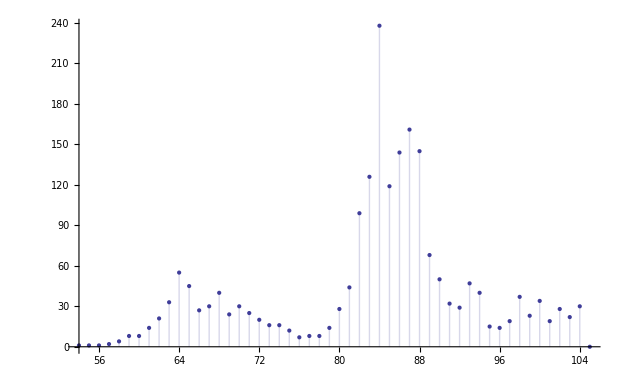

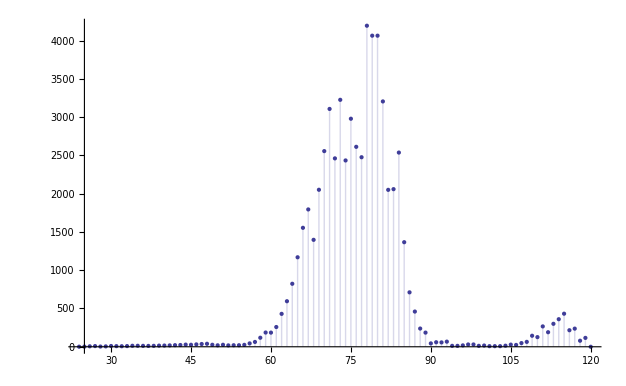

```mathematica
1928aaabaaacaaabbbaaacccaaabaaacabbbacccbaaabcbabbbcccbaaabbbcbbbabbbcccacbcaaabcbabbbcccacbcccaaabaaacaaabbbaaacccabcbbbabbbcccacccbcabbbaaabcaaacccbcccacccbbbacccaaabbbacccbbbabbbcbbbaaabcccbbbacbcccacccbbbaaabcccaaabaaacaaabbbcabcccbbbcaaabbbcbbbabbbcccabbbaaacaaabaaacccaaabbbaaacabcbbbabbbcccacbcaaabbbcccacccbcabaaacccaaabbbaaacaaabaaacccabbbcccaaacccbcccacbbbacccaaacbaaabbbacbaaacccbbbcccacbabbbcbbbaaabbbcccaaabbbaaacaaabaaacccabbbcccaaacbcccacccbbbabcbbbaaabcaaacccabbbcccaaacccbcccacccbbbabbbcbaaacccabcccbbbabbbcbbbaaabbbcccbabbbcbacaaabaaacccabbbcaaacccbcccacccbbbabbbcbacccaaacbaaabbbcbbbabcccbaaabbbcacbcccaaabaaacaaabbbaaacccbaaabbbcbbbabbbcccbbbaaabbbcbacaaabaaacccbbbcccacbabbbcccbbbaaabbbcbbbabbbcccbaaacccbbbcccacbcccaaabcccbbbabbbcbaaabbbcccaaabbbaaacabaaacccabbbcccaaacccbcccacccbbbcabbbaaacbcccacccbbbabbbcbbbaaacbbbcccbabcbaaacccbcccacccbbbacccaaabaaacabcbbbabbbcccaaabbbaaacaaabaaacccabbbcccaaacccbcabcbbbabcaaacccabbbcccacccbcccaaacccbbbacccaaabaaacabbbcaaacccbbbcccacbabbbcbbbaaacccbbbcccacccbcccaaacccbbbaaabbbcbabcccbbbcaaacccbcacccbbbabbbcbbbaaacbbbcccbacbbbaaacccaaabacbabbbcccaaabbbcbabbbcccacccbcccaaacbbbcccbacccaaabaaacaaabbbcccacbaaabbbacccbbbabbbcbacaaabbbaaacccaaabaaacaaabbbcaaacccbcabcbbbaaabcccaaabaaacaaabbbcaaacccbcccacccbbbcccaaacccbcabaaacccaaabbbaaacabcbbbabbbcccbbbaaacccbbbcccacccbcccaaacccbbbaaabcacccbcccaaabaaacaaabbbacccaaacbaaabbbcccbbbabcacccbcccaaacbbbcacbcccaaabaaacabbbacccbbbabbbcbbbaaacbbbcccbaaacbcccacccbbbabbbcbbbaaacccbbbcccacccbcccaaacccbbbaaacabcacccbcabcbbbaaacccbbbcccacccbcccaaacccbbbaaacaaabacbcccaaacccbbbcaaabcbbbabbbcccbaaacccbcccacccbbbcccaaacccbcabaaacccabbbaaacaaabaaacccbaaabbbcbabcccaaabbbcccacccbcccaaabaaacabbbcaaacbcacccbbbabbbcbbbaaacaaabacbbbcccaaabbbaaacaaabaaacccaaabbbcccaaacccbcccacbbbacaaabaaacccaaabbbcccaaacccbcccacccbbbcccaaabbbcbbbabcaaacccbbbcccacccbcabaaacccaaabbbaaacaaabaaacccabbbcccaaacccbcccacccbbbacaaabacbbbcccaaacccbcccacbabbbcccbac
```

## Polynomial Inequalities in Creation of Abelian Square-Free Strings

## Some preliminary examples

```mathematica
(* Inside the package, the main function structure is as follows. *)
	
vmmMakeA2FreeWord[str_String]:=Module[{myP,myV,myRes},
myP=vmmCreatePolynoms[str];
myV=vmmPickVariables[str];
myRes=vmmTestPolynom[myP,myV,1];
StringReplace[str,#]&/@myRes];
```

```mathematica
myTestP=vmmPolyTests`Private`vmmCreatePolynoms["aXbYcZdTa"]
```

(a-T) (X-a) (b-X) (Y-b) (c-Y) (Z-c) (T-d) (d-Z) (-a+b-X+Y) (a-d+T-Z) (-b+c-X+Y) (-b+c-Y+Z) (-c+d+T-Z) (-c+d-Y+Z) (-a-b+c-X+Y+Z) (a-c+d+T-Y-Z) (-b-c+d+T-Y+Z) (-b+c+d-X-Y+Z) (a-b-c+d+T-X-Y+Z) (-a-b+c+d+T-X-Y+Z)

```mathematica
vmmPolyTests`Private`vmmPickVariables["aXbYcZdTa"]
```

TXYZ

```mathematica
myRes=vmmPolyTests`Private`vmmTestPolynom[myTestP,"TXYZ",1]
```

{{T→b,X→c,Y→a,Z→a},{T→b,X→d,Y→a,Z→a},{T→b,X→d,Y→a,Z→b},{T→b,X→d,Y→d,Z→a},{T→b,X→d,Y→d,Z→b},{T→c,X→c,Y→a,Z→a},{T→c,X→d,Y→a,Z→a}}

```mathematica
StringReplace["aXbYcZdTa",#]&/@myRes
```

{acbacadba,adbacadba,adbacbdba,adbdcadba,adbdcbdba,acbacadca,adbacadca}

```mathematica
vmmMakeA2FreeWord["ABCD"]
```

{abac,abad,abca,abcb,abcd,abda,abdb,abdc,acab,acad,acba,acbc,acbd,acda,acdb,acdc,adab,adac,adba,adbc,adbd,adca,adcb,adcd,babc,babd,baca,bacb,bacd,bada,badb,badc,bcab,bcac,bcad,bcba,bcbd,bcda,bcdb,bcdc,bdab,bdac,bdad,bdba,bdbc,bdca,bdcb,bdcd,caba,cabc,cabd,cacb,cacd,cada,cadb,cadc,cbab,cbac,cbad,cbca,cbcd,cbda,cbdb,cbdc,cdab,cdac,cdad,cdba,cdbc,cdbd,cdca,cdcb,daba,dabc,dabd,daca,dacb,dacd,dadb,dadc,dbab,dbac,dbad,dbca,dbcb,dbcd,dbda,dbdc,dcab,dcac,dcad,dcba,dcbc,dcbd,dcda,dcdb}

```mathematica
% // Length
```

96

```mathematica
vmmMakeA2FreeWord5let["ABC"]
```

{aba,abc,abd,abe,aca,acb,acd,ace,ada,adb,adc,ade,aea,aeb,aec,aed,bab,bac,bad,bae,bca,bcb,bcd,bce,bda,bdb,bdc,bde,bea,beb,bec,bed,cab,cac,cad,cae,cba,cbc,cbd,cbe,cda,cdb,cdc,cde,cea,ceb,cec,ced,dab,dac,dad,dae,dba,dbc,dbd,dbe,dca,dcb,dcd,dce,dea,deb,dec,ded,eab,eac,ead,eae,eba,ebc,ebd,ebe,eca,ecb,ecd,ece,eda,edb,edc,ede}

```mathematica
% // Length
```

80

```mathematica
vmmMakeA2FreeWord3let["ABC"]
```

{aaa,aab,aac,aba,abb,abc,aca,acb,acc,baa,bab,bac,bba,bbb,bbc,bca,bcb,bcc,caa,cab,cac,cba,cbb,cbc,cca,ccb,ccc}

```mathematica
% // Length
```

27

```mathematica
vmmMakeA2FreeWord["abABCD",{{"A","B","C","D","a","b","c"}}]
```

{abacab,abacba,abacbc,abcaba,abcbab}

```mathematica
vmmMakeA2FreeWord["abABCD",{{"A","B","C","D","a","b","c"}}]
```

{abacab,abacba,abacbc,abcaba,abcbab}

```mathematica
vmmMakeA2FreeWord["abABCDE",{{"A","B","C","D","E","a","b","c"}}]
```

{abacaba,abacbab,abcbabc}

There are no a-2-free words over 3 letters of length 8. Note that here we do not allow factors  aa, bb, cc:

```mathematica
vmmMakeA2FreeWord["abABCDEF",{{"A","B","C","D","E","F","a","b","c"}}]
```

{}

If we allow factors  aa, bb, cc (and aaa, bbb, ccc) – but no longer abelian squares – the situation is very different:

```mathematica
vmmMakeA2FreeWord3let["abABCDEF",{{"A","B","C","D","E","F","a","b","c"}}]
```

{abaaacaa,abaaacab,abaaacba,abaaacbb,abaaacbc,abaaaccb,abaaaccc,abaacaaa,abaacaab,abaacaba,abaacabb,abaacabc,abaacbaa,abaacbab,abaacbac,abaacbba,abaacbbb,abaacbca,abaacbcc,abaaccba,abaaccbb,abaaccbc,abaaccca,abaacccb,abacaaab,abacaaba,abacaabb,abacabaa,abacabbb,abacabbc,abacbaaa,abacbabb,abacbbaa,abacbbab,abacbbba,abacbbbc,abacbcca,abacbccc,abaccbba,abaccbbb,abaccbca,abaccbcc,abacccaa,abacccab,abacccba,abacccbb,abacccbc,abbbaaab,abbbaaac,abbbaaca,abbbaacb,abbbaacc,abbbacaa,abbbacab,abbbacba,abbbacbb,abbbacbc,abbbaccb,abbbaccc,abbbcaaa,abbbcaab,abbbcaba,abbbcabb,abbbcabc,abbbcacb,abbbcacc,abbbcbaa,abbbcbab,abbbcbac,abbbcbba,abbbcbbb,abbbccaa,abbbccab,abbbccac,abbbccca,abbbcccb,abbcaaab,abbcaaac,abbcaaba,abbcaabb,abbcabaa,abbcabbb,abbcabcc,abbcacbc,abbcaccb,abbcaccc,abbcbaaa,abbcbaac,abbcbabb,abbcbaca,abbcbacc,abbcbbaa,abbcbbab,abbcbbba,abbccaaa,abbccaab,abbccaba,abbccabc,abbccacb,abbccacc,abbcccaa,abbcccab,abbcccac,abbcccba,abbcccbb,abcaaaba,abcaaabb,abcaaacc,abcaabaa,abcaabbb,abcaabbc,abcabaaa,abcabbba,abcabbbc,abcabbcb,abcabbcc,abcaccba,abcaccbb,abcaccbc,abcacccb,abcbaaab,abcbaaac,abcbaaca,abcbaacc,abcbabbb,abcbabcc,abcbbaaa,abcbbaac,abcbbabb,abcbbaca,abcbbacc,abcbbbaa,abcbbbab,abccaaab,abccaaac,abccaaba,abccaabb,abccaabc,abccacba,abccacbb,abccaccc,abcccaaa,abcccaab,abcccaba,abcccabb,abcccacc,abcccbaa,abcccbab,abcccbba,abcccbbb}

## Some general examples of parallel (global) method - and more

```mathematica
vmmMakeA2FreeWords[{"aAa", "bAb"}]
```

{{aca,bcb},{ada,bdb}}

```mathematica
vmmMakeA2FreeWords3let[{"aAa", "bBbA"}]
```

{{aaa,bbba},{aaa,bcba},{aba,babb},{aba,bcbb},{aca,babc},{aca,bbbc}}

```mathematica
vmmMakeA2FreeWords3let[{"aAa", "bBbA"}, {{"A","a", "b"}}]
```

{{aaa,bbba},{aaa,bcba},{aba,babb},{aba,bcbb}}

```mathematica
vmmMakeA2FreeWords5let[{"aAa", "bBbA"}]
```

{{aca,babc},{aca,bdbc},{aca,bebc},{ada,babd},{ada,bcbd},{ada,bebd},{aea,babe},{aea,bcbe},{aea,bdbe}}

```mathematica
vmmMakeA2FreeWords5let[{"aAa", "bBbA"}, {{"A", "c", "d"}}]
```

{{aca,babc},{aca,bdbc},{aca,bebc},{ada,babd},{ada,bcbd},{ada,bebd}}

```mathematica
vmmMakeA2FreeWords5let[{"aAa", "bBbA"}, {{"A", "c", "d"}, {"B", "e"}}]
```

{{aca,bebc},{ada,bebd}}

```mathematica
finalCatenationsForFixedAB=StringReplace[catenationsOf$aspb$And$sp$,myProductionsAB];
```

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[catenationsOf$aspb$And$sp$,myProductionsAB].

```mathematica
finalCatenationsForFixedABvariablesÌnBlocksLen6=StringReplace[finalCatenationsForFixedAB,{"A"->"aBCDEF","B"->"GHIJKL","pC"-> "d","pD"-> "e","Cs"-> "f","Ds"-> "g"}]
```

{faBCDEFd,faBCDEFe,fGHIJKLd,fGHIJKLe,faBCDEFGHIJKLd,faBCDEFGHIJKLe,fGHIJKLaBCDEFd,fGHIJKLaBCDEFe,faBCDEFGHIJKLaBCDEFd,faBCDEFGHIJKLaBCDEFe,fGHIJKLaBCDEFGHIJKLd,fGHIJKLaBCDEFGHIJKLe,gaBCDEFd,gaBCDEFe,gGHIJKLd,gGHIJKLe,gaBCDEFGHIJKLd,gaBCDEFGHIJKLe,gGHIJKLaBCDEFd,gGHIJKLaBCDEFe,gaBCDEFGHIJKLaBCDEFd,gaBCDEFGHIJKLaBCDEFe,gGHIJKLaBCDEFGHIJKLd,gGHIJKLaBCDEFGHIJKLe,fe,gd}

```mathematica
finalRulesForFixedABvarBlockLen6ext4={{"A"->"aaabac","B"->"abbbcc","pC"->"aaab","Cs"->"accc","pD"->"aaab","Ds"->"accc"},{"A"->"aaabac","B"->"abbbcc","pC"->"aaab","Cs"->"accc","pD"->"aaab","Ds"->"bccc"},{"A"->"aaabac","B"->"abbbcc","pC"->"aaab","Cs"->"bccc","pD"->"aaab","Ds"->"accc"},{"A"->"aaabac","B"->"abbbcc","pC"->"aaab","Cs"->"bccc","pD"->"aaab","Ds"->"bccc"},{"A"->"aaabac","B"->"bbbccc","pC"->"aaab","Cs"->"accc","pD"->"aaab","Ds"->"accc"},{"A"->"aaabac","B"->"bbbccc","pC"->"abbc","Cs"->"aaac","pD"->"abbc","Ds"->"aaac"},{"A"->"aaabac","B"->"bbbccc","pC"->"abbc","Cs"->"aaac","pD"->"bbaa","Ds"->"aaac"},{"A"->"aaabbb","B"->"acccbb","pC"->"aacc","Cs"->"aacb","pD"->"aacc","Ds"->"aacb"}, ... }
```

```mathematica
dotDashFromFixedABvarBlockLen6ext4={"aaabac.abbbcc.aaab-accc.aaab-accc","aaabac.abbbcc.aaab-accc.aaab-bccc","aaabac.abbbcc.aaab-bccc.aaab-accc","aaabac.abbbcc.aaab-bccc.aaab-bccc","aaabac.bbbccc.aaab-accc.aaab-accc","aaabac.bbbccc.abbc-aaac.abbc-aaac","aaabac.bbbccc.abbc-aaac.bbaa-aaac","aaabbb.acccbb.aacc-aacb.aacc-aacb","aaabbb.acccbb.aacc-aacb.aacc-cacb","aaabbb.acccbb.aacc-aacb.aacc-accb","aaabbb.acccbb.aacc-cacb.aacc-aacb","aaabbb.acccbb.aacc-cacb.aacc-cacb","aaabbb.acccbb.aacc-cacb.aacc-accb","aaabbb.acccbb.aacc-accb.aacc-aacb","aaabbb.acccbb.aacc-accb.aacc-cacb","aaabbb.acccbb.aacc-accb.aacc-accb","aaabbb.caccbb.aacc-accb.aacc-accb","aaabbb.ccacbb.aacc-accb.aacc-accb","aaabbb.cccacb.aacc-aacb.aacc-aacb",... }
```

```mathematica
({{□, □, □, □, □, □, □, □}, {□, □, □, □, -, -, +, +}, {□, □, □, -, -, +, +, □}, {□, □, -, -, +, +, □, □}, {□, -, -, +, +, □, □, □}, {-, -, +, +, □, □, □, □}, {□, □, -, -, -, +, +, +}, {□, -, -, -, +, +, +, □}, {-, -, -, +, +, +, □, □}, {-, -, -, -, +, +, +, +}})
```

```mathematica
{({{a1}, {b1}, {c1}}),({{a2}, {b2}, {c2}}),({{a3}, {b3}, {c3}}),({{a4}, {b4}, {c4}}),({{a5}, {b5}, {c5}}),({{a6}, {b6}, {c6}}),({{a7}, {b7}, {c7}}),({{a8}, {b8}, {c8}})}
{({{a1}, {b1}}),({{a2}, {b2}}),({{a3}, {b3}}),({{a4}, {b4}}),({{a5}, {b5}}),({{a6}, {b6}}),({{a7}, {b7}}),({{a8}, {b8}})}
{{a1,b1},{a2,b2},{a3,b3},{a4,b4},{a5,b5},{a6,b6},{a7,b7},{a8,b8}}
```

```mathematica
Clear[a1,b1,a2,b2,a3,b3,a4,b4,a5,b5,a6,b6,a7,b7,a8,b8];Timing[Solve[{(-a5-a6+a7+a8≠0∨-b5-b6+b7+b8≠0)&&(-a3-a4-a5+a6+a7+a8≠0∨-b3-b4-b5+b6+b7+b8≠0)&&(-a1-a2-a3-a4+a5+a6+a7+a8≠0∨-b1-b2-b3-b4+b5+b6+b7+b8≠0)&&(-a4-a5+a6+a7≠0∨-b4-b5+b6+b7≠0)&&(-a2-a3-a4+a5+a6+a7≠0∨-b2-b3-b4+b5+b6+b7≠0)&&(-a3-a4+a5+a6≠0∨-b3-b4+b5+b6≠0)&&(-a1-a2-a3+a4+a5+a6≠0∨-b1-b2-b3+b4+b5+b6≠0)&& (-a2-a3+a4+a5≠0∨-b2-b3+b4+b5≠0)&&(-a1-a2+a3+a4≠0∨-b1-b2+b3+b4≠0),(a1==1&&b1==0)∨(a1==0&&b1==1)∨(a1==0&&b1==0),(a2==1&&b2==0)∨(a2==0&&b2==1)∨(a2==0&&b2==0), 
(a3==1&&b3==0)∨(a3==0&&b3==1)∨(a3==0&&b3==0),
(a4==1&&b4==0)∨(a4==0&&b4==1)∨(a4==0&&b4==0),
(a5==1&&b5==0)∨(a5==0&&b5==1)∨(a5==0&&b5==0),
(a6==1&&b6==0)∨(a6==0&&b6==1)∨(a6==0&&b6==0),
(a7==1&&b7==0)∨(a7==0&&b7==1)∨(a7==0&&b7==0),
(a8==1&&b8==0)∨(a8==0&&b8==1)∨(a8==0&&b8==0)},{a1,b1,a2,b2,a3,b3,a4,b4,a5 ,b5,a6,b6,a7,b7,a8,b8},Integers]]
```

{421872.15625,{{a1→0,b1→0,a2→0,b2→0,a3→0,b3→0,a4→0,b4→1,a5→0,b5→0,a6→0,b6→0,a7→0,b7→0,a8→1,b8→0},{a1→0,b1→0,a2→0,b2→0,a3→0,b3→0,a4→0,b4→1,a5→0,b5→0,a6→0,b6→0,a7→1,b7→0,a8→0,b8→0},1569,{a1→1,b1→0,a2→1,b2→0,a3→1,b3→0,a4→0,b4→1,a5→1,b5→0,a6→1,b6→0,a7→1,b7→0,a8→0,b8→0}}}
 |  |  |  |

```mathematica
%[[2]]//Length
```

1572

```mathematica
421872.16/3600 hours
```

117.187 hours

Oh yes, the computational time is downright hilarious!

```mathematica
%821[[2]]//Length
```

1572

Exactly correct!

## Using multivariable polynomials for a set of words

### Example of search for candidate endomorphism over 4 letters (parallel/global approach)

In this approach, many morphic images (with variables) of words, given in a list, are handled in a parallel way by firstly taking, for each image word, the products of all possible differences of symbolic Parikh vectors (with variables) of consecutive factors having the same length. Secondly, one multiplies the difference products with each other and only after this one tries to find values for the variables in the current alphabet. If this whole product of difference products is not zero, then those variable values make all the image words abelian square-free, and, importantly, all image words for letters are globally the same in all of their occurrences.

We proceed as follows:

```mathematica
myPrewordsOfLen2
```

{ab,ac,ad,ba,bc,bd,ca,cb,cd,da,db,dc}

Recalling that in this experiment, we are not using all the 12 prewords of length 2 but remove  cd, db, dc  from the set  {ab, ac, ad, ba, bc, bd, ca, cb, cd, da, db, dc}:

```mathematica
myVarImagesForLen2ParallelStyle=StringReplace[#,{"a"->"aBCa","b"->"bFGH","c"->"cJKLM","d"->"dOPQRS"}]&/@{"ab", "ac", "ad", "ba","ca","da","bc","bd","cb"}
```

{aBCabFGH,aBCacJKLM,aBCadOPQRS,bFGHaBCa,cJKLMaBCa,dOPQRSaBCa,bFGHcJKLM,bFGHdOPQRS,cJKLMbFGH}

```mathematica
(res=vmmMakeA2FreeWords[myVarImagesForLen2ParallelStyle])//Timing
```

{(-a+b) (-a+B) (a-C) (a+b-B-C) (-B+C)^2 (-b+F) (-a+b-C+F) (b-B-C+F) (-F+G) (-a-b+F+G) (-a+b-B-C+F+G) (-G+H) (-b-F+G+H) (-a-b-C+F+G+H) (-2 a+b-B-C+F+G+H),(-a+B) (-a+c) (a-C) (a-B+c-C) (-B+C)^2 (-c+J) (-a+c-C+J) (-B+c-C+J) (-J+K) (-a-c+J+K) (-a-B+c-C+J+K) (-K+L) (-c-J+K+L) (-a-c-C+J+K+L) (-2 a-B+c-C+J+K+L) (-L+M) (-J-K+L+M) (-a-c-J+K+L+M) (-a-B-c-C+J+K+L+M),(-a+B) (a-C) (-B+C)^2 (-a+d) (a-B-C+d) (-d+O) (-a-C+d+O) (-B-C+d+O) (-O+P) (-a-d+O+P) (-a-B-C+d+O+P) (-P+Q) (-d-O+P+Q) (-a-C-d+O+P+Q) (-2 a-B-C+d+O+P+Q) (-Q+R) (-O-P+Q+R) (-a-d-O+P+Q+R) (-a-B-C-d+O+P+Q+R) (-R+S) (-P-Q+R+S) (-d-O-P+Q+R+S) (-a-C-d-O+P+Q+R+S) (-2 a-B-C-d+O+P+Q+R+S),(-a+B) (a-C) (-B+C)^2 (-b+F) (-F+G) (a-H) (-a+B+C-H) (a+B-G-H) (B+C-G-H) (a+B+C-F-G-H) (2 a-b+B+C-F-G-H) (-G+H) (a-F-G+H) (a-b+B-F-G+H) (-b-F+G+H),(-a+B) (a-C) (-B+C)^2 (-c+J) (-J+K) (-K+L) (-c-J+K+L) (a-M) (-a+B+C-M) (a+B-L-M) (B+C-L-M) (a+B+C-K-L-M) (2 a+B+C-J-K-L-M) (-L+M) (a-K-L+M) (a+B-J-K-L+M) (a+B-c+C-J-K-L+M) (-J-K+L+M) (a-c-J-K+L+M),(-a+B) (a-C) (-B+C)^2 (-d+O) (-O+P) (-P+Q) (-d-O+P+Q) (-Q+R) (-O-P+Q+R) (a-S) (-a+B+C-S) (a+B-R-S) (B+C-R-S) (a+B+C-Q-R-S) (2 a+B+C-P-Q-R-S) (-R+S) (a-Q-R+S) (a+B-P-Q-R+S) (a+B+C-O-P-Q-R+S) (2 a+B+C-d-O-P-Q-R+S) (-P-Q+R+S) (a-O-P-Q+R+S) (a+B-d-O-P-Q+R+S) (-d-O-P+Q+R+S),(-b+F) (-F+G) (c-H) (-G+H) (c-F-G+H) (-b-F+G+H) (-c+J) (c-G-H+J) (-b+c-F-G+H+J) (-J+K) (-c-H+J+K) (c-F-G-H+J+K) (-K+L) (-c-J+K+L) (-c-G-H+J+K+L) (-b+c-F-G-H+J+K+L) (-L+M) (-J-K+L+M) (-c-H-J+K+L+M) (-c-F-G-H+J+K+L+M),(-b+F) (-F+G) (d-H) (-G+H) (d-F-G+H) (-b-F+G+H) (-d+O) (d-G-H+O) (-b+d-F-G+H+O) (-O+P) (-d-H+O+P) (d-F-G-H+O+P) (-P+Q) (-d-O+P+Q) (-d-G-H+O+P+Q) (-b+d-F-G-H+O+P+Q) (-Q+R) (-O-P+Q+R) (-d-H-O+P+Q+R) (-d-F-G-H+O+P+Q+R) (-R+S) (-P-Q+R+S) (-d-O-P+Q+R+S) (-d-G-H-O+P+Q+R+S) (-b-d-F-G-H+O+P+Q+R+S),(-b+F) (-F+G) (-G+H) (-b-F+G+H) (-c+J) (-J+K) (-K+L) (-c-J+K+L) (b-M) (-b+F+G-M) (b+F-L-M) (-b+F+G+H-L-M) (b+F+G-K-L-M) (b+F+G+H-J-K-L-M) (-L+M) (b-K-L+M) (b+F-J-K-L+M) (b-c+F+G-J-K-L+M) (-J-K+L+M) (b-c-J-K+L+M)}

{B,C,F,G,H,B,C,J,K,L,M,B,C,O,P,Q,R,S,B,C,F,G,H,B,C,J,K,L,M,B,C,O,P,Q,R,S,F,G,H,J,K,L,M,F,G,H,O,P,Q,R,S,F,G,H,J,K,L,M}

BCFGHJKLMOPQRS

(-a+b) (-a+B)^6 (-a+c) (a-C)^6 (a+b-B-C) (a-B+c-C) (-B+C)^12 (-a+d) (a-B-C+d) (-b+F)^5 (-a+b-C+F) (b-B-C+F) (-F+G)^5 (-a-b+F+G) (-a+b-B-C+F+G) (a-H) (c-H) (-a+B+C-H) (d-H) (a+B-G-H) (B+C-G-H) (a+B+C-F-G-H) (2 a-b+B+C-F-G-H) (-G+H)^5 (a-F-G+H) (a-b+B-F-G+H) (c-F-G+H) (d-F-G+H) (-b-F+G+H)^5 (-a-b-C+F+G+H) (-2 a+b-B-C+F+G+H) (-c+J)^4 (-a+c-C+J) (-B+c-C+J) (c-G-H+J) (-b+c-F-G+H+J) (-J+K)^4 (-a-c+J+K) (-a-B+c-C+J+K) (-c-H+J+K) (c-F-G-H+J+K) (-K+L)^4 (-c-J+K+L)^4 (-a-c-C+J+K+L) (-2 a-B+c-C+J+K+L) (-c-G-H+J+K+L) (-b+c-F-G-H+J+K+L) (a-M) (b-M) (-a+B+C-M) (-b+F+G-M) (a+B-L-M) (B+C-L-M) (b+F-L-M) (-b+F+G+H-L-M) (a+B+C-K-L-M) (b+F+G-K-L-M) (2 a+B+C-J-K-L-M) (b+F+G+H-J-K-L-M) (-L+M)^4 (a-K-L+M) (b-K-L+M) (a+B-J-K-L+M) (a+B-c+C-J-K-L+M) (b+F-J-K-L+M) (b-c+F+G-J-K-L+M) (-J-K+L+M)^4 (a-c-J-K+L+M) (b-c-J-K+L+M) (-a-c-J+K+L+M) (-c-H-J+K+L+M) (-a-B-c-C+J+K+L+M) (-c-F-G-H+J+K+L+M) (-d+O)^3 (-a-C+d+O) (-B-C+d+O) (d-G-H+O) (-b+d-F-G+H+O) (-O+P)^3 (-a-d+O+P) (-a-B-C+d+O+P) (-d-H+O+P) (d-F-G-H+O+P) (-P+Q)^3 (-d-O+P+Q)^3 (-a-C-d+O+P+Q) (-2 a-B-C+d+O+P+Q) (-d-G-H+O+P+Q) (-b+d-F-G-H+O+P+Q) (-Q+R)^3 (-O-P+Q+R)^3 (-a-d-O+P+Q+R) (-d-H-O+P+Q+R) (-a-B-C-d+O+P+Q+R) (-d-F-G-H+O+P+Q+R) (a-S) (-a+B+C-S) (a+B-R-S) (B+C-R-S) (a+B+C-Q-R-S) (2 a+B+C-P-Q-R-S) (-R+S)^3 (a-Q-R+S) (a+B-P-Q-R+S) (a+B+C-O-P-Q-R+S) (2 a+B+C-d-O-P-Q-R+S) (-P-Q+R+S)^3 (a-O-P-Q+R+S) (a+B-d-O-P-Q+R+S) (-d-O-P+Q+R+S)^3 (-a-C-d-O+P+Q+R+S) (-d-G-H-O+P+Q+R+S) (-2 a-B-C-d+O+P+Q+R+S) (-b-d-F-G-H+O+P+Q+R+S)

{{B→d,C→c,F→c,G→d,H→b,J→b,K→a,L→b,M→d,O→a,P→b,Q→c,R→b,S→d},{B→d,C→c,F→c,G→d,H→b,J→b,K→a,L→b,M→d,O→a,P→b,Q→d,R→b,S→c}}

{0.53706,{{adcabcdb,adcacbabd,adcadabcbd,bcdbadca,cbabdadca,dabcbdadca,bcdbcbabd,bcdbdabcbd,cbabdbcdb},{adcabcdb,adcacbabd,adcadabdbc,bcdbadca,cbabdadca,dabdbcadca,bcdbcbabd,bcdbdabdbc,cbabdbcdb}}}

This computation took only half a second.

```mathematica
res2=Transpose[{{"ab", "ac", "ad", "ba","ca","da","bc","bd","cb"},#}]& /@ res
```

{{{ab,adcabcdb},{ac,adcacbabd},{ad,adcadabcbd},{ba,bcdbadca},{ca,cbabdadca},{da,dabcbdadca},{bc,bcdbcbabd},{bd,bcdbdabcbd},{cb,cbabdbcdb}},{{ab,adcabcdb},{ac,adcacbabd},{ad,adcadabdbc},{ba,bcdbadca},{ca,cbabdadca},{da,dabdbcadca},{bc,bcdbcbabd},{bd,bcdbdabdbc},{cb,cbabdbcdb}}}

Let us pick up the separate image words for letters:

```mathematica
Clear[decomposeToMorphImagewords];
decomposeToMorphImagewords[word_,preword_,endomorphismWithVar_]:=Flatten[StringTake[word,#]& /@
StringPosition[StringReplace[preword,endomorphismWithVar],#,1,Overlaps->False]& /@ (#[[2]]&/@ endomorphismWithVar)];
```

Testing a bit:

```mathematica
decomposeToMorphImagewords["adcabcdb","ab",{"a"->"aBCa","b"->"bFGH","c"->"cJKLM","d"->"dOPQRS"}]
```

{adca,bcdb}

```mathematica
decomposition1=Map[{#[[1]],decomposeToMorphImagewords[#[[2]],#[[1]],{"a"->"aBCa","b"->"bFGH","c"->"cJKLM","d"->"dOPQRS"}]}&,res2,{2}]
```

{{{ab,{adca,bcdb}},{ac,{adca,cbabd}},{ad,{adca,dabcbd}},{ba,{adca,bcdb}},{ca,{adca,cbabd}},{da,{adca,dabcbd}},{bc,{bcdb,cbabd}},{bd,{bcdb,dabcbd}},{cb,{bcdb,cbabd}}},{{ab,{adca,bcdb}},{ac,{adca,cbabd}},{ad,{adca,dabdbc}},{ba,{adca,bcdb}},{ca,{adca,cbabd}},{da,{adca,dabdbc}},{bc,{bcdb,cbabd}},{bd,{bcdb,dabdbc}},{cb,{bcdb,cbabd}}}}

```mathematica
Clear[prewordAndTrialsForImagesGxSublistNew];
prewordAndTrialsForImagesGxSublistNew[sublist_]:=Module[{preword=sublist[[1]]},{preword,Thread[Rule[Union[Characters[preword]],sublist[[2]]]]}]
```

```mathematica
prewordsAndProductions=Map[prewordAndTrialsForImagesGxSublistNew,decomposition1,{2}]
```

{{{ab,{a→adca,b→bcdb}},{ac,{a→adca,c→cbabd}},{ad,{a→adca,d→dabcbd}},{ba,{a→adca,b→bcdb}},{ca,{a→adca,c→cbabd}},{da,{a→adca,d→dabcbd}},{bc,{b→bcdb,c→cbabd}},{bd,{b→bcdb,d→dabcbd}},{cb,{b→bcdb,c→cbabd}}},{{ab,{a→adca,b→bcdb}},{ac,{a→adca,c→cbabd}},{ad,{a→adca,d→dabdbc}},{ba,{a→adca,b→bcdb}},{ca,{a→adca,c→cbabd}},{da,{a→adca,d→dabdbc}},{bc,{b→bcdb,c→cbabd}},{bd,{b→bcdb,d→dabdbc}},{cb,{b→bcdb,c→cbabd}}}}

```mathematica
Map[Transpose, prewordsAndProductions]
```

{{{ab,ac,ad,ba,ca,da,bc,bd,cb},{{a→adca,b→bcdb},{a→adca,c→cbabd},{a→adca,d→dabcbd},{a→adca,b→bcdb},{a→adca,c→cbabd},{a→adca,d→dabcbd},{b→bcdb,c→cbabd},{b→bcdb,d→dabcbd},{b→bcdb,c→cbabd}}},{{ab,ac,ad,ba,ca,da,bc,bd,cb},{{a→adca,b→bcdb},{a→adca,c→cbabd},{a→adca,d→dabdbc},{a→adca,b→bcdb},{a→adca,c→cbabd},{a→adca,d→dabdbc},{b→bcdb,c→cbabd},{b→bcdb,d→dabdbc},{b→bcdb,c→cbabd}}}}

```mathematica
Map[{#[[1]],Union[Flatten[#[[2]]]]}&,Map[Transpose, prewordsAndProductions]]
```

{{{ab,ac,ad,ba,ca,da,bc,bd,cb},{a→adca,b→bcdb,c→cbabd,d→dabcbd}},{{ab,ac,ad,ba,ca,da,bc,bd,cb},{a→adca,b→bcdb,c→cbabd,d→dabdbc}}}

Thus, as found out also earlier in sequential fashion, in this setting over a four letter alphabet, there are two possibilities for an endomorphism  g  such that it preserves the abelian square-freeness of all the words in  {ab, ac, ad, ba, ca, cb, cd, da, db, dc}  (but, unfortunately, not for the words cd, db, dc).  These two possibilities are (the same as before in sequential approach):

```mathematica
{{"a"->"adca","b"->"bcdb","c"->"cbabd","d"->"dabcbd"},{"a"->"adca","b"->"bcdb","c"->"cbabd","d"->"dabdbc"}}
```

Some symbolic computations

Dynamic programming

Example: Fibonacci sequence  0, 1, 1, 2, 3, 5, 8, 13, 21, 34, ...

```mathematica
Clear[f];
f[n_]:=f[n-1]+f[n-2];
f[0]=0; f[1]=1;
```

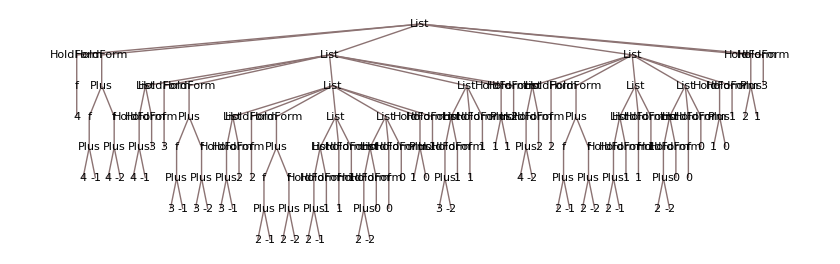

```mathematica
TreeForm[Trace[f[4]]]
```

```mathematica
Clear[f];
f[n_]:=f[n]=f[n-1]+f[n-2];
f[0]=0; f[1]=1;
```

```mathematica
?f
```

Global`f

f[0]=0
 
f[1]=1
 
f[n_]:=f[n]=f[n-1]+f[n-2]

```mathematica
f[12]
```

144

```mathematica
?f
```

Global`f

f[0]=0
 
f[1]=1
 
f[2]=1
 
f[3]=2
 
f[4]=3
 
f[5]=5
 
f[6]=8
 
f[7]=13
 
f[8]=21
 
f[9]=34
 
f[10]=55
 
f[11]=89
 
f[12]=144
 
f[n_]:=f[n]=f[n-1]+f[n-2]

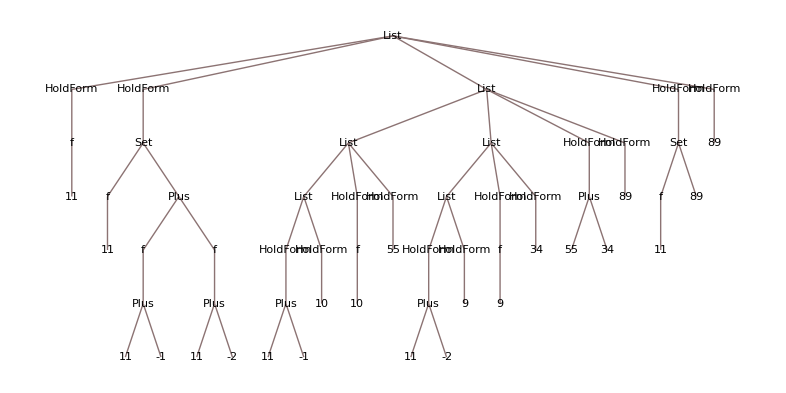

```mathematica
TreeForm[Trace[f[11]]]
```

```mathematica
?f
```

Global`f

f[0]=0
 
f[1]=1
 
f[2]=1
 
f[3]=2
 
f[4]=3
 
f[5]=5
 
f[6]=8
 
f[7]=13
 
f[8]=21
 
f[9]=34
 
f[10]=55
 
f[11]=89
 
f[n_]:=f[n]=f[n-1]+f[n-2]

```mathematica
f[201]
```

453973694165307953197296969697410619233826

```mathematica
f[401]
```

284812298108489611757988937681460995615380088782304890986477195645969271404032323901

```mathematica
g0000prefLENsANDvMINUSuDIFFsForPreComputedPrefLensContaining2or3of17$18$19$48$49uMinusXisvLeftLonger[XYZ_String]:=g0000prefLENsANDvMINUSuDIFFsForPreComputedPrefLensContaining2or3of17$18$19$48$49uMinusXisvLeftLonger[XYZ]=(mySelectForg0000uMinusXisvLeftLonger[#1][XYZ]&)/@allPrefLengthsContaining2or3of17$18$19$48$49ForUniform109uMinusXisvLeftLonger
```

## Repetition-free strings

#### Ordinary squares are unavoidable over 2 letters - every word of length 4 contains them:

```mathematica
Clear[myAppend];
myAppend[x_List,k_:2]:=Flatten[Table[Append[#,i-1],{i,k}]&/@ x,1]
```

```mathematica
patternFreeLists=NestList[DeleteCases[myAppend[#,2],{___,u__,u__}]&,{{}},4]
```

{{{}},{{0},{1}},{{0,1},{1,0}},{{0,1,0},{1,0,1}},{}}

```mathematica
Clear[toStrings];
toStrings[x_]:=Map[Apply[StringJoin,#]&,#]& /@(x /. {0->"a",1->"b",2->"c",3->"d"});
```

```mathematica
toStrings[patternFreeLists]
```

{{},{a,b},{ab,ba},{aba,bab},{}}

#### Abelian squares are unavoidable over 3 letters - every word of length 8 contains them:

```mathematica
patternFreeLists=With[{n=8,k=3},NestList[DeleteCases[Flatten[Map[Table[Append[#,i-1],{i,k}]&,#],1],{___,u__,v__}/;Sort[{u}]==Sort[{v}]] &,{{}},n]]
```

{{{}},(0
1
2),(0 | 1
0 | 2
1 | 0
1 | 2
2 | 0
2 | 1),(0 | 1 | 0
0 | 1 | 2
0 | 2 | 0
0 | 2 | 1
1 | 0 | 1
1 | 0 | 2
1 | 2 | 0
1 | 2 | 1
2 | 0 | 1
2 | 0 | 2
2 | 1 | 0
2 | 1 | 2),(0 | 1 | 0 | 2
0 | 1 | 2 | 0
0 | 1 | 2 | 1
0 | 2 | 0 | 1
0 | 2 | 1 | 0
0 | 2 | 1 | 2
1 | 0 | 1 | 2
1 | 0 | 2 | 0
1 | 0 | 2 | 1
1 | 2 | 0 | 1
1 | 2 | 0 | 2
1 | 2 | 1 | 0
2 | 0 | 1 | 0
2 | 0 | 1 | 2
2 | 0 | 2 | 1
2 | 1 | 0 | 1
2 | 1 | 0 | 2
2 | 1 | 2 | 0),(0 | 1 | 0 | 2 | 0
0 | 1 | 0 | 2 | 1
0 | 1 | 2 | 0 | 1
0 | 1 | 2 | 0 | 2
0 | 1 | 2 | 1 | 0
0 | 2 | 0 | 1 | 0
0 | 2 | 0 | 1 | 2
0 | 2 | 1 | 0 | 1
0 | 2 | 1 | 0 | 2
0 | 2 | 1 | 2 | 0
1 | 0 | 1 | 2 | 0
1 | 0 | 1 | 2 | 1
1 | 0 | 2 | 0 | 1
1 | 0 | 2 | 1 | 0
1 | 0 | 2 | 1 | 2
1 | 2 | 0 | 1 | 0
1 | 2 | 0 | 1 | 2
1 | 2 | 0 | 2 | 1
1 | 2 | 1 | 0 | 1
1 | 2 | 1 | 0 | 2
2 | 0 | 1 | 0 | 2
2 | 0 | 1 | 2 | 0
2 | 0 | 1 | 2 | 1
2 | 0 | 2 | 1 | 0
2 | 0 | 2 | 1 | 2
2 | 1 | 0 | 1 | 2
2 | 1 | 0 | 2 | 0
2 | 1 | 0 | 2 | 1
2 | 1 | 2 | 0 | 1
2 | 1 | 2 | 0 | 2),(0 | 1 | 0 | 2 | 0 | 1
0 | 1 | 0 | 2 | 1 | 0
0 | 1 | 0 | 2 | 1 | 2
0 | 1 | 2 | 0 | 1 | 0
0 | 1 | 2 | 1 | 0 | 1
0 | 2 | 0 | 1 | 0 | 2
0 | 2 | 0 | 1 | 2 | 0
0 | 2 | 0 | 1 | 2 | 1
0 | 2 | 1 | 0 | 2 | 0
0 | 2 | 1 | 2 | 0 | 2
1 | 0 | 1 | 2 | 0 | 1
1 | 0 | 1 | 2 | 0 | 2
1 | 0 | 1 | 2 | 1 | 0
1 | 0 | 2 | 0 | 1 | 0
1 | 0 | 2 | 1 | 0 | 1
1 | 2 | 0 | 1 | 2 | 1
1 | 2 | 0 | 2 | 1 | 2
1 | 2 | 1 | 0 | 1 | 2
1 | 2 | 1 | 0 | 2 | 0
1 | 2 | 1 | 0 | 2 | 1
2 | 0 | 1 | 0 | 2 | 0
2 | 0 | 1 | 2 | 0 | 2
2 | 0 | 2 | 1 | 0 | 1
2 | 0 | 2 | 1 | 0 | 2
2 | 0 | 2 | 1 | 2 | 0
2 | 1 | 0 | 1 | 2 | 1
2 | 1 | 0 | 2 | 1 | 2
2 | 1 | 2 | 0 | 1 | 0
2 | 1 | 2 | 0 | 1 | 2
2 | 1 | 2 | 0 | 2 | 1),(0 | 1 | 0 | 2 | 0 | 1 | 0
0 | 1 | 0 | 2 | 1 | 0 | 1
0 | 1 | 2 | 1 | 0 | 1 | 2
0 | 2 | 0 | 1 | 0 | 2 | 0
0 | 2 | 0 | 1 | 2 | 0 | 2
0 | 2 | 1 | 2 | 0 | 2 | 1
1 | 0 | 1 | 2 | 0 | 1 | 0
1 | 0 | 1 | 2 | 1 | 0 | 1
1 | 0 | 2 | 0 | 1 | 0 | 2
1 | 2 | 0 | 2 | 1 | 2 | 0
1 | 2 | 1 | 0 | 1 | 2 | 1
1 | 2 | 1 | 0 | 2 | 1 | 2
2 | 0 | 1 | 0 | 2 | 0 | 1
2 | 0 | 2 | 1 | 0 | 2 | 0
2 | 0 | 2 | 1 | 2 | 0 | 2
2 | 1 | 0 | 1 | 2 | 1 | 0
2 | 1 | 2 | 0 | 1 | 2 | 1
2 | 1 | 2 | 0 | 2 | 1 | 2),{}}

```mathematica
toStrings[patternFreeLists]
```

{{},{a,b,c},{ab,ac,ba,bc,ca,cb},{aba,abc,aca,acb,bab,bac,bca,bcb,cab,cac,cba,cbc},{abac,abca,abcb,acab,acba,acbc,babc,baca,bacb,bcab,bcac,bcba,caba,cabc,cacb,cbab,cbac,cbca},{abaca,abacb,abcab,abcac,abcba,acaba,acabc,acbab,acbac,acbca,babca,babcb,bacab,bacba,bacbc,bcaba,bcabc,bcacb,bcbab,bcbac,cabac,cabca,cabcb,cacba,cacbc,cbabc,cbaca,cbacb,cbcab,cbcac},{abacab,abacba,abacbc,abcaba,abcbab,acabac,acabca,acabcb,acbaca,acbcac,babcab,babcac,babcba,bacaba,bacbab,bcabcb,bcacbc,bcbabc,bcbaca,bcbacb,cabaca,cabcac,cacbab,cacbac,cacbca,cbabcb,cbacbc,cbcaba,cbcabc,cbcacb},{abacaba,abacbab,abcbabc,acabaca,acabcac,acbcacb,babcaba,babcbab,bacabac,bcacbca,bcbabcb,bcbacbc,cabacab,cacbaca,cacbcac,cbabcba,cbcabcb,cbcacbc},{}}

#### It is an open problem whether abelian squares are avoidable over a 3-letter alphabet {a,b,c}, if we allow repetitions of length 1, that is, we allow factors aa, bb, cc, aaa, bbb, ccc, but not any longer abelian square.

Let us investigate this a bit:

```mathematica
patternFreeLists3LettersLength1RepetitionAllowed=With[{n=8,k=3},NestList[DeleteCases[Flatten[Map[Table[Append[#,i-1],{i,k}]&,#],1],{___,u__,v__}/;Sort[{u}]==Sort[{v}]∧Not[Length[{v}]==1]] &,{{}},n]]
```

{{{}},(0
1
2),(0 | 0
0 | 1
0 | 2
1 | 0
1 | 1
1 | 2
2 | 0
2 | 1
2 | 2),(0 | 0 | 0
0 | 0 | 1
0 | 0 | 2
0 | 1 | 0
0 | 1 | 1
0 | 1 | 2
0 | 2 | 0
0 | 2 | 1
0 | 2 | 2
1 | 0 | 0
1 | 0 | 1
1 | 0 | 2
1 | 1 | 0
1 | 1 | 1
1 | 1 | 2
1 | 2 | 0
1 | 2 | 1
1 | 2 | 2
2 | 0 | 0
2 | 0 | 1
2 | 0 | 2
2 | 1 | 0
2 | 1 | 1
2 | 1 | 2
2 | 2 | 0
2 | 2 | 1
2 | 2 | 2),(0 | 0 | 0 | 1
0 | 0 | 0 | 2
0 | 0 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 1 | 2
0 | 0 | 2 | 0
0 | 0 | 2 | 1
0 | 0 | 2 | 2
0 | 1 | 0 | 0
0 | 1 | 0 | 2
0 | 1 | 1 | 1
0 | 1 | 1 | 2
0 | 1 | 2 | 0
0 | 1 | 2 | 1
0 | 1 | 2 | 2
0 | 2 | 0 | 0
0 | 2 | 0 | 1
0 | 2 | 1 | 0
0 | 2 | 1 | 1
0 | 2 | 1 | 2
0 | 2 | 2 | 1
0 | 2 | 2 | 2
1 | 0 | 0 | 0
1 | 0 | 0 | 2
1 | 0 | 1 | 1
1 | 0 | 1 | 2
1 | 0 | 2 | 0
1 | 0 | 2 | 1
1 | 0 | 2 | 2
1 | 1 | 0 | 0
1 | 1 | 0 | 1
1 | 1 | 0 | 2
1 | 1 | 1 | 0
1 | 1 | 1 | 2
1 | 1 | 2 | 0
1 | 1 | 2 | 1
1 | 1 | 2 | 2
1 | 2 | 0 | 0
1 | 2 | 0 | 1
1 | 2 | 0 | 2
1 | 2 | 1 | 0
1 | 2 | 1 | 1
1 | 2 | 2 | 0
1 | 2 | 2 | 2
2 | 0 | 0 | 0
2 | 0 | 0 | 1
2 | 0 | 1 | 0
2 | 0 | 1 | 1
2 | 0 | 1 | 2
2 | 0 | 2 | 1
2 | 0 | 2 | 2
2 | 1 | 0 | 0
2 | 1 | 0 | 1
2 | 1 | 0 | 2
2 | 1 | 1 | 0
2 | 1 | 1 | 1
2 | 1 | 2 | 0
2 | 1 | 2 | 2
2 | 2 | 0 | 0
2 | 2 | 0 | 1
2 | 2 | 0 | 2
2 | 2 | 1 | 0
2 | 2 | 1 | 1
2 | 2 | 1 | 2
2 | 2 | 2 | 0
2 | 2 | 2 | 1),(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 2
0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 2 | 1
0 | 0 | 0 | 2 | 2
0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 2
0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 2
0 | 0 | 1 | 2 | 0
0 | 0 | 1 | 2 | 1
0 | 0 | 1 | 2 | 2
0 | 0 | 2 | 0 | 0
0 | 0 | 2 | 0 | 1
0 | 0 | 2 | 1 | 0
0 | 0 | 2 | 1 | 1
0 | 0 | 2 | 1 | 2
0 | 0 | 2 | 2 | 1
0 | 0 | 2 | 2 | 2
0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 2
0 | 1 | 0 | 2 | 0
0 | 1 | 0 | 2 | 1
0 | 1 | 0 | 2 | 2
0 | 1 | 1 | 1 | 0
0 | 1 | 1 | 1 | 2
0 | 1 | 1 | 2 | 0
0 | 1 | 1 | 2 | 1
0 | 1 | 1 | 2 | 2
0 | 1 | 2 | 0 | 0
0 | 1 | 2 | 0 | 1
0 | 1 | 2 | 0 | 2
0 | 1 | 2 | 1 | 0
0 | 1 | 2 | 1 | 1
0 | 1 | 2 | 2 | 0
0 | 1 | 2 | 2 | 2
0 | 2 | 0 | 0 | 0
0 | 2 | 0 | 0 | 1
0 | 2 | 0 | 1 | 0
0 | 2 | 0 | 1 | 1
0 | 2 | 0 | 1 | 2
0 | 2 | 1 | 0 | 0
0 | 2 | 1 | 0 | 1
0 | 2 | 1 | 0 | 2
0 | 2 | 1 | 1 | 0
0 | 2 | 1 | 1 | 1
0 | 2 | 1 | 2 | 0
0 | 2 | 1 | 2 | 2
0 | 2 | 2 | 1 | 0
0 | 2 | 2 | 1 | 1
0 | 2 | 2 | 1 | 2
0 | 2 | 2 | 2 | 0
0 | 2 | 2 | 2 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 2
1 | 0 | 0 | 2 | 0
1 | 0 | 0 | 2 | 1
1 | 0 | 0 | 2 | 2
1 | 0 | 1 | 1 | 1
1 | 0 | 1 | 1 | 2
1 | 0 | 1 | 2 | 0
1 | 0 | 1 | 2 | 1
1 | 0 | 1 | 2 | 2
1 | 0 | 2 | 0 | 0
1 | 0 | 2 | 0 | 1
1 | 0 | 2 | 1 | 0
1 | 0 | 2 | 1 | 1
1 | 0 | 2 | 1 | 2
1 | 0 | 2 | 2 | 1
1 | 0 | 2 | 2 | 2
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 2
1 | 1 | 0 | 1 | 1
1 | 1 | 0 | 1 | 2
1 | 1 | 0 | 2 | 0
1 | 1 | 0 | 2 | 1
1 | 1 | 0 | 2 | 2
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 0 | 2
1 | 1 | 1 | 2 | 0
1 | 1 | 1 | 2 | 1
1 | 1 | 1 | 2 | 2
1 | 1 | 2 | 0 | 0
1 | 1 | 2 | 0 | 1
1 | 1 | 2 | 0 | 2
1 | 1 | 2 | 1 | 0
1 | 1 | 2 | 1 | 1
1 | 1 | 2 | 2 | 0
1 | 1 | 2 | 2 | 2
1 | 2 | 0 | 0 | 0
1 | 2 | 0 | 0 | 1
1 | 2 | 0 | 1 | 0
1 | 2 | 0 | 1 | 1
1 | 2 | 0 | 1 | 2
1 | 2 | 0 | 2 | 1
1 | 2 | 0 | 2 | 2
1 | 2 | 1 | 0 | 0
1 | 2 | 1 | 0 | 1
1 | 2 | 1 | 0 | 2
1 | 2 | 1 | 1 | 0
1 | 2 | 1 | 1 | 1
1 | 2 | 2 | 0 | 0
1 | 2 | 2 | 0 | 1
1 | 2 | 2 | 0 | 2
1 | 2 | 2 | 2 | 0
1 | 2 | 2 | 2 | 1
2 | 0 | 0 | 0 | 1
2 | 0 | 0 | 0 | 2
2 | 0 | 0 | 1 | 0
2 | 0 | 0 | 1 | 1
2 | 0 | 0 | 1 | 2
2 | 0 | 1 | 0 | 0
2 | 0 | 1 | 0 | 2
2 | 0 | 1 | 1 | 1
2 | 0 | 1 | 1 | 2
2 | 0 | 1 | 2 | 0
2 | 0 | 1 | 2 | 1
2 | 0 | 1 | 2 | 2
2 | 0 | 2 | 1 | 0
2 | 0 | 2 | 1 | 1
2 | 0 | 2 | 1 | 2
2 | 0 | 2 | 2 | 1
2 | 0 | 2 | 2 | 2
2 | 1 | 0 | 0 | 0
2 | 1 | 0 | 0 | 2
2 | 1 | 0 | 1 | 1
2 | 1 | 0 | 1 | 2
2 | 1 | 0 | 2 | 0
2 | 1 | 0 | 2 | 1
2 | 1 | 0 | 2 | 2
2 | 1 | 1 | 0 | 0
2 | 1 | 1 | 0 | 1
2 | 1 | 1 | 0 | 2
2 | 1 | 1 | 1 | 0
2 | 1 | 1 | 1 | 2
2 | 1 | 2 | 0 | 0
2 | 1 | 2 | 0 | 1
2 | 1 | 2 | 0 | 2
2 | 1 | 2 | 2 | 0
2 | 1 | 2 | 2 | 2
2 | 2 | 0 | 0 | 0
2 | 2 | 0 | 0 | 1
2 | 2 | 0 | 1 | 0
2 | 2 | 0 | 1 | 1
2 | 2 | 0 | 1 | 2
2 | 2 | 0 | 2 | 1
2 | 2 | 0 | 2 | 2
2 | 2 | 1 | 0 | 0
2 | 2 | 1 | 0 | 1
2 | 2 | 1 | 0 | 2
2 | 2 | 1 | 1 | 0
2 | 2 | 1 | 1 | 1
2 | 2 | 1 | 2 | 0
2 | 2 | 1 | 2 | 2
2 | 2 | 2 | 0 | 0
2 | 2 | 2 | 0 | 1
2 | 2 | 2 | 0 | 2
2 | 2 | 2 | 1 | 0
2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 1 | 2),(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 2
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1 | 2
0 | 0 | 0 | 1 | 2 | 0
0 | 0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 1 | 2 | 2
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1
0 | 0 | 0 | 2 | 1 | 0
0 | 0 | 0 | 2 | 1 | 1
0 | 0 | 0 | 2 | 1 | 2
0 | 0 | 0 | 2 | 2 | 1
0 | 0 | 0 | 2 | 2 | 2
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 2
0 | 0 | 1 | 0 | 2 | 0
0 | 0 | 1 | 0 | 2 | 1
0 | 0 | 1 | 0 | 2 | 2
0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 1 | 1 | 1 | 2
0 | 0 | 1 | 1 | 2 | 0
0 | 0 | 1 | 1 | 2 | 1
0 | 0 | 1 | 1 | 2 | 2
0 | 0 | 1 | 2 | 0 | 0
0 | 0 | 1 | 2 | 0 | 1
0 | 0 | 1 | 2 | 0 | 2
0 | 0 | 1 | 2 | 1 | 0
0 | 0 | 1 | 2 | 1 | 1
0 | 0 | 1 | 2 | 2 | 0
0 | 0 | 1 | 2 | 2 | 2
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 1
0 | 0 | 2 | 0 | 1 | 0
0 | 0 | 2 | 0 | 1 | 1
0 | 0 | 2 | 0 | 1 | 2
0 | 0 | 2 | 1 | 0 | 0
0 | 0 | 2 | 1 | 0 | 1
0 | 0 | 2 | 1 | 0 | 2
0 | 0 | 2 | 1 | 1 | 0
0 | 0 | 2 | 1 | 1 | 1
0 | 0 | 2 | 1 | 2 | 0
0 | 0 | 2 | 1 | 2 | 2
0 | 0 | 2 | 2 | 1 | 0
0 | 0 | 2 | 2 | 1 | 1
0 | 0 | 2 | 2 | 1 | 2
0 | 0 | 2 | 2 | 2 | 0
0 | 0 | 2 | 2 | 2 | 1
0 | 1 | 0 | 0 | 0 | 2
0 | 1 | 0 | 0 | 2 | 0
0 | 1 | 0 | 0 | 2 | 1
0 | 1 | 0 | 0 | 2 | 2
0 | 1 | 0 | 2 | 0 | 0
0 | 1 | 0 | 2 | 0 | 1
0 | 1 | 0 | 2 | 1 | 0
0 | 1 | 0 | 2 | 1 | 1
0 | 1 | 0 | 2 | 1 | 2
0 | 1 | 0 | 2 | 2 | 1
0 | 1 | 0 | 2 | 2 | 2
0 | 1 | 1 | 1 | 0 | 0
0 | 1 | 1 | 1 | 0 | 2
0 | 1 | 1 | 1 | 2 | 0
0 | 1 | 1 | 1 | 2 | 1
0 | 1 | 1 | 1 | 2 | 2
0 | 1 | 1 | 2 | 0 | 0
0 | 1 | 1 | 2 | 0 | 1
0 | 1 | 1 | 2 | 0 | 2
0 | 1 | 1 | 2 | 1 | 0
0 | 1 | 1 | 2 | 1 | 1
0 | 1 | 1 | 2 | 2 | 0
0 | 1 | 1 | 2 | 2 | 2
0 | 1 | 2 | 0 | 0 | 0
0 | 1 | 2 | 0 | 0 | 1
0 | 1 | 2 | 0 | 1 | 0
0 | 1 | 2 | 0 | 1 | 1
0 | 1 | 2 | 0 | 2 | 2
0 | 1 | 2 | 1 | 0 | 0
0 | 1 | 2 | 1 | 0 | 1
0 | 1 | 2 | 1 | 1 | 0
0 | 1 | 2 | 1 | 1 | 1
0 | 1 | 2 | 2 | 0 | 0
0 | 1 | 2 | 2 | 0 | 2
0 | 1 | 2 | 2 | 2 | 0
0 | 1 | 2 | 2 | 2 | 1
0 | 2 | 0 | 0 | 0 | 1
0 | 2 | 0 | 0 | 1 | 0
0 | 2 | 0 | 0 | 1 | 1
0 | 2 | 0 | 0 | 1 | 2
0 | 2 | 0 | 1 | 0 | 0
0 | 2 | 0 | 1 | 0 | 2
0 | 2 | 0 | 1 | 1 | 1
0 | 2 | 0 | 1 | 1 | 2
0 | 2 | 0 | 1 | 2 | 0
0 | 2 | 0 | 1 | 2 | 1
0 | 2 | 0 | 1 | 2 | 2
0 | 2 | 1 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0 | 2
0 | 2 | 1 | 0 | 1 | 1
0 | 2 | 1 | 0 | 2 | 0
0 | 2 | 1 | 0 | 2 | 2
0 | 2 | 1 | 1 | 0 | 0
0 | 2 | 1 | 1 | 0 | 1
0 | 2 | 1 | 1 | 1 | 0
0 | 2 | 1 | 1 | 1 | 2
0 | 2 | 1 | 2 | 0 | 0
0 | 2 | 1 | 2 | 0 | 2
0 | 2 | 1 | 2 | 2 | 0
0 | 2 | 1 | 2 | 2 | 2
0 | 2 | 2 | 1 | 0 | 0
0 | 2 | 2 | 1 | 0 | 1
0 | 2 | 2 | 1 | 0 | 2
0 | 2 | 2 | 1 | 1 | 0
0 | 2 | 2 | 1 | 1 | 1
0 | 2 | 2 | 1 | 2 | 0
0 | 2 | 2 | 1 | 2 | 2
0 | 2 | 2 | 2 | 0 | 0
0 | 2 | 2 | 2 | 0 | 1
0 | 2 | 2 | 2 | 1 | 0
0 | 2 | 2 | 2 | 1 | 1
0 | 2 | 2 | 2 | 1 | 2
1 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 1 | 2
1 | 0 | 0 | 0 | 2 | 0
1 | 0 | 0 | 0 | 2 | 1
1 | 0 | 0 | 0 | 2 | 2
1 | 0 | 0 | 2 | 0 | 0
1 | 0 | 0 | 2 | 0 | 1
1 | 0 | 0 | 2 | 1 | 0
1 | 0 | 0 | 2 | 1 | 1
1 | 0 | 0 | 2 | 1 | 2
1 | 0 | 0 | 2 | 2 | 1
1 | 0 | 0 | 2 | 2 | 2
1 | 0 | 1 | 1 | 1 | 2
1 | 0 | 1 | 1 | 2 | 0
1 | 0 | 1 | 1 | 2 | 1
1 | 0 | 1 | 1 | 2 | 2
1 | 0 | 1 | 2 | 0 | 0
1 | 0 | 1 | 2 | 0 | 1
1 | 0 | 1 | 2 | 0 | 2
1 | 0 | 1 | 2 | 1 | 0
1 | 0 | 1 | 2 | 1 | 1
1 | 0 | 1 | 2 | 2 | 0
1 | 0 | 1 | 2 | 2 | 2
1 | 0 | 2 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0 | 1
1 | 0 | 2 | 0 | 1 | 0
1 | 0 | 2 | 0 | 1 | 1
1 | 0 | 2 | 1 | 0 | 0
1 | 0 | 2 | 1 | 0 | 1
1 | 0 | 2 | 1 | 1 | 0
1 | 0 | 2 | 1 | 1 | 1
1 | 0 | 2 | 1 | 2 | 2
1 | 0 | 2 | 2 | 1 | 1
1 | 0 | 2 | 2 | 1 | 2
1 | 0 | 2 | 2 | 2 | 0
1 | 0 | 2 | 2 | 2 | 1
1 | 1 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0 | 2
1 | 1 | 0 | 0 | 2 | 0
1 | 1 | 0 | 0 | 2 | 1
1 | 1 | 0 | 0 | 2 | 2
1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 2
1 | 1 | 0 | 1 | 2 | 0
1 | 1 | 0 | 1 | 2 | 1
1 | 1 | 0 | 1 | 2 | 2
1 | 1 | 0 | 2 | 0 | 0
1 | 1 | 0 | 2 | 0 | 1
1 | 1 | 0 | 2 | 1 | 0
1 | 1 | 0 | 2 | 1 | 1
1 | 1 | 0 | 2 | 1 | 2
1 | 1 | 0 | 2 | 2 | 1
1 | 1 | 0 | 2 | 2 | 2
1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 2
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1 | 2
1 | 1 | 1 | 0 | 2 | 0
1 | 1 | 1 | 0 | 2 | 1
1 | 1 | 1 | 0 | 2 | 2
1 | 1 | 1 | 2 | 0 | 0
1 | 1 | 1 | 2 | 0 | 1
1 | 1 | 1 | 2 | 0 | 2
1 | 1 | 1 | 2 | 1 | 0
1 | 1 | 1 | 2 | 1 | 1
1 | 1 | 1 | 2 | 2 | 0
1 | 1 | 1 | 2 | 2 | 2
1 | 1 | 2 | 0 | 0 | 0
1 | 1 | 2 | 0 | 0 | 1
1 | 1 | 2 | 0 | 1 | 0
1 | 1 | 2 | 0 | 1 | 1
1 | 1 | 2 | 0 | 1 | 2
1 | 1 | 2 | 0 | 2 | 1
1 | 1 | 2 | 0 | 2 | 2
1 | 1 | 2 | 1 | 0 | 0
1 | 1 | 2 | 1 | 0 | 1
1 | 1 | 2 | 1 | 0 | 2
1 | 1 | 2 | 1 | 1 | 0
1 | 1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 2 | 0 | 0
1 | 1 | 2 | 2 | 0 | 1
1 | 1 | 2 | 2 | 0 | 2
1 | 1 | 2 | 2 | 2 | 0
1 | 1 | 2 | 2 | 2 | 1
1 | 2 | 0 | 0 | 0 | 1
1 | 2 | 0 | 0 | 0 | 2
1 | 2 | 0 | 0 | 1 | 0
1 | 2 | 0 | 0 | 1 | 1
1 | 2 | 0 | 1 | 0 | 0
1 | 2 | 0 | 1 | 1 | 1
1 | 2 | 0 | 1 | 1 | 2
1 | 2 | 0 | 1 | 2 | 1
1 | 2 | 0 | 1 | 2 | 2
1 | 2 | 0 | 2 | 1 | 1
1 | 2 | 0 | 2 | 1 | 2
1 | 2 | 0 | 2 | 2 | 1
1 | 2 | 0 | 2 | 2 | 2
1 | 2 | 1 | 0 | 0 | 0
1 | 2 | 1 | 0 | 0 | 2
1 | 2 | 1 | 0 | 1 | 1
1 | 2 | 1 | 0 | 1 | 2
1 | 2 | 1 | 0 | 2 | 0
1 | 2 | 1 | 0 | 2 | 1
1 | 2 | 1 | 0 | 2 | 2
1 | 2 | 1 | 1 | 0 | 0
1 | 2 | 1 | 1 | 0 | 1
1 | 2 | 1 | 1 | 0 | 2
1 | 2 | 1 | 1 | 1 | 0
1 | 2 | 2 | 0 | 0 | 0
1 | 2 | 2 | 0 | 0 | 1
1 | 2 | 2 | 0 | 1 | 0
1 | 2 | 2 | 0 | 1 | 1
1 | 2 | 2 | 0 | 1 | 2
1 | 2 | 2 | 0 | 2 | 1
1 | 2 | 2 | 0 | 2 | 2
1 | 2 | 2 | 2 | 0 | 0
1 | 2 | 2 | 2 | 0 | 1
1 | 2 | 2 | 2 | 0 | 2
1 | 2 | 2 | 2 | 1 | 0
1 | 2 | 2 | 2 | 1 | 1
2 | 0 | 0 | 0 | 1 | 0
2 | 0 | 0 | 0 | 1 | 1
2 | 0 | 0 | 0 | 1 | 2
2 | 0 | 0 | 0 | 2 | 1
2 | 0 | 0 | 0 | 2 | 2
2 | 0 | 0 | 1 | 0 | 0
2 | 0 | 0 | 1 | 0 | 2
2 | 0 | 0 | 1 | 1 | 1
2 | 0 | 0 | 1 | 1 | 2
2 | 0 | 0 | 1 | 2 | 0
2 | 0 | 0 | 1 | 2 | 1
2 | 0 | 0 | 1 | 2 | 2
2 | 0 | 1 | 0 | 0 | 0
2 | 0 | 1 | 0 | 0 | 2
2 | 0 | 1 | 0 | 2 | 0
2 | 0 | 1 | 0 | 2 | 2
2 | 0 | 1 | 1 | 1 | 0
2 | 0 | 1 | 1 | 1 | 2
2 | 0 | 1 | 1 | 2 | 1
2 | 0 | 1 | 1 | 2 | 2
2 | 0 | 1 | 2 | 0 | 0
2 | 0 | 1 | 2 | 0 | 2
2 | 0 | 1 | 2 | 1 | 1
2 | 0 | 1 | 2 | 2 | 0
2 | 0 | 1 | 2 | 2 | 2
2 | 0 | 2 | 1 | 0 | 0
2 | 0 | 2 | 1 | 0 | 1
2 | 0 | 2 | 1 | 0 | 2
2 | 0 | 2 | 1 | 1 | 0
2 | 0 | 2 | 1 | 1 | 1
2 | 0 | 2 | 1 | 2 | 0
2 | 0 | 2 | 1 | 2 | 2
2 | 0 | 2 | 2 | 1 | 0
2 | 0 | 2 | 2 | 1 | 1
2 | 0 | 2 | 2 | 1 | 2
2 | 0 | 2 | 2 | 2 | 1
2 | 1 | 0 | 0 | 0 | 1
2 | 1 | 0 | 0 | 0 | 2
2 | 1 | 0 | 0 | 2 | 0
2 | 1 | 0 | 0 | 2 | 2
2 | 1 | 0 | 1 | 1 | 1
2 | 1 | 0 | 1 | 1 | 2
2 | 1 | 0 | 1 | 2 | 1
2 | 1 | 0 | 1 | 2 | 2
2 | 1 | 0 | 2 | 0 | 0
2 | 1 | 0 | 2 | 1 | 1
2 | 1 | 0 | 2 | 1 | 2
2 | 1 | 0 | 2 | 2 | 1
2 | 1 | 0 | 2 | 2 | 2
2 | 1 | 1 | 0 | 0 | 0
2 | 1 | 1 | 0 | 0 | 2
2 | 1 | 1 | 0 | 1 | 1
2 | 1 | 1 | 0 | 1 | 2
2 | 1 | 1 | 0 | 2 | 0
2 | 1 | 1 | 0 | 2 | 1
2 | 1 | 1 | 0 | 2 | 2
2 | 1 | 1 | 1 | 0 | 0
2 | 1 | 1 | 1 | 0 | 1
2 | 1 | 1 | 1 | 0 | 2
2 | 1 | 1 | 1 | 2 | 0
2 | 1 | 1 | 1 | 2 | 2
2 | 1 | 2 | 0 | 0 | 0
2 | 1 | 2 | 0 | 0 | 1
2 | 1 | 2 | 0 | 1 | 0
2 | 1 | 2 | 0 | 1 | 1
2 | 1 | 2 | 0 | 1 | 2
2 | 1 | 2 | 0 | 2 | 1
2 | 1 | 2 | 0 | 2 | 2
2 | 1 | 2 | 2 | 0 | 0
2 | 1 | 2 | 2 | 0 | 1
2 | 1 | 2 | 2 | 0 | 2
2 | 1 | 2 | 2 | 2 | 0
2 | 2 | 0 | 0 | 0 | 1
2 | 2 | 0 | 0 | 0 | 2
2 | 2 | 0 | 0 | 1 | 0
2 | 2 | 0 | 0 | 1 | 1
2 | 2 | 0 | 0 | 1 | 2
2 | 2 | 0 | 1 | 0 | 0
2 | 2 | 0 | 1 | 0 | 2
2 | 2 | 0 | 1 | 1 | 1
2 | 2 | 0 | 1 | 1 | 2
2 | 2 | 0 | 1 | 2 | 0
2 | 2 | 0 | 1 | 2 | 1
2 | 2 | 0 | 1 | 2 | 2
2 | 2 | 0 | 2 | 1 | 0
2 | 2 | 0 | 2 | 1 | 1
2 | 2 | 0 | 2 | 1 | 2
2 | 2 | 0 | 2 | 2 | 1
2 | 2 | 0 | 2 | 2 | 2
2 | 2 | 1 | 0 | 0 | 0
2 | 2 | 1 | 0 | 0 | 2
2 | 2 | 1 | 0 | 1 | 1
2 | 2 | 1 | 0 | 1 | 2
2 | 2 | 1 | 0 | 2 | 0
2 | 2 | 1 | 0 | 2 | 1
2 | 2 | 1 | 0 | 2 | 2
2 | 2 | 1 | 1 | 0 | 0
2 | 2 | 1 | 1 | 0 | 1
2 | 2 | 1 | 1 | 0 | 2
2 | 2 | 1 | 1 | 1 | 0
2 | 2 | 1 | 1 | 1 | 2
2 | 2 | 1 | 2 | 0 | 0
2 | 2 | 1 | 2 | 0 | 1
2 | 2 | 1 | 2 | 0 | 2
2 | 2 | 1 | 2 | 2 | 0
2 | 2 | 1 | 2 | 2 | 2
2 | 2 | 2 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 1
2 | 2 | 2 | 0 | 1 | 0
2 | 2 | 2 | 0 | 1 | 1
2 | 2 | 2 | 0 | 1 | 2
2 | 2 | 2 | 0 | 2 | 1
2 | 2 | 2 | 0 | 2 | 2
2 | 2 | 2 | 1 | 0 | 0
2 | 2 | 2 | 1 | 0 | 1
2 | 2 | 2 | 1 | 0 | 2
2 | 2 | 2 | 1 | 1 | 0
2 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 1 | 2 | 0
2 | 2 | 2 | 1 | 2 | 2),(0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 2
0 | 0 | 0 | 1 | 0 | 2 | 0
0 | 0 | 0 | 1 | 0 | 2 | 1
0 | 0 | 0 | 1 | 0 | 2 | 2
0 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 2
0 | 0 | 0 | 1 | 1 | 2 | 0
0 | 0 | 0 | 1 | 1 | 2 | 1
0 | 0 | 0 | 1 | 1 | 2 | 2
0 | 0 | 0 | 1 | 2 | 0 | 0
0 | 0 | 0 | 1 | 2 | 0 | 1
0 | 0 | 0 | 1 | 2 | 0 | 2
0 | 0 | 0 | 1 | 2 | 1 | 0
0 | 0 | 0 | 1 | 2 | 1 | 1
0 | 0 | 0 | 1 | 2 | 2 | 0
0 | 0 | 0 | 1 | 2 | 2 | 2
0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 1
0 | 0 | 0 | 2 | 0 | 1 | 0
0 | 0 | 0 | 2 | 0 | 1 | 1
0 | 0 | 0 | 2 | 0 | 1 | 2
0 | 0 | 0 | 2 | 1 | 0 | 0
0 | 0 | 0 | 2 | 1 | 0 | 1
0 | 0 | 0 | 2 | 1 | 0 | 2
0 | 0 | 0 | 2 | 1 | 1 | 0
0 | 0 | 0 | 2 | 1 | 1 | 1
0 | 0 | 0 | 2 | 1 | 2 | 0
0 | 0 | 0 | 2 | 1 | 2 | 2
0 | 0 | 0 | 2 | 2 | 1 | 0
0 | 0 | 0 | 2 | 2 | 1 | 1
0 | 0 | 0 | 2 | 2 | 1 | 2
0 | 0 | 0 | 2 | 2 | 2 | 0
0 | 0 | 0 | 2 | 2 | 2 | 1
0 | 0 | 1 | 0 | 0 | 0 | 2
0 | 0 | 1 | 0 | 0 | 2 | 0
0 | 0 | 1 | 0 | 0 | 2 | 1
0 | 0 | 1 | 0 | 0 | 2 | 2
0 | 0 | 1 | 0 | 2 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 1
0 | 0 | 1 | 0 | 2 | 1 | 0
0 | 0 | 1 | 0 | 2 | 1 | 1
0 | 0 | 1 | 0 | 2 | 1 | 2
0 | 0 | 1 | 0 | 2 | 2 | 1
0 | 0 | 1 | 0 | 2 | 2 | 2
0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 2
0 | 0 | 1 | 1 | 1 | 2 | 0
0 | 0 | 1 | 1 | 1 | 2 | 1
0 | 0 | 1 | 1 | 1 | 2 | 2
0 | 0 | 1 | 1 | 2 | 0 | 0
0 | 0 | 1 | 1 | 2 | 0 | 1
0 | 0 | 1 | 1 | 2 | 0 | 2
0 | 0 | 1 | 1 | 2 | 1 | 0
0 | 0 | 1 | 1 | 2 | 1 | 1
0 | 0 | 1 | 1 | 2 | 2 | 0
0 | 0 | 1 | 1 | 2 | 2 | 2
0 | 0 | 1 | 2 | 0 | 0 | 0
0 | 0 | 1 | 2 | 0 | 0 | 1
0 | 0 | 1 | 2 | 0 | 1 | 0
0 | 0 | 1 | 2 | 0 | 1 | 1
0 | 0 | 1 | 2 | 0 | 2 | 2
0 | 0 | 1 | 2 | 1 | 0 | 0
0 | 0 | 1 | 2 | 1 | 0 | 1
0 | 0 | 1 | 2 | 1 | 1 | 0
0 | 0 | 1 | 2 | 1 | 1 | 1
0 | 0 | 1 | 2 | 2 | 0 | 0
0 | 0 | 1 | 2 | 2 | 0 | 2
0 | 0 | 1 | 2 | 2 | 2 | 0
0 | 0 | 1 | 2 | 2 | 2 | 1
0 | 0 | 2 | 0 | 0 | 0 | 1
0 | 0 | 2 | 0 | 0 | 1 | 0
0 | 0 | 2 | 0 | 0 | 1 | 1
0 | 0 | 2 | 0 | 0 | 1 | 2
0 | 0 | 2 | 0 | 1 | 0 | 0
0 | 0 | 2 | 0 | 1 | 0 | 2
0 | 0 | 2 | 0 | 1 | 1 | 1
0 | 0 | 2 | 0 | 1 | 1 | 2
0 | 0 | 2 | 0 | 1 | 2 | 0
0 | 0 | 2 | 0 | 1 | 2 | 1
0 | 0 | 2 | 0 | 1 | 2 | 2
0 | 0 | 2 | 1 | 0 | 0 | 0
0 | 0 | 2 | 1 | 0 | 0 | 2
0 | 0 | 2 | 1 | 0 | 1 | 1
0 | 0 | 2 | 1 | 0 | 2 | 0
0 | 0 | 2 | 1 | 0 | 2 | 2
0 | 0 | 2 | 1 | 1 | 0 | 0
0 | 0 | 2 | 1 | 1 | 0 | 1
0 | 0 | 2 | 1 | 1 | 1 | 0
0 | 0 | 2 | 1 | 1 | 1 | 2
0 | 0 | 2 | 1 | 2 | 0 | 0
0 | 0 | 2 | 1 | 2 | 0 | 2
0 | 0 | 2 | 1 | 2 | 2 | 0
0 | 0 | 2 | 1 | 2 | 2 | 2
0 | 0 | 2 | 2 | 1 | 0 | 0
0 | 0 | 2 | 2 | 1 | 0 | 1
0 | 0 | 2 | 2 | 1 | 0 | 2
0 | 0 | 2 | 2 | 1 | 1 | 0
0 | 0 | 2 | 2 | 1 | 1 | 1
0 | 0 | 2 | 2 | 1 | 2 | 0
0 | 0 | 2 | 2 | 1 | 2 | 2
0 | 0 | 2 | 2 | 2 | 0 | 0
0 | 0 | 2 | 2 | 2 | 0 | 1
0 | 0 | 2 | 2 | 2 | 1 | 0
0 | 0 | 2 | 2 | 2 | 1 | 1
0 | 0 | 2 | 2 | 2 | 1 | 2
0 | 1 | 0 | 0 | 0 | 2 | 0
0 | 1 | 0 | 0 | 0 | 2 | 1
0 | 1 | 0 | 0 | 0 | 2 | 2
0 | 1 | 0 | 0 | 2 | 0 | 0
0 | 1 | 0 | 0 | 2 | 0 | 1
0 | 1 | 0 | 0 | 2 | 1 | 0
0 | 1 | 0 | 0 | 2 | 1 | 1
0 | 1 | 0 | 0 | 2 | 1 | 2
0 | 1 | 0 | 0 | 2 | 2 | 1
0 | 1 | 0 | 0 | 2 | 2 | 2
0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 1 | 0 | 2 | 0 | 0 | 1
0 | 1 | 0 | 2 | 0 | 1 | 0
0 | 1 | 0 | 2 | 0 | 1 | 1
0 | 1 | 0 | 2 | 1 | 0 | 0
0 | 1 | 0 | 2 | 1 | 0 | 1
0 | 1 | 0 | 2 | 1 | 1 | 0
0 | 1 | 0 | 2 | 1 | 1 | 1
0 | 1 | 0 | 2 | 1 | 2 | 2
0 | 1 | 0 | 2 | 2 | 1 | 1
0 | 1 | 0 | 2 | 2 | 1 | 2
0 | 1 | 0 | 2 | 2 | 2 | 0
0 | 1 | 0 | 2 | 2 | 2 | 1
0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 1 | 0 | 0 | 2
0 | 1 | 1 | 1 | 0 | 2 | 0
0 | 1 | 1 | 1 | 0 | 2 | 1
0 | 1 | 1 | 1 | 0 | 2 | 2
0 | 1 | 1 | 1 | 2 | 0 | 0
0 | 1 | 1 | 1 | 2 | 0 | 1
0 | 1 | 1 | 1 | 2 | 0 | 2
0 | 1 | 1 | 1 | 2 | 1 | 0
0 | 1 | 1 | 1 | 2 | 1 | 1
0 | 1 | 1 | 1 | 2 | 2 | 0
0 | 1 | 1 | 1 | 2 | 2 | 2
0 | 1 | 1 | 2 | 0 | 0 | 0
0 | 1 | 1 | 2 | 0 | 0 | 1
0 | 1 | 1 | 2 | 0 | 1 | 0
0 | 1 | 1 | 2 | 0 | 1 | 1
0 | 1 | 1 | 2 | 0 | 1 | 2
0 | 1 | 1 | 2 | 0 | 2 | 1
0 | 1 | 1 | 2 | 0 | 2 | 2
0 | 1 | 1 | 2 | 1 | 0 | 0
0 | 1 | 1 | 2 | 1 | 0 | 1
0 | 1 | 1 | 2 | 1 | 0 | 2
0 | 1 | 1 | 2 | 1 | 1 | 0
0 | 1 | 1 | 2 | 1 | 1 | 1
0 | 1 | 1 | 2 | 2 | 0 | 0
0 | 1 | 1 | 2 | 2 | 0 | 1
0 | 1 | 1 | 2 | 2 | 0 | 2
0 | 1 | 1 | 2 | 2 | 2 | 0
0 | 1 | 1 | 2 | 2 | 2 | 1
0 | 1 | 2 | 0 | 0 | 0 | 1
0 | 1 | 2 | 0 | 0 | 0 | 2
0 | 1 | 2 | 0 | 0 | 1 | 0
0 | 1 | 2 | 0 | 0 | 1 | 1
0 | 1 | 2 | 0 | 1 | 0 | 0
0 | 1 | 2 | 0 | 1 | 1 | 1
0 | 1 | 2 | 0 | 1 | 1 | 2
0 | 1 | 2 | 0 | 2 | 2 | 1
0 | 1 | 2 | 0 | 2 | 2 | 2
0 | 1 | 2 | 1 | 0 | 0 | 0
0 | 1 | 2 | 1 | 0 | 0 | 2
0 | 1 | 2 | 1 | 0 | 1 | 1
0 | 1 | 2 | 1 | 0 | 1 | 2
0 | 1 | 2 | 1 | 1 | 0 | 0
0 | 1 | 2 | 1 | 1 | 0 | 1
0 | 1 | 2 | 1 | 1 | 0 | 2
0 | 1 | 2 | 1 | 1 | 1 | 0
0 | 1 | 2 | 2 | 0 | 0 | 0
0 | 1 | 2 | 2 | 0 | 0 | 1
0 | 1 | 2 | 2 | 0 | 2 | 1
0 | 1 | 2 | 2 | 0 | 2 | 2
0 | 1 | 2 | 2 | 2 | 0 | 0
0 | 1 | 2 | 2 | 2 | 0 | 1
0 | 1 | 2 | 2 | 2 | 0 | 2
0 | 1 | 2 | 2 | 2 | 1 | 0
0 | 1 | 2 | 2 | 2 | 1 | 1
0 | 2 | 0 | 0 | 0 | 1 | 0
0 | 2 | 0 | 0 | 0 | 1 | 1
0 | 2 | 0 | 0 | 0 | 1 | 2
0 | 2 | 0 | 0 | 1 | 0 | 0
0 | 2 | 0 | 0 | 1 | 0 | 2
0 | 2 | 0 | 0 | 1 | 1 | 1
0 | 2 | 0 | 0 | 1 | 1 | 2
0 | 2 | 0 | 0 | 1 | 2 | 0
0 | 2 | 0 | 0 | 1 | 2 | 1
0 | 2 | 0 | 0 | 1 | 2 | 2
0 | 2 | 0 | 1 | 0 | 0 | 0
0 | 2 | 0 | 1 | 0 | 0 | 2
0 | 2 | 0 | 1 | 0 | 2 | 0
0 | 2 | 0 | 1 | 0 | 2 | 2
0 | 2 | 0 | 1 | 1 | 1 | 0
0 | 2 | 0 | 1 | 1 | 1 | 2
0 | 2 | 0 | 1 | 1 | 2 | 1
0 | 2 | 0 | 1 | 1 | 2 | 2
0 | 2 | 0 | 1 | 2 | 0 | 0
0 | 2 | 0 | 1 | 2 | 0 | 2
0 | 2 | 0 | 1 | 2 | 1 | 1
0 | 2 | 0 | 1 | 2 | 2 | 0
0 | 2 | 0 | 1 | 2 | 2 | 2
0 | 2 | 1 | 0 | 0 | 0 | 1
0 | 2 | 1 | 0 | 0 | 0 | 2
0 | 2 | 1 | 0 | 0 | 2 | 0
0 | 2 | 1 | 0 | 0 | 2 | 2
0 | 2 | 1 | 0 | 1 | 1 | 1
0 | 2 | 1 | 0 | 1 | 1 | 2
0 | 2 | 1 | 0 | 2 | 0 | 0
0 | 2 | 1 | 0 | 2 | 2 | 1
0 | 2 | 1 | 0 | 2 | 2 | 2
0 | 2 | 1 | 1 | 0 | 0 | 0
0 | 2 | 1 | 1 | 0 | 0 | 2
0 | 2 | 1 | 1 | 0 | 1 | 1
0 | 2 | 1 | 1 | 0 | 1 | 2
0 | 2 | 1 | 1 | 1 | 0 | 0
0 | 2 | 1 | 1 | 1 | 0 | 1
0 | 2 | 1 | 1 | 1 | 0 | 2
0 | 2 | 1 | 1 | 1 | 2 | 0
0 | 2 | 1 | 1 | 1 | 2 | 2
0 | 2 | 1 | 2 | 0 | 0 | 0
0 | 2 | 1 | 2 | 0 | 0 | 1
0 | 2 | 1 | 2 | 0 | 2 | 1
0 | 2 | 1 | 2 | 0 | 2 | 2
0 | 2 | 1 | 2 | 2 | 0 | 0
0 | 2 | 1 | 2 | 2 | 0 | 1
0 | 2 | 1 | 2 | 2 | 0 | 2
0 | 2 | 1 | 2 | 2 | 2 | 0
0 | 2 | 2 | 1 | 0 | 0 | 0
0 | 2 | 2 | 1 | 0 | 0 | 2
0 | 2 | 2 | 1 | 0 | 1 | 1
0 | 2 | 2 | 1 | 0 | 1 | 2
0 | 2 | 2 | 1 | 0 | 2 | 0
0 | 2 | 2 | 1 | 0 | 2 | 1
0 | 2 | 2 | 1 | 0 | 2 | 2
0 | 2 | 2 | 1 | 1 | 0 | 0
0 | 2 | 2 | 1 | 1 | 0 | 1
0 | 2 | 2 | 1 | 1 | 0 | 2
0 | 2 | 2 | 1 | 1 | 1 | 0
0 | 2 | 2 | 1 | 1 | 1 | 2
0 | 2 | 2 | 1 | 2 | 0 | 0
0 | 2 | 2 | 1 | 2 | 0 | 1
0 | 2 | 2 | 1 | 2 | 0 | 2
0 | 2 | 2 | 1 | 2 | 2 | 0
0 | 2 | 2 | 1 | 2 | 2 | 2
0 | 2 | 2 | 2 | 0 | 0 | 0
0 | 2 | 2 | 2 | 0 | 0 | 1
0 | 2 | 2 | 2 | 0 | 1 | 0
0 | 2 | 2 | 2 | 0 | 1 | 1
0 | 2 | 2 | 2 | 0 | 1 | 2
0 | 2 | 2 | 2 | 1 | 0 | 0
0 | 2 | 2 | 2 | 1 | 0 | 1
0 | 2 | 2 | 2 | 1 | 0 | 2
0 | 2 | 2 | 2 | 1 | 1 | 0
0 | 2 | 2 | 2 | 1 | 1 | 1
0 | 2 | 2 | 2 | 1 | 2 | 0
0 | 2 | 2 | 2 | 1 | 2 | 2
1 | 0 | 0 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 2
1 | 0 | 0 | 0 | 1 | 2 | 0
1 | 0 | 0 | 0 | 1 | 2 | 1
1 | 0 | 0 | 0 | 1 | 2 | 2
1 | 0 | 0 | 0 | 2 | 0 | 0
1 | 0 | 0 | 0 | 2 | 0 | 1
1 | 0 | 0 | 0 | 2 | 1 | 0
1 | 0 | 0 | 0 | 2 | 1 | 1
1 | 0 | 0 | 0 | 2 | 1 | 2
1 | 0 | 0 | 0 | 2 | 2 | 1
1 | 0 | 0 | 0 | 2 | 2 | 2
1 | 0 | 0 | 2 | 0 | 0 | 0
1 | 0 | 0 | 2 | 0 | 0 | 1
1 | 0 | 0 | 2 | 0 | 1 | 0
1 | 0 | 0 | 2 | 0 | 1 | 1
1 | 0 | 0 | 2 | 0 | 1 | 2
1 | 0 | 0 | 2 | 1 | 0 | 0
1 | 0 | 0 | 2 | 1 | 0 | 1
1 | 0 | 0 | 2 | 1 | 0 | 2
1 | 0 | 0 | 2 | 1 | 1 | 0
1 | 0 | 0 | 2 | 1 | 1 | 1
1 | 0 | 0 | 2 | 1 | 2 | 0
1 | 0 | 0 | 2 | 1 | 2 | 2
1 | 0 | 0 | 2 | 2 | 1 | 0
1 | 0 | 0 | 2 | 2 | 1 | 1
1 | 0 | 0 | 2 | 2 | 1 | 2
1 | 0 | 0 | 2 | 2 | 2 | 0
1 | 0 | 0 | 2 | 2 | 2 | 1
1 | 0 | 1 | 1 | 1 | 2 | 0
1 | 0 | 1 | 1 | 1 | 2 | 1
1 | 0 | 1 | 1 | 1 | 2 | 2
1 | 0 | 1 | 1 | 2 | 0 | 0
1 | 0 | 1 | 1 | 2 | 0 | 1
1 | 0 | 1 | 1 | 2 | 0 | 2
1 | 0 | 1 | 1 | 2 | 1 | 0
1 | 0 | 1 | 1 | 2 | 1 | 1
1 | 0 | 1 | 1 | 2 | 2 | 0
1 | 0 | 1 | 1 | 2 | 2 | 2
1 | 0 | 1 | 2 | 0 | 0 | 0
1 | 0 | 1 | 2 | 0 | 0 | 1
1 | 0 | 1 | 2 | 0 | 1 | 0
1 | 0 | 1 | 2 | 0 | 1 | 1
1 | 0 | 1 | 2 | 0 | 2 | 2
1 | 0 | 1 | 2 | 1 | 0 | 0
1 | 0 | 1 | 2 | 1 | 0 | 1
1 | 0 | 1 | 2 | 1 | 1 | 0
1 | 0 | 1 | 2 | 1 | 1 | 1
1 | 0 | 1 | 2 | 2 | 0 | 0
1 | 0 | 1 | 2 | 2 | 0 | 2
1 | 0 | 1 | 2 | 2 | 2 | 0
1 | 0 | 1 | 2 | 2 | 2 | 1
1 | 0 | 2 | 0 | 0 | 0 | 1
1 | 0 | 2 | 0 | 0 | 1 | 0
1 | 0 | 2 | 0 | 0 | 1 | 1
1 | 0 | 2 | 0 | 0 | 1 | 2
1 | 0 | 2 | 0 | 1 | 0 | 0
1 | 0 | 2 | 0 | 1 | 0 | 2
1 | 0 | 2 | 0 | 1 | 1 | 1
1 | 0 | 2 | 0 | 1 | 1 | 2
1 | 0 | 2 | 1 | 0 | 0 | 0
1 | 0 | 2 | 1 | 0 | 0 | 2
1 | 0 | 2 | 1 | 0 | 1 | 1
1 | 0 | 2 | 1 | 1 | 0 | 0
1 | 0 | 2 | 1 | 1 | 0 | 1
1 | 0 | 2 | 1 | 1 | 1 | 0
1 | 0 | 2 | 1 | 1 | 1 | 2
1 | 0 | 2 | 1 | 2 | 2 | 0
1 | 0 | 2 | 1 | 2 | 2 | 2
1 | 0 | 2 | 2 | 1 | 1 | 0
1 | 0 | 2 | 2 | 1 | 1 | 1
1 | 0 | 2 | 2 | 1 | 2 | 0
1 | 0 | 2 | 2 | 1 | 2 | 2
1 | 0 | 2 | 2 | 2 | 0 | 0
1 | 0 | 2 | 2 | 2 | 0 | 1
1 | 0 | 2 | 2 | 2 | 1 | 0
1 | 0 | 2 | 2 | 2 | 1 | 1
1 | 0 | 2 | 2 | 2 | 1 | 2
1 | 1 | 0 | 0 | 0 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 2
1 | 1 | 0 | 0 | 0 | 2 | 0
1 | 1 | 0 | 0 | 0 | 2 | 1
1 | 1 | 0 | 0 | 0 | 2 | 2
1 | 1 | 0 | 0 | 2 | 0 | 0
1 | 1 | 0 | 0 | 2 | 0 | 1
1 | 1 | 0 | 0 | 2 | 1 | 0
1 | 1 | 0 | 0 | 2 | 1 | 1
1 | 1 | 0 | 0 | 2 | 1 | 2
1 | 1 | 0 | 0 | 2 | 2 | 1
1 | 1 | 0 | 0 | 2 | 2 | 2
1 | 1 | 0 | 1 | 1 | 1 | 2
1 | 1 | 0 | 1 | 1 | 2 | 0
1 | 1 | 0 | 1 | 1 | 2 | 1
1 | 1 | 0 | 1 | 1 | 2 | 2
1 | 1 | 0 | 1 | 2 | 0 | 0
1 | 1 | 0 | 1 | 2 | 0 | 1
1 | 1 | 0 | 1 | 2 | 0 | 2
1 | 1 | 0 | 1 | 2 | 1 | 0
1 | 1 | 0 | 1 | 2 | 1 | 1
1 | 1 | 0 | 1 | 2 | 2 | 0
1 | 1 | 0 | 1 | 2 | 2 | 2
1 | 1 | 0 | 2 | 0 | 0 | 0
1 | 1 | 0 | 2 | 0 | 0 | 1
1 | 1 | 0 | 2 | 0 | 1 | 0
1 | 1 | 0 | 2 | 0 | 1 | 1
1 | 1 | 0 | 2 | 1 | 0 | 0
1 | 1 | 0 | 2 | 1 | 0 | 1
1 | 1 | 0 | 2 | 1 | 1 | 0
1 | 1 | 0 | 2 | 1 | 1 | 1
1 | 1 | 0 | 2 | 1 | 2 | 2
1 | 1 | 0 | 2 | 2 | 1 | 1
1 | 1 | 0 | 2 | 2 | 1 | 2
1 | 1 | 0 | 2 | 2 | 2 | 0
1 | 1 | 0 | 2 | 2 | 2 | 1
1 | 1 | 1 | 0 | 0 | 0 | 1
1 | 1 | 1 | 0 | 0 | 0 | 2
1 | 1 | 1 | 0 | 0 | 2 | 0
1 | 1 | 1 | 0 | 0 | 2 | 1
1 | 1 | 1 | 0 | 0 | 2 | 2
1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 2
1 | 1 | 1 | 0 | 1 | 2 | 0
1 | 1 | 1 | 0 | 1 | 2 | 1
1 | 1 | 1 | 0 | 1 | 2 | 2
1 | 1 | 1 | 0 | 2 | 0 | 0
1 | 1 | 1 | 0 | 2 | 0 | 1
1 | 1 | 1 | 0 | 2 | 1 | 0
1 | 1 | 1 | 0 | 2 | 1 | 1
1 | 1 | 1 | 0 | 2 | 1 | 2
1 | 1 | 1 | 0 | 2 | 2 | 1
1 | 1 | 1 | 0 | 2 | 2 | 2
1 | 1 | 1 | 2 | 0 | 0 | 0
1 | 1 | 1 | 2 | 0 | 0 | 1
1 | 1 | 1 | 2 | 0 | 1 | 0
1 | 1 | 1 | 2 | 0 | 1 | 1
1 | 1 | 1 | 2 | 0 | 1 | 2
1 | 1 | 1 | 2 | 0 | 2 | 1
1 | 1 | 1 | 2 | 0 | 2 | 2
1 | 1 | 1 | 2 | 1 | 0 | 0
1 | 1 | 1 | 2 | 1 | 0 | 1
1 | 1 | 1 | 2 | 1 | 0 | 2
1 | 1 | 1 | 2 | 1 | 1 | 0
1 | 1 | 1 | 2 | 1 | 1 | 1
1 | 1 | 1 | 2 | 2 | 0 | 0
1 | 1 | 1 | 2 | 2 | 0 | 1
1 | 1 | 1 | 2 | 2 | 0 | 2
1 | 1 | 1 | 2 | 2 | 2 | 0
1 | 1 | 1 | 2 | 2 | 2 | 1
1 | 1 | 2 | 0 | 0 | 0 | 1
1 | 1 | 2 | 0 | 0 | 0 | 2
1 | 1 | 2 | 0 | 0 | 1 | 0
1 | 1 | 2 | 0 | 0 | 1 | 1
1 | 1 | 2 | 0 | 1 | 0 | 0
1 | 1 | 2 | 0 | 1 | 1 | 1
1 | 1 | 2 | 0 | 1 | 1 | 2
1 | 1 | 2 | 0 | 1 | 2 | 1
1 | 1 | 2 | 0 | 1 | 2 | 2
1 | 1 | 2 | 0 | 2 | 1 | 1
1 | 1 | 2 | 0 | 2 | 1 | 2
1 | 1 | 2 | 0 | 2 | 2 | 1
1 | 1 | 2 | 0 | 2 | 2 | 2
1 | 1 | 2 | 1 | 0 | 0 | 0
1 | 1 | 2 | 1 | 0 | 0 | 2
1 | 1 | 2 | 1 | 0 | 1 | 1
1 | 1 | 2 | 1 | 0 | 1 | 2
1 | 1 | 2 | 1 | 0 | 2 | 0
1 | 1 | 2 | 1 | 0 | 2 | 1
1 | 1 | 2 | 1 | 0 | 2 | 2
1 | 1 | 2 | 1 | 1 | 0 | 0
1 | 1 | 2 | 1 | 1 | 0 | 1
1 | 1 | 2 | 1 | 1 | 0 | 2
1 | 1 | 2 | 1 | 1 | 1 | 0
1 | 1 | 2 | 2 | 0 | 0 | 0
1 | 1 | 2 | 2 | 0 | 0 | 1
1 | 1 | 2 | 2 | 0 | 1 | 0
1 | 1 | 2 | 2 | 0 | 1 | 1
1 | 1 | 2 | 2 | 0 | 1 | 2
1 | 1 | 2 | 2 | 0 | 2 | 1
1 | 1 | 2 | 2 | 0 | 2 | 2
1 | 1 | 2 | 2 | 2 | 0 | 0
1 | 1 | 2 | 2 | 2 | 0 | 1
1 | 1 | 2 | 2 | 2 | 0 | 2
1 | 1 | 2 | 2 | 2 | 1 | 0
1 | 1 | 2 | 2 | 2 | 1 | 1
1 | 2 | 0 | 0 | 0 | 1 | 0
1 | 2 | 0 | 0 | 0 | 1 | 1
1 | 2 | 0 | 0 | 0 | 1 | 2
1 | 2 | 0 | 0 | 0 | 2 | 1
1 | 2 | 0 | 0 | 0 | 2 | 2
1 | 2 | 0 | 0 | 1 | 0 | 0
1 | 2 | 0 | 0 | 1 | 0 | 2
1 | 2 | 0 | 0 | 1 | 1 | 1
1 | 2 | 0 | 0 | 1 | 1 | 2
1 | 2 | 0 | 1 | 0 | 0 | 0
1 | 2 | 0 | 1 | 0 | 0 | 2
1 | 2 | 0 | 1 | 1 | 1 | 0
1 | 2 | 0 | 1 | 1 | 1 | 2
1 | 2 | 0 | 1 | 1 | 2 | 1
1 | 2 | 0 | 1 | 1 | 2 | 2
1 | 2 | 0 | 1 | 2 | 1 | 1
1 | 2 | 0 | 1 | 2 | 2 | 0
1 | 2 | 0 | 1 | 2 | 2 | 2
1 | 2 | 0 | 2 | 1 | 1 | 0
1 | 2 | 0 | 2 | 1 | 1 | 1
1 | 2 | 0 | 2 | 1 | 2 | 0
1 | 2 | 0 | 2 | 1 | 2 | 2
1 | 2 | 0 | 2 | 2 | 1 | 0
1 | 2 | 0 | 2 | 2 | 1 | 1
1 | 2 | 0 | 2 | 2 | 1 | 2
1 | 2 | 0 | 2 | 2 | 2 | 1
1 | 2 | 1 | 0 | 0 | 0 | 1
1 | 2 | 1 | 0 | 0 | 0 | 2
1 | 2 | 1 | 0 | 0 | 2 | 0
1 | 2 | 1 | 0 | 0 | 2 | 2
1 | 2 | 1 | 0 | 1 | 1 | 1
1 | 2 | 1 | 0 | 1 | 1 | 2
1 | 2 | 1 | 0 | 1 | 2 | 1
1 | 2 | 1 | 0 | 1 | 2 | 2
1 | 2 | 1 | 0 | 2 | 0 | 0
1 | 2 | 1 | 0 | 2 | 1 | 1
1 | 2 | 1 | 0 | 2 | 1 | 2
1 | 2 | 1 | 0 | 2 | 2 | 1
1 | 2 | 1 | 0 | 2 | 2 | 2
1 | 2 | 1 | 1 | 0 | 0 | 0
1 | 2 | 1 | 1 | 0 | 0 | 2
1 | 2 | 1 | 1 | 0 | 1 | 1
1 | 2 | 1 | 1 | 0 | 1 | 2
1 | 2 | 1 | 1 | 0 | 2 | 0
1 | 2 | 1 | 1 | 0 | 2 | 1
1 | 2 | 1 | 1 | 0 | 2 | 2
1 | 2 | 1 | 1 | 1 | 0 | 0
1 | 2 | 1 | 1 | 1 | 0 | 1
1 | 2 | 1 | 1 | 1 | 0 | 2
1 | 2 | 2 | 0 | 0 | 0 | 1
1 | 2 | 2 | 0 | 0 | 0 | 2
1 | 2 | 2 | 0 | 0 | 1 | 0
1 | 2 | 2 | 0 | 0 | 1 | 1
1 | 2 | 2 | 0 | 0 | 1 | 2
1 | 2 | 2 | 0 | 1 | 0 | 0
1 | 2 | 2 | 0 | 1 | 0 | 2
1 | 2 | 2 | 0 | 1 | 1 | 1
1 | 2 | 2 | 0 | 1 | 1 | 2
1 | 2 | 2 | 0 | 1 | 2 | 0
1 | 2 | 2 | 0 | 1 | 2 | 1
1 | 2 | 2 | 0 | 1 | 2 | 2
1 | 2 | 2 | 0 | 2 | 1 | 0
1 | 2 | 2 | 0 | 2 | 1 | 1
1 | 2 | 2 | 0 | 2 | 1 | 2
1 | 2 | 2 | 0 | 2 | 2 | 1
1 | 2 | 2 | 0 | 2 | 2 | 2
1 | 2 | 2 | 2 | 0 | 0 | 0
1 | 2 | 2 | 2 | 0 | 0 | 1
1 | 2 | 2 | 2 | 0 | 1 | 0
1 | 2 | 2 | 2 | 0 | 1 | 1
1 | 2 | 2 | 2 | 0 | 1 | 2
1 | 2 | 2 | 2 | 0 | 2 | 1
1 | 2 | 2 | 2 | 0 | 2 | 2
1 | 2 | 2 | 2 | 1 | 0 | 0
1 | 2 | 2 | 2 | 1 | 0 | 1
1 | 2 | 2 | 2 | 1 | 0 | 2
1 | 2 | 2 | 2 | 1 | 1 | 0
1 | 2 | 2 | 2 | 1 | 1 | 1
2 | 0 | 0 | 0 | 1 | 0 | 0
2 | 0 | 0 | 0 | 1 | 0 | 2
2 | 0 | 0 | 0 | 1 | 1 | 1
2 | 0 | 0 | 0 | 1 | 1 | 2
2 | 0 | 0 | 0 | 1 | 2 | 0
2 | 0 | 0 | 0 | 1 | 2 | 1
2 | 0 | 0 | 0 | 1 | 2 | 2
2 | 0 | 0 | 0 | 2 | 1 | 0
2 | 0 | 0 | 0 | 2 | 1 | 1
2 | 0 | 0 | 0 | 2 | 1 | 2
2 | 0 | 0 | 0 | 2 | 2 | 1
2 | 0 | 0 | 0 | 2 | 2 | 2
2 | 0 | 0 | 1 | 0 | 0 | 0
2 | 0 | 0 | 1 | 0 | 0 | 2
2 | 0 | 0 | 1 | 0 | 2 | 0
2 | 0 | 0 | 1 | 0 | 2 | 1
2 | 0 | 0 | 1 | 0 | 2 | 2
2 | 0 | 0 | 1 | 1 | 1 | 0
2 | 0 | 0 | 1 | 1 | 1 | 2
2 | 0 | 0 | 1 | 1 | 2 | 0
2 | 0 | 0 | 1 | 1 | 2 | 1
2 | 0 | 0 | 1 | 1 | 2 | 2
2 | 0 | 0 | 1 | 2 | 0 | 0
2 | 0 | 0 | 1 | 2 | 0 | 1
2 | 0 | 0 | 1 | 2 | 0 | 2
2 | 0 | 0 | 1 | 2 | 1 | 0
2 | 0 | 0 | 1 | 2 | 1 | 1
2 | 0 | 0 | 1 | 2 | 2 | 0
2 | 0 | 0 | 1 | 2 | 2 | 2
2 | 0 | 1 | 0 | 0 | 0 | 2
2 | 0 | 1 | 0 | 0 | 2 | 0
2 | 0 | 1 | 0 | 0 | 2 | 1
2 | 0 | 1 | 0 | 0 | 2 | 2
2 | 0 | 1 | 0 | 2 | 0 | 0
2 | 0 | 1 | 0 | 2 | 0 | 1
2 | 0 | 1 | 0 | 2 | 2 | 1
2 | 0 | 1 | 0 | 2 | 2 | 2
2 | 0 | 1 | 1 | 1 | 0 | 0
2 | 0 | 1 | 1 | 1 | 0 | 2
2 | 0 | 1 | 1 | 1 | 2 | 0
2 | 0 | 1 | 1 | 1 | 2 | 1
2 | 0 | 1 | 1 | 1 | 2 | 2
2 | 0 | 1 | 1 | 2 | 1 | 0
2 | 0 | 1 | 1 | 2 | 1 | 1
2 | 0 | 1 | 1 | 2 | 2 | 0
2 | 0 | 1 | 1 | 2 | 2 | 2
2 | 0 | 1 | 2 | 0 | 0 | 0
2 | 0 | 1 | 2 | 0 | 0 | 1
2 | 0 | 1 | 2 | 0 | 2 | 2
2 | 0 | 1 | 2 | 1 | 1 | 0
2 | 0 | 1 | 2 | 1 | 1 | 1
2 | 0 | 1 | 2 | 2 | 0 | 0
2 | 0 | 1 | 2 | 2 | 0 | 2
2 | 0 | 1 | 2 | 2 | 2 | 0
2 | 0 | 1 | 2 | 2 | 2 | 1
2 | 0 | 2 | 1 | 0 | 0 | 0
2 | 0 | 2 | 1 | 0 | 0 | 2
2 | 0 | 2 | 1 | 0 | 1 | 1
2 | 0 | 2 | 1 | 0 | 2 | 0
2 | 0 | 2 | 1 | 0 | 2 | 2
2 | 0 | 2 | 1 | 1 | 0 | 0
2 | 0 | 2 | 1 | 1 | 0 | 1
2 | 0 | 2 | 1 | 1 | 1 | 0
2 | 0 | 2 | 1 | 1 | 1 | 2
2 | 0 | 2 | 1 | 2 | 0 | 0
2 | 0 | 2 | 1 | 2 | 0 | 2
2 | 0 | 2 | 1 | 2 | 2 | 0
2 | 0 | 2 | 1 | 2 | 2 | 2
2 | 0 | 2 | 2 | 1 | 0 | 0
2 | 0 | 2 | 2 | 1 | 0 | 1
2 | 0 | 2 | 2 | 1 | 0 | 2
2 | 0 | 2 | 2 | 1 | 1 | 0
2 | 0 | 2 | 2 | 1 | 1 | 1
2 | 0 | 2 | 2 | 1 | 2 | 0
2 | 0 | 2 | 2 | 1 | 2 | 2
2 | 0 | 2 | 2 | 2 | 1 | 0
2 | 0 | 2 | 2 | 2 | 1 | 1
2 | 0 | 2 | 2 | 2 | 1 | 2
2 | 1 | 0 | 0 | 0 | 1 | 1
2 | 1 | 0 | 0 | 0 | 1 | 2
2 | 1 | 0 | 0 | 0 | 2 | 0
2 | 1 | 0 | 0 | 0 | 2 | 1
2 | 1 | 0 | 0 | 0 | 2 | 2
2 | 1 | 0 | 0 | 2 | 0 | 0
2 | 1 | 0 | 0 | 2 | 0 | 1
2 | 1 | 0 | 0 | 2 | 2 | 1
2 | 1 | 0 | 0 | 2 | 2 | 2
2 | 1 | 0 | 1 | 1 | 1 | 2
2 | 1 | 0 | 1 | 1 | 2 | 0
2 | 1 | 0 | 1 | 1 | 2 | 1
2 | 1 | 0 | 1 | 1 | 2 | 2
2 | 1 | 0 | 1 | 2 | 1 | 0
2 | 1 | 0 | 1 | 2 | 1 | 1
2 | 1 | 0 | 1 | 2 | 2 | 0
2 | 1 | 0 | 1 | 2 | 2 | 2
2 | 1 | 0 | 2 | 0 | 0 | 0
2 | 1 | 0 | 2 | 0 | 0 | 1
2 | 1 | 0 | 2 | 1 | 1 | 0
2 | 1 | 0 | 2 | 1 | 1 | 1
2 | 1 | 0 | 2 | 1 | 2 | 2
2 | 1 | 0 | 2 | 2 | 1 | 1
2 | 1 | 0 | 2 | 2 | 1 | 2
2 | 1 | 0 | 2 | 2 | 2 | 0
2 | 1 | 0 | 2 | 2 | 2 | 1
2 | 1 | 1 | 0 | 0 | 0 | 1
2 | 1 | 1 | 0 | 0 | 0 | 2
2 | 1 | 1 | 0 | 0 | 2 | 0
2 | 1 | 1 | 0 | 0 | 2 | 1
2 | 1 | 1 | 0 | 0 | 2 | 2
2 | 1 | 1 | 0 | 1 | 1 | 1
2 | 1 | 1 | 0 | 1 | 1 | 2
2 | 1 | 1 | 0 | 1 | 2 | 0
2 | 1 | 1 | 0 | 1 | 2 | 1
2 | 1 | 1 | 0 | 1 | 2 | 2
2 | 1 | 1 | 0 | 2 | 0 | 0
2 | 1 | 1 | 0 | 2 | 0 | 1
2 | 1 | 1 | 0 | 2 | 1 | 0
2 | 1 | 1 | 0 | 2 | 1 | 1
2 | 1 | 1 | 0 | 2 | 1 | 2
2 | 1 | 1 | 0 | 2 | 2 | 1
2 | 1 | 1 | 0 | 2 | 2 | 2
2 | 1 | 1 | 1 | 0 | 0 | 0
2 | 1 | 1 | 1 | 0 | 0 | 2
2 | 1 | 1 | 1 | 0 | 1 | 1
2 | 1 | 1 | 1 | 0 | 1 | 2
2 | 1 | 1 | 1 | 0 | 2 | 0
2 | 1 | 1 | 1 | 0 | 2 | 1
2 | 1 | 1 | 1 | 0 | 2 | 2
2 | 1 | 1 | 1 | 2 | 0 | 0
2 | 1 | 1 | 1 | 2 | 0 | 1
2 | 1 | 1 | 1 | 2 | 0 | 2
2 | 1 | 1 | 1 | 2 | 2 | 0
2 | 1 | 1 | 1 | 2 | 2 | 2
2 | 1 | 2 | 0 | 0 | 0 | 1
2 | 1 | 2 | 0 | 0 | 0 | 2
2 | 1 | 2 | 0 | 0 | 1 | 0
2 | 1 | 2 | 0 | 0 | 1 | 1
2 | 1 | 2 | 0 | 1 | 0 | 0
2 | 1 | 2 | 0 | 1 | 1 | 1
2 | 1 | 2 | 0 | 1 | 1 | 2
2 | 1 | 2 | 0 | 1 | 2 | 1
2 | 1 | 2 | 0 | 1 | 2 | 2
2 | 1 | 2 | 0 | 2 | 1 | 1
2 | 1 | 2 | 0 | 2 | 1 | 2
2 | 1 | 2 | 0 | 2 | 2 | 1
2 | 1 | 2 | 0 | 2 | 2 | 2
2 | 1 | 2 | 2 | 0 | 0 | 0
2 | 1 | 2 | 2 | 0 | 0 | 1
2 | 1 | 2 | 2 | 0 | 1 | 0
2 | 1 | 2 | 2 | 0 | 1 | 1
2 | 1 | 2 | 2 | 0 | 1 | 2
2 | 1 | 2 | 2 | 0 | 2 | 1
2 | 1 | 2 | 2 | 0 | 2 | 2
2 | 1 | 2 | 2 | 2 | 0 | 0
2 | 1 | 2 | 2 | 2 | 0 | 1
2 | 1 | 2 | 2 | 2 | 0 | 2
2 | 2 | 0 | 0 | 0 | 1 | 0
2 | 2 | 0 | 0 | 0 | 1 | 1
2 | 2 | 0 | 0 | 0 | 1 | 2
2 | 2 | 0 | 0 | 0 | 2 | 1
2 | 2 | 0 | 0 | 0 | 2 | 2
2 | 2 | 0 | 0 | 1 | 0 | 0
2 | 2 | 0 | 0 | 1 | 0 | 2
2 | 2 | 0 | 0 | 1 | 1 | 1
2 | 2 | 0 | 0 | 1 | 1 | 2
2 | 2 | 0 | 0 | 1 | 2 | 0
2 | 2 | 0 | 0 | 1 | 2 | 1
2 | 2 | 0 | 0 | 1 | 2 | 2
2 | 2 | 0 | 1 | 0 | 0 | 0
2 | 2 | 0 | 1 | 0 | 0 | 2
2 | 2 | 0 | 1 | 0 | 2 | 0
2 | 2 | 0 | 1 | 0 | 2 | 2
2 | 2 | 0 | 1 | 1 | 1 | 0
2 | 2 | 0 | 1 | 1 | 1 | 2
2 | 2 | 0 | 1 | 1 | 2 | 1
2 | 2 | 0 | 1 | 1 | 2 | 2
2 | 2 | 0 | 1 | 2 | 0 | 0
2 | 2 | 0 | 1 | 2 | 0 | 2
2 | 2 | 0 | 1 | 2 | 1 | 1
2 | 2 | 0 | 1 | 2 | 2 | 0
2 | 2 | 0 | 1 | 2 | 2 | 2
2 | 2 | 0 | 2 | 1 | 0 | 0
2 | 2 | 0 | 2 | 1 | 0 | 1
2 | 2 | 0 | 2 | 1 | 0 | 2
2 | 2 | 0 | 2 | 1 | 1 | 0
2 | 2 | 0 | 2 | 1 | 1 | 1
2 | 2 | 0 | 2 | 1 | 2 | 0
2 | 2 | 0 | 2 | 1 | 2 | 2
2 | 2 | 0 | 2 | 2 | 1 | 0
2 | 2 | 0 | 2 | 2 | 1 | 1
2 | 2 | 0 | 2 | 2 | 1 | 2
2 | 2 | 0 | 2 | 2 | 2 | 1
2 | 2 | 1 | 0 | 0 | 0 | 1
2 | 2 | 1 | 0 | 0 | 0 | 2
2 | 2 | 1 | 0 | 0 | 2 | 0
2 | 2 | 1 | 0 | 0 | 2 | 2
2 | 2 | 1 | 0 | 1 | 1 | 1
2 | 2 | 1 | 0 | 1 | 1 | 2
2 | 2 | 1 | 0 | 1 | 2 | 1
2 | 2 | 1 | 0 | 1 | 2 | 2
2 | 2 | 1 | 0 | 2 | 0 | 0
2 | 2 | 1 | 0 | 2 | 1 | 1
2 | 2 | 1 | 0 | 2 | 1 | 2
2 | 2 | 1 | 0 | 2 | 2 | 1
2 | 2 | 1 | 0 | 2 | 2 | 2
2 | 2 | 1 | 1 | 0 | 0 | 0
2 | 2 | 1 | 1 | 0 | 0 | 2
2 | 2 | 1 | 1 | 0 | 1 | 1
2 | 2 | 1 | 1 | 0 | 1 | 2
2 | 2 | 1 | 1 | 0 | 2 | 0
2 | 2 | 1 | 1 | 0 | 2 | 1
2 | 2 | 1 | 1 | 0 | 2 | 2
2 | 2 | 1 | 1 | 1 | 0 | 0
2 | 2 | 1 | 1 | 1 | 0 | 1
2 | 2 | 1 | 1 | 1 | 0 | 2
2 | 2 | 1 | 1 | 1 | 2 | 0
2 | 2 | 1 | 1 | 1 | 2 | 2
2 | 2 | 1 | 2 | 0 | 0 | 0
2 | 2 | 1 | 2 | 0 | 0 | 1
2 | 2 | 1 | 2 | 0 | 1 | 0
2 | 2 | 1 | 2 | 0 | 1 | 1
2 | 2 | 1 | 2 | 0 | 1 | 2
2 | 2 | 1 | 2 | 0 | 2 | 1
2 | 2 | 1 | 2 | 0 | 2 | 2
2 | 2 | 1 | 2 | 2 | 0 | 0
2 | 2 | 1 | 2 | 2 | 0 | 1
2 | 2 | 1 | 2 | 2 | 0 | 2
2 | 2 | 1 | 2 | 2 | 2 | 0
2 | 2 | 2 | 0 | 0 | 0 | 1
2 | 2 | 2 | 0 | 0 | 0 | 2
2 | 2 | 2 | 0 | 0 | 1 | 0
2 | 2 | 2 | 0 | 0 | 1 | 1
2 | 2 | 2 | 0 | 0 | 1 | 2
2 | 2 | 2 | 0 | 1 | 0 | 0
2 | 2 | 2 | 0 | 1 | 0 | 2
2 | 2 | 2 | 0 | 1 | 1 | 1
2 | 2 | 2 | 0 | 1 | 1 | 2
2 | 2 | 2 | 0 | 1 | 2 | 0
2 | 2 | 2 | 0 | 1 | 2 | 1
2 | 2 | 2 | 0 | 1 | 2 | 2
2 | 2 | 2 | 0 | 2 | 1 | 0
2 | 2 | 2 | 0 | 2 | 1 | 1
2 | 2 | 2 | 0 | 2 | 1 | 2
2 | 2 | 2 | 0 | 2 | 2 | 1
2 | 2 | 2 | 0 | 2 | 2 | 2
2 | 2 | 2 | 1 | 0 | 0 | 0
2 | 2 | 2 | 1 | 0 | 0 | 2
2 | 2 | 2 | 1 | 0 | 1 | 1
2 | 2 | 2 | 1 | 0 | 1 | 2
2 | 2 | 2 | 1 | 0 | 2 | 0
2 | 2 | 2 | 1 | 0 | 2 | 1
2 | 2 | 2 | 1 | 0 | 2 | 2
2 | 2 | 2 | 1 | 1 | 0 | 0
2 | 2 | 2 | 1 | 1 | 0 | 1
2 | 2 | 2 | 1 | 1 | 0 | 2
2 | 2 | 2 | 1 | 1 | 1 | 0
2 | 2 | 2 | 1 | 1 | 1 | 2
2 | 2 | 2 | 1 | 2 | 0 | 0
2 | 2 | 2 | 1 | 2 | 0 | 1
2 | 2 | 2 | 1 | 2 | 0 | 2
2 | 2 | 2 | 1 | 2 | 2 | 0
2 | 2 | 2 | 1 | 2 | 2 | 2),(0 | 0 | 0 | 1 | 0 | 0 | 0 | 2
0 | 0 | 0 | 1 | 0 | 0 | 2 | 0
0 | 0 | 0 | 1 | 0 | 0 | 2 | 1
0 | 0 | 0 | 1 | 0 | 0 | 2 | 2
0 | 0 | 0 | 1 | 0 | 2 | 0 | 0
0 | 0 | 0 | 1 | 0 | 2 | 0 | 1
0 | 0 | 0 | 1 | 0 | 2 | 1 | 0
0 | 0 | 0 | 1 | 0 | 2 | 1 | 1
0 | 0 | 0 | 1 | 0 | 2 | 1 | 2
0 | 0 | 0 | 1 | 0 | 2 | 2 | 1
0 | 0 | 0 | 1 | 0 | 2 | 2 | 2
0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 1 | 0 | 2
0 | 0 | 0 | 1 | 1 | 1 | 2 | 0
0 | 0 | 0 | 1 | 1 | 1 | 2 | 1
0 | 0 | 0 | 1 | 1 | 1 | 2 | 2
0 | 0 | 0 | 1 | 1 | 2 | 0 | 0
0 | 0 | 0 | 1 | 1 | 2 | 0 | 1
0 | 0 | 0 | 1 | 1 | 2 | 0 | 2
0 | 0 | 0 | 1 | 1 | 2 | 1 | 0
0 | 0 | 0 | 1 | 1 | 2 | 1 | 1
0 | 0 | 0 | 1 | 1 | 2 | 2 | 0
0 | 0 | 0 | 1 | 1 | 2 | 2 | 2
0 | 0 | 0 | 1 | 2 | 0 | 0 | 0
0 | 0 | 0 | 1 | 2 | 0 | 0 | 1
0 | 0 | 0 | 1 | 2 | 0 | 1 | 0
0 | 0 | 0 | 1 | 2 | 0 | 1 | 1
0 | 0 | 0 | 1 | 2 | 0 | 2 | 2
0 | 0 | 0 | 1 | 2 | 1 | 0 | 0
0 | 0 | 0 | 1 | 2 | 1 | 0 | 1
0 | 0 | 0 | 1 | 2 | 1 | 1 | 0
0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
0 | 0 | 0 | 1 | 2 | 2 | 0 | 0
0 | 0 | 0 | 1 | 2 | 2 | 0 | 2
0 | 0 | 0 | 1 | 2 | 2 | 2 | 0
0 | 0 | 0 | 1 | 2 | 2 | 2 | 1
0 | 0 | 0 | 2 | 0 | 0 | 0 | 1
0 | 0 | 0 | 2 | 0 | 0 | 1 | 0
0 | 0 | 0 | 2 | 0 | 0 | 1 | 1
0 | 0 | 0 | 2 | 0 | 0 | 1 | 2
0 | 0 | 0 | 2 | 0 | 1 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 0 | 2
0 | 0 | 0 | 2 | 0 | 1 | 1 | 1
0 | 0 | 0 | 2 | 0 | 1 | 1 | 2
0 | 0 | 0 | 2 | 0 | 1 | 2 | 0
0 | 0 | 0 | 2 | 0 | 1 | 2 | 1
0 | 0 | 0 | 2 | 0 | 1 | 2 | 2
0 | 0 | 0 | 2 | 1 | 0 | 0 | 0
0 | 0 | 0 | 2 | 1 | 0 | 0 | 2
0 | 0 | 0 | 2 | 1 | 0 | 1 | 1
0 | 0 | 0 | 2 | 1 | 0 | 2 | 0
0 | 0 | 0 | 2 | 1 | 0 | 2 | 2
0 | 0 | 0 | 2 | 1 | 1 | 0 | 0
0 | 0 | 0 | 2 | 1 | 1 | 0 | 1
0 | 0 | 0 | 2 | 1 | 1 | 1 | 0
0 | 0 | 0 | 2 | 1 | 1 | 1 | 2
0 | 0 | 0 | 2 | 1 | 2 | 0 | 0
0 | 0 | 0 | 2 | 1 | 2 | 0 | 2
0 | 0 | 0 | 2 | 1 | 2 | 2 | 0
0 | 0 | 0 | 2 | 1 | 2 | 2 | 2
0 | 0 | 0 | 2 | 2 | 1 | 0 | 0
0 | 0 | 0 | 2 | 2 | 1 | 0 | 1
0 | 0 | 0 | 2 | 2 | 1 | 0 | 2
0 | 0 | 0 | 2 | 2 | 1 | 1 | 0
0 | 0 | 0 | 2 | 2 | 1 | 1 | 1
0 | 0 | 0 | 2 | 2 | 1 | 2 | 0
0 | 0 | 0 | 2 | 2 | 1 | 2 | 2
0 | 0 | 0 | 2 | 2 | 2 | 0 | 0
0 | 0 | 0 | 2 | 2 | 2 | 0 | 1
0 | 0 | 0 | 2 | 2 | 2 | 1 | 0
0 | 0 | 0 | 2 | 2 | 2 | 1 | 1
0 | 0 | 0 | 2 | 2 | 2 | 1 | 2
0 | 0 | 1 | 0 | 0 | 0 | 2 | 0
0 | 0 | 1 | 0 | 0 | 0 | 2 | 1
0 | 0 | 1 | 0 | 0 | 0 | 2 | 2
0 | 0 | 1 | 0 | 0 | 2 | 0 | 0
0 | 0 | 1 | 0 | 0 | 2 | 0 | 1
0 | 0 | 1 | 0 | 0 | 2 | 1 | 0
0 | 0 | 1 | 0 | 0 | 2 | 1 | 1
0 | 0 | 1 | 0 | 0 | 2 | 1 | 2
0 | 0 | 1 | 0 | 0 | 2 | 2 | 1
0 | 0 | 1 | 0 | 0 | 2 | 2 | 2
0 | 0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0 | 1
0 | 0 | 1 | 0 | 2 | 0 | 1 | 0
0 | 0 | 1 | 0 | 2 | 0 | 1 | 1
0 | 0 | 1 | 0 | 2 | 1 | 0 | 0
0 | 0 | 1 | 0 | 2 | 1 | 0 | 1
0 | 0 | 1 | 0 | 2 | 1 | 1 | 0
0 | 0 | 1 | 0 | 2 | 1 | 1 | 1
0 | 0 | 1 | 0 | 2 | 1 | 2 | 2
0 | 0 | 1 | 0 | 2 | 2 | 1 | 1
0 | 0 | 1 | 0 | 2 | 2 | 1 | 2
0 | 0 | 1 | 0 | 2 | 2 | 2 | 0
0 | 0 | 1 | 0 | 2 | 2 | 2 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 2
0 | 0 | 1 | 1 | 1 | 0 | 2 | 0
0 | 0 | 1 | 1 | 1 | 0 | 2 | 1
0 | 0 | 1 | 1 | 1 | 0 | 2 | 2
0 | 0 | 1 | 1 | 1 | 2 | 0 | 0
0 | 0 | 1 | 1 | 1 | 2 | 0 | 1
0 | 0 | 1 | 1 | 1 | 2 | 0 | 2
0 | 0 | 1 | 1 | 1 | 2 | 1 | 0
0 | 0 | 1 | 1 | 1 | 2 | 1 | 1
0 | 0 | 1 | 1 | 1 | 2 | 2 | 0
0 | 0 | 1 | 1 | 1 | 2 | 2 | 2
0 | 0 | 1 | 1 | 2 | 0 | 0 | 0
0 | 0 | 1 | 1 | 2 | 0 | 0 | 1
0 | 0 | 1 | 1 | 2 | 0 | 1 | 0
0 | 0 | 1 | 1 | 2 | 0 | 1 | 1
0 | 0 | 1 | 1 | 2 | 0 | 1 | 2
0 | 0 | 1 | 1 | 2 | 0 | 2 | 1
0 | 0 | 1 | 1 | 2 | 0 | 2 | 2
0 | 0 | 1 | 1 | 2 | 1 | 0 | 0
0 | 0 | 1 | 1 | 2 | 1 | 0 | 1
0 | 0 | 1 | 1 | 2 | 1 | 0 | 2
0 | 0 | 1 | 1 | 2 | 1 | 1 | 0
0 | 0 | 1 | 1 | 2 | 1 | 1 | 1
0 | 0 | 1 | 1 | 2 | 2 | 0 | 0
0 | 0 | 1 | 1 | 2 | 2 | 0 | 1
0 | 0 | 1 | 1 | 2 | 2 | 0 | 2
0 | 0 | 1 | 1 | 2 | 2 | 2 | 0
0 | 0 | 1 | 1 | 2 | 2 | 2 | 1
0 | 0 | 1 | 2 | 0 | 0 | 0 | 1
0 | 0 | 1 | 2 | 0 | 0 | 0 | 2
0 | 0 | 1 | 2 | 0 | 0 | 1 | 0
0 | 0 | 1 | 2 | 0 | 0 | 1 | 1
0 | 0 | 1 | 2 | 0 | 1 | 0 | 0
0 | 0 | 1 | 2 | 0 | 1 | 1 | 1
0 | 0 | 1 | 2 | 0 | 1 | 1 | 2
0 | 0 | 1 | 2 | 0 | 2 | 2 | 1
0 | 0 | 1 | 2 | 0 | 2 | 2 | 2
0 | 0 | 1 | 2 | 1 | 0 | 0 | 0
0 | 0 | 1 | 2 | 1 | 0 | 1 | 1
0 | 0 | 1 | 2 | 1 | 0 | 1 | 2
0 | 0 | 1 | 2 | 1 | 1 | 0 | 0
0 | 0 | 1 | 2 | 1 | 1 | 0 | 1
0 | 0 | 1 | 2 | 1 | 1 | 0 | 2
0 | 0 | 1 | 2 | 1 | 1 | 1 | 0
0 | 0 | 1 | 2 | 2 | 0 | 0 | 0
0 | 0 | 1 | 2 | 2 | 0 | 2 | 1
0 | 0 | 1 | 2 | 2 | 0 | 2 | 2
0 | 0 | 1 | 2 | 2 | 2 | 0 | 0
0 | 0 | 1 | 2 | 2 | 2 | 0 | 1
0 | 0 | 1 | 2 | 2 | 2 | 0 | 2
0 | 0 | 1 | 2 | 2 | 2 | 1 | 0
0 | 0 | 1 | 2 | 2 | 2 | 1 | 1
0 | 0 | 2 | 0 | 0 | 0 | 1 | 0
0 | 0 | 2 | 0 | 0 | 0 | 1 | 1
0 | 0 | 2 | 0 | 0 | 0 | 1 | 2
0 | 0 | 2 | 0 | 0 | 1 | 0 | 0
0 | 0 | 2 | 0 | 0 | 1 | 0 | 2
0 | 0 | 2 | 0 | 0 | 1 | 1 | 1
0 | 0 | 2 | 0 | 0 | 1 | 1 | 2
0 | 0 | 2 | 0 | 0 | 1 | 2 | 0
0 | 0 | 2 | 0 | 0 | 1 | 2 | 1
0 | 0 | 2 | 0 | 0 | 1 | 2 | 2
0 | 0 | 2 | 0 | 1 | 0 | 0 | 0
0 | 0 | 2 | 0 | 1 | 0 | 0 | 2
0 | 0 | 2 | 0 | 1 | 0 | 2 | 0
0 | 0 | 2 | 0 | 1 | 0 | 2 | 2
0 | 0 | 2 | 0 | 1 | 1 | 1 | 0
0 | 0 | 2 | 0 | 1 | 1 | 1 | 2
0 | 0 | 2 | 0 | 1 | 1 | 2 | 1
0 | 0 | 2 | 0 | 1 | 1 | 2 | 2
0 | 0 | 2 | 0 | 1 | 2 | 0 | 0
0 | 0 | 2 | 0 | 1 | 2 | 0 | 2
0 | 0 | 2 | 0 | 1 | 2 | 1 | 1
0 | 0 | 2 | 0 | 1 | 2 | 2 | 0
0 | 0 | 2 | 0 | 1 | 2 | 2 | 2
0 | 0 | 2 | 1 | 0 | 0 | 0 | 1
0 | 0 | 2 | 1 | 0 | 0 | 0 | 2
0 | 0 | 2 | 1 | 0 | 0 | 2 | 0
0 | 0 | 2 | 1 | 0 | 0 | 2 | 2
0 | 0 | 2 | 1 | 0 | 1 | 1 | 1
0 | 0 | 2 | 1 | 0 | 1 | 1 | 2
0 | 0 | 2 | 1 | 0 | 2 | 0 | 0
0 | 0 | 2 | 1 | 0 | 2 | 2 | 1
0 | 0 | 2 | 1 | 0 | 2 | 2 | 2
0 | 0 | 2 | 1 | 1 | 0 | 0 | 0
0 | 0 | 2 | 1 | 1 | 0 | 1 | 1
0 | 0 | 2 | 1 | 1 | 0 | 1 | 2
0 | 0 | 2 | 1 | 1 | 1 | 0 | 0
0 | 0 | 2 | 1 | 1 | 1 | 0 | 1
0 | 0 | 2 | 1 | 1 | 1 | 0 | 2
0 | 0 | 2 | 1 | 1 | 1 | 2 | 0
0 | 0 | 2 | 1 | 1 | 1 | 2 | 2
0 | 0 | 2 | 1 | 2 | 0 | 0 | 0
0 | 0 | 2 | 1 | 2 | 0 | 2 | 1
0 | 0 | 2 | 1 | 2 | 0 | 2 | 2
0 | 0 | 2 | 1 | 2 | 2 | 0 | 0
0 | 0 | 2 | 1 | 2 | 2 | 0 | 1
0 | 0 | 2 | 1 | 2 | 2 | 0 | 2
0 | 0 | 2 | 1 | 2 | 2 | 2 | 0
0 | 0 | 2 | 2 | 1 | 0 | 0 | 0
0 | 0 | 2 | 2 | 1 | 0 | 0 | 2
0 | 0 | 2 | 2 | 1 | 0 | 1 | 1
0 | 0 | 2 | 2 | 1 | 0 | 1 | 2
0 | 0 | 2 | 2 | 1 | 0 | 2 | 0
0 | 0 | 2 | 2 | 1 | 0 | 2 | 1
0 | 0 | 2 | 2 | 1 | 0 | 2 | 2
0 | 0 | 2 | 2 | 1 | 1 | 0 | 0
0 | 0 | 2 | 2 | 1 | 1 | 0 | 1
0 | 0 | 2 | 2 | 1 | 1 | 0 | 2
0 | 0 | 2 | 2 | 1 | 1 | 1 | 0
0 | 0 | 2 | 2 | 1 | 1 | 1 | 2
0 | 0 | 2 | 2 | 1 | 2 | 0 | 0
0 | 0 | 2 | 2 | 1 | 2 | 0 | 1
0 | 0 | 2 | 2 | 1 | 2 | 0 | 2
0 | 0 | 2 | 2 | 1 | 2 | 2 | 0
0 | 0 | 2 | 2 | 1 | 2 | 2 | 2
0 | 0 | 2 | 2 | 2 | 0 | 0 | 0
0 | 0 | 2 | 2 | 2 | 0 | 0 | 1
0 | 0 | 2 | 2 | 2 | 0 | 1 | 0
0 | 0 | 2 | 2 | 2 | 0 | 1 | 1
0 | 0 | 2 | 2 | 2 | 0 | 1 | 2
0 | 0 | 2 | 2 | 2 | 1 | 0 | 0
0 | 0 | 2 | 2 | 2 | 1 | 0 | 1
0 | 0 | 2 | 2 | 2 | 1 | 0 | 2
0 | 0 | 2 | 2 | 2 | 1 | 1 | 0
0 | 0 | 2 | 2 | 2 | 1 | 1 | 1
0 | 0 | 2 | 2 | 2 | 1 | 2 | 0
0 | 0 | 2 | 2 | 2 | 1 | 2 | 2
0 | 1 | 0 | 0 | 0 | 2 | 0 | 0
0 | 1 | 0 | 0 | 0 | 2 | 0 | 1
0 | 1 | 0 | 0 | 0 | 2 | 1 | 0
0 | 1 | 0 | 0 | 0 | 2 | 1 | 1
0 | 1 | 0 | 0 | 0 | 2 | 1 | 2
0 | 1 | 0 | 0 | 0 | 2 | 2 | 1
0 | 1 | 0 | 0 | 0 | 2 | 2 | 2
0 | 1 | 0 | 0 | 2 | 0 | 0 | 0
0 | 1 | 0 | 0 | 2 | 0 | 0 | 1
0 | 1 | 0 | 0 | 2 | 0 | 1 | 0
0 | 1 | 0 | 0 | 2 | 0 | 1 | 1
0 | 1 | 0 | 0 | 2 | 0 | 1 | 2
0 | 1 | 0 | 0 | 2 | 1 | 0 | 0
0 | 1 | 0 | 0 | 2 | 1 | 0 | 1
0 | 1 | 0 | 0 | 2 | 1 | 0 | 2
0 | 1 | 0 | 0 | 2 | 1 | 1 | 0
0 | 1 | 0 | 0 | 2 | 1 | 1 | 1
0 | 1 | 0 | 0 | 2 | 1 | 2 | 0
0 | 1 | 0 | 0 | 2 | 1 | 2 | 2
0 | 1 | 0 | 0 | 2 | 2 | 1 | 0
0 | 1 | 0 | 0 | 2 | 2 | 1 | 1
0 | 1 | 0 | 0 | 2 | 2 | 1 | 2
0 | 1 | 0 | 0 | 2 | 2 | 2 | 0
0 | 1 | 0 | 0 | 2 | 2 | 2 | 1
0 | 1 | 0 | 2 | 0 | 0 | 0 | 1
0 | 1 | 0 | 2 | 0 | 0 | 1 | 0
0 | 1 | 0 | 2 | 0 | 0 | 1 | 1
0 | 1 | 0 | 2 | 0 | 1 | 0 | 0
0 | 1 | 0 | 2 | 0 | 1 | 1 | 1
0 | 1 | 0 | 2 | 0 | 1 | 1 | 2
0 | 1 | 0 | 2 | 1 | 0 | 0 | 0
0 | 1 | 0 | 2 | 1 | 0 | 1 | 1
0 | 1 | 0 | 2 | 1 | 1 | 0 | 0
0 | 1 | 0 | 2 | 1 | 1 | 0 | 1
0 | 1 | 0 | 2 | 1 | 1 | 1 | 0
0 | 1 | 0 | 2 | 1 | 1 | 1 | 2
0 | 1 | 0 | 2 | 1 | 2 | 2 | 0
0 | 1 | 0 | 2 | 1 | 2 | 2 | 2
0 | 1 | 0 | 2 | 2 | 1 | 1 | 0
0 | 1 | 0 | 2 | 2 | 1 | 1 | 1
0 | 1 | 0 | 2 | 2 | 1 | 2 | 0
0 | 1 | 0 | 2 | 2 | 1 | 2 | 2
0 | 1 | 0 | 2 | 2 | 2 | 0 | 0
0 | 1 | 0 | 2 | 2 | 2 | 0 | 1
0 | 1 | 0 | 2 | 2 | 2 | 1 | 0
0 | 1 | 0 | 2 | 2 | 2 | 1 | 1
0 | 1 | 0 | 2 | 2 | 2 | 1 | 2
0 | 1 | 1 | 1 | 0 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0 | 0 | 0 | 2
0 | 1 | 1 | 1 | 0 | 0 | 2 | 0
0 | 1 | 1 | 1 | 0 | 0 | 2 | 1
0 | 1 | 1 | 1 | 0 | 0 | 2 | 2
0 | 1 | 1 | 1 | 0 | 2 | 0 | 0
0 | 1 | 1 | 1 | 0 | 2 | 0 | 1
0 | 1 | 1 | 1 | 0 | 2 | 1 | 0
0 | 1 | 1 | 1 | 0 | 2 | 1 | 1
0 | 1 | 1 | 1 | 0 | 2 | 1 | 2
0 | 1 | 1 | 1 | 0 | 2 | 2 | 1
0 | 1 | 1 | 1 | 0 | 2 | 2 | 2
0 | 1 | 1 | 1 | 2 | 0 | 0 | 0
0 | 1 | 1 | 1 | 2 | 0 | 0 | 1
0 | 1 | 1 | 1 | 2 | 0 | 1 | 0
0 | 1 | 1 | 1 | 2 | 0 | 1 | 1
0 | 1 | 1 | 1 | 2 | 0 | 1 | 2
0 | 1 | 1 | 1 | 2 | 0 | 2 | 1
0 | 1 | 1 | 1 | 2 | 0 | 2 | 2
0 | 1 | 1 | 1 | 2 | 1 | 0 | 0
0 | 1 | 1 | 1 | 2 | 1 | 0 | 1
0 | 1 | 1 | 1 | 2 | 1 | 0 | 2
0 | 1 | 1 | 1 | 2 | 1 | 1 | 0
0 | 1 | 1 | 1 | 2 | 1 | 1 | 1
0 | 1 | 1 | 1 | 2 | 2 | 0 | 0
0 | 1 | 1 | 1 | 2 | 2 | 0 | 1
0 | 1 | 1 | 1 | 2 | 2 | 0 | 2
0 | 1 | 1 | 1 | 2 | 2 | 2 | 0
0 | 1 | 1 | 1 | 2 | 2 | 2 | 1
0 | 1 | 1 | 2 | 0 | 0 | 0 | 1
0 | 1 | 1 | 2 | 0 | 0 | 0 | 2
0 | 1 | 1 | 2 | 0 | 0 | 1 | 0
0 | 1 | 1 | 2 | 0 | 0 | 1 | 1
0 | 1 | 1 | 2 | 0 | 1 | 0 | 0
0 | 1 | 1 | 2 | 0 | 1 | 1 | 1
0 | 1 | 1 | 2 | 0 | 1 | 2 | 2
0 | 1 | 1 | 2 | 0 | 2 | 1 | 2
0 | 1 | 1 | 2 | 0 | 2 | 2 | 1
0 | 1 | 1 | 2 | 0 | 2 | 2 | 2
0 | 1 | 1 | 2 | 1 | 0 | 0 | 0
0 | 1 | 1 | 2 | 1 | 0 | 0 | 2
0 | 1 | 1 | 2 | 1 | 0 | 1 | 1
0 | 1 | 1 | 2 | 1 | 0 | 2 | 0
0 | 1 | 1 | 2 | 1 | 0 | 2 | 2
0 | 1 | 1 | 2 | 1 | 1 | 0 | 0
0 | 1 | 1 | 2 | 1 | 1 | 0 | 1
0 | 1 | 1 | 2 | 1 | 1 | 1 | 0
0 | 1 | 1 | 2 | 2 | 0 | 0 | 0
0 | 1 | 1 | 2 | 2 | 0 | 0 | 1
0 | 1 | 1 | 2 | 2 | 0 | 1 | 0
0 | 1 | 1 | 2 | 2 | 0 | 1 | 2
0 | 1 | 1 | 2 | 2 | 0 | 2 | 1
0 | 1 | 1 | 2 | 2 | 0 | 2 | 2
0 | 1 | 1 | 2 | 2 | 2 | 0 | 0
0 | 1 | 1 | 2 | 2 | 2 | 0 | 1
0 | 1 | 1 | 2 | 2 | 2 | 0 | 2
0 | 1 | 1 | 2 | 2 | 2 | 1 | 0
0 | 1 | 1 | 2 | 2 | 2 | 1 | 1
0 | 1 | 2 | 0 | 0 | 0 | 1 | 0
0 | 1 | 2 | 0 | 0 | 0 | 1 | 1
0 | 1 | 2 | 0 | 0 | 0 | 2 | 2
0 | 1 | 2 | 0 | 0 | 1 | 0 | 0
0 | 1 | 2 | 0 | 0 | 1 | 1 | 1
0 | 1 | 2 | 0 | 0 | 1 | 1 | 2
0 | 1 | 2 | 0 | 1 | 0 | 0 | 0
0 | 1 | 2 | 0 | 1 | 1 | 1 | 0
0 | 1 | 2 | 0 | 1 | 1 | 1 | 2
0 | 1 | 2 | 0 | 1 | 1 | 2 | 1
0 | 1 | 2 | 0 | 1 | 1 | 2 | 2
0 | 1 | 2 | 0 | 2 | 2 | 1 | 0
0 | 1 | 2 | 0 | 2 | 2 | 1 | 1
0 | 1 | 2 | 0 | 2 | 2 | 1 | 2
0 | 1 | 2 | 0 | 2 | 2 | 2 | 1
0 | 1 | 2 | 1 | 0 | 0 | 0 | 1
0 | 1 | 2 | 1 | 0 | 0 | 0 | 2
0 | 1 | 2 | 1 | 0 | 0 | 2 | 0
0 | 1 | 2 | 1 | 0 | 0 | 2 | 2
0 | 1 | 2 | 1 | 0 | 1 | 1 | 1
0 | 1 | 2 | 1 | 0 | 1 | 2 | 2
0 | 1 | 2 | 1 | 1 | 0 | 0 | 0
0 | 1 | 2 | 1 | 1 | 0 | 0 | 2
0 | 1 | 2 | 1 | 1 | 0 | 1 | 1
0 | 1 | 2 | 1 | 1 | 0 | 2 | 0
0 | 1 | 2 | 1 | 1 | 0 | 2 | 2
0 | 1 | 2 | 1 | 1 | 1 | 0 | 0
0 | 1 | 2 | 1 | 1 | 1 | 0 | 1
0 | 1 | 2 | 2 | 0 | 0 | 0 | 1
0 | 1 | 2 | 2 | 0 | 0 | 0 | 2
0 | 1 | 2 | 2 | 0 | 0 | 1 | 0
0 | 1 | 2 | 2 | 0 | 0 | 1 | 1
0 | 1 | 2 | 2 | 0 | 0 | 1 | 2
0 | 1 | 2 | 2 | 0 | 2 | 1 | 0
0 | 1 | 2 | 2 | 0 | 2 | 1 | 1
0 | 1 | 2 | 2 | 0 | 2 | 2 | 2
0 | 1 | 2 | 2 | 2 | 0 | 0 | 0
0 | 1 | 2 | 2 | 2 | 0 | 0 | 1
0 | 1 | 2 | 2 | 2 | 0 | 1 | 0
0 | 1 | 2 | 2 | 2 | 0 | 1 | 1
0 | 1 | 2 | 2 | 2 | 0 | 2 | 2
0 | 1 | 2 | 2 | 2 | 1 | 0 | 0
0 | 1 | 2 | 2 | 2 | 1 | 0 | 1
0 | 1 | 2 | 2 | 2 | 1 | 1 | 0
0 | 1 | 2 | 2 | 2 | 1 | 1 | 1
0 | 2 | 0 | 0 | 0 | 1 | 0 | 0
0 | 2 | 0 | 0 | 0 | 1 | 0 | 2
0 | 2 | 0 | 0 | 0 | 1 | 1 | 1
0 | 2 | 0 | 0 | 0 | 1 | 1 | 2
0 | 2 | 0 | 0 | 0 | 1 | 2 | 0
0 | 2 | 0 | 0 | 0 | 1 | 2 | 1
0 | 2 | 0 | 0 | 0 | 1 | 2 | 2
0 | 2 | 0 | 0 | 1 | 0 | 0 | 0
0 | 2 | 0 | 0 | 1 | 0 | 0 | 2
0 | 2 | 0 | 0 | 1 | 0 | 2 | 0
0 | 2 | 0 | 0 | 1 | 0 | 2 | 1
0 | 2 | 0 | 0 | 1 | 0 | 2 | 2
0 | 2 | 0 | 0 | 1 | 1 | 1 | 0
0 | 2 | 0 | 0 | 1 | 1 | 1 | 2
0 | 2 | 0 | 0 | 1 | 1 | 2 | 0
0 | 2 | 0 | 0 | 1 | 1 | 2 | 1
0 | 2 | 0 | 0 | 1 | 1 | 2 | 2
0 | 2 | 0 | 0 | 1 | 2 | 0 | 0
0 | 2 | 0 | 0 | 1 | 2 | 0 | 1
0 | 2 | 0 | 0 | 1 | 2 | 0 | 2
0 | 2 | 0 | 0 | 1 | 2 | 1 | 0
0 | 2 | 0 | 0 | 1 | 2 | 1 | 1
0 | 2 | 0 | 0 | 1 | 2 | 2 | 0
0 | 2 | 0 | 0 | 1 | 2 | 2 | 2
0 | 2 | 0 | 1 | 0 | 0 | 0 | 2
0 | 2 | 0 | 1 | 0 | 0 | 2 | 0
0 | 2 | 0 | 1 | 0 | 0 | 2 | 2
0 | 2 | 0 | 1 | 0 | 2 | 0 | 0
0 | 2 | 0 | 1 | 0 | 2 | 2 | 1
0 | 2 | 0 | 1 | 0 | 2 | 2 | 2
0 | 2 | 0 | 1 | 1 | 1 | 0 | 0
0 | 2 | 0 | 1 | 1 | 1 | 0 | 2
0 | 2 | 0 | 1 | 1 | 1 | 2 | 0
0 | 2 | 0 | 1 | 1 | 1 | 2 | 1
0 | 2 | 0 | 1 | 1 | 1 | 2 | 2
0 | 2 | 0 | 1 | 1 | 2 | 1 | 0
0 | 2 | 0 | 1 | 1 | 2 | 1 | 1
0 | 2 | 0 | 1 | 1 | 2 | 2 | 0
0 | 2 | 0 | 1 | 1 | 2 | 2 | 2
0 | 2 | 0 | 1 | 2 | 0 | 0 | 0
0 | 2 | 0 | 1 | 2 | 0 | 2 | 2
0 | 2 | 0 | 1 | 2 | 1 | 1 | 0
0 | 2 | 0 | 1 | 2 | 1 | 1 | 1
0 | 2 | 0 | 1 | 2 | 2 | 0 | 0
0 | 2 | 0 | 1 | 2 | 2 | 0 | 2
0 | 2 | 0 | 1 | 2 | 2 | 2 | 0
0 | 2 | 0 | 1 | 2 | 2 | 2 | 1
0 | 2 | 1 | 0 | 0 | 0 | 1 | 1
0 | 2 | 1 | 0 | 0 | 0 | 2 | 0
0 | 2 | 1 | 0 | 0 | 0 | 2 | 2
0 | 2 | 1 | 0 | 0 | 2 | 0 | 0
0 | 2 | 1 | 0 | 0 | 2 | 2 | 1
0 | 2 | 1 | 0 | 0 | 2 | 2 | 2
0 | 2 | 1 | 0 | 1 | 1 | 1 | 2
0 | 2 | 1 | 0 | 1 | 1 | 2 | 0
0 | 2 | 1 | 0 | 1 | 1 | 2 | 1
0 | 2 | 1 | 0 | 1 | 1 | 2 | 2
0 | 2 | 1 | 0 | 2 | 0 | 0 | 0
0 | 2 | 1 | 0 | 2 | 2 | 1 | 1
0 | 2 | 1 | 0 | 2 | 2 | 1 | 2
0 | 2 | 1 | 0 | 2 | 2 | 2 | 0
0 | 2 | 1 | 0 | 2 | 2 | 2 | 1
0 | 2 | 1 | 1 | 0 | 0 | 0 | 1
0 | 2 | 1 | 1 | 0 | 0 | 0 | 2
0 | 2 | 1 | 1 | 0 | 0 | 2 | 0
0 | 2 | 1 | 1 | 0 | 0 | 2 | 1
0 | 2 | 1 | 1 | 0 | 0 | 2 | 2
0 | 2 | 1 | 1 | 0 | 1 | 1 | 1
0 | 2 | 1 | 1 | 0 | 1 | 2 | 0
0 | 2 | 1 | 1 | 0 | 1 | 2 | 2
0 | 2 | 1 | 1 | 1 | 0 | 0 | 0
0 | 2 | 1 | 1 | 1 | 0 | 0 | 2
0 | 2 | 1 | 1 | 1 | 0 | 1 | 1
0 | 2 | 1 | 1 | 1 | 0 | 2 | 0
0 | 2 | 1 | 1 | 1 | 0 | 2 | 2
0 | 2 | 1 | 1 | 1 | 2 | 0 | 0
0 | 2 | 1 | 1 | 1 | 2 | 0 | 2
0 | 2 | 1 | 1 | 1 | 2 | 2 | 0
0 | 2 | 1 | 1 | 1 | 2 | 2 | 2
0 | 2 | 1 | 2 | 0 | 0 | 0 | 1
0 | 2 | 1 | 2 | 0 | 0 | 0 | 2
0 | 2 | 1 | 2 | 0 | 0 | 1 | 0
0 | 2 | 1 | 2 | 0 | 0 | 1 | 1
0 | 2 | 1 | 2 | 0 | 2 | 1 | 1
0 | 2 | 1 | 2 | 0 | 2 | 2 | 2
0 | 2 | 1 | 2 | 2 | 0 | 0 | 0
0 | 2 | 1 | 2 | 2 | 0 | 0 | 1
0 | 2 | 1 | 2 | 2 | 0 | 1 | 0
0 | 2 | 1 | 2 | 2 | 0 | 1 | 1
0 | 2 | 1 | 2 | 2 | 0 | 2 | 2
0 | 2 | 1 | 2 | 2 | 2 | 0 | 0
0 | 2 | 1 | 2 | 2 | 2 | 0 | 2
0 | 2 | 2 | 1 | 0 | 0 | 0 | 1
0 | 2 | 2 | 1 | 0 | 0 | 0 | 2
0 | 2 | 2 | 1 | 0 | 0 | 2 | 0
0 | 2 | 2 | 1 | 0 | 0 | 2 | 2
0 | 2 | 2 | 1 | 0 | 1 | 1 | 1
0 | 2 | 2 | 1 | 0 | 1 | 1 | 2
0 | 2 | 2 | 1 | 0 | 1 | 2 | 1
0 | 2 | 2 | 1 | 0 | 2 | 0 | 0
0 | 2 | 2 | 1 | 0 | 2 | 1 | 1
0 | 2 | 2 | 1 | 0 | 2 | 2 | 2
0 | 2 | 2 | 1 | 1 | 0 | 0 | 0
0 | 2 | 2 | 1 | 1 | 0 | 0 | 2
0 | 2 | 2 | 1 | 1 | 0 | 1 | 1
0 | 2 | 2 | 1 | 1 | 0 | 1 | 2
0 | 2 | 2 | 1 | 1 | 0 | 2 | 0
0 | 2 | 2 | 1 | 1 | 0 | 2 | 1
0 | 2 | 2 | 1 | 1 | 1 | 0 | 0
0 | 2 | 2 | 1 | 1 | 1 | 0 | 1
0 | 2 | 2 | 1 | 1 | 1 | 0 | 2
0 | 2 | 2 | 1 | 1 | 1 | 2 | 0
0 | 2 | 2 | 1 | 1 | 1 | 2 | 2
0 | 2 | 2 | 1 | 2 | 0 | 0 | 0
0 | 2 | 2 | 1 | 2 | 0 | 0 | 1
0 | 2 | 2 | 1 | 2 | 0 | 1 | 0
0 | 2 | 2 | 1 | 2 | 0 | 1 | 1
0 | 2 | 2 | 1 | 2 | 0 | 2 | 2
0 | 2 | 2 | 1 | 2 | 2 | 0 | 0
0 | 2 | 2 | 1 | 2 | 2 | 0 | 2
0 | 2 | 2 | 1 | 2 | 2 | 2 | 0
0 | 2 | 2 | 2 | 0 | 0 | 0 | 1
0 | 2 | 2 | 2 | 0 | 0 | 0 | 2
0 | 2 | 2 | 2 | 0 | 0 | 1 | 0
0 | 2 | 2 | 2 | 0 | 0 | 1 | 1
0 | 2 | 2 | 2 | 0 | 0 | 1 | 2
0 | 2 | 2 | 2 | 0 | 1 | 0 | 0
0 | 2 | 2 | 2 | 0 | 1 | 0 | 2
0 | 2 | 2 | 2 | 0 | 1 | 1 | 1
0 | 2 | 2 | 2 | 0 | 1 | 1 | 2
0 | 2 | 2 | 2 | 0 | 1 | 2 | 0
0 | 2 | 2 | 2 | 0 | 1 | 2 | 1
0 | 2 | 2 | 2 | 0 | 1 | 2 | 2
0 | 2 | 2 | 2 | 1 | 0 | 0 | 0
0 | 2 | 2 | 2 | 1 | 0 | 0 | 2
0 | 2 | 2 | 2 | 1 | 0 | 1 | 1
0 | 2 | 2 | 2 | 1 | 0 | 1 | 2
0 | 2 | 2 | 2 | 1 | 0 | 2 | 0
0 | 2 | 2 | 2 | 1 | 0 | 2 | 1
0 | 2 | 2 | 2 | 1 | 0 | 2 | 2
0 | 2 | 2 | 2 | 1 | 1 | 0 | 0
0 | 2 | 2 | 2 | 1 | 1 | 0 | 1
0 | 2 | 2 | 2 | 1 | 1 | 0 | 2
0 | 2 | 2 | 2 | 1 | 1 | 1 | 0
0 | 2 | 2 | 2 | 1 | 1 | 1 | 2
0 | 2 | 2 | 2 | 1 | 2 | 0 | 0
0 | 2 | 2 | 2 | 1 | 2 | 0 | 1
0 | 2 | 2 | 2 | 1 | 2 | 0 | 2
0 | 2 | 2 | 2 | 1 | 2 | 2 | 0
0 | 2 | 2 | 2 | 1 | 2 | 2 | 2
1 | 0 | 0 | 0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1 | 1 | 1 | 2
1 | 0 | 0 | 0 | 1 | 1 | 2 | 0
1 | 0 | 0 | 0 | 1 | 1 | 2 | 1
1 | 0 | 0 | 0 | 1 | 1 | 2 | 2
1 | 0 | 0 | 0 | 1 | 2 | 0 | 0
1 | 0 | 0 | 0 | 1 | 2 | 0 | 1
1 | 0 | 0 | 0 | 1 | 2 | 0 | 2
1 | 0 | 0 | 0 | 1 | 2 | 1 | 0
1 | 0 | 0 | 0 | 1 | 2 | 1 | 1
1 | 0 | 0 | 0 | 1 | 2 | 2 | 0
1 | 0 | 0 | 0 | 1 | 2 | 2 | 2
1 | 0 | 0 | 0 | 2 | 0 | 0 | 0
1 | 0 | 0 | 0 | 2 | 0 | 0 | 1
1 | 0 | 0 | 0 | 2 | 0 | 1 | 0
1 | 0 | 0 | 0 | 2 | 0 | 1 | 1
1 | 0 | 0 | 0 | 2 | 0 | 1 | 2
1 | 0 | 0 | 0 | 2 | 1 | 0 | 0
1 | 0 | 0 | 0 | 2 | 1 | 0 | 1
1 | 0 | 0 | 0 | 2 | 1 | 0 | 2
1 | 0 | 0 | 0 | 2 | 1 | 1 | 0
1 | 0 | 0 | 0 | 2 | 1 | 1 | 1
1 | 0 | 0 | 0 | 2 | 1 | 2 | 0
1 | 0 | 0 | 0 | 2 | 1 | 2 | 2
1 | 0 | 0 | 0 | 2 | 2 | 1 | 0
1 | 0 | 0 | 0 | 2 | 2 | 1 | 1
1 | 0 | 0 | 0 | 2 | 2 | 1 | 2
1 | 0 | 0 | 0 | 2 | 2 | 2 | 0
1 | 0 | 0 | 0 | 2 | 2 | 2 | 1
1 | 0 | 0 | 2 | 0 | 0 | 0 | 1
1 | 0 | 0 | 2 | 0 | 0 | 1 | 0
1 | 0 | 0 | 2 | 0 | 0 | 1 | 1
1 | 0 | 0 | 2 | 0 | 1 | 0 | 0
1 | 0 | 0 | 2 | 0 | 1 | 1 | 1
1 | 0 | 0 | 2 | 0 | 1 | 1 | 2
1 | 0 | 0 | 2 | 0 | 1 | 2 | 1
1 | 0 | 0 | 2 | 0 | 1 | 2 | 2
1 | 0 | 0 | 2 | 1 | 0 | 0 | 0
1 | 0 | 0 | 2 | 1 | 0 | 1 | 1
1 | 0 | 0 | 2 | 1 | 0 | 2 | 2
1 | 0 | 0 | 2 | 1 | 1 | 0 | 0
1 | 0 | 0 | 2 | 1 | 1 | 0 | 1
1 | 0 | 0 | 2 | 1 | 1 | 1 | 0
1 | 0 | 0 | 2 | 1 | 1 | 1 | 2
1 | 0 | 0 | 2 | 1 | 2 | 0 | 2
1 | 0 | 0 | 2 | 1 | 2 | 2 | 0
1 | 0 | 0 | 2 | 1 | 2 | 2 | 2
1 | 0 | 0 | 2 | 2 | 1 | 0 | 1
1 | 0 | 0 | 2 | 2 | 1 | 0 | 2
1 | 0 | 0 | 2 | 2 | 1 | 1 | 0
1 | 0 | 0 | 2 | 2 | 1 | 1 | 1
1 | 0 | 0 | 2 | 2 | 1 | 2 | 0
1 | 0 | 0 | 2 | 2 | 1 | 2 | 2
1 | 0 | 0 | 2 | 2 | 2 | 0 | 0
1 | 0 | 0 | 2 | 2 | 2 | 0 | 1
1 | 0 | 0 | 2 | 2 | 2 | 1 | 0
1 | 0 | 0 | 2 | 2 | 2 | 1 | 1
1 | 0 | 0 | 2 | 2 | 2 | 1 | 2
1 | 0 | 1 | 1 | 1 | 2 | 0 | 0
1 | 0 | 1 | 1 | 1 | 2 | 0 | 1
1 | 0 | 1 | 1 | 1 | 2 | 0 | 2
1 | 0 | 1 | 1 | 1 | 2 | 1 | 0
1 | 0 | 1 | 1 | 1 | 2 | 1 | 1
1 | 0 | 1 | 1 | 1 | 2 | 2 | 0
1 | 0 | 1 | 1 | 1 | 2 | 2 | 2
1 | 0 | 1 | 1 | 2 | 0 | 0 | 0
1 | 0 | 1 | 1 | 2 | 0 | 0 | 1
1 | 0 | 1 | 1 | 2 | 0 | 1 | 0
1 | 0 | 1 | 1 | 2 | 0 | 1 | 1
1 | 0 | 1 | 1 | 2 | 0 | 1 | 2
1 | 0 | 1 | 1 | 2 | 0 | 2 | 1
1 | 0 | 1 | 1 | 2 | 0 | 2 | 2
1 | 0 | 1 | 1 | 2 | 1 | 0 | 0
1 | 0 | 1 | 1 | 2 | 1 | 0 | 1
1 | 0 | 1 | 1 | 2 | 1 | 0 | 2
1 | 0 | 1 | 1 | 2 | 1 | 1 | 0
1 | 0 | 1 | 1 | 2 | 1 | 1 | 1
1 | 0 | 1 | 1 | 2 | 2 | 0 | 0
1 | 0 | 1 | 1 | 2 | 2 | 0 | 1
1 | 0 | 1 | 1 | 2 | 2 | 0 | 2
1 | 0 | 1 | 1 | 2 | 2 | 2 | 0
1 | 0 | 1 | 1 | 2 | 2 | 2 | 1
1 | 0 | 1 | 2 | 0 | 0 | 0 | 1
1 | 0 | 1 | 2 | 0 | 0 | 0 | 2
1 | 0 | 1 | 2 | 0 | 0 | 1 | 0
1 | 0 | 1 | 2 | 0 | 0 | 1 | 1
1 | 0 | 1 | 2 | 0 | 1 | 0 | 0
1 | 0 | 1 | 2 | 0 | 1 | 1 | 1
1 | 0 | 1 | 2 | 0 | 2 | 2 | 1
1 | 0 | 1 | 2 | 0 | 2 | 2 | 2
1 | 0 | 1 | 2 | 1 | 0 | 0 | 0
1 | 0 | 1 | 2 | 1 | 0 | 0 | 2
1 | 0 | 1 | 2 | 1 | 0 | 1 | 1
1 | 0 | 1 | 2 | 1 | 1 | 0 | 0
1 | 0 | 1 | 2 | 1 | 1 | 0 | 1
1 | 0 | 1 | 2 | 1 | 1 | 1 | 0
1 | 0 | 1 | 2 | 2 | 0 | 0 | 0
1 | 0 | 1 | 2 | 2 | 0 | 0 | 1
1 | 0 | 1 | 2 | 2 | 0 | 2 | 1
1 | 0 | 1 | 2 | 2 | 0 | 2 | 2
1 | 0 | 1 | 2 | 2 | 2 | 0 | 0
1 | 0 | 1 | 2 | 2 | 2 | 0 | 1
1 | 0 | 1 | 2 | 2 | 2 | 0 | 2
1 | 0 | 1 | 2 | 2 | 2 | 1 | 0
1 | 0 | 1 | 2 | 2 | 2 | 1 | 1
1 | 0 | 2 | 0 | 0 | 0 | 1 | 0
1 | 0 | 2 | 0 | 0 | 0 | 1 | 1
1 | 0 | 2 | 0 | 0 | 1 | 0 | 0
1 | 0 | 2 | 0 | 0 | 1 | 1 | 1
1 | 0 | 2 | 0 | 0 | 1 | 1 | 2
1 | 0 | 2 | 0 | 0 | 1 | 2 | 1
1 | 0 | 2 | 0 | 0 | 1 | 2 | 2
1 | 0 | 2 | 0 | 1 | 0 | 0 | 0
1 | 0 | 2 | 0 | 1 | 0 | 2 | 2
1 | 0 | 2 | 0 | 1 | 1 | 1 | 0
1 | 0 | 2 | 0 | 1 | 1 | 1 | 2
1 | 0 | 2 | 0 | 1 | 1 | 2 | 1
1 | 0 | 2 | 0 | 1 | 1 | 2 | 2
1 | 0 | 2 | 1 | 0 | 0 | 0 | 1
1 | 0 | 2 | 1 | 0 | 0 | 0 | 2
1 | 0 | 2 | 1 | 0 | 0 | 2 | 0
1 | 0 | 2 | 1 | 0 | 0 | 2 | 2
1 | 0 | 2 | 1 | 0 | 1 | 1 | 1
1 | 0 | 2 | 1 | 1 | 0 | 0 | 0
1 | 0 | 2 | 1 | 1 | 0 | 0 | 2
1 | 0 | 2 | 1 | 1 | 0 | 1 | 1
1 | 0 | 2 | 1 | 1 | 1 | 0 | 0
1 | 0 | 2 | 1 | 1 | 1 | 0 | 1
1 | 0 | 2 | 1 | 1 | 1 | 2 | 2
1 | 0 | 2 | 1 | 2 | 2 | 0 | 0
1 | 0 | 2 | 1 | 2 | 2 | 0 | 1
1 | 0 | 2 | 1 | 2 | 2 | 0 | 2
1 | 0 | 2 | 1 | 2 | 2 | 2 | 0
1 | 0 | 2 | 2 | 1 | 1 | 0 | 0
1 | 0 | 2 | 2 | 1 | 1 | 0 | 1
1 | 0 | 2 | 2 | 1 | 1 | 0 | 2
1 | 0 | 2 | 2 | 1 | 1 | 1 | 0
1 | 0 | 2 | 2 | 1 | 1 | 1 | 2
1 | 0 | 2 | 2 | 1 | 2 | 0 | 0
1 | 0 | 2 | 2 | 1 | 2 | 0 | 1
1 | 0 | 2 | 2 | 1 | 2 | 2 | 2
1 | 0 | 2 | 2 | 2 | 0 | 0 | 0
1 | 0 | 2 | 2 | 2 | 0 | 0 | 1
1 | 0 | 2 | 2 | 2 | 0 | 1 | 0
1 | 0 | 2 | 2 | 2 | 0 | 1 | 1
1 | 0 | 2 | 2 | 2 | 1 | 0 | 0
1 | 0 | 2 | 2 | 2 | 1 | 0 | 1
1 | 0 | 2 | 2 | 2 | 1 | 1 | 0
1 | 0 | 2 | 2 | 2 | 1 | 1 | 1
1 | 0 | 2 | 2 | 2 | 1 | 2 | 2
1 | 1 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0 | 1 | 1 | 2
1 | 1 | 0 | 0 | 0 | 1 | 2 | 0
1 | 1 | 0 | 0 | 0 | 1 | 2 | 1
1 | 1 | 0 | 0 | 0 | 1 | 2 | 2
1 | 1 | 0 | 0 | 0 | 2 | 0 | 0
1 | 1 | 0 | 0 | 0 | 2 | 0 | 1
1 | 1 | 0 | 0 | 0 | 2 | 1 | 0
1 | 1 | 0 | 0 | 0 | 2 | 1 | 1
1 | 1 | 0 | 0 | 0 | 2 | 1 | 2
1 | 1 | 0 | 0 | 0 | 2 | 2 | 1
1 | 1 | 0 | 0 | 0 | 2 | 2 | 2
1 | 1 | 0 | 0 | 2 | 0 | 0 | 0
1 | 1 | 0 | 0 | 2 | 0 | 0 | 1
1 | 1 | 0 | 0 | 2 | 0 | 1 | 0
1 | 1 | 0 | 0 | 2 | 0 | 1 | 1
1 | 1 | 0 | 0 | 2 | 0 | 1 | 2
1 | 1 | 0 | 0 | 2 | 1 | 0 | 0
1 | 1 | 0 | 0 | 2 | 1 | 0 | 1
1 | 1 | 0 | 0 | 2 | 1 | 0 | 2
1 | 1 | 0 | 0 | 2 | 1 | 1 | 0
1 | 1 | 0 | 0 | 2 | 1 | 1 | 1
1 | 1 | 0 | 0 | 2 | 1 | 2 | 0
1 | 1 | 0 | 0 | 2 | 1 | 2 | 2
1 | 1 | 0 | 0 | 2 | 2 | 1 | 0
1 | 1 | 0 | 0 | 2 | 2 | 1 | 1
1 | 1 | 0 | 0 | 2 | 2 | 1 | 2
1 | 1 | 0 | 0 | 2 | 2 | 2 | 0
1 | 1 | 0 | 0 | 2 | 2 | 2 | 1
1 | 1 | 0 | 1 | 1 | 1 | 2 | 0
1 | 1 | 0 | 1 | 1 | 1 | 2 | 1
1 | 1 | 0 | 1 | 1 | 1 | 2 | 2
1 | 1 | 0 | 1 | 1 | 2 | 0 | 0
1 | 1 | 0 | 1 | 1 | 2 | 0 | 1
1 | 1 | 0 | 1 | 1 | 2 | 0 | 2
1 | 1 | 0 | 1 | 1 | 2 | 1 | 0
1 | 1 | 0 | 1 | 1 | 2 | 1 | 1
1 | 1 | 0 | 1 | 1 | 2 | 2 | 0
1 | 1 | 0 | 1 | 1 | 2 | 2 | 2
1 | 1 | 0 | 1 | 2 | 0 | 0 | 0
1 | 1 | 0 | 1 | 2 | 0 | 0 | 1
1 | 1 | 0 | 1 | 2 | 0 | 1 | 0
1 | 1 | 0 | 1 | 2 | 0 | 1 | 1
1 | 1 | 0 | 1 | 2 | 0 | 2 | 2
1 | 1 | 0 | 1 | 2 | 1 | 0 | 0
1 | 1 | 0 | 1 | 2 | 1 | 0 | 1
1 | 1 | 0 | 1 | 2 | 1 | 1 | 0
1 | 1 | 0 | 1 | 2 | 1 | 1 | 1
1 | 1 | 0 | 1 | 2 | 2 | 0 | 0
1 | 1 | 0 | 1 | 2 | 2 | 0 | 2
1 | 1 | 0 | 1 | 2 | 2 | 2 | 0
1 | 1 | 0 | 1 | 2 | 2 | 2 | 1
1 | 1 | 0 | 2 | 0 | 0 | 0 | 1
1 | 1 | 0 | 2 | 0 | 0 | 1 | 0
1 | 1 | 0 | 2 | 0 | 0 | 1 | 1
1 | 1 | 0 | 2 | 0 | 0 | 1 | 2
1 | 1 | 0 | 2 | 0 | 1 | 0 | 0
1 | 1 | 0 | 2 | 0 | 1 | 0 | 2
1 | 1 | 0 | 2 | 0 | 1 | 1 | 1
1 | 1 | 0 | 2 | 1 | 0 | 0 | 0
1 | 1 | 0 | 2 | 1 | 0 | 0 | 2
1 | 1 | 0 | 2 | 1 | 0 | 1 | 1
1 | 1 | 0 | 2 | 1 | 1 | 0 | 0
1 | 1 | 0 | 2 | 1 | 1 | 0 | 1
1 | 1 | 0 | 2 | 1 | 1 | 1 | 0
1 | 1 | 0 | 2 | 1 | 1 | 1 | 2
1 | 1 | 0 | 2 | 1 | 2 | 2 | 0
1 | 1 | 0 | 2 | 1 | 2 | 2 | 2
1 | 1 | 0 | 2 | 2 | 1 | 1 | 1
1 | 1 | 0 | 2 | 2 | 1 | 2 | 0
1 | 1 | 0 | 2 | 2 | 1 | 2 | 2
1 | 1 | 0 | 2 | 2 | 2 | 0 | 0
1 | 1 | 0 | 2 | 2 | 2 | 0 | 1
1 | 1 | 0 | 2 | 2 | 2 | 1 | 0
1 | 1 | 0 | 2 | 2 | 2 | 1 | 1
1 | 1 | 0 | 2 | 2 | 2 | 1 | 2
1 | 1 | 1 | 0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0 | 0 | 1 | 2
1 | 1 | 1 | 0 | 0 | 0 | 2 | 0
1 | 1 | 1 | 0 | 0 | 0 | 2 | 1
1 | 1 | 1 | 0 | 0 | 0 | 2 | 2
1 | 1 | 1 | 0 | 0 | 2 | 0 | 0
1 | 1 | 1 | 0 | 0 | 2 | 0 | 1
1 | 1 | 1 | 0 | 0 | 2 | 1 | 0
1 | 1 | 1 | 0 | 0 | 2 | 1 | 1
1 | 1 | 1 | 0 | 0 | 2 | 1 | 2
1 | 1 | 1 | 0 | 0 | 2 | 2 | 1
1 | 1 | 1 | 0 | 0 | 2 | 2 | 2
1 | 1 | 1 | 0 | 1 | 1 | 1 | 2
1 | 1 | 1 | 0 | 1 | 1 | 2 | 0
1 | 1 | 1 | 0 | 1 | 1 | 2 | 1
1 | 1 | 1 | 0 | 1 | 1 | 2 | 2
1 | 1 | 1 | 0 | 1 | 2 | 0 | 0
1 | 1 | 1 | 0 | 1 | 2 | 0 | 1
1 | 1 | 1 | 0 | 1 | 2 | 0 | 2
1 | 1 | 1 | 0 | 1 | 2 | 1 | 0
1 | 1 | 1 | 0 | 1 | 2 | 1 | 1
1 | 1 | 1 | 0 | 1 | 2 | 2 | 0
1 | 1 | 1 | 0 | 1 | 2 | 2 | 2
1 | 1 | 1 | 0 | 2 | 0 | 0 | 0
1 | 1 | 1 | 0 | 2 | 0 | 0 | 1
1 | 1 | 1 | 0 | 2 | 0 | 1 | 0
1 | 1 | 1 | 0 | 2 | 0 | 1 | 1
1 | 1 | 1 | 0 | 2 | 1 | 0 | 0
1 | 1 | 1 | 0 | 2 | 1 | 0 | 1
1 | 1 | 1 | 0 | 2 | 1 | 1 | 0
1 | 1 | 1 | 0 | 2 | 1 | 1 | 1
1 | 1 | 1 | 0 | 2 | 1 | 2 | 2
1 | 1 | 1 | 0 | 2 | 2 | 1 | 1
1 | 1 | 1 | 0 | 2 | 2 | 1 | 2
1 | 1 | 1 | 0 | 2 | 2 | 2 | 0
1 | 1 | 1 | 0 | 2 | 2 | 2 | 1
1 | 1 | 1 | 2 | 0 | 0 | 0 | 1
1 | 1 | 1 | 2 | 0 | 0 | 0 | 2
1 | 1 | 1 | 2 | 0 | 0 | 1 | 0
1 | 1 | 1 | 2 | 0 | 0 | 1 | 1
1 | 1 | 1 | 2 | 0 | 1 | 0 | 0
1 | 1 | 1 | 2 | 0 | 1 | 1 | 1
1 | 1 | 1 | 2 | 0 | 1 | 1 | 2
1 | 1 | 1 | 2 | 0 | 1 | 2 | 1
1 | 1 | 1 | 2 | 0 | 1 | 2 | 2
1 | 1 | 1 | 2 | 0 | 2 | 1 | 1
1 | 1 | 1 | 2 | 0 | 2 | 1 | 2
1 | 1 | 1 | 2 | 0 | 2 | 2 | 1
1 | 1 | 1 | 2 | 0 | 2 | 2 | 2
1 | 1 | 1 | 2 | 1 | 0 | 0 | 0
1 | 1 | 1 | 2 | 1 | 0 | 0 | 2
1 | 1 | 1 | 2 | 1 | 0 | 1 | 1
1 | 1 | 1 | 2 | 1 | 0 | 1 | 2
1 | 1 | 1 | 2 | 1 | 0 | 2 | 0
1 | 1 | 1 | 2 | 1 | 0 | 2 | 1
1 | 1 | 1 | 2 | 1 | 0 | 2 | 2
1 | 1 | 1 | 2 | 1 | 1 | 0 | 0
1 | 1 | 1 | 2 | 1 | 1 | 0 | 1
1 | 1 | 1 | 2 | 1 | 1 | 0 | 2
1 | 1 | 1 | 2 | 1 | 1 | 1 | 0
1 | 1 | 1 | 2 | 2 | 0 | 0 | 0
1 | 1 | 1 | 2 | 2 | 0 | 0 | 1
1 | 1 | 1 | 2 | 2 | 0 | 1 | 0
1 | 1 | 1 | 2 | 2 | 0 | 1 | 1
1 | 1 | 1 | 2 | 2 | 0 | 1 | 2
1 | 1 | 1 | 2 | 2 | 0 | 2 | 1
1 | 1 | 1 | 2 | 2 | 0 | 2 | 2
1 | 1 | 1 | 2 | 2 | 2 | 0 | 0
1 | 1 | 1 | 2 | 2 | 2 | 0 | 1
1 | 1 | 1 | 2 | 2 | 2 | 0 | 2
1 | 1 | 1 | 2 | 2 | 2 | 1 | 0
1 | 1 | 1 | 2 | 2 | 2 | 1 | 1
1 | 1 | 2 | 0 | 0 | 0 | 1 | 0
1 | 1 | 2 | 0 | 0 | 0 | 1 | 1
1 | 1 | 2 | 0 | 0 | 0 | 1 | 2
1 | 1 | 2 | 0 | 0 | 0 | 2 | 1
1 | 1 | 2 | 0 | 0 | 0 | 2 | 2
1 | 1 | 2 | 0 | 0 | 1 | 0 | 0
1 | 1 | 2 | 0 | 0 | 1 | 0 | 2
1 | 1 | 2 | 0 | 0 | 1 | 1 | 1
1 | 1 | 2 | 0 | 1 | 0 | 0 | 0
1 | 1 | 2 | 0 | 1 | 0 | 0 | 2
1 | 1 | 2 | 0 | 1 | 1 | 1 | 0
1 | 1 | 2 | 0 | 1 | 1 | 1 | 2
1 | 1 | 2 | 0 | 1 | 1 | 2 | 1
1 | 1 | 2 | 0 | 1 | 1 | 2 | 2
1 | 1 | 2 | 0 | 1 | 2 | 1 | 1
1 | 1 | 2 | 0 | 1 | 2 | 2 | 0
1 | 1 | 2 | 0 | 1 | 2 | 2 | 2
1 | 1 | 2 | 0 | 2 | 1 | 1 | 1
1 | 1 | 2 | 0 | 2 | 1 | 2 | 0
1 | 1 | 2 | 0 | 2 | 1 | 2 | 2
1 | 1 | 2 | 0 | 2 | 2 | 1 | 0
1 | 1 | 2 | 0 | 2 | 2 | 1 | 1
1 | 1 | 2 | 0 | 2 | 2 | 1 | 2
1 | 1 | 2 | 0 | 2 | 2 | 2 | 1
1 | 1 | 2 | 1 | 0 | 0 | 0 | 1
1 | 1 | 2 | 1 | 0 | 0 | 0 | 2
1 | 1 | 2 | 1 | 0 | 0 | 2 | 0
1 | 1 | 2 | 1 | 0 | 0 | 2 | 2
1 | 1 | 2 | 1 | 0 | 1 | 1 | 1
1 | 1 | 2 | 1 | 0 | 1 | 1 | 2
1 | 1 | 2 | 1 | 0 | 1 | 2 | 1
1 | 1 | 2 | 1 | 0 | 1 | 2 | 2
1 | 1 | 2 | 1 | 0 | 2 | 0 | 0
1 | 1 | 2 | 1 | 0 | 2 | 1 | 1
1 | 1 | 2 | 1 | 0 | 2 | 1 | 2
1 | 1 | 2 | 1 | 0 | 2 | 2 | 1
1 | 1 | 2 | 1 | 0 | 2 | 2 | 2
1 | 1 | 2 | 1 | 1 | 0 | 0 | 0
1 | 1 | 2 | 1 | 1 | 0 | 0 | 2
1 | 1 | 2 | 1 | 1 | 0 | 1 | 1
1 | 1 | 2 | 1 | 1 | 0 | 1 | 2
1 | 1 | 2 | 1 | 1 | 0 | 2 | 0
1 | 1 | 2 | 1 | 1 | 0 | 2 | 1
1 | 1 | 2 | 1 | 1 | 0 | 2 | 2
1 | 1 | 2 | 1 | 1 | 1 | 0 | 0
1 | 1 | 2 | 1 | 1 | 1 | 0 | 1
1 | 1 | 2 | 1 | 1 | 1 | 0 | 2
1 | 1 | 2 | 2 | 0 | 0 | 0 | 1
1 | 1 | 2 | 2 | 0 | 0 | 0 | 2
1 | 1 | 2 | 2 | 0 | 0 | 1 | 0
1 | 1 | 2 | 2 | 0 | 0 | 1 | 1
1 | 1 | 2 | 2 | 0 | 0 | 1 | 2
1 | 1 | 2 | 2 | 0 | 1 | 0 | 0
1 | 1 | 2 | 2 | 0 | 1 | 0 | 2
1 | 1 | 2 | 2 | 0 | 1 | 1 | 1
1 | 1 | 2 | 2 | 0 | 1 | 1 | 2
1 | 1 | 2 | 2 | 0 | 1 | 2 | 0
1 | 1 | 2 | 2 | 0 | 1 | 2 | 1
1 | 1 | 2 | 2 | 0 | 1 | 2 | 2
1 | 1 | 2 | 2 | 0 | 2 | 1 | 0
1 | 1 | 2 | 2 | 0 | 2 | 1 | 1
1 | 1 | 2 | 2 | 0 | 2 | 1 | 2
1 | 1 | 2 | 2 | 0 | 2 | 2 | 1
1 | 1 | 2 | 2 | 0 | 2 | 2 | 2
1 | 1 | 2 | 2 | 2 | 0 | 0 | 0
1 | 1 | 2 | 2 | 2 | 0 | 0 | 1
1 | 1 | 2 | 2 | 2 | 0 | 1 | 0
1 | 1 | 2 | 2 | 2 | 0 | 1 | 1
1 | 1 | 2 | 2 | 2 | 0 | 1 | 2
1 | 1 | 2 | 2 | 2 | 0 | 2 | 1
1 | 1 | 2 | 2 | 2 | 0 | 2 | 2
1 | 1 | 2 | 2 | 2 | 1 | 0 | 0
1 | 1 | 2 | 2 | 2 | 1 | 0 | 1
1 | 1 | 2 | 2 | 2 | 1 | 0 | 2
1 | 1 | 2 | 2 | 2 | 1 | 1 | 0
1 | 1 | 2 | 2 | 2 | 1 | 1 | 1
1 | 2 | 0 | 0 | 0 | 1 | 0 | 0
1 | 2 | 0 | 0 | 0 | 1 | 1 | 1
1 | 2 | 0 | 0 | 0 | 1 | 1 | 2
1 | 2 | 0 | 0 | 0 | 1 | 2 | 1
1 | 2 | 0 | 0 | 0 | 1 | 2 | 2
1 | 2 | 0 | 0 | 0 | 2 | 1 | 1
1 | 2 | 0 | 0 | 0 | 2 | 1 | 2
1 | 2 | 0 | 0 | 0 | 2 | 2 | 1
1 | 2 | 0 | 0 | 0 | 2 | 2 | 2
1 | 2 | 0 | 0 | 1 | 0 | 0 | 0
1 | 2 | 0 | 0 | 1 | 0 | 2 | 1
1 | 2 | 0 | 0 | 1 | 0 | 2 | 2
1 | 2 | 0 | 0 | 1 | 1 | 1 | 0
1 | 2 | 0 | 0 | 1 | 1 | 1 | 2
1 | 2 | 0 | 0 | 1 | 1 | 2 | 0
1 | 2 | 0 | 0 | 1 | 1 | 2 | 1
1 | 2 | 0 | 0 | 1 | 1 | 2 | 2
1 | 2 | 0 | 1 | 0 | 0 | 0 | 2
1 | 2 | 0 | 1 | 0 | 0 | 2 | 0
1 | 2 | 0 | 1 | 0 | 0 | 2 | 1
1 | 2 | 0 | 1 | 0 | 0 | 2 | 2
1 | 2 | 0 | 1 | 1 | 1 | 0 | 0
1 | 2 | 0 | 1 | 1 | 1 | 2 | 1
1 | 2 | 0 | 1 | 1 | 1 | 2 | 2
1 | 2 | 0 | 1 | 1 | 2 | 1 | 1
1 | 2 | 0 | 1 | 1 | 2 | 2 | 0
1 | 2 | 0 | 1 | 1 | 2 | 2 | 2
1 | 2 | 0 | 1 | 2 | 1 | 1 | 1
1 | 2 | 0 | 1 | 2 | 2 | 0 | 0
1 | 2 | 0 | 1 | 2 | 2 | 0 | 2
1 | 2 | 0 | 1 | 2 | 2 | 2 | 0
1 | 2 | 0 | 1 | 2 | 2 | 2 | 1
1 | 2 | 0 | 2 | 1 | 1 | 0 | 0
1 | 2 | 0 | 2 | 1 | 1 | 0 | 1
1 | 2 | 0 | 2 | 1 | 1 | 1 | 0
1 | 2 | 0 | 2 | 1 | 1 | 1 | 2
1 | 2 | 0 | 2 | 1 | 2 | 0 | 0
1 | 2 | 0 | 2 | 1 | 2 | 2 | 2
1 | 2 | 0 | 2 | 2 | 1 | 0 | 0
1 | 2 | 0 | 2 | 2 | 1 | 0 | 1
1 | 2 | 0 | 2 | 2 | 1 | 1 | 0
1 | 2 | 0 | 2 | 2 | 1 | 1 | 1
1 | 2 | 0 | 2 | 2 | 1 | 2 | 2
1 | 2 | 0 | 2 | 2 | 2 | 1 | 1
1 | 2 | 0 | 2 | 2 | 2 | 1 | 2
1 | 2 | 1 | 0 | 0 | 0 | 1 | 1
1 | 2 | 1 | 0 | 0 | 0 | 1 | 2
1 | 2 | 1 | 0 | 0 | 0 | 2 | 0
1 | 2 | 1 | 0 | 0 | 0 | 2 | 1
1 | 2 | 1 | 0 | 0 | 0 | 2 | 2
1 | 2 | 1 | 0 | 0 | 2 | 0 | 0
1 | 2 | 1 | 0 | 0 | 2 | 0 | 1
1 | 2 | 1 | 0 | 0 | 2 | 2 | 1
1 | 2 | 1 | 0 | 0 | 2 | 2 | 2
1 | 2 | 1 | 0 | 1 | 1 | 1 | 2
1 | 2 | 1 | 0 | 1 | 1 | 2 | 1
1 | 2 | 1 | 0 | 1 | 1 | 2 | 2
1 | 2 | 1 | 0 | 1 | 2 | 1 | 1
1 | 2 | 1 | 0 | 1 | 2 | 2 | 0
1 | 2 | 1 | 0 | 1 | 2 | 2 | 2
1 | 2 | 1 | 0 | 2 | 0 | 0 | 0
1 | 2 | 1 | 0 | 2 | 0 | 0 | 1
1 | 2 | 1 | 0 | 2 | 1 | 1 | 1
1 | 2 | 1 | 0 | 2 | 1 | 2 | 2
1 | 2 | 1 | 0 | 2 | 2 | 1 | 1
1 | 2 | 1 | 0 | 2 | 2 | 1 | 2
1 | 2 | 1 | 0 | 2 | 2 | 2 | 0
1 | 2 | 1 | 0 | 2 | 2 | 2 | 1
1 | 2 | 1 | 1 | 0 | 0 | 0 | 1
1 | 2 | 1 | 1 | 0 | 0 | 0 | 2
1 | 2 | 1 | 1 | 0 | 0 | 2 | 0
1 | 2 | 1 | 1 | 0 | 0 | 2 | 1
1 | 2 | 1 | 1 | 0 | 0 | 2 | 2
1 | 2 | 1 | 1 | 0 | 1 | 1 | 1
1 | 2 | 1 | 1 | 0 | 1 | 1 | 2
1 | 2 | 1 | 1 | 0 | 1 | 2 | 0
1 | 2 | 1 | 1 | 0 | 1 | 2 | 1
1 | 2 | 1 | 1 | 0 | 1 | 2 | 2
1 | 2 | 1 | 1 | 0 | 2 | 0 | 0
1 | 2 | 1 | 1 | 0 | 2 | 0 | 1
1 | 2 | 1 | 1 | 0 | 2 | 1 | 0
1 | 2 | 1 | 1 | 0 | 2 | 1 | 1
1 | 2 | 1 | 1 | 0 | 2 | 1 | 2
1 | 2 | 1 | 1 | 0 | 2 | 2 | 1
1 | 2 | 1 | 1 | 0 | 2 | 2 | 2
1 | 2 | 1 | 1 | 1 | 0 | 0 | 0
1 | 2 | 1 | 1 | 1 | 0 | 0 | 2
1 | 2 | 1 | 1 | 1 | 0 | 1 | 1
1 | 2 | 1 | 1 | 1 | 0 | 1 | 2
1 | 2 | 1 | 1 | 1 | 0 | 2 | 0
1 | 2 | 1 | 1 | 1 | 0 | 2 | 1
1 | 2 | 1 | 1 | 1 | 0 | 2 | 2
1 | 2 | 2 | 0 | 0 | 0 | 1 | 0
1 | 2 | 2 | 0 | 0 | 0 | 1 | 1
1 | 2 | 2 | 0 | 0 | 0 | 1 | 2
1 | 2 | 2 | 0 | 0 | 0 | 2 | 1
1 | 2 | 2 | 0 | 0 | 0 | 2 | 2
1 | 2 | 2 | 0 | 0 | 1 | 0 | 0
1 | 2 | 2 | 0 | 0 | 1 | 0 | 2
1 | 2 | 2 | 0 | 0 | 1 | 1 | 1
1 | 2 | 2 | 0 | 0 | 1 | 1 | 2
1 | 2 | 2 | 0 | 0 | 1 | 2 | 0
1 | 2 | 2 | 0 | 0 | 1 | 2 | 1
1 | 2 | 2 | 0 | 1 | 0 | 0 | 0
1 | 2 | 2 | 0 | 1 | 0 | 0 | 2
1 | 2 | 2 | 0 | 1 | 0 | 2 | 0
1 | 2 | 2 | 0 | 1 | 1 | 1 | 0
1 | 2 | 2 | 0 | 1 | 1 | 1 | 2
1 | 2 | 2 | 0 | 1 | 1 | 2 | 1
1 | 2 | 2 | 0 | 1 | 1 | 2 | 2
1 | 2 | 2 | 0 | 1 | 2 | 0 | 0
1 | 2 | 2 | 0 | 1 | 2 | 1 | 1
1 | 2 | 2 | 0 | 1 | 2 | 2 | 2
1 | 2 | 2 | 0 | 2 | 1 | 0 | 0
1 | 2 | 2 | 0 | 2 | 1 | 0 | 1
1 | 2 | 2 | 0 | 2 | 1 | 1 | 0
1 | 2 | 2 | 0 | 2 | 1 | 1 | 1
1 | 2 | 2 | 0 | 2 | 1 | 2 | 2
1 | 2 | 2 | 0 | 2 | 2 | 1 | 1
1 | 2 | 2 | 0 | 2 | 2 | 1 | 2
1 | 2 | 2 | 0 | 2 | 2 | 2 | 1
1 | 2 | 2 | 2 | 0 | 0 | 0 | 1
1 | 2 | 2 | 2 | 0 | 0 | 0 | 2
1 | 2 | 2 | 2 | 0 | 0 | 1 | 0
1 | 2 | 2 | 2 | 0 | 0 | 1 | 1
1 | 2 | 2 | 2 | 0 | 0 | 1 | 2
1 | 2 | 2 | 2 | 0 | 1 | 0 | 0
1 | 2 | 2 | 2 | 0 | 1 | 0 | 2
1 | 2 | 2 | 2 | 0 | 1 | 1 | 1
1 | 2 | 2 | 2 | 0 | 1 | 1 | 2
1 | 2 | 2 | 2 | 0 | 1 | 2 | 0
1 | 2 | 2 | 2 | 0 | 1 | 2 | 1
1 | 2 | 2 | 2 | 0 | 1 | 2 | 2
1 | 2 | 2 | 2 | 0 | 2 | 1 | 0
1 | 2 | 2 | 2 | 0 | 2 | 1 | 1
1 | 2 | 2 | 2 | 0 | 2 | 1 | 2
1 | 2 | 2 | 2 | 0 | 2 | 2 | 1
1 | 2 | 2 | 2 | 0 | 2 | 2 | 2
1 | 2 | 2 | 2 | 1 | 0 | 0 | 0
1 | 2 | 2 | 2 | 1 | 0 | 0 | 2
1 | 2 | 2 | 2 | 1 | 0 | 1 | 1
1 | 2 | 2 | 2 | 1 | 0 | 1 | 2
1 | 2 | 2 | 2 | 1 | 0 | 2 | 0
1 | 2 | 2 | 2 | 1 | 0 | 2 | 1
1 | 2 | 2 | 2 | 1 | 0 | 2 | 2
1 | 2 | 2 | 2 | 1 | 1 | 0 | 0
1 | 2 | 2 | 2 | 1 | 1 | 0 | 1
1 | 2 | 2 | 2 | 1 | 1 | 0 | 2
1 | 2 | 2 | 2 | 1 | 1 | 1 | 0
1 | 2 | 2 | 2 | 1 | 1 | 1 | 2
2 | 0 | 0 | 0 | 1 | 0 | 0 | 0
2 | 0 | 0 | 0 | 1 | 0 | 0 | 2
2 | 0 | 0 | 0 | 1 | 0 | 2 | 0
2 | 0 | 0 | 0 | 1 | 0 | 2 | 1
2 | 0 | 0 | 0 | 1 | 0 | 2 | 2
2 | 0 | 0 | 0 | 1 | 1 | 1 | 0
2 | 0 | 0 | 0 | 1 | 1 | 1 | 2
2 | 0 | 0 | 0 | 1 | 1 | 2 | 0
2 | 0 | 0 | 0 | 1 | 1 | 2 | 1
2 | 0 | 0 | 0 | 1 | 1 | 2 | 2
2 | 0 | 0 | 0 | 1 | 2 | 0 | 0
2 | 0 | 0 | 0 | 1 | 2 | 0 | 1
2 | 0 | 0 | 0 | 1 | 2 | 0 | 2
2 | 0 | 0 | 0 | 1 | 2 | 1 | 0
2 | 0 | 0 | 0 | 1 | 2 | 1 | 1
2 | 0 | 0 | 0 | 1 | 2 | 2 | 0
2 | 0 | 0 | 0 | 1 | 2 | 2 | 2
2 | 0 | 0 | 0 | 2 | 1 | 0 | 0
2 | 0 | 0 | 0 | 2 | 1 | 0 | 1
2 | 0 | 0 | 0 | 2 | 1 | 0 | 2
2 | 0 | 0 | 0 | 2 | 1 | 1 | 0
2 | 0 | 0 | 0 | 2 | 1 | 1 | 1
2 | 0 | 0 | 0 | 2 | 1 | 2 | 0
2 | 0 | 0 | 0 | 2 | 1 | 2 | 2
2 | 0 | 0 | 0 | 2 | 2 | 1 | 0
2 | 0 | 0 | 0 | 2 | 2 | 1 | 1
2 | 0 | 0 | 0 | 2 | 2 | 1 | 2
2 | 0 | 0 | 0 | 2 | 2 | 2 | 0
2 | 0 | 0 | 0 | 2 | 2 | 2 | 1
2 | 0 | 0 | 1 | 0 | 0 | 0 | 2
2 | 0 | 0 | 1 | 0 | 0 | 2 | 0
2 | 0 | 0 | 1 | 0 | 0 | 2 | 2
2 | 0 | 0 | 1 | 0 | 2 | 0 | 0
2 | 0 | 0 | 1 | 0 | 2 | 1 | 1
2 | 0 | 0 | 1 | 0 | 2 | 1 | 2
2 | 0 | 0 | 1 | 0 | 2 | 2 | 1
2 | 0 | 0 | 1 | 0 | 2 | 2 | 2
2 | 0 | 0 | 1 | 1 | 1 | 0 | 0
2 | 0 | 0 | 1 | 1 | 1 | 0 | 2
2 | 0 | 0 | 1 | 1 | 1 | 2 | 0
2 | 0 | 0 | 1 | 1 | 1 | 2 | 1
2 | 0 | 0 | 1 | 1 | 1 | 2 | 2
2 | 0 | 0 | 1 | 1 | 2 | 0 | 1
2 | 0 | 0 | 1 | 1 | 2 | 0 | 2
2 | 0 | 0 | 1 | 1 | 2 | 1 | 0
2 | 0 | 0 | 1 | 1 | 2 | 1 | 1
2 | 0 | 0 | 1 | 1 | 2 | 2 | 0
2 | 0 | 0 | 1 | 1 | 2 | 2 | 2
2 | 0 | 0 | 1 | 2 | 0 | 0 | 0
2 | 0 | 0 | 1 | 2 | 0 | 1 | 1
2 | 0 | 0 | 1 | 2 | 0 | 2 | 2
2 | 0 | 0 | 1 | 2 | 1 | 0 | 1
2 | 0 | 0 | 1 | 2 | 1 | 1 | 0
2 | 0 | 0 | 1 | 2 | 1 | 1 | 1
2 | 0 | 0 | 1 | 2 | 2 | 0 | 0
2 | 0 | 0 | 1 | 2 | 2 | 0 | 2
2 | 0 | 0 | 1 | 2 | 2 | 2 | 0
2 | 0 | 0 | 1 | 2 | 2 | 2 | 1
2 | 0 | 1 | 0 | 0 | 0 | 2 | 0
2 | 0 | 1 | 0 | 0 | 0 | 2 | 2
2 | 0 | 1 | 0 | 0 | 2 | 0 | 0
2 | 0 | 1 | 0 | 0 | 2 | 1 | 1
2 | 0 | 1 | 0 | 0 | 2 | 1 | 2
2 | 0 | 1 | 0 | 0 | 2 | 2 | 1
2 | 0 | 1 | 0 | 0 | 2 | 2 | 2
2 | 0 | 1 | 0 | 2 | 0 | 0 | 0
2 | 0 | 1 | 0 | 2 | 0 | 1 | 1
2 | 0 | 1 | 0 | 2 | 2 | 1 | 1
2 | 0 | 1 | 0 | 2 | 2 | 1 | 2
2 | 0 | 1 | 0 | 2 | 2 | 2 | 0
2 | 0 | 1 | 0 | 2 | 2 | 2 | 1
2 | 0 | 1 | 1 | 1 | 0 | 0 | 0
2 | 0 | 1 | 1 | 1 | 0 | 0 | 2
2 | 0 | 1 | 1 | 1 | 0 | 2 | 0
2 | 0 | 1 | 1 | 1 | 0 | 2 | 2
2 | 0 | 1 | 1 | 1 | 2 | 0 | 0
2 | 0 | 1 | 1 | 1 | 2 | 0 | 2
2 | 0 | 1 | 1 | 1 | 2 | 1 | 1
2 | 0 | 1 | 1 | 1 | 2 | 2 | 0
2 | 0 | 1 | 1 | 1 | 2 | 2 | 2
2 | 0 | 1 | 1 | 2 | 1 | 0 | 0
2 | 0 | 1 | 1 | 2 | 1 | 0 | 2
2 | 0 | 1 | 1 | 2 | 1 | 1 | 1
2 | 0 | 1 | 1 | 2 | 2 | 0 | 0
2 | 0 | 1 | 1 | 2 | 2 | 0 | 1
2 | 0 | 1 | 1 | 2 | 2 | 0 | 2
2 | 0 | 1 | 1 | 2 | 2 | 2 | 0
2 | 0 | 1 | 1 | 2 | 2 | 2 | 1
2 | 0 | 1 | 2 | 0 | 0 | 0 | 1
2 | 0 | 1 | 2 | 0 | 0 | 0 | 2
2 | 0 | 1 | 2 | 0 | 0 | 1 | 0
2 | 0 | 1 | 2 | 0 | 0 | 1 | 1
2 | 0 | 1 | 2 | 0 | 2 | 2 | 2
2 | 0 | 1 | 2 | 1 | 1 | 0 | 0
2 | 0 | 1 | 2 | 1 | 1 | 0 | 1
2 | 0 | 1 | 2 | 1 | 1 | 0 | 2
2 | 0 | 1 | 2 | 1 | 1 | 1 | 0
2 | 0 | 1 | 2 | 2 | 0 | 0 | 0
2 | 0 | 1 | 2 | 2 | 0 | 0 | 1
2 | 0 | 1 | 2 | 2 | 0 | 2 | 2
2 | 0 | 1 | 2 | 2 | 2 | 0 | 0
2 | 0 | 1 | 2 | 2 | 2 | 0 | 2
2 | 0 | 1 | 2 | 2 | 2 | 1 | 1
2 | 0 | 2 | 1 | 0 | 0 | 0 | 1
2 | 0 | 2 | 1 | 0 | 0 | 0 | 2
2 | 0 | 2 | 1 | 0 | 0 | 2 | 0
2 | 0 | 2 | 1 | 0 | 0 | 2 | 2
2 | 0 | 2 | 1 | 0 | 1 | 1 | 1
2 | 0 | 2 | 1 | 0 | 1 | 1 | 2
2 | 0 | 2 | 1 | 0 | 2 | 0 | 0
2 | 0 | 2 | 1 | 0 | 2 | 2 | 2
2 | 0 | 2 | 1 | 1 | 0 | 0 | 0
2 | 0 | 2 | 1 | 1 | 0 | 0 | 2
2 | 0 | 2 | 1 | 1 | 0 | 1 | 1
2 | 0 | 2 | 1 | 1 | 0 | 1 | 2
2 | 0 | 2 | 1 | 1 | 1 | 0 | 0
2 | 0 | 2 | 1 | 1 | 1 | 0 | 1
2 | 0 | 2 | 1 | 1 | 1 | 0 | 2
2 | 0 | 2 | 1 | 1 | 1 | 2 | 0
2 | 0 | 2 | 1 | 1 | 1 | 2 | 2
2 | 0 | 2 | 1 | 2 | 0 | 0 | 0
2 | 0 | 2 | 1 | 2 | 0 | 0 | 1
2 | 0 | 2 | 1 | 2 | 0 | 2 | 2
2 | 0 | 2 | 1 | 2 | 2 | 0 | 0
2 | 0 | 2 | 1 | 2 | 2 | 0 | 2
2 | 0 | 2 | 1 | 2 | 2 | 2 | 0
2 | 0 | 2 | 2 | 1 | 0 | 0 | 0
2 | 0 | 2 | 2 | 1 | 0 | 0 | 2
2 | 0 | 2 | 2 | 1 | 0 | 1 | 1
2 | 0 | 2 | 2 | 1 | 0 | 1 | 2
2 | 0 | 2 | 2 | 1 | 0 | 2 | 0
2 | 0 | 2 | 2 | 1 | 0 | 2 | 1
2 | 0 | 2 | 2 | 1 | 0 | 2 | 2
2 | 0 | 2 | 2 | 1 | 1 | 0 | 0
2 | 0 | 2 | 2 | 1 | 1 | 0 | 1
2 | 0 | 2 | 2 | 1 | 1 | 0 | 2
2 | 0 | 2 | 2 | 1 | 1 | 1 | 0
2 | 0 | 2 | 2 | 1 | 1 | 1 | 2
2 | 0 | 2 | 2 | 1 | 2 | 0 | 0
2 | 0 | 2 | 2 | 1 | 2 | 0 | 1
2 | 0 | 2 | 2 | 1 | 2 | 0 | 2
2 | 0 | 2 | 2 | 1 | 2 | 2 | 0
2 | 0 | 2 | 2 | 1 | 2 | 2 | 2
2 | 0 | 2 | 2 | 2 | 1 | 0 | 0
2 | 0 | 2 | 2 | 2 | 1 | 0 | 1
2 | 0 | 2 | 2 | 2 | 1 | 0 | 2
2 | 0 | 2 | 2 | 2 | 1 | 1 | 0
2 | 0 | 2 | 2 | 2 | 1 | 1 | 1
2 | 0 | 2 | 2 | 2 | 1 | 2 | 0
2 | 0 | 2 | 2 | 2 | 1 | 2 | 2
2 | 1 | 0 | 0 | 0 | 1 | 1 | 1
2 | 1 | 0 | 0 | 0 | 1 | 1 | 2
2 | 1 | 0 | 0 | 0 | 1 | 2 | 1
2 | 1 | 0 | 0 | 0 | 1 | 2 | 2
2 | 1 | 0 | 0 | 0 | 2 | 0 | 0
2 | 1 | 0 | 0 | 0 | 2 | 1 | 1
2 | 1 | 0 | 0 | 0 | 2 | 1 | 2
2 | 1 | 0 | 0 | 0 | 2 | 2 | 1
2 | 1 | 0 | 0 | 0 | 2 | 2 | 2
2 | 1 | 0 | 0 | 2 | 0 | 0 | 0
2 | 1 | 0 | 0 | 2 | 0 | 1 | 1
2 | 1 | 0 | 0 | 2 | 0 | 1 | 2
2 | 1 | 0 | 0 | 2 | 2 | 1 | 0
2 | 1 | 0 | 0 | 2 | 2 | 1 | 1
2 | 1 | 0 | 0 | 2 | 2 | 1 | 2
2 | 1 | 0 | 0 | 2 | 2 | 2 | 0
2 | 1 | 0 | 0 | 2 | 2 | 2 | 1
2 | 1 | 0 | 1 | 1 | 1 | 2 | 1
2 | 1 | 0 | 1 | 1 | 1 | 2 | 2
2 | 1 | 0 | 1 | 1 | 2 | 0 | 0
2 | 1 | 0 | 1 | 1 | 2 | 0 | 2
2 | 1 | 0 | 1 | 1 | 2 | 1 | 1
2 | 1 | 0 | 1 | 1 | 2 | 2 | 0
2 | 1 | 0 | 1 | 1 | 2 | 2 | 2
2 | 1 | 0 | 1 | 2 | 1 | 0 | 0
2 | 1 | 0 | 1 | 2 | 1 | 1 | 1
2 | 1 | 0 | 1 | 2 | 2 | 0 | 0
2 | 1 | 0 | 1 | 2 | 2 | 0 | 2
2 | 1 | 0 | 1 | 2 | 2 | 2 | 0
2 | 1 | 0 | 1 | 2 | 2 | 2 | 1
2 | 1 | 0 | 2 | 0 | 0 | 0 | 1
2 | 1 | 0 | 2 | 0 | 0 | 1 | 0
2 | 1 | 0 | 2 | 0 | 0 | 1 | 1
2 | 1 | 0 | 2 | 0 | 0 | 1 | 2
2 | 1 | 0 | 2 | 1 | 1 | 0 | 0
2 | 1 | 0 | 2 | 1 | 1 | 0 | 1
2 | 1 | 0 | 2 | 1 | 1 | 1 | 0
2 | 1 | 0 | 2 | 1 | 1 | 1 | 2
2 | 1 | 0 | 2 | 1 | 2 | 2 | 2
2 | 1 | 0 | 2 | 2 | 1 | 1 | 0
2 | 1 | 0 | 2 | 2 | 1 | 1 | 1
2 | 1 | 0 | 2 | 2 | 1 | 2 | 2
2 | 1 | 0 | 2 | 2 | 2 | 0 | 0
2 | 1 | 0 | 2 | 2 | 2 | 1 | 1
2 | 1 | 0 | 2 | 2 | 2 | 1 | 2
2 | 1 | 1 | 0 | 0 | 0 | 1 | 1
2 | 1 | 1 | 0 | 0 | 0 | 1 | 2
2 | 1 | 1 | 0 | 0 | 0 | 2 | 0
2 | 1 | 1 | 0 | 0 | 0 | 2 | 1
2 | 1 | 1 | 0 | 0 | 0 | 2 | 2
2 | 1 | 1 | 0 | 0 | 2 | 0 | 0
2 | 1 | 1 | 0 | 0 | 2 | 0 | 1
2 | 1 | 1 | 0 | 0 | 2 | 1 | 0
2 | 1 | 1 | 0 | 0 | 2 | 1 | 2
2 | 1 | 1 | 0 | 0 | 2 | 2 | 1
2 | 1 | 1 | 0 | 0 | 2 | 2 | 2
2 | 1 | 1 | 0 | 1 | 1 | 1 | 2
2 | 1 | 1 | 0 | 1 | 1 | 2 | 1
2 | 1 | 1 | 0 | 1 | 1 | 2 | 2
2 | 1 | 1 | 0 | 1 | 2 | 0 | 0
2 | 1 | 1 | 0 | 1 | 2 | 0 | 2
2 | 1 | 1 | 0 | 1 | 2 | 1 | 1
2 | 1 | 1 | 0 | 1 | 2 | 2 | 0
2 | 1 | 1 | 0 | 1 | 2 | 2 | 2
2 | 1 | 1 | 0 | 2 | 0 | 0 | 0
2 | 1 | 1 | 0 | 2 | 0 | 0 | 1
2 | 1 | 1 | 0 | 2 | 0 | 1 | 0
2 | 1 | 1 | 0 | 2 | 1 | 0 | 0
2 | 1 | 1 | 0 | 2 | 1 | 1 | 1
2 | 1 | 1 | 0 | 2 | 1 | 2 | 2
2 | 1 | 1 | 0 | 2 | 2 | 1 | 1
2 | 1 | 1 | 0 | 2 | 2 | 1 | 2
2 | 1 | 1 | 0 | 2 | 2 | 2 | 0
2 | 1 | 1 | 0 | 2 | 2 | 2 | 1
2 | 1 | 1 | 1 | 0 | 0 | 0 | 1
2 | 1 | 1 | 1 | 0 | 0 | 0 | 2
2 | 1 | 1 | 1 | 0 | 0 | 2 | 0
2 | 1 | 1 | 1 | 0 | 0 | 2 | 1
2 | 1 | 1 | 1 | 0 | 0 | 2 | 2
2 | 1 | 1 | 1 | 0 | 1 | 1 | 1
2 | 1 | 1 | 1 | 0 | 1 | 1 | 2
2 | 1 | 1 | 1 | 0 | 1 | 2 | 0
2 | 1 | 1 | 1 | 0 | 1 | 2 | 1
2 | 1 | 1 | 1 | 0 | 1 | 2 | 2
2 | 1 | 1 | 1 | 0 | 2 | 0 | 0
2 | 1 | 1 | 1 | 0 | 2 | 0 | 1
2 | 1 | 1 | 1 | 0 | 2 | 1 | 0
2 | 1 | 1 | 1 | 0 | 2 | 1 | 1
2 | 1 | 1 | 1 | 0 | 2 | 1 | 2
2 | 1 | 1 | 1 | 0 | 2 | 2 | 1
2 | 1 | 1 | 1 | 0 | 2 | 2 | 2
2 | 1 | 1 | 1 | 2 | 0 | 0 | 0
2 | 1 | 1 | 1 | 2 | 0 | 0 | 1
2 | 1 | 1 | 1 | 2 | 0 | 1 | 0
2 | 1 | 1 | 1 | 2 | 0 | 1 | 1
2 | 1 | 1 | 1 | 2 | 0 | 1 | 2
2 | 1 | 1 | 1 | 2 | 0 | 2 | 1
2 | 1 | 1 | 1 | 2 | 0 | 2 | 2
2 | 1 | 1 | 1 | 2 | 2 | 0 | 0
2 | 1 | 1 | 1 | 2 | 2 | 0 | 1
2 | 1 | 1 | 1 | 2 | 2 | 0 | 2
2 | 1 | 1 | 1 | 2 | 2 | 2 | 0
2 | 1 | 1 | 1 | 2 | 2 | 2 | 1
2 | 1 | 2 | 0 | 0 | 0 | 1 | 0
2 | 1 | 2 | 0 | 0 | 0 | 1 | 1
2 | 1 | 2 | 0 | 0 | 0 | 1 | 2
2 | 1 | 2 | 0 | 0 | 0 | 2 | 1
2 | 1 | 2 | 0 | 0 | 0 | 2 | 2
2 | 1 | 2 | 0 | 0 | 1 | 0 | 0
2 | 1 | 2 | 0 | 0 | 1 | 0 | 2
2 | 1 | 2 | 0 | 0 | 1 | 1 | 1
2 | 1 | 2 | 0 | 0 | 1 | 1 | 2
2 | 1 | 2 | 0 | 1 | 0 | 0 | 0
2 | 1 | 2 | 0 | 1 | 0 | 0 | 2
2 | 1 | 2 | 0 | 1 | 1 | 1 | 0
2 | 1 | 2 | 0 | 1 | 1 | 1 | 2
2 | 1 | 2 | 0 | 1 | 1 | 2 | 1
2 | 1 | 2 | 0 | 1 | 1 | 2 | 2
2 | 1 | 2 | 0 | 1 | 2 | 1 | 1
2 | 1 | 2 | 0 | 1 | 2 | 2 | 2
2 | 1 | 2 | 0 | 2 | 1 | 1 | 0
2 | 1 | 2 | 0 | 2 | 1 | 1 | 1
2 | 1 | 2 | 0 | 2 | 1 | 2 | 2
2 | 1 | 2 | 0 | 2 | 2 | 1 | 1
2 | 1 | 2 | 0 | 2 | 2 | 1 | 2
2 | 1 | 2 | 0 | 2 | 2 | 2 | 1
2 | 1 | 2 | 2 | 0 | 0 | 0 | 1
2 | 1 | 2 | 2 | 0 | 0 | 0 | 2
2 | 1 | 2 | 2 | 0 | 0 | 1 | 0
2 | 1 | 2 | 2 | 0 | 0 | 1 | 1
2 | 1 | 2 | 2 | 0 | 0 | 1 | 2
2 | 1 | 2 | 2 | 0 | 1 | 0 | 0
2 | 1 | 2 | 2 | 0 | 1 | 0 | 2
2 | 1 | 2 | 2 | 0 | 1 | 1 | 1
2 | 1 | 2 | 2 | 0 | 1 | 1 | 2
2 | 1 | 2 | 2 | 0 | 1 | 2 | 0
2 | 1 | 2 | 2 | 0 | 1 | 2 | 1
2 | 1 | 2 | 2 | 0 | 1 | 2 | 2
2 | 1 | 2 | 2 | 0 | 2 | 1 | 0
2 | 1 | 2 | 2 | 0 | 2 | 1 | 1
2 | 1 | 2 | 2 | 0 | 2 | 1 | 2
2 | 1 | 2 | 2 | 0 | 2 | 2 | 1
2 | 1 | 2 | 2 | 0 | 2 | 2 | 2
2 | 1 | 2 | 2 | 2 | 0 | 0 | 0
2 | 1 | 2 | 2 | 2 | 0 | 0 | 1
2 | 1 | 2 | 2 | 2 | 0 | 1 | 0
2 | 1 | 2 | 2 | 2 | 0 | 1 | 1
2 | 1 | 2 | 2 | 2 | 0 | 1 | 2
2 | 1 | 2 | 2 | 2 | 0 | 2 | 1
2 | 1 | 2 | 2 | 2 | 0 | 2 | 2
2 | 2 | 0 | 0 | 0 | 1 | 0 | 0
2 | 2 | 0 | 0 | 0 | 1 | 0 | 2
2 | 2 | 0 | 0 | 0 | 1 | 1 | 1
2 | 2 | 0 | 0 | 0 | 1 | 1 | 2
2 | 2 | 0 | 0 | 0 | 1 | 2 | 0
2 | 2 | 0 | 0 | 0 | 1 | 2 | 1
2 | 2 | 0 | 0 | 0 | 1 | 2 | 2
2 | 2 | 0 | 0 | 0 | 2 | 1 | 0
2 | 2 | 0 | 0 | 0 | 2 | 1 | 1
2 | 2 | 0 | 0 | 0 | 2 | 1 | 2
2 | 2 | 0 | 0 | 0 | 2 | 2 | 1
2 | 2 | 0 | 0 | 0 | 2 | 2 | 2
2 | 2 | 0 | 0 | 1 | 0 | 0 | 0
2 | 2 | 0 | 0 | 1 | 0 | 0 | 2
2 | 2 | 0 | 0 | 1 | 0 | 2 | 0
2 | 2 | 0 | 0 | 1 | 0 | 2 | 1
2 | 2 | 0 | 0 | 1 | 0 | 2 | 2
2 | 2 | 0 | 0 | 1 | 1 | 1 | 0
2 | 2 | 0 | 0 | 1 | 1 | 1 | 2
2 | 2 | 0 | 0 | 1 | 1 | 2 | 0
2 | 2 | 0 | 0 | 1 | 1 | 2 | 1
2 | 2 | 0 | 0 | 1 | 1 | 2 | 2
2 | 2 | 0 | 0 | 1 | 2 | 0 | 0
2 | 2 | 0 | 0 | 1 | 2 | 0 | 1
2 | 2 | 0 | 0 | 1 | 2 | 0 | 2
2 | 2 | 0 | 0 | 1 | 2 | 1 | 0
2 | 2 | 0 | 0 | 1 | 2 | 1 | 1
2 | 2 | 0 | 0 | 1 | 2 | 2 | 0
2 | 2 | 0 | 0 | 1 | 2 | 2 | 2
2 | 2 | 0 | 1 | 0 | 0 | 0 | 2
2 | 2 | 0 | 1 | 0 | 0 | 2 | 0
2 | 2 | 0 | 1 | 0 | 0 | 2 | 1
2 | 2 | 0 | 1 | 0 | 0 | 2 | 2
2 | 2 | 0 | 1 | 0 | 2 | 0 | 0
2 | 2 | 0 | 1 | 0 | 2 | 0 | 1
2 | 2 | 0 | 1 | 0 | 2 | 2 | 2
2 | 2 | 0 | 1 | 1 | 1 | 0 | 0
2 | 2 | 0 | 1 | 1 | 1 | 0 | 2
2 | 2 | 0 | 1 | 1 | 1 | 2 | 0
2 | 2 | 0 | 1 | 1 | 1 | 2 | 1
2 | 2 | 0 | 1 | 1 | 1 | 2 | 2
2 | 2 | 0 | 1 | 1 | 2 | 1 | 0
2 | 2 | 0 | 1 | 1 | 2 | 1 | 1
2 | 2 | 0 | 1 | 1 | 2 | 2 | 2
2 | 2 | 0 | 1 | 2 | 0 | 0 | 0
2 | 2 | 0 | 1 | 2 | 0 | 0 | 1
2 | 2 | 0 | 1 | 2 | 0 | 2 | 2
2 | 2 | 0 | 1 | 2 | 1 | 1 | 0
2 | 2 | 0 | 1 | 2 | 1 | 1 | 1
2 | 2 | 0 | 1 | 2 | 2 | 0 | 0
2 | 2 | 0 | 1 | 2 | 2 | 0 | 2
2 | 2 | 0 | 1 | 2 | 2 | 2 | 0
2 | 2 | 0 | 1 | 2 | 2 | 2 | 1
2 | 2 | 0 | 2 | 1 | 0 | 0 | 0
2 | 2 | 0 | 2 | 1 | 0 | 0 | 2
2 | 2 | 0 | 2 | 1 | 0 | 1 | 1
2 | 2 | 0 | 2 | 1 | 0 | 2 | 0
2 | 2 | 0 | 2 | 1 | 0 | 2 | 2
2 | 2 | 0 | 2 | 1 | 1 | 0 | 0
2 | 2 | 0 | 2 | 1 | 1 | 0 | 1
2 | 2 | 0 | 2 | 1 | 1 | 1 | 0
2 | 2 | 0 | 2 | 1 | 1 | 1 | 2
2 | 2 | 0 | 2 | 1 | 2 | 0 | 0
2 | 2 | 0 | 2 | 1 | 2 | 0 | 2
2 | 2 | 0 | 2 | 1 | 2 | 2 | 0
2 | 2 | 0 | 2 | 1 | 2 | 2 | 2
2 | 2 | 0 | 2 | 2 | 1 | 0 | 0
2 | 2 | 0 | 2 | 2 | 1 | 0 | 1
2 | 2 | 0 | 2 | 2 | 1 | 0 | 2
2 | 2 | 0 | 2 | 2 | 1 | 1 | 0
2 | 2 | 0 | 2 | 2 | 1 | 1 | 1
2 | 2 | 0 | 2 | 2 | 1 | 2 | 0
2 | 2 | 0 | 2 | 2 | 1 | 2 | 2
2 | 2 | 0 | 2 | 2 | 2 | 1 | 0
2 | 2 | 0 | 2 | 2 | 2 | 1 | 1
2 | 2 | 0 | 2 | 2 | 2 | 1 | 2
2 | 2 | 1 | 0 | 0 | 0 | 1 | 1
2 | 2 | 1 | 0 | 0 | 0 | 1 | 2
2 | 2 | 1 | 0 | 0 | 0 | 2 | 0
2 | 2 | 1 | 0 | 0 | 0 | 2 | 1
2 | 2 | 1 | 0 | 0 | 0 | 2 | 2
2 | 2 | 1 | 0 | 0 | 2 | 0 | 0
2 | 2 | 1 | 0 | 0 | 2 | 0 | 1
2 | 2 | 1 | 0 | 0 | 2 | 2 | 2
2 | 2 | 1 | 0 | 1 | 1 | 1 | 2
2 | 2 | 1 | 0 | 1 | 1 | 2 | 0
2 | 2 | 1 | 0 | 1 | 1 | 2 | 1
2 | 2 | 1 | 0 | 1 | 1 | 2 | 2
2 | 2 | 1 | 0 | 1 | 2 | 1 | 0
2 | 2 | 1 | 0 | 1 | 2 | 1 | 1
2 | 2 | 1 | 0 | 1 | 2 | 2 | 2
2 | 2 | 1 | 0 | 2 | 0 | 0 | 0
2 | 2 | 1 | 0 | 2 | 0 | 0 | 1
2 | 2 | 1 | 0 | 2 | 1 | 1 | 0
2 | 2 | 1 | 0 | 2 | 1 | 1 | 1
2 | 2 | 1 | 0 | 2 | 1 | 2 | 2
2 | 2 | 1 | 0 | 2 | 2 | 1 | 1
2 | 2 | 1 | 0 | 2 | 2 | 1 | 2
2 | 2 | 1 | 0 | 2 | 2 | 2 | 0
2 | 2 | 1 | 0 | 2 | 2 | 2 | 1
2 | 2 | 1 | 1 | 0 | 0 | 0 | 1
2 | 2 | 1 | 1 | 0 | 0 | 0 | 2
2 | 2 | 1 | 1 | 0 | 0 | 2 | 0
2 | 2 | 1 | 1 | 0 | 0 | 2 | 1
2 | 2 | 1 | 1 | 0 | 0 | 2 | 2
2 | 2 | 1 | 1 | 0 | 1 | 1 | 1
2 | 2 | 1 | 1 | 0 | 1 | 1 | 2
2 | 2 | 1 | 1 | 0 | 1 | 2 | 0
2 | 2 | 1 | 1 | 0 | 1 | 2 | 1
2 | 2 | 1 | 1 | 0 | 1 | 2 | 2
2 | 2 | 1 | 1 | 0 | 2 | 0 | 0
2 | 2 | 1 | 1 | 0 | 2 | 0 | 1
2 | 2 | 1 | 1 | 0 | 2 | 1 | 0
2 | 2 | 1 | 1 | 0 | 2 | 1 | 1
2 | 2 | 1 | 1 | 0 | 2 | 1 | 2
2 | 2 | 1 | 1 | 0 | 2 | 2 | 1
2 | 2 | 1 | 1 | 0 | 2 | 2 | 2
2 | 2 | 1 | 1 | 1 | 0 | 0 | 0
2 | 2 | 1 | 1 | 1 | 0 | 0 | 2
2 | 2 | 1 | 1 | 1 | 0 | 1 | 1
2 | 2 | 1 | 1 | 1 | 0 | 1 | 2
2 | 2 | 1 | 1 | 1 | 0 | 2 | 0
2 | 2 | 1 | 1 | 1 | 0 | 2 | 1
2 | 2 | 1 | 1 | 1 | 0 | 2 | 2
2 | 2 | 1 | 1 | 1 | 2 | 0 | 0
2 | 2 | 1 | 1 | 1 | 2 | 0 | 1
2 | 2 | 1 | 1 | 1 | 2 | 0 | 2
2 | 2 | 1 | 1 | 1 | 2 | 2 | 0
2 | 2 | 1 | 1 | 1 | 2 | 2 | 2
2 | 2 | 1 | 2 | 0 | 0 | 0 | 1
2 | 2 | 1 | 2 | 0 | 0 | 0 | 2
2 | 2 | 1 | 2 | 0 | 0 | 1 | 0
2 | 2 | 1 | 2 | 0 | 0 | 1 | 1
2 | 2 | 1 | 2 | 0 | 1 | 0 | 0
2 | 2 | 1 | 2 | 0 | 1 | 1 | 1
2 | 2 | 1 | 2 | 0 | 1 | 1 | 2
2 | 2 | 1 | 2 | 0 | 1 | 2 | 1
2 | 2 | 1 | 2 | 0 | 1 | 2 | 2
2 | 2 | 1 | 2 | 0 | 2 | 1 | 1
2 | 2 | 1 | 2 | 0 | 2 | 1 | 2
2 | 2 | 1 | 2 | 0 | 2 | 2 | 1
2 | 2 | 1 | 2 | 0 | 2 | 2 | 2
2 | 2 | 1 | 2 | 2 | 0 | 0 | 0
2 | 2 | 1 | 2 | 2 | 0 | 0 | 1
2 | 2 | 1 | 2 | 2 | 0 | 1 | 0
2 | 2 | 1 | 2 | 2 | 0 | 1 | 1
2 | 2 | 1 | 2 | 2 | 0 | 1 | 2
2 | 2 | 1 | 2 | 2 | 0 | 2 | 1
2 | 2 | 1 | 2 | 2 | 0 | 2 | 2
2 | 2 | 1 | 2 | 2 | 2 | 0 | 0
2 | 2 | 1 | 2 | 2 | 2 | 0 | 1
2 | 2 | 1 | 2 | 2 | 2 | 0 | 2
2 | 2 | 2 | 0 | 0 | 0 | 1 | 0
2 | 2 | 2 | 0 | 0 | 0 | 1 | 1
2 | 2 | 2 | 0 | 0 | 0 | 1 | 2
2 | 2 | 2 | 0 | 0 | 0 | 2 | 1
2 | 2 | 2 | 0 | 0 | 0 | 2 | 2
2 | 2 | 2 | 0 | 0 | 1 | 0 | 0
2 | 2 | 2 | 0 | 0 | 1 | 0 | 2
2 | 2 | 2 | 0 | 0 | 1 | 1 | 1
2 | 2 | 2 | 0 | 0 | 1 | 1 | 2
2 | 2 | 2 | 0 | 0 | 1 | 2 | 0
2 | 2 | 2 | 0 | 0 | 1 | 2 | 1
2 | 2 | 2 | 0 | 0 | 1 | 2 | 2
2 | 2 | 2 | 0 | 1 | 0 | 0 | 0
2 | 2 | 2 | 0 | 1 | 0 | 0 | 2
2 | 2 | 2 | 0 | 1 | 0 | 2 | 0
2 | 2 | 2 | 0 | 1 | 0 | 2 | 2
2 | 2 | 2 | 0 | 1 | 1 | 1 | 0
2 | 2 | 2 | 0 | 1 | 1 | 1 | 2
2 | 2 | 2 | 0 | 1 | 1 | 2 | 1
2 | 2 | 2 | 0 | 1 | 1 | 2 | 2
2 | 2 | 2 | 0 | 1 | 2 | 0 | 0
2 | 2 | 2 | 0 | 1 | 2 | 0 | 2
2 | 2 | 2 | 0 | 1 | 2 | 1 | 1
2 | 2 | 2 | 0 | 1 | 2 | 2 | 0
2 | 2 | 2 | 0 | 1 | 2 | 2 | 2
2 | 2 | 2 | 0 | 2 | 1 | 0 | 0
2 | 2 | 2 | 0 | 2 | 1 | 0 | 1
2 | 2 | 2 | 0 | 2 | 1 | 0 | 2
2 | 2 | 2 | 0 | 2 | 1 | 1 | 0
2 | 2 | 2 | 0 | 2 | 1 | 1 | 1
2 | 2 | 2 | 0 | 2 | 1 | 2 | 0
2 | 2 | 2 | 0 | 2 | 1 | 2 | 2
2 | 2 | 2 | 0 | 2 | 2 | 1 | 0
2 | 2 | 2 | 0 | 2 | 2 | 1 | 1
2 | 2 | 2 | 0 | 2 | 2 | 1 | 2
2 | 2 | 2 | 0 | 2 | 2 | 2 | 1
2 | 2 | 2 | 1 | 0 | 0 | 0 | 1
2 | 2 | 2 | 1 | 0 | 0 | 0 | 2
2 | 2 | 2 | 1 | 0 | 0 | 2 | 0
2 | 2 | 2 | 1 | 0 | 0 | 2 | 2
2 | 2 | 2 | 1 | 0 | 1 | 1 | 1
2 | 2 | 2 | 1 | 0 | 1 | 1 | 2
2 | 2 | 2 | 1 | 0 | 1 | 2 | 1
2 | 2 | 2 | 1 | 0 | 1 | 2 | 2
2 | 2 | 2 | 1 | 0 | 2 | 0 | 0
2 | 2 | 2 | 1 | 0 | 2 | 1 | 1
2 | 2 | 2 | 1 | 0 | 2 | 1 | 2
2 | 2 | 2 | 1 | 0 | 2 | 2 | 1
2 | 2 | 2 | 1 | 0 | 2 | 2 | 2
2 | 2 | 2 | 1 | 1 | 0 | 0 | 0
2 | 2 | 2 | 1 | 1 | 0 | 0 | 2
2 | 2 | 2 | 1 | 1 | 0 | 1 | 1
2 | 2 | 2 | 1 | 1 | 0 | 1 | 2
2 | 2 | 2 | 1 | 1 | 0 | 2 | 0
2 | 2 | 2 | 1 | 1 | 0 | 2 | 1
2 | 2 | 2 | 1 | 1 | 0 | 2 | 2
2 | 2 | 2 | 1 | 1 | 1 | 0 | 0
2 | 2 | 2 | 1 | 1 | 1 | 0 | 1
2 | 2 | 2 | 1 | 1 | 1 | 0 | 2
2 | 2 | 2 | 1 | 1 | 1 | 2 | 0
2 | 2 | 2 | 1 | 1 | 1 | 2 | 2
2 | 2 | 2 | 1 | 2 | 0 | 0 | 0
2 | 2 | 2 | 1 | 2 | 0 | 0 | 1
2 | 2 | 2 | 1 | 2 | 0 | 1 | 0
2 | 2 | 2 | 1 | 2 | 0 | 1 | 1
2 | 2 | 2 | 1 | 2 | 0 | 1 | 2
2 | 2 | 2 | 1 | 2 | 0 | 2 | 1
2 | 2 | 2 | 1 | 2 | 0 | 2 | 2
2 | 2 | 2 | 1 | 2 | 2 | 0 | 0
2 | 2 | 2 | 1 | 2 | 2 | 0 | 1
2 | 2 | 2 | 1 | 2 | 2 | 0 | 2
2 | 2 | 2 | 1 | 2 | 2 | 2 | 0)}

```mathematica
toStrings[patternFreeLists3LettersLength1RepetitionAllowed]
```

{{},{a,b,c},{aa,ab,ac,ba,bb,bc,ca,cb,cc},{aaa,aab,aac,aba,abb,abc,aca,acb,acc,baa,bab,bac,bba,bbb,bbc,bca,bcb,bcc,caa,cab,cac,cba,cbb,cbc,cca,ccb,ccc},{aaab,aaac,aaba,aabb,aabc,aaca,aacb,aacc,abaa,abac,abbb,abbc,abca,abcb,abcc,acaa,acab,acba,acbb,acbc,accb,accc,baaa,baac,babb,babc,baca,bacb,bacc,bbaa,bbab,bbac,bbba,bbbc,bbca,bbcb,bbcc,bcaa,bcab,bcac,bcba,bcbb,bcca,bccc,caaa,caab,caba,cabb,cabc,cacb,cacc,cbaa,cbab,cbac,cbba,cbbb,cbca,cbcc,ccaa,ccab,ccac,ccba,ccbb,ccbc,ccca,cccb},{aaaba,aaabb,aaabc,aaaca,aaacb,aaacc,aabaa,aabac,aabbb,aabbc,aabca,aabcb,aabcc,aacaa,aacab,aacba,aacbb,aacbc,aaccb,aaccc,abaaa,abaac,abaca,abacb,abacc,abbba,abbbc,abbca,abbcb,abbcc,abcaa,abcab,abcac,abcba,abcbb,abcca,abccc,acaaa,acaab,acaba,acabb,acabc,acbaa,acbab,acbac,acbba,acbbb,acbca,acbcc,accba,accbb,accbc,accca,acccb,baaab,baaac,baaca,baacb,baacc,babbb,babbc,babca,babcb,babcc,bacaa,bacab,bacba,bacbb,bacbc,baccb,baccc,bbaaa,bbaac,bbabb,bbabc,bbaca,bbacb,bbacc,bbbaa,bbbab,bbbac,bbbca,bbbcb,bbbcc,bbcaa,bbcab,bbcac,bbcba,bbcbb,bbcca,bbccc,bcaaa,bcaab,bcaba,bcabb,bcabc,bcacb,bcacc,bcbaa,bcbab,bcbac,bcbba,bcbbb,bccaa,bccab,bccac,bccca,bcccb,caaab,caaac,caaba,caabb,caabc,cabaa,cabac,cabbb,cabbc,cabca,cabcb,cabcc,cacba,cacbb,cacbc,caccb,caccc,cbaaa,cbaac,cbabb,cbabc,cbaca,cbacb,cbacc,cbbaa,cbbab,cbbac,cbbba,cbbbc,cbcaa,cbcab,cbcac,cbcca,cbccc,ccaaa,ccaab,ccaba,ccabb,ccabc,ccacb,ccacc,ccbaa,ccbab,ccbac,ccbba,ccbbb,ccbca,ccbcc,cccaa,cccab,cccac,cccba,cccbb,cccbc},{aaabaa,aaabac,aaabbb,aaabbc,aaabca,aaabcb,aaabcc,aaacaa,aaacab,aaacba,aaacbb,aaacbc,aaaccb,aaaccc,aabaaa,aabaac,aabaca,aabacb,aabacc,aabbba,aabbbc,aabbca,aabbcb,aabbcc,aabcaa,aabcab,aabcac,aabcba,aabcbb,aabcca,aabccc,aacaaa,aacaab,aacaba,aacabb,aacabc,aacbaa,aacbab,aacbac,aacbba,aacbbb,aacbca,aacbcc,aaccba,aaccbb,aaccbc,aaccca,aacccb,abaaac,abaaca,abaacb,abaacc,abacaa,abacab,abacba,abacbb,abacbc,abaccb,abaccc,abbbaa,abbbac,abbbca,abbbcb,abbbcc,abbcaa,abbcab,abbcac,abbcba,abbcbb,abbcca,abbccc,abcaaa,abcaab,abcaba,abcabb,abcacc,abcbaa,abcbab,abcbba,abcbbb,abccaa,abccac,abccca,abcccb,acaaab,acaaba,acaabb,acaabc,acabaa,acabac,acabbb,acabbc,acabca,acabcb,acabcc,acbaaa,acbaac,acbabb,acbaca,acbacc,acbbaa,acbbab,acbbba,acbbbc,acbcaa,acbcac,acbcca,acbccc,accbaa,accbab,accbac,accbba,accbbb,accbca,accbcc,acccaa,acccab,acccba,acccbb,acccbc,baaabb,baaabc,baaaca,baaacb,baaacc,baacaa,baacab,baacba,baacbb,baacbc,baaccb,baaccc,babbbc,babbca,babbcb,babbcc,babcaa,babcab,babcac,babcba,babcbb,babcca,babccc,bacaaa,bacaab,bacaba,bacabb,bacbaa,bacbab,bacbba,bacbbb,bacbcc,baccbb,baccbc,baccca,bacccb,bbaaab,bbaaac,bbaaca,bbaacb,bbaacc,bbabbb,bbabbc,bbabca,bbabcb,bbabcc,bbacaa,bbacab,bbacba,bbacbb,bbacbc,bbaccb,bbaccc,bbbaaa,bbbaac,bbbabb,bbbabc,bbbaca,bbbacb,bbbacc,bbbcaa,bbbcab,bbbcac,bbbcba,bbbcbb,bbbcca,bbbccc,bbcaaa,bbcaab,bbcaba,bbcabb,bbcabc,bbcacb,bbcacc,bbcbaa,bbcbab,bbcbac,bbcbba,bbcbbb,bbccaa,bbccab,bbccac,bbccca,bbcccb,bcaaab,bcaaac,bcaaba,bcaabb,bcabaa,bcabbb,bcabbc,bcabcb,bcabcc,bcacbb,bcacbc,bcaccb,bcaccc,bcbaaa,bcbaac,bcbabb,bcbabc,bcbaca,bcbacb,bcbacc,bcbbaa,bcbbab,bcbbac,bcbbba,bccaaa,bccaab,bccaba,bccabb,bccabc,bccacb,bccacc,bcccaa,bcccab,bcccac,bcccba,bcccbb,caaaba,caaabb,caaabc,caaacb,caaacc,caabaa,caabac,caabbb,caabbc,caabca,caabcb,caabcc,cabaaa,cabaac,cabaca,cabacc,cabbba,cabbbc,cabbcb,cabbcc,cabcaa,cabcac,cabcbb,cabcca,cabccc,cacbaa,cacbab,cacbac,cacbba,cacbbb,cacbca,cacbcc,caccba,caccbb,caccbc,cacccb,cbaaab,cbaaac,cbaaca,cbaacc,cbabbb,cbabbc,cbabcb,cbabcc,cbacaa,cbacbb,cbacbc,cbaccb,cbaccc,cbbaaa,cbbaac,cbbabb,cbbabc,cbbaca,cbbacb,cbbacc,cbbbaa,cbbbab,cbbbac,cbbbca,cbbbcc,cbcaaa,cbcaab,cbcaba,cbcabb,cbcabc,cbcacb,cbcacc,cbccaa,cbccab,cbccac,cbccca,ccaaab,ccaaac,ccaaba,ccaabb,ccaabc,ccabaa,ccabac,ccabbb,ccabbc,ccabca,ccabcb,ccabcc,ccacba,ccacbb,ccacbc,ccaccb,ccaccc,ccbaaa,ccbaac,ccbabb,ccbabc,ccbaca,ccbacb,ccbacc,ccbbaa,ccbbab,ccbbac,ccbbba,ccbbbc,ccbcaa,ccbcab,ccbcac,ccbcca,ccbccc,cccaaa,cccaab,cccaba,cccabb,cccabc,cccacb,cccacc,cccbaa,cccbab,cccbac,cccbba,cccbbb,cccbca,cccbcc},{aaabaaa,aaabaac,aaabaca,aaabacb,aaabacc,aaabbba,aaabbbc,aaabbca,aaabbcb,aaabbcc,aaabcaa,aaabcab,aaabcac,aaabcba,aaabcbb,aaabcca,aaabccc,aaacaaa,aaacaab,aaacaba,aaacabb,aaacabc,aaacbaa,aaacbab,aaacbac,aaacbba,aaacbbb,aaacbca,aaacbcc,aaaccba,aaaccbb,aaaccbc,aaaccca,aaacccb,aabaaac,aabaaca,aabaacb,aabaacc,aabacaa,aabacab,aabacba,aabacbb,aabacbc,aabaccb,aabaccc,aabbbaa,aabbbac,aabbbca,aabbbcb,aabbbcc,aabbcaa,aabbcab,aabbcac,aabbcba,aabbcbb,aabbcca,aabbccc,aabcaaa,aabcaab,aabcaba,aabcabb,aabcacc,aabcbaa,aabcbab,aabcbba,aabcbbb,aabccaa,aabccac,aabccca,aabcccb,aacaaab,aacaaba,aacaabb,aacaabc,aacabaa,aacabac,aacabbb,aacabbc,aacabca,aacabcb,aacabcc,aacbaaa,aacbaac,aacbabb,aacbaca,aacbacc,aacbbaa,aacbbab,aacbbba,aacbbbc,aacbcaa,aacbcac,aacbcca,aacbccc,aaccbaa,aaccbab,aaccbac,aaccbba,aaccbbb,aaccbca,aaccbcc,aacccaa,aacccab,aacccba,aacccbb,aacccbc,abaaaca,abaaacb,abaaacc,abaacaa,abaacab,abaacba,abaacbb,abaacbc,abaaccb,abaaccc,abacaaa,abacaab,abacaba,abacabb,abacbaa,abacbab,abacbba,abacbbb,abacbcc,abaccbb,abaccbc,abaccca,abacccb,abbbaaa,abbbaac,abbbaca,abbbacb,abbbacc,abbbcaa,abbbcab,abbbcac,abbbcba,abbbcbb,abbbcca,abbbccc,abbcaaa,abbcaab,abbcaba,abbcabb,abbcabc,abbcacb,abbcacc,abbcbaa,abbcbab,abbcbac,abbcbba,abbcbbb,abbccaa,abbccab,abbccac,abbccca,abbcccb,abcaaab,abcaaac,abcaaba,abcaabb,abcabaa,abcabbb,abcabbc,abcaccb,abcaccc,abcbaaa,abcbaac,abcbabb,abcbabc,abcbbaa,abcbbab,abcbbac,abcbbba,abccaaa,abccaab,abccacb,abccacc,abcccaa,abcccab,abcccac,abcccba,abcccbb,acaaaba,acaaabb,acaaabc,acaabaa,acaabac,acaabbb,acaabbc,acaabca,acaabcb,acaabcc,acabaaa,acabaac,acabaca,acabacc,acabbba,acabbbc,acabbcb,acabbcc,acabcaa,acabcac,acabcbb,acabcca,acabccc,acbaaab,acbaaac,acbaaca,acbaacc,acbabbb,acbabbc,acbacaa,acbaccb,acbaccc,acbbaaa,acbbaac,acbbabb,acbbabc,acbbbaa,acbbbab,acbbbac,acbbbca,acbbbcc,acbcaaa,acbcaab,acbcacb,acbcacc,acbccaa,acbccab,acbccac,acbccca,accbaaa,accbaac,accbabb,accbabc,accbaca,accbacb,accbacc,accbbaa,accbbab,accbbac,accbbba,accbbbc,accbcaa,accbcab,accbcac,accbcca,accbccc,acccaaa,acccaab,acccaba,acccabb,acccabc,acccbaa,acccbab,acccbac,acccbba,acccbbb,acccbca,acccbcc,baaabbb,baaabbc,baaabca,baaabcb,baaabcc,baaacaa,baaacab,baaacba,baaacbb,baaacbc,baaaccb,baaaccc,baacaaa,baacaab,baacaba,baacabb,baacabc,baacbaa,baacbab,baacbac,baacbba,baacbbb,baacbca,baacbcc,baaccba,baaccbb,baaccbc,baaccca,baacccb,babbbca,babbbcb,babbbcc,babbcaa,babbcab,babbcac,babbcba,babbcbb,babbcca,babbccc,babcaaa,babcaab,babcaba,babcabb,babcacc,babcbaa,babcbab,babcbba,babcbbb,babccaa,babccac,babccca,babcccb,bacaaab,bacaaba,bacaabb,bacaabc,bacabaa,bacabac,bacabbb,bacabbc,bacbaaa,bacbaac,bacbabb,bacbbaa,bacbbab,bacbbba,bacbbbc,bacbcca,bacbccc,baccbba,baccbbb,baccbca,baccbcc,bacccaa,bacccab,bacccba,bacccbb,bacccbc,bbaaabb,bbaaabc,bbaaaca,bbaaacb,bbaaacc,bbaacaa,bbaacab,bbaacba,bbaacbb,bbaacbc,bbaaccb,bbaaccc,bbabbbc,bbabbca,bbabbcb,bbabbcc,bbabcaa,bbabcab,bbabcac,bbabcba,bbabcbb,bbabcca,bbabccc,bbacaaa,bbacaab,bbacaba,bbacabb,bbacbaa,bbacbab,bbacbba,bbacbbb,bbacbcc,bbaccbb,bbaccbc,bbaccca,bbacccb,bbbaaab,bbbaaac,bbbaaca,bbbaacb,bbbaacc,bbbabbb,bbbabbc,bbbabca,bbbabcb,bbbabcc,bbbacaa,bbbacab,bbbacba,bbbacbb,bbbacbc,bbbaccb,bbbaccc,bbbcaaa,bbbcaab,bbbcaba,bbbcabb,bbbcabc,bbbcacb,bbbcacc,bbbcbaa,bbbcbab,bbbcbac,bbbcbba,bbbcbbb,bbbccaa,bbbccab,bbbccac,bbbccca,bbbcccb,bbcaaab,bbcaaac,bbcaaba,bbcaabb,bbcabaa,bbcabbb,bbcabbc,bbcabcb,bbcabcc,bbcacbb,bbcacbc,bbcaccb,bbcaccc,bbcbaaa,bbcbaac,bbcbabb,bbcbabc,bbcbaca,bbcbacb,bbcbacc,bbcbbaa,bbcbbab,bbcbbac,bbcbbba,bbccaaa,bbccaab,bbccaba,bbccabb,bbccabc,bbccacb,bbccacc,bbcccaa,bbcccab,bbcccac,bbcccba,bbcccbb,bcaaaba,bcaaabb,bcaaabc,bcaaacb,bcaaacc,bcaabaa,bcaabac,bcaabbb,bcaabbc,bcabaaa,bcabaac,bcabbba,bcabbbc,bcabbcb,bcabbcc,bcabcbb,bcabcca,bcabccc,bcacbba,bcacbbb,bcacbca,bcacbcc,bcaccba,bcaccbb,bcaccbc,bcacccb,bcbaaab,bcbaaac,bcbaaca,bcbaacc,bcbabbb,bcbabbc,bcbabcb,bcbabcc,bcbacaa,bcbacbb,bcbacbc,bcbaccb,bcbaccc,bcbbaaa,bcbbaac,bcbbabb,bcbbabc,bcbbaca,bcbbacb,bcbbacc,bcbbbaa,bcbbbab,bcbbbac,bccaaab,bccaaac,bccaaba,bccaabb,bccaabc,bccabaa,bccabac,bccabbb,bccabbc,bccabca,bccabcb,bccabcc,bccacba,bccacbb,bccacbc,bccaccb,bccaccc,bcccaaa,bcccaab,bcccaba,bcccabb,bcccabc,bcccacb,bcccacc,bcccbaa,bcccbab,bcccbac,bcccbba,bcccbbb,caaabaa,caaabac,caaabbb,caaabbc,caaabca,caaabcb,caaabcc,caaacba,caaacbb,caaacbc,caaaccb,caaaccc,caabaaa,caabaac,caabaca,caabacb,caabacc,caabbba,caabbbc,caabbca,caabbcb,caabbcc,caabcaa,caabcab,caabcac,caabcba,caabcbb,caabcca,caabccc,cabaaac,cabaaca,cabaacb,cabaacc,cabacaa,cabacab,cabaccb,cabaccc,cabbbaa,cabbbac,cabbbca,cabbbcb,cabbbcc,cabbcba,cabbcbb,cabbcca,cabbccc,cabcaaa,cabcaab,cabcacc,cabcbba,cabcbbb,cabccaa,cabccac,cabccca,cabcccb,cacbaaa,cacbaac,cacbabb,cacbaca,cacbacc,cacbbaa,cacbbab,cacbbba,cacbbbc,cacbcaa,cacbcac,cacbcca,cacbccc,caccbaa,caccbab,caccbac,caccbba,caccbbb,caccbca,caccbcc,cacccba,cacccbb,cacccbc,cbaaabb,cbaaabc,cbaaaca,cbaaacb,cbaaacc,cbaacaa,cbaacab,cbaaccb,cbaaccc,cbabbbc,cbabbca,cbabbcb,cbabbcc,cbabcba,cbabcbb,cbabcca,cbabccc,cbacaaa,cbacaab,cbacbba,cbacbbb,cbacbcc,cbaccbb,cbaccbc,cbaccca,cbacccb,cbbaaab,cbbaaac,cbbaaca,cbbaacb,cbbaacc,cbbabbb,cbbabbc,cbbabca,cbbabcb,cbbabcc,cbbacaa,cbbacab,cbbacba,cbbacbb,cbbacbc,cbbaccb,cbbaccc,cbbbaaa,cbbbaac,cbbbabb,cbbbabc,cbbbaca,cbbbacb,cbbbacc,cbbbcaa,cbbbcab,cbbbcac,cbbbcca,cbbbccc,cbcaaab,cbcaaac,cbcaaba,cbcaabb,cbcabaa,cbcabbb,cbcabbc,cbcabcb,cbcabcc,cbcacbb,cbcacbc,cbcaccb,cbcaccc,cbccaaa,cbccaab,cbccaba,cbccabb,cbccabc,cbccacb,cbccacc,cbcccaa,cbcccab,cbcccac,ccaaaba,ccaaabb,ccaaabc,ccaaacb,ccaaacc,ccaabaa,ccaabac,ccaabbb,ccaabbc,ccaabca,ccaabcb,ccaabcc,ccabaaa,ccabaac,ccabaca,ccabacc,ccabbba,ccabbbc,ccabbcb,ccabbcc,ccabcaa,ccabcac,ccabcbb,ccabcca,ccabccc,ccacbaa,ccacbab,ccacbac,ccacbba,ccacbbb,ccacbca,ccacbcc,ccaccba,ccaccbb,ccaccbc,ccacccb,ccbaaab,ccbaaac,ccbaaca,ccbaacc,ccbabbb,ccbabbc,ccbabcb,ccbabcc,ccbacaa,ccbacbb,ccbacbc,ccbaccb,ccbaccc,ccbbaaa,ccbbaac,ccbbabb,ccbbabc,ccbbaca,ccbbacb,ccbbacc,ccbbbaa,ccbbbab,ccbbbac,ccbbbca,ccbbbcc,ccbcaaa,ccbcaab,ccbcaba,ccbcabb,ccbcabc,ccbcacb,ccbcacc,ccbccaa,ccbccab,ccbccac,ccbccca,cccaaab,cccaaac,cccaaba,cccaabb,cccaabc,cccabaa,cccabac,cccabbb,cccabbc,cccabca,cccabcb,cccabcc,cccacba,cccacbb,cccacbc,cccaccb,cccaccc,cccbaaa,cccbaac,cccbabb,cccbabc,cccbaca,cccbacb,cccbacc,cccbbaa,cccbbab,cccbbac,cccbbba,cccbbbc,cccbcaa,cccbcab,cccbcac,cccbcca,cccbccc},{aaabaaac,aaabaaca,aaabaacb,aaabaacc,aaabacaa,aaabacab,aaabacba,aaabacbb,aaabacbc,aaabaccb,aaabaccc,aaabbbaa,aaabbbac,aaabbbca,aaabbbcb,aaabbbcc,aaabbcaa,aaabbcab,aaabbcac,aaabbcba,aaabbcbb,aaabbcca,aaabbccc,aaabcaaa,aaabcaab,aaabcaba,aaabcabb,aaabcacc,aaabcbaa,aaabcbab,aaabcbba,aaabcbbb,aaabccaa,aaabccac,aaabccca,aaabcccb,aaacaaab,aaacaaba,aaacaabb,aaacaabc,aaacabaa,aaacabac,aaacabbb,aaacabbc,aaacabca,aaacabcb,aaacabcc,aaacbaaa,aaacbaac,aaacbabb,aaacbaca,aaacbacc,aaacbbaa,aaacbbab,aaacbbba,aaacbbbc,aaacbcaa,aaacbcac,aaacbcca,aaacbccc,aaaccbaa,aaaccbab,aaaccbac,aaaccbba,aaaccbbb,aaaccbca,aaaccbcc,aaacccaa,aaacccab,aaacccba,aaacccbb,aaacccbc,aabaaaca,aabaaacb,aabaaacc,aabaacaa,aabaacab,aabaacba,aabaacbb,aabaacbc,aabaaccb,aabaaccc,aabacaaa,aabacaab,aabacaba,aabacabb,aabacbaa,aabacbab,aabacbba,aabacbbb,aabacbcc,aabaccbb,aabaccbc,aabaccca,aabacccb,aabbbaaa,aabbbaac,aabbbaca,aabbbacb,aabbbacc,aabbbcaa,aabbbcab,aabbbcac,aabbbcba,aabbbcbb,aabbbcca,aabbbccc,aabbcaaa,aabbcaab,aabbcaba,aabbcabb,aabbcabc,aabbcacb,aabbcacc,aabbcbaa,aabbcbab,aabbcbac,aabbcbba,aabbcbbb,aabbccaa,aabbccab,aabbccac,aabbccca,aabbcccb,aabcaaab,aabcaaac,aabcaaba,aabcaabb,aabcabaa,aabcabbb,aabcabbc,aabcaccb,aabcaccc,aabcbaaa,aabcbabb,aabcbabc,aabcbbaa,aabcbbab,aabcbbac,aabcbbba,aabccaaa,aabccacb,aabccacc,aabcccaa,aabcccab,aabcccac,aabcccba,aabcccbb,aacaaaba,aacaaabb,aacaaabc,aacaabaa,aacaabac,aacaabbb,aacaabbc,aacaabca,aacaabcb,aacaabcc,aacabaaa,aacabaac,aacabaca,aacabacc,aacabbba,aacabbbc,aacabbcb,aacabbcc,aacabcaa,aacabcac,aacabcbb,aacabcca,aacabccc,aacbaaab,aacbaaac,aacbaaca,aacbaacc,aacbabbb,aacbabbc,aacbacaa,aacbaccb,aacbaccc,aacbbaaa,aacbbabb,aacbbabc,aacbbbaa,aacbbbab,aacbbbac,aacbbbca,aacbbbcc,aacbcaaa,aacbcacb,aacbcacc,aacbccaa,aacbccab,aacbccac,aacbccca,aaccbaaa,aaccbaac,aaccbabb,aaccbabc,aaccbaca,aaccbacb,aaccbacc,aaccbbaa,aaccbbab,aaccbbac,aaccbbba,aaccbbbc,aaccbcaa,aaccbcab,aaccbcac,aaccbcca,aaccbccc,aacccaaa,aacccaab,aacccaba,aacccabb,aacccabc,aacccbaa,aacccbab,aacccbac,aacccbba,aacccbbb,aacccbca,aacccbcc,abaaacaa,abaaacab,abaaacba,abaaacbb,abaaacbc,abaaaccb,abaaaccc,abaacaaa,abaacaab,abaacaba,abaacabb,abaacabc,abaacbaa,abaacbab,abaacbac,abaacbba,abaacbbb,abaacbca,abaacbcc,abaaccba,abaaccbb,abaaccbc,abaaccca,abaacccb,abacaaab,abacaaba,abacaabb,abacabaa,abacabbb,abacabbc,abacbaaa,abacbabb,abacbbaa,abacbbab,abacbbba,abacbbbc,abacbcca,abacbccc,abaccbba,abaccbbb,abaccbca,abaccbcc,abacccaa,abacccab,abacccba,abacccbb,abacccbc,abbbaaab,abbbaaac,abbbaaca,abbbaacb,abbbaacc,abbbacaa,abbbacab,abbbacba,abbbacbb,abbbacbc,abbbaccb,abbbaccc,abbbcaaa,abbbcaab,abbbcaba,abbbcabb,abbbcabc,abbbcacb,abbbcacc,abbbcbaa,abbbcbab,abbbcbac,abbbcbba,abbbcbbb,abbbccaa,abbbccab,abbbccac,abbbccca,abbbcccb,abbcaaab,abbcaaac,abbcaaba,abbcaabb,abbcabaa,abbcabbb,abbcabcc,abbcacbc,abbcaccb,abbcaccc,abbcbaaa,abbcbaac,abbcbabb,abbcbaca,abbcbacc,abbcbbaa,abbcbbab,abbcbbba,abbccaaa,abbccaab,abbccaba,abbccabc,abbccacb,abbccacc,abbcccaa,abbcccab,abbcccac,abbcccba,abbcccbb,abcaaaba,abcaaabb,abcaaacc,abcaabaa,abcaabbb,abcaabbc,abcabaaa,abcabbba,abcabbbc,abcabbcb,abcabbcc,abcaccba,abcaccbb,abcaccbc,abcacccb,abcbaaab,abcbaaac,abcbaaca,abcbaacc,abcbabbb,abcbabcc,abcbbaaa,abcbbaac,abcbbabb,abcbbaca,abcbbacc,abcbbbaa,abcbbbab,abccaaab,abccaaac,abccaaba,abccaabb,abccaabc,abccacba,abccacbb,abccaccc,abcccaaa,abcccaab,abcccaba,abcccabb,abcccacc,abcccbaa,abcccbab,abcccbba,abcccbbb,acaaabaa,acaaabac,acaaabbb,acaaabbc,acaaabca,acaaabcb,acaaabcc,acaabaaa,acaabaac,acaabaca,acaabacb,acaabacc,acaabbba,acaabbbc,acaabbca,acaabbcb,acaabbcc,acaabcaa,acaabcab,acaabcac,acaabcba,acaabcbb,acaabcca,acaabccc,acabaaac,acabaaca,acabaacc,acabacaa,acabaccb,acabaccc,acabbbaa,acabbbac,acabbbca,acabbbcb,acabbbcc,acabbcba,acabbcbb,acabbcca,acabbccc,acabcaaa,acabcacc,acabcbba,acabcbbb,acabccaa,acabccac,acabccca,acabcccb,acbaaabb,acbaaaca,acbaaacc,acbaacaa,acbaaccb,acbaaccc,acbabbbc,acbabbca,acbabbcb,acbabbcc,acbacaaa,acbaccbb,acbaccbc,acbaccca,acbacccb,acbbaaab,acbbaaac,acbbaaca,acbbaacb,acbbaacc,acbbabbb,acbbabca,acbbabcc,acbbbaaa,acbbbaac,acbbbabb,acbbbaca,acbbbacc,acbbbcaa,acbbbcac,acbbbcca,acbbbccc,acbcaaab,acbcaaac,acbcaaba,acbcaabb,acbcacbb,acbcaccc,acbccaaa,acbccaab,acbccaba,acbccabb,acbccacc,acbcccaa,acbcccac,accbaaab,accbaaac,accbaaca,accbaacc,accbabbb,accbabbc,accbabcb,accbacaa,accbacbb,accbaccc,accbbaaa,accbbaac,accbbabb,accbbabc,accbbaca,accbbacb,accbbbaa,accbbbab,accbbbac,accbbbca,accbbbcc,accbcaaa,accbcaab,accbcaba,accbcabb,accbcacc,accbccaa,accbccac,accbccca,acccaaab,acccaaac,acccaaba,acccaabb,acccaabc,acccabaa,acccabac,acccabbb,acccabbc,acccabca,acccabcb,acccabcc,acccbaaa,acccbaac,acccbabb,acccbabc,acccbaca,acccbacb,acccbacc,acccbbaa,acccbbab,acccbbac,acccbbba,acccbbbc,acccbcaa,acccbcab,acccbcac,acccbcca,acccbccc,baaabbba,baaabbbc,baaabbca,baaabbcb,baaabbcc,baaabcaa,baaabcab,baaabcac,baaabcba,baaabcbb,baaabcca,baaabccc,baaacaaa,baaacaab,baaacaba,baaacabb,baaacabc,baaacbaa,baaacbab,baaacbac,baaacbba,baaacbbb,baaacbca,baaacbcc,baaaccba,baaaccbb,baaaccbc,baaaccca,baaacccb,baacaaab,baacaaba,baacaabb,baacabaa,baacabbb,baacabbc,baacabcb,baacabcc,baacbaaa,baacbabb,baacbacc,baacbbaa,baacbbab,baacbbba,baacbbbc,baacbcac,baacbcca,baacbccc,baaccbab,baaccbac,baaccbba,baaccbbb,baaccbca,baaccbcc,baacccaa,baacccab,baacccba,baacccbb,baacccbc,babbbcaa,babbbcab,babbbcac,babbbcba,babbbcbb,babbbcca,babbbccc,babbcaaa,babbcaab,babbcaba,babbcabb,babbcabc,babbcacb,babbcacc,babbcbaa,babbcbab,babbcbac,babbcbba,babbcbbb,babbccaa,babbccab,babbccac,babbccca,babbcccb,babcaaab,babcaaac,babcaaba,babcaabb,babcabaa,babcabbb,babcaccb,babcaccc,babcbaaa,babcbaac,babcbabb,babcbbaa,babcbbab,babcbbba,babccaaa,babccaab,babccacb,babccacc,babcccaa,babcccab,babcccac,babcccba,babcccbb,bacaaaba,bacaaabb,bacaabaa,bacaabbb,bacaabbc,bacaabcb,bacaabcc,bacabaaa,bacabacc,bacabbba,bacabbbc,bacabbcb,bacabbcc,bacbaaab,bacbaaac,bacbaaca,bacbaacc,bacbabbb,bacbbaaa,bacbbaac,bacbbabb,bacbbbaa,bacbbbab,bacbbbcc,bacbccaa,bacbccab,bacbccac,bacbccca,baccbbaa,baccbbab,baccbbac,baccbbba,baccbbbc,baccbcaa,baccbcab,baccbccc,bacccaaa,bacccaab,bacccaba,bacccabb,bacccbaa,bacccbab,bacccbba,bacccbbb,bacccbcc,bbaaabbb,bbaaabbc,bbaaabca,bbaaabcb,bbaaabcc,bbaaacaa,bbaaacab,bbaaacba,bbaaacbb,bbaaacbc,bbaaaccb,bbaaaccc,bbaacaaa,bbaacaab,bbaacaba,bbaacabb,bbaacabc,bbaacbaa,bbaacbab,bbaacbac,bbaacbba,bbaacbbb,bbaacbca,bbaacbcc,bbaaccba,bbaaccbb,bbaaccbc,bbaaccca,bbaacccb,bbabbbca,bbabbbcb,bbabbbcc,bbabbcaa,bbabbcab,bbabbcac,bbabbcba,bbabbcbb,bbabbcca,bbabbccc,bbabcaaa,bbabcaab,bbabcaba,bbabcabb,bbabcacc,bbabcbaa,bbabcbab,bbabcbba,bbabcbbb,bbabccaa,bbabccac,bbabccca,bbabcccb,bbacaaab,bbacaaba,bbacaabb,bbacaabc,bbacabaa,bbacabac,bbacabbb,bbacbaaa,bbacbaac,bbacbabb,bbacbbaa,bbacbbab,bbacbbba,bbacbbbc,bbacbcca,bbacbccc,bbaccbbb,bbaccbca,bbaccbcc,bbacccaa,bbacccab,bbacccba,bbacccbb,bbacccbc,bbbaaabb,bbbaaabc,bbbaaaca,bbbaaacb,bbbaaacc,bbbaacaa,bbbaacab,bbbaacba,bbbaacbb,bbbaacbc,bbbaaccb,bbbaaccc,bbbabbbc,bbbabbca,bbbabbcb,bbbabbcc,bbbabcaa,bbbabcab,bbbabcac,bbbabcba,bbbabcbb,bbbabcca,bbbabccc,bbbacaaa,bbbacaab,bbbacaba,bbbacabb,bbbacbaa,bbbacbab,bbbacbba,bbbacbbb,bbbacbcc,bbbaccbb,bbbaccbc,bbbaccca,bbbacccb,bbbcaaab,bbbcaaac,bbbcaaba,bbbcaabb,bbbcabaa,bbbcabbb,bbbcabbc,bbbcabcb,bbbcabcc,bbbcacbb,bbbcacbc,bbbcaccb,bbbcaccc,bbbcbaaa,bbbcbaac,bbbcbabb,bbbcbabc,bbbcbaca,bbbcbacb,bbbcbacc,bbbcbbaa,bbbcbbab,bbbcbbac,bbbcbbba,bbbccaaa,bbbccaab,bbbccaba,bbbccabb,bbbccabc,bbbccacb,bbbccacc,bbbcccaa,bbbcccab,bbbcccac,bbbcccba,bbbcccbb,bbcaaaba,bbcaaabb,bbcaaabc,bbcaaacb,bbcaaacc,bbcaabaa,bbcaabac,bbcaabbb,bbcabaaa,bbcabaac,bbcabbba,bbcabbbc,bbcabbcb,bbcabbcc,bbcabcbb,bbcabcca,bbcabccc,bbcacbbb,bbcacbca,bbcacbcc,bbcaccba,bbcaccbb,bbcaccbc,bbcacccb,bbcbaaab,bbcbaaac,bbcbaaca,bbcbaacc,bbcbabbb,bbcbabbc,bbcbabcb,bbcbabcc,bbcbacaa,bbcbacbb,bbcbacbc,bbcbaccb,bbcbaccc,bbcbbaaa,bbcbbaac,bbcbbabb,bbcbbabc,bbcbbaca,bbcbbacb,bbcbbacc,bbcbbbaa,bbcbbbab,bbcbbbac,bbccaaab,bbccaaac,bbccaaba,bbccaabb,bbccaabc,bbccabaa,bbccabac,bbccabbb,bbccabbc,bbccabca,bbccabcb,bbccabcc,bbccacba,bbccacbb,bbccacbc,bbccaccb,bbccaccc,bbcccaaa,bbcccaab,bbcccaba,bbcccabb,bbcccabc,bbcccacb,bbcccacc,bbcccbaa,bbcccbab,bbcccbac,bbcccbba,bbcccbbb,bcaaabaa,bcaaabbb,bcaaabbc,bcaaabcb,bcaaabcc,bcaaacbb,bcaaacbc,bcaaaccb,bcaaaccc,bcaabaaa,bcaabacb,bcaabacc,bcaabbba,bcaabbbc,bcaabbca,bcaabbcb,bcaabbcc,bcabaaac,bcabaaca,bcabaacb,bcabaacc,bcabbbaa,bcabbbcb,bcabbbcc,bcabbcbb,bcabbcca,bcabbccc,bcabcbbb,bcabccaa,bcabccac,bcabccca,bcabcccb,bcacbbaa,bcacbbab,bcacbbba,bcacbbbc,bcacbcaa,bcacbccc,bcaccbaa,bcaccbab,bcaccbba,bcaccbbb,bcaccbcc,bcacccbb,bcacccbc,bcbaaabb,bcbaaabc,bcbaaaca,bcbaaacb,bcbaaacc,bcbaacaa,bcbaacab,bcbaaccb,bcbaaccc,bcbabbbc,bcbabbcb,bcbabbcc,bcbabcbb,bcbabcca,bcbabccc,bcbacaaa,bcbacaab,bcbacbbb,bcbacbcc,bcbaccbb,bcbaccbc,bcbaccca,bcbacccb,bcbbaaab,bcbbaaac,bcbbaaca,bcbbaacb,bcbbaacc,bcbbabbb,bcbbabbc,bcbbabca,bcbbabcb,bcbbabcc,bcbbacaa,bcbbacab,bcbbacba,bcbbacbb,bcbbacbc,bcbbaccb,bcbbaccc,bcbbbaaa,bcbbbaac,bcbbbabb,bcbbbabc,bcbbbaca,bcbbbacb,bcbbbacc,bccaaaba,bccaaabb,bccaaabc,bccaaacb,bccaaacc,bccaabaa,bccaabac,bccaabbb,bccaabbc,bccaabca,bccaabcb,bccabaaa,bccabaac,bccabaca,bccabbba,bccabbbc,bccabbcb,bccabbcc,bccabcaa,bccabcbb,bccabccc,bccacbaa,bccacbab,bccacbba,bccacbbb,bccacbcc,bccaccbb,bccaccbc,bccacccb,bcccaaab,bcccaaac,bcccaaba,bcccaabb,bcccaabc,bcccabaa,bcccabac,bcccabbb,bcccabbc,bcccabca,bcccabcb,bcccabcc,bcccacba,bcccacbb,bcccacbc,bcccaccb,bcccaccc,bcccbaaa,bcccbaac,bcccbabb,bcccbabc,bcccbaca,bcccbacb,bcccbacc,bcccbbaa,bcccbbab,bcccbbac,bcccbbba,bcccbbbc,caaabaaa,caaabaac,caaabaca,caaabacb,caaabacc,caaabbba,caaabbbc,caaabbca,caaabbcb,caaabbcc,caaabcaa,caaabcab,caaabcac,caaabcba,caaabcbb,caaabcca,caaabccc,caaacbaa,caaacbab,caaacbac,caaacbba,caaacbbb,caaacbca,caaacbcc,caaaccba,caaaccbb,caaaccbc,caaaccca,caaacccb,caabaaac,caabaaca,caabaacc,caabacaa,caabacbb,caabacbc,caabaccb,caabaccc,caabbbaa,caabbbac,caabbbca,caabbbcb,caabbbcc,caabbcab,caabbcac,caabbcba,caabbcbb,caabbcca,caabbccc,caabcaaa,caabcabb,caabcacc,caabcbab,caabcbba,caabcbbb,caabccaa,caabccac,caabccca,caabcccb,cabaaaca,cabaaacc,cabaacaa,cabaacbb,cabaacbc,cabaaccb,cabaaccc,cabacaaa,cabacabb,cabaccbb,cabaccbc,cabaccca,cabacccb,cabbbaaa,cabbbaac,cabbbaca,cabbbacc,cabbbcaa,cabbbcac,cabbbcbb,cabbbcca,cabbbccc,cabbcbaa,cabbcbac,cabbcbbb,cabbccaa,cabbccab,cabbccac,cabbccca,cabbcccb,cabcaaab,cabcaaac,cabcaaba,cabcaabb,cabcaccc,cabcbbaa,cabcbbab,cabcbbac,cabcbbba,cabccaaa,cabccaab,cabccacc,cabcccaa,cabcccac,cabcccbb,cacbaaab,cacbaaac,cacbaaca,cacbaacc,cacbabbb,cacbabbc,cacbacaa,cacbaccc,cacbbaaa,cacbbaac,cacbbabb,cacbbabc,cacbbbaa,cacbbbab,cacbbbac,cacbbbca,cacbbbcc,cacbcaaa,cacbcaab,cacbcacc,cacbccaa,cacbccac,cacbccca,caccbaaa,caccbaac,caccbabb,caccbabc,caccbaca,caccbacb,caccbacc,caccbbaa,caccbbab,caccbbac,caccbbba,caccbbbc,caccbcaa,caccbcab,caccbcac,caccbcca,caccbccc,cacccbaa,cacccbab,cacccbac,cacccbba,cacccbbb,cacccbca,cacccbcc,cbaaabbb,cbaaabbc,cbaaabcb,cbaaabcc,cbaaacaa,cbaaacbb,cbaaacbc,cbaaaccb,cbaaaccc,cbaacaaa,cbaacabb,cbaacabc,cbaaccba,cbaaccbb,cbaaccbc,cbaaccca,cbaacccb,cbabbbcb,cbabbbcc,cbabbcaa,cbabbcac,cbabbcbb,cbabbcca,cbabbccc,cbabcbaa,cbabcbbb,cbabccaa,cbabccac,cbabccca,cbabcccb,cbacaaab,cbacaaba,cbacaabb,cbacaabc,cbacbbaa,cbacbbab,cbacbbba,cbacbbbc,cbacbccc,cbaccbba,cbaccbbb,cbaccbcc,cbacccaa,cbacccbb,cbacccbc,cbbaaabb,cbbaaabc,cbbaaaca,cbbaaacb,cbbaaacc,cbbaacaa,cbbaacab,cbbaacba,cbbaacbc,cbbaaccb,cbbaaccc,cbbabbbc,cbbabbcb,cbbabbcc,cbbabcaa,cbbabcac,cbbabcbb,cbbabcca,cbbabccc,cbbacaaa,cbbacaab,cbbacaba,cbbacbaa,cbbacbbb,cbbacbcc,cbbaccbb,cbbaccbc,cbbaccca,cbbacccb,cbbbaaab,cbbbaaac,cbbbaaca,cbbbaacb,cbbbaacc,cbbbabbb,cbbbabbc,cbbbabca,cbbbabcb,cbbbabcc,cbbbacaa,cbbbacab,cbbbacba,cbbbacbb,cbbbacbc,cbbbaccb,cbbbaccc,cbbbcaaa,cbbbcaab,cbbbcaba,cbbbcabb,cbbbcabc,cbbbcacb,cbbbcacc,cbbbccaa,cbbbccab,cbbbccac,cbbbccca,cbbbcccb,cbcaaaba,cbcaaabb,cbcaaabc,cbcaaacb,cbcaaacc,cbcaabaa,cbcaabac,cbcaabbb,cbcaabbc,cbcabaaa,cbcabaac,cbcabbba,cbcabbbc,cbcabbcb,cbcabbcc,cbcabcbb,cbcabccc,cbcacbba,cbcacbbb,cbcacbcc,cbcaccbb,cbcaccbc,cbcacccb,cbccaaab,cbccaaac,cbccaaba,cbccaabb,cbccaabc,cbccabaa,cbccabac,cbccabbb,cbccabbc,cbccabca,cbccabcb,cbccabcc,cbccacba,cbccacbb,cbccacbc,cbccaccb,cbccaccc,cbcccaaa,cbcccaab,cbcccaba,cbcccabb,cbcccabc,cbcccacb,cbcccacc,ccaaabaa,ccaaabac,ccaaabbb,ccaaabbc,ccaaabca,ccaaabcb,ccaaabcc,ccaaacba,ccaaacbb,ccaaacbc,ccaaaccb,ccaaaccc,ccaabaaa,ccaabaac,ccaabaca,ccaabacb,ccaabacc,ccaabbba,ccaabbbc,ccaabbca,ccaabbcb,ccaabbcc,ccaabcaa,ccaabcab,ccaabcac,ccaabcba,ccaabcbb,ccaabcca,ccaabccc,ccabaaac,ccabaaca,ccabaacb,ccabaacc,ccabacaa,ccabacab,ccabaccc,ccabbbaa,ccabbbac,ccabbbca,ccabbbcb,ccabbbcc,ccabbcba,ccabbcbb,ccabbccc,ccabcaaa,ccabcaab,ccabcacc,ccabcbba,ccabcbbb,ccabccaa,ccabccac,ccabccca,ccabcccb,ccacbaaa,ccacbaac,ccacbabb,ccacbaca,ccacbacc,ccacbbaa,ccacbbab,ccacbbba,ccacbbbc,ccacbcaa,ccacbcac,ccacbcca,ccacbccc,ccaccbaa,ccaccbab,ccaccbac,ccaccbba,ccaccbbb,ccaccbca,ccaccbcc,ccacccba,ccacccbb,ccacccbc,ccbaaabb,ccbaaabc,ccbaaaca,ccbaaacb,ccbaaacc,ccbaacaa,ccbaacab,ccbaaccc,ccbabbbc,ccbabbca,ccbabbcb,ccbabbcc,ccbabcba,ccbabcbb,ccbabccc,ccbacaaa,ccbacaab,ccbacbba,ccbacbbb,ccbacbcc,ccbaccbb,ccbaccbc,ccbaccca,ccbacccb,ccbbaaab,ccbbaaac,ccbbaaca,ccbbaacb,ccbbaacc,ccbbabbb,ccbbabbc,ccbbabca,ccbbabcb,ccbbabcc,ccbbacaa,ccbbacab,ccbbacba,ccbbacbb,ccbbacbc,ccbbaccb,ccbbaccc,ccbbbaaa,ccbbbaac,ccbbbabb,ccbbbabc,ccbbbaca,ccbbbacb,ccbbbacc,ccbbbcaa,ccbbbcab,ccbbbcac,ccbbbcca,ccbbbccc,ccbcaaab,ccbcaaac,ccbcaaba,ccbcaabb,ccbcabaa,ccbcabbb,ccbcabbc,ccbcabcb,ccbcabcc,ccbcacbb,ccbcacbc,ccbcaccb,ccbcaccc,ccbccaaa,ccbccaab,ccbccaba,ccbccabb,ccbccabc,ccbccacb,ccbccacc,ccbcccaa,ccbcccab,ccbcccac,cccaaaba,cccaaabb,cccaaabc,cccaaacb,cccaaacc,cccaabaa,cccaabac,cccaabbb,cccaabbc,cccaabca,cccaabcb,cccaabcc,cccabaaa,cccabaac,cccabaca,cccabacc,cccabbba,cccabbbc,cccabbcb,cccabbcc,cccabcaa,cccabcac,cccabcbb,cccabcca,cccabccc,cccacbaa,cccacbab,cccacbac,cccacbba,cccacbbb,cccacbca,cccacbcc,cccaccba,cccaccbb,cccaccbc,cccacccb,cccbaaab,cccbaaac,cccbaaca,cccbaacc,cccbabbb,cccbabbc,cccbabcb,cccbabcc,cccbacaa,cccbacbb,cccbacbc,cccbaccb,cccbaccc,cccbbaaa,cccbbaac,cccbbabb,cccbbabc,cccbbaca,cccbbacb,cccbbacc,cccbbbaa,cccbbbab,cccbbbac,cccbbbca,cccbbbcc,cccbcaaa,cccbcaab,cccbcaba,cccbcabb,cccbcabc,cccbcacb,cccbcacc,cccbccaa,cccbccab,cccbccac,cccbccca}}

```mathematica
Length[patternFreeLists3LettersLength1RepetitionAllowed]
```

9

The number of words of length 8 is in our case as follows.

```mathematica
Length[patternFreeLists3LettersLength1RepetitionAllowed[[9]]]
```

1572

Acually, we do not need to count all the words. It is enough to find a subset from which we can create all the words (of given lenght) by using permutations. A step to this direction would be as follows.

```mathematica
patternFreeLists3LettersLength1RepetitionAllowed=With[{n=8,k=3},NestList[DeleteCases[Flatten[Map[Table[Append[#,i-1],{i,k}]&,#],1],{___,u__,v__}/;Sort[{u}]==Sort[{v}]∧Not[Length[{v}]==1]] &,{{0}},n]]
```

{{{0}},«7»,{{0,0,0,1,0,0,0,2,0},{0,0,0,1,0,0,0,2,1},{0,0,0,1,0,0,0,2,2},{0,0,0,1,0,0,2,0,0},«1030»,{0,2,2,2,1,2,2,0,0},{0,2,2,2,1,2,2,0,1},{0,2,2,2,1,2,2,0,2},{0,2,2,2,1,2,2,2,0}}}

```mathematica
toStrings[patternFreeLists3LettersLength1RepetitionAllowed]
```

{{a},{aa,ab,ac},{aaa,aab,aac,aba,abb,abc,aca,acb,acc},{aaab,aaac,aaba,aabb,aabc,aaca,aacb,aacc,abaa,abac,abbb,abbc,abca,abcb,abcc,acaa,acab,acba,acbb,acbc,accb,accc},{aaaba,aaabb,aaabc,aaaca,aaacb,aaacc,aabaa,aabac,aabbb,aabbc,aabca,aabcb,aabcc,aacaa,aacab,aacba,aacbb,aacbc,aaccb,aaccc,abaaa,abaac,abaca,abacb,abacc,abbba,abbbc,abbca,abbcb,abbcc,abcaa,abcab,abcac,abcba,abcbb,abcca,abccc,acaaa,acaab,acaba,acabb,acabc,acbaa,acbab,acbac,acbba,acbbb,acbca,acbcc,accba,accbb,accbc,accca,acccb},{aaabaa,aaabac,aaabbb,aaabbc,aaabca,aaabcb,aaabcc,aaacaa,aaacab,aaacba,aaacbb,aaacbc,aaaccb,aaaccc,aabaaa,aabaac,aabaca,aabacb,aabacc,aabbba,aabbbc,aabbca,aabbcb,aabbcc,aabcaa,aabcab,aabcac,aabcba,aabcbb,aabcca,aabccc,aacaaa,aacaab,aacaba,aacabb,aacabc,aacbaa,aacbab,aacbac,aacbba,aacbbb,aacbca,aacbcc,aaccba,aaccbb,aaccbc,aaccca,aacccb,abaaac,abaaca,abaacb,abaacc,abacaa,abacab,abacba,abacbb,abacbc,abaccb,abaccc,abbbaa,abbbac,abbbca,abbbcb,abbbcc,abbcaa,abbcab,abbcac,abbcba,abbcbb,abbcca,abbccc,abcaaa,abcaab,abcaba,abcabb,abcacc,abcbaa,abcbab,abcbba,abcbbb,abccaa,abccac,abccca,abcccb,acaaab,acaaba,acaabb,acaabc,acabaa,acabac,acabbb,acabbc,acabca,acabcb,acabcc,acbaaa,acbaac,acbabb,acbaca,acbacc,acbbaa,acbbab,acbbba,acbbbc,acbcaa,acbcac,acbcca,acbccc,accbaa,accbab,accbac,accbba,accbbb,accbca,accbcc,acccaa,acccab,acccba,acccbb,acccbc},{aaabaaa,aaabaac,aaabaca,aaabacb,aaabacc,aaabbba,aaabbbc,aaabbca,aaabbcb,aaabbcc,aaabcaa,aaabcab,aaabcac,aaabcba,aaabcbb,aaabcca,aaabccc,aaacaaa,aaacaab,aaacaba,aaacabb,aaacabc,aaacbaa,aaacbab,aaacbac,aaacbba,aaacbbb,aaacbca,aaacbcc,aaaccba,aaaccbb,aaaccbc,aaaccca,aaacccb,aabaaac,aabaaca,aabaacb,aabaacc,aabacaa,aabacab,aabacba,aabacbb,aabacbc,aabaccb,aabaccc,aabbbaa,aabbbac,aabbbca,aabbbcb,aabbbcc,aabbcaa,aabbcab,aabbcac,aabbcba,aabbcbb,aabbcca,aabbccc,aabcaaa,aabcaab,aabcaba,aabcabb,aabcacc,aabcbaa,aabcbab,aabcbba,aabcbbb,aabccaa,aabccac,aabccca,aabcccb,aacaaab,aacaaba,aacaabb,aacaabc,aacabaa,aacabac,aacabbb,aacabbc,aacabca,aacabcb,aacabcc,aacbaaa,aacbaac,aacbabb,aacbaca,aacbacc,aacbbaa,aacbbab,aacbbba,aacbbbc,aacbcaa,aacbcac,aacbcca,aacbccc,aaccbaa,aaccbab,aaccbac,aaccbba,aaccbbb,aaccbca,aaccbcc,aacccaa,aacccab,aacccba,aacccbb,aacccbc,abaaaca,abaaacb,abaaacc,abaacaa,abaacab,abaacba,abaacbb,abaacbc,abaaccb,abaaccc,abacaaa,abacaab,abacaba,abacabb,abacbaa,abacbab,abacbba,abacbbb,abacbcc,abaccbb,abaccbc,abaccca,abacccb,abbbaaa,abbbaac,abbbaca,abbbacb,abbbacc,abbbcaa,abbbcab,abbbcac,abbbcba,abbbcbb,abbbcca,abbbccc,abbcaaa,abbcaab,abbcaba,abbcabb,abbcabc,abbcacb,abbcacc,abbcbaa,abbcbab,abbcbac,abbcbba,abbcbbb,abbccaa,abbccab,abbccac,abbccca,abbcccb,abcaaab,abcaaac,abcaaba,abcaabb,abcabaa,abcabbb,abcabbc,abcaccb,abcaccc,abcbaaa,abcbaac,abcbabb,abcbabc,abcbbaa,abcbbab,abcbbac,abcbbba,abccaaa,abccaab,abccacb,abccacc,abcccaa,abcccab,abcccac,abcccba,abcccbb,acaaaba,acaaabb,acaaabc,acaabaa,acaabac,acaabbb,acaabbc,acaabca,acaabcb,acaabcc,acabaaa,acabaac,acabaca,acabacc,acabbba,acabbbc,acabbcb,acabbcc,acabcaa,acabcac,acabcbb,acabcca,acabccc,acbaaab,acbaaac,acbaaca,acbaacc,acbabbb,acbabbc,acbacaa,acbaccb,acbaccc,acbbaaa,acbbaac,acbbabb,acbbabc,acbbbaa,acbbbab,acbbbac,acbbbca,acbbbcc,acbcaaa,acbcaab,acbcacb,acbcacc,acbccaa,acbccab,acbccac,acbccca,accbaaa,accbaac,accbabb,accbabc,accbaca,accbacb,accbacc,accbbaa,accbbab,accbbac,accbbba,accbbbc,accbcaa,accbcab,accbcac,accbcca,accbccc,acccaaa,acccaab,acccaba,acccabb,acccabc,acccbaa,acccbab,acccbac,acccbba,acccbbb,acccbca,acccbcc},{aaabaaac,aaabaaca,aaabaacb,aaabaacc,aaabacaa,aaabacab,aaabacba,aaabacbb,aaabacbc,aaabaccb,aaabaccc,aaabbbaa,aaabbbac,aaabbbca,aaabbbcb,aaabbbcc,aaabbcaa,aaabbcab,aaabbcac,aaabbcba,aaabbcbb,aaabbcca,aaabbccc,aaabcaaa,aaabcaab,aaabcaba,aaabcabb,aaabcacc,aaabcbaa,aaabcbab,aaabcbba,aaabcbbb,aaabccaa,aaabccac,aaabccca,aaabcccb,aaacaaab,aaacaaba,aaacaabb,aaacaabc,aaacabaa,aaacabac,aaacabbb,aaacabbc,aaacabca,aaacabcb,aaacabcc,aaacbaaa,aaacbaac,aaacbabb,aaacbaca,aaacbacc,aaacbbaa,aaacbbab,aaacbbba,aaacbbbc,aaacbcaa,aaacbcac,aaacbcca,aaacbccc,aaaccbaa,aaaccbab,aaaccbac,aaaccbba,aaaccbbb,aaaccbca,aaaccbcc,aaacccaa,aaacccab,aaacccba,aaacccbb,aaacccbc,aabaaaca,aabaaacb,aabaaacc,aabaacaa,aabaacab,aabaacba,aabaacbb,aabaacbc,aabaaccb,aabaaccc,aabacaaa,aabacaab,aabacaba,aabacabb,aabacbaa,aabacbab,aabacbba,aabacbbb,aabacbcc,aabaccbb,aabaccbc,aabaccca,aabacccb,aabbbaaa,aabbbaac,aabbbaca,aabbbacb,aabbbacc,aabbbcaa,aabbbcab,aabbbcac,aabbbcba,aabbbcbb,aabbbcca,aabbbccc,aabbcaaa,aabbcaab,aabbcaba,aabbcabb,aabbcabc,aabbcacb,aabbcacc,aabbcbaa,aabbcbab,aabbcbac,aabbcbba,aabbcbbb,aabbccaa,aabbccab,aabbccac,aabbccca,aabbcccb,aabcaaab,aabcaaac,aabcaaba,aabcaabb,aabcabaa,aabcabbb,aabcabbc,aabcaccb,aabcaccc,aabcbaaa,aabcbabb,aabcbabc,aabcbbaa,aabcbbab,aabcbbac,aabcbbba,aabccaaa,aabccacb,aabccacc,aabcccaa,aabcccab,aabcccac,aabcccba,aabcccbb,aacaaaba,aacaaabb,aacaaabc,aacaabaa,aacaabac,aacaabbb,aacaabbc,aacaabca,aacaabcb,aacaabcc,aacabaaa,aacabaac,aacabaca,aacabacc,aacabbba,aacabbbc,aacabbcb,aacabbcc,aacabcaa,aacabcac,aacabcbb,aacabcca,aacabccc,aacbaaab,aacbaaac,aacbaaca,aacbaacc,aacbabbb,aacbabbc,aacbacaa,aacbaccb,aacbaccc,aacbbaaa,aacbbabb,aacbbabc,aacbbbaa,aacbbbab,aacbbbac,aacbbbca,aacbbbcc,aacbcaaa,aacbcacb,aacbcacc,aacbccaa,aacbccab,aacbccac,aacbccca,aaccbaaa,aaccbaac,aaccbabb,aaccbabc,aaccbaca,aaccbacb,aaccbacc,aaccbbaa,aaccbbab,aaccbbac,aaccbbba,aaccbbbc,aaccbcaa,aaccbcab,aaccbcac,aaccbcca,aaccbccc,aacccaaa,aacccaab,aacccaba,aacccabb,aacccabc,aacccbaa,aacccbab,aacccbac,aacccbba,aacccbbb,aacccbca,aacccbcc,abaaacaa,abaaacab,abaaacba,abaaacbb,abaaacbc,abaaaccb,abaaaccc,abaacaaa,abaacaab,abaacaba,abaacabb,abaacabc,abaacbaa,abaacbab,abaacbac,abaacbba,abaacbbb,abaacbca,abaacbcc,abaaccba,abaaccbb,abaaccbc,abaaccca,abaacccb,abacaaab,abacaaba,abacaabb,abacabaa,abacabbb,abacabbc,abacbaaa,abacbabb,abacbbaa,abacbbab,abacbbba,abacbbbc,abacbcca,abacbccc,abaccbba,abaccbbb,abaccbca,abaccbcc,abacccaa,abacccab,abacccba,abacccbb,abacccbc,abbbaaab,abbbaaac,abbbaaca,abbbaacb,abbbaacc,abbbacaa,abbbacab,abbbacba,abbbacbb,abbbacbc,abbbaccb,abbbaccc,abbbcaaa,abbbcaab,abbbcaba,abbbcabb,abbbcabc,abbbcacb,abbbcacc,abbbcbaa,abbbcbab,abbbcbac,abbbcbba,abbbcbbb,abbbccaa,abbbccab,abbbccac,abbbccca,abbbcccb,abbcaaab,abbcaaac,abbcaaba,abbcaabb,abbcabaa,abbcabbb,abbcabcc,abbcacbc,abbcaccb,abbcaccc,abbcbaaa,abbcbaac,abbcbabb,abbcbaca,abbcbacc,abbcbbaa,abbcbbab,abbcbbba,abbccaaa,abbccaab,abbccaba,abbccabc,abbccacb,abbccacc,abbcccaa,abbcccab,abbcccac,abbcccba,abbcccbb,abcaaaba,abcaaabb,abcaaacc,abcaabaa,abcaabbb,abcaabbc,abcabaaa,abcabbba,abcabbbc,abcabbcb,abcabbcc,abcaccba,abcaccbb,abcaccbc,abcacccb,abcbaaab,abcbaaac,abcbaaca,abcbaacc,abcbabbb,abcbabcc,abcbbaaa,abcbbaac,abcbbabb,abcbbaca,abcbbacc,abcbbbaa,abcbbbab,abccaaab,abccaaac,abccaaba,abccaabb,abccaabc,abccacba,abccacbb,abccaccc,abcccaaa,abcccaab,abcccaba,abcccabb,abcccacc,abcccbaa,abcccbab,abcccbba,abcccbbb,acaaabaa,acaaabac,acaaabbb,acaaabbc,acaaabca,acaaabcb,acaaabcc,acaabaaa,acaabaac,acaabaca,acaabacb,acaabacc,acaabbba,acaabbbc,acaabbca,acaabbcb,acaabbcc,acaabcaa,acaabcab,acaabcac,acaabcba,acaabcbb,acaabcca,acaabccc,acabaaac,acabaaca,acabaacc,acabacaa,acabaccb,acabaccc,acabbbaa,acabbbac,acabbbca,acabbbcb,acabbbcc,acabbcba,acabbcbb,acabbcca,acabbccc,acabcaaa,acabcacc,acabcbba,acabcbbb,acabccaa,acabccac,acabccca,acabcccb,acbaaabb,acbaaaca,acbaaacc,acbaacaa,acbaaccb,acbaaccc,acbabbbc,acbabbca,acbabbcb,acbabbcc,acbacaaa,acbaccbb,acbaccbc,acbaccca,acbacccb,acbbaaab,acbbaaac,acbbaaca,acbbaacb,acbbaacc,acbbabbb,acbbabca,acbbabcc,acbbbaaa,acbbbaac,acbbbabb,acbbbaca,acbbbacc,acbbbcaa,acbbbcac,acbbbcca,acbbbccc,acbcaaab,acbcaaac,acbcaaba,acbcaabb,acbcacbb,acbcaccc,acbccaaa,acbccaab,acbccaba,acbccabb,acbccacc,acbcccaa,acbcccac,accbaaab,accbaaac,accbaaca,accbaacc,accbabbb,accbabbc,accbabcb,accbacaa,accbacbb,accbaccc,accbbaaa,accbbaac,accbbabb,accbbabc,accbbaca,accbbacb,accbbbaa,accbbbab,accbbbac,accbbbca,accbbbcc,accbcaaa,accbcaab,accbcaba,accbcabb,accbcacc,accbccaa,accbccac,accbccca,acccaaab,acccaaac,acccaaba,acccaabb,acccaabc,acccabaa,acccabac,acccabbb,acccabbc,acccabca,acccabcb,acccabcc,acccbaaa,acccbaac,acccbabb,acccbabc,acccbaca,acccbacb,acccbacc,acccbbaa,acccbbab,acccbbac,acccbbba,acccbbbc,acccbcaa,acccbcab,acccbcac,acccbcca,acccbccc},{aaabaaaca,aaabaaacb,aaabaaacc,aaabaacaa,aaabaacab,aaabaacba,aaabaacbb,aaabaacbc,aaabaaccb,aaabaaccc,aaabacaaa,aaabacaab,aaabacaba,aaabacabb,aaabacbaa,aaabacbab,aaabacbba,aaabacbbb,aaabacbcc,aaabaccbb,aaabaccbc,aaabaccca,aaabacccb,aaabbbaaa,aaabbbaac,aaabbbaca,aaabbbacb,aaabbbacc,aaabbbcaa,aaabbbcab,aaabbbcac,aaabbbcba,aaabbbcbb,aaabbbcca,aaabbbccc,aaabbcaaa,aaabbcaab,aaabbcaba,aaabbcabb,aaabbcabc,aaabbcacb,aaabbcacc,aaabbcbaa,aaabbcbab,aaabbcbac,aaabbcbba,aaabbcbbb,aaabbccaa,aaabbccab,aaabbccac,aaabbccca,aaabbcccb,aaabcaaab,aaabcaaac,aaabcaaba,aaabcaabb,aaabcabaa,aaabcabbb,aaabcabbc,aaabcaccb,aaabcaccc,aaabcbaaa,aaabcbabb,aaabcbabc,aaabcbbaa,aaabcbbab,aaabcbbac,aaabcbbba,aaabccaaa,aaabccacb,aaabccacc,aaabcccaa,aaabcccab,aaabcccac,aaabcccba,aaabcccbb,aaacaaaba,aaacaaabb,aaacaaabc,aaacaabaa,aaacaabac,aaacaabbb,aaacaabbc,aaacaabca,aaacaabcb,aaacaabcc,aaacabaaa,aaacabaac,aaacabaca,aaacabacc,aaacabbba,aaacabbbc,aaacabbcb,aaacabbcc,aaacabcaa,aaacabcac,aaacabcbb,aaacabcca,aaacabccc,aaacbaaab,aaacbaaac,aaacbaaca,aaacbaacc,aaacbabbb,aaacbabbc,aaacbacaa,aaacbaccb,aaacbaccc,aaacbbaaa,aaacbbabb,aaacbbabc,aaacbbbaa,aaacbbbab,aaacbbbac,aaacbbbca,aaacbbbcc,aaacbcaaa,aaacbcacb,aaacbcacc,aaacbccaa,aaacbccab,aaacbccac,aaacbccca,aaaccbaaa,aaaccbaac,aaaccbabb,aaaccbabc,aaaccbaca,aaaccbacb,aaaccbacc,aaaccbbaa,aaaccbbab,aaaccbbac,aaaccbbba,aaaccbbbc,aaaccbcaa,aaaccbcab,aaaccbcac,aaaccbcca,aaaccbccc,aaacccaaa,aaacccaab,aaacccaba,aaacccabb,aaacccabc,aaacccbaa,aaacccbab,aaacccbac,aaacccbba,aaacccbbb,aaacccbca,aaacccbcc,aabaaacaa,aabaaacab,aabaaacba,aabaaacbb,aabaaacbc,aabaaaccb,aabaaaccc,aabaacaaa,aabaacaab,aabaacaba,aabaacabb,aabaacabc,aabaacbaa,aabaacbab,aabaacbac,aabaacbba,aabaacbbb,aabaacbca,aabaacbcc,aabaaccba,aabaaccbb,aabaaccbc,aabaaccca,aabaacccb,aabacaaab,aabacaaba,aabacaabb,aabacabaa,aabacabbb,aabacabbc,aabacbaaa,aabacbabb,aabacbbaa,aabacbbab,aabacbbba,aabacbbbc,aabacbcca,aabacbccc,aabaccbba,aabaccbbb,aabaccbca,aabaccbcc,aabacccaa,aabacccab,aabacccba,aabacccbb,aabacccbc,aabbbaaab,aabbbaaac,aabbbaaca,aabbbaacb,aabbbaacc,aabbbacaa,aabbbacab,aabbbacba,aabbbacbb,aabbbacbc,aabbbaccb,aabbbaccc,aabbbcaaa,aabbbcaab,aabbbcaba,aabbbcabb,aabbbcabc,aabbbcacb,aabbbcacc,aabbbcbaa,aabbbcbab,aabbbcbac,aabbbcbba,aabbbcbbb,aabbbccaa,aabbbccab,aabbbccac,aabbbccca,aabbbcccb,aabbcaaab,aabbcaaac,aabbcaaba,aabbcaabb,aabbcabaa,aabbcabbb,aabbcabcc,aabbcacbc,aabbcaccb,aabbcaccc,aabbcbaaa,aabbcbaac,aabbcbabb,aabbcbaca,aabbcbacc,aabbcbbaa,aabbcbbab,aabbcbbba,aabbccaaa,aabbccaab,aabbccaba,aabbccabc,aabbccacb,aabbccacc,aabbcccaa,aabbcccab,aabbcccac,aabbcccba,aabbcccbb,aabcaaaba,aabcaaabb,aabcaaacc,aabcaabaa,aabcaabbb,aabcaabbc,aabcabaaa,aabcabbba,aabcabbbc,aabcabbcb,aabcabbcc,aabcaccba,aabcaccbb,aabcaccbc,aabcacccb,aabcbaaab,aabcbaaac,aabcbabbb,aabcbabcc,aabcbbaaa,aabcbbaac,aabcbbabb,aabcbbaca,aabcbbacc,aabcbbbaa,aabcbbbab,aabccaaab,aabccaaac,aabccacba,aabccacbb,aabccaccc,aabcccaaa,aabcccaab,aabcccaba,aabcccabb,aabcccacc,aabcccbaa,aabcccbab,aabcccbba,aabcccbbb,aacaaabaa,aacaaabac,aacaaabbb,aacaaabbc,aacaaabca,aacaaabcb,aacaaabcc,aacaabaaa,aacaabaac,aacaabaca,aacaabacb,aacaabacc,aacaabbba,aacaabbbc,aacaabbca,aacaabbcb,aacaabbcc,aacaabcaa,aacaabcab,aacaabcac,aacaabcba,aacaabcbb,aacaabcca,aacaabccc,aacabaaac,aacabaaca,aacabaacc,aacabacaa,aacabaccb,aacabaccc,aacabbbaa,aacabbbac,aacabbbca,aacabbbcb,aacabbbcc,aacabbcba,aacabbcbb,aacabbcca,aacabbccc,aacabcaaa,aacabcacc,aacabcbba,aacabcbbb,aacabccaa,aacabccac,aacabccca,aacabcccb,aacbaaabb,aacbaaaca,aacbaaacc,aacbaacaa,aacbaaccb,aacbaaccc,aacbabbbc,aacbabbca,aacbabbcb,aacbabbcc,aacbacaaa,aacbaccbb,aacbaccbc,aacbaccca,aacbacccb,aacbbaaab,aacbbaaac,aacbbabbb,aacbbabca,aacbbabcc,aacbbbaaa,aacbbbaac,aacbbbabb,aacbbbaca,aacbbbacc,aacbbbcaa,aacbbbcac,aacbbbcca,aacbbbccc,aacbcaaab,aacbcaaac,aacbcacbb,aacbcaccc,aacbccaaa,aacbccaab,aacbccaba,aacbccabb,aacbccacc,aacbcccaa,aacbcccac,aaccbaaab,aaccbaaac,aaccbaaca,aaccbaacc,aaccbabbb,aaccbabbc,aaccbabcb,aaccbacaa,aaccbacbb,aaccbaccc,aaccbbaaa,aaccbbaac,aaccbbabb,aaccbbabc,aaccbbaca,aaccbbacb,aaccbbbaa,aaccbbbab,aaccbbbac,aaccbbbca,aaccbbbcc,aaccbcaaa,aaccbcaab,aaccbcaba,aaccbcabb,aaccbcacc,aaccbccaa,aaccbccac,aaccbccca,aacccaaab,aacccaaac,aacccaaba,aacccaabb,aacccaabc,aacccabaa,aacccabac,aacccabbb,aacccabbc,aacccabca,aacccabcb,aacccabcc,aacccbaaa,aacccbaac,aacccbabb,aacccbabc,aacccbaca,aacccbacb,aacccbacc,aacccbbaa,aacccbbab,aacccbbac,aacccbbba,aacccbbbc,aacccbcaa,aacccbcab,aacccbcac,aacccbcca,aacccbccc,abaaacaaa,abaaacaab,abaaacaba,abaaacabb,abaaacabc,abaaacbaa,abaaacbab,abaaacbac,abaaacbba,abaaacbbb,abaaacbca,abaaacbcc,abaaaccba,abaaaccbb,abaaaccbc,abaaaccca,abaaacccb,abaacaaab,abaacaaba,abaacaabb,abaacabaa,abaacabbb,abaacabbc,abaacabcb,abaacabcc,abaacbaaa,abaacbabb,abaacbacc,abaacbbaa,abaacbbab,abaacbbba,abaacbbbc,abaacbcac,abaacbcca,abaacbccc,abaaccbab,abaaccbac,abaaccbba,abaaccbbb,abaaccbca,abaaccbcc,abaacccaa,abaacccab,abaacccba,abaacccbb,abaacccbc,abacaaaba,abacaaabb,abacaabaa,abacaabbb,abacaabbc,abacabaaa,abacabbba,abacabbbc,abacabbcb,abacabbcc,abacbaaab,abacbaaac,abacbabbb,abacbbaaa,abacbbaac,abacbbabb,abacbbbaa,abacbbbab,abacbbbcc,abacbccaa,abacbccab,abacbccac,abacbccca,abaccbbaa,abaccbbab,abaccbbac,abaccbbba,abaccbbbc,abaccbcaa,abaccbcab,abaccbccc,abacccaaa,abacccaab,abacccaba,abacccabb,abacccbaa,abacccbab,abacccbba,abacccbbb,abacccbcc,abbbaaabb,abbbaaabc,abbbaaaca,abbbaaacb,abbbaaacc,abbbaacaa,abbbaacab,abbbaacba,abbbaacbb,abbbaacbc,abbbaaccb,abbbaaccc,abbbacaaa,abbbacaab,abbbacaba,abbbacabb,abbbacbaa,abbbacbab,abbbacbba,abbbacbbb,abbbacbcc,abbbaccbb,abbbaccbc,abbbaccca,abbbacccb,abbbcaaab,abbbcaaac,abbbcaaba,abbbcaabb,abbbcabaa,abbbcabbb,abbbcabbc,abbbcabcb,abbbcabcc,abbbcacbb,abbbcacbc,abbbcaccb,abbbcaccc,abbbcbaaa,abbbcbaac,abbbcbabb,abbbcbabc,abbbcbaca,abbbcbacb,abbbcbacc,abbbcbbaa,abbbcbbab,abbbcbbac,abbbcbbba,abbbccaaa,abbbccaab,abbbccaba,abbbccabb,abbbccabc,abbbccacb,abbbccacc,abbbcccaa,abbbcccab,abbbcccac,abbbcccba,abbbcccbb,abbcaaaba,abbcaaabb,abbcaaabc,abbcaaacb,abbcaaacc,abbcaabaa,abbcaabac,abbcaabbb,abbcabaaa,abbcabaac,abbcabbba,abbcabbbc,abbcabcca,abbcabccc,abbcacbca,abbcacbcc,abbcaccba,abbcaccbb,abbcaccbc,abbcacccb,abbcbaaab,abbcbaaac,abbcbaaca,abbcbaacc,abbcbabbb,abbcbabbc,abbcbacaa,abbcbaccb,abbcbaccc,abbcbbaaa,abbcbbaac,abbcbbabb,abbcbbabc,abbcbbbaa,abbcbbbab,abbcbbbac,abbccaaab,abbccaaac,abbccaaba,abbccaabb,abbccaabc,abbccabaa,abbccabac,abbccabca,abbccabcb,abbccabcc,abbccacba,abbccacbb,abbccacbc,abbccaccb,abbccaccc,abbcccaaa,abbcccaab,abbcccaba,abbcccabb,abbcccabc,abbcccacb,abbcccacc,abbcccbaa,abbcccbab,abbcccbac,abbcccbba,abbcccbbb,abcaaabaa,abcaaabbb,abcaaabbc,abcaaaccb,abcaaaccc,abcaabaaa,abcaabbba,abcaabbbc,abcaabbca,abcaabbcb,abcaabbcc,abcabaaac,abcabbbaa,abcabbbcb,abcabbbcc,abcabbcbb,abcabbcca,abcabbccc,abcaccbaa,abcaccbab,abcaccbba,abcaccbbb,abcaccbcc,abcacccbb,abcacccbc,abcbaaabb,abcbaaabc,abcbaaaca,abcbaaacb,abcbaaacc,abcbaacaa,abcbaacab,abcbaaccb,abcbaaccc,abcbabbbc,abcbabcca,abcbabccc,abcbbaaab,abcbbaaac,abcbbaaca,abcbbaacb,abcbbaacc,abcbbabbb,abcbbabbc,abcbbacaa,abcbbacab,abcbbaccb,abcbbaccc,abcbbbaaa,abcbbbaac,abcbbbabb,abcbbbabc,abccaaaba,abccaaabb,abccaaabc,abccaaacb,abccaaacc,abccaabaa,abccaabac,abccaabbb,abccaabbc,abccaabca,abccaabcb,abccacbaa,abccacbab,abccacbba,abccacbbb,abccacccb,abcccaaab,abcccaaac,abcccaaba,abcccaabb,abcccaabc,abcccabaa,abcccabac,abcccabbb,abcccabbc,abcccaccb,abcccaccc,abcccbaaa,abcccbaac,abcccbabb,abcccbabc,abcccbbaa,abcccbbab,abcccbbac,abcccbbba,abcccbbbc,acaaabaaa,acaaabaac,acaaabaca,acaaabacb,acaaabacc,acaaabbba,acaaabbbc,acaaabbca,acaaabbcb,acaaabbcc,acaaabcaa,acaaabcab,acaaabcac,acaaabcba,acaaabcbb,acaaabcca,acaaabccc,acaabaaac,acaabaaca,acaabaacc,acaabacaa,acaabacbb,acaabacbc,acaabaccb,acaabaccc,acaabbbaa,acaabbbac,acaabbbca,acaabbbcb,acaabbbcc,acaabbcab,acaabbcac,acaabbcba,acaabbcbb,acaabbcca,acaabbccc,acaabcaaa,acaabcabb,acaabcacc,acaabcbab,acaabcbba,acaabcbbb,acaabccaa,acaabccac,acaabccca,acaabcccb,acabaaaca,acabaaacc,acabaacaa,acabaaccb,acabaaccc,acabacaaa,acabaccbb,acabaccbc,acabaccca,acabacccb,acabbbaaa,acabbbaac,acabbbaca,acabbbacc,acabbbcaa,acabbbcac,acabbbcbb,acabbbcca,acabbbccc,acabbcbaa,acabbcbac,acabbcbbb,acabbccaa,acabbccab,acabbccac,acabbccca,acabbcccb,acabcaaab,acabcaaac,acabcaccc,acabcbbaa,acabcbbab,acabcbbac,acabcbbba,acabccaaa,acabccaab,acabccacc,acabcccaa,acabcccac,acabcccbb,acbaaabbb,acbaaabbc,acbaaacaa,acbaaaccb,acbaaaccc,acbaacaaa,acbaaccba,acbaaccbb,acbaaccbc,acbaaccca,acbaacccb,acbabbbcb,acbabbbcc,acbabbcaa,acbabbcac,acbabbcbb,acbabbcca,acbabbccc,acbacaaab,acbaccbba,acbaccbbb,acbaccbcc,acbacccaa,acbacccbb,acbacccbc,acbbaaabb,acbbaaabc,acbbaaaca,acbbaaacb,acbbaaacc,acbbaacaa,acbbaacab,acbbaacba,acbbaacbc,acbbaaccb,acbbaaccc,acbbabbbc,acbbabcaa,acbbabcac,acbbabcca,acbbabccc,acbbbaaab,acbbbaaac,acbbbaaca,acbbbaacb,acbbbaacc,acbbbabbb,acbbbabbc,acbbbacaa,acbbbacab,acbbbaccb,acbbbaccc,acbbbcaaa,acbbbcaab,acbbbcacb,acbbbcacc,acbbbccaa,acbbbccab,acbbbccac,acbbbccca,acbbbcccb,acbcaaaba,acbcaaabb,acbcaaabc,acbcaaacb,acbcaaacc,acbcaabaa,acbcaabac,acbcaabbb,acbcaabbc,acbcacbba,acbcacbbb,acbcacccb,acbccaaab,acbccaaac,acbccaaba,acbccaabb,acbccaabc,acbccabaa,acbccabac,acbccabbb,acbccabbc,acbccaccb,acbccaccc,acbcccaaa,acbcccaab,acbcccacb,acbcccacc,accbaaabb,accbaaabc,accbaaaca,accbaaacb,accbaaacc,accbaacaa,accbaacab,accbaaccc,accbabbbc,accbabbca,accbabbcb,accbabbcc,accbabcba,accbabcbb,accbacaaa,accbacaab,accbacbba,accbacbbb,accbaccca,accbacccb,accbbaaab,accbbaaac,accbbaaca,accbbaacb,accbbaacc,accbbabbb,accbbabbc,accbbabca,accbbabcb,accbbabcc,accbbacaa,accbbacab,accbbacba,accbbacbb,accbbacbc,accbbbaaa,accbbbaac,accbbbabb,accbbbabc,accbbbaca,accbbbacb,accbbbacc,accbbbcaa,accbbbcab,accbbbcac,accbbbcca,accbbbccc,accbcaaab,accbcaaac,accbcaaba,accbcaabb,accbcabaa,accbcabbb,accbcabbc,accbcaccb,accbcaccc,accbccaaa,accbccaab,accbccacb,accbccacc,accbcccaa,accbcccab,accbcccac,acccaaaba,acccaaabb,acccaaabc,acccaaacb,acccaaacc,acccaabaa,acccaabac,acccaabbb,acccaabbc,acccaabca,acccaabcb,acccaabcc,acccabaaa,acccabaac,acccabaca,acccabacc,acccabbba,acccabbbc,acccabbcb,acccabbcc,acccabcaa,acccabcac,acccabcbb,acccabcca,acccabccc,acccbaaab,acccbaaac,acccbaaca,acccbaacc,acccbabbb,acccbabbc,acccbabcb,acccbabcc,acccbacaa,acccbacbb,acccbacbc,acccbaccb,acccbaccc,acccbbaaa,acccbbaac,acccbbabb,acccbbabc,acccbbaca,acccbbacb,acccbbacc,acccbbbaa,acccbbbab,acccbbbac,acccbbbca,acccbbbcc,acccbcaaa,acccbcaab,acccbcaba,acccbcabb,acccbcabc,acccbcacb,acccbcacc,acccbccaa,acccbccab,acccbccac,acccbccca}}

```mathematica
Length[patternFreeLists3LettersLength1RepetitionAllowed]
```

9

The number of words of length 9 is in our case as follows. Not that we now started from the list {0}, i.e., form the string "a".

```mathematica
Length[patternFreeLists3LettersLength1RepetitionAllowed[[9]]]
```

1038

Let us elaborate this more. Indeed, there are 3! = 6 permutations for the set {a,b,c}.

```mathematica
patternFreeLists3LettersLength1RepetitionAllowed=With[{n=8,k=3},NestList[DeleteCases[Flatten[Map[Table[Append[#,i-1],{i,k}]&,#],1],{___,u__,v__}/;Sort[{u}]==Sort[{v}]∧Not[Length[{v}]==1]] &,{{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,0,1,2},{0,1,0,0},{0,1,0,2},{0,1,1,1},{0,1,1,2},{0,1,2,0},{0,1,2,1},{0,1,2,2}},n]]
```

{{{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,0,1,2},{0,1,0,0},{0,1,0,2},{0,1,1,1},{0,1,1,2},{0,1,2,0},{0,1,2,1},{0,1,2,2}},{«1»},«5»,{«1»},{{0,0,0,1,0,0,0,2,0,0,0,1},«3407»,{0,1,2,2,2,1,1,1,2,2,0,1}}}

```mathematica
toStrings[patternFreeLists3LettersLength1RepetitionAllowed]
```

{{aaab,aaba,aabb,aabc,abaa,abac,abbb,abbc,abca,abcb,abcc},{aaaba,aaabb,aaabc,aabaa,aabac,aabbb,aabbc,aabca,aabcb,aabcc,abaaa,abaac,abaca,abacb,abacc,abbba,abbbc,abbca,abbcb,abbcc,abcaa,abcab,abcac,abcba,abcbb,abcca,abccc},{aaabaa,aaabac,aaabbb,aaabbc,aaabca,aaabcb,aaabcc,aabaaa,aabaac,aabaca,aabacb,aabacc,aabbba,aabbbc,aabbca,aabbcb,aabbcc,aabcaa,aabcab,aabcac,aabcba,aabcbb,aabcca,aabccc,abaaac,abaaca,abaacb,abaacc,abacaa,abacab,abacba,abacbb,abacbc,abaccb,abaccc,abbbaa,abbbac,abbbca,abbbcb,abbbcc,abbcaa,abbcab,abbcac,abbcba,abbcbb,abbcca,abbccc,abcaaa,abcaab,abcaba,abcabb,abcacc,abcbaa,abcbab,abcbba,abcbbb,abccaa,abccac,abccca,abcccb},{aaabaaa,aaabaac,aaabaca,aaabacb,aaabacc,aaabbba,aaabbbc,aaabbca,aaabbcb,aaabbcc,aaabcaa,aaabcab,aaabcac,aaabcba,aaabcbb,aaabcca,aaabccc,aabaaac,aabaaca,aabaacb,aabaacc,aabacaa,aabacab,aabacba,aabacbb,aabacbc,aabaccb,aabaccc,aabbbaa,aabbbac,aabbbca,aabbbcb,aabbbcc,aabbcaa,aabbcab,aabbcac,aabbcba,aabbcbb,aabbcca,aabbccc,aabcaaa,aabcaab,aabcaba,aabcabb,aabcacc,aabcbaa,aabcbab,aabcbba,aabcbbb,aabccaa,aabccac,aabccca,aabcccb,abaaaca,abaaacb,abaaacc,abaacaa,abaacab,abaacba,abaacbb,abaacbc,abaaccb,abaaccc,abacaaa,abacaab,abacaba,abacabb,abacbaa,abacbab,abacbba,abacbbb,abacbcc,abaccbb,abaccbc,abaccca,abacccb,abbbaaa,abbbaac,abbbaca,abbbacb,abbbacc,abbbcaa,abbbcab,abbbcac,abbbcba,abbbcbb,abbbcca,abbbccc,abbcaaa,abbcaab,abbcaba,abbcabb,abbcabc,abbcacb,abbcacc,abbcbaa,abbcbab,abbcbac,abbcbba,abbcbbb,abbccaa,abbccab,abbccac,abbccca,abbcccb,abcaaab,abcaaac,abcaaba,abcaabb,abcabaa,abcabbb,abcabbc,abcaccb,abcaccc,abcbaaa,abcbaac,abcbabb,abcbabc,abcbbaa,abcbbab,abcbbac,abcbbba,abccaaa,abccaab,abccacb,abccacc,abcccaa,abcccab,abcccac,abcccba,abcccbb},{aaabaaac,aaabaaca,aaabaacb,aaabaacc,aaabacaa,aaabacab,aaabacba,aaabacbb,aaabacbc,aaabaccb,aaabaccc,aaabbbaa,aaabbbac,aaabbbca,aaabbbcb,aaabbbcc,aaabbcaa,aaabbcab,aaabbcac,aaabbcba,aaabbcbb,aaabbcca,aaabbccc,aaabcaaa,aaabcaab,aaabcaba,aaabcabb,aaabcacc,aaabcbaa,aaabcbab,aaabcbba,aaabcbbb,aaabccaa,aaabccac,aaabccca,aaabcccb,aabaaaca,aabaaacb,aabaaacc,aabaacaa,aabaacab,aabaacba,aabaacbb,aabaacbc,aabaaccb,aabaaccc,aabacaaa,aabacaab,aabacaba,aabacabb,aabacbaa,aabacbab,aabacbba,aabacbbb,aabacbcc,aabaccbb,aabaccbc,aabaccca,aabacccb,aabbbaaa,aabbbaac,aabbbaca,aabbbacb,aabbbacc,aabbbcaa,aabbbcab,aabbbcac,aabbbcba,aabbbcbb,aabbbcca,aabbbccc,aabbcaaa,aabbcaab,aabbcaba,aabbcabb,aabbcabc,aabbcacb,aabbcacc,aabbcbaa,aabbcbab,aabbcbac,aabbcbba,aabbcbbb,aabbccaa,aabbccab,aabbccac,aabbccca,aabbcccb,aabcaaab,aabcaaac,aabcaaba,aabcaabb,aabcabaa,aabcabbb,aabcabbc,aabcaccb,aabcaccc,aabcbaaa,aabcbabb,aabcbabc,aabcbbaa,aabcbbab,aabcbbac,aabcbbba,aabccaaa,aabccacb,aabccacc,aabcccaa,aabcccab,aabcccac,aabcccba,aabcccbb,abaaacaa,abaaacab,abaaacba,abaaacbb,abaaacbc,abaaaccb,abaaaccc,abaacaaa,abaacaab,abaacaba,abaacabb,abaacabc,abaacbaa,abaacbab,abaacbac,abaacbba,abaacbbb,abaacbca,abaacbcc,abaaccba,abaaccbb,abaaccbc,abaaccca,abaacccb,abacaaab,abacaaba,abacaabb,abacabaa,abacabbb,abacabbc,abacbaaa,abacbabb,abacbbaa,abacbbab,abacbbba,abacbbbc,abacbcca,abacbccc,abaccbba,abaccbbb,abaccbca,abaccbcc,abacccaa,abacccab,abacccba,abacccbb,abacccbc,abbbaaab,abbbaaac,abbbaaca,abbbaacb,abbbaacc,abbbacaa,abbbacab,abbbacba,abbbacbb,abbbacbc,abbbaccb,abbbaccc,abbbcaaa,abbbcaab,abbbcaba,abbbcabb,abbbcabc,abbbcacb,abbbcacc,abbbcbaa,abbbcbab,abbbcbac,abbbcbba,abbbcbbb,abbbccaa,abbbccab,abbbccac,abbbccca,abbbcccb,abbcaaab,abbcaaac,abbcaaba,abbcaabb,abbcabaa,abbcabbb,abbcabcc,abbcacbc,abbcaccb,abbcaccc,abbcbaaa,abbcbaac,abbcbabb,abbcbaca,abbcbacc,abbcbbaa,abbcbbab,abbcbbba,abbccaaa,abbccaab,abbccaba,abbccabc,abbccacb,abbccacc,abbcccaa,abbcccab,abbcccac,abbcccba,abbcccbb,abcaaaba,abcaaabb,abcaaacc,abcaabaa,abcaabbb,abcaabbc,abcabaaa,abcabbba,abcabbbc,abcabbcb,abcabbcc,abcaccba,abcaccbb,abcaccbc,abcacccb,abcbaaab,abcbaaac,abcbaaca,abcbaacc,abcbabbb,abcbabcc,abcbbaaa,abcbbaac,abcbbabb,abcbbaca,abcbbacc,abcbbbaa,abcbbbab,abccaaab,abccaaac,abccaaba,abccaabb,abccaabc,abccacba,abccacbb,abccaccc,abcccaaa,abcccaab,abcccaba,abcccabb,abcccacc,abcccbaa,abcccbab,abcccbba,abcccbbb},{aaabaaaca,aaabaaacb,aaabaaacc,aaabaacaa,aaabaacab,aaabaacba,aaabaacbb,aaabaacbc,aaabaaccb,aaabaaccc,aaabacaaa,aaabacaab,aaabacaba,aaabacabb,aaabacbaa,aaabacbab,aaabacbba,aaabacbbb,aaabacbcc,aaabaccbb,aaabaccbc,aaabaccca,aaabacccb,aaabbbaaa,aaabbbaac,aaabbbaca,aaabbbacb,aaabbbacc,aaabbbcaa,aaabbbcab,aaabbbcac,aaabbbcba,aaabbbcbb,aaabbbcca,aaabbbccc,aaabbcaaa,aaabbcaab,aaabbcaba,aaabbcabb,aaabbcabc,aaabbcacb,aaabbcacc,aaabbcbaa,aaabbcbab,aaabbcbac,aaabbcbba,aaabbcbbb,aaabbccaa,aaabbccab,aaabbccac,aaabbccca,aaabbcccb,aaabcaaab,aaabcaaac,aaabcaaba,aaabcaabb,aaabcabaa,aaabcabbb,aaabcabbc,aaabcaccb,aaabcaccc,aaabcbaaa,aaabcbabb,aaabcbabc,aaabcbbaa,aaabcbbab,aaabcbbac,aaabcbbba,aaabccaaa,aaabccacb,aaabccacc,aaabcccaa,aaabcccab,aaabcccac,aaabcccba,aaabcccbb,aabaaacaa,aabaaacab,aabaaacba,aabaaacbb,aabaaacbc,aabaaaccb,aabaaaccc,aabaacaaa,aabaacaab,aabaacaba,aabaacabb,aabaacabc,aabaacbaa,aabaacbab,aabaacbac,aabaacbba,aabaacbbb,aabaacbca,aabaacbcc,aabaaccba,aabaaccbb,aabaaccbc,aabaaccca,aabaacccb,aabacaaab,aabacaaba,aabacaabb,aabacabaa,aabacabbb,aabacabbc,aabacbaaa,aabacbabb,aabacbbaa,aabacbbab,aabacbbba,aabacbbbc,aabacbcca,aabacbccc,aabaccbba,aabaccbbb,aabaccbca,aabaccbcc,aabacccaa,aabacccab,aabacccba,aabacccbb,aabacccbc,aabbbaaab,aabbbaaac,aabbbaaca,aabbbaacb,aabbbaacc,aabbbacaa,aabbbacab,aabbbacba,aabbbacbb,aabbbacbc,aabbbaccb,aabbbaccc,aabbbcaaa,aabbbcaab,aabbbcaba,aabbbcabb,aabbbcabc,aabbbcacb,aabbbcacc,aabbbcbaa,aabbbcbab,aabbbcbac,aabbbcbba,aabbbcbbb,aabbbccaa,aabbbccab,aabbbccac,aabbbccca,aabbbcccb,aabbcaaab,aabbcaaac,aabbcaaba,aabbcaabb,aabbcabaa,aabbcabbb,aabbcabcc,aabbcacbc,aabbcaccb,aabbcaccc,aabbcbaaa,aabbcbaac,aabbcbabb,aabbcbaca,aabbcbacc,aabbcbbaa,aabbcbbab,aabbcbbba,aabbccaaa,aabbccaab,aabbccaba,aabbccabc,aabbccacb,aabbccacc,aabbcccaa,aabbcccab,aabbcccac,aabbcccba,aabbcccbb,aabcaaaba,aabcaaabb,aabcaaacc,aabcaabaa,aabcaabbb,aabcaabbc,aabcabaaa,aabcabbba,aabcabbbc,aabcabbcb,aabcabbcc,aabcaccba,aabcaccbb,aabcaccbc,aabcacccb,aabcbaaab,aabcbaaac,aabcbabbb,aabcbabcc,aabcbbaaa,aabcbbaac,aabcbbabb,aabcbbaca,aabcbbacc,aabcbbbaa,aabcbbbab,aabccaaab,aabccaaac,aabccacba,aabccacbb,aabccaccc,aabcccaaa,aabcccaab,aabcccaba,aabcccabb,aabcccacc,aabcccbaa,aabcccbab,aabcccbba,aabcccbbb,abaaacaaa,abaaacaab,abaaacaba,abaaacabb,abaaacabc,abaaacbaa,abaaacbab,abaaacbac,abaaacbba,abaaacbbb,abaaacbca,abaaacbcc,abaaaccba,abaaaccbb,abaaaccbc,abaaaccca,abaaacccb,abaacaaab,abaacaaba,abaacaabb,abaacabaa,abaacabbb,abaacabbc,abaacabcb,abaacabcc,abaacbaaa,abaacbabb,abaacbacc,abaacbbaa,abaacbbab,abaacbbba,abaacbbbc,abaacbcac,abaacbcca,abaacbccc,abaaccbab,abaaccbac,abaaccbba,abaaccbbb,abaaccbca,abaaccbcc,abaacccaa,abaacccab,abaacccba,abaacccbb,abaacccbc,abacaaaba,abacaaabb,abacaabaa,abacaabbb,abacaabbc,abacabaaa,abacabbba,abacabbbc,abacabbcb,abacabbcc,abacbaaab,abacbaaac,abacbabbb,abacbbaaa,abacbbaac,abacbbabb,abacbbbaa,abacbbbab,abacbbbcc,abacbccaa,abacbccab,abacbccac,abacbccca,abaccbbaa,abaccbbab,abaccbbac,abaccbbba,abaccbbbc,abaccbcaa,abaccbcab,abaccbccc,abacccaaa,abacccaab,abacccaba,abacccabb,abacccbaa,abacccbab,abacccbba,abacccbbb,abacccbcc,abbbaaabb,abbbaaabc,abbbaaaca,abbbaaacb,abbbaaacc,abbbaacaa,abbbaacab,abbbaacba,abbbaacbb,abbbaacbc,abbbaaccb,abbbaaccc,abbbacaaa,abbbacaab,abbbacaba,abbbacabb,abbbacbaa,abbbacbab,abbbacbba,abbbacbbb,abbbacbcc,abbbaccbb,abbbaccbc,abbbaccca,abbbacccb,abbbcaaab,abbbcaaac,abbbcaaba,abbbcaabb,abbbcabaa,abbbcabbb,abbbcabbc,abbbcabcb,abbbcabcc,abbbcacbb,abbbcacbc,abbbcaccb,abbbcaccc,abbbcbaaa,abbbcbaac,abbbcbabb,abbbcbabc,abbbcbaca,abbbcbacb,abbbcbacc,abbbcbbaa,abbbcbbab,abbbcbbac,abbbcbbba,abbbccaaa,abbbccaab,abbbccaba,abbbccabb,abbbccabc,abbbccacb,abbbccacc,abbbcccaa,abbbcccab,abbbcccac,abbbcccba,abbbcccbb,abbcaaaba,abbcaaabb,abbcaaabc,abbcaaacb,abbcaaacc,abbcaabaa,abbcaabac,abbcaabbb,abbcabaaa,abbcabaac,abbcabbba,abbcabbbc,abbcabcca,abbcabccc,abbcacbca,abbcacbcc,abbcaccba,abbcaccbb,abbcaccbc,abbcacccb,abbcbaaab,abbcbaaac,abbcbaaca,abbcbaacc,abbcbabbb,abbcbabbc,abbcbacaa,abbcbaccb,abbcbaccc,abbcbbaaa,abbcbbaac,abbcbbabb,abbcbbabc,abbcbbbaa,abbcbbbab,abbcbbbac,abbccaaab,abbccaaac,abbccaaba,abbccaabb,abbccaabc,abbccabaa,abbccabac,abbccabca,abbccabcb,abbccabcc,abbccacba,abbccacbb,abbccacbc,abbccaccb,abbccaccc,abbcccaaa,abbcccaab,abbcccaba,abbcccabb,abbcccabc,abbcccacb,abbcccacc,abbcccbaa,abbcccbab,abbcccbac,abbcccbba,abbcccbbb,abcaaabaa,abcaaabbb,abcaaabbc,abcaaaccb,abcaaaccc,abcaabaaa,abcaabbba,abcaabbbc,abcaabbca,abcaabbcb,abcaabbcc,abcabaaac,abcabbbaa,abcabbbcb,abcabbbcc,abcabbcbb,abcabbcca,abcabbccc,abcaccbaa,abcaccbab,abcaccbba,abcaccbbb,abcaccbcc,abcacccbb,abcacccbc,abcbaaabb,abcbaaabc,abcbaaaca,abcbaaacb,abcbaaacc,abcbaacaa,abcbaacab,abcbaaccb,abcbaaccc,abcbabbbc,abcbabcca,abcbabccc,abcbbaaab,abcbbaaac,abcbbaaca,abcbbaacb,abcbbaacc,abcbbabbb,abcbbabbc,abcbbacaa,abcbbacab,abcbbaccb,abcbbaccc,abcbbbaaa,abcbbbaac,abcbbbabb,abcbbbabc,abccaaaba,abccaaabb,abccaaabc,abccaaacb,abccaaacc,abccaabaa,abccaabac,abccaabbb,abccaabbc,abccaabca,abccaabcb,abccacbaa,abccacbab,abccacbba,abccacbbb,abccacccb,abcccaaab,abcccaaac,abcccaaba,abcccaabb,abcccaabc,abcccabaa,abcccabac,abcccabbb,abcccabbc,abcccaccb,abcccaccc,abcccbaaa,abcccbaac,abcccbabb,abcccbabc,abcccbbaa,abcccbbab,abcccbbac,abcccbbba,abcccbbbc},{aaabaaacaa,aaabaaacab,aaabaaacba,aaabaaacbb,aaabaaacbc,aaabaaaccb,aaabaaaccc,aaabaacaaa,aaabaacaab,aaabaacaba,aaabaacabb,aaabaacabc,aaabaacbaa,aaabaacbab,aaabaacbac,aaabaacbba,aaabaacbbb,aaabaacbca,aaabaacbcc,aaabaaccba,aaabaaccbb,aaabaaccbc,aaabaaccca,aaabaacccb,aaabacaaab,aaabacaaba,aaabacaabb,aaabacabaa,aaabacabbb,aaabacabbc,aaabacbaaa,aaabacbabb,aaabacbbaa,aaabacbbab,aaabacbbba,aaabacbbbc,aaabacbcca,aaabacbccc,aaabaccbba,aaabaccbbb,aaabaccbca,aaabaccbcc,aaabacccaa,aaabacccab,aaabacccba,aaabacccbb,aaabacccbc,aaabbbaaac,aaabbbaaca,aaabbbaacb,aaabbbaacc,aaabbbacaa,aaabbbacab,aaabbbacba,aaabbbacbb,aaabbbacbc,aaabbbaccb,aaabbbaccc,aaabbbcaaa,aaabbbcaab,aaabbbcaba,aaabbbcabb,aaabbbcabc,aaabbbcacb,aaabbbcacc,aaabbbcbaa,aaabbbcbab,aaabbbcbac,aaabbbcbba,aaabbbcbbb,aaabbbccaa,aaabbbccab,aaabbbccac,aaabbbccca,aaabbbcccb,aaabbcaaab,aaabbcaaac,aaabbcaaba,aaabbcaabb,aaabbcabaa,aaabbcabbb,aaabbcabcc,aaabbcacbc,aaabbcaccb,aaabbcaccc,aaabbcbaaa,aaabbcbaac,aaabbcbabb,aaabbcbaca,aaabbcbacc,aaabbcbbaa,aaabbcbbab,aaabbcbbba,aaabbccaaa,aaabbccaab,aaabbccaba,aaabbccabc,aaabbccacb,aaabbccacc,aaabbcccaa,aaabbcccab,aaabbcccac,aaabbcccba,aaabbcccbb,aaabcaaaba,aaabcaaabb,aaabcaaacc,aaabcaabaa,aaabcaabbb,aaabcaabbc,aaabcabaaa,aaabcabbba,aaabcabbbc,aaabcabbcb,aaabcabbcc,aaabcaccba,aaabcaccbb,aaabcaccbc,aaabcacccb,aaabcbaaab,aaabcbabbb,aaabcbabcc,aaabcbbaaa,aaabcbbaac,aaabcbbabb,aaabcbbaca,aaabcbbacc,aaabcbbbaa,aaabcbbbab,aaabccaaac,aaabccacba,aaabccacbb,aaabccaccc,aaabcccaaa,aaabcccaab,aaabcccaba,aaabcccabb,aaabcccacc,aaabcccbaa,aaabcccbab,aaabcccbba,aaabcccbbb,aabaaacaaa,aabaaacaab,aabaaacaba,aabaaacabb,aabaaacabc,aabaaacbaa,aabaaacbab,aabaaacbac,aabaaacbba,aabaaacbbb,aabaaacbca,aabaaacbcc,aabaaaccba,aabaaaccbb,aabaaaccbc,aabaaaccca,aabaaacccb,aabaacaaab,aabaacaaba,aabaacaabb,aabaacabaa,aabaacabbb,aabaacabbc,aabaacabcb,aabaacabcc,aabaacbaaa,aabaacbabb,aabaacbacc,aabaacbbaa,aabaacbbab,aabaacbbba,aabaacbbbc,aabaacbcac,aabaacbcca,aabaacbccc,aabaaccbab,aabaaccbac,aabaaccbba,aabaaccbbb,aabaaccbca,aabaaccbcc,aabaacccaa,aabaacccab,aabaacccba,aabaacccbb,aabaacccbc,aabacaaaba,aabacaaabb,aabacaabaa,aabacaabbb,aabacaabbc,aabacabaaa,aabacabbba,aabacabbbc,aabacabbcb,aabacabbcc,aabacbaaab,aabacbabbb,aabacbbaaa,aabacbbaac,aabacbbabb,aabacbbbaa,aabacbbbab,aabacbbbcc,aabacbccaa,aabacbccab,aabacbccac,aabacbccca,aabaccbbaa,aabaccbbab,aabaccbbac,aabaccbbba,aabaccbbbc,aabaccbcaa,aabaccbcab,aabaccbccc,aabacccaaa,aabacccaab,aabacccaba,aabacccabb,aabacccbaa,aabacccbab,aabacccbba,aabacccbbb,aabacccbcc,aabbbaaabb,aabbbaaabc,aabbbaaaca,aabbbaaacb,aabbbaaacc,aabbbaacaa,aabbbaacab,aabbbaacba,aabbbaacbb,aabbbaacbc,aabbbaaccb,aabbbaaccc,aabbbacaaa,aabbbacaab,aabbbacaba,aabbbacabb,aabbbacbaa,aabbbacbab,aabbbacbba,aabbbacbbb,aabbbacbcc,aabbbaccbb,aabbbaccbc,aabbbaccca,aabbbacccb,aabbbcaaab,aabbbcaaac,aabbbcaaba,aabbbcaabb,aabbbcabaa,aabbbcabbb,aabbbcabbc,aabbbcabcb,aabbbcabcc,aabbbcacbb,aabbbcacbc,aabbbcaccb,aabbbcaccc,aabbbcbaaa,aabbbcbaac,aabbbcbabb,aabbbcbabc,aabbbcbaca,aabbbcbacb,aabbbcbacc,aabbbcbbaa,aabbbcbbab,aabbbcbbac,aabbbcbbba,aabbbccaaa,aabbbccaab,aabbbccaba,aabbbccabb,aabbbccabc,aabbbccacb,aabbbccacc,aabbbcccaa,aabbbcccab,aabbbcccac,aabbbcccba,aabbbcccbb,aabbcaaaba,aabbcaaabb,aabbcaaabc,aabbcaaacb,aabbcaaacc,aabbcaabaa,aabbcaabac,aabbcaabbb,aabbcabaaa,aabbcabaac,aabbcabbba,aabbcabbbc,aabbcabcca,aabbcabccc,aabbcacbca,aabbcacbcc,aabbcaccba,aabbcaccbb,aabbcaccbc,aabbcacccb,aabbcbaaab,aabbcbaaac,aabbcbaaca,aabbcbaacc,aabbcbabbb,aabbcbabbc,aabbcbacaa,aabbcbaccb,aabbcbaccc,aabbcbbaaa,aabbcbbabb,aabbcbbabc,aabbcbbbaa,aabbcbbbab,aabbcbbbac,aabbccaaab,aabbccaaac,aabbccaaba,aabbccaabc,aabbccabaa,aabbccabac,aabbccabca,aabbccabcb,aabbccabcc,aabbccacba,aabbccacbb,aabbccacbc,aabbccaccb,aabbccaccc,aabbcccaaa,aabbcccaab,aabbcccaba,aabbcccabb,aabbcccabc,aabbcccacb,aabbcccacc,aabbcccbaa,aabbcccbab,aabbcccbac,aabbcccbba,aabbcccbbb,aabcaaabaa,aabcaaabbb,aabcaaabbc,aabcaaaccb,aabcaaaccc,aabcaabaaa,aabcaabbba,aabcaabbbc,aabcaabbca,aabcaabbcb,aabcaabbcc,aabcabbbaa,aabcabbbcb,aabcabbbcc,aabcabbcbb,aabcabbcca,aabcabbccc,aabcaccbaa,aabcaccbab,aabcaccbba,aabcaccbbb,aabcaccbcc,aabcacccbb,aabcacccbc,aabcbaaabb,aabcbaaabc,aabcbaaaca,aabcbaaacb,aabcbaaacc,aabcbabbbc,aabcbabcca,aabcbabccc,aabcbbaaab,aabcbbaaac,aabcbbaaca,aabcbbaacc,aabcbbabbb,aabcbbabbc,aabcbbacaa,aabcbbaccb,aabcbbaccc,aabcbbbaaa,aabcbbbabb,aabcbbbabc,aabccaaaba,aabccaaabb,aabccaaabc,aabccaaacb,aabccaaacc,aabccacbaa,aabccacbab,aabccacbba,aabccacbbb,aabccacccb,aabcccaaab,aabcccaaac,aabcccaaba,aabcccaabb,aabcccabaa,aabcccabbb,aabcccabbc,aabcccaccb,aabcccaccc,aabcccbaaa,aabcccbabb,aabcccbabc,aabcccbbaa,aabcccbbab,aabcccbbac,aabcccbbba,aabcccbbbc,abaaacaaab,abaaacaaba,abaaacaabb,abaaacaabc,abaaacabaa,abaaacabac,abaaacabbb,abaaacabbc,abaaacabca,abaaacabcb,abaaacabcc,abaaacbaaa,abaaacbaac,abaaacbabb,abaaacbaca,abaaacbacc,abaaacbbaa,abaaacbbab,abaaacbbba,abaaacbbbc,abaaacbcaa,abaaacbcac,abaaacbcca,abaaacbccc,abaaaccbaa,abaaaccbab,abaaaccbac,abaaaccbba,abaaaccbbb,abaaaccbca,abaaaccbcc,abaaacccaa,abaaacccab,abaaacccba,abaaacccbb,abaaacccbc,abaacaaaba,abaacaaabb,abaacaabaa,abaacaabbb,abaacaabbc,abaacabaaa,abaacabbba,abaacabbbc,abaacabbcb,abaacabbcc,abaacabcbb,abaacabcca,abaacabccc,abaacbaaab,abaacbabbb,abaacbabbc,abaacbaccb,abaacbaccc,abaacbbaaa,abaacbbabb,abaacbbabc,abaacbbbaa,abaacbbbab,abaacbbbac,abaacbbbca,abaacbbbcc,abaacbcacb,abaacbcacc,abaacbccaa,abaacbccab,abaacbccac,abaacbccca,abaaccbabb,abaaccbabc,abaaccbaca,abaaccbacb,abaaccbacc,abaaccbbaa,abaaccbbab,abaaccbbac,abaaccbbba,abaaccbbbc,abaaccbcaa,abaaccbcab,abaaccbcac,abaaccbcca,abaaccbccc,abaacccaaa,abaacccaab,abaacccaba,abaacccabb,abaacccabc,abaacccbaa,abaacccbab,abaacccbac,abaacccbba,abaacccbbb,abaacccbca,abaacccbcc,abacaaabaa,abacaaabbb,abacaaabbc,abacaabaaa,abacaabbba,abacaabbbc,abacaabbca,abacaabbcb,abacaabbcc,abacabbbaa,abacabbbac,abacabbbca,abacabbbcb,abacabbbcc,abacabbcba,abacabbcbb,abacabbcca,abacabbccc,abacbaaabb,abacbaaaca,abacbaaacc,abacbabbbc,abacbbaaab,abacbbaaac,abacbbaaca,abacbbaacc,abacbbabbb,abacbbbaaa,abacbbbabb,abacbbbcca,abacbbbccc,abacbccaaa,abacbccaab,abacbccaba,abacbccabb,abacbccacc,abacbcccaa,abacbcccac,abaccbbaaa,abaccbbaac,abaccbbabb,abaccbbabc,abaccbbaca,abaccbbacb,abaccbbbaa,abaccbbbab,abaccbbbac,abaccbbbca,abaccbbbcc,abaccbcaaa,abaccbcaab,abaccbcaba,abaccbcabb,abaccbccca,abacccaaab,abacccaaac,abacccaaba,abacccaabb,abacccabaa,abacccabbb,abacccabbc,abacccbaaa,abacccbabb,abacccbabc,abacccbbaa,abacccbbab,abacccbbac,abacccbbba,abacccbbbc,abacccbcca,abacccbccc,abbbaaabbc,abbbaaabca,abbbaaabcb,abbbaaabcc,abbbaaacaa,abbbaaacab,abbbaaacba,abbbaaacbb,abbbaaacbc,abbbaaaccb,abbbaaaccc,abbbaacaaa,abbbaacaab,abbbaacaba,abbbaacabb,abbbaacabc,abbbaacbaa,abbbaacbab,abbbaacbac,abbbaacbba,abbbaacbbb,abbbaacbca,abbbaacbcc,abbbaaccba,abbbaaccbb,abbbaaccbc,abbbaaccca,abbbaacccb,abbbacaaab,abbbacaaba,abbbacaabb,abbbacaabc,abbbacabaa,abbbacabac,abbbacabbb,abbbacbaaa,abbbacbaac,abbbacbabb,abbbacbbaa,abbbacbbab,abbbacbbba,abbbacbbbc,abbbacbcca,abbbacbccc,abbbaccbbb,abbbaccbca,abbbaccbcc,abbbacccaa,abbbacccab,abbbacccba,abbbacccbb,abbbacccbc,abbbcaaaba,abbbcaaabb,abbbcaaabc,abbbcaaacb,abbbcaaacc,abbbcaabaa,abbbcaabac,abbbcaabbb,abbbcabaaa,abbbcabaac,abbbcabbba,abbbcabbcc,abbbcabcca,abbbcabccc,abbbcacbca,abbbcacbcc,abbbcaccba,abbbcaccbb,abbbcaccbc,abbbcacccb,abbbcbaaab,abbbcbaaac,abbbcbaaca,abbbcbaacc,abbbcbabbb,abbbcbabcc,abbbcbacaa,abbbcbacbc,abbbcbaccb,abbbcbaccc,abbbcbbaaa,abbbcbbaac,abbbcbbabb,abbbcbbaca,abbbcbbacc,abbbcbbbaa,abbbcbbbab,abbbccaaab,abbbccaaac,abbbccaaba,abbbccaabb,abbbccaabc,abbbccabaa,abbbccabac,abbbccabbc,abbbccabca,abbbccabcb,abbbccabcc,abbbccacba,abbbccacbb,abbbccacbc,abbbccaccb,abbbccaccc,abbbcccaaa,abbbcccaab,abbbcccaba,abbbcccabb,abbbcccabc,abbbcccacb,abbbcccacc,abbbcccbaa,abbbcccbab,abbbcccbac,abbbcccbba,abbbcccbbb,abbcaaabaa,abbcaaabbb,abbcaaabcc,abbcaaacbc,abbcaaaccb,abbcaaaccc,abbcaabaaa,abbcaabacc,abbcaabbba,abbcaabbbc,abbcabaaac,abbcabaaca,abbcabaacc,abbcabbbaa,abbcabbbcb,abbcabbbcc,abbcabccaa,abbcabccac,abbcabccca,abbcabcccb,abbcacbcaa,abbcacbccc,abbcaccbaa,abbcaccbab,abbcaccbba,abbcaccbbb,abbcaccbcc,abbcacccbb,abbcacccbc,abbcbaaabb,abbcbaaabc,abbcbaaaca,abbcbaaacb,abbcbaaacc,abbcbaacaa,abbcbaacab,abbcbaaccb,abbcbaaccc,abbcbabbcc,abbcbacaaa,abbcbacaab,abbcbaccbb,abbcbaccbc,abbcbaccca,abbcbacccb,abbcbbaaab,abbcbbaaac,abbcbbaaca,abbcbbaacb,abbcbbaacc,abbcbbabbb,abbcbbabca,abbcbbabcc,abbcbbbaaa,abbcbbbaac,abbcbbbabb,abbcbbbaca,abbcbbbacc,abbccaaaba,abbccaaabb,abbccaaabc,abbccaaacb,abbccaaacc,abbccaabaa,abbccaabac,abbccaabbb,abbccaabbc,abbccaabca,abbccaabcb,abbccabaaa,abbccabaac,abbccabaca,abbccabcaa,abbccabcbb,abbccabccc,abbccacbaa,abbccacbab,abbccacbba,abbccacbbb,abbccacbcc,abbccaccbc,abbccacccb,abbcccaaab,abbcccaaac,abbcccaaba,abbcccaabb,abbcccaabc,abbcccabaa,abbcccabac,abbcccabbb,abbcccabca,abbcccabcc,abbcccacba,abbcccacbc,abbcccaccb,abbcccaccc,abbcccbaaa,abbcccbaac,abbcccbabb,abbcccbaca,abbcccbacc,abbcccbbaa,abbcccbbab,abbcccbbba,abbcccbbbc,abcaaabaaa,abcaaabbba,abcaaabbbc,abcaaabbca,abcaaabbcb,abcaaabbcc,abcaaaccba,abcaaaccbb,abcaaaccbc,abcaaaccca,abcaaacccb,abcaabbbaa,abcaabbbac,abcaabbbca,abcaabbbcb,abcaabbbcc,abcaabbcab,abcaabbcac,abcaabbcba,abcaabbcbb,abcaabbcca,abcaabbccc,abcabaaaca,abcabaaacc,abcabbbaaa,abcabbbcbb,abcabbbcca,abcabbbccc,abcabbcbbb,abcabbccaa,abcabbccab,abcabbccac,abcabbccca,abcabbcccb,abcaccbaaa,abcaccbabb,abcaccbabc,abcaccbbaa,abcaccbbab,abcaccbbac,abcaccbbba,abcaccbbbc,abcaccbcca,abcaccbccc,abcacccbba,abcacccbbb,abcacccbca,abcacccbcc,abcbaaabbb,abcbaaabcc,abcbaaacaa,abcbaaacbc,abcbaaaccb,abcbaaaccc,abcbaacaaa,abcbaacabc,abcbaaccba,abcbaaccbb,abcbaaccbc,abcbaaccca,abcbaacccb,abcbabbbcb,abcbabbbcc,abcbabccaa,abcbabccac,abcbabccca,abcbabcccb,abcbbaaabb,abcbbaaabc,abcbbaaaca,abcbbaaacb,abcbbaaacc,abcbbaacaa,abcbbaacab,abcbbaacba,abcbbaacbc,abcbbaaccb,abcbbaaccc,abcbbabbcc,abcbbacaaa,abcbbacaab,abcbbacaba,abcbbaccbb,abcbbaccbc,abcbbaccca,abcbbacccb,abcbbbaaab,abcbbbaaac,abcbbbaaca,abcbbbaacb,abcbbbaacc,abcbbbabbb,abcbbbabca,abcbbbabcc,abccaaabaa,abccaaabac,abccaaabbb,abccaaabbc,abccaaabca,abccaaabcb,abccaaacba,abccaaacbb,abccaaaccc,abccaabaaa,abccaabaac,abccaabaca,abccaabacb,abccaabbba,abccaabbbc,abccaabbca,abccaabbcb,abccaabbcc,abccaabcaa,abccaabcab,abccaabcba,abccaabcbb,abccacbaaa,abccacbabb,abccacbbaa,abccacbbab,abccacbbba,abccacbbbc,abccacccba,abccacccbb,abccacccbc,abcccaaaba,abcccaaabb,abcccaaabc,abcccaaacb,abcccaaacc,abcccaabaa,abcccaabac,abcccaabbb,abcccaabbc,abcccaabca,abcccaabcb,abcccaabcc,abcccabaaa,abcccabaac,abcccabaca,abcccabacc,abcccabbba,abcccabbbc,abcccabbcb,abcccabbcc,abcccaccba,abcccaccbb,abcccbaaab,abcccbaaac,abcccbaaca,abcccbaacc,abcccbabbb,abcccbabbc,abcccbabcb,abcccbabcc,abcccbbaaa,abcccbbaac,abcccbbabb,abcccbbabc,abcccbbaca,abcccbbacb,abcccbbacc,abcccbbbaa,abcccbbbab,abcccbbbac,abcccbbbca,abcccbbbcc},{aaabaaacaaa,aaabaaacaab,aaabaaacaba,aaabaaacabb,aaabaaacabc,aaabaaacbaa,aaabaaacbab,aaabaaacbac,aaabaaacbba,aaabaaacbbb,aaabaaacbca,aaabaaacbcc,aaabaaaccba,aaabaaaccbb,aaabaaaccbc,aaabaaaccca,aaabaaacccb,aaabaacaaab,aaabaacaaba,aaabaacaabb,aaabaacabaa,aaabaacabbb,aaabaacabbc,aaabaacabcb,aaabaacabcc,aaabaacbaaa,aaabaacbabb,aaabaacbacc,aaabaacbbaa,aaabaacbbab,aaabaacbbba,aaabaacbbbc,aaabaacbcac,aaabaacbcca,aaabaacbccc,aaabaaccbab,aaabaaccbac,aaabaaccbba,aaabaaccbbb,aaabaaccbca,aaabaaccbcc,aaabaacccaa,aaabaacccab,aaabaacccba,aaabaacccbb,aaabaacccbc,aaabacaaaba,aaabacaaabb,aaabacaabaa,aaabacaabbb,aaabacaabbc,aaabacabaaa,aaabacabbba,aaabacabbbc,aaabacabbcb,aaabacabbcc,aaabacbaaab,aaabacbabbb,aaabacbbaaa,aaabacbbaac,aaabacbbabb,aaabacbbbaa,aaabacbbbab,aaabacbbbcc,aaabacbccaa,aaabacbccab,aaabacbccac,aaabacbccca,aaabaccbbaa,aaabaccbbab,aaabaccbbac,aaabaccbbba,aaabaccbbbc,aaabaccbcaa,aaabaccbcab,aaabaccbccc,aaabacccaaa,aaabacccaab,aaabacccaba,aaabacccabb,aaabacccbaa,aaabacccbab,aaabacccbba,aaabacccbbb,aaabacccbcc,aaabbbaaaca,aaabbbaaacb,aaabbbaaacc,aaabbbaacaa,aaabbbaacab,aaabbbaacba,aaabbbaacbb,aaabbbaacbc,aaabbbaaccb,aaabbbaaccc,aaabbbacaaa,aaabbbacaab,aaabbbacaba,aaabbbacabb,aaabbbacbaa,aaabbbacbab,aaabbbacbba,aaabbbacbbb,aaabbbacbcc,aaabbbaccbb,aaabbbaccbc,aaabbbaccca,aaabbbacccb,aaabbbcaaab,aaabbbcaaac,aaabbbcaaba,aaabbbcaabb,aaabbbcabaa,aaabbbcabbb,aaabbbcabbc,aaabbbcabcb,aaabbbcabcc,aaabbbcacbb,aaabbbcacbc,aaabbbcaccb,aaabbbcaccc,aaabbbcbaaa,aaabbbcbaac,aaabbbcbabb,aaabbbcbabc,aaabbbcbaca,aaabbbcbacb,aaabbbcbacc,aaabbbcbbaa,aaabbbcbbab,aaabbbcbbac,aaabbbcbbba,aaabbbccaaa,aaabbbccaab,aaabbbccaba,aaabbbccabb,aaabbbccabc,aaabbbccacb,aaabbbccacc,aaabbbcccaa,aaabbbcccab,aaabbbcccac,aaabbbcccba,aaabbbcccbb,aaabbcaaaba,aaabbcaaabb,aaabbcaaabc,aaabbcaaacb,aaabbcaaacc,aaabbcaabaa,aaabbcaabac,aaabbcaabbb,aaabbcabaaa,aaabbcabaac,aaabbcabbba,aaabbcabbbc,aaabbcabcca,aaabbcabccc,aaabbcacbca,aaabbcacbcc,aaabbcaccba,aaabbcaccbb,aaabbcaccbc,aaabbcacccb,aaabbcbaaab,aaabbcbaaac,aaabbcbaaca,aaabbcbaacc,aaabbcbabbb,aaabbcbabbc,aaabbcbacaa,aaabbcbaccb,aaabbcbaccc,aaabbcbbaaa,aaabbcbbabb,aaabbcbbabc,aaabbcbbbaa,aaabbcbbbab,aaabbcbbbac,aaabbccaaab,aaabbccaaac,aaabbccaaba,aaabbccaabc,aaabbccabaa,aaabbccabac,aaabbccabca,aaabbccabcb,aaabbccabcc,aaabbccacba,aaabbccacbb,aaabbccacbc,aaabbccaccb,aaabbccaccc,aaabbcccaaa,aaabbcccaab,aaabbcccaba,aaabbcccabb,aaabbcccabc,aaabbcccacb,aaabbcccacc,aaabbcccbaa,aaabbcccbab,aaabbcccbac,aaabbcccbba,aaabbcccbbb,aaabcaaabaa,aaabcaaabbb,aaabcaaabbc,aaabcaaaccb,aaabcaaaccc,aaabcaabaaa,aaabcaabbba,aaabcaabbbc,aaabcaabbca,aaabcaabbcb,aaabcaabbcc,aaabcabbbaa,aaabcabbbcb,aaabcabbbcc,aaabcabbcbb,aaabcabbcca,aaabcabbccc,aaabcaccbaa,aaabcaccbab,aaabcaccbba,aaabcaccbbb,aaabcaccbcc,aaabcacccbb,aaabcacccbc,aaabcbaaabb,aaabcbaaabc,aaabcbabbbc,aaabcbabcca,aaabcbabccc,aaabcbbaaab,aaabcbbaaac,aaabcbbaaca,aaabcbbaacc,aaabcbbabbb,aaabcbbabbc,aaabcbbacaa,aaabcbbaccb,aaabcbbaccc,aaabcbbbaaa,aaabcbbbabb,aaabcbbbabc,aaabccaaacb,aaabccaaacc,aaabccacbaa,aaabccacbab,aaabccacbba,aaabccacbbb,aaabccacccb,aaabcccaaab,aaabcccaaac,aaabcccaaba,aaabcccaabb,aaabcccabaa,aaabcccabbb,aaabcccabbc,aaabcccaccb,aaabcccaccc,aaabcccbaaa,aaabcccbabb,aaabcccbabc,aaabcccbbaa,aaabcccbbab,aaabcccbbac,aaabcccbbba,aaabcccbbbc,aabaaacaaab,aabaaacaaba,aabaaacaabb,aabaaacaabc,aabaaacabaa,aabaaacabac,aabaaacabbb,aabaaacabbc,aabaaacabca,aabaaacabcb,aabaaacabcc,aabaaacbaaa,aabaaacbaac,aabaaacbabb,aabaaacbaca,aabaaacbacc,aabaaacbbaa,aabaaacbbab,aabaaacbbba,aabaaacbbbc,aabaaacbcaa,aabaaacbcac,aabaaacbcca,aabaaacbccc,aabaaaccbaa,aabaaaccbab,aabaaaccbac,aabaaaccbba,aabaaaccbbb,aabaaaccbca,aabaaaccbcc,aabaaacccaa,aabaaacccab,aabaaacccba,aabaaacccbb,aabaaacccbc,aabaacaaaba,aabaacaaabb,aabaacaabaa,aabaacaabbb,aabaacaabbc,aabaacabaaa,aabaacabbba,aabaacabbbc,aabaacabbcb,aabaacabbcc,aabaacabcbb,aabaacabcca,aabaacabccc,aabaacbaaab,aabaacbabbb,aabaacbabbc,aabaacbaccb,aabaacbaccc,aabaacbbaaa,aabaacbbabb,aabaacbbabc,aabaacbbbaa,aabaacbbbab,aabaacbbbac,aabaacbbbca,aabaacbbbcc,aabaacbcacb,aabaacbcacc,aabaacbccaa,aabaacbccab,aabaacbccac,aabaacbccca,aabaaccbabb,aabaaccbabc,aabaaccbaca,aabaaccbacb,aabaaccbacc,aabaaccbbaa,aabaaccbbab,aabaaccbbac,aabaaccbbba,aabaaccbbbc,aabaaccbcaa,aabaaccbcab,aabaaccbcac,aabaaccbcca,aabaaccbccc,aabaacccaaa,aabaacccaab,aabaacccaba,aabaacccabb,aabaacccabc,aabaacccbaa,aabaacccbab,aabaacccbac,aabaacccbba,aabaacccbbb,aabaacccbca,aabaacccbcc,aabacaaabaa,aabacaaabbb,aabacaaabbc,aabacaabaaa,aabacaabbba,aabacaabbbc,aabacaabbca,aabacaabbcb,aabacaabbcc,aabacabbbaa,aabacabbbac,aabacabbbca,aabacabbbcb,aabacabbbcc,aabacabbcba,aabacabbcbb,aabacabbcca,aabacabbccc,aabacbaaabb,aabacbabbbc,aabacbbaaab,aabacbbaaac,aabacbbaaca,aabacbbaacc,aabacbbabbb,aabacbbbaaa,aabacbbbabb,aabacbbbcca,aabacbbbccc,aabacbccaaa,aabacbccaab,aabacbccaba,aabacbccabb,aabacbccacc,aabacbcccaa,aabacbcccac,aabaccbbaaa,aabaccbbaac,aabaccbbabb,aabaccbbabc,aabaccbbaca,aabaccbbacb,aabaccbbbaa,aabaccbbbab,aabaccbbbac,aabaccbbbca,aabaccbbbcc,aabaccbcaaa,aabaccbcaab,aabaccbcaba,aabaccbcabb,aabaccbccca,aabacccaaab,aabacccaaac,aabacccaaba,aabacccaabb,aabacccabaa,aabacccabbb,aabacccabbc,aabacccbaaa,aabacccbabb,aabacccbabc,aabacccbbaa,aabacccbbab,aabacccbbac,aabacccbbba,aabacccbbbc,aabacccbcca,aabacccbccc,aabbbaaabbc,aabbbaaabca,aabbbaaabcb,aabbbaaabcc,aabbbaaacaa,aabbbaaacab,aabbbaaacba,aabbbaaacbb,aabbbaaacbc,aabbbaaaccb,aabbbaaaccc,aabbbaacaaa,aabbbaacaab,aabbbaacaba,aabbbaacabb,aabbbaacabc,aabbbaacbaa,aabbbaacbab,aabbbaacbac,aabbbaacbba,aabbbaacbbb,aabbbaacbca,aabbbaacbcc,aabbbaaccba,aabbbaaccbb,aabbbaaccbc,aabbbaaccca,aabbbaacccb,aabbbacaaab,aabbbacaaba,aabbbacaabb,aabbbacaabc,aabbbacabaa,aabbbacabac,aabbbacabbb,aabbbacbaaa,aabbbacbaac,aabbbacbabb,aabbbacbbaa,aabbbacbbab,aabbbacbbba,aabbbacbbbc,aabbbacbcca,aabbbacbccc,aabbbaccbbb,aabbbaccbca,aabbbaccbcc,aabbbacccaa,aabbbacccab,aabbbacccba,aabbbacccbb,aabbbacccbc,aabbbcaaaba,aabbbcaaabb,aabbbcaaabc,aabbbcaaacb,aabbbcaaacc,aabbbcaabaa,aabbbcaabac,aabbbcaabbb,aabbbcabaaa,aabbbcabaac,aabbbcabbba,aabbbcabbcc,aabbbcabcca,aabbbcabccc,aabbbcacbca,aabbbcacbcc,aabbbcaccba,aabbbcaccbb,aabbbcaccbc,aabbbcacccb,aabbbcbaaab,aabbbcbaaac,aabbbcbaaca,aabbbcbaacc,aabbbcbabbb,aabbbcbabcc,aabbbcbacaa,aabbbcbacbc,aabbbcbaccb,aabbbcbaccc,aabbbcbbaaa,aabbbcbbaac,aabbbcbbabb,aabbbcbbaca,aabbbcbbacc,aabbbcbbbaa,aabbbcbbbab,aabbbccaaab,aabbbccaaac,aabbbccaaba,aabbbccaabb,aabbbccaabc,aabbbccabaa,aabbbccabac,aabbbccabbc,aabbbccabca,aabbbccabcb,aabbbccabcc,aabbbccacba,aabbbccacbb,aabbbccacbc,aabbbccaccb,aabbbccaccc,aabbbcccaaa,aabbbcccaab,aabbbcccaba,aabbbcccabb,aabbbcccabc,aabbbcccacb,aabbbcccacc,aabbbcccbaa,aabbbcccbab,aabbbcccbac,aabbbcccbba,aabbbcccbbb,aabbcaaabaa,aabbcaaabbb,aabbcaaabcc,aabbcaaacbc,aabbcaaaccb,aabbcaaaccc,aabbcaabaaa,aabbcaabacc,aabbcaabbba,aabbcaabbbc,aabbcabaaac,aabbcabaaca,aabbcabaacc,aabbcabbbaa,aabbcabbbcb,aabbcabbbcc,aabbcabccaa,aabbcabccac,aabbcabccca,aabbcabcccb,aabbcacbcaa,aabbcacbccc,aabbcaccbaa,aabbcaccbab,aabbcaccbba,aabbcaccbbb,aabbcaccbcc,aabbcacccbb,aabbcacccbc,aabbcbaaabb,aabbcbaaabc,aabbcbaaaca,aabbcbaaacb,aabbcbaaacc,aabbcbaacaa,aabbcbaacab,aabbcbaaccb,aabbcbaaccc,aabbcbabbcc,aabbcbacaaa,aabbcbacaab,aabbcbaccbb,aabbcbaccbc,aabbcbaccca,aabbcbacccb,aabbcbbaaab,aabbcbbaaac,aabbcbbabbb,aabbcbbabca,aabbcbbabcc,aabbcbbbaaa,aabbcbbbaac,aabbcbbbabb,aabbcbbbaca,aabbcbbbacc,aabbccaaaba,aabbccaaabb,aabbccaaabc,aabbccaaacb,aabbccaaacc,aabbccaabaa,aabbccaabac,aabbccaabca,aabbccaabcb,aabbccabaaa,aabbccabaac,aabbccabaca,aabbccabcaa,aabbccabcbb,aabbccabccc,aabbccacbaa,aabbccacbab,aabbccacbba,aabbccacbbb,aabbccacbcc,aabbccaccbc,aabbccacccb,aabbcccaaab,aabbcccaaac,aabbcccaaba,aabbcccaabb,aabbcccaabc,aabbcccabaa,aabbcccabac,aabbcccabbb,aabbcccabca,aabbcccabcc,aabbcccacba,aabbcccacbc,aabbcccaccb,aabbcccaccc,aabbcccbaaa,aabbcccbaac,aabbcccbabb,aabbcccbaca,aabbcccbacc,aabbcccbbaa,aabbcccbbab,aabbcccbbba,aabbcccbbbc,aabcaaabaaa,aabcaaabbba,aabcaaabbbc,aabcaaabbca,aabcaaabbcb,aabcaaabbcc,aabcaaaccba,aabcaaaccbb,aabcaaaccbc,aabcaaaccca,aabcaaacccb,aabcaabbbaa,aabcaabbbac,aabcaabbbca,aabcaabbbcb,aabcaabbbcc,aabcaabbcab,aabcaabbcac,aabcaabbcba,aabcaabbcbb,aabcaabbcca,aabcaabbccc,aabcabbbaaa,aabcabbbcbb,aabcabbbcca,aabcabbbccc,aabcabbcbbb,aabcabbccaa,aabcabbccab,aabcabbccac,aabcabbccca,aabcabbcccb,aabcaccbaaa,aabcaccbabb,aabcaccbabc,aabcaccbbaa,aabcaccbbab,aabcaccbbac,aabcaccbbba,aabcaccbbbc,aabcaccbcca,aabcaccbccc,aabcacccbba,aabcacccbbb,aabcacccbca,aabcacccbcc,aabcbaaabbb,aabcbaaabcc,aabcbaaacaa,aabcbaaacbc,aabcbaaaccb,aabcbaaaccc,aabcbabbbcb,aabcbabbbcc,aabcbabccaa,aabcbabccac,aabcbabccca,aabcbabcccb,aabcbbaaabb,aabcbbaaabc,aabcbbaaaca,aabcbbaaacb,aabcbbaaacc,aabcbbaacaa,aabcbbaacab,aabcbbaaccb,aabcbbaaccc,aabcbbabbcc,aabcbbacaaa,aabcbbacaab,aabcbbaccbb,aabcbbaccbc,aabcbbaccca,aabcbbacccb,aabcbbbaaab,aabcbbbaaac,aabcbbbabbb,aabcbbbabca,aabcbbbabcc,aabccaaabaa,aabccaaabac,aabccaaabbb,aabccaaabbc,aabccaaabca,aabccaaabcb,aabccaaacba,aabccaaacbb,aabccaaaccc,aabccacbaaa,aabccacbabb,aabccacbbaa,aabccacbbab,aabccacbbba,aabccacbbbc,aabccacccba,aabccacccbb,aabccacccbc,aabcccaaaba,aabcccaaabb,aabcccaaabc,aabcccaaacb,aabcccaaacc,aabcccaabaa,aabcccaabac,aabcccaabbb,aabcccaabbc,aabcccabaaa,aabcccabaac,aabcccabbba,aabcccabbbc,aabcccabbcb,aabcccabbcc,aabcccaccba,aabcccaccbb,aabcccbaaab,aabcccbaaac,aabcccbabbb,aabcccbabbc,aabcccbabcb,aabcccbabcc,aabcccbbaaa,aabcccbbaac,aabcccbbabb,aabcccbbabc,aabcccbbaca,aabcccbbacb,aabcccbbacc,aabcccbbbaa,aabcccbbbab,aabcccbbbac,aabcccbbbca,aabcccbbbcc,abaaacaaaba,abaaacaaabb,abaaacaabaa,abaaacaabbb,abaaacaabbc,abaaacaabcb,abaaacaabcc,abaaacabaaa,abaaacabacc,abaaacabbba,abaaacabbbc,abaaacabbcb,abaaacabbcc,abaaacabcac,abaaacabcbb,abaaacabcca,abaaacabccc,abaaacbaaab,abaaacbaacc,abaaacbabbb,abaaacbabbc,abaaacbaccb,abaaacbaccc,abaaacbbaaa,abaaacbbabb,abaaacbbabc,abaaacbbbaa,abaaacbbbab,abaaacbbbac,abaaacbbbca,abaaacbbbcc,abaaacbcacb,abaaacbcacc,abaaacbccaa,abaaacbccab,abaaacbccac,abaaacbccca,abaaaccbaac,abaaaccbabb,abaaaccbabc,abaaaccbaca,abaaaccbacb,abaaaccbacc,abaaaccbbaa,abaaaccbbab,abaaaccbbac,abaaaccbbba,abaaaccbbbc,abaaaccbcaa,abaaaccbcab,abaaaccbcac,abaaaccbcca,abaaaccbccc,abaaacccaaa,abaaacccaab,abaaacccaba,abaaacccabb,abaaacccabc,abaaacccbaa,abaaacccbab,abaaacccbac,abaaacccbba,abaaacccbbb,abaaacccbca,abaaacccbcc,abaacaaabaa,abaacaaabbb,abaacaaabbc,abaacaabaaa,abaacaabbba,abaacaabbbc,abaacaabbca,abaacaabbcb,abaacaabbcc,abaacabbbaa,abaacabbbac,abaacabbbca,abaacabbbcb,abaacabbbcc,abaacabbcba,abaacabbcbb,abaacabbcca,abaacabbccc,abaacabcbba,abaacabcbbb,abaacabccaa,abaacabccac,abaacabccca,abaacabcccb,abaacbaaabb,abaacbabbbc,abaacbabbcb,abaacbabbcc,abaacbaccbb,abaacbaccbc,abaacbaccca,abaacbacccb,abaacbbaaab,abaacbbaaac,abaacbbabbb,abaacbbabcc,abaacbbbaaa,abaacbbbabb,abaacbbbacc,abaacbbbcac,abaacbbbcca,abaacbbbccc,abaacbcacbb,abaacbcaccc,abaacbccaaa,abaacbccaab,abaacbccaba,abaacbccabb,abaacbccacc,abaacbcccaa,abaacbcccac,abaaccbabbb,abaaccbabbc,abaaccbabcb,abaaccbacaa,abaaccbacbb,abaaccbaccc,abaaccbbaaa,abaaccbbaac,abaaccbbabb,abaaccbbabc,abaaccbbaca,abaaccbbacb,abaaccbbbaa,abaaccbbbab,abaaccbbbac,abaaccbbbca,abaaccbbbcc,abaaccbcaaa,abaaccbcaab,abaaccbcaba,abaaccbcabb,abaaccbcacc,abaaccbccac,abaaccbccca,abaacccaaab,abaacccaaac,abaacccaaba,abaacccaabb,abaacccabaa,abaacccabbb,abaacccabbc,abaacccabcb,abaacccabcc,abaacccbaaa,abaacccbabb,abaacccbabc,abaacccbacb,abaacccbacc,abaacccbbaa,abaacccbbab,abaacccbbac,abaacccbbba,abaacccbbbc,abaacccbcab,abaacccbcac,abaacccbcca,abaacccbccc,abacaaabaaa,abacaaabbba,abacaaabbbc,abacaaabbca,abacaaabbcb,abacaaabbcc,abacaabbbaa,abacaabbbac,abacaabbbca,abacaabbbcb,abacaabbbcc,abacaabbcab,abacaabbcac,abacaabbcba,abacaabbcbb,abacaabbcca,abacaabbccc,abacabbbaaa,abacabbbacc,abacabbbcac,abacabbbcbb,abacabbbcca,abacabbbccc,abacabbcbac,abacabbcbbb,abacabbccaa,abacabbccab,abacabbccac,abacabbccca,abacabbcccb,abacbaaabbb,abacbaaacaa,abacbaaaccb,abacbaaaccc,abacbabbbcb,abacbabbbcc,abacbbaaabb,abacbbaaabc,abacbbaaaca,abacbbaaacb,abacbbaaacc,abacbbaacaa,abacbbaacab,abacbbaaccb,abacbbaaccc,abacbbbaaab,abacbbbaaac,abacbbbabbb,abacbbbccaa,abacbbbccab,abacbbbccac,abacbbbccca,abacbbbcccb,abacbccaaab,abacbccaaac,abacbccaaba,abacbccaabb,abacbccaabc,abacbccabaa,abacbccabac,abacbccabbb,abacbccaccb,abacbccaccc,abacbcccaaa,abacbcccaab,abacbcccacb,abacbcccacc,abaccbbaaab,abaccbbaaac,abaccbbaaca,abaccbbaacb,abaccbbaacc,abaccbbabbb,abaccbbabbc,abaccbbabca,abaccbbabcb,abaccbbacaa,abaccbbacab,abaccbbacba,abaccbbacbb,abaccbbbaaa,abaccbbbaac,abaccbbbabb,abaccbbbabc,abaccbbbaca,abaccbbbacb,abaccbbbcaa,abaccbbbcab,abaccbbbccc,abaccbcaaab,abaccbcaaac,abaccbcaaba,abaccbcaabb,abaccbcabaa,abaccbcabbb,abaccbcccaa,abaccbcccab,abaccbcccac,abacccaaaba,abacccaaabb,abacccaaabc,abacccaaacb,abacccaaacc,abacccaabaa,abacccaabac,abacccaabbb,abacccaabbc,abacccabaaa,abacccabaac,abacccabbba,abacccabbbc,abacccabbcb,abacccabbcc,abacccbaaab,abacccbaaac,abacccbabbb,abacccbabbc,abacccbabcb,abacccbabcc,abacccbbaaa,abacccbbaac,abacccbbabb,abacccbbabc,abacccbbaca,abacccbbacb,abacccbbacc,abacccbbbaa,abacccbbbab,abacccbbbac,abacccbbbca,abacccbbbcc,abacccbccaa,abacccbccab,abbbaaabbca,abbbaaabbcb,abbbaaabbcc,abbbaaabcaa,abbbaaabcab,abbbaaabcac,abbbaaabcba,abbbaaabcbb,abbbaaabcca,abbbaaabccc,abbbaaacaaa,abbbaaacaab,abbbaaacaba,abbbaaacabb,abbbaaacabc,abbbaaacbaa,abbbaaacbab,abbbaaacbac,abbbaaacbba,abbbaaacbbb,abbbaaacbca,abbbaaacbcc,abbbaaaccba,abbbaaaccbb,abbbaaaccbc,abbbaaaccca,abbbaaacccb,abbbaacaaab,abbbaacaaba,abbbaacaabb,abbbaacabaa,abbbaacabbb,abbbaacabbc,abbbaacabcb,abbbaacabcc,abbbaacbaaa,abbbaacbabb,abbbaacbacc,abbbaacbbaa,abbbaacbbab,abbbaacbbba,abbbaacbbbc,abbbaacbcac,abbbaacbcca,abbbaacbccc,abbbaaccbab,abbbaaccbac,abbbaaccbba,abbbaaccbbb,abbbaaccbca,abbbaaccbcc,abbbaacccaa,abbbaacccab,abbbaacccba,abbbaacccbb,abbbaacccbc,abbbacaaaba,abbbacaaabb,abbbacaabaa,abbbacaabbb,abbbacaabbc,abbbacaabcb,abbbacaabcc,abbbacabaaa,abbbacabacc,abbbacabbba,abbbacbaaab,abbbacbaaac,abbbacbaaca,abbbacbaacc,abbbacbabbb,abbbacbbaaa,abbbacbbaac,abbbacbbabb,abbbacbbbaa,abbbacbbbab,abbbacbbbcc,abbbacbccaa,abbbacbccab,abbbacbccac,abbbacbccca,abbbaccbbbc,abbbaccbcaa,abbbaccbcab,abbbaccbccc,abbbacccaaa,abbbacccaab,abbbacccaba,abbbacccabb,abbbacccbaa,abbbacccbab,abbbacccbba,abbbacccbbb,abbbacccbcc,abbbcaaabaa,abbbcaaabbb,abbbcaaabbc,abbbcaaabcb,abbbcaaabcc,abbbcaaacbb,abbbcaaacbc,abbbcaaaccb,abbbcaaaccc,abbbcaabaaa,abbbcaabacb,abbbcaabacc,abbbcaabbba,abbbcabaaac,abbbcabaaca,abbbcabaacb,abbbcabaacc,abbbcabbbaa,abbbcabbcca,abbbcabbccc,abbbcabccaa,abbbcabccac,abbbcabccca,abbbcabcccb,abbbcacbcaa,abbbcacbccc,abbbcaccbaa,abbbcaccbab,abbbcaccbba,abbbcaccbbb,abbbcaccbcc,abbbcacccbb,abbbcacccbc,abbbcbaaabb,abbbcbaaabc,abbbcbaaaca,abbbcbaaacb,abbbcbaaacc,abbbcbaacaa,abbbcbaacab,abbbcbaaccb,abbbcbaaccc,abbbcbabbbc,abbbcbabcca,abbbcbabccc,abbbcbacaaa,abbbcbacaab,abbbcbacbcc,abbbcbaccbb,abbbcbaccbc,abbbcbaccca,abbbcbacccb,abbbcbbaaab,abbbcbbaaac,abbbcbbaaca,abbbcbbaacb,abbbcbbaacc,abbbcbbabbb,abbbcbbabbc,abbbcbbacaa,abbbcbbacab,abbbcbbaccb,abbbcbbaccc,abbbcbbbaaa,abbbcbbbaac,abbbcbbbabb,abbbcbbbabc,abbbccaaaba,abbbccaaabb,abbbccaaabc,abbbccaaacb,abbbccaaacc,abbbccaabaa,abbbccaabac,abbbccaabbb,abbbccaabbc,abbbccaabca,abbbccaabcb,abbbccabaaa,abbbccabaac,abbbccabaca,abbbccabbcb,abbbccabbcc,abbbccabcaa,abbbccabcbb,abbbccabccc,abbbccacbaa,abbbccacbab,abbbccacbba,abbbccacbbb,abbbccacbcc,abbbccaccbb,abbbccaccbc,abbbccacccb,abbbcccaaab,abbbcccaaac,abbbcccaaba,abbbcccaabb,abbbcccaabc,abbbcccabaa,abbbcccabac,abbbcccabbb,abbbcccabbc,abbbcccabca,abbbcccabcb,abbbcccabcc,abbbcccacba,abbbcccacbb,abbbcccacbc,abbbcccaccb,abbbcccaccc,abbbcccbaaa,abbbcccbaac,abbbcccbabb,abbbcccbabc,abbbcccbaca,abbbcccbacb,abbbcccbacc,abbbcccbbaa,abbbcccbbab,abbbcccbbac,abbbcccbbba,abbcaaabaaa,abbcaaabaac,abbcaaabbba,abbcaaabbbc,abbcaaabcca,abbcaaabccc,abbcaaacbca,abbcaaacbcc,abbcaaaccba,abbcaaaccbb,abbcaaaccbc,abbcaaaccca,abbcaaacccb,abbcaabaaac,abbcaabaccb,abbcaabaccc,abbcaabbbaa,abbcaabbbac,abbcaabbbca,abbcaabbbcb,abbcaabbbcc,abbcabaaaca,abbcabaaacc,abbcabaacaa,abbcabaaccb,abbcabaaccc,abbcabbbaaa,abbcabbbaac,abbcabbbcbb,abbcabbbcca,abbcabbbccc,abbcabccaaa,abbcabccaab,abbcabccacc,abbcabcccaa,abbcabcccac,abbcabcccbb,abbcacbcaaa,abbcacbcaab,abbcacbccca,abbcaccbaaa,abbcaccbaac,abbcaccbabb,abbcaccbbaa,abbcaccbbab,abbcaccbbba,abbcaccbbbc,abbcaccbcca,abbcaccbccc,abbcacccbbb,abbcacccbca,abbcacccbcc,abbcbaaabbb,abbcbaaabbc,abbcbaaabcb,abbcbaaabcc,abbcbaaacaa,abbcbaaacbb,abbcbaaacbc,abbcbaaaccb,abbcbaaaccc,abbcbaacaaa,abbcbaacabb,abbcbaacabc,abbcbaaccba,abbcbaaccbb,abbcbaaccbc,abbcbaaccca,abbcbaacccb,abbcbabbcca,abbcbabbccc,abbcbacaaab,abbcbacaaba,abbcbacaabb,abbcbacaabc,abbcbaccbba,abbcbaccbbb,abbcbaccbcc,abbcbacccaa,abbcbacccbb,abbcbacccbc,abbcbbaaabb,abbcbbaaabc,abbcbbaaaca,abbcbbaaacb,abbcbbaaacc,abbcbbaacaa,abbcbbaacab,abbcbbaacba,abbcbbaacbc,abbcbbaaccb,abbcbbaaccc,abbcbbabbbc,abbcbbabcaa,abbcbbabcac,abbcbbabcca,abbcbbabccc,abbcbbbaaab,abbcbbbaaac,abbcbbbaaca,abbcbbbaacb,abbcbbbaacc,abbcbbbabbb,abbcbbbabbc,abbcbbbacaa,abbcbbbacab,abbcbbbaccb,abbcbbbaccc,abbccaaabaa,abbccaaabac,abbccaaabbb,abbccaaabbc,abbccaaabca,abbccaaabcb,abbccaaabcc,abbccaaacba,abbccaaacbb,abbccaaacbc,abbccaaaccb,abbccaaaccc,abbccaabaaa,abbccaabaac,abbccaabaca,abbccaabacb,abbccaabacc,abbccaabbba,abbccaabbbc,abbccaabbca,abbccaabbcb,abbccaabcaa,abbccaabcab,abbccaabcac,abbccaabcba,abbccaabcbb,abbccabaaac,abbccabaaca,abbccabaacb,abbccabaacc,abbccabacaa,abbccabacab,abbccabcaaa,abbccabcaab,abbccabcbba,abbccabcbbb,abbccabccca,abbccabcccb,abbccacbaaa,abbccacbaac,abbccacbabb,abbccacbbaa,abbccacbbab,abbccacbbba,abbccacbbbc,abbccacbcca,abbccacbccc,abbccaccbca,abbccaccbcc,abbccacccba,abbccacccbb,abbccacccbc,abbcccaaaba,abbcccaaabb,abbcccaaabc,abbcccaaacb,abbcccaaacc,abbcccaabaa,abbcccaabac,abbcccaabbb,abbcccaabbc,abbcccaabca,abbcccaabcb,abbcccaabcc,abbcccabaaa,abbcccabaac,abbcccabaca,abbcccabacc,abbcccabbba,abbcccabbbc,abbcccabcaa,abbcccabcac,abbcccabcca,abbcccabccc,abbcccacbaa,abbcccacbab,abbcccacbac,abbcccacbca,abbcccacbcc,abbcccaccba,abbcccaccbb,abbcccaccbc,abbcccacccb,abbcccbaaab,abbcccbaaac,abbcccbaaca,abbcccbaacc,abbcccbabbb,abbcccbabbc,abbcccbacaa,abbcccbaccb,abbcccbaccc,abbcccbbaaa,abbcccbbaac,abbcccbbabb,abbcccbbabc,abbcccbbbaa,abbcccbbbab,abbcccbbbac,abbcccbbbca,abbcccbbbcc,abcaaabbbaa,abcaaabbbac,abcaaabbbca,abcaaabbbcb,abcaaabbbcc,abcaaabbcaa,abcaaabbcab,abcaaabbcac,abcaaabbcba,abcaaabbcbb,abcaaabbcca,abcaaabbccc,abcaaaccbaa,abcaaaccbab,abcaaaccbac,abcaaaccbba,abcaaaccbbb,abcaaaccbca,abcaaaccbcc,abcaaacccaa,abcaaacccab,abcaaacccba,abcaaacccbb,abcaaacccbc,abcaabbbaaa,abcaabbbacb,abcaabbbacc,abcaabbbcab,abcaabbbcac,abcaabbbcba,abcaabbbcbb,abcaabbbcca,abcaabbbccc,abcaabbcabb,abcaabbcabc,abcaabbcacb,abcaabbcacc,abcaabbcbab,abcaabbcbac,abcaabbcbba,abcaabbcbbb,abcaabbccaa,abcaabbccab,abcaabbccac,abcaabbccca,abcaabbcccb,abcabaaacaa,abcabaaacab,abcabaaaccb,abcabaaaccc,abcabbbaaab,abcabbbaaac,abcabbbcbbb,abcabbbccaa,abcabbbccab,abcabbbccac,abcabbbccca,abcabbbcccb,abcabbccaaa,abcabbccaab,abcabbccaba,abcabbccabc,abcabbccacb,abcabbccacc,abcabbcccaa,abcabbcccab,abcabbcccac,abcabbcccba,abcabbcccbb,abcaccbaaab,abcaccbaaac,abcaccbabbb,abcaccbabbc,abcaccbabcb,abcaccbbaaa,abcaccbbaac,abcaccbbabb,abcaccbbabc,abcaccbbaca,abcaccbbacb,abcaccbbbaa,abcaccbbbab,abcaccbbbac,abcaccbbbca,abcaccbbbcc,abcaccbccaa,abcacccbbaa,abcacccbbab,abcacccbbac,abcacccbbba,abcacccbbbc,abcacccbcaa,abcacccbcab,abcacccbccc,abcbaaabbba,abcbaaabbbc,abcbaaabcca,abcbaaabccc,abcbaaacaaa,abcbaaacaab,abcbaaacbca,abcbaaacbcc,abcbaaaccba,abcbaaaccbb,abcbaaaccbc,abcbaaaccca,abcbaaacccb,abcbaacaaab,abcbaacabcb,abcbaacabcc,abcbaaccbab,abcbaaccbac,abcbaaccbba,abcbaaccbbb,abcbaaccbca,abcbaaccbcc,abcbaacccaa,abcbaacccab,abcbaacccba,abcbaacccbb,abcbaacccbc,abcbabbbcbb,abcbabbbcca,abcbabbbccc,abcbabccaaa,abcbabccaab,abcbabccacb,abcbabccacc,abcbabcccaa,abcbabcccab,abcbabcccac,abcbabcccba,abcbabcccbb,abcbbaaabbb,abcbbaaabbc,abcbbaaabca,abcbbaaabcb,abcbbaaabcc,abcbbaaacaa,abcbbaaacab,abcbbaaacba,abcbbaaacbb,abcbbaaacbc,abcbbaaaccb,abcbbaaaccc,abcbbaacaaa,abcbbaacaab,abcbbaacaba,abcbbaacabb,abcbbaacabc,abcbbaacbaa,abcbbaacbab,abcbbaacbac,abcbbaacbca,abcbbaacbcc,abcbbaaccba,abcbbaaccbb,abcbbaaccbc,abcbbaaccca,abcbbaacccb,abcbbabbcca,abcbbabbccc,abcbbacaaab,abcbbacaaba,abcbbacaabb,abcbbacaabc,abcbbacabaa,abcbbacabac,abcbbaccbbb,abcbbaccbca,abcbbaccbcc,abcbbacccaa,abcbbacccab,abcbbacccba,abcbbacccbb,abcbbacccbc,abcbbbaaabb,abcbbbaaabc,abcbbbaaaca,abcbbbaaacb,abcbbbaaacc,abcbbbaacaa,abcbbbaacab,abcbbbaacba,abcbbbaacbb,abcbbbaacbc,abcbbbaaccb,abcbbbaaccc,abcbbbabbbc,abcbbbabcaa,abcbbbabcab,abcbbbabcac,abcbbbabcca,abcbbbabccc,abccaaabaaa,abccaaabaac,abccaaabaca,abccaaabacb,abccaaabbba,abccaaabbbc,abccaaabbca,abccaaabbcb,abccaaabbcc,abccaaabcaa,abccaaabcab,abccaaabcba,abccaaabcbb,abccaaacbaa,abccaaacbab,abccaaacbba,abccaaacbbb,abccaaaccca,abccaaacccb,abccaabaaac,abccaabaaca,abccaabacaa,abccaabacbb,abccaabacbc,abccaabbbaa,abccaabbbac,abccaabbbca,abccaabbbcb,abccaabbbcc,abccaabbcab,abccaabbcac,abccaabbcba,abccaabbcbb,abccaabbcca,abccaabbccc,abccaabcaaa,abccaabcabb,abccaabcbab,abccaabcbba,abccaabcbbb,abccacbaaab,abccacbaaac,abccacbabbb,abccacbabbc,abccacbbaaa,abccacbbaac,abccacbbabb,abccacbbabc,abccacbbbaa,abccacbbbab,abccacbbbac,abccacbbbca,abccacbbbcc,abccacccbaa,abccacccbab,abccacccbba,abccacccbbb,abccacccbcc,abcccaaabaa,abcccaaabac,abcccaaabbb,abcccaaabbc,abcccaaabca,abcccaaabcb,abcccaaabcc,abcccaaacba,abcccaaacbb,abcccaaacbc,abcccaaaccb,abcccaaaccc,abcccaabaaa,abcccaabaac,abcccaabaca,abcccaabacb,abcccaabacc,abcccaabbba,abcccaabbbc,abcccaabbca,abcccaabbcb,abcccaabbcc,abcccaabcaa,abcccaabcab,abcccaabcac,abcccaabcba,abcccaabcbb,abcccaabcca,abcccabaaac,abcccabaaca,abcccabaacb,abcccabaacc,abcccabacaa,abcccabacab,abcccabbbaa,abcccabbbac,abcccabbbca,abcccabbbcb,abcccabbbcc,abcccabbcba,abcccabbcbb,abcccabbccc,abcccaccbaa,abcccaccbab,abcccaccbba,abcccaccbbb,abcccbaaabb,abcccbaaabc,abcccbaaaca,abcccbaaacb,abcccbaaacc,abcccbaacaa,abcccbaacab,abcccbaaccc,abcccbabbbc,abcccbabbca,abcccbabbcb,abcccbabbcc,abcccbabcba,abcccbabcbb,abcccbabccc,abcccbbaaab,abcccbbaaac,abcccbbaaca,abcccbbaacb,abcccbbaacc,abcccbbabbb,abcccbbabbc,abcccbbabca,abcccbbabcb,abcccbbabcc,abcccbbacaa,abcccbbacab,abcccbbacba,abcccbbacbb,abcccbbacbc,abcccbbaccb,abcccbbaccc,abcccbbbaaa,abcccbbbaac,abcccbbbabb,abcccbbbabc,abcccbbbaca,abcccbbbacb,abcccbbbacc,abcccbbbcaa,abcccbbbcab,abcccbbbcac,abcccbbbcca},{aaabaaacaaab,aaabaaacaaba,aaabaaacaabb,aaabaaacaabc,aaabaaacabaa,aaabaaacabac,aaabaaacabbb,aaabaaacabbc,aaabaaacabca,aaabaaacabcb,aaabaaacabcc,aaabaaacbaaa,aaabaaacbaac,aaabaaacbabb,aaabaaacbaca,aaabaaacbacc,aaabaaacbbaa,aaabaaacbbab,aaabaaacbbba,aaabaaacbbbc,aaabaaacbcaa,aaabaaacbcac,aaabaaacbcca,aaabaaacbccc,aaabaaaccbaa,aaabaaaccbab,aaabaaaccbac,aaabaaaccbba,aaabaaaccbbb,aaabaaaccbca,aaabaaaccbcc,aaabaaacccaa,aaabaaacccab,aaabaaacccba,aaabaaacccbb,aaabaaacccbc,aaabaacaaaba,aaabaacaaabb,aaabaacaabaa,aaabaacaabbb,aaabaacaabbc,aaabaacabaaa,aaabaacabbba,aaabaacabbbc,aaabaacabbcb,aaabaacabbcc,aaabaacabcbb,aaabaacabcca,aaabaacabccc,aaabaacbaaab,aaabaacbabbb,aaabaacbabbc,aaabaacbaccb,aaabaacbaccc,aaabaacbbaaa,aaabaacbbabb,aaabaacbbabc,aaabaacbbbaa,aaabaacbbbab,aaabaacbbbac,aaabaacbbbca,aaabaacbbbcc,aaabaacbcacb,aaabaacbcacc,aaabaacbccaa,aaabaacbccab,aaabaacbccac,aaabaacbccca,aaabaaccbabb,aaabaaccbabc,aaabaaccbaca,aaabaaccbacb,aaabaaccbacc,aaabaaccbbaa,aaabaaccbbab,aaabaaccbbac,aaabaaccbbba,aaabaaccbbbc,aaabaaccbcaa,aaabaaccbcab,aaabaaccbcac,aaabaaccbcca,aaabaaccbccc,aaabaacccaaa,aaabaacccaab,aaabaacccaba,aaabaacccabb,aaabaacccabc,aaabaacccbaa,aaabaacccbab,aaabaacccbac,aaabaacccbba,aaabaacccbbb,aaabaacccbca,aaabaacccbcc,aaabacaaabaa,aaabacaaabbb,aaabacaaabbc,aaabacaabaaa,aaabacaabbba,aaabacaabbbc,aaabacaabbca,aaabacaabbcb,aaabacaabbcc,aaabacabbbaa,aaabacabbbac,aaabacabbbca,aaabacabbbcb,aaabacabbbcc,aaabacabbcba,aaabacabbcbb,aaabacabbcca,aaabacabbccc,aaabacbaaabb,aaabacbabbbc,aaabacbbaaab,aaabacbbaaac,aaabacbbaaca,aaabacbbaacc,aaabacbbabbb,aaabacbbbaaa,aaabacbbbabb,aaabacbbbcca,aaabacbbbccc,aaabacbccaaa,aaabacbccaab,aaabacbccaba,aaabacbccabb,aaabacbccacc,aaabacbcccaa,aaabacbcccac,aaabaccbbaaa,aaabaccbbaac,aaabaccbbabb,aaabaccbbabc,aaabaccbbaca,aaabaccbbacb,aaabaccbbbaa,aaabaccbbbab,aaabaccbbbac,aaabaccbbbca,aaabaccbbbcc,aaabaccbcaaa,aaabaccbcaab,aaabaccbcaba,aaabaccbcabb,aaabaccbccca,aaabacccaaab,aaabacccaaac,aaabacccaaba,aaabacccaabb,aaabacccabaa,aaabacccabbb,aaabacccabbc,aaabacccbaaa,aaabacccbabb,aaabacccbabc,aaabacccbbaa,aaabacccbbab,aaabacccbbac,aaabacccbbba,aaabacccbbbc,aaabacccbcca,aaabacccbccc,aaabbbaaacaa,aaabbbaaacab,aaabbbaaacba,aaabbbaaacbb,aaabbbaaacbc,aaabbbaaaccb,aaabbbaaaccc,aaabbbaacaaa,aaabbbaacaab,aaabbbaacaba,aaabbbaacabb,aaabbbaacabc,aaabbbaacbaa,aaabbbaacbab,aaabbbaacbac,aaabbbaacbba,aaabbbaacbbb,aaabbbaacbca,aaabbbaacbcc,aaabbbaaccba,aaabbbaaccbb,aaabbbaaccbc,aaabbbaaccca,aaabbbaacccb,aaabbbacaaab,aaabbbacaaba,aaabbbacaabb,aaabbbacaabc,aaabbbacabaa,aaabbbacabac,aaabbbacabbb,aaabbbacbaaa,aaabbbacbaac,aaabbbacbabb,aaabbbacbbaa,aaabbbacbbab,aaabbbacbbba,aaabbbacbbbc,aaabbbacbcca,aaabbbacbccc,aaabbbaccbbb,aaabbbaccbca,aaabbbaccbcc,aaabbbacccaa,aaabbbacccab,aaabbbacccba,aaabbbacccbb,aaabbbacccbc,aaabbbcaaaba,aaabbbcaaabb,aaabbbcaaabc,aaabbbcaaacb,aaabbbcaaacc,aaabbbcaabaa,aaabbbcaabac,aaabbbcaabbb,aaabbbcabaaa,aaabbbcabaac,aaabbbcabbba,aaabbbcabbcc,aaabbbcabcca,aaabbbcabccc,aaabbbcacbca,aaabbbcacbcc,aaabbbcaccba,aaabbbcaccbb,aaabbbcaccbc,aaabbbcacccb,aaabbbcbaaab,aaabbbcbaaac,aaabbbcbaaca,aaabbbcbaacc,aaabbbcbabbb,aaabbbcbabcc,aaabbbcbacaa,aaabbbcbacbc,aaabbbcbaccb,aaabbbcbaccc,aaabbbcbbaaa,aaabbbcbbaac,aaabbbcbbabb,aaabbbcbbaca,aaabbbcbbacc,aaabbbcbbbaa,aaabbbcbbbab,aaabbbccaaab,aaabbbccaaac,aaabbbccaaba,aaabbbccaabb,aaabbbccaabc,aaabbbccabaa,aaabbbccabac,aaabbbccabbc,aaabbbccabca,aaabbbccabcb,aaabbbccabcc,aaabbbccacba,aaabbbccacbb,aaabbbccacbc,aaabbbccaccb,aaabbbccaccc,aaabbbcccaaa,aaabbbcccaab,aaabbbcccaba,aaabbbcccabb,aaabbbcccabc,aaabbbcccacb,aaabbbcccacc,aaabbbcccbaa,aaabbbcccbab,aaabbbcccbac,aaabbbcccbba,aaabbbcccbbb,aaabbcaaabaa,aaabbcaaabbb,aaabbcaaabcc,aaabbcaaacbc,aaabbcaaaccb,aaabbcaaaccc,aaabbcaabaaa,aaabbcaabacc,aaabbcaabbba,aaabbcaabbbc,aaabbcabaaac,aaabbcabaaca,aaabbcabaacc,aaabbcabbbaa,aaabbcabbbcb,aaabbcabbbcc,aaabbcabccaa,aaabbcabccac,aaabbcabccca,aaabbcabcccb,aaabbcacbcaa,aaabbcacbccc,aaabbcaccbaa,aaabbcaccbab,aaabbcaccbba,aaabbcaccbbb,aaabbcaccbcc,aaabbcacccbb,aaabbcacccbc,aaabbcbaaabb,aaabbcbaaaca,aaabbcbaaacc,aaabbcbaacaa,aaabbcbaaccb,aaabbcbaaccc,aaabbcbabbcc,aaabbcbacaaa,aaabbcbaccbb,aaabbcbaccbc,aaabbcbaccca,aaabbcbacccb,aaabbcbbaaab,aaabbcbbabbb,aaabbcbbabca,aaabbcbbabcc,aaabbcbbbaaa,aaabbcbbbaac,aaabbcbbbabb,aaabbcbbbaca,aaabbcbbbacc,aaabbccaaaba,aaabbccaaabc,aaabbccaaacb,aaabbccaaacc,aaabbccaabaa,aaabbccaabac,aaabbccaabca,aaabbccaabcb,aaabbccabaaa,aaabbccabaac,aaabbccabaca,aaabbccabcaa,aaabbccabcbb,aaabbccabccc,aaabbccacbaa,aaabbccacbab,aaabbccacbba,aaabbccacbbb,aaabbccacbcc,aaabbccaccbc,aaabbccacccb,aaabbcccaaab,aaabbcccaaac,aaabbcccaaba,aaabbcccaabb,aaabbcccaabc,aaabbcccabaa,aaabbcccabac,aaabbcccabbb,aaabbcccabca,aaabbcccabcc,aaabbcccacba,aaabbcccacbc,aaabbcccaccb,aaabbcccaccc,aaabbcccbaaa,aaabbcccbaac,aaabbcccbabb,aaabbcccbaca,aaabbcccbacc,aaabbcccbbaa,aaabbcccbbab,aaabbcccbbba,aaabbcccbbbc,aaabcaaabaaa,aaabcaaabbba,aaabcaaabbbc,aaabcaaabbca,aaabcaaabbcb,aaabcaaabbcc,aaabcaaaccba,aaabcaaaccbb,aaabcaaaccbc,aaabcaaaccca,aaabcaaacccb,aaabcaabbbaa,aaabcaabbbac,aaabcaabbbca,aaabcaabbbcb,aaabcaabbbcc,aaabcaabbcab,aaabcaabbcac,aaabcaabbcba,aaabcaabbcbb,aaabcaabbcca,aaabcaabbccc,aaabcabbbaaa,aaabcabbbcbb,aaabcabbbcca,aaabcabbbccc,aaabcabbcbbb,aaabcabbccaa,aaabcabbccab,aaabcabbccac,aaabcabbccca,aaabcabbcccb,aaabcaccbaaa,aaabcaccbabb,aaabcaccbabc,aaabcaccbbaa,aaabcaccbbab,aaabcaccbbac,aaabcaccbbba,aaabcaccbbbc,aaabcaccbcca,aaabcaccbccc,aaabcacccbba,aaabcacccbbb,aaabcacccbca,aaabcacccbcc,aaabcbaaabbb,aaabcbaaabcc,aaabcbabbbcb,aaabcbabbbcc,aaabcbabccaa,aaabcbabccac,aaabcbabccca,aaabcbabcccb,aaabcbbaaabb,aaabcbbaaaca,aaabcbbaaacc,aaabcbbaacaa,aaabcbbaaccb,aaabcbbaaccc,aaabcbbabbcc,aaabcbbacaaa,aaabcbbaccbb,aaabcbbaccbc,aaabcbbaccca,aaabcbbacccb,aaabcbbbaaab,aaabcbbbabbb,aaabcbbbabca,aaabcbbbabcc,aaabccaaacba,aaabccaaacbb,aaabccaaaccc,aaabccacbaaa,aaabccacbabb,aaabccacbbaa,aaabccacbbab,aaabccacbbba,aaabccacbbbc,aaabccacccba,aaabccacccbb,aaabccacccbc,aaabcccaaaba,aaabcccaaabb,aaabcccaaacc,aaabcccaabaa,aaabcccaabbb,aaabcccaabbc,aaabcccabaaa,aaabcccabbba,aaabcccabbbc,aaabcccabbcb,aaabcccabbcc,aaabcccaccba,aaabcccaccbb,aaabcccbaaab,aaabcccbabbb,aaabcccbabbc,aaabcccbabcb,aaabcccbabcc,aaabcccbbaaa,aaabcccbbaac,aaabcccbbabb,aaabcccbbabc,aaabcccbbaca,aaabcccbbacb,aaabcccbbacc,aaabcccbbbaa,aaabcccbbbab,aaabcccbbbac,aaabcccbbbca,aaabcccbbbcc,aabaaacaaaba,aabaaacaaabb,aabaaacaabaa,aabaaacaabbb,aabaaacaabbc,aabaaacaabcb,aabaaacaabcc,aabaaacabaaa,aabaaacabacc,aabaaacabbba,aabaaacabbbc,aabaaacabbcb,aabaaacabbcc,aabaaacabcac,aabaaacabcbb,aabaaacabcca,aabaaacabccc,aabaaacbaaab,aabaaacbaacc,aabaaacbabbb,aabaaacbabbc,aabaaacbaccb,aabaaacbaccc,aabaaacbbaaa,aabaaacbbabb,aabaaacbbabc,aabaaacbbbaa,aabaaacbbbab,aabaaacbbbac,aabaaacbbbca,aabaaacbbbcc,aabaaacbcacb,aabaaacbcacc,aabaaacbccaa,aabaaacbccab,aabaaacbccac,aabaaacbccca,aabaaaccbaac,aabaaaccbabb,aabaaaccbabc,aabaaaccbaca,aabaaaccbacb,aabaaaccbacc,aabaaaccbbaa,aabaaaccbbab,aabaaaccbbac,aabaaaccbbba,aabaaaccbbbc,aabaaaccbcaa,aabaaaccbcab,aabaaaccbcac,aabaaaccbcca,aabaaaccbccc,aabaaacccaaa,aabaaacccaab,aabaaacccaba,aabaaacccabb,aabaaacccabc,aabaaacccbaa,aabaaacccbab,aabaaacccbac,aabaaacccbba,aabaaacccbbb,aabaaacccbca,aabaaacccbcc,aabaacaaabaa,aabaacaaabbb,aabaacaaabbc,aabaacaabaaa,aabaacaabbba,aabaacaabbbc,aabaacaabbca,aabaacaabbcb,aabaacaabbcc,aabaacabbbaa,aabaacabbbac,aabaacabbbca,aabaacabbbcb,aabaacabbbcc,aabaacabbcba,aabaacabbcbb,aabaacabbcca,aabaacabbccc,aabaacabcbba,aabaacabcbbb,aabaacabccaa,aabaacabccac,aabaacabccca,aabaacabcccb,aabaacbaaabb,aabaacbabbbc,aabaacbabbcb,aabaacbabbcc,aabaacbaccbb,aabaacbaccbc,aabaacbaccca,aabaacbacccb,aabaacbbaaab,aabaacbbaaac,aabaacbbabbb,aabaacbbabcc,aabaacbbbaaa,aabaacbbbabb,aabaacbbbacc,aabaacbbbcac,aabaacbbbcca,aabaacbbbccc,aabaacbcacbb,aabaacbcaccc,aabaacbccaaa,aabaacbccaab,aabaacbccaba,aabaacbccabb,aabaacbccacc,aabaacbcccaa,aabaacbcccac,aabaaccbabbb,aabaaccbabbc,aabaaccbabcb,aabaaccbacaa,aabaaccbacbb,aabaaccbaccc,aabaaccbbaaa,aabaaccbbaac,aabaaccbbabb,aabaaccbbabc,aabaaccbbaca,aabaaccbbacb,aabaaccbbbaa,aabaaccbbbab,aabaaccbbbac,aabaaccbbbca,aabaaccbbbcc,aabaaccbcaaa,aabaaccbcaab,aabaaccbcaba,aabaaccbcabb,aabaaccbcacc,aabaaccbccac,aabaaccbccca,aabaacccaaab,aabaacccaaac,aabaacccaaba,aabaacccaabb,aabaacccabaa,aabaacccabbb,aabaacccabbc,aabaacccabcb,aabaacccabcc,aabaacccbaaa,aabaacccbabb,aabaacccbabc,aabaacccbacb,aabaacccbacc,aabaacccbbaa,aabaacccbbab,aabaacccbbac,aabaacccbbba,aabaacccbbbc,aabaacccbcab,aabaacccbcac,aabaacccbcca,aabaacccbccc,aabacaaabaaa,aabacaaabbba,aabacaaabbbc,aabacaaabbca,aabacaaabbcb,aabacaaabbcc,aabacaabbbaa,aabacaabbbac,aabacaabbbca,aabacaabbbcb,aabacaabbbcc,aabacaabbcab,aabacaabbcac,aabacaabbcba,aabacaabbcbb,aabacaabbcca,aabacaabbccc,aabacabbbaaa,aabacabbbacc,aabacabbbcac,aabacabbbcbb,aabacabbbcca,aabacabbbccc,aabacabbcbac,aabacabbcbbb,aabacabbccaa,aabacabbccab,aabacabbccac,aabacabbccca,aabacabbcccb,aabacbaaabbb,aabacbabbbcb,aabacbabbbcc,aabacbbaaabb,aabacbbaaaca,aabacbbaaacc,aabacbbaacaa,aabacbbaaccb,aabacbbaaccc,aabacbbbaaab,aabacbbbabbb,aabacbbbccaa,aabacbbbccab,aabacbbbccac,aabacbbbccca,aabacbbbcccb,aabacbccaaab,aabacbccaaac,aabacbccaaba,aabacbccaabb,aabacbccaabc,aabacbccabaa,aabacbccabac,aabacbccabbb,aabacbccaccb,aabacbccaccc,aabacbcccaaa,aabacbcccaab,aabacbcccacb,aabacbcccacc,aabaccbbaaab,aabaccbbaaac,aabaccbbaaca,aabaccbbaacb,aabaccbbaacc,aabaccbbabbb,aabaccbbabbc,aabaccbbabca,aabaccbbabcb,aabaccbbacaa,aabaccbbacab,aabaccbbacba,aabaccbbacbb,aabaccbbbaaa,aabaccbbbaac,aabaccbbbabb,aabaccbbbabc,aabaccbbbaca,aabaccbbbacb,aabaccbbbcaa,aabaccbbbcab,aabaccbbbccc,aabaccbcaaab,aabaccbcaaba,aabaccbcaabb,aabaccbcabaa,aabaccbcabbb,aabaccbcccaa,aabaccbcccab,aabaccbcccac,aabacccaaaba,aabacccaaabb,aabacccaaacc,aabacccaabaa,aabacccaabbb,aabacccaabbc,aabacccabaaa,aabacccabbba,aabacccabbbc,aabacccabbcb,aabacccabbcc,aabacccbaaab,aabacccbabbb,aabacccbabbc,aabacccbabcb,aabacccbabcc,aabacccbbaaa,aabacccbbaac,aabacccbbabb,aabacccbbabc,aabacccbbaca,aabacccbbacb,aabacccbbacc,aabacccbbbaa,aabacccbbbab,aabacccbbbac,aabacccbbbca,aabacccbbbcc,aabacccbccaa,aabacccbccab,aabbbaaabbca,aabbbaaabbcb,aabbbaaabbcc,aabbbaaabcaa,aabbbaaabcab,aabbbaaabcac,aabbbaaabcba,aabbbaaabcbb,aabbbaaabcca,aabbbaaabccc,aabbbaaacaaa,aabbbaaacaab,aabbbaaacaba,aabbbaaacabb,aabbbaaacabc,aabbbaaacbaa,aabbbaaacbab,aabbbaaacbac,aabbbaaacbba,aabbbaaacbbb,aabbbaaacbca,aabbbaaacbcc,aabbbaaaccba,aabbbaaaccbb,aabbbaaaccbc,aabbbaaaccca,aabbbaaacccb,aabbbaacaaab,aabbbaacaaba,aabbbaacaabb,aabbbaacabaa,aabbbaacabbb,aabbbaacabbc,aabbbaacabcb,aabbbaacabcc,aabbbaacbaaa,aabbbaacbabb,aabbbaacbacc,aabbbaacbbaa,aabbbaacbbab,aabbbaacbbba,aabbbaacbbbc,aabbbaacbcac,aabbbaacbcca,aabbbaacbccc,aabbbaaccbab,aabbbaaccbac,aabbbaaccbba,aabbbaaccbbb,aabbbaaccbca,aabbbaaccbcc,aabbbaacccaa,aabbbaacccab,aabbbaacccba,aabbbaacccbb,aabbbaacccbc,aabbbacaaaba,aabbbacaaabb,aabbbacaabaa,aabbbacaabbb,aabbbacaabbc,aabbbacaabcb,aabbbacaabcc,aabbbacabaaa,aabbbacabacc,aabbbacabbba,aabbbacbaaab,aabbbacbaaac,aabbbacbaaca,aabbbacbaacc,aabbbacbabbb,aabbbacbbaaa,aabbbacbbaac,aabbbacbbabb,aabbbacbbbaa,aabbbacbbbab,aabbbacbbbcc,aabbbacbccaa,aabbbacbccab,aabbbacbccac,aabbbacbccca,aabbbaccbbbc,aabbbaccbcaa,aabbbaccbcab,aabbbaccbccc,aabbbacccaaa,aabbbacccaab,aabbbacccaba,aabbbacccabb,aabbbacccbaa,aabbbacccbab,aabbbacccbba,aabbbacccbbb,aabbbacccbcc,aabbbcaaabaa,aabbbcaaabbb,aabbbcaaabbc,aabbbcaaabcb,aabbbcaaabcc,aabbbcaaacbb,aabbbcaaacbc,aabbbcaaaccb,aabbbcaaaccc,aabbbcaabaaa,aabbbcaabacb,aabbbcaabacc,aabbbcaabbba,aabbbcabaaac,aabbbcabaaca,aabbbcabaacb,aabbbcabaacc,aabbbcabbbaa,aabbbcabbcca,aabbbcabbccc,aabbbcabccaa,aabbbcabccac,aabbbcabccca,aabbbcabcccb,aabbbcacbcaa,aabbbcacbccc,aabbbcaccbaa,aabbbcaccbab,aabbbcaccbba,aabbbcaccbbb,aabbbcaccbcc,aabbbcacccbb,aabbbcacccbc,aabbbcbaaabb,aabbbcbaaabc,aabbbcbaaaca,aabbbcbaaacb,aabbbcbaaacc,aabbbcbaacaa,aabbbcbaacab,aabbbcbaaccb,aabbbcbaaccc,aabbbcbabbbc,aabbbcbabcca,aabbbcbabccc,aabbbcbacaaa,aabbbcbacaab,aabbbcbacbcc,aabbbcbaccbb,aabbbcbaccbc,aabbbcbaccca,aabbbcbacccb,aabbbcbbaaab,aabbbcbbaaac,aabbbcbbaaca,aabbbcbbaacc,aabbbcbbabbb,aabbbcbbabbc,aabbbcbbacaa,aabbbcbbaccb,aabbbcbbaccc,aabbbcbbbaaa,aabbbcbbbabb,aabbbcbbbabc,aabbbccaaaba,aabbbccaaabb,aabbbccaaabc,aabbbccaaacb,aabbbccaaacc,aabbbccaabaa,aabbbccaabac,aabbbccaabbc,aabbbccaabca,aabbbccaabcb,aabbbccabaaa,aabbbccabaac,aabbbccabaca,aabbbccabbcb,aabbbccabbcc,aabbbccabcaa,aabbbccabcbb,aabbbccabccc,aabbbccacbaa,aabbbccacbab,aabbbccacbba,aabbbccacbbb,aabbbccacbcc,aabbbccaccbb,aabbbccaccbc,aabbbccacccb,aabbbcccaaab,aabbbcccaaac,aabbbcccaaba,aabbbcccaabb,aabbbcccaabc,aabbbcccabaa,aabbbcccabac,aabbbcccabbb,aabbbcccabbc,aabbbcccabca,aabbbcccabcb,aabbbcccabcc,aabbbcccacba,aabbbcccacbb,aabbbcccacbc,aabbbcccaccb,aabbbcccaccc,aabbbcccbaaa,aabbbcccbaac,aabbbcccbabb,aabbbcccbabc,aabbbcccbaca,aabbbcccbacb,aabbbcccbacc,aabbbcccbbaa,aabbbcccbbab,aabbbcccbbac,aabbbcccbbba,aabbcaaabaaa,aabbcaaabaac,aabbcaaabbba,aabbcaaabbbc,aabbcaaabcca,aabbcaaabccc,aabbcaaacbca,aabbcaaacbcc,aabbcaaaccba,aabbcaaaccbb,aabbcaaaccbc,aabbcaaaccca,aabbcaaacccb,aabbcaabaaac,aabbcaabaccb,aabbcaabaccc,aabbcaabbbaa,aabbcaabbbac,aabbcaabbbca,aabbcaabbbcb,aabbcaabbbcc,aabbcabaaaca,aabbcabaaacc,aabbcabaacaa,aabbcabaaccb,aabbcabaaccc,aabbcabbbaaa,aabbcabbbaac,aabbcabbbcbb,aabbcabbbcca,aabbcabbbccc,aabbcabccaaa,aabbcabccaab,aabbcabccacc,aabbcabcccaa,aabbcabcccac,aabbcabcccbb,aabbcacbcaaa,aabbcacbcaab,aabbcacbccca,aabbcaccbaaa,aabbcaccbaac,aabbcaccbabb,aabbcaccbbaa,aabbcaccbbab,aabbcaccbbba,aabbcaccbbbc,aabbcaccbcca,aabbcaccbccc,aabbcacccbbb,aabbcacccbca,aabbcacccbcc,aabbcbaaabbb,aabbcbaaabbc,aabbcbaaabcb,aabbcbaaabcc,aabbcbaaacaa,aabbcbaaacbb,aabbcbaaacbc,aabbcbaaaccb,aabbcbaaaccc,aabbcbaacaaa,aabbcbaacabb,aabbcbaacabc,aabbcbaaccba,aabbcbaaccbb,aabbcbaaccbc,aabbcbaaccca,aabbcbaacccb,aabbcbabbcca,aabbcbabbccc,aabbcbacaaab,aabbcbacaaba,aabbcbacaabb,aabbcbacaabc,aabbcbaccbba,aabbcbaccbbb,aabbcbaccbcc,aabbcbacccaa,aabbcbacccbb,aabbcbacccbc,aabbcbbaaabb,aabbcbbaaabc,aabbcbbaaaca,aabbcbbaaacb,aabbcbbaaacc,aabbcbbabbbc,aabbcbbabcaa,aabbcbbabcac,aabbcbbabcca,aabbcbbabccc,aabbcbbbaaab,aabbcbbbaaac,aabbcbbbaaca,aabbcbbbaacc,aabbcbbbabbb,aabbcbbbabbc,aabbcbbbacaa,aabbcbbbaccb,aabbcbbbaccc,aabbccaaabaa,aabbccaaabac,aabbccaaabbb,aabbccaaabbc,aabbccaaabca,aabbccaaabcb,aabbccaaabcc,aabbccaaacba,aabbccaaacbb,aabbccaaacbc,aabbccaaaccb,aabbccaaaccc,aabbccaabaaa,aabbccaabaac,aabbccaabaca,aabbccaabacb,aabbccaabacc,aabbccaabcaa,aabbccaabcab,aabbccaabcac,aabbccaabcba,aabbccaabcbb,aabbccabaaac,aabbccabaaca,aabbccabaacb,aabbccabaacc,aabbccabacaa,aabbccabacab,aabbccabcaaa,aabbccabcaab,aabbccabcbba,aabbccabcbbb,aabbccabccca,aabbccabcccb,aabbccacbaaa,aabbccacbaac,aabbccacbabb,aabbccacbbaa,aabbccacbbab,aabbccacbbba,aabbccacbbbc,aabbccacbcca,aabbccacbccc,aabbccaccbca,aabbccaccbcc,aabbccacccba,aabbccacccbb,aabbccacccbc,aabbcccaaaba,aabbcccaaabb,aabbcccaaabc,aabbcccaaacb,aabbcccaaacc,aabbcccaabaa,aabbcccaabac,aabbcccaabbb,aabbcccaabca,aabbcccaabcc,aabbcccabaaa,aabbcccabaac,aabbcccabaca,aabbcccabacc,aabbcccabbba,aabbcccabbbc,aabbcccabcaa,aabbcccabcac,aabbcccabcca,aabbcccabccc,aabbcccacbaa,aabbcccacbac,aabbcccacbca,aabbcccacbcc,aabbcccaccba,aabbcccaccbb,aabbcccaccbc,aabbcccacccb,aabbcccbaaab,aabbcccbaaac,aabbcccbaaca,aabbcccbaacc,aabbcccbabbb,aabbcccbabbc,aabbcccbacaa,aabbcccbaccb,aabbcccbaccc,aabbcccbbaaa,aabbcccbbabb,aabbcccbbabc,aabbcccbbbaa,aabbcccbbbab,aabbcccbbbac,aabbcccbbbca,aabbcccbbbcc,aabcaaabbbaa,aabcaaabbbac,aabcaaabbbca,aabcaaabbbcb,aabcaaabbbcc,aabcaaabbcaa,aabcaaabbcab,aabcaaabbcac,aabcaaabbcba,aabcaaabbcbb,aabcaaabbcca,aabcaaabbccc,aabcaaaccbaa,aabcaaaccbab,aabcaaaccbac,aabcaaaccbba,aabcaaaccbbb,aabcaaaccbca,aabcaaaccbcc,aabcaaacccaa,aabcaaacccab,aabcaaacccba,aabcaaacccbb,aabcaaacccbc,aabcaabbbaaa,aabcaabbbacb,aabcaabbbacc,aabcaabbbcab,aabcaabbbcac,aabcaabbbcba,aabcaabbbcbb,aabcaabbbcca,aabcaabbbccc,aabcaabbcabb,aabcaabbcabc,aabcaabbcacb,aabcaabbcacc,aabcaabbcbab,aabcaabbcbac,aabcaabbcbba,aabcaabbcbbb,aabcaabbccaa,aabcaabbccab,aabcaabbccac,aabcaabbccca,aabcaabbcccb,aabcabbbaaab,aabcabbbcbbb,aabcabbbccaa,aabcabbbccab,aabcabbbccac,aabcabbbccca,aabcabbbcccb,aabcabbccaaa,aabcabbccaab,aabcabbccaba,aabcabbccabc,aabcabbccacb,aabcabbccacc,aabcabbcccaa,aabcabbcccab,aabcabbcccac,aabcabbcccba,aabcabbcccbb,aabcaccbaaab,aabcaccbabbb,aabcaccbabbc,aabcaccbabcb,aabcaccbbaaa,aabcaccbbaac,aabcaccbbabb,aabcaccbbabc,aabcaccbbaca,aabcaccbbacb,aabcaccbbbaa,aabcaccbbbab,aabcaccbbbac,aabcaccbbbca,aabcaccbbbcc,aabcaccbccaa,aabcacccbbaa,aabcacccbbab,aabcacccbbac,aabcacccbbba,aabcacccbbbc,aabcacccbcaa,aabcacccbcab,aabcacccbccc,aabcbaaabbba,aabcbaaabbbc,aabcbaaabcca,aabcbaaabccc,aabcbaaacaaa,aabcbaaacaab,aabcbaaacbca,aabcbaaacbcc,aabcbaaaccba,aabcbaaaccbb,aabcbaaaccbc,aabcbaaaccca,aabcbaaacccb,aabcbabbbcbb,aabcbabbbcca,aabcbabbbccc,aabcbabccaaa,aabcbabccaab,aabcbabccacb,aabcbabccacc,aabcbabcccaa,aabcbabcccab,aabcbabcccac,aabcbabcccba,aabcbabcccbb,aabcbbaaabbb,aabcbbaaabbc,aabcbbaaabca,aabcbbaaabcb,aabcbbaaabcc,aabcbbaaacaa,aabcbbaaacab,aabcbbaaacba,aabcbbaaacbb,aabcbbaaacbc,aabcbbaaaccb,aabcbbaaaccc,aabcbbaacaaa,aabcbbaacaab,aabcbbaacaba,aabcbbaacabb,aabcbbaacabc,aabcbbaaccba,aabcbbaaccbb,aabcbbaaccbc,aabcbbaaccca,aabcbbaacccb,aabcbbabbcca,aabcbbabbccc,aabcbbacaaab,aabcbbacaaba,aabcbbacaabb,aabcbbacaabc,aabcbbaccbbb,aabcbbaccbca,aabcbbaccbcc,aabcbbacccaa,aabcbbacccab,aabcbbacccba,aabcbbacccbb,aabcbbacccbc,aabcbbbaaabb,aabcbbbaaabc,aabcbbbaaaca,aabcbbbaaacb,aabcbbbaaacc,aabcbbbabbbc,aabcbbbabcaa,aabcbbbabcac,aabcbbbabcca,aabcbbbabccc,aabccaaabaaa,aabccaaabaac,aabccaaabaca,aabccaaabacb,aabccaaabbba,aabccaaabbbc,aabccaaabbca,aabccaaabbcb,aabccaaabbcc,aabccaaabcaa,aabccaaabcab,aabccaaabcba,aabccaaabcbb,aabccaaacbaa,aabccaaacbab,aabccaaacbba,aabccaaacbbb,aabccaaaccca,aabccaaacccb,aabccacbaaab,aabccacbabbb,aabccacbabbc,aabccacbbaaa,aabccacbbaac,aabccacbbabb,aabccacbbabc,aabccacbbbaa,aabccacbbbab,aabccacbbbac,aabccacbbbca,aabccacbbbcc,aabccacccbaa,aabccacccbab,aabccacccbba,aabccacccbbb,aabccacccbcc,aabcccaaabaa,aabcccaaabac,aabcccaaabbb,aabcccaaabbc,aabcccaaabca,aabcccaaabcb,aabcccaaabcc,aabcccaaacba,aabcccaaacbb,aabcccaaacbc,aabcccaaaccb,aabcccaaaccc,aabcccaabaaa,aabcccaabaac,aabcccaabaca,aabcccaabacb,aabcccaabacc,aabcccaabbba,aabcccaabbbc,aabcccaabbca,aabcccaabbcb,aabcccaabbcc,aabcccabaaac,aabcccabaaca,aabcccabaacb,aabcccabaacc,aabcccabbbaa,aabcccabbbac,aabcccabbbca,aabcccabbbcb,aabcccabbbcc,aabcccabbcba,aabcccabbcbb,aabcccabbccc,aabcccaccbaa,aabcccaccbab,aabcccaccbba,aabcccaccbbb,aabcccbaaabb,aabcccbaaabc,aabcccbaaaca,aabcccbaaacb,aabcccbaaacc,aabcccbabbbc,aabcccbabbca,aabcccbabbcb,aabcccbabbcc,aabcccbabcba,aabcccbabcbb,aabcccbabccc,aabcccbbaaab,aabcccbbaaac,aabcccbbaaca,aabcccbbaacb,aabcccbbaacc,aabcccbbabbb,aabcccbbabbc,aabcccbbabca,aabcccbbabcb,aabcccbbabcc,aabcccbbacaa,aabcccbbacab,aabcccbbacba,aabcccbbacbb,aabcccbbacbc,aabcccbbaccb,aabcccbbaccc,aabcccbbbaaa,aabcccbbbaac,aabcccbbbabb,aabcccbbbabc,aabcccbbbaca,aabcccbbbacb,aabcccbbbacc,aabcccbbbcaa,aabcccbbbcab,aabcccbbbcac,aabcccbbbcca,abaaacaaabaa,abaaacaaabbb,abaaacaaabbc,abaaacaabaaa,abaaacaabbba,abaaacaabbbc,abaaacaabbca,abaaacaabbcb,abaaacaabbcc,abaaacaabcba,abaaacaabcbb,abaaacaabcca,abaaacaabccc,abaaacabaccb,abaaacabaccc,abaaacabbbaa,abaaacabbbac,abaaacabbbca,abaaacabbbcb,abaaacabbbcc,abaaacabbcba,abaaacabbcbb,abaaacabbcca,abaaacabbccc,abaaacabcacc,abaaacabcbba,abaaacabcbbb,abaaacabccaa,abaaacabccac,abaaacabccca,abaaacabcccb,abaaacbaaabb,abaaacbaaccb,abaaacbaaccc,abaaacbabbbc,abaaacbabbca,abaaacbabbcb,abaaacbabbcc,abaaacbaccbb,abaaacbaccbc,abaaacbaccca,abaaacbacccb,abaaacbbaaab,abaaacbbabbb,abaaacbbabca,abaaacbbabcc,abaaacbbbaaa,abaaacbbbaac,abaaacbbbabb,abaaacbbbaca,abaaacbbbacc,abaaacbbbcaa,abaaacbbbcac,abaaacbbbcca,abaaacbbbccc,abaaacbcacbb,abaaacbcaccc,abaaacbccaaa,abaaacbccaab,abaaacbccaba,abaaacbccabb,abaaacbccacc,abaaacbcccaa,abaaacbcccac,abaaaccbaaca,abaaaccbaacc,abaaaccbabbb,abaaaccbabbc,abaaaccbabcb,abaaaccbacaa,abaaaccbacbb,abaaaccbaccc,abaaaccbbaaa,abaaaccbbaac,abaaaccbbabb,abaaaccbbabc,abaaaccbbaca,abaaaccbbacb,abaaaccbbbaa,abaaaccbbbab,abaaaccbbbac,abaaaccbbbca,abaaaccbbbcc,abaaaccbcaaa,abaaaccbcaab,abaaaccbcaba,abaaaccbcabb,abaaaccbcacc,abaaaccbccaa,abaaaccbccac,abaaaccbccca,abaaacccaaab,abaaacccaaba,abaaacccaabb,abaaacccaabc,abaaacccabaa,abaaacccabac,abaaacccabbb,abaaacccabbc,abaaacccabca,abaaacccabcb,abaaacccabcc,abaaacccbaaa,abaaacccbaac,abaaacccbabb,abaaacccbabc,abaaacccbaca,abaaacccbacb,abaaacccbacc,abaaacccbbaa,abaaacccbbab,abaaacccbbac,abaaacccbbba,abaaacccbbbc,abaaacccbcaa,abaaacccbcab,abaaacccbcac,abaaacccbcca,abaaacccbccc,abaacaaabaaa,abaacaaabbba,abaacaaabbbc,abaacaaabbca,abaacaaabbcb,abaacaaabbcc,abaacaabbbaa,abaacaabbbac,abaacaabbbca,abaacaabbbcb,abaacaabbbcc,abaacaabbcab,abaacaabbcac,abaacaabbcba,abaacaabbcbb,abaacaabbcca,abaacaabbccc,abaacabbbaaa,abaacabbbaac,abaacabbbaca,abaacabbbacc,abaacabbbcaa,abaacabbbcac,abaacabbbcbb,abaacabbbcca,abaacabbbccc,abaacabbcbaa,abaacabbcbac,abaacabbcbbb,abaacabbccaa,abaacabbccab,abaacabbccac,abaacabbccca,abaacabbcccb,abaacabcbbaa,abaacabcbbab,abaacabcbbac,abaacabcbbba,abaacabccaaa,abaacabccaab,abaacabccacc,abaacabcccaa,abaacabcccac,abaacabcccbb,abaacbaaabbb,abaacbabbbcb,abaacbabbbcc,abaacbabbcbb,abaacbabbcca,abaacbabbccc,abaacbaccbba,abaacbaccbbb,abaacbaccbcc,abaacbacccaa,abaacbacccbb,abaacbacccbc,abaacbbaaabb,abaacbbaaaca,abaacbbaaacc,abaacbbabbbc,abaacbbabcca,abaacbbabccc,abaacbbbaaab,abaacbbbabbb,abaacbbbabbc,abaacbbbaccb,abaacbbbaccc,abaacbbbcacb,abaacbbbcacc,abaacbbbccaa,abaacbbbccab,abaacbbbccac,abaacbbbccca,abaacbbbcccb,abaacbcacbba,abaacbcacbbb,abaacbcacccb,abaacbccaaab,abaacbccaaac,abaacbccaaba,abaacbccaabb,abaacbccabaa,abaacbccabbb,abaacbccabbc,abaacbccaccb,abaacbccaccc,abaacbcccaaa,abaacbcccacb,abaacbcccacc,abaaccbabbbc,abaaccbabbca,abaaccbabbcb,abaaccbabbcc,abaaccbabcba,abaaccbabcbb,abaaccbacaaa,abaaccbacaab,abaaccbacbba,abaaccbacbbb,abaaccbaccca,abaaccbacccb,abaaccbbaaab,abaaccbbaaac,abaaccbbaaca,abaaccbbaacb,abaaccbbabbb,abaaccbbabbc,abaaccbbabca,abaaccbbabcb,abaaccbbabcc,abaaccbbacaa,abaaccbbacab,abaaccbbacba,abaaccbbacbb,abaaccbbacbc,abaaccbbbaaa,abaaccbbbaac,abaaccbbbabb,abaaccbbbabc,abaaccbbbaca,abaaccbbbacb,abaaccbbbacc,abaaccbbbcaa,abaaccbbbcab,abaaccbbbcac,abaaccbbbcca,abaaccbbbccc,abaaccbcaaab,abaaccbcaaba,abaaccbcaabb,abaaccbcabaa,abaaccbcabbb,abaaccbcabbc,abaaccbcaccb,abaaccbcaccc,abaaccbccacb,abaaccbccacc,abaaccbcccaa,abaaccbcccab,abaaccbcccac,abaacccaaaba,abaacccaaabb,abaacccaaacc,abaacccaabaa,abaacccaabbb,abaacccaabbc,abaacccabaaa,abaacccabbba,abaacccabbbc,abaacccabbcb,abaacccabbcc,abaacccabcbb,abaacccabcca,abaacccabccc,abaacccbaaab,abaacccbabbb,abaacccbabbc,abaacccbabcb,abaacccbabcc,abaacccbacbb,abaacccbacbc,abaacccbaccb,abaacccbaccc,abaacccbbaaa,abaacccbbaac,abaacccbbabb,abaacccbbabc,abaacccbbaca,abaacccbbacb,abaacccbbacc,abaacccbbbaa,abaacccbbbab,abaacccbbbac,abaacccbbbca,abaacccbbbcc,abaacccbcaba,abaacccbcabb,abaacccbcabc,abaacccbcacb,abaacccbcacc,abaacccbccaa,abaacccbccab,abaacccbccac,abaacccbccca,abacaaabbbaa,abacaaabbbac,abacaaabbbca,abacaaabbbcb,abacaaabbbcc,abacaaabbcaa,abacaaabbcab,abacaaabbcac,abacaaabbcba,abacaaabbcbb,abacaaabbcca,abacaaabbccc,abacaabbbaaa,abacaabbbaac,abacaabbbaca,abacaabbbacb,abacaabbbacc,abacaabbbcaa,abacaabbbcab,abacaabbbcac,abacaabbbcba,abacaabbbcbb,abacaabbbcca,abacaabbbccc,abacaabbcaba,abacaabbcabb,abacaabbcabc,abacaabbcacb,abacaabbcacc,abacaabbcbaa,abacaabbcbab,abacaabbcbac,abacaabbcbba,abacaabbcbbb,abacaabbccaa,abacaabbccab,abacaabbccac,abacaabbccca,abacaabbcccb,abacabbbaaab,abacabbbaccb,abacabbbaccc,abacabbbcacb,abacabbbcacc,abacabbbcbba,abacabbbcbbb,abacabbbccaa,abacabbbccab,abacabbbccac,abacabbbccca,abacabbbcccb,abacabbcbaca,abacabbcbacc,abacabbcbbba,abacabbccaaa,abacabbccaab,abacabbccaba,abacabbccabc,abacabbccacb,abacabbccacc,abacabbcccaa,abacabbcccab,abacabbcccac,abacabbcccba,abacabbcccbb,abacbaaabbba,abacbaaabbbc,abacbaaacaaa,abacbaaaccba,abacbaaaccbb,abacbaaaccbc,abacbaaaccca,abacbaaacccb,abacbabbbcba,abacbabbbcbb,abacbabbbcca,abacbabbbccc,abacbbaaabbb,abacbbaaabca,abacbbaaabcc,abacbbaaacaa,abacbbaaacab,abacbbaaacba,abacbbaaacbc,abacbbaaaccb,abacbbaaaccc,abacbbaacaaa,abacbbaacaab,abacbbaacaba,abacbbaacabc,abacbbaaccba,abacbbaaccbb,abacbbaaccbc,abacbbaaccca,abacbbaacccb,abacbbbaaabb,abacbbbaaabc,abacbbbaaaca,abacbbbaaacb,abacbbbaaacc,abacbbbccaaa,abacbbbccaab,abacbbbccaba,abacbbbccabb,abacbbbccabc,abacbbbccacb,abacbbbccacc,abacbbbcccaa,abacbbbcccab,abacbbbcccac,abacbbbcccba,abacbbbcccbb,abacbccaaaba,abacbccaaabb,abacbccaaabc,abacbccaaacb,abacbccaaacc,abacbccaabaa,abacbccaabac,abacbccaabbb,abacbccaabca,abacbccabaaa,abacbccabaac,abacbccabaca,abacbccabbba,abacbccabbbc,abacbccaccbb,abacbcccaaab,abacbcccaaac,abacbcccaaba,abacbcccaabc,abacbcccacba,abacbcccacbb,abacbcccaccc,abaccbbaaabb,abaccbbaaabc,abaccbbaaaca,abaccbbaaacb,abaccbbaaacc,abaccbbaacaa,abaccbbaacab,abaccbbaacba,abaccbbaaccc,abaccbbabbbc,abaccbbabbcb,abaccbbabcaa,abaccbbabcbb,abaccbbacaaa,abaccbbacaab,abaccbbacaba,abaccbbacbaa,abaccbbacbbb,abaccbbbaaab,abaccbbbaaac,abaccbbbaaca,abaccbbbaacb,abaccbbbabbb,abaccbbbabbc,abaccbbbabca,abaccbbbabcb,abaccbbbacaa,abaccbbbacab,abaccbbbacba,abaccbbbacbb,abaccbbbcaaa,abaccbbbcaab,abaccbbbcaba,abaccbbbcabb,abaccbbbccca,abaccbbbcccb,abaccbcaaaba,abaccbcaaabb,abaccbcaaabc,abaccbcaaacb,abaccbcaaacc,abaccbcaabaa,abaccbcaabac,abaccbcaabbb,abaccbcabaaa,abaccbcabaac,abaccbcabbba,abaccbcabbbc,abaccbcccaaa,abaccbcccaab,abaccbcccaba,abaccbcccabb,abaccbcccacc,abacccaaabaa,abacccaaabac,abacccaaabbb,abacccaaabbc,abacccaaabca,abacccaaabcb,abacccaaabcc,abacccaaacba,abacccaaacbb,abacccaaacbc,abacccaaaccb,abacccaabaaa,abacccaabaac,abacccaabaca,abacccaabacb,abacccaabacc,abacccaabbba,abacccaabbbc,abacccaabbca,abacccaabbcb,abacccaabbcc,abacccabaaac,abacccabaaca,abacccabaacb,abacccabaacc,abacccabbbaa,abacccabbbac,abacccabbbca,abacccabbbcb,abacccabbbcc,abacccabbcba,abacccabbcbb,abacccabbccc,abacccbaaabb,abacccbaaabc,abacccbaaaca,abacccbaaacb,abacccbaaacc,abacccbabbbc,abacccbabbca,abacccbabbcb,abacccbabbcc,abacccbabcba,abacccbabcbb,abacccbbaaab,abacccbbaaac,abacccbbaaca,abacccbbaacb,abacccbbaacc,abacccbbabbb,abacccbbabbc,abacccbbabca,abacccbbabcb,abacccbbabcc,abacccbbacaa,abacccbbacab,abacccbbacba,abacccbbacbb,abacccbbacbc,abacccbbaccb,abacccbbbaaa,abacccbbbaac,abacccbbbabb,abacccbbbabc,abacccbbbaca,abacccbbbacb,abacccbbbacc,abacccbbbcaa,abacccbbbcab,abacccbbbcac,abacccbbbcca,abacccbbbccc,abacccbccaaa,abacccbccaab,abacccbccaba,abacccbccabb,abbbaaabbcaa,abbbaaabbcab,abbbaaabbcac,abbbaaabbcba,abbbaaabbcbb,abbbaaabbcca,abbbaaabbccc,abbbaaabcaaa,abbbaaabcaab,abbbaaabcaba,abbbaaabcabb,abbbaaabcacc,abbbaaabcbaa,abbbaaabcbab,abbbaaabcbba,abbbaaabcbbb,abbbaaabccaa,abbbaaabccac,abbbaaabccca,abbbaaabcccb,abbbaaacaaab,abbbaaacaaba,abbbaaacaabb,abbbaaacaabc,abbbaaacabaa,abbbaaacabac,abbbaaacabbb,abbbaaacabbc,abbbaaacabca,abbbaaacabcb,abbbaaacabcc,abbbaaacbaaa,abbbaaacbaac,abbbaaacbabb,abbbaaacbaca,abbbaaacbacc,abbbaaacbbaa,abbbaaacbbab,abbbaaacbbba,abbbaaacbbbc,abbbaaacbcaa,abbbaaacbcac,abbbaaacbcca,abbbaaacbccc,abbbaaaccbaa,abbbaaaccbab,abbbaaaccbac,abbbaaaccbba,abbbaaaccbbb,abbbaaaccbca,abbbaaaccbcc,abbbaaacccaa,abbbaaacccab,abbbaaacccba,abbbaaacccbb,abbbaaacccbc,abbbaacaaaba,abbbaacaaabb,abbbaacaaabc,abbbaacaabaa,abbbaacaabac,abbbaacaabbb,abbbaacabaaa,abbbaacabaac,abbbaacabbba,abbbaacabbbc,abbbaacabbcb,abbbaacabbcc,abbbaacabcbb,abbbaacabcca,abbbaacabccc,abbbaacbaaab,abbbaacbaaac,abbbaacbabbb,abbbaacbabbc,abbbaacbaccb,abbbaacbaccc,abbbaacbbaaa,abbbaacbbabb,abbbaacbbabc,abbbaacbbbaa,abbbaacbbbab,abbbaacbbbac,abbbaacbbbca,abbbaacbbbcc,abbbaacbcacb,abbbaacbcacc,abbbaacbccaa,abbbaacbccab,abbbaacbccac,abbbaacbccca,abbbaaccbabb,abbbaaccbabc,abbbaaccbaca,abbbaaccbacb,abbbaaccbacc,abbbaaccbbab,abbbaaccbbac,abbbaaccbbba,abbbaaccbbbc,abbbaaccbcaa,abbbaaccbcab,abbbaaccbcac,abbbaaccbcca,abbbaaccbccc,abbbaacccaaa,abbbaacccaab,abbbaacccaba,abbbaacccabb,abbbaacccabc,abbbaacccbaa,abbbaacccbab,abbbaacccbac,abbbaacccbba,abbbaacccbbb,abbbaacccbca,abbbaacccbcc,abbbacaaabaa,abbbacaaabac,abbbacaaabbb,abbbacaabaaa,abbbacaabaac,abbbacaabbba,abbbacaabbcc,abbbacaabcca,abbbacaabccc,abbbacabaaac,abbbacabaccb,abbbacabaccc,abbbacabbbaa,abbbacbaaabb,abbbacbaaaca,abbbacbaaacc,abbbacbaacaa,abbbacbaaccb,abbbacbaaccc,abbbacbbaaab,abbbacbbaaac,abbbacbbaaca,abbbacbbaacc,abbbacbbabbb,abbbacbbbaaa,abbbacbbbabb,abbbacbbbcca,abbbacbbbccc,abbbacbccaaa,abbbacbccaab,abbbacbccaba,abbbacbccabb,abbbacbccacc,abbbacbcccaa,abbbacbcccac,abbbaccbbbca,abbbaccbbbcc,abbbaccbcaaa,abbbaccbcaab,abbbaccbcaba,abbbaccbcabb,abbbaccbccca,abbbacccaaab,abbbacccaaac,abbbacccaaba,abbbacccaabb,abbbacccaabc,abbbacccabaa,abbbacccabac,abbbacccabbb,abbbacccbaaa,abbbacccbaac,abbbacccbabb,abbbacccbbaa,abbbacccbbab,abbbacccbbba,abbbacccbbbc,abbbacccbcca,abbbacccbccc,abbbcaaabaaa,abbbcaaabaac,abbbcaaabbba,abbbcaaabbcc,abbbcaaabcca,abbbcaaabccc,abbbcaaacbca,abbbcaaacbcc,abbbcaaaccba,abbbcaaaccbb,abbbcaaaccbc,abbbcaaaccca,abbbcaaacccb,abbbcaabaaac,abbbcaabacbc,abbbcaabaccb,abbbcaabaccc,abbbcaabbbaa,abbbcabaaaca,abbbcabaaacc,abbbcabaacaa,abbbcabaacbc,abbbcabaaccb,abbbcabaaccc,abbbcabbbaaa,abbbcabbccaa,abbbcabbccab,abbbcabbccac,abbbcabbccca,abbbcabbcccb,abbbcabccaaa,abbbcabccaab,abbbcabccacc,abbbcabcccaa,abbbcabcccac,abbbcabcccbb,abbbcacbcaaa,abbbcacbcaab,abbbcacbccca,abbbcaccbaaa,abbbcaccbaac,abbbcaccbabb,abbbcaccbbaa,abbbcaccbbab,abbbcaccbbba,abbbcaccbbbc,abbbcaccbcca,abbbcaccbccc,abbbcacccbbb,abbbcacccbca,abbbcacccbcc,abbbcbaaabbb,abbbcbaaabbc,abbbcbaaabcb,abbbcbaaabcc,abbbcbaaacaa,abbbcbaaacbb,abbbcbaaacbc,abbbcbaaaccb,abbbcbaaaccc,abbbcbaacaaa,abbbcbaacabb,abbbcbaacabc,abbbcbaaccba,abbbcbaaccbb,abbbcbaaccbc,abbbcbaaccca,abbbcbaacccb,abbbcbabbbcc,abbbcbabccaa,abbbcbabccac,abbbcbabccca,abbbcbabcccb,abbbcbacaaab,abbbcbacaaba,abbbcbacaabb,abbbcbacaabc,abbbcbacbccc,abbbcbaccbba,abbbcbaccbbb,abbbcbaccbcc,abbbcbacccaa,abbbcbacccbb,abbbcbacccbc,abbbcbbaaabb,abbbcbbaaabc,abbbcbbaaaca,abbbcbbaaacb,abbbcbbaaacc,abbbcbbaacaa,abbbcbbaacab,abbbcbbaacba,abbbcbbaacbc,abbbcbbaaccb,abbbcbbaaccc,abbbcbbabbcc,abbbcbbacaaa,abbbcbbacaab,abbbcbbacaba,abbbcbbaccbb,abbbcbbaccbc,abbbcbbaccca,abbbcbbacccb,abbbcbbbaaab,abbbcbbbaaac,abbbcbbbaaca,abbbcbbbaacb,abbbcbbbaacc,abbbcbbbabbb,abbbcbbbabca,abbbcbbbabcc,abbbccaaabaa,abbbccaaabac,abbbccaaabbb,abbbccaaabbc,abbbccaaabca,abbbccaaabcb,abbbccaaabcc,abbbccaaacba,abbbccaaacbb,abbbccaaacbc,abbbccaaaccb,abbbccaaaccc,abbbccaabaaa,abbbccaabaac,abbbccaabaca,abbbccaabacb,abbbccaabacc,abbbccaabbba,abbbccaabbbc,abbbccaabbca,abbbccaabbcb,abbbccaabcaa,abbbccaabcab,abbbccaabcac,abbbccaabcba,abbbccaabcbb,abbbccabaaac,abbbccabaaca,abbbccabaacb,abbbccabaacc,abbbccabacaa,abbbccabacab,abbbccabbcba,abbbccabbcbb,abbbccabbccc,abbbccabcaaa,abbbccabcaab,abbbccabcbba,abbbccabcbbb,abbbccabccca,abbbccabcccb,abbbccacbaaa,abbbccacbaac,abbbccacbabb,abbbccacbbaa,abbbccacbbab,abbbccacbbba,abbbccacbcca,abbbccacbccc,abbbccaccbca,abbbccaccbcc,abbbccacccba,abbbccacccbb,abbbccacccbc,abbbcccaaaba,abbbcccaaabb,abbbcccaaabc,abbbcccaaacb,abbbcccaaacc,abbbcccaabaa,abbbcccaabac,abbbcccaabbb,abbbcccaabbc,abbbcccaabca,abbbcccaabcb,abbbcccaabcc,abbbcccabaaa,abbbcccabaac,abbbcccabaca,abbbcccabacc,abbbcccabbba,abbbcccabbcc,abbbcccabcaa,abbbcccabcac,abbbcccabcca,abbbcccabccc,abbbcccacbaa,abbbcccacbab,abbbcccacbac,abbbcccacbba,abbbcccacbca,abbbcccacbcc,abbbcccaccba,abbbcccaccbb,abbbcccaccbc,abbbcccacccb,abbbcccbaaab,abbbcccbaaac,abbbcccbaaca,abbbcccbaacc,abbbcccbabbb,abbbcccbabcc,abbbcccbacaa,abbbcccbacbc,abbbcccbaccb,abbbcccbaccc,abbbcccbbaaa,abbbcccbbaac,abbbcccbbabb,abbbcccbbaca,abbbcccbbacc,abbbcccbbbaa,abbbcccbbbab,abbcaaabaacc,abbcaaabbbaa,abbcaaabbbac,abbcaaabbbca,abbcaaabbbcb,abbcaaabbbcc,abbcaaabccaa,abbcaaabccac,abbcaaabccca,abbcaaabcccb,abbcaaacbcaa,abbcaaacbcac,abbcaaacbcca,abbcaaacbccc,abbcaaaccbaa,abbcaaaccbab,abbcaaaccbac,abbcaaaccbba,abbcaaaccbbb,abbcaaaccbca,abbcaaaccbcc,abbcaaacccaa,abbcaaacccab,abbcaaacccba,abbcaaacccbb,abbcaaacccbc,abbcaabaaaca,abbcaabaaacc,abbcaabaccbb,abbcaabaccbc,abbcaabaccca,abbcaabacccb,abbcaabbbaaa,abbcaabbbacb,abbcaabbbacc,abbcaabbbcab,abbcaabbbcac,abbcaabbbcba,abbcaabbbcbb,abbcaabbbcca,abbcaabbbccc,abbcabaaacaa,abbcabaaacab,abbcabaaaccb,abbcabaaaccc,abbcabaacaaa,abbcabaacaab,abbcabaaccba,abbcabaaccbb,abbcabaaccbc,abbcabaaccca,abbcabaacccb,abbcabbbaaab,abbcabbbaaac,abbcabbbaaca,abbcabbbaacc,abbcabbbcbbb,abbcabbbccaa,abbcabbbccab,abbcabbbccac,abbcabbbccca,abbcabbbcccb,abbcabccaaab,abbcabccaaac,abbcabccaaba,abbcabccaabb,abbcabccaabc,abbcabccaccc,abbcabcccaaa,abbcabcccaab,abbcabcccacc,abbcabcccbbb,abbcacbcaaab,abbcacbcaaac,abbcacbcaaba,abbcacbcaabb,abbcacbcccaa,abbcacbcccac,abbcaccbaaab,abbcaccbaaac,abbcaccbaaca,abbcaccbaacc,abbcaccbabbb,abbcaccbabbc,abbcaccbbaaa,abbcaccbbabb,abbcaccbbabc,abbcaccbbbaa,abbcaccbbbab,abbcaccbbbac,abbcaccbbbca,abbcaccbbbcc,abbcaccbccaa,abbcacccbbba,abbcacccbbbc,abbcacccbcaa,abbcacccbcab,abbcacccbccc,abbcbaaabbba,abbcbaaabbcc,abbcbaaabcca,abbcbaaabccc,abbcbaaacaaa,abbcbaaacaab,abbcbaaacbca,abbcbaaacbcc,abbcbaaaccba,abbcbaaaccbb,abbcbaaaccbc,abbcbaaaccca,abbcbaaacccb,abbcbaacaaab,abbcbaacabbc,abbcbaacabcb,abbcbaacabcc,abbcbaaccbab,abbcbaaccbac,abbcbaaccbba,abbcbaaccbbb,abbcbaaccbca,abbcbaaccbcc,abbcbaacccaa,abbcbaacccab,abbcbaacccba,abbcbaacccbb,abbcbaacccbc,abbcbabbccaa,abbcbabbccab,abbcbabbccac,abbcbabbccca,abbcbabbcccb,abbcbacaaaba,abbcbacaaabb,abbcbacaabaa,abbcbacaabbc,abbcbacaabcb,abbcbacaabcc,abbcbaccbbaa,abbcbaccbbab,abbcbaccbbba,abbcbaccbbbc,abbcbaccbccc,abbcbacccaaa,abbcbacccaab,abbcbacccbbb,abbcbacccbcc,abbcbbaaabbb,abbcbbaaabbc,abbcbbaaabca,abbcbbaaabcb,abbcbbaaabcc,abbcbbaaacaa,abbcbbaaacab,abbcbbaaacba,abbcbbaaacbb,abbcbbaaacbc,abbcbbaaaccb,abbcbbaaaccc,abbcbbaacaaa,abbcbbaacaab,abbcbbaacaba,abbcbbaacabb,abbcbbaacabc,abbcbbaacbaa,abbcbbaacbab,abbcbbaacbac,abbcbbaacbca,abbcbbaacbcc,abbcbbaaccba,abbcbbaaccbb,abbcbbaaccbc,abbcbbaaccca,abbcbbaacccb,abbcbbabbbcc,abbcbbabcaaa,abbcbbabcaab,abbcbbabcacc,abbcbbabccaa,abbcbbabccac,abbcbbabccca,abbcbbabcccb,abbcbbbaaabb,abbcbbbaaabc,abbcbbbaaaca,abbcbbbaaacb,abbcbbbaaacc,abbcbbbaacaa,abbcbbbaacab,abbcbbbaacba,abbcbbbaacbb,abbcbbbaacbc,abbcbbbaaccb,abbcbbbaaccc,abbcbbbabbca,abbcbbbabbcc,abbcbbbacaaa,abbcbbbacaab,abbcbbbacaba,abbcbbbacabb,abbcbbbaccbb,abbcbbbaccbc,abbcbbbaccca,abbcbbbacccb,abbccaaabaaa,abbccaaabaac,abbccaaabaca,abbccaaabacb,abbccaaabbba,abbccaaabbbc,abbccaaabbca,abbccaaabbcb,abbccaaabcaa,abbccaaabcab,abbccaaabcba,abbccaaabcbb,abbccaaabccc,abbccaaacbaa,abbccaaacbab,abbccaaacbba,abbccaaacbbb,abbccaaacbcc,abbccaaaccbc,abbccaaaccca,abbccaaacccb,abbccaabaaac,abbccaabaaca,abbccaabacaa,abbccaabacbb,abbccaabaccc,abbccaabbbaa,abbccaabbbac,abbccaabbbca,abbccaabbbcb,abbccaabbbcc,abbccaabbcab,abbccaabbcba,abbccaabbcbb,abbccaabcaaa,abbccaabcabb,abbccaabcacc,abbccaabcbab,abbccaabcbba,abbccaabcbbb,abbccabaaaca,abbccabaaacc,abbccabaacaa,abbccabaacbb,abbccabaaccc,abbccabacaaa,abbccabacabb,abbccabcaaab,abbccabcaaac,abbccabcaaba,abbccabcaabb,abbccabcbbaa,abbccabcbbab,abbccabcbbba,abbccabcccaa,abbccabcccac,abbccabcccbb,abbccacbaaab,abbccacbaaac,abbccacbaaca,abbccacbaacc,abbccacbabbb,abbccacbabbc,abbccacbbaaa,abbccacbbabb,abbccacbbabc,abbccacbbbaa,abbccacbbbab,abbccacbbbac,abbccacbbbca,abbccacbbbcc,abbccacbccaa,abbccaccbcaa,abbccaccbcab,abbccaccbccc,abbccacccbaa,abbccacccbab,abbccacccbba,abbccacccbbb,abbccacccbcc,abbcccaaabaa,abbcccaaabac,abbcccaaabbb,abbcccaaabbc,abbcccaaabca,abbcccaaabcb,abbcccaaabcc,abbcccaaacba,abbcccaaacbb,abbcccaaacbc,abbcccaaaccb,abbcccaaaccc,abbcccaabaaa,abbcccaabaac,abbcccaabaca,abbcccaabacb,abbcccaabacc,abbcccaabbba,abbcccaabbbc,abbcccaabbca,abbcccaabbcb,abbcccaabbcc,abbcccaabcaa,abbcccaabcab,abbcccaabcac,abbcccaabcba,abbcccaabcbb,abbcccaabcca,abbcccabaaac,abbcccabaaca,abbcccabaacb,abbcccabaacc,abbcccabacaa,abbcccabacab,abbcccabbbaa,abbcccabbbac,abbcccabbbca,abbcccabbbcb,abbcccabbbcc,abbcccabcaaa,abbcccabcaab,abbcccabccaa,abbcccacbaaa,abbcccacbaac,abbcccacbabb,abbcccacbaca,abbcccacbcaa,abbcccacbccc,abbcccaccbaa,abbcccaccbab,abbcccaccbba,abbcccaccbbb,abbcccaccbcc,abbcccacccbc,abbcccbaaabb,abbcccbaaabc,abbcccbaaaca,abbcccbaaacb,abbcccbaaacc,abbcccbaacaa,abbcccbaacab,abbcccbaaccc,abbcccbabbbc,abbcccbabbca,abbcccbabbcb,abbcccbabbcc,abbcccbacaaa,abbcccbacaab,abbcccbaccbb,abbcccbaccca,abbcccbbaaab,abbcccbbaaac,abbcccbbaaca,abbcccbbaacb,abbcccbbaacc,abbcccbbabbb,abbcccbbabbc,abbcccbbabca,abbcccbbabcb,abbcccbbabcc,abbcccbbbaaa,abbcccbbbaac,abbcccbbbabb,abbcccbbbabc,abbcccbbbaca,abbcccbbbacb,abbcccbbbacc,abbcccbbbcaa,abbcccbbbcab,abbcccbbbcac,abbcccbbbcca,abcaaabbbaaa,abcaaabbbaac,abcaaabbbaca,abcaaabbbacb,abcaaabbbacc,abcaaabbbcaa,abcaaabbbcab,abcaaabbbcac,abcaaabbbcba,abcaaabbbcbb,abcaaabbbcca,abcaaabbbccc,abcaaabbcaab,abcaaabbcaba,abcaaabbcabb,abcaaabbcabc,abcaaabbcacb,abcaaabbcacc,abcaaabbcbaa,abcaaabbcbab,abcaaabbcbac,abcaaabbcbba,abcaaabbcbbb,abcaaabbccaa,abcaaabbccab,abcaaabbccac,abcaaabbccca,abcaaabbcccb,abcaaaccbaaa,abcaaaccbaac,abcaaaccbabb,abcaaaccbabc,abcaaaccbaca,abcaaaccbacb,abcaaaccbacc,abcaaaccbbaa,abcaaaccbbab,abcaaaccbbac,abcaaaccbbba,abcaaaccbbbc,abcaaaccbcaa,abcaaaccbcab,abcaaaccbcac,abcaaaccbcca,abcaaaccbccc,abcaaacccaab,abcaaacccaba,abcaaacccabb,abcaaacccabc,abcaaacccbaa,abcaaacccbab,abcaaacccbac,abcaaacccbba,abcaaacccbbb,abcaaacccbca,abcaaacccbcc,abcaabbbaaab,abcaabbbacbb,abcaabbbacbc,abcaabbbaccb,abcaabbbaccc,abcaabbbcabb,abcaabbbcabc,abcaabbbcacb,abcaabbbcacc,abcaabbbcbab,abcaabbbcbac,abcaabbbcbba,abcaabbbcbbb,abcaabbbccaa,abcaabbbccab,abcaabbbccac,abcaabbbccca,abcaabbbcccb,abcaabbcabbb,abcaabbcabcc,abcaabbcacbc,abcaabbcaccb,abcaabbcaccc,abcaabbcbabb,abcaabbcbaca,abcaabbcbacc,abcaabbcbbab,abcaabbcbbba,abcaabbccaaa,abcaabbccaab,abcaabbccaba,abcaabbccabc,abcaabbccacb,abcaabbccacc,abcaabbcccaa,abcaabbcccab,abcaabbcccac,abcaabbcccba,abcaabbcccbb,abcabaaacaaa,abcabaaacabc,abcabaaaccba,abcabaaaccbb,abcabaaaccbc,abcabaaaccca,abcabaaacccb,abcabbbaaabb,abcabbbaaabc,abcabbbaaaca,abcabbbaaacb,abcabbbaaacc,abcabbbccaaa,abcabbbccaab,abcabbbccaba,abcabbbccabb,abcabbbccabc,abcabbbccacb,abcabbbccacc,abcabbbcccaa,abcabbbcccab,abcabbbcccac,abcabbbcccba,abcabbbcccbb,abcabbccaaab,abcabbccaaac,abcabbccaaba,abcabbccaabb,abcabbccaabc,abcabbccabaa,abcabbccabac,abcabbccabca,abcabbccabcc,abcabbccacba,abcabbccacbc,abcabbccaccb,abcabbccaccc,abcabbcccaaa,abcabbcccaab,abcabbcccaba,abcabbcccabc,abcabbcccacb,abcabbcccacc,abcabbcccbaa,abcabbcccbac,abcabbcccbbb,abcaccbaaabb,abcaccbaaabc,abcaccbaaaca,abcaccbaaacb,abcaccbaaacc,abcaccbabbbc,abcaccbabbca,abcaccbabbcb,abcaccbabbcc,abcaccbabcba,abcaccbabcbb,abcaccbbaaab,abcaccbbaaac,abcaccbbaaca,abcaccbbaacb,abcaccbbaacc,abcaccbbabbb,abcaccbbabbc,abcaccbbabca,abcaccbbabcb,abcaccbbabcc,abcaccbbacaa,abcaccbbacab,abcaccbbacba,abcaccbbacbb,abcaccbbacbc,abcaccbbbaaa,abcaccbbbaac,abcaccbbbabb,abcaccbbbabc,abcaccbbbaca,abcaccbbbacb,abcaccbbbacc,abcaccbbbcaa,abcaccbbbcab,abcaccbbbcac,abcaccbbbcca,abcaccbbbccc,abcaccbccaaa,abcaccbccaab,abcacccbbaaa,abcacccbbaac,abcacccbbabb,abcacccbbabc,abcacccbbaca,abcacccbbacb,abcacccbbacc,abcacccbbbaa,abcacccbbbab,abcacccbbbac,abcacccbbbca,abcacccbbbcc,abcacccbcaaa,abcacccbcaab,abcacccbcaba,abcacccbcabb,abcacccbcabc,abcacccbccca,abcbaaabbbaa,abcbaaabbbac,abcbaaabbbca,abcbaaabbbcb,abcbaaabbbcc,abcbaaabccaa,abcbaaabccac,abcbaaabccca,abcbaaabcccb,abcbaaacaabc,abcbaaacbcaa,abcbaaacbcac,abcbaaacbcca,abcbaaacbccc,abcbaaaccbaa,abcbaaaccbab,abcbaaaccbac,abcbaaaccbba,abcbaaaccbbb,abcbaaaccbca,abcbaaaccbcc,abcbaaacccaa,abcbaaacccab,abcbaaacccba,abcbaaacccbb,abcbaaacccbc,abcbaacaaaba,abcbaacaaabc,abcbaacabcbb,abcbaacabccc,abcbaaccbabb,abcbaaccbabc,abcbaaccbacb,abcbaaccbacc,abcbaaccbbaa,abcbaaccbbab,abcbaaccbbac,abcbaaccbbba,abcbaaccbbbc,abcbaaccbcab,abcbaaccbcac,abcbaaccbcca,abcbaaccbccc,abcbaacccaaa,abcbaacccabb,abcbaacccabc,abcbaacccbab,abcbaacccbac,abcbaacccbba,abcbaacccbbb,abcbaacccbca,abcbaacccbcc,abcbabbbcbbb,abcbabbbccaa,abcbabbbccab,abcbabbbccac,abcbabbbccca,abcbabbbcccb,abcbabccaaab,abcbabccaaac,abcbabccaaba,abcbabccaabb,abcbabccaabc,abcbabccacba,abcbabccaccc,abcbabcccaaa,abcbabcccaab,abcbabcccaba,abcbabcccacc,abcbabcccbaa,abcbabcccbbb,abcbbaaabbba,abcbbaaabbcc,abcbbaaabcaa,abcbbaaabcac,abcbbaaabcca,abcbbaaabccc,abcbbaaacaaa,abcbbaaacaab,abcbbaaacaba,abcbbaaacabc,abcbbaaacbaa,abcbbaaacbac,abcbbaaacbca,abcbbaaacbcc,abcbbaaaccba,abcbbaaaccbb,abcbbaaaccbc,abcbbaaaccca,abcbbaaacccb,abcbbaacaaab,abcbbaacaaba,abcbbaacabaa,abcbbaacabbc,abcbbaacabcb,abcbbaacabcc,abcbbaacbaaa,abcbbaacbacc,abcbbaacbcac,abcbbaacbcca,abcbbaacbccc,abcbbaaccbab,abcbbaaccbac,abcbbaaccbba,abcbbaaccbbb,abcbbaaccbca,abcbbaaccbcc,abcbbaacccaa,abcbbaacccab,abcbbaacccba,abcbbaacccbb,abcbbaacccbc,abcbbabbccaa,abcbbabbccab,abcbbabbccac,abcbbabbccca,abcbbabbcccb,abcbbacaaaba,abcbbacaaabb,abcbbacaabaa,abcbbacaabbc,abcbbacaabcb,abcbbacaabcc,abcbbacabaaa,abcbbacabacc,abcbbaccbbba,abcbbaccbbbc,abcbbaccbcaa,abcbbaccbccc,abcbbacccaaa,abcbbacccaab,abcbbacccaba,abcbbacccbaa,abcbbacccbbb,abcbbacccbcc,abcbbbaaabbb,abcbbbaaabbc,abcbbbaaabca,abcbbbaaabcb,abcbbbaaabcc,abcbbbaaacaa,abcbbbaaacab,abcbbbaaacba,abcbbbaaacbb,abcbbbaaacbc,abcbbbaaaccb,abcbbbaaaccc,abcbbbaacaaa,abcbbbaacaab,abcbbbaacaba,abcbbbaacabb,abcbbbaacabc,abcbbbaacbaa,abcbbbaacbab,abcbbbaacbac,abcbbbaacbba,abcbbbaacbca,abcbbbaacbcc,abcbbbaaccba,abcbbbaaccbb,abcbbbaaccbc,abcbbbaaccca,abcbbbaacccb,abcbbbabbbcc,abcbbbabcaaa,abcbbbabcaab,abcbbbabcaba,abcbbbabcacc,abcbbbabccaa,abcbbbabccac,abcbbbabccca,abcbbbabcccb,abccaaabaaac,abccaaabaaca,abccaaabaacb,abccaaabacaa,abccaaabacab,abccaaabacba,abccaaabacbb,abccaaabacbc,abccaaabbbaa,abccaaabbbac,abccaaabbbca,abccaaabbbcb,abccaaabbbcc,abccaaabbcaa,abccaaabbcab,abccaaabbcac,abccaaabbcba,abccaaabbcbb,abccaaabbcca,abccaaabbccc,abccaaabcaaa,abccaaabcaab,abccaaabcaba,abccaaabcabb,abccaaabcbaa,abccaaabcbab,abccaaabcbba,abccaaabcbbb,abccaaacbaaa,abccaaacbabb,abccaaacbbaa,abccaaacbbab,abccaaacbbba,abccaaacbbbc,abccaaacccaa,abccaaacccab,abccaaacccba,abccaaacccbb,abccaaacccbc,abccaabaaaca,abccaabaaacb,abccaabaacaa,abccaabaacab,abccaabacaaa,abccaabacaab,abccaabacbba,abccaabacbbb,abccaabacbcc,abccaabbbaaa,abccaabbbaac,abccaabbbaca,abccaabbbacb,abccaabbbacc,abccaabbbcaa,abccaabbbcab,abccaabbbcac,abccaabbbcba,abccaabbbcbb,abccaabbbcca,abccaabbbccc,abccaabbcaba,abccaabbcabb,abccaabbcabc,abccaabbcacb,abccaabbcacc,abccaabbcbaa,abccaabbcbab,abccaabbcbac,abccaabbcbba,abccaabbcbbb,abccaabbccab,abccaabbccac,abccaabbccca,abccaabbcccb,abccaabcaaab,abccaabcabbb,abccaabcabbc,abccaabcbabb,abccaabcbabc,abccaabcbbaa,abccaabcbbab,abccaabcbbac,abccaabcbbba,abccacbaaabb,abccacbaaaca,abccacbaaacc,abccacbabbbc,abccacbabbca,abccacbabbcb,abccacbabbcc,abccacbbaaab,abccacbbaaac,abccacbbaaca,abccacbbaacb,abccacbbaacc,abccacbbabbb,abccacbbabca,abccacbbabcc,abccacbbbaaa,abccacbbbaac,abccacbbbabb,abccacbbbaca,abccacbbbacc,abccacbbbcaa,abccacbbbcac,abccacbbbcca,abccacbbbccc,abccacccbaaa,abccacccbabb,abccacccbabc,abccacccbbaa,abccacccbbab,abccacccbbac,abccacccbbba,abccacccbbbc,abccacccbcca,abccacccbccc,abcccaaabaaa,abcccaaabaac,abcccaaabaca,abcccaaabacb,abcccaaabacc,abcccaaabbba,abcccaaabbbc,abcccaaabbca,abcccaaabbcb,abcccaaabbcc,abcccaaabcaa,abcccaaabcab,abcccaaabcac,abcccaaabcba,abcccaaabcbb,abcccaaabcca,abcccaaacbaa,abcccaaacbab,abcccaaacbac,abcccaaacbba,abcccaaacbbb,abcccaaacbca,abcccaaaccba,abcccaaaccbb,abcccaabaaac,abcccaabaaca,abcccaabaacc,abcccaabacaa,abcccaabacbb,abcccaabacbc,abcccaabaccb,abcccaabbbaa,abcccaabbbac,abcccaabbbca,abcccaabbbcb,abcccaabbbcc,abcccaabbcab,abcccaabbcac,abcccaabbcba,abcccaabbcbb,abcccaabbcca,abcccaabbccc,abcccaabcaaa,abcccaabcabb,abcccaabcbab,abcccaabcbba,abcccaabcbbb,abcccaabccaa,abcccabaaaca,abcccabaaacc,abcccabaacaa,abcccabaacbb,abcccabaacbc,abcccabaaccb,abcccabacaaa,abcccabacabb,abcccabbbaaa,abcccabbbaac,abcccabbbaca,abcccabbbacc,abcccabbbcaa,abcccabbbcac,abcccabbbcbb,abcccabbbcca,abcccabbbccc,abcccabbcbaa,abcccabbcbac,abcccabbcbbb,abcccabbcccb,abcccaccbaaa,abcccaccbabb,abcccaccbabc,abcccaccbbaa,abcccaccbbab,abcccaccbbac,abcccaccbbba,abcccaccbbbc,abcccbaaabbb,abcccbaaabbc,abcccbaaabcb,abcccbaaabcc,abcccbaaacaa,abcccbaaacbb,abcccbaaacbc,abcccbaaaccb,abcccbaaaccc,abcccbaacaaa,abcccbaacabb,abcccbaacabc,abcccbaaccca,abcccbabbbcb,abcccbabbbcc,abcccbabbcaa,abcccbabbcac,abcccbabbcbb,abcccbabbcca,abcccbabcbaa,abcccbabcbbb,abcccbbaaabb,abcccbbaaabc,abcccbbaaaca,abcccbbaaacb,abcccbbaaacc,abcccbbaacaa,abcccbbaacab,abcccbbaacba,abcccbbaacbc,abcccbbaaccb,abcccbbaaccc,abcccbbabbbc,abcccbbabbcb,abcccbbabbcc,abcccbbabcaa,abcccbbabcac,abcccbbabcbb,abcccbbabcca,abcccbbacaaa,abcccbbacaab,abcccbbacaba,abcccbbacbaa,abcccbbacbbb,abcccbbaccbb,abcccbbaccca,abcccbbbaaab,abcccbbbaaac,abcccbbbaaca,abcccbbbaacb,abcccbbbaacc,abcccbbbabbb,abcccbbbabbc,abcccbbbabca,abcccbbbabcb,abcccbbbabcc,abcccbbbacaa,abcccbbbacab,abcccbbbacba,abcccbbbacbb,abcccbbbacbc,abcccbbbaccb,abcccbbbcaaa,abcccbbbcaab,abcccbbbcaba,abcccbbbcabb,abcccbbbcabc,abcccbbbcacb,abcccbbbccaa,abcccbbbccab}}

```mathematica
Length[patternFreeLists3LettersLength1RepetitionAllowed]
```

9

The number of words of length 12 is in our case as follows.

```mathematica
Length[patternFreeLists3LettersLength1RepetitionAllowed[[9,1]]]
```

12

```mathematica
Length[patternFreeLists3LettersLength1RepetitionAllowed[[9]]]
```

3409

```mathematica
6*3409
```

20454

If we just need the words of length 12, please use Nest instead of NestList as below.

```mathematica
patternFreeLists3LettersLength1RepetitionAllowed=With[{n=8,k=3},Nest[DeleteCases[Flatten[Map[Table[Append[#,i-1],{i,k}]&,#],1],{___,u__,v__}/;Sort[{u}]==Sort[{v}]∧Not[Length[{v}]==1]] &,{{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,0,1,2},{0,1,0,0},{0,1,0,2},{0,1,1,1},{0,1,1,2},{0,1,2,0},{0,1,2,1},{0,1,2,2}},n]]
```

Note that we really need to start from the words of length 4. Otherwise the permutations will give too many words as in the case below. Explain why!

```mathematica
patternFreeLists3LettersLength1RepetitionAllowed=With[{n=8,k=3},Nest[DeleteCases[Flatten[Map[Table[Append[#,i-1],{i,k}]&,#],1],{___,u__,v__}/;Sort[{u}]==Sort[{v}]∧Not[Length[{v}]==1]] &,{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{0,1,2}},n]]
```

#### Produce a-2-free words over 4 letters - below all words of length up to 13 (in less than 7 minutes on an very old 600 MHz machine). Now this calculation is much faster, of course.

```mathematica
fourLists=NestList[DeleteCases[myAppend[#,4],{___,u__,v__}/;Sort[{u}]==Sort[{v}] ]&,{{}},4]
```

{{{}},{{0},{1},{2},{3}},{{0,1},{0,2},{0,3},{1,0},{1,2},{1,3},{2,0},{2,1},{2,3},{3,0},{3,1},{3,2}},{{0,1,0},{0,1,2},{0,1,3},{0,2,0},{0,2,1},{0,2,3},{0,3,0},{0,3,1},{0,3,2},{1,0,1},{1,0,2},{1,0,3},{1,2,0},{1,2,1},{1,2,3},{1,3,0},{1,3,1},{1,3,2},{2,0,1},{2,0,2},{2,0,3},{2,1,0},{2,1,2},{2,1,3},{2,3,0},{2,3,1},{2,3,2},{3,0,1},{3,0,2},{3,0,3},{3,1,0},{3,1,2},{3,1,3},{3,2,0},{3,2,1},{3,2,3}},{{0,1,0,2},{0,1,0,3},{0,1,2,0},{0,1,2,1},{0,1,2,3},{0,1,3,0},{0,1,3,1},{0,1,3,2},{0,2,0,1},{0,2,0,3},{0,2,1,0},{0,2,1,2},{0,2,1,3},{0,2,3,0},{0,2,3,1},{0,2,3,2},{0,3,0,1},{0,3,0,2},{0,3,1,0},{0,3,1,2},{0,3,1,3},{0,3,2,0},{0,3,2,1},{0,3,2,3},{1,0,1,2},{1,0,1,3},{1,0,2,0},{1,0,2,1},{1,0,2,3},{1,0,3,0},{1,0,3,1},{1,0,3,2},{1,2,0,1},{1,2,0,2},{1,2,0,3},{1,2,1,0},{1,2,1,3},{1,2,3,0},{1,2,3,1},{1,2,3,2},{1,3,0,1},{1,3,0,2},{1,3,0,3},{1,3,1,0},{1,3,1,2},{1,3,2,0},{1,3,2,1},{1,3,2,3},{2,0,1,0},{2,0,1,2},{2,0,1,3},{2,0,2,1},{2,0,2,3},{2,0,3,0},{2,0,3,1},{2,0,3,2},{2,1,0,1},{2,1,0,2},{2,1,0,3},{2,1,2,0},{2,1,2,3},{2,1,3,0},{2,1,3,1},{2,1,3,2},{2,3,0,1},{2,3,0,2},{2,3,0,3},{2,3,1,0},{2,3,1,2},{2,3,1,3},{2,3,2,0},{2,3,2,1},{3,0,1,0},{3,0,1,2},{3,0,1,3},{3,0,2,0},{3,0,2,1},{3,0,2,3},{3,0,3,1},{3,0,3,2},{3,1,0,1},{3,1,0,2},{3,1,0,3},{3,1,2,0},{3,1,2,1},{3,1,2,3},{3,1,3,0},{3,1,3,2},{3,2,0,1},{3,2,0,2},{3,2,0,3},{3,2,1,0},{3,2,1,2},{3,2,1,3},{3,2,3,0},{3,2,3,1}}}

```mathematica
toStrings[fourLists]
```

{{},{a,b,c,d},{ab,ac,ad,ba,bc,bd,ca,cb,cd,da,db,dc},{aba,abc,abd,aca,acb,acd,ada,adb,adc,bab,bac,bad,bca,bcb,bcd,bda,bdb,bdc,cab,cac,cad,cba,cbc,cbd,cda,cdb,cdc,dab,dac,dad,dba,dbc,dbd,dca,dcb,dcd},{abac,abad,abca,abcb,abcd,abda,abdb,abdc,acab,acad,acba,acbc,acbd,acda,acdb,acdc,adab,adac,adba,adbc,adbd,adca,adcb,adcd,babc,babd,baca,bacb,bacd,bada,badb,badc,bcab,bcac,bcad,bcba,bcbd,bcda,bcdb,bcdc,bdab,bdac,bdad,bdba,bdbc,bdca,bdcb,bdcd,caba,cabc,cabd,cacb,cacd,cada,cadb,cadc,cbab,cbac,cbad,cbca,cbcd,cbda,cbdb,cbdc,cdab,cdac,cdad,cdba,cdbc,cdbd,cdca,cdcb,daba,dabc,dabd,daca,dacb,dacd,dadb,dadc,dbab,dbac,dbad,dbca,dbcb,dbcd,dbda,dbdc,dcab,dcac,dcad,dcba,dcbc,dcbd,dcda,dcdb}}

```mathematica
fourLists=NestList[DeleteCases[myAppend[#,4],{___,u__,v__}/;Sort[{u}]==Sort[{v}] ]&,{{}},12];
```

```mathematica
fourLists[[9]]//Length
fourLists[[10]]//Length
fourLists[[11]]//Length
fourLists[[12]]//Length
fourLists[[13]]//Length
```

3576

7872

15360

29184

51120

```mathematica
ByteCount[fourLists]
```

11417264

```mathematica
myMapApply[x_]:=Map[Apply[StringJoin,#]&,x];
abcdLists=myMapApply /@(fourLists /. {0->"a",1->"b",2->"c",3->"d"});
Save["words0_12.m",abcdLists]
```

## Conclusions / Final remarks

Only exhaustive searches (GRID) have been fruitful (even though most of them found practically nothing before 2007)

g_85 and the other examples seemed to crop up (for no apparent reason)

Fluctuations in computations are enormous.

In a sense, no design seems possible!

Applications:

Music, Group and Number theory, Cryptography, Civil Engineering, Blockchains, ...
Biology ?

Future plans for study:

Study the avoidance of abelian squares of period more than 1 over the ternary alphabet.
Is it possible to use morphisms  h8  as the generator of the underlying “infinite” a2f word, or not?


Avoidability of hypohelix structures (bioinformatics).

Experimental problem:  Further investigation of unfavourable factors 
(also in the three letter case (allowing xx and xxx for a letter x), and for other patterns as well). 

Study the 

avoidance of two consecutive blocks of the same size and same sum 

Can one avoid these patterns (as factors in infinite words) on any alphabet?

For general sum k-th powers (same size), 
the answer depends on  k  and the size of  Σ:


  | #Σ=2 | #Σ=3 | #Σ=4 | #Σ≥5
k=2
 (squares) | unavoidable | unavoidable | ? | ?
k=3
(cubes) | unavoidable | ? | avoidable^* | avoidable
k=4
   | avoidable | avoidable | avoidable | avoidable
k≥5 | avoidable | avoidable | avoidable | avoidable

(maybe one should start by using 5 letters - 
in 4 letter case the challenge could be very hard)  

*Paper by Julien Cassaigne, James D. Currie, Luke Schaeffer and Jeffrey Shallit: Avoiding Three Consecutive Blocks of the Same Size and Same Sum

Future interest:

Bioinformatics (DNA, RNA), AIT & NKS (philosophical aspect), Cryptography, Generation of Extreme Events, Blockchains, ...

## Thank you!

◀     |     ▶

◀     |     ▶